```mathematica
β[ω_,δ_,t_,ϵ_]:={{ⅈ δ-ϵ+ω,-t,0,0,0,0,0},{-t,ⅈ δ-ϵ+ω,-t,0,0,0,0},{0,-t,ⅈ δ-ϵ+ω,-t,0,0,0},{0,0,-t,ⅈ δ-ϵ+ω,-t,0,0},{0,0,0,-t,ⅈ δ-ϵ+ω,-t,0},{0,0,0,0,-t,ⅈ δ-ϵ+ω,-t},{0,0,0,0,0,-t,ⅈ δ-ϵ+ω}}
```

```mathematica
T2[t_]:={{t,0,0,0,0,0,0},{0,0,0,0,0,0,0},{0,0,t,0,0,0,0},{0,0,0,0,0,0,0},{0,0,0,0,t,0,0},{0,0,0,0,0,0,0},{0,0,0,0,0,0,t}}
```

```mathematica
T1[t_]:={{0,0,0,0,0,0,0},{0,t,0,0,0,0,0},{0,0,0,0,0,0,0},{0,0,0,t,0,0,0},{0,0,0,0,0,0,0},{0,0,0,0,0,t,0},{0,0,0,0,0,0,0}}
```

```mathematica
LEFT[ω_,δ_,t_,ϵ_]:=LEFT[ω,δ,t,ϵ]=Module[{J=Inverse[β[ω,δ,t,ϵ]],A:=Inverse[β[ω,δ,t,ϵ]],B:=Inverse[β[ω,δ,t,ϵ]],T1:={{0,0,0,0,0,0,0},{0,t,0,0,0,0,0},{0,0,0,0,0,0,0},{0,0,0,t,0,0,0},{0,0,0,0,0,0,0},{0,0,0,0,0,t,0},{0,0,0,0,0,0,0}},T2:={{t,0,0,0,0,0,0},{0,0,0,0,0,0,0},{0,0,t,0,0,0,0},{0,0,0,0,0,0,0},{0,0,0,0,t,0,0},{0,0,0,0,0,0,0},{0,0,0,0,0,0,t}}},Do[J=Inverse[IdentityMatrix[7]-A.T1.Inverse[IdentityMatrix[7]-B.T2.J.T2].B.T1].A,4000];J=J]
```

```mathematica
g[ω_,δ_,t_,ϵ_]:= Inverse[β[ω,δ,t,ϵ]]
```

```mathematica
SR[ω_,δ_,t_,ϵ_]:=Inverse[IdentityMatrix[7]-g[ω,δ,t,ϵ].T2[t].LEFT[ω,δ,t,ϵ].T2[t]].g[ω,δ,t,ϵ]
```

```mathematica
SL[ω_,δ_,t_,ϵ_]:=Inverse[IdentityMatrix[7]-g[ω,δ,t,ϵ].T2[t].LEFT[ω,δ,t,ϵ].T2[t]].g[ω,δ,t,ϵ]
```

```mathematica
IL[ω_,δ_,t_,ϵ_]:=Inverse[IdentityMatrix[7]-SL[ω,δ,t,ϵ].T1[t].SR[ω,δ,t,ϵ].T1[t]].SL[ω,δ,t,ϵ]
```

```mathematica
IR[ω_,δ_,t_,ϵ_]:=Inverse[IdentityMatrix[7]-SR[ω,δ,t,ϵ].T1[t].SL[ω,δ,t,ϵ].T1[t]].SR[ω,δ,t,ϵ]
```

```mathematica
gdd[ω_,δ_,t_,ϵ_]:= IL[ω,δ,t,ϵ]-ConjugateTranspose[IL[ω,δ,t,ϵ]]
```

```mathematica
grr[ω_,δ_,t_,ϵ_]:= IR[ω,δ,t,ϵ]-ConjugateTranspose[IR[ω,δ,t,ϵ]]
```

```mathematica
Gnonlocal[ω_,δ_,t_,ϵ_]:= SR[ω,δ,t,ϵ].T1[t].IL[ω,δ,t,ϵ]
```

```mathematica
GNON[ω_,δ_,t_,ϵ_]:= Gnonlocal[ω,δ,t,ϵ]-ConjugateTranspose[Gnonlocal[ω,δ,t,ϵ]]
```

```mathematica
tr[ω_,δ_,t_,ϵ_]:= Tr[gdd[ω,δ,t,ϵ].T1[t].grr[ω,δ,t,ϵ].T1[t]-T1[t].GNON[ω,δ,t,ϵ].T1[t].GNON[ω,δ,t,ϵ]]
```

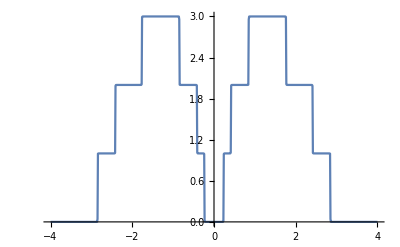

```mathematica
ListLinePlot[Table[{ω,Abs[tr[ω,0.001,1,0]]},{ω,Range[-4,4,0.01]}]]
```

```mathematica
Clear[μ1,μ2,μ3,μ4,μ5,μ6,μ7,μ8]
```

```mathematica
μ1=RandomInteger[{1,7}];μ2=RandomInteger[{1,7}];μ3=RandomInteger[{1,7}];μ4=RandomInteger[{1,7}];μ5=RandomInteger[{1,7}];μ6=RandomInteger[{1,7}];μ7=RandomInteger[{1,7}];μ8=RandomInteger[{1,7}]
```

5

```mathematica
Clear[imp1,imp2,imp3,imp4,imp5,imp6,imp7,imp8,ψ,Sl11,Sl12,Sl13,Sl14,Sl15,Sl16,Sl17,Sl18,gdd1,grr1,Il1,Ir1,Gnonlocal1,GNON1];imp1[ω_,δ_,t_,ϵ_,ϵ1_]:=imp1[ω,δ,t,ϵ,ϵ1]= Inverse[Module[{gg=β[ω,δ,t,ϵ]},ReplacePart[gg,{{μ1,μ1}}->ω+ⅈ*δ-ϵ1]]];imp2[ω_,δ_,t_,ϵ_,ϵ1_]:=imp2[ω,δ,t,ϵ,ϵ1]= Inverse[Module[{gg=β[ω,δ,t,ϵ]},ReplacePart[gg,{{μ2,μ2}}->ω+ⅈ*δ-ϵ]]];imp3[ω_,δ_,t_,ϵ_,ϵ1_]:=imp3[ω,δ,t,ϵ,ϵ1]= Inverse[Module[{gg=β[ω,δ,t,ϵ]},ReplacePart[gg,{{μ3,μ3}}->ω+ⅈ*δ-ϵ1]]];imp4[ω_,δ_,t_,ϵ_,ϵ1_]:=imp4[ω,δ,t,ϵ,ϵ1]= Inverse[Module[{gg=β[ω,δ,t,ϵ]},ReplacePart[gg,{{μ4,μ4}}->ω+ⅈ*δ-ϵ1]]];imp5[ω_,δ_,t_,ϵ_,ϵ1_]:=imp5[ω,δ,t,ϵ,ϵ1]= Inverse[Module[{gg=β[ω,δ,t,ϵ]},ReplacePart[gg,{{μ5,μ5}}->ω+ⅈ*δ-ϵ1]]];imp6[ω_,δ_,t_,ϵ_,ϵ1_]:=imp6[ω,δ,t,ϵ,ϵ1]= Inverse[Module[{gg=β[ω,δ,t,ϵ]},ReplacePart[gg,{{μ6,μ6}}->ω+ⅈ*δ-ϵ1]]];imp7[ω_,δ_,t_,ϵ_,ϵ1_]:=imp7[ω,δ,t,ϵ,ϵ1]= Inverse[Module[{gg=β[ω,δ,t,ϵ]},ReplacePart[gg,{{μ7,μ7}}->ω+ⅈ*δ-ϵ]]];imp8[ω_,δ_,t_,ϵ_,ϵ1_]:=imp8[ω,δ,t,ϵ,ϵ1]= Inverse[Module[{gg=β[ω,δ,t,ϵ]},ReplacePart[gg,{{μ8,μ8}}->ω+ⅈ*δ-ϵ1]]];ψ[ω_,δ_,t_,ϵ_,ϵ1_]:=Module[{g:=Inverse[β[ω,δ,t,ϵ]]},Sl11:=Inverse[IdentityMatrix[7]-imp1[ω,δ,t,ϵ,ϵ1].T1[t].SL[ω,δ,t,ϵ].T1[t]].imp1[ω,δ,t,ϵ,ϵ1];
Sl12:=Inverse[IdentityMatrix[7]-imp2[ω,δ,t,ϵ,ϵ1].T2[t].Sl11.T2[t]].imp2[ω,δ,t,ϵ,ϵ1];
Sl13:=Inverse[IdentityMatrix[7]-imp3[ω,δ,t,ϵ,ϵ1].T1[t].Sl12.T1[t]].imp3[ω,δ,t,ϵ,ϵ1];
Sl14:=Inverse[IdentityMatrix[7]-imp4[ω,δ,t,ϵ,ϵ1].T2[t].Sl13.T2[t]].imp4[ω,δ,t,ϵ,ϵ1];
Sl15:=Inverse[IdentityMatrix[7]-imp5[ω,δ,t,ϵ,ϵ1].T1[t].Sl14.T1[t]].imp5[ω,δ,t,ϵ,ϵ1];
Sl16:=Inverse[IdentityMatrix[7]-imp6[ω,δ,t,ϵ,ϵ1].T2[t].Sl15.T2[t]].imp6[ω,δ,t,ϵ,ϵ1];
Sl17:=Inverse[IdentityMatrix[7]-imp7[ω,δ,t,ϵ,ϵ1].T1[t].Sl16.T1[t]].imp7[ω,δ,t,ϵ,ϵ1];
Sl18:=Inverse[IdentityMatrix[7]-imp8[ω,δ,t,ϵ,ϵ1].T2[t].Sl17.T2[t]].imp8[ω,δ,t,ϵ,ϵ1];
Il1:=Inverse[IdentityMatrix[7]-Sl18.T1[t].SR[ω,δ,t,ϵ].T1[t]].Sl18;
Ir1:=Inverse[IdentityMatrix[7]-SR[ω,δ,t,ϵ].T1[t].Sl18.T1[t]].SR[ω,δ,t,ϵ];
gdd1:= Il1-ConjugateTranspose[Il1];
grr1:= Ir1-ConjugateTranspose[Ir1];
Gnonlocal1:= SR[ω,δ,t,ϵ].T1[t].Il1;
GNON1:= Gnonlocal1-ConjugateTranspose[Gnonlocal1];
Abs[Tr[gdd1.T1[1].grr1.T1[1]-T1[1].GNON1.T1[1].GNON1]]];m1=Table[{ω,ψ[ω,0.001,1,0,0]},{ω,Range[0,4,0.01]}]
```

{{0.,0.0000279995},{0.01,0.0000280805},{0.02,0.000028326},{0.03,0.0000287434},{0.04,0.0000293458},{0.05,0.000030153},{0.06,0.0000311929},{0.07,0.0000325038},{0.08,0.0000341383},{0.09,0.0000361684},{0.1,0.0000386941},{0.11,0.0000418562},{0.12,0.0000458577},{0.13,0.0000509996},{0.14,0.0000577436},{0.15,0.0000668293},{0.16,0.000079504},{0.17,0.0000980155},{0.18,0.000126774},{0.19,0.000175487},{0.2,0.000269296},{0.21,0.000492136},{0.22,0.00128997},{0.23,0.0116162},{0.24,0.991847},{0.25,0.999059},{0.26,0.999686},{0.27,0.999857},{0.28,0.999928},{0.29,0.999963},{0.3,0.999985},{0.31,1.},{0.32,1.00001},{0.33,1.00003},{0.34,1.00004},{0.35,1.00006},{0.36,1.00008},{0.37,1.00013},{0.38,1.00022},{0.39,1.00043},{0.4,1.00124},{0.41,1.01355},{0.42,1.99273},{0.43,1.99901},{0.44,1.99963},{0.45,1.99981},{0.46,1.99988},{0.47,1.99992},{0.48,1.99995},{0.49,1.99996},{0.5,1.99997},{0.51,1.99998},{0.52,1.99998},{0.53,1.99998},{0.54,1.99999},{0.55,1.99999},{0.56,1.99999},{0.57,1.99999},{0.58,1.99999},{0.59,2.},{0.6,2.},{0.61,2.},{0.62,2.},{0.63,2.},{0.64,2.},{0.65,2.},{0.66,2.},{0.67,2.},{0.68,2.00001},{0.69,2.00001},{0.7,2.00001},{0.71,2.00001},{0.72,2.00001},{0.73,2.00001},{0.74,2.00002},{0.75,2.00002},{0.76,2.00003},{0.77,2.00004},{0.78,2.00005},{0.79,2.00007},{0.8,2.00011},{0.81,2.00017},{0.82,2.00032},{0.83,2.00078},{0.84,2.00409},{0.85,2.95656},{0.86,2.99833},{0.87,2.99949},{0.88,2.99976},{0.89,2.99986},{0.9,2.9999},{0.91,2.99993},{0.92,2.99995},{0.93,2.99996},{0.94,2.99997},{0.95,2.99997},{0.96,2.99998},{0.97,2.99998},{0.98,2.99998},{0.99,2.99999},{1.,2.99999},{1.01,2.99999},{1.02,2.99999},{1.03,2.99999},{1.04,2.99999},{1.05,2.99999},{1.06,2.99999},{1.07,2.99999},{1.08,2.99999},{1.09,2.99999},{1.1,2.99999},{1.11,2.99999},{1.12,2.99999},{1.13,2.99999},{1.14,3.},{1.15,3.},{1.16,3.},{1.17,3.},{1.18,3.},{1.19,3.},{1.2,3.},{1.21,3.},{1.22,3.},{1.23,3.},{1.24,3.},{1.25,3.},{1.26,3.},{1.27,3.},{1.28,3.},{1.29,3.},{1.3,3.},{1.31,3.},{1.32,3.},{1.33,3.},{1.34,3.},{1.35,3.},{1.36,3.},{1.37,3.},{1.38,3.},{1.39,3.},{1.4,3.},{1.41,3.},{1.42,3.},{1.43,3.},{1.44,3.},{1.45,3.},{1.46,3.},{1.47,3.},{1.48,2.99999},{1.49,2.99999},{1.5,2.99999},{1.51,2.99999},{1.52,2.99999},{1.53,2.99999},{1.54,2.99999},{1.55,2.99999},{1.56,2.99999},{1.57,2.99999},{1.58,2.99999},{1.59,2.99999},{1.6,2.99999},{1.61,2.99999},{1.62,2.99999},{1.63,2.99998},{1.64,2.99998},{1.65,2.99998},{1.66,2.99998},{1.67,2.99997},{1.68,2.99996},{1.69,2.99995},{1.7,2.99994},{1.71,2.99992},{1.72,2.99988},{1.73,2.9998},{1.74,2.99961},{1.75,2.99894},{1.76,2.99153},{1.77,2.01124},{1.78,2.00116},{1.79,2.00041},{1.8,2.0002},{1.81,2.00012},{1.82,2.00008},{1.83,2.00006},{1.84,2.00004},{1.85,2.00003},{1.86,2.00003},{1.87,2.00002},{1.88,2.00002},{1.89,2.00001},{1.9,2.00001},{1.91,2.00001},{1.92,2.00001},{1.93,2.00001},{1.94,2.00001},{1.95,2.},{1.96,2.},{1.97,2.},{1.98,2.},{1.99,2.},{2.,2.},{2.01,2.},{2.02,2.},{2.03,2.},{2.04,2.},{2.05,2.},{2.06,2.},{2.07,2.},{2.08,2.},{2.09,2.},{2.1,2.},{2.11,2.},{2.12,2.},{2.13,2.},{2.14,2.},{2.15,2.},{2.16,2.},{2.17,2.},{2.18,1.99999},{2.19,1.99999},{2.2,1.99999},{2.21,1.99999},{2.22,1.99999},{2.23,1.99999},{2.24,1.99999},{2.25,1.99999},{2.26,1.99999},{2.27,1.99999},{2.28,1.99998},{2.29,1.99998},{2.3,1.99998},{2.31,1.99997},{2.32,1.99997},{2.33,1.99996},{2.34,1.99995},{2.35,1.99994},{2.36,1.99991},{2.37,1.99987},{2.38,1.99978},{2.39,1.99957},{2.4,1.99875},{2.41,1.98644},{2.42,1.00727},{2.43,1.00099},{2.44,1.00037},{2.45,1.00019},{2.46,1.00011},{2.47,1.00008},{2.48,1.00005},{2.49,1.00004},{2.5,1.00003},{2.51,1.00002},{2.52,1.00002},{2.53,1.00001},{2.54,1.00001},{2.55,1.00001},{2.56,1.00001},{2.57,1.00001},{2.58,1.},{2.59,1.},{2.6,1.},{2.61,1.},{2.62,1.},{2.63,0.999999},{2.64,0.999998},{2.65,0.999996},{2.66,0.999995},{2.67,0.999994},{2.68,0.999993},{2.69,0.999991},{2.7,0.99999},{2.71,0.999988},{2.72,0.999985},{2.73,0.999982},{2.74,0.999979},{2.75,0.999974},{2.76,0.999967},{2.77,0.999958},{2.78,0.999944},{2.79,0.999923},{2.8,0.999888},{2.81,0.999821},{2.82,0.99967},{2.83,0.999199},{2.84,0.995874},{2.85,0.0433182},{2.86,0.00164489},{2.87,0.000496725},{2.88,0.000235194},{2.89,0.000136355},{2.9,0.0000887579},{2.91,0.0000622831},{2.92,0.0000460724},{2.93,0.0000354399},{2.94,0.0000280956},{2.95,0.0000228136},{2.96,0.0000188896},{2.97,0.0000158959},{2.98,0.0000135605},{2.99,0.000011704},{3.,0.000010204},{3.01,8.97489×10^-6},{3.02,7.95521×10^-6},{3.03,7.09997×10^-6},{3.04,6.37564×10^-6},{3.05,5.75681×10^-6},{3.06,5.22393×10^-6},{3.07,4.7618×10^-6},{3.08,4.3584×10^-6},{3.09,4.00418×10^-6},{3.1,3.69145×10^-6},{3.11,3.41396×10^-6},{3.12,3.1666×10^-6},{3.13,2.94516×10^-6},{3.14,2.74612×10^-6},{3.15,2.56655×10^-6},{3.16,2.40399×10^-6},{3.17,2.25635×10^-6},{3.18,2.12186×10^-6},{3.19,1.99898×10^-6},{3.2,1.88643×10^-6},{3.21,1.78306×10^-6},{3.22,1.68791×10^-6},{3.23,1.60011×10^-6},{3.24,1.51894×10^-6},{3.25,1.44374×10^-6},{3.26,1.37393×10^-6},{3.27,1.30901×10^-6},{3.28,1.24853×10^-6},{3.29,1.19209×10^-6},{3.3,1.13935×10^-6},{3.31,1.08998×10^-6},{3.32,1.0437×10^-6},{3.33,1.00026×10^-6},{3.34,9.59429×10^-7},{3.35,9.21004×10^-7},{3.36,8.84799×10^-7},{3.37,8.50644×10^-7},{3.38,8.18388×10^-7},{3.39,7.87893×10^-7},{3.4,7.59032×10^-7},{3.41,7.31691×10^-7},{3.42,7.05764×10^-7},{3.43,6.81156×10^-7},{3.44,6.57779×10^-7},{3.45,6.35552×10^-7},{3.46,6.144×10^-7},{3.47,5.94256×10^-7},{3.48,5.75057×10^-7},{3.49,5.56744×10^-7},{3.5,5.39264×10^-7},{3.51,5.22568×10^-7},{3.52,5.06608×10^-7},{3.53,4.91344×10^-7},{3.54,4.76734×10^-7},{3.55,4.62742×10^-7},{3.56,4.49334×10^-7},{3.57,4.36478×10^-7},{3.58,4.24144×10^-7},{3.59,4.12305×10^-7},{3.6,4.00934×10^-7},{3.61,3.90008×10^-7},{3.62,3.79503×10^-7},{3.63,3.69398×10^-7},{3.64,3.59674×10^-7},{3.65,3.50311×10^-7},{3.66,3.41292×10^-7},{3.67,3.32601×10^-7},{3.68,3.24222×10^-7},{3.69,3.1614×10^-7},{3.7,3.08341×10^-7},{3.71,3.00813×10^-7},{3.72,2.93544×10^-7},{3.73,2.86521×10^-7},{3.74,2.79734×10^-7},{3.75,2.73172×10^-7},{3.76,2.66826×10^-7},{3.77,2.60687×10^-7},{3.78,2.54746×10^-7},{3.79,2.48993×10^-7},{3.8,2.43423×10^-7},{3.81,2.38026×10^-7},{3.82,2.32797×10^-7},{3.83,2.27728×10^-7},{3.84,2.22812×10^-7},{3.85,2.18045×10^-7},{3.86,2.13419×10^-7},{3.87,2.0893×10^-7},{3.88,2.04573×10^-7},{3.89,2.00342×10^-7},{3.9,1.96232×10^-7},{3.91,1.92239×10^-7},{3.92,1.88359×10^-7},{3.93,1.84588×10^-7},{3.94,1.80921×10^-7},{3.95,1.77355×10^-7},{3.96,1.73886×10^-7},{3.97,1.70512×10^-7},{3.98,1.67227×10^-7},{3.99,1.6403×10^-7},{4.,1.60918×10^-7}}

```mathematica
Clear[μ1,μ2,μ3,μ4,μ5,μ6,μ7,μ8]
```

```mathematica
μ1=RandomInteger[{1,7}];μ2=RandomInteger[{1,7}];μ3=RandomInteger[{1,7}];μ4=RandomInteger[{1,7}];μ5=RandomInteger[{1,7}];μ6=RandomInteger[{1,7}];μ7=RandomInteger[{1,7}];μ8=RandomInteger[{1,7}]
```

6

```mathematica
Clear[imp1,imp2,imp3,imp4,imp5,imp6,imp7,imp8,ψ,Sl11,Sl12,Sl13,Sl14,Sl15,Sl16,Sl17,Sl18,gdd1,grr1,Il1,Ir1,Gnonlocal1,GNON1];imp1[ω_,δ_,t_,ϵ_,ϵ1_]:=imp1[ω,δ,t,ϵ,ϵ1]= Inverse[Module[{gg=β[ω,δ,t,ϵ]},ReplacePart[gg,{{μ1,μ1}}->ω+ⅈ*δ-ϵ1]]];imp2[ω_,δ_,t_,ϵ_,ϵ1_]:=imp2[ω,δ,t,ϵ,ϵ1]= Inverse[Module[{gg=β[ω,δ,t,ϵ]},ReplacePart[gg,{{μ2,μ2}}->ω+ⅈ*δ-ϵ1]]];imp3[ω_,δ_,t_,ϵ_,ϵ1_]:=imp3[ω,δ,t,ϵ,ϵ1]= Inverse[Module[{gg=β[ω,δ,t,ϵ]},ReplacePart[gg,{{μ3,μ3}}->ω+ⅈ*δ-ϵ1]]];imp4[ω_,δ_,t_,ϵ_,ϵ1_]:=imp4[ω,δ,t,ϵ,ϵ1]= Inverse[Module[{gg=β[ω,δ,t,ϵ]},ReplacePart[gg,{{μ4,μ4}}->ω+ⅈ*δ-ϵ1]]];imp5[ω_,δ_,t_,ϵ_,ϵ1_]:=imp5[ω,δ,t,ϵ,ϵ1]= Inverse[Module[{gg=β[ω,δ,t,ϵ]},ReplacePart[gg,{{μ5,μ5}}->ω+ⅈ*δ-ϵ1]]];imp6[ω_,δ_,t_,ϵ_,ϵ1_]:=imp6[ω,δ,t,ϵ,ϵ1]= Inverse[Module[{gg=β[ω,δ,t,ϵ]},ReplacePart[gg,{{μ6,μ6}}->ω+ⅈ*δ-ϵ1]]];imp7[ω_,δ_,t_,ϵ_,ϵ1_]:=imp7[ω,δ,t,ϵ,ϵ1]= Inverse[Module[{gg=β[ω,δ,t,ϵ]},ReplacePart[gg,{{μ7,μ7}}->ω+ⅈ*δ-ϵ]]];imp8[ω_,δ_,t_,ϵ_,ϵ1_]:=imp8[ω,δ,t,ϵ,ϵ1]= Inverse[Module[{gg=β[ω,δ,t,ϵ]},ReplacePart[gg,{{μ8,μ8}}->ω+ⅈ*δ-ϵ1]]];ψ[ω_,δ_,t_,ϵ_,ϵ1_]:=Module[{g:=Inverse[β[ω,δ,t,ϵ]]},Sl11:=Inverse[IdentityMatrix[7]-imp1[ω,δ,t,ϵ,ϵ1].T1[t].SL[ω,δ,t,ϵ].T1[t]].imp1[ω,δ,t,ϵ,ϵ1];
Sl12:=Inverse[IdentityMatrix[7]-imp2[ω,δ,t,ϵ,ϵ1].T2[t].Sl11.T2[t]].imp2[ω,δ,t,ϵ,ϵ1];
Sl13:=Inverse[IdentityMatrix[7]-imp3[ω,δ,t,ϵ,ϵ1].T1[t].Sl12.T1[t]].imp3[ω,δ,t,ϵ,ϵ1];
Sl14:=Inverse[IdentityMatrix[7]-imp4[ω,δ,t,ϵ,ϵ1].T2[t].Sl13.T2[t]].imp4[ω,δ,t,ϵ,ϵ1];
Sl15:=Inverse[IdentityMatrix[7]-imp5[ω,δ,t,ϵ,ϵ1].T1[t].Sl14.T1[t]].imp5[ω,δ,t,ϵ,ϵ1];
Sl16:=Inverse[IdentityMatrix[7]-imp6[ω,δ,t,ϵ,ϵ1].T2[t].Sl15.T2[t]].imp6[ω,δ,t,ϵ,ϵ1];
Sl17:=Inverse[IdentityMatrix[7]-imp7[ω,δ,t,ϵ,ϵ1].T1[t].Sl16.T1[t]].imp7[ω,δ,t,ϵ,ϵ1];
Sl18:=Inverse[IdentityMatrix[7]-imp8[ω,δ,t,ϵ,ϵ1].T2[t].Sl17.T2[t]].imp8[ω,δ,t,ϵ,ϵ1];
Il1:=Inverse[IdentityMatrix[7]-Sl18.T1[t].SR[ω,δ,t,ϵ].T1[t]].Sl18;
Ir1:=Inverse[IdentityMatrix[7]-SR[ω,δ,t,ϵ].T1[t].Sl18.T1[t]].SR[ω,δ,t,ϵ];
gdd1:= Il1-ConjugateTranspose[Il1];
grr1:= Ir1-ConjugateTranspose[Ir1];
Gnonlocal1:= SR[ω,δ,t,ϵ].T1[t].Il1;
GNON1:= Gnonlocal1-ConjugateTranspose[Gnonlocal1];
Abs[Tr[gdd1.T1[1].grr1.T1[1]-T1[1].GNON1.T1[1].GNON1]]];m2=Table[{ω,If[ψ[ω,0.001,1,0,0.8]>3,3,ψ[ω,0.001,1,0,0.8]]},{ω,Range[0,4,0.01]}]
```

{{0.,0.0000100615},{0.01,0.0000235984},{0.02,0.0000163517},{0.03,0.0000278237},{0.04,0.000106523},{0.05,0.000218667},{0.06,0.000364368},{0.07,0.000544878},{0.08,0.00076263},{0.09,0.00102136},{0.1,0.00132632},{0.11,0.00168466},{0.12,0.00210594},{0.13,0.00260297},{0.14,0.00319306},{0.15,0.00389993},{0.16,0.0047569},{0.17,0.00581223},{0.18,0.00713867},{0.19,0.00885206},{0.2,0.0111514},{0.21,0.0144193},{0.22,0.0195459},{0.23,0.0296536},{0.24,0.00900288},{0.25,0.11535},{0.26,0.225146},{0.27,0.33356},{0.28,0.436038},{0.29,0.528719},{0.3,0.608949},{0.31,0.675481},{0.32,0.728358},{0.33,0.768583},{0.34,0.797729},{0.35,0.817583},{0.36,0.829882},{0.37,0.836131},{0.38,0.837468},{0.39,0.834478},{0.4,0.826629},{0.41,0.808691},{0.42,0.811127},{0.43,0.845516},{0.44,0.874293},{0.45,0.900441},{0.46,0.925303},{0.47,0.9496},{0.48,0.973733},{0.49,0.997904},{0.5,1.02218},{0.51,1.04653},{0.52,1.07085},{0.53,1.09501},{0.54,1.11883},{0.55,1.14214},{0.56,1.16478},{0.57,1.18663},{0.58,1.20759},{0.59,1.22761},{0.6,1.24669},{0.61,1.26488},{0.62,1.28226},{0.63,1.29895},{0.64,1.31508},{0.65,1.33082},{0.66,1.34634},{0.67,1.36179},{0.68,1.37734},{0.69,1.39313},{0.7,1.40931},{0.71,1.42598},{0.72,1.44323},{0.73,1.46115},{0.74,1.47977},{0.75,1.4991},{0.76,1.5191},{0.77,1.53969},{0.78,1.56073},{0.79,1.58197},{0.8,1.60305},{0.81,1.62338},{0.82,1.64197},{0.83,1.65665},{0.84,1.66071},{0.85,1.6468},{0.86,1.72837},{0.87,1.79378},{0.88,1.84996},{0.89,1.89909},{0.9,1.94226},{0.91,1.98036},{0.92,2.01426},{0.93,2.04475},{0.94,2.07255},{0.95,2.09823},{0.96,2.12219},{0.97,2.14468},{0.98,2.16577},{0.99,2.18532},{1.,2.20282},{1.01,2.21717},{1.02,2.22622},{1.03,2.22609},{1.04,2.21},{1.05,2.16698},{1.06,2.08194},{1.07,1.94214},{1.08,1.75748},{1.09,1.58094},{1.1,1.47817},{1.11,1.46183},{1.12,1.49404},{1.13,1.53628},{1.14,1.57044},{1.15,1.59336},{1.16,1.60806},{1.17,1.61852},{1.18,1.62782},{1.19,1.63775},{1.2,1.64918},{1.21,1.66239},{1.22,1.67736},{1.23,1.69395},{1.24,1.71202},{1.25,1.73142},{1.26,1.75208},{1.27,1.77399},{1.28,1.79718},{1.29,1.82176},{1.3,1.84791},{1.31,1.87591},{1.32,1.90609},{1.33,1.93888},{1.34,1.97477},{1.35,2.01423},{1.36,2.05764},{1.37,2.10505},{1.38,2.15591},{1.39,2.20871},{1.4,2.2607},{1.41,2.3078},{1.42,2.34506},{1.43,2.36772},{1.44,2.37247},{1.45,2.35846},{1.46,2.32748},{1.47,2.28315},{1.48,2.2299},{1.49,2.17188},{1.5,2.11253},{1.51,2.05434},{1.52,1.99896},{1.53,1.94742},{1.54,1.90029},{1.55,1.85784},{1.56,1.82013},{1.57,1.78711},{1.58,1.75866},{1.59,1.73453},{1.6,1.71442},{1.61,1.69795},{1.62,1.68462},{1.63,1.67389},{1.64,1.66518},{1.65,1.65798},{1.66,1.65203},{1.67,1.6476},{1.68,1.64592},{1.69,1.64995},{1.7,1.66559},{1.71,1.70338},{1.72,1.77999},{1.73,1.91322},{1.74,2.08376},{1.75,2.10111},{1.76,1.3697},{1.77,2.23106},{1.78,1.06892},{1.79,0.455329},{1.8,0.311327},{1.81,0.267656},{1.82,0.236593},{1.83,0.197885},{1.84,0.149187},{1.85,0.0923513},{1.86,0.0294827},{1.87,0.0379936},{1.88,0.109335},{1.89,0.184238},{1.9,0.262529},{1.91,0.343856},{1.92,0.42738},{1.93,0.511535},{1.94,0.593967},{1.95,0.671751},{1.96,0.741941},{1.97,0.802293},{1.98,0.85185},{1.99,0.891108},{2.,0.921708},{2.01,0.945857},{2.02,0.965764},{2.03,0.983259},{2.04,0.999629},{2.05,1.01562},{2.06,1.03152},{2.07,1.04726},{2.08,1.06258},{2.09,1.07708},{2.1,1.09036},{2.11,1.10211},{2.12,1.11216},{2.13,1.12057},{2.14,1.12767},{2.15,1.13412},{2.16,1.14086},{2.17,1.14917},{2.18,1.16056},{2.19,1.17666},{2.2,1.19898},{2.21,1.22844},{2.22,1.2645},{2.23,1.30396},{2.24,1.33957},{2.25,1.35971},{2.26,1.35048},{2.27,1.3012},{2.28,1.21002},{2.29,1.08495},{2.3,0.939133},{2.31,0.78461},{2.32,0.628755},{2.33,0.473893},{2.34,0.318294},{2.35,0.15705},{2.36,0.0179549},{2.37,0.219595},{2.38,0.470158},{2.39,0.814962},{2.4,1.37375},{2.41,2.71373},{2.42,3},{2.43,2.38333},{2.44,1.36438},{2.45,0.801581},{2.46,0.539934},{2.47,0.566264},{2.48,0.948458},{2.49,1.68667},{2.5,2.40788},{2.51,2.55073},{2.52,2.12318},{2.53,1.49902},{2.54,0.917486},{2.55,0.475172},{2.56,0.235058},{2.57,0.284831},{2.58,0.749373},{2.59,1.66523},{2.6,2.4188},{2.61,1.89197},{2.62,0.712577},{2.63,0.108027},{2.64,0.513196},{2.65,0.677267},{2.66,0.71961},{2.67,0.703358},{2.68,0.66061},{2.69,0.607703},{2.7,0.552962},{2.71,0.500599},{2.72,0.452713},{2.73,0.410365},{2.74,0.374186},{2.75,0.344745},{2.76,0.322805},{2.77,0.309468},{2.78,0.306083},{2.79,0.313397},{2.8,0.328782},{2.81,0.340565},{2.82,0.324326},{2.83,0.255365},{2.84,0.129604},{2.85,0.00268986},{2.86,0.0348734},{2.87,0.231826},{2.88,1.84525},{2.89,3},{2.9,1.11973},{2.91,0.374396},{2.92,0.189248},{2.93,0.113996},{2.94,0.075243},{2.95,0.0518577},{2.96,0.0343478},{2.97,0.0784584},{2.98,0.0320285},{2.99,0.0235747},{3.,0.0186889},{3.01,0.0152501},{3.02,0.0126651},{3.03,0.0106543},{3.04,0.00905482},{3.05,0.0077612},{3.06,0.00670112},{3.07,0.00582286},{3.08,0.0050884},{3.09,0.00446917},{3.1,0.00394331},{3.11,0.00349387},{3.12,0.00310749},{3.13,0.00277357},{3.14,0.00248359},{3.15,0.00223064},{3.16,0.0020091},{3.17,0.00181431},{3.18,0.00164244},{3.19,0.0014903},{3.2,0.0013552},{3.21,0.00123488},{3.22,0.00112744},{3.23,0.00103124},{3.24,0.000944909},{3.25,0.000867245},{3.26,0.000797228},{3.27,0.000733973},{3.28,0.000676714},{3.29,0.000624785},{3.3,0.000577605},{3.31,0.000534665},{3.32,0.000495521},{3.33,0.00045978},{3.34,0.000427097},{3.35,0.000397167},{3.36,0.00036972},{3.37,0.000344515},{3.38,0.000321341},{3.39,0.000300006},{3.4,0.000280342},{3.41,0.000262196},{3.42,0.000245432},{3.43,0.000229929},{3.44,0.000215576},{3.45,0.000202275},{3.46,0.000189936},{3.47,0.00017848},{3.48,0.000167832},{3.49,0.000157928},{3.5,0.000148708},{3.51,0.000140116},{3.52,0.000132104},{3.53,0.000124626},{3.54,0.000117642},{3.55,0.000111113},{3.56,0.000105007},{3.57,0.0000992907},{3.58,0.0000939363},{3.59,0.0000889174},{3.6,0.0000842098},{3.61,0.0000797915},{3.62,0.0000756419},{3.63,0.0000717424},{3.64,0.0000680758},{3.65,0.0000646261},{3.66,0.0000613785},{3.67,0.0000583197},{3.68,0.000055437},{3.69,0.0000527188},{3.7,0.0000501545},{3.71,0.000047734},{3.72,0.0000454483},{3.73,0.0000432886},{3.74,0.0000412471},{3.75,0.0000393165},{3.76,0.0000374898},{3.77,0.0000357607},{3.78,0.0000341232},{3.79,0.0000325719},{3.8,0.0000311015},{3.81,0.0000297073},{3.82,0.0000283848},{3.83,0.0000271298},{3.84,0.0000259384},{3.85,0.0000248069},{3.86,0.0000237319},{3.87,0.0000227103},{3.88,0.0000217389},{3.89,0.000020815},{3.9,0.000019936},{3.91,0.0000190994},{3.92,0.0000183029},{3.93,0.0000175443},{3.94,0.0000168215},{3.95,0.0000161327},{3.96,0.0000154761},{3.97,0.0000148499},{3.98,0.0000142525},{3.99,0.0000136825},{4.,0.0000131384}}

```mathematica
Clear[μ1,μ2,μ3,μ4,μ5,μ6,μ7,μ8]
```

```mathematica
μ1=RandomInteger[{1,7}];μ2=RandomInteger[{1,7}];μ3=RandomInteger[{1,7}];μ4=RandomInteger[{1,7}];μ5=RandomInteger[{1,7}];μ6=RandomInteger[{1,7}];μ7=RandomInteger[{1,7}];μ8=RandomInteger[{1,7}]
```

5

```mathematica
Clear[imp1,imp2,imp3,imp4,imp5,imp6,imp7,imp8,ψ,Sl11,Sl12,Sl13,Sl14,Sl15,Sl16,Sl17,Sl18,gdd1,grr1,Il1,Ir1,Gnonlocal1,GNON1];imp1[ω_,δ_,t_,ϵ_,ϵ1_]:=imp1[ω,δ,t,ϵ,ϵ1]= Inverse[Module[{gg=β[ω,δ,t,ϵ]},ReplacePart[gg,{{μ1,μ1}}->ω+ⅈ*δ-ϵ1]]];imp2[ω_,δ_,t_,ϵ_,ϵ1_]:=imp2[ω,δ,t,ϵ,ϵ1]= Inverse[Module[{gg=β[ω,δ,t,ϵ]},ReplacePart[gg,{{μ2,μ2}}->ω+ⅈ*δ-ϵ1]]];imp3[ω_,δ_,t_,ϵ_,ϵ1_]:=imp3[ω,δ,t,ϵ,ϵ1]= Inverse[Module[{gg=β[ω,δ,t,ϵ]},ReplacePart[gg,{{μ3,μ3}}->ω+ⅈ*δ-ϵ]]];imp4[ω_,δ_,t_,ϵ_,ϵ1_]:=imp4[ω,δ,t,ϵ,ϵ1]= Inverse[Module[{gg=β[ω,δ,t,ϵ]},ReplacePart[gg,{{μ4,μ4}}->ω+ⅈ*δ-ϵ1]]];imp5[ω_,δ_,t_,ϵ_,ϵ1_]:=imp5[ω,δ,t,ϵ,ϵ1]= Inverse[Module[{gg=β[ω,δ,t,ϵ]},ReplacePart[gg,{{μ5,μ5}}->ω+ⅈ*δ-ϵ1]]];imp6[ω_,δ_,t_,ϵ_,ϵ1_]:=imp6[ω,δ,t,ϵ,ϵ1]= Inverse[Module[{gg=β[ω,δ,t,ϵ]},ReplacePart[gg,{{μ6,μ6}}->ω+ⅈ*δ-ϵ1]]];imp7[ω_,δ_,t_,ϵ_,ϵ1_]:=imp7[ω,δ,t,ϵ,ϵ1]= Inverse[Module[{gg=β[ω,δ,t,ϵ]},ReplacePart[gg,{{μ7,μ7}}->ω+ⅈ*δ-ϵ1]]];imp8[ω_,δ_,t_,ϵ_,ϵ1_]:=imp8[ω,δ,t,ϵ,ϵ1]= Inverse[Module[{gg=β[ω,δ,t,ϵ]},ReplacePart[gg,{{μ8,μ8}}->ω+ⅈ*δ-ϵ1]]];ψ[ω_,δ_,t_,ϵ_,ϵ1_]:=Module[{g:=Inverse[β[ω,δ,t,ϵ]]},Sl11:=Inverse[IdentityMatrix[7]-imp1[ω,δ,t,ϵ,ϵ1].T1[t].SL[ω,δ,t,ϵ].T1[t]].imp1[ω,δ,t,ϵ,ϵ1];
Sl12:=Inverse[IdentityMatrix[7]-imp2[ω,δ,t,ϵ,ϵ1].T2[t].Sl11.T2[t]].imp2[ω,δ,t,ϵ,ϵ1];
Sl13:=Inverse[IdentityMatrix[7]-imp3[ω,δ,t,ϵ,ϵ1].T1[t].Sl12.T1[t]].imp3[ω,δ,t,ϵ,ϵ1];
Sl14:=Inverse[IdentityMatrix[7]-imp4[ω,δ,t,ϵ,ϵ1].T2[t].Sl13.T2[t]].imp4[ω,δ,t,ϵ,ϵ1];
Sl15:=Inverse[IdentityMatrix[7]-imp5[ω,δ,t,ϵ,ϵ1].T1[t].Sl14.T1[t]].imp5[ω,δ,t,ϵ,ϵ1];
Sl16:=Inverse[IdentityMatrix[7]-imp6[ω,δ,t,ϵ,ϵ1].T2[t].Sl15.T2[t]].imp6[ω,δ,t,ϵ,ϵ1];
Sl17:=Inverse[IdentityMatrix[7]-imp7[ω,δ,t,ϵ,ϵ1].T1[t].Sl16.T1[t]].imp7[ω,δ,t,ϵ,ϵ1];
Sl18:=Inverse[IdentityMatrix[7]-imp8[ω,δ,t,ϵ,ϵ1].T2[t].Sl17.T2[t]].imp8[ω,δ,t,ϵ,ϵ1];
Il1:=Inverse[IdentityMatrix[7]-Sl18.T1[t].SR[ω,δ,t,ϵ].T1[t]].Sl18;
Ir1:=Inverse[IdentityMatrix[7]-SR[ω,δ,t,ϵ].T1[t].Sl18.T1[t]].SR[ω,δ,t,ϵ];
gdd1:= Il1-ConjugateTranspose[Il1];
grr1:= Ir1-ConjugateTranspose[Ir1];
Gnonlocal1:= SR[ω,δ,t,ϵ].T1[t].Il1;
GNON1:= Gnonlocal1-ConjugateTranspose[Gnonlocal1];
Abs[Tr[gdd1.T1[1].grr1.T1[1]-T1[1].GNON1.T1[1].GNON1]]];m3=Table[{ω,If[ψ[ω,0.001,1,0,0.8]>3,3,ψ[ω,0.001,1,0,0.8]]},{ω,Range[0,4,0.01]}]
```

{{0.,0.0035297},{0.01,0.00297414},{0.02,0.00250172},{0.03,0.00209757},{0.04,0.00175015},{0.05,0.00145045},{0.06,0.00119148},{0.07,0.000967855},{0.08,0.00077551},{0.09,0.00061156},{0.1,0.000474202},{0.11,0.000362718},{0.12,0.000277573},{0.13,0.000220638},{0.14,0.000195592},{0.15,0.000208613},{0.16,0.000269538},{0.17,0.000393894},{0.18,0.000606574},{0.19,0.000948974},{0.2,0.00149417},{0.21,0.00238384},{0.22,0.00393919},{0.23,0.00712414},{0.24,0.0272326},{0.25,0.0998642},{0.26,0.179296},{0.27,0.265217},{0.28,0.355715},{0.29,0.447782},{0.3,0.537751},{0.31,0.621871},{0.32,0.696912},{0.33,0.760622},{0.34,0.811904},{0.35,0.850693},{0.36,0.877604},{0.37,0.893432},{0.38,0.898517},{0.39,0.891654},{0.4,0.86702},{0.41,0.795653},{0.42,0.676553},{0.43,0.699777},{0.44,0.726851},{0.45,0.754843},{0.46,0.783355},{0.47,0.8122},{0.48,0.841224},{0.49,0.870301},{0.5,0.89935},{0.51,0.928341},{0.52,0.957291},{0.53,0.986255},{0.54,1.01531},{0.55,1.04453},{0.56,1.07398},{0.57,1.10371},{0.58,1.13371},{0.59,1.16395},{0.6,1.19434},{0.61,1.22473},{0.62,1.25493},{0.63,1.28472},{0.64,1.31382},{0.65,1.34193},{0.66,1.36876},{0.67,1.39401},{0.68,1.41741},{0.69,1.43875},{0.7,1.45785},{0.71,1.4746},{0.72,1.48896},{0.73,1.50095},{0.74,1.51063},{0.75,1.51813},{0.76,1.52357},{0.77,1.52709},{0.78,1.52879},{0.79,1.52873},{0.8,1.52682},{0.81,1.52276},{0.82,1.5158},{0.83,1.50414},{0.84,1.48215},{0.85,1.44978},{0.86,1.49478},{0.87,1.52825},{0.88,1.55722},{0.89,1.584},{0.9,1.60973},{0.91,1.63513},{0.92,1.66072},{0.93,1.68695},{0.94,1.71422},{0.95,1.74292},{0.96,1.77347},{0.97,1.80632},{0.98,1.84199},{0.99,1.8811},{1.,1.92435},{1.01,1.97256},{1.02,2.02663},{1.03,2.08738},{1.04,2.15526},{1.05,2.2296},{1.06,2.30694},{1.07,2.37759},{1.08,2.41982},{1.09,2.3944},{1.1,2.25634},{1.11,2.0085},{1.12,1.74646},{1.13,1.57904},{1.14,1.52948},{1.15,1.56058},{1.16,1.63131},{1.17,1.71536},{1.18,1.79885},{1.19,1.87516},{1.2,1.94158},{1.21,1.99745},{1.22,2.04317},{1.23,2.0797},{1.24,2.1082},{1.25,2.1299},{1.26,2.14594},{1.27,2.15736},{1.28,2.16504},{1.29,2.16973},{1.3,2.17203},{1.31,2.17244},{1.32,2.17137},{1.33,2.16916},{1.34,2.16611},{1.35,2.16248},{1.36,2.15851},{1.37,2.15444},{1.38,2.15051},{1.39,2.14693},{1.4,2.14392},{1.41,2.14172},{1.42,2.14052},{1.43,2.1405},{1.44,2.14183},{1.45,2.14461},{1.46,2.14884},{1.47,2.15436},{1.48,2.16074},{1.49,2.16708},{1.5,2.17173},{1.51,2.17196},{1.52,2.16364},{1.53,2.14116},{1.54,2.09807},{1.55,2.02885},{1.56,1.93139},{1.57,1.80876},{1.58,1.66877},{1.59,1.52099},{1.6,1.37349},{1.61,1.23104},{1.62,1.09516},{1.63,0.96512},{1.64,0.83897},{1.65,0.714231},{1.66,0.588245},{1.67,0.458263},{1.68,0.321351},{1.69,0.174181},{1.7,0.0126821},{1.71,0.168535},{1.72,0.377234},{1.73,0.625709},{1.74,0.935989},{1.75,1.35565},{1.76,2.02773},{1.77,1.19414},{1.78,0.221076},{1.79,0.168406},{1.8,0.353421},{1.81,0.416544},{1.82,0.380066},{1.83,0.267303},{1.84,0.12861},{1.85,0.012481},{1.86,0.0638682},{1.87,0.0979318},{1.88,0.0786565},{1.89,0.0183915},{1.9,0.213608},{1.91,0.48626},{1.92,0.76159},{1.93,0.965065},{1.94,1.07598},{1.95,1.11562},{1.96,1.11336},{1.97,1.09087},{1.98,1.06091},{1.99,1.03022},{2.,1.00211},{2.01,0.9781},{2.02,0.958756},{2.03,0.944206},{2.04,0.934354},{2.05,0.929012},{2.06,0.927951},{2.07,0.930932},{2.08,0.93771},{2.09,0.948041},{2.1,0.961674},{2.11,0.978346},{2.12,0.997776},{2.13,1.01966},{2.14,1.04366},{2.15,1.06943},{2.16,1.09658},{2.17,1.12472},{2.18,1.15345},{2.19,1.18238},{2.2,1.21118},{2.21,1.23955},{2.22,1.26727},{2.23,1.29424},{2.24,1.32043},{2.25,1.34588},{2.26,1.37071},{2.27,1.39499},{2.28,1.41869},{2.29,1.44147},{2.3,1.46252},{2.31,1.48025},{2.32,1.492},{2.33,1.49389},{2.34,1.48082},{2.35,1.44713},{2.36,1.38758},{2.37,1.29841},{2.38,1.17702},{2.39,1.01863},{2.4,0.805133},{2.41,0.446691},{2.42,0.188116},{2.43,0.369942},{2.44,0.434407},{2.45,0.394687},{2.46,0.283271},{2.47,0.144436},{2.48,0.0118474},{2.49,0.0947502},{2.5,0.149415},{2.51,0.123187},{2.52,0.430232},{2.53,0.517638},{2.54,0.555069},{2.55,0.585839},{2.56,0.608453},{2.57,0.621199},{2.58,0.622914},{2.59,0.613189},{2.6,0.592571},{2.61,0.562592},{2.62,0.525551},{2.63,0.484119},{2.64,0.440899},{2.65,0.398101},{2.66,0.357363},{2.67,0.319745},{2.68,0.285805},{2.69,0.255727},{2.7,0.22944},{2.71,0.206727},{2.72,0.187297},{2.73,0.170836},{2.74,0.157039},{2.75,0.145625},{2.76,0.136347},{2.77,0.128976},{2.78,0.123288},{2.79,0.119004},{2.8,0.115652},{2.81,0.1122},{2.82,0.105921},{2.83,0.0881745},{2.84,0.0216209},{2.85,0.459753},{2.86,0.372171},{2.87,0.0064483},{2.88,0.000441397},{2.89,0.00337208},{2.9,0.00977838},{2.91,0.0226141},{2.92,0.0788467},{2.93,1.58057},{2.94,0.01102},{2.95,0.000116408},{2.96,0.000642847},{2.97,0.003425},{2.98,0.00813923},{2.99,0.01721},{3.,0.0401164},{3.01,0.137514},{3.02,3},{3.03,0.371625},{3.04,0.0691158},{3.05,0.0274409},{3.06,0.0143115},{3.07,0.00859255},{3.08,0.00562172},{3.09,0.00389727},{3.1,0.00281687},{3.11,0.00210118},{3.12,0.00160655},{3.13,0.00125307},{3.14,0.000993571},{3.15,0.000798774},{3.16,0.000649791},{3.17,0.00053402},{3.18,0.000442813},{3.19,0.000370093},{3.2,0.000311497},{3.21,0.000263839},{3.22,0.00022475},{3.23,0.000192447},{3.24,0.000165568},{3.25,0.000143063},{3.26,0.000124113},{3.27,0.000108072},{3.28,0.0000944275},{3.29,0.0000827697},{3.3,0.0000727677},{3.31,0.000064153},{3.32,0.0000567063},{3.33,0.0000502473},{3.34,0.000044627},{3.35,0.0000397219},{3.36,0.0000354288},{3.37,0.0000316613},{3.38,0.0000283466},{3.39,0.0000254233},{3.4,0.0000228393},{3.41,0.0000205503},{3.42,0.0000185183},{3.43,0.000016711},{3.44,0.0000151005},{3.45,0.0000136627},{3.46,0.000012377},{3.47,0.0000112253},{3.48,0.0000101921},{3.49,9.26379×10^-6},{3.5,8.42845×10^-6},{3.51,7.67575×10^-6},{3.52,6.9966×10^-6},{3.53,6.38302×10^-6},{3.54,5.828×10^-6},{3.55,5.32535×10^-6},{3.56,4.86959×10^-6},{3.57,4.4559×10^-6},{3.58,4.07999×10^-6},{3.59,3.73806×10^-6},{3.6,3.42673×10^-6},{3.61,3.14298×10^-6},{3.62,2.88414×10^-6},{3.63,2.6478×10^-6},{3.64,2.43183×10^-6},{3.65,2.2343×10^-6},{3.66,2.0535×10^-6},{3.67,1.88787×10^-6},{3.68,1.73604×10^-6},{3.69,1.59675×10^-6},{3.7,1.46888×10^-6},{3.71,1.35141×10^-6},{3.72,1.24343×10^-6},{3.73,1.14411×10^-6},{3.74,1.0527×10^-6},{3.75,9.68524×10^-7},{3.76,8.90962×10^-7},{3.77,8.19459×10^-7},{3.78,7.53508×10^-7},{3.79,6.92648×10^-7},{3.8,6.3646×10^-7},{3.81,5.84562×10^-7},{3.82,5.36606×10^-7},{3.83,4.92276×10^-7},{3.84,4.5128×10^-7},{3.85,4.13355×10^-7},{3.86,3.78258×10^-7},{3.87,3.45769×10^-7},{3.88,3.15685×10^-7},{3.89,2.87819×10^-7},{3.9,2.62001×10^-7},{3.91,2.38076×10^-7},{3.92,2.159×10^-7},{3.93,1.95341×10^-7},{3.94,1.76278×10^-7},{3.95,1.586×10^-7},{3.96,1.42204×10^-7},{3.97,1.26995×10^-7},{3.98,1.12887×10^-7},{3.99,9.97991×10^-8},{4.,8.76578×10^-8}}

```mathematica
Clear[μ1,μ2,μ3,μ4,μ5,μ6,μ7,μ8]
```

```mathematica
μ1=RandomInteger[{1,7}];μ2=RandomInteger[{1,7}];μ3=RandomInteger[{1,7}];μ4=RandomInteger[{1,7}];μ5=RandomInteger[{1,7}];μ6=RandomInteger[{1,7}];μ7=RandomInteger[{1,7}];μ8=RandomInteger[{1,7}]
```

3

```mathematica
Clear[imp1,imp2,imp3,imp4,imp5,imp6,imp7,imp8,ψ,Sl11,Sl12,Sl13,Sl14,Sl15,Sl16,Sl17,Sl18,gdd1,grr1,Il1,Ir1,Gnonlocal1,GNON1];imp1[ω_,δ_,t_,ϵ_,ϵ1_]:=imp1[ω,δ,t,ϵ,ϵ1]= Inverse[Module[{gg=β[ω,δ,t,ϵ]},ReplacePart[gg,{{μ1,μ1}}->ω+ⅈ*δ-ϵ1]]];imp2[ω_,δ_,t_,ϵ_,ϵ1_]:=imp2[ω,δ,t,ϵ,ϵ1]= Inverse[Module[{gg=β[ω,δ,t,ϵ]},ReplacePart[gg,{{μ2,μ2}}->ω+ⅈ*δ-ϵ1]]];imp3[ω_,δ_,t_,ϵ_,ϵ1_]:=imp3[ω,δ,t,ϵ,ϵ1]= Inverse[Module[{gg=β[ω,δ,t,ϵ]},ReplacePart[gg,{{μ3,μ3}}->ω+ⅈ*δ-ϵ1]]];imp4[ω_,δ_,t_,ϵ_,ϵ1_]:=imp4[ω,δ,t,ϵ,ϵ1]= Inverse[Module[{gg=β[ω,δ,t,ϵ]},ReplacePart[gg,{{μ4,μ4}}->ω+ⅈ*δ-ϵ1]]];imp5[ω_,δ_,t_,ϵ_,ϵ1_]:=imp5[ω,δ,t,ϵ,ϵ1]= Inverse[Module[{gg=β[ω,δ,t,ϵ]},ReplacePart[gg,{{μ5,μ5}}->ω+ⅈ*δ-ϵ1]]];imp6[ω_,δ_,t_,ϵ_,ϵ1_]:=imp6[ω,δ,t,ϵ,ϵ1]= Inverse[Module[{gg=β[ω,δ,t,ϵ]},ReplacePart[gg,{{μ6,μ6}}->ω+ⅈ*δ-ϵ]]];imp7[ω_,δ_,t_,ϵ_,ϵ1_]:=imp7[ω,δ,t,ϵ,ϵ1]= Inverse[Module[{gg=β[ω,δ,t,ϵ]},ReplacePart[gg,{{μ7,μ7}}->ω+ⅈ*δ-ϵ1]]];imp8[ω_,δ_,t_,ϵ_,ϵ1_]:=imp8[ω,δ,t,ϵ,ϵ1]= Inverse[Module[{gg=β[ω,δ,t,ϵ]},ReplacePart[gg,{{μ8,μ8}}->ω+ⅈ*δ-ϵ1]]];ψ[ω_,δ_,t_,ϵ_,ϵ1_]:=Module[{g:=Inverse[β[ω,δ,t,ϵ]]},Sl11:=Inverse[IdentityMatrix[7]-imp1[ω,δ,t,ϵ,ϵ1].T1[t].SL[ω,δ,t,ϵ].T1[t]].imp1[ω,δ,t,ϵ,ϵ1];
Sl12:=Inverse[IdentityMatrix[7]-imp2[ω,δ,t,ϵ,ϵ1].T2[t].Sl11.T2[t]].imp2[ω,δ,t,ϵ,ϵ1];
Sl13:=Inverse[IdentityMatrix[7]-imp3[ω,δ,t,ϵ,ϵ1].T1[t].Sl12.T1[t]].imp3[ω,δ,t,ϵ,ϵ1];
Sl14:=Inverse[IdentityMatrix[7]-imp4[ω,δ,t,ϵ,ϵ1].T2[t].Sl13.T2[t]].imp4[ω,δ,t,ϵ,ϵ1];
Sl15:=Inverse[IdentityMatrix[7]-imp5[ω,δ,t,ϵ,ϵ1].T1[t].Sl14.T1[t]].imp5[ω,δ,t,ϵ,ϵ1];
Sl16:=Inverse[IdentityMatrix[7]-imp6[ω,δ,t,ϵ,ϵ1].T2[t].Sl15.T2[t]].imp6[ω,δ,t,ϵ,ϵ1];
Sl17:=Inverse[IdentityMatrix[7]-imp7[ω,δ,t,ϵ,ϵ1].T1[t].Sl16.T1[t]].imp7[ω,δ,t,ϵ,ϵ1];
Sl18:=Inverse[IdentityMatrix[7]-imp8[ω,δ,t,ϵ,ϵ1].T2[t].Sl17.T2[t]].imp8[ω,δ,t,ϵ,ϵ1];
Il1:=Inverse[IdentityMatrix[7]-Sl18.T1[t].SR[ω,δ,t,ϵ].T1[t]].Sl18;
Ir1:=Inverse[IdentityMatrix[7]-SR[ω,δ,t,ϵ].T1[t].Sl18.T1[t]].SR[ω,δ,t,ϵ];
gdd1:= Il1-ConjugateTranspose[Il1];
grr1:= Ir1-ConjugateTranspose[Ir1];
Gnonlocal1:= SR[ω,δ,t,ϵ].T1[t].Il1;
GNON1:= Gnonlocal1-ConjugateTranspose[Gnonlocal1];
Abs[Tr[gdd1.T1[1].grr1.T1[1]-T1[1].GNON1.T1[1].GNON1]]];m4=Table[{ω,If[ψ[ω,0.001,1,0,0.8]>3,3,ψ[ω,0.001,1,0,0.8]]},{ω,Range[0,4,0.01]}]
```

{{0.,0.000758356},{0.01,0.000738487},{0.02,0.000738422},{0.03,0.000756446},{0.04,0.000791553},{0.05,0.000843347},{0.06,0.000911987},{0.07,0.000998176},{0.08,0.00110319},{0.09,0.00122894},{0.1,0.00137808},{0.11,0.00155421},{0.12,0.00176213},{0.13,0.00200821},{0.14,0.00230105},{0.15,0.00265238},{0.16,0.00307854},{0.17,0.00360303},{0.18,0.00426082},{0.19,0.00510669},{0.2,0.00623248},{0.21,0.0078086},{0.22,0.0102084},{0.23,0.0145702},{0.24,0.00586856},{0.25,0.0550046},{0.26,0.111574},{0.27,0.176709},{0.28,0.250218},{0.29,0.330514},{0.3,0.414442},{0.31,0.497435},{0.32,0.574183},{0.33,0.639721},{0.34,0.690537},{0.35,0.725218},{0.36,0.744407},{0.37,0.750189},{0.38,0.745266},{0.39,0.732136},{0.4,0.71211},{0.41,0.681136},{0.42,0.657149},{0.43,0.693836},{0.44,0.735218},{0.45,0.777657},{0.46,0.819504},{0.47,0.859724},{0.48,0.897708},{0.49,0.933183},{0.5,0.966122},{0.51,0.996663},{0.52,1.02504},{0.53,1.05154},{0.54,1.07644},{0.55,1.10002},{0.56,1.12251},{0.57,1.14412},{0.58,1.16502},{0.59,1.18534},{0.6,1.20516},{0.61,1.22454},{0.62,1.2435},{0.63,1.26201},{0.64,1.28003},{0.65,1.29748},{0.66,1.31424},{0.67,1.33018},{0.68,1.34513},{0.69,1.35888},{0.7,1.37126},{0.71,1.38204},{0.72,1.39103},{0.73,1.39808},{0.74,1.40305},{0.75,1.40587},{0.76,1.40648},{0.77,1.40486},{0.78,1.40096},{0.79,1.39454},{0.8,1.38505},{0.81,1.3711},{0.82,1.34937},{0.83,1.31103},{0.84,1.22397},{0.85,0.911525},{0.86,0.958407},{0.87,1.03036},{0.88,1.10441},{0.89,1.17821},{0.9,1.25068},{0.91,1.32115},{0.92,1.38925},{0.93,1.45482},{0.94,1.51792},{0.95,1.57878},{0.96,1.63772},{0.97,1.69515},{0.98,1.75144},{0.99,1.80684},{1.,1.86126},{1.01,1.91381},{1.02,1.96205},{1.03,2.00021},{1.04,2.01611},{1.05,1.98628},{1.06,1.87316},{1.07,1.6413},{1.08,1.31343},{1.09,1.00592},{1.1,0.828831},{1.11,0.786366},{1.12,0.824169},{1.13,0.895425},{1.14,0.974662},{1.15,1.04975},{1.16,1.11363},{1.17,1.15947},{1.18,1.17938},{1.19,1.1693},{1.2,1.14031},{1.21,1.11984},{1.22,1.1295},{1.23,1.17094},{1.24,1.23651},{1.25,1.31961},{1.26,1.41491},{1.27,1.51531},{1.28,1.61118},{1.29,1.69283},{1.3,1.75413},{1.31,1.79434},{1.32,1.81686},{1.33,1.8269},{1.34,1.82949},{1.35,1.82857},{1.36,1.82684},{1.37,1.82595},{1.38,1.82677},{1.39,1.82961},{1.4,1.83437},{1.41,1.84065},{1.42,1.84783},{1.43,1.85511},{1.44,1.86153},{1.45,1.86609},{1.46,1.86776},{1.47,1.86564},{1.48,1.85904},{1.49,1.84759},{1.5,1.83135},{1.51,1.81077},{1.52,1.78673},{1.53,1.76037},{1.54,1.73297},{1.55,1.7058},{1.56,1.67995},{1.57,1.65627},{1.58,1.63528},{1.59,1.61717},{1.6,1.60178},{1.61,1.58868},{1.62,1.57709},{1.63,1.56594},{1.64,1.55381},{1.65,1.53884},{1.66,1.51862},{1.67,1.48993},{1.68,1.44852},{1.69,1.38907},{1.7,1.30648},{1.71,1.20124},{1.72,1.0903},{1.73,1.00491},{1.74,0.945931},{1.75,0.854357},{1.76,0.619153},{1.77,0.135719},{1.78,0.572395},{1.79,1.97903},{1.8,3},{1.81,3},{1.82,1.83408},{1.83,0.782309},{1.84,0.101106},{1.85,0.322789},{1.86,0.577084},{1.87,0.709363},{1.88,0.748013},{1.89,0.719765},{1.9,0.657894},{1.91,0.598135},{1.92,0.567453},{1.93,0.577066},{1.94,0.624585},{1.95,0.700579},{1.96,0.793967},{1.97,0.894616},{1.98,0.994059},{1.99,1.08552},{2.,1.16391},{2.01,1.22591},{2.02,1.27016},{2.03,1.29718},{2.04,1.30904},{2.05,1.30878},{2.06,1.29974},{2.07,1.28497},{2.08,1.26693},{2.09,1.24738},{2.1,1.22739},{2.11,1.20757},{2.12,1.18818},{2.13,1.16931},{2.14,1.15096},{2.15,1.13313},{2.16,1.11585},{2.17,1.09918},{2.18,1.08319},{2.19,1.06801},{2.2,1.05376},{2.21,1.04054},{2.22,1.02847},{2.23,1.01763},{2.24,1.00805},{2.25,0.999754},{2.26,0.992693},{2.27,0.986757},{2.28,0.981752},{2.29,0.977368},{2.3,0.973131},{2.31,0.968331},{2.32,0.961909},{2.33,0.952278},{2.34,0.937031},{2.35,0.912466},{2.36,0.872788},{2.37,0.808707},{2.38,0.704811},{2.39,0.533706},{2.4,0.237371},{2.41,0.398263},{2.42,0.249738},{2.43,0.502479},{2.44,0.586508},{2.45,1.39322},{2.46,2.84298},{2.47,1.18732},{2.48,0.472042},{2.49,0.16871},{2.5,0.0896476},{2.51,0.26451},{2.52,0.502096},{2.53,0.0739466},{2.54,0.299902},{2.55,0.48531},{2.56,0.590531},{2.57,0.660029},{2.58,0.710461},{2.59,0.748867},{2.6,0.778609},{2.61,0.801476},{2.62,0.818525},{2.63,0.830451},{2.64,0.837762},{2.65,0.840854},{2.66,0.840041},{2.67,0.83556},{2.68,0.827561},{2.69,0.81609},{2.7,0.801075},{2.71,0.782323},{2.72,0.75952},{2.73,0.732262},{2.74,0.700097},{2.75,0.662597},{2.76,0.619442},{2.77,0.570499},{2.78,0.515869},{2.79,0.455856},{2.8,0.390824},{2.81,0.320876},{2.82,0.245281},{2.83,0.161357},{2.84,0.0617026},{2.85,0.0520809},{2.86,0.109467},{2.87,0.32053},{2.88,3},{2.89,0.985885},{2.9,0.153656},{2.91,0.0555907},{2.92,0.0268285},{2.93,0.014874},{2.94,0.00880548},{2.95,0.00516907},{2.96,0.0022956},{2.97,0.002516},{2.98,0.00621123},{2.99,0.00333465},{3.,0.0023078},{3.01,0.00172228},{3.02,0.00133431},{3.03,0.00105837},{3.04,0.000853817},{3.05,0.000697901},{3.06,0.000576595},{3.07,0.000480688},{3.08,0.000403861},{3.09,0.000341632},{3.1,0.000290747},{3.11,0.000248788},{3.12,0.000213932},{3.13,0.000184785},{3.14,0.000160265},{3.15,0.000139523},{3.16,0.000121891},{3.17,0.000106832},{3.18,0.000093916},{3.19,0.0000827941},{3.2,0.0000731818},{3.21,0.0000648455},{3.22,0.0000575925},{3.23,0.0000512627},{3.24,0.0000457229},{3.25,0.0000408614},{3.26,0.0000365842},{3.27,0.0000328121},{3.28,0.0000294777},{3.29,0.0000265239},{3.3,0.0000239018},{3.31,0.0000215695},{3.32,0.0000194911},{3.33,0.0000176356},{3.34,0.0000159763},{3.35,0.0000144899},{3.36,0.0000131564},{3.37,0.0000119583},{3.38,0.0000108801},{3.39,9.90867×10^-6},{3.4,9.03212×10^-6},{3.41,8.24021×10^-6},{3.42,7.52388×10^-6},{3.43,6.87515×10^-6},{3.44,6.28696×10^-6},{3.45,5.75307×10^-6},{3.46,5.26795×10^-6},{3.47,4.82671×10^-6},{3.48,4.42496×10^-6},{3.49,4.05884×10^-6},{3.5,3.72486×10^-6},{3.51,3.41995×10^-6},{3.52,3.14133×10^-6},{3.53,2.88652×10^-6},{3.54,2.6533×10^-6},{3.55,2.43968×10^-6},{3.56,2.24387×10^-6},{3.57,2.06425×10^-6},{3.58,1.89937×10^-6},{3.59,1.74793×10^-6},{3.6,1.60873×10^-6},{3.61,1.48071×10^-6},{3.62,1.36289×10^-6},{3.63,1.25441×10^-6},{3.64,1.15447×10^-6},{3.65,1.06235×10^-6},{3.66,9.77397×10^-7},{3.67,8.99009×10^-7},{3.68,8.26648×10^-7},{3.69,7.59821×10^-7},{3.7,6.98079×10^-7},{3.71,6.41012×10^-7},{3.72,5.88246×10^-7},{3.73,5.39439×10^-7},{3.74,4.94279×10^-7},{3.75,4.52479×10^-7},{3.76,4.13779×10^-7},{3.77,3.77937×10^-7},{3.78,3.44735×10^-7},{3.79,3.13971×10^-7},{3.8,2.85459×10^-7},{3.81,2.5903×10^-7},{3.82,2.34527×10^-7},{3.83,2.11806×10^-7},{3.84,1.90735×10^-7},{3.85,1.71193×10^-7},{3.86,1.53066×10^-7},{3.87,1.36252×10^-7},{3.88,1.20655×10^-7},{3.89,1.06187×10^-7},{3.9,9.27668×10^-8},{3.91,8.0319×10^-8},{3.92,6.87743×10^-8},{3.93,5.80685×10^-8},{3.94,4.81422×10^-8},{3.95,3.89404×10^-8},{3.96,3.04123×10^-8},{3.97,2.25107×10^-8},{3.98,1.51919×10^-8},{3.99,8.41531×10^-9},{4.,2.14345×10^-9}}

```mathematica
Clear[μ1,μ2,μ3,μ4,μ5,μ6,μ7,μ8]
```

```mathematica
μ1=RandomInteger[{1,7}];μ2=RandomInteger[{1,7}];μ3=RandomInteger[{1,7}];μ4=RandomInteger[{1,7}];μ5=RandomInteger[{1,7}];μ6=RandomInteger[{1,7}];μ7=RandomInteger[{1,7}];μ8=RandomInteger[{1,7}]
```

2

```mathematica
Clear[imp1,imp2,imp3,imp4,imp5,imp6,imp7,imp8,ψ,Sl11,Sl12,Sl13,Sl14,Sl15,Sl16,Sl17,Sl18,gdd1,grr1,Il1,Ir1,Gnonlocal1,GNON1];imp1[ω_,δ_,t_,ϵ_,ϵ1_]:=imp1[ω,δ,t,ϵ,ϵ1]= Inverse[Module[{gg=β[ω,δ,t,ϵ]},ReplacePart[gg,{{μ1,μ1}}->ω+ⅈ*δ-ϵ1]]];imp2[ω_,δ_,t_,ϵ_,ϵ1_]:=imp2[ω,δ,t,ϵ,ϵ1]= Inverse[Module[{gg=β[ω,δ,t,ϵ]},ReplacePart[gg,{{μ2,μ2}}->ω+ⅈ*δ-ϵ1]]];imp3[ω_,δ_,t_,ϵ_,ϵ1_]:=imp3[ω,δ,t,ϵ,ϵ1]= Inverse[Module[{gg=β[ω,δ,t,ϵ]},ReplacePart[gg,{{μ3,μ3}}->ω+ⅈ*δ-ϵ1]]];imp4[ω_,δ_,t_,ϵ_,ϵ1_]:=imp4[ω,δ,t,ϵ,ϵ1]= Inverse[Module[{gg=β[ω,δ,t,ϵ]},ReplacePart[gg,{{μ4,μ4}}->ω+ⅈ*δ-ϵ1]]];imp5[ω_,δ_,t_,ϵ_,ϵ1_]:=imp5[ω,δ,t,ϵ,ϵ1]= Inverse[Module[{gg=β[ω,δ,t,ϵ]},ReplacePart[gg,{{μ5,μ5}}->ω+ⅈ*δ-ϵ]]];imp6[ω_,δ_,t_,ϵ_,ϵ1_]:=imp6[ω,δ,t,ϵ,ϵ1]= Inverse[Module[{gg=β[ω,δ,t,ϵ]},ReplacePart[gg,{{μ6,μ6}}->ω+ⅈ*δ-ϵ1]]];imp7[ω_,δ_,t_,ϵ_,ϵ1_]:=imp7[ω,δ,t,ϵ,ϵ1]= Inverse[Module[{gg=β[ω,δ,t,ϵ]},ReplacePart[gg,{{μ7,μ7}}->ω+ⅈ*δ-ϵ1]]];imp8[ω_,δ_,t_,ϵ_,ϵ1_]:=imp8[ω,δ,t,ϵ,ϵ1]= Inverse[Module[{gg=β[ω,δ,t,ϵ]},ReplacePart[gg,{{μ8,μ8}}->ω+ⅈ*δ-ϵ1]]];ψ[ω_,δ_,t_,ϵ_,ϵ1_]:=Module[{g:=Inverse[β[ω,δ,t,ϵ]]},Sl11:=Inverse[IdentityMatrix[7]-imp1[ω,δ,t,ϵ,ϵ1].T1[t].SL[ω,δ,t,ϵ].T1[t]].imp1[ω,δ,t,ϵ,ϵ1];
Sl12:=Inverse[IdentityMatrix[7]-imp2[ω,δ,t,ϵ,ϵ1].T2[t].Sl11.T2[t]].imp2[ω,δ,t,ϵ,ϵ1];
Sl13:=Inverse[IdentityMatrix[7]-imp3[ω,δ,t,ϵ,ϵ1].T1[t].Sl12.T1[t]].imp3[ω,δ,t,ϵ,ϵ1];
Sl14:=Inverse[IdentityMatrix[7]-imp4[ω,δ,t,ϵ,ϵ1].T2[t].Sl13.T2[t]].imp4[ω,δ,t,ϵ,ϵ1];
Sl15:=Inverse[IdentityMatrix[7]-imp5[ω,δ,t,ϵ,ϵ1].T1[t].Sl14.T1[t]].imp5[ω,δ,t,ϵ,ϵ1];
Sl16:=Inverse[IdentityMatrix[7]-imp6[ω,δ,t,ϵ,ϵ1].T2[t].Sl15.T2[t]].imp6[ω,δ,t,ϵ,ϵ1];
Sl17:=Inverse[IdentityMatrix[7]-imp7[ω,δ,t,ϵ,ϵ1].T1[t].Sl16.T1[t]].imp7[ω,δ,t,ϵ,ϵ1];
Sl18:=Inverse[IdentityMatrix[7]-imp8[ω,δ,t,ϵ,ϵ1].T2[t].Sl17.T2[t]].imp8[ω,δ,t,ϵ,ϵ1];
Il1:=Inverse[IdentityMatrix[7]-Sl18.T1[t].SR[ω,δ,t,ϵ].T1[t]].Sl18;
Ir1:=Inverse[IdentityMatrix[7]-SR[ω,δ,t,ϵ].T1[t].Sl18.T1[t]].SR[ω,δ,t,ϵ];
gdd1:= Il1-ConjugateTranspose[Il1];
grr1:= Ir1-ConjugateTranspose[Ir1];
Gnonlocal1:= SR[ω,δ,t,ϵ].T1[t].Il1;
GNON1:= Gnonlocal1-ConjugateTranspose[Gnonlocal1];
Abs[Tr[gdd1.T1[1].grr1.T1[1]-T1[1].GNON1.T1[1].GNON1]]];m5=Table[{ω,If[ψ[ω,0.001,1,0,0.8]>3,3,ψ[ω,0.001,1,0,0.8]]},{ω,Range[0,4,0.01]}]
```

{{0.,3.49316×10^-6},{0.01,0.0000143261},{0.02,0.0000224558},{0.03,0.000027889},{0.04,0.0000309291},{0.05,0.0000320101},{0.06,0.000031603},{0.07,0.0000301648},{0.08,0.0000281136},{0.09,0.000025817},{0.1,0.0000235905},{0.11,0.0000217017},{0.12,0.0000203786},{0.13,0.0000198248},{0.14,0.0000202436},{0.15,0.0000218791},{0.16,0.0000250893},{0.17,0.0000304839},{0.18,0.0000391926},{0.19,0.0000534225},{0.2,0.0000776854},{0.21,0.000121733},{0.22,0.000207813},{0.23,0.000352513},{0.24,0.0188836},{0.25,0.0567347},{0.26,0.099209},{0.27,0.146446},{0.28,0.19797},{0.29,0.252824},{0.3,0.309648},{0.31,0.366819},{0.32,0.422645},{0.33,0.475566},{0.34,0.524311},{0.35,0.56798},{0.36,0.606028},{0.37,0.638151},{0.38,0.664068},{0.39,0.683091},{0.4,0.692964},{0.41,0.683514},{0.42,0.720344},{0.43,0.814294},{0.44,0.896961},{0.45,0.973313},{0.46,1.04504},{0.47,1.11269},{0.48,1.17616},{0.49,1.23495},{0.5,1.28822},{0.51,1.33495},{0.52,1.37408},{0.53,1.40473},{0.54,1.42631},{0.55,1.43872},{0.56,1.44242},{0.57,1.43834},{0.58,1.42778},{0.59,1.41227},{0.6,1.39333},{0.61,1.37239},{0.62,1.35065},{0.63,1.32909},{0.64,1.30843},{0.65,1.2892},{0.66,1.27173},{0.67,1.25622},{0.68,1.24278},{0.69,1.23143},{0.7,1.22211},{0.71,1.21474},{0.72,1.20916},{0.73,1.20518},{0.74,1.20251},{0.75,1.20074},{0.76,1.19934},{0.77,1.19751},{0.78,1.19412},{0.79,1.18747},{0.8,1.17495},{0.81,1.15226},{0.82,1.1117},{0.83,1.03703},{0.84,0.880639},{0.85,0.58205},{0.86,0.801955},{0.87,0.940639},{0.88,1.04622},{0.89,1.13337},{0.9,1.20867},{0.91,1.27599},{0.92,1.33804},{0.93,1.39711},{0.94,1.4553},{0.95,1.51462},{0.96,1.57688},{0.97,1.64332},{0.98,1.7137},{0.99,1.78481},{1.,1.84868},{1.01,1.89198},{1.02,1.89976},{1.03,1.86404},{1.04,1.79081},{1.05,1.69745},{1.06,1.6029},{1.07,1.52061},{1.08,1.45776},{1.09,1.41777},{1.1,1.40272},{1.11,1.41441},{1.12,1.45388},{1.13,1.51947},{1.14,1.60442},{1.15,1.69635},{1.16,1.78045},{1.17,1.84509},{1.18,1.88551},{1.19,1.90322},{1.2,1.90305},{1.21,1.8903},{1.22,1.8694},{1.23,1.84354},{1.24,1.81486},{1.25,1.78475},{1.26,1.75409},{1.27,1.72348},{1.28,1.69329},{1.29,1.66379},{1.3,1.63516},{1.31,1.60751},{1.32,1.58088},{1.33,1.55527},{1.34,1.53064},{1.35,1.5069},{1.36,1.48392},{1.37,1.46159},{1.38,1.43978},{1.39,1.41839},{1.4,1.39734},{1.41,1.37667},{1.42,1.35646},{1.43,1.33693},{1.44,1.3184},{1.45,1.3013},{1.46,1.28615},{1.47,1.27349},{1.48,1.26384},{1.49,1.25764},{1.5,1.25514},{1.51,1.2564},{1.52,1.26124},{1.53,1.26923},{1.54,1.27974},{1.55,1.29198},{1.56,1.30503},{1.57,1.31793},{1.58,1.32966},{1.59,1.33926},{1.6,1.34579},{1.61,1.34843},{1.62,1.34648},{1.63,1.33948},{1.64,1.32725},{1.65,1.31006},{1.66,1.28872},{1.67,1.26462},{1.68,1.23974},{1.69,1.2164},{1.7,1.1967},{1.71,1.18173},{1.72,1.17012},{1.73,1.15596},{1.74,1.12419},{1.75,1.03744},{1.76,0.769192},{1.77,0.216103},{1.78,1.62295},{1.79,3},{1.8,3},{1.81,0.815152},{1.82,0.065203},{1.83,0.377851},{1.84,0.442885},{1.85,0.345741},{1.86,0.121482},{1.87,0.102387},{1.88,0.00648513},{1.89,0.549593},{1.9,1.11042},{1.91,1.45678},{1.92,1.62255},{1.93,1.67784},{1.94,1.66944},{1.95,1.62527},{1.96,1.56242},{1.97,1.4916},{1.98,1.41939},{1.99,1.34959},{2.,1.28418},{2.01,1.22395},{2.02,1.16903},{2.03,1.11917},{2.04,1.07394},{2.05,1.03289},{2.06,0.99556},{2.07,0.961567},{2.08,0.93058},{2.09,0.902339},{2.1,0.876653},{2.11,0.853399},{2.12,0.832524},{2.13,0.814042},{2.14,0.798047},{2.15,0.78472},{2.16,0.774353},{2.17,0.767371},{2.18,0.764378},{2.19,0.766207},{2.2,0.773998},{2.21,0.789279},{2.22,0.814064},{2.23,0.850894},{2.24,0.902732},{2.25,0.972442},{2.26,1.06138},{2.27,1.16661},{2.28,1.27678},{2.29,1.36975},{2.3,1.41753},{2.31,1.40068},{2.32,1.32036},{2.33,1.19484},{2.34,1.04541},{2.35,0.886043},{2.36,0.721407},{2.37,0.549305},{2.38,0.364355},{2.39,0.163029},{2.4,0.0504165},{2.41,0.278568},{2.42,0.0082876},{2.43,0.0980674},{2.44,0.0803226},{2.45,0.0386204},{2.46,0.0282189},{2.47,0.108139},{2.48,0.312548},{2.49,0.594941},{2.5,0.838725},{2.51,0.933824},{2.52,0.800104},{2.53,0.355809},{2.54,0.458326},{2.55,1.48538},{2.56,2.20047},{2.57,2.23031},{2.58,1.79484},{2.59,1.24731},{2.6,0.756132},{2.61,0.359224},{2.62,0.0495096},{2.63,0.188745},{2.64,0.36972},{2.65,0.504485},{2.66,0.601595},{2.67,0.66794},{2.68,0.709349},{2.69,0.730922},{2.7,0.737176},{2.71,0.732074},{2.72,0.719031},{2.73,0.70092},{2.74,0.68011},{2.75,0.658512},{2.76,0.637657},{2.77,0.61875},{2.78,0.602704},{2.79,0.590073},{2.8,0.580717},{2.81,0.572691},{2.82,0.558509},{2.83,0.511144},{2.84,0.319905},{2.85,0.0248137},{2.86,0.0087803},{2.87,0.0620499},{2.88,0.1843},{2.89,0.579456},{2.9,3},{2.91,3},{2.92,1.27868},{2.93,0.415855},{2.94,0.202207},{2.95,0.117569},{2.96,0.0753183},{2.97,0.0509065},{2.98,0.0349552},{2.99,0.0224396},{3.,0.00508672},{3.01,0.0433961},{3.02,0.0227027},{3.03,0.0166866},{3.04,0.0131997},{3.05,0.0107867},{3.06,0.00898872},{3.07,0.00759399},{3.08,0.00648391},{3.09,0.00558398},{3.1,0.00484402},{3.11,0.00422859},{3.12,0.00371179},{3.13,0.00327423},{3.14,0.00290109},{3.15,0.00258084},{3.16,0.0023044},{3.17,0.00206454},{3.18,0.00185544},{3.19,0.00167235},{3.2,0.0015114},{3.21,0.00136939},{3.22,0.00124365},{3.23,0.00113197},{3.24,0.00103247},{3.25,0.000943582},{3.26,0.000863954},{3.27,0.000792446},{3.28,0.000728078},{3.29,0.000670007},{3.3,0.000617507},{3.31,0.000569946},{3.32,0.000526778},{3.33,0.000487525},{3.34,0.000451769},{3.35,0.000419146},{3.36,0.000389332},{3.37,0.000362044},{3.38,0.000337032},{3.39,0.000314074},{3.4,0.000292972},{3.41,0.000273551},{3.42,0.000255655},{3.43,0.000239145},{3.44,0.000223894},{3.45,0.000209792},{3.46,0.000196738},{3.47,0.000184641},{3.48,0.00017342},{3.49,0.000163001},{3.5,0.000153318},{3.51,0.00014431},{3.52,0.000135923},{3.53,0.000128107},{3.54,0.000120818},{3.55,0.000114014},{3.56,0.000107658},{3.57,0.000101716},{3.58,0.0000961575},{3.59,0.0000909528},{3.6,0.0000860766},{3.61,0.0000815049},{3.62,0.0000772159},{3.63,0.0000731893},{3.64,0.0000694069},{3.65,0.0000658515},{3.66,0.0000625075},{3.67,0.0000593605},{3.68,0.0000563971},{3.69,0.0000536052},{3.7,0.0000509732},{3.71,0.0000484908},{3.72,0.0000461482},{3.73,0.0000439364},{3.74,0.000041847},{3.75,0.0000398723},{3.76,0.000038005},{3.77,0.0000362386},{3.78,0.0000345668},{3.79,0.0000329839},{3.8,0.0000314843},{3.81,0.0000300632},{3.82,0.0000287158},{3.83,0.0000274378},{3.84,0.0000262252},{3.85,0.000025074},{3.86,0.0000239809},{3.87,0.0000229423},{3.88,0.0000219554},{3.89,0.000021017},{3.9,0.0000201246},{3.91,0.0000192756},{3.92,0.0000184675},{3.93,0.0000176982},{3.94,0.0000169655},{3.95,0.0000162674},{3.96,0.0000156021},{3.97,0.0000149679},{3.98,0.0000143631},{3.99,0.0000137861},{4.,0.0000132356}}

```mathematica
Clear[μ1,μ2,μ3,μ4,μ5,μ6,μ7,μ8]
```

```mathematica
μ1=RandomInteger[{1,7}];μ2=RandomInteger[{1,7}];μ3=RandomInteger[{1,7}];μ4=RandomInteger[{1,7}];μ5=RandomInteger[{1,7}];μ6=RandomInteger[{1,7}];μ7=RandomInteger[{1,7}];μ8=RandomInteger[{1,7}]
```

4

```mathematica
Clear[imp1,imp2,imp3,imp4,imp5,imp6,imp7,imp8,ψ,Sl11,Sl12,Sl13,Sl14,Sl15,Sl16,Sl17,Sl18,gdd1,grr1,Il1,Ir1,Gnonlocal1,GNON1];imp1[ω_,δ_,t_,ϵ_,ϵ1_]:=imp1[ω,δ,t,ϵ,ϵ1]= Inverse[Module[{gg=β[ω,δ,t,ϵ]},ReplacePart[gg,{{μ1,μ1}}->ω+ⅈ*δ-ϵ1]]];imp2[ω_,δ_,t_,ϵ_,ϵ1_]:=imp2[ω,δ,t,ϵ,ϵ1]= Inverse[Module[{gg=β[ω,δ,t,ϵ]},ReplacePart[gg,{{μ2,μ2}}->ω+ⅈ*δ-ϵ1]]];imp3[ω_,δ_,t_,ϵ_,ϵ1_]:=imp3[ω,δ,t,ϵ,ϵ1]= Inverse[Module[{gg=β[ω,δ,t,ϵ]},ReplacePart[gg,{{μ3,μ3}}->ω+ⅈ*δ-ϵ1]]];imp4[ω_,δ_,t_,ϵ_,ϵ1_]:=imp4[ω,δ,t,ϵ,ϵ1]= Inverse[Module[{gg=β[ω,δ,t,ϵ]},ReplacePart[gg,{{μ4,μ4}}->ω+ⅈ*δ-ϵ1]]];imp5[ω_,δ_,t_,ϵ_,ϵ1_]:=imp5[ω,δ,t,ϵ,ϵ1]= Inverse[Module[{gg=β[ω,δ,t,ϵ]},ReplacePart[gg,{{μ5,μ5}}->ω+ⅈ*δ-ϵ]]];imp6[ω_,δ_,t_,ϵ_,ϵ1_]:=imp6[ω,δ,t,ϵ,ϵ1]= Inverse[Module[{gg=β[ω,δ,t,ϵ]},ReplacePart[gg,{{μ6,μ6}}->ω+ⅈ*δ-ϵ1]]];imp7[ω_,δ_,t_,ϵ_,ϵ1_]:=imp7[ω,δ,t,ϵ,ϵ1]= Inverse[Module[{gg=β[ω,δ,t,ϵ]},ReplacePart[gg,{{μ7,μ7}}->ω+ⅈ*δ-ϵ1]]];imp8[ω_,δ_,t_,ϵ_,ϵ1_]:=imp8[ω,δ,t,ϵ,ϵ1]= Inverse[Module[{gg=β[ω,δ,t,ϵ]},ReplacePart[gg,{{μ8,μ8}}->ω+ⅈ*δ-ϵ1]]];ψ[ω_,δ_,t_,ϵ_,ϵ1_]:=Module[{g:=Inverse[β[ω,δ,t,ϵ]]},Sl11:=Inverse[IdentityMatrix[7]-imp1[ω,δ,t,ϵ,ϵ1].T1[t].SL[ω,δ,t,ϵ].T1[t]].imp1[ω,δ,t,ϵ,ϵ1];
Sl12:=Inverse[IdentityMatrix[7]-imp2[ω,δ,t,ϵ,ϵ1].T2[t].Sl11.T2[t]].imp2[ω,δ,t,ϵ,ϵ1];
Sl13:=Inverse[IdentityMatrix[7]-imp3[ω,δ,t,ϵ,ϵ1].T1[t].Sl12.T1[t]].imp3[ω,δ,t,ϵ,ϵ1];
Sl14:=Inverse[IdentityMatrix[7]-imp4[ω,δ,t,ϵ,ϵ1].T2[t].Sl13.T2[t]].imp4[ω,δ,t,ϵ,ϵ1];
Sl15:=Inverse[IdentityMatrix[7]-imp5[ω,δ,t,ϵ,ϵ1].T1[t].Sl14.T1[t]].imp5[ω,δ,t,ϵ,ϵ1];
Sl16:=Inverse[IdentityMatrix[7]-imp6[ω,δ,t,ϵ,ϵ1].T2[t].Sl15.T2[t]].imp6[ω,δ,t,ϵ,ϵ1];
Sl17:=Inverse[IdentityMatrix[7]-imp7[ω,δ,t,ϵ,ϵ1].T1[t].Sl16.T1[t]].imp7[ω,δ,t,ϵ,ϵ1];
Sl18:=Inverse[IdentityMatrix[7]-imp8[ω,δ,t,ϵ,ϵ1].T2[t].Sl17.T2[t]].imp8[ω,δ,t,ϵ,ϵ1];
Il1:=Inverse[IdentityMatrix[7]-Sl18.T1[t].SR[ω,δ,t,ϵ].T1[t]].Sl18;
Ir1:=Inverse[IdentityMatrix[7]-SR[ω,δ,t,ϵ].T1[t].Sl18.T1[t]].SR[ω,δ,t,ϵ];
gdd1:= Il1-ConjugateTranspose[Il1];
grr1:= Ir1-ConjugateTranspose[Ir1];
Gnonlocal1:= SR[ω,δ,t,ϵ].T1[t].Il1;
GNON1:= Gnonlocal1-ConjugateTranspose[Gnonlocal1];
Abs[Tr[gdd1.T1[1].grr1.T1[1]-T1[1].GNON1.T1[1].GNON1]]];m6=Table[{ω,If[ψ[ω,0.001,1,0,0.8]>3,3,ψ[ω,0.001,1,0,0.8]]},{ω,Range[0,4,0.01]}]
```

{{0.,0.00184506},{0.01,0.00132178},{0.02,0.000929084},{0.03,0.000637235},{0.04,0.000425129},{0.05,0.000277696},{0.06,0.000184213},{0.07,0.000137192},{0.08,0.000131652},{0.09,0.000164663},{0.1,0.000235078},{0.11,0.000343436},{0.12,0.000492005},{0.13,0.000684988},{0.14,0.000928926},{0.15,0.00123337},{0.16,0.00161196},{0.17,0.00208419},{0.18,0.00267826},{0.19,0.0034361},{0.2,0.00442265},{0.21,0.00574512},{0.22,0.00760064},{0.23,0.010437},{0.24,0.00726575},{0.25,0.00294236},{0.26,0.0163432},{0.27,0.0349067},{0.28,0.0612126},{0.29,0.0988388},{0.3,0.152446},{0.31,0.227049},{0.32,0.325291},{0.33,0.441787},{0.34,0.557565},{0.35,0.644493},{0.36,0.683198},{0.37,0.67565},{0.38,0.637506},{0.39,0.583349},{0.4,0.517731},{0.41,0.418328},{0.42,0.397435},{0.43,0.552546},{0.44,0.67858},{0.45,0.785545},{0.46,0.879808},{0.47,0.965486},{0.48,1.04541},{0.49,1.12158},{0.5,1.19545},{0.51,1.26796},{0.52,1.3396},{0.53,1.41035},{0.54,1.47957},{0.55,1.546},{0.56,1.60777},{0.57,1.6625},{0.58,1.70771},{0.59,1.74126},{0.6,1.76187},{0.61,1.76944},{0.62,1.76508},{0.63,1.75085},{0.64,1.72926},{0.65,1.70288},{0.66,1.67395},{0.67,1.64423},{0.68,1.615},{0.69,1.58708},{0.7,1.56092},{0.71,1.53671},{0.72,1.51447},{0.73,1.49403},{0.74,1.47514},{0.75,1.45738},{0.76,1.4402},{0.77,1.42278},{0.78,1.40389},{0.79,1.38158},{0.8,1.35251},{0.81,1.31059},{0.82,1.24343},{0.83,1.12114},{0.84,0.842154},{0.85,0.0400502},{0.86,0.180251},{0.87,0.425189},{0.88,0.673299},{0.89,0.924301},{0.9,1.17287},{0.91,1.41068},{0.92,1.62859},{0.93,1.81888},{0.94,1.97712},{0.95,2.10292},{0.96,2.19955},{0.97,2.27285},{0.98,2.33007},{0.99,2.37934},{1.,2.4299},{1.01,2.49301},{1.02,2.5807},{1.03,2.68446},{1.04,2.67175},{1.05,2.31828},{1.06,1.91979},{1.07,1.70366},{1.08,1.57399},{1.09,1.40681},{1.1,1.02091},{1.11,1.02546},{1.12,1.02805},{1.13,1.03397},{1.14,0.969889},{1.15,0.784124},{1.16,0.570733},{1.17,0.517133},{1.18,0.635214},{1.19,0.80377},{1.2,0.952313},{1.21,1.06728},{1.22,1.15424},{1.23,1.22133},{1.24,1.27527},{1.25,1.32096},{1.26,1.36192},{1.27,1.40074},{1.28,1.43934},{1.29,1.47918},{1.3,1.52139},{1.31,1.56684},{1.32,1.61614},{1.33,1.66961},{1.34,1.72727},{1.35,1.78878},{1.36,1.85329},{1.37,1.91948},{1.38,1.98547},{1.39,2.04884},{1.4,2.10682},{1.41,2.15645},{1.42,2.1949},{1.43,2.21977},{1.44,2.22938},{1.45,2.22296},{1.46,2.2007},{1.47,2.16368},{1.48,2.11369},{1.49,2.053},{1.5,1.98404},{1.51,1.90922},{1.52,1.83067},{1.53,1.75014},{1.54,1.66898},{1.55,1.5881},{1.56,1.50804},{1.57,1.42907},{1.58,1.35124},{1.59,1.27448},{1.6,1.19867},{1.61,1.12373},{1.62,1.04966},{1.63,0.976618},{1.64,0.904891},{1.65,0.834873},{1.66,0.766957},{1.67,0.701359},{1.68,0.637867},{1.69,0.575552},{1.7,0.512422},{1.71,0.444986},{1.72,0.367542},{1.73,0.270699},{1.74,0.137602},{1.75,0.0681359},{1.76,0.466123},{1.77,1.48047},{1.78,2.47556},{1.79,3},{1.8,3},{1.81,3},{1.82,3},{1.83,1.7002},{1.84,0.907926},{1.85,0.383271},{1.86,0.000682933},{1.87,0.239044},{1.88,0.112076},{1.89,0.919211},{1.9,2.63375},{1.91,3},{1.92,2.79462},{1.93,2.10054},{1.94,1.45272},{1.95,0.905628},{1.96,0.463022},{1.97,0.116501},{1.98,0.147703},{1.99,0.345489},{2.,0.492123},{2.01,0.600574},{2.02,0.681028},{2.03,0.741122},{2.04,0.786456},{2.05,0.821123},{2.06,0.848141},{2.07,0.869775},{2.08,0.88775},{2.09,0.903395},{2.1,0.917731},{2.11,0.931528},{2.12,0.945338},{2.13,0.95952},{2.14,0.974256},{2.15,0.989567},{2.16,1.00534},{2.17,1.02136},{2.18,1.03733},{2.19,1.05297},{2.2,1.06802},{2.21,1.08233},{2.22,1.09589},{2.23,1.10885},{2.24,1.12148},{2.25,1.13416},{2.26,1.14722},{2.27,1.16081},{2.28,1.17476},{2.29,1.18832},{2.3,1.20009},{2.31,1.20788},{2.32,1.20886},{2.33,1.19988},{2.34,1.17801},{2.35,1.14121},{2.36,1.08868},{2.37,1.02068},{2.38,0.937481},{2.39,0.836968},{2.4,0.708743},{2.41,0.50874},{2.42,0.102943},{2.43,1.4554},{2.44,3},{2.45,0.826316},{2.46,0.0348154},{2.47,0.267393},{2.48,0.361544},{2.49,0.372155},{2.5,0.199297},{2.51,0.107107},{2.52,0.127899},{2.53,0.385255},{2.54,0.549399},{2.55,0.666756},{2.56,0.754539},{2.57,0.814764},{2.58,0.845224},{2.59,0.845322},{2.6,0.818577},{2.61,0.77212},{2.62,0.714418},{2.63,0.653032},{2.64,0.593468},{2.65,0.539102},{2.66,0.491671},{2.67,0.451884},{2.68,0.419941},{2.69,0.395921},{2.7,0.380073},{2.71,0.373072},{2.72,0.376316},{2.73,0.392339},{2.74,0.425412},{2.75,0.48219},{2.76,0.571276},{2.77,0.696243},{2.78,0.826988},{2.79,0.856935},{2.8,0.69514},{2.81,0.443665},{2.82,0.23319},{2.83,0.084844},{2.84,0.0263765},{2.85,0.129993},{2.86,0.235903},{2.87,0.465826},{2.88,1.23211},{2.89,3},{2.9,3},{2.91,0.875424},{2.92,2.57977},{2.93,0.631945},{2.94,0.30253},{2.95,0.17923},{2.96,0.118453},{2.97,0.0837846},{2.98,0.0620957},{2.99,0.0476257},{3.,0.0375013},{3.01,0.030152},{3.02,0.0246585},{3.03,0.0204527},{3.04,0.0171679},{3.05,0.0145588},{3.06,0.0124561},{3.07,0.0107402},{3.08,0.00932455},{3.09,0.00814515},{3.1,0.00715406},{3.11,0.00631477},{3.12,0.00559905},{3.13,0.00498486},{3.14,0.00445474},{3.15,0.00399478},{3.16,0.00359377},{3.17,0.0032426},{3.18,0.0029338},{3.19,0.00266123},{3.2,0.00241978},{3.21,0.00220519},{3.22,0.00201388},{3.23,0.00184283},{3.24,0.00168948},{3.25,0.00155164},{3.26,0.00142745},{3.27,0.0013153},{3.28,0.00121379},{3.29,0.00112174},{3.3,0.0010381},{3.31,0.000961961},{3.32,0.000892524},{3.33,0.000829096},{3.34,0.000771063},{3.35,0.000717885},{3.36,0.000669083},{3.37,0.000624235},{3.38,0.000582964},{3.39,0.000544937},{3.4,0.000509854},{3.41,0.000477449},{3.42,0.000447482},{3.43,0.00041974},{3.44,0.00039403},{3.45,0.000370178},{3.46,0.000348028},{3.47,0.000327439},{3.48,0.000308282},{3.49,0.000290443},{3.5,0.000273815},{3.51,0.000258304},{3.52,0.000243822},{3.53,0.000230291},{3.54,0.000217638},{3.55,0.000205798},{3.56,0.000194709},{3.57,0.000184318},{3.58,0.000174573},{3.59,0.000165429},{3.6,0.000156841},{3.61,0.000148773},{3.62,0.000141186},{3.63,0.000134049},{3.64,0.000127331},{3.65,0.000121003},{3.66,0.000115039},{3.67,0.000109416},{3.68,0.000104111},{3.69,0.0000991036},{3.7,0.0000943745},{3.71,0.0000899061},{3.72,0.0000856819},{3.73,0.0000816867},{3.74,0.0000779063},{3.75,0.0000743276},{3.76,0.0000709382},{3.77,0.0000677267},{3.78,0.0000646825},{3.79,0.0000617956},{3.8,0.0000590569},{3.81,0.0000564575},{3.82,0.0000539896},{3.83,0.0000516454},{3.84,0.000049418},{3.85,0.0000473007},{3.86,0.0000452873},{3.87,0.0000433722},{3.88,0.0000415497},{3.89,0.0000398149},{3.9,0.0000381629},{3.91,0.0000365893},{3.92,0.0000350898},{3.93,0.0000336606},{3.94,0.0000322978},{3.95,0.000030998},{3.96,0.0000297578},{3.97,0.0000285743},{3.98,0.0000274444},{3.99,0.0000263654},{4.,0.0000253348}}

```mathematica
Clear[μ1,μ2,μ3,μ4,μ5,μ6,μ7,μ8]
```

```mathematica
μ1=RandomInteger[{1,7}];μ2=RandomInteger[{1,7}];μ3=RandomInteger[{1,7}];μ4=RandomInteger[{1,7}];μ5=RandomInteger[{1,7}];μ6=RandomInteger[{1,7}];μ7=RandomInteger[{1,7}];μ8=RandomInteger[{1,7}]
```

4

```mathematica
Clear[imp1,imp2,imp3,imp4,imp5,imp6,imp7,imp8,ψ,Sl11,Sl12,Sl13,Sl14,Sl15,Sl16,Sl17,Sl18,gdd1,grr1,Il1,Ir1,Gnonlocal1,GNON1];imp1[ω_,δ_,t_,ϵ_,ϵ1_]:=imp1[ω,δ,t,ϵ,ϵ1]= Inverse[Module[{gg=β[ω,δ,t,ϵ]},ReplacePart[gg,{{μ1,μ1}}->ω+ⅈ*δ-ϵ1]]];imp2[ω_,δ_,t_,ϵ_,ϵ1_]:=imp2[ω,δ,t,ϵ,ϵ1]= Inverse[Module[{gg=β[ω,δ,t,ϵ]},ReplacePart[gg,{{μ2,μ2}}->ω+ⅈ*δ-ϵ1]]];imp3[ω_,δ_,t_,ϵ_,ϵ1_]:=imp3[ω,δ,t,ϵ,ϵ1]= Inverse[Module[{gg=β[ω,δ,t,ϵ]},ReplacePart[gg,{{μ3,μ3}}->ω+ⅈ*δ-ϵ1]]];imp4[ω_,δ_,t_,ϵ_,ϵ1_]:=imp4[ω,δ,t,ϵ,ϵ1]= Inverse[Module[{gg=β[ω,δ,t,ϵ]},ReplacePart[gg,{{μ4,μ4}}->ω+ⅈ*δ-ϵ1]]];imp5[ω_,δ_,t_,ϵ_,ϵ1_]:=imp5[ω,δ,t,ϵ,ϵ1]= Inverse[Module[{gg=β[ω,δ,t,ϵ]},ReplacePart[gg,{{μ5,μ5}}->ω+ⅈ*δ-ϵ1]]];imp6[ω_,δ_,t_,ϵ_,ϵ1_]:=imp6[ω,δ,t,ϵ,ϵ1]= Inverse[Module[{gg=β[ω,δ,t,ϵ]},ReplacePart[gg,{{μ6,μ6}}->ω+ⅈ*δ-ϵ1]]];imp7[ω_,δ_,t_,ϵ_,ϵ1_]:=imp7[ω,δ,t,ϵ,ϵ1]= Inverse[Module[{gg=β[ω,δ,t,ϵ]},ReplacePart[gg,{{μ7,μ7}}->ω+ⅈ*δ-ϵ]]];imp8[ω_,δ_,t_,ϵ_,ϵ1_]:=imp8[ω,δ,t,ϵ,ϵ1]= Inverse[Module[{gg=β[ω,δ,t,ϵ]},ReplacePart[gg,{{μ8,μ8}}->ω+ⅈ*δ-ϵ1]]];ψ[ω_,δ_,t_,ϵ_,ϵ1_]:=Module[{g:=Inverse[β[ω,δ,t,ϵ]]},Sl11:=Inverse[IdentityMatrix[7]-imp1[ω,δ,t,ϵ,ϵ1].T1[t].SL[ω,δ,t,ϵ].T1[t]].imp1[ω,δ,t,ϵ,ϵ1];
Sl12:=Inverse[IdentityMatrix[7]-imp2[ω,δ,t,ϵ,ϵ1].T2[t].Sl11.T2[t]].imp2[ω,δ,t,ϵ,ϵ1];
Sl13:=Inverse[IdentityMatrix[7]-imp3[ω,δ,t,ϵ,ϵ1].T1[t].Sl12.T1[t]].imp3[ω,δ,t,ϵ,ϵ1];
Sl14:=Inverse[IdentityMatrix[7]-imp4[ω,δ,t,ϵ,ϵ1].T2[t].Sl13.T2[t]].imp4[ω,δ,t,ϵ,ϵ1];
Sl15:=Inverse[IdentityMatrix[7]-imp5[ω,δ,t,ϵ,ϵ1].T1[t].Sl14.T1[t]].imp5[ω,δ,t,ϵ,ϵ1];
Sl16:=Inverse[IdentityMatrix[7]-imp6[ω,δ,t,ϵ,ϵ1].T2[t].Sl15.T2[t]].imp6[ω,δ,t,ϵ,ϵ1];
Sl17:=Inverse[IdentityMatrix[7]-imp7[ω,δ,t,ϵ,ϵ1].T1[t].Sl16.T1[t]].imp7[ω,δ,t,ϵ,ϵ1];
Sl18:=Inverse[IdentityMatrix[7]-imp8[ω,δ,t,ϵ,ϵ1].T2[t].Sl17.T2[t]].imp8[ω,δ,t,ϵ,ϵ1];
Il1:=Inverse[IdentityMatrix[7]-Sl18.T1[t].SR[ω,δ,t,ϵ].T1[t]].Sl18;
Ir1:=Inverse[IdentityMatrix[7]-SR[ω,δ,t,ϵ].T1[t].Sl18.T1[t]].SR[ω,δ,t,ϵ];
gdd1:= Il1-ConjugateTranspose[Il1];
grr1:= Ir1-ConjugateTranspose[Ir1];
Gnonlocal1:= SR[ω,δ,t,ϵ].T1[t].Il1;
GNON1:= Gnonlocal1-ConjugateTranspose[Gnonlocal1];
Abs[Tr[gdd1.T1[1].grr1.T1[1]-T1[1].GNON1.T1[1].GNON1]]];m7=Table[{ω,If[ψ[ω,0.001,1,0,0.8]>3,3,ψ[ω,0.001,1,0,0.8]]},{ω,Range[0,4,0.01]}]
```

{{0.,0.0000227951},{0.01,9.88903×10^-6},{0.02,0.0000150188},{0.03,0.0000511742},{0.04,0.0000980981},{0.05,0.000155547},{0.06,0.000223485},{0.07,0.000302076},{0.08,0.000391673},{0.09,0.000492831},{0.1,0.000606318},{0.11,0.000733143},{0.12,0.000874595},{0.13,0.0010323},{0.14,0.0012083},{0.15,0.00140517},{0.16,0.00162616},{0.17,0.00187544},{0.18,0.00215847},{0.19,0.00248246},{0.2,0.00285722},{0.21,0.00329632},{0.22,0.00381729},{0.23,0.00440266},{0.24,0.00310261},{0.25,0.0185047},{0.26,0.0379072},{0.27,0.0628573},{0.28,0.0950379},{0.29,0.136321},{0.3,0.188589},{0.31,0.2533},{0.32,0.330752},{0.33,0.419119},{0.34,0.513644},{0.35,0.606649},{0.36,0.688839},{0.37,0.751422},{0.38,0.787331},{0.39,0.788954},{0.4,0.73499},{0.41,0.486554},{0.42,0.25641},{0.43,0.678868},{0.44,0.889108},{0.45,1.0138},{0.46,1.0965},{0.47,1.15611},{0.48,1.20218},{0.49,1.24002},{0.5,1.27284},{0.51,1.30262},{0.52,1.33065},{0.53,1.35778},{0.54,1.38457},{0.55,1.41135},{0.56,1.43831},{0.57,1.46553},{0.58,1.49298},{0.59,1.52054},{0.6,1.54807},{0.61,1.57534},{0.62,1.60213},{0.63,1.62817},{0.64,1.65321},{0.65,1.677},{0.66,1.69931},{0.67,1.71994},{0.68,1.73869},{0.69,1.75541},{0.7,1.76992},{0.71,1.78208},{0.72,1.79174},{0.73,1.79873},{0.74,1.80287},{0.75,1.80398},{0.76,1.80185},{0.77,1.79627},{0.78,1.78702},{0.79,1.77382},{0.8,1.75633},{0.81,1.73395},{0.82,1.70549},{0.83,1.66796},{0.84,1.61121},{0.85,1.50594},{0.86,1.54304},{0.87,1.57572},{0.88,1.60485},{0.89,1.63218},{0.9,1.65884},{0.91,1.68577},{0.92,1.71391},{0.93,1.74432},{0.94,1.77829},{0.95,1.81745},{0.96,1.86389},{0.97,1.9203},{0.98,1.98993},{0.99,2.0764},{1.,2.18253},{1.01,2.30713},{1.02,2.43802},{1.03,2.54233},{1.04,2.56437},{1.05,2.44374},{1.06,2.14728},{1.07,1.72884},{1.08,1.34813},{1.09,1.11357},{1.1,1.01224},{1.11,0.995197},{1.12,1.02729},{1.13,1.0893},{1.14,1.17089},{1.15,1.26589},{1.16,1.37007},{1.17,1.48027},{1.18,1.59408},{1.19,1.70963},{1.2,1.82516},{1.21,1.93846},{1.22,2.04629},{1.23,2.14423},{1.24,2.22705},{1.25,2.28996},{1.26,2.32999},{1.27,2.34697},{1.28,2.3435},{1.29,2.32404},{1.3,2.29374},{1.31,2.25744},{1.32,2.21912},{1.33,2.18182},{1.34,2.14771},{1.35,2.11826},{1.36,2.09449},{1.37,2.07709},{1.38,2.0665},{1.39,2.06292},{1.4,2.0662},{1.41,2.07569},{1.42,2.0898},{1.43,2.1056},{1.44,2.11838},{1.45,2.12177},{1.46,2.10887},{1.47,2.07463},{1.48,2.01833},{1.49,1.94434},{1.5,1.86021},{1.51,1.77356},{1.52,1.68976},{1.53,1.61142},{1.54,1.53895},{1.55,1.47139},{1.56,1.40719},{1.57,1.3446},{1.58,1.28195},{1.59,1.21777},{1.6,1.15078},{1.61,1.08},{1.62,1.0047},{1.63,0.924455},{1.64,0.839152},{1.65,0.748979},{1.66,0.654406},{1.67,0.556113},{1.68,0.454832},{1.69,0.351051},{1.7,0.244513},{1.71,0.133322},{1.72,0.0123208},{1.73,0.13013},{1.74,0.319646},{1.75,0.618702},{1.76,1.25092},{1.77,3},{1.78,3},{1.79,3},{1.8,3},{1.81,3},{1.82,3},{1.83,3},{1.84,3},{1.85,3},{1.86,3},{1.87,3},{1.88,3},{1.89,3},{1.9,2.292},{1.91,0.043567},{1.92,0.740291},{1.93,1.05132},{1.94,1.20957},{1.95,1.30322},{1.96,1.35728},{1.97,1.38195},{1.98,1.38476},{1.99,1.37251},{2.,1.35099},{2.01,1.32465},{2.02,1.29671},{2.03,1.26929},{2.04,1.24377},{2.05,1.22095},{2.06,1.20127},{2.07,1.18491},{2.08,1.17192},{2.09,1.16222},{2.1,1.15566},{2.11,1.15205},{2.12,1.15112},{2.13,1.15254},{2.14,1.15591},{2.15,1.16073},{2.16,1.16635},{2.17,1.17199},{2.18,1.17671},{2.19,1.17941},{2.2,1.17888},{2.21,1.17388},{2.22,1.16329},{2.23,1.14627},{2.24,1.12247},{2.25,1.09218},{2.26,1.05636},{2.27,1.01654},{2.28,0.974659},{2.29,0.932719},{2.3,0.892566},{2.31,0.855671},{2.32,0.823018},{2.33,0.795068},{2.34,0.771742},{2.35,0.752363},{2.36,0.735437},{2.37,0.718035},{2.38,0.694055},{2.39,0.648559},{2.4,0.532146},{2.41,0.00272618},{2.42,1.32443},{2.43,0.0889173},{2.44,0.175469},{2.45,0.149536},{2.46,0.0799388},{2.47,0.0227003},{2.48,0.131686},{2.49,0.0585337},{2.5,0.515377},{2.51,0.894653},{2.52,0.896711},{2.53,0.821665},{2.54,0.751904},{2.55,0.697548},{2.56,0.656834},{2.57,0.627032},{2.58,0.606038},{2.59,0.592403},{2.6,0.585163},{2.61,0.583682},{2.62,0.587538},{2.63,0.596439},{2.64,0.610145},{2.65,0.628405},{2.66,0.650884},{2.67,0.677088},{2.68,0.706291},{2.69,0.737479},{2.7,0.769328},{2.71,0.800251},{2.72,0.828523},{2.73,0.852499},{2.74,0.870872},{2.75,0.882899},{2.76,0.888519},{2.77,0.888266},{2.78,0.88297},{2.79,0.873143},{2.8,0.857871},{2.81,0.832484},{2.82,0.782842},{2.83,0.669762},{2.84,0.385531},{2.85,0.0231125},{2.86,0.00114479},{2.87,0.00824788},{2.88,0.0325003},{2.89,0.0833277},{2.9,0.209339},{2.91,0.666096},{2.92,3},{2.93,3},{2.94,1.03832},{2.95,0.377524},{2.96,0.195633},{2.97,0.119682},{2.98,0.0805087},{2.99,0.0575022},{3.,0.0426928},{3.01,0.0323774},{3.02,0.0243635},{3.03,0.0152203},{3.04,0.0307984},{3.05,0.018607},{3.06,0.014785},{3.07,0.0123047},{3.08,0.010451},{3.09,0.00898971},{3.1,0.00780497},{3.11,0.00682685},{3.12,0.00600853},{3.13,0.00531672},{3.14,0.00472679},{3.15,0.00422003},{3.16,0.0037819},{3.17,0.00340096},{3.18,0.00306803},{3.19,0.00277574},{3.2,0.00251802},{3.21,0.00228993},{3.22,0.00208733},{3.23,0.00190678},{3.24,0.00174539},{3.25,0.00160071},{3.26,0.00147067},{3.27,0.0013535},{3.28,0.00124766},{3.29,0.00115186},{3.3,0.00106496},{3.31,0.000985969},{3.32,0.00091404},{3.33,0.000848423},{3.34,0.000788462},{3.35,0.000733581},{3.36,0.000683271},{3.37,0.000637084},{3.38,0.000594621},{3.39,0.00055553},{3.4,0.000519496},{3.41,0.000486239},{3.42,0.000455507},{3.43,0.000427077},{3.44,0.000400747},{3.45,0.000376335},{3.46,0.000353679},{3.47,0.000332632},{3.48,0.000313059},{3.49,0.000294842},{3.5,0.000277871},{3.51,0.000262047},{3.52,0.000247281},{3.53,0.000233489},{3.54,0.000220598},{3.55,0.00020854},{3.56,0.000197252},{3.57,0.000186677},{3.58,0.000176764},{3.59,0.000167465},{3.6,0.000158735},{3.61,0.000150535},{3.62,0.000142828},{3.63,0.00013558},{3.64,0.000128758},{3.65,0.000122335},{3.66,0.000116284},{3.67,0.000110579},{3.68,0.000105199},{3.69,0.000100121},{3.7,0.000095327},{3.71,0.0000907982},{3.72,0.0000865181},{3.73,0.0000824708},{3.74,0.000078642},{3.75,0.0000750181},{3.76,0.0000715867},{3.77,0.0000683361},{3.78,0.0000652554},{3.79,0.0000623344},{3.8,0.0000595638},{3.81,0.0000569348},{3.82,0.000054439},{3.83,0.0000520689},{3.84,0.0000498171},{3.85,0.0000476771},{3.86,0.0000456424},{3.87,0.0000437073},{3.88,0.0000418661},{3.89,0.0000401137},{3.9,0.0000384452},{3.91,0.0000368561},{3.92,0.0000353421},{3.93,0.0000338992},{3.94,0.0000325236},{3.95,0.0000312117},{3.96,0.0000299602},{3.97,0.0000287659},{3.98,0.000027626},{3.99,0.0000265375},{4.,0.0000254979}}

```mathematica
Clear[μ1,μ2,μ3,μ4,μ5,μ6,μ7,μ8]
```

```mathematica
μ1=RandomInteger[{1,7}];μ2=RandomInteger[{1,7}];μ3=RandomInteger[{1,7}];μ4=RandomInteger[{1,7}];μ5=RandomInteger[{1,7}];μ6=RandomInteger[{1,7}];μ7=RandomInteger[{1,7}];μ8=RandomInteger[{1,7}]
```

7

```mathematica
Clear[imp1,imp2,imp3,imp4,imp5,imp6,imp7,imp8,ψ,Sl11,Sl12,Sl13,Sl14,Sl15,Sl16,Sl17,Sl18,gdd1,grr1,Il1,Ir1,Gnonlocal1,GNON1];imp1[ω_,δ_,t_,ϵ_,ϵ1_]:=imp1[ω,δ,t,ϵ,ϵ1]= Inverse[Module[{gg=β[ω,δ,t,ϵ]},ReplacePart[gg,{{μ1,μ1}}->ω+ⅈ*δ-ϵ1]]];imp2[ω_,δ_,t_,ϵ_,ϵ1_]:=imp2[ω,δ,t,ϵ,ϵ1]= Inverse[Module[{gg=β[ω,δ,t,ϵ]},ReplacePart[gg,{{μ2,μ2}}->ω+ⅈ*δ-ϵ1]]];imp3[ω_,δ_,t_,ϵ_,ϵ1_]:=imp3[ω,δ,t,ϵ,ϵ1]= Inverse[Module[{gg=β[ω,δ,t,ϵ]},ReplacePart[gg,{{μ3,μ3}}->ω+ⅈ*δ-ϵ1]]];imp4[ω_,δ_,t_,ϵ_,ϵ1_]:=imp4[ω,δ,t,ϵ,ϵ1]= Inverse[Module[{gg=β[ω,δ,t,ϵ]},ReplacePart[gg,{{μ4,μ4}}->ω+ⅈ*δ-ϵ1]]];imp5[ω_,δ_,t_,ϵ_,ϵ1_]:=imp5[ω,δ,t,ϵ,ϵ1]= Inverse[Module[{gg=β[ω,δ,t,ϵ]},ReplacePart[gg,{{μ5,μ5}}->ω+ⅈ*δ-ϵ1]]];imp6[ω_,δ_,t_,ϵ_,ϵ1_]:=imp6[ω,δ,t,ϵ,ϵ1]= Inverse[Module[{gg=β[ω,δ,t,ϵ]},ReplacePart[gg,{{μ6,μ6}}->ω+ⅈ*δ-ϵ]]];imp7[ω_,δ_,t_,ϵ_,ϵ1_]:=imp7[ω,δ,t,ϵ,ϵ1]= Inverse[Module[{gg=β[ω,δ,t,ϵ]},ReplacePart[gg,{{μ7,μ7}}->ω+ⅈ*δ-ϵ1]]];imp8[ω_,δ_,t_,ϵ_,ϵ1_]:=imp8[ω,δ,t,ϵ,ϵ1]= Inverse[Module[{gg=β[ω,δ,t,ϵ]},ReplacePart[gg,{{μ8,μ8}}->ω+ⅈ*δ-ϵ1]]];ψ[ω_,δ_,t_,ϵ_,ϵ1_]:=Module[{g:=Inverse[β[ω,δ,t,ϵ]]},Sl11:=Inverse[IdentityMatrix[7]-imp1[ω,δ,t,ϵ,ϵ1].T1[t].SL[ω,δ,t,ϵ].T1[t]].imp1[ω,δ,t,ϵ,ϵ1];
Sl12:=Inverse[IdentityMatrix[7]-imp2[ω,δ,t,ϵ,ϵ1].T2[t].Sl11.T2[t]].imp2[ω,δ,t,ϵ,ϵ1];
Sl13:=Inverse[IdentityMatrix[7]-imp3[ω,δ,t,ϵ,ϵ1].T1[t].Sl12.T1[t]].imp3[ω,δ,t,ϵ,ϵ1];
Sl14:=Inverse[IdentityMatrix[7]-imp4[ω,δ,t,ϵ,ϵ1].T2[t].Sl13.T2[t]].imp4[ω,δ,t,ϵ,ϵ1];
Sl15:=Inverse[IdentityMatrix[7]-imp5[ω,δ,t,ϵ,ϵ1].T1[t].Sl14.T1[t]].imp5[ω,δ,t,ϵ,ϵ1];
Sl16:=Inverse[IdentityMatrix[7]-imp6[ω,δ,t,ϵ,ϵ1].T2[t].Sl15.T2[t]].imp6[ω,δ,t,ϵ,ϵ1];
Sl17:=Inverse[IdentityMatrix[7]-imp7[ω,δ,t,ϵ,ϵ1].T1[t].Sl16.T1[t]].imp7[ω,δ,t,ϵ,ϵ1];
Sl18:=Inverse[IdentityMatrix[7]-imp8[ω,δ,t,ϵ,ϵ1].T2[t].Sl17.T2[t]].imp8[ω,δ,t,ϵ,ϵ1];
Il1:=Inverse[IdentityMatrix[7]-Sl18.T1[t].SR[ω,δ,t,ϵ].T1[t]].Sl18;
Ir1:=Inverse[IdentityMatrix[7]-SR[ω,δ,t,ϵ].T1[t].Sl18.T1[t]].SR[ω,δ,t,ϵ];
gdd1:= Il1-ConjugateTranspose[Il1];
grr1:= Ir1-ConjugateTranspose[Ir1];
Gnonlocal1:= SR[ω,δ,t,ϵ].T1[t].Il1;
GNON1:= Gnonlocal1-ConjugateTranspose[Gnonlocal1];
Abs[Tr[gdd1.T1[1].grr1.T1[1]-T1[1].GNON1.T1[1].GNON1]]];m8=Table[{ω,If[ψ[ω,0.001,1,0,0.8]>3,3,ψ[ω,0.001,1,0,0.8]]},{ω,Range[0,4,0.01]}]
```

{{0.,0.00510277},{0.01,0.00362546},{0.02,0.00247951},{0.03,0.00160195},{0.04,0.000947036},{0.05,0.000481974},{0.06,0.000184173},{0.07,0.000039405},{0.08,0.0000407514},{0.09,0.00018817},{0.1,0.000488651},{0.11,0.00095701},{0.12,0.00161747},{0.13,0.00250636},{0.14,0.0036764},{0.15,0.00520372},{0.16,0.00719935},{0.17,0.00982882},{0.18,0.0133477},{0.19,0.0181706},{0.2,0.0250202},{0.21,0.0353015},{0.22,0.0523175},{0.23,0.0881099},{0.24,0.112227},{0.25,0.0508402},{0.26,0.00714733},{0.27,0.0607937},{0.28,0.110159},{0.29,0.155192},{0.3,0.195632},{0.31,0.230984},{0.32,0.260506},{0.33,0.28318},{0.34,0.297664},{0.35,0.302188},{0.36,0.294329},{0.37,0.270515},{0.38,0.224861},{0.39,0.146083},{0.4,0.00698159},{0.41,0.298068},{0.42,0.44393},{0.43,0.178243},{0.44,0.0112423},{0.45,0.16255},{0.46,0.290476},{0.47,0.402606},{0.48,0.503467},{0.49,0.596025},{0.5,0.682342},{0.51,0.763915},{0.52,0.841856},{0.53,0.917002},{0.54,0.989981},{0.55,1.06125},{0.56,1.13113},{0.57,1.19981},{0.58,1.26734},{0.59,1.33367},{0.6,1.39859},{0.61,1.46181},{0.62,1.52288},{0.63,1.58124},{0.64,1.63623},{0.65,1.68712},{0.66,1.73312},{0.67,1.77347},{0.68,1.80747},{0.69,1.83456},{0.7,1.85435},{0.71,1.86669},{0.72,1.87168},{0.73,1.86966},{0.74,1.86121},{0.75,1.84707},{0.76,1.82808},{0.77,1.80513},{0.78,1.77901},{0.79,1.75038},{0.8,1.71954},{0.81,1.68624},{0.82,1.64898},{0.83,1.60289},{0.84,1.52861},{0.85,1.32855},{0.86,1.40821},{0.87,1.48677},{0.88,1.55661},{0.89,1.61858},{0.9,1.67328},{0.91,1.72125},{0.92,1.76305},{0.93,1.79932},{0.94,1.83069},{0.95,1.85778},{0.96,1.88115},{0.97,1.9013},{0.98,1.91857},{0.99,1.93316},{1.,1.94496},{1.01,1.95343},{1.02,1.9572},{1.03,1.95352},{1.04,1.93735},{1.05,1.90052},{1.06,1.83268},{1.07,1.72809},{1.08,1.59807},{1.09,1.47299},{1.1,1.37999},{1.11,1.3243},{1.12,1.29671},{1.13,1.2878},{1.14,1.2939},{1.15,1.31729},{1.16,1.36373},{1.17,1.43077},{1.18,1.46486},{1.19,1.34669},{1.2,1.12954},{1.21,0.990639},{1.22,0.951664},{1.23,0.980835},{1.24,1.05991},{1.25,1.17802},{1.26,1.31861},{1.27,1.45506},{1.28,1.56065},{1.29,1.62367},{1.3,1.65025},{1.31,1.6545},{1.32,1.64924},{1.33,1.64279},{1.34,1.63959},{1.35,1.64163},{1.36,1.64963},{1.37,1.66372},{1.38,1.68389},{1.39,1.71015},{1.4,1.74266},{1.41,1.7818},{1.42,1.82821},{1.43,1.88282},{1.44,1.94678},{1.45,2.02115},{1.46,2.10624},{1.47,2.1999},{1.48,2.29465},{1.49,2.37434},{1.5,2.41471},{1.51,2.39474},{1.52,2.31453},{1.53,2.19845},{1.54,2.077},{1.55,1.96962},{1.56,1.88262},{1.57,1.81467},{1.58,1.76189},{1.59,1.72032},{1.6,1.68675},{1.61,1.65879},{1.62,1.63475},{1.63,1.61348},{1.64,1.59414},{1.65,1.57617},{1.66,1.55914},{1.67,1.54262},{1.68,1.52612},{1.69,1.50883},{1.7,1.48922},{1.71,1.46407},{1.72,1.42628},{1.73,1.35906},{1.74,1.22044},{1.75,0.89906},{1.76,0.0623717},{1.77,2.11642},{1.78,1.33462},{1.79,0.225745},{1.8,0.286572},{1.81,0.759116},{1.82,1.25151},{1.83,1.45216},{1.84,1.61913},{1.85,1.81914},{1.86,2.06022},{1.87,2.32772},{1.88,2.58869},{1.89,2.79059},{1.9,2.86739},{1.91,2.76127},{1.92,2.45509},{1.93,1.99003},{1.94,1.44769},{1.95,0.910537},{1.96,0.433715},{1.97,0.0406509},{1.98,0.26734},{1.99,0.499875},{2.,0.669966},{2.01,0.790241},{2.02,0.871536},{2.03,0.922665},{2.04,0.950653},{2.05,0.961086},{2.06,0.958426},{2.07,0.946264},{2.08,0.927493},{2.09,0.904429},{2.1,0.878908},{2.11,0.852354},{2.12,0.825847},{2.13,0.800182},{2.14,0.775922},{2.15,0.753452},{2.16,0.73302},{2.17,0.714772},{2.18,0.698781},{2.19,0.685072},{2.2,0.673636},{2.21,0.664441},{2.22,0.657446},{2.23,0.6526},{2.24,0.649849},{2.25,0.649136},{2.26,0.650397},{2.27,0.653561},{2.28,0.658547},{2.29,0.665251},{2.3,0.673538},{2.31,0.683227},{2.32,0.694064},{2.33,0.705687},{2.34,0.71756},{2.35,0.728858},{2.36,0.738253},{2.37,0.743429},{2.38,0.739949},{2.39,0.717967},{2.4,0.649993},{2.41,0.408226},{2.42,3},{2.43,3},{2.44,0.708172},{2.45,0.154908},{2.46,1.12112},{2.47,0.50449},{2.48,0.953628},{2.49,0.964487},{2.5,0.950856},{2.51,0.936907},{2.52,0.92343},{2.53,0.910328},{2.54,0.897844},{2.55,0.88662},{2.56,0.877112},{2.57,0.820791},{2.58,0.632568},{2.59,0.767998},{2.6,0.778992},{2.61,0.7778},{2.62,0.774338},{2.63,0.771137},{2.64,0.76922},{2.65,0.769139},{2.66,0.771256},{2.67,0.775838},{2.68,0.783089},{2.69,0.79316},{2.7,0.806134},{2.71,0.821997},{2.72,0.840596},{2.73,0.861563},{2.74,0.884225},{2.75,0.907482},{2.76,0.92968},{2.77,0.948492},{2.78,0.960867},{2.79,0.963091},{2.8,0.950946},{2.81,0.919744},{2.82,0.86333},{2.83,0.768392},{2.84,0.579568},{2.85,0.0928302},{2.86,0.0771198},{2.87,0.0165973},{2.88,0.00732584},{2.89,0.00410175},{2.9,0.00258334},{2.91,0.00174152},{2.92,0.00122206},{2.93,0.000871965},{2.94,0.000607686},{2.95,0.000339138},{2.96,0.00111463},{2.97,0.000533394},{2.98,0.000395462},{2.99,0.000308617},{3.,0.000249128},{3.01,0.00020505},{3.02,0.000170999},{3.03,0.000144013},{3.04,0.000122246},{3.05,0.000104455},{3.06,0.0000897589},{3.07,0.0000775139},{3.08,0.000067235},{3.09,0.0000585502},{3.1,0.0000511704},{3.11,0.000044867},{3.12,0.000039458},{3.13,0.0000347969},{3.14,0.0000307645},{3.15,0.0000272636},{3.16,0.000024214},{3.17,0.0000215493},{3.18,0.0000192142},{3.19,0.0000171625},{3.2,0.0000153551},{3.21,0.0000137592},{3.22,0.0000123469},{3.23,0.0000110944},{3.24,9.98136×10^-6},{3.25,8.99045×10^-6},{3.26,8.10666×10^-6},{3.27,7.31705×10^-6},{3.28,6.61046×10^-6},{3.29,5.97717×10^-6},{3.3,5.40875×10^-6},{3.31,4.89785×10^-6},{3.32,4.43802×10^-6},{3.33,4.02365×10^-6},{3.34,3.64978×10^-6},{3.35,3.31207×10^-6},{3.36,3.00668×10^-6},{3.37,2.73023×10^-6},{3.38,2.47973×10^-6},{3.39,2.25253×10^-6},{3.4,2.04626×10^-6},{3.41,1.85885×10^-6},{3.42,1.68842×10^-6},{3.43,1.53332×10^-6},{3.44,1.39207×10^-6},{3.45,1.26333×10^-6},{3.46,1.14591×10^-6},{3.47,1.03877×10^-6},{3.48,9.40928×10^-7},{3.49,8.51541×10^-7},{3.5,7.69832×10^-7},{3.51,6.95105×10^-7},{3.52,6.26734×10^-7},{3.53,5.64151×10^-7},{3.54,5.06844×10^-7},{3.55,4.54351×10^-7},{3.56,4.06253×10^-7},{3.57,3.62169×10^-7},{3.58,3.21756×10^-7},{3.59,2.847×10^-7},{3.6,2.50717×10^-7},{3.61,2.19548×10^-7},{3.62,1.90959×10^-7},{3.63,1.64734×10^-7},{3.64,1.4068×10^-7},{3.65,1.18617×10^-7},{3.66,9.83824×10^-8},{3.67,7.98284×10^-8},{3.68,6.28187×10^-8},{3.69,4.72293×10^-8},{3.7,3.29462×10^-8},{3.71,1.98654×10^-8},{3.72,7.89141×10^-9},{3.73,3.06335×10^-9},{3.74,1.30792×10^-8},{3.75,2.22298×10^-8},{3.76,3.0583×10^-8},{3.77,3.82009×10^-8},{3.78,4.51409×10^-8},{3.79,5.14554×10^-8},{3.8,5.71931×10^-8},{3.81,6.23985×10^-8},{3.82,6.71127×10^-8},{3.83,7.13736×10^-8},{3.84,7.5216×10^-8},{3.85,7.86723×10^-8},{3.86,8.17721×10^-8},{3.87,8.45428×10^-8},{3.88,8.70098×10^-8},{3.89,8.91964×10^-8},{3.9,9.11244×10^-8},{3.91,9.28136×10^-8},{3.92,9.42825×10^-8},{3.93,9.55483×10^-8},{3.94,9.66266×10^-8},{3.95,9.75322×10^-8},{3.96,9.82786×10^-8},{3.97,9.88783×10^-8},{3.98,9.93429×10^-8},{3.99,9.96831×10^-8},{4.,9.99089×10^-8}}

```mathematica
Clear[μ1,μ2,μ3,μ4,μ5,μ6,μ7,μ8]
```

```mathematica
μ1=RandomInteger[{1,7}];μ2=RandomInteger[{1,7}];μ3=RandomInteger[{1,7}];μ4=RandomInteger[{1,7}];μ5=RandomInteger[{1,7}];μ6=RandomInteger[{1,7}];μ7=RandomInteger[{1,7}];μ8=RandomInteger[{1,7}]
```

7

```mathematica
Clear[imp1,imp2,imp3,imp4,imp5,imp6,imp7,imp8,ψ,Sl11,Sl12,Sl13,Sl14,Sl15,Sl16,Sl17,Sl18,gdd1,grr1,Il1,Ir1,Gnonlocal1,GNON1];imp1[ω_,δ_,t_,ϵ_,ϵ1_]:=imp1[ω,δ,t,ϵ,ϵ1]= Inverse[Module[{gg=β[ω,δ,t,ϵ]},ReplacePart[gg,{{μ1,μ1}}->ω+ⅈ*δ-ϵ1]]];imp2[ω_,δ_,t_,ϵ_,ϵ1_]:=imp2[ω,δ,t,ϵ,ϵ1]= Inverse[Module[{gg=β[ω,δ,t,ϵ]},ReplacePart[gg,{{μ2,μ2}}->ω+ⅈ*δ-ϵ]]];imp3[ω_,δ_,t_,ϵ_,ϵ1_]:=imp3[ω,δ,t,ϵ,ϵ1]= Inverse[Module[{gg=β[ω,δ,t,ϵ]},ReplacePart[gg,{{μ3,μ3}}->ω+ⅈ*δ-ϵ1]]];imp4[ω_,δ_,t_,ϵ_,ϵ1_]:=imp4[ω,δ,t,ϵ,ϵ1]= Inverse[Module[{gg=β[ω,δ,t,ϵ]},ReplacePart[gg,{{μ4,μ4}}->ω+ⅈ*δ-ϵ1]]];imp5[ω_,δ_,t_,ϵ_,ϵ1_]:=imp5[ω,δ,t,ϵ,ϵ1]= Inverse[Module[{gg=β[ω,δ,t,ϵ]},ReplacePart[gg,{{μ5,μ5}}->ω+ⅈ*δ-ϵ1]]];imp6[ω_,δ_,t_,ϵ_,ϵ1_]:=imp6[ω,δ,t,ϵ,ϵ1]= Inverse[Module[{gg=β[ω,δ,t,ϵ]},ReplacePart[gg,{{μ6,μ6}}->ω+ⅈ*δ-ϵ1]]];imp7[ω_,δ_,t_,ϵ_,ϵ1_]:=imp7[ω,δ,t,ϵ,ϵ1]= Inverse[Module[{gg=β[ω,δ,t,ϵ]},ReplacePart[gg,{{μ7,μ7}}->ω+ⅈ*δ-ϵ1]]];imp8[ω_,δ_,t_,ϵ_,ϵ1_]:=imp8[ω,δ,t,ϵ,ϵ1]= Inverse[Module[{gg=β[ω,δ,t,ϵ]},ReplacePart[gg,{{μ8,μ8}}->ω+ⅈ*δ-ϵ1]]];ψ[ω_,δ_,t_,ϵ_,ϵ1_]:=Module[{g:=Inverse[β[ω,δ,t,ϵ]]},Sl11:=Inverse[IdentityMatrix[7]-imp1[ω,δ,t,ϵ,ϵ1].T1[t].SL[ω,δ,t,ϵ].T1[t]].imp1[ω,δ,t,ϵ,ϵ1];
Sl12:=Inverse[IdentityMatrix[7]-imp2[ω,δ,t,ϵ,ϵ1].T2[t].Sl11.T2[t]].imp2[ω,δ,t,ϵ,ϵ1];
Sl13:=Inverse[IdentityMatrix[7]-imp3[ω,δ,t,ϵ,ϵ1].T1[t].Sl12.T1[t]].imp3[ω,δ,t,ϵ,ϵ1];
Sl14:=Inverse[IdentityMatrix[7]-imp4[ω,δ,t,ϵ,ϵ1].T2[t].Sl13.T2[t]].imp4[ω,δ,t,ϵ,ϵ1];
Sl15:=Inverse[IdentityMatrix[7]-imp5[ω,δ,t,ϵ,ϵ1].T1[t].Sl14.T1[t]].imp5[ω,δ,t,ϵ,ϵ1];
Sl16:=Inverse[IdentityMatrix[7]-imp6[ω,δ,t,ϵ,ϵ1].T2[t].Sl15.T2[t]].imp6[ω,δ,t,ϵ,ϵ1];
Sl17:=Inverse[IdentityMatrix[7]-imp7[ω,δ,t,ϵ,ϵ1].T1[t].Sl16.T1[t]].imp7[ω,δ,t,ϵ,ϵ1];
Sl18:=Inverse[IdentityMatrix[7]-imp8[ω,δ,t,ϵ,ϵ1].T2[t].Sl17.T2[t]].imp8[ω,δ,t,ϵ,ϵ1];
Il1:=Inverse[IdentityMatrix[7]-Sl18.T1[t].SR[ω,δ,t,ϵ].T1[t]].Sl18;
Ir1:=Inverse[IdentityMatrix[7]-SR[ω,δ,t,ϵ].T1[t].Sl18.T1[t]].SR[ω,δ,t,ϵ];
gdd1:= Il1-ConjugateTranspose[Il1];
grr1:= Ir1-ConjugateTranspose[Ir1];
Gnonlocal1:= SR[ω,δ,t,ϵ].T1[t].Il1;
GNON1:= Gnonlocal1-ConjugateTranspose[Gnonlocal1];
Abs[Tr[gdd1.T1[1].grr1.T1[1]-T1[1].GNON1.T1[1].GNON1]]];n1=Table[{ω,If[ψ[ω,0.001,1,0,0.8]>3,3,ψ[ω,0.001,1,0,0.8]]},{ω,Range[0,4,0.01]}]
```

{{0.,0.00198534},{0.01,0.0014164},{0.02,0.000964553},{0.03,0.000612327},{0.04,0.000346687},{0.05,0.000158163},{0.06,0.0000402575},{0.07,0.0000109353},{0.08,3.07518×10^-6},{0.09,0.0000831339},{0.1,0.000232563},{0.11,0.000457471},{0.12,0.000767292},{0.13,0.00117566},{0.14,0.00170173},{0.15,0.00237232},{0.16,0.00322519},{0.17,0.00431454},{0.18,0.00572057},{0.19,0.00756721},{0.2,0.0100588},{0.21,0.0135675},{0.22,0.0189003},{0.23,0.0286556},{0.24,0.0171866},{0.25,0.0249583},{0.26,0.0647888},{0.27,0.102451},{0.28,0.138085},{0.29,0.171745},{0.3,0.203395},{0.31,0.23291},{0.32,0.26005},{0.33,0.284426},{0.34,0.305441},{0.35,0.322181},{0.36,0.333212},{0.37,0.336179},{0.38,0.326875},{0.39,0.296791},{0.4,0.224533},{0.41,0.0222355},{0.42,0.0864839},{0.43,0.182183},{0.44,0.405004},{0.45,0.606636},{0.46,0.795756},{0.47,0.975144},{0.48,1.14449},{0.49,1.30163},{0.5,1.44339},{0.51,1.56647},{0.52,1.66829},{0.53,1.74753},{0.54,1.80446},{0.55,1.8408},{0.56,1.85934},{0.57,1.86341},{0.58,1.85645},{0.59,1.84161},{0.6,1.82157},{0.61,1.79847},{0.62,1.77393},{0.63,1.74913},{0.64,1.72485},{0.65,1.7016},{0.66,1.67967},{0.67,1.65918},{0.68,1.64014},{0.69,1.62249},{0.7,1.60611},{0.71,1.59085},{0.72,1.57651},{0.73,1.56291},{0.74,1.5498},{0.75,1.53692},{0.76,1.52398},{0.77,1.51059},{0.78,1.49623},{0.79,1.48014},{0.8,1.46113},{0.81,1.43702},{0.82,1.40345},{0.83,1.34975},{0.84,1.23827},{0.85,0.913277},{0.86,1.07161},{0.87,1.22869},{0.88,1.38226},{0.89,1.53251},{0.9,1.67648},{0.91,1.8102},{0.92,1.92999},{0.93,2.03327},{0.94,2.119},{0.95,2.18766},{0.96,2.24095},{0.97,2.28138},{0.98,2.31177},{0.99,2.33492},{1.,2.35323},{1.01,2.36824},{1.02,2.37981},{1.03,2.38422},{1.04,2.37027},{1.05,2.31284},{1.06,2.17168},{1.07,1.92521},{1.08,1.63657},{1.09,1.3923},{1.1,1.24551},{1.11,1.20334},{1.12,1.19525},{1.13,1.19192},{1.14,1.1837},{1.15,1.16843},{1.16,1.14808},{1.17,1.12787},{1.18,1.11455},{1.19,1.11288},{1.2,1.12261},{1.21,1.13945},{1.22,1.15863},{1.23,1.17743},{1.24,1.19541},{1.25,1.21377},{1.26,1.23475},{1.27,1.2612},{1.28,1.2964},{1.29,1.34366},{1.3,1.40555},{1.31,1.48268},{1.32,1.57242},{1.33,1.66835},{1.34,1.7615},{1.35,1.84309},{1.36,1.9072},{1.37,1.95177},{1.38,1.97793},{1.39,1.98852},{1.4,1.98676},{1.41,1.97561},{1.42,1.95745},{1.43,1.93416},{1.44,1.90717},{1.45,1.87766},{1.46,1.84661},{1.47,1.81491},{1.48,1.78339},{1.49,1.75283},{1.5,1.72395},{1.51,1.6974},{1.52,1.67367},{1.53,1.65308},{1.54,1.63572},{1.55,1.6214},{1.56,1.6097},{1.57,1.59995},{1.58,1.59134},{1.59,1.58297},{1.6,1.57397},{1.61,1.56358},{1.62,1.55117},{1.63,1.53626},{1.64,1.51853},{1.65,1.49777},{1.66,1.47383},{1.67,1.4466},{1.68,1.4159},{1.69,1.38149},{1.7,1.34295},{1.71,1.29959},{1.72,1.25031},{1.73,1.19323},{1.74,1.12487},{1.75,1.03648},{1.76,0.8776},{1.77,0.136738},{1.78,0.231381},{1.79,0.702717},{1.8,1.296},{1.81,1.86905},{1.82,2.03515},{1.83,1.53482},{1.84,0.71468},{1.85,0.015261},{1.86,0.441428},{1.87,0.68587},{1.88,0.738163},{1.89,0.521551},{1.9,0.298743},{1.91,2.22602},{1.92,2.56869},{1.93,0.940321},{1.94,0.0239479},{1.95,0.495018},{1.96,0.748245},{1.97,0.898895},{1.98,0.995878},{1.99,1.06219},{2.,1.10976},{2.01,1.14531},{2.02,1.1729},{2.03,1.19509},{2.04,1.21359},{2.05,1.22957},{2.06,1.24382},{2.07,1.25689},{2.08,1.26909},{2.09,1.28058},{2.1,1.29133},{2.11,1.3012},{2.12,1.30986},{2.13,1.31689},{2.14,1.32177},{2.15,1.32393},{2.16,1.32285},{2.17,1.31814},{2.18,1.3096},{2.19,1.29732},{2.2,1.28171},{2.21,1.26343},{2.22,1.24337},{2.23,1.22249},{2.24,1.20178},{2.25,1.18211},{2.26,1.16422},{2.27,1.14864},{2.28,1.13573},{2.29,1.12564},{2.3,1.11836},{2.31,1.11367},{2.32,1.1111},{2.33,1.10987},{2.34,1.10871},{2.35,1.10564},{2.36,1.0975},{2.37,1.0794},{2.38,1.04362},{2.39,0.977322},{2.4,0.855371},{2.41,0.596861},{2.42,0.0935477},{2.43,0.36212},{2.44,1.37074},{2.45,1.21308},{2.46,0.0977542},{2.47,0.439248},{2.48,0.224336},{2.49,3},{2.5,1.39794},{2.51,0.323999},{2.52,0.639553},{2.53,0.758441},{2.54,0.820951},{2.55,0.859206},{2.56,0.883478},{2.57,0.897744},{2.58,0.903824},{2.59,0.902793},{2.6,0.895532},{2.61,0.882946},{2.62,0.866026},{2.63,0.845834},{2.64,0.823458},{2.65,0.799953},{2.66,0.776294},{2.67,0.753344},{2.68,0.731843},{2.69,0.712408},{2.7,0.695545},{2.71,0.681674},{2.72,0.671146},{2.73,0.664264},{2.74,0.661297},{2.75,0.662479},{2.76,0.667984},{2.77,0.677848},{2.78,0.6918},{2.79,0.708864},{2.8,0.726496},{2.81,0.738603},{2.82,0.730722},{2.83,0.667151},{2.84,0.450498},{2.85,0.00271465},{2.86,0.00734736},{2.87,0.0533162},{2.88,0.00863257},{2.89,0.00418445},{2.9,0.00255044},{2.91,0.00171914},{2.92,0.00122692},{2.93,0.000908179},{2.94,0.000688662},{2.95,0.000529867},{2.96,0.000409167},{2.97,0.000310407},{2.98,0.000213719},{2.99,0.0000281823},{3.,0.00136357},{3.01,0.000212768},{3.02,0.000176919},{3.03,0.000146613},{3.04,0.000123209},{3.05,0.000104645},{3.06,0.0000895926},{3.07,0.0000771949},{3.08,0.0000668646},{3.09,0.0000581786},{3.1,0.0000508211},{3.11,0.0000445501},{3.12,0.0000391763},{3.13,0.0000345496},{3.14,0.0000305491},{3.15,0.0000270769},{3.16,0.0000240526},{3.17,0.0000214101},{3.18,0.0000190942},{3.19,0.000017059},{3.2,0.0000152659},{3.21,0.0000136822},{3.22,0.0000122804},{3.23,0.0000110369},{3.24,9.93165×10^-6},{3.25,8.94738×10^-6},{3.26,8.06929×10^-6},{3.27,7.28459×10^-6},{3.28,6.58222×10^-6},{3.29,5.95257×10^-6},{3.3,5.3873×10^-6},{3.31,4.8791×10^-6},{3.32,4.42163×10^-6},{3.33,4.00929×10^-6},{3.34,3.63718×10^-6},{3.35,3.301×10^-6},{3.36,2.99695×10^-6},{3.37,2.72166×10^-6},{3.38,2.47218×10^-6},{3.39,2.24586×10^-6},{3.4,2.04037×10^-6},{3.41,1.85363×10^-6},{3.42,1.6838×10^-6},{3.43,1.52922×10^-6},{3.44,1.38842×10^-6},{3.45,1.26009×10^-6},{3.46,1.14303×10^-6},{3.47,1.0362×10^-6},{3.48,9.38635×10^-7},{3.49,8.49493×10^-7},{3.5,7.68001×10^-7},{3.51,6.93467×10^-7},{3.52,6.25266×10^-7},{3.53,5.62834×10^-7},{3.54,5.05663×10^-7},{3.55,4.5329×10^-7},{3.56,4.05298×10^-7},{3.57,3.6131×10^-7},{3.58,3.20982×10^-7},{3.59,2.84001×10^-7},{3.6,2.50086×10^-7},{3.61,2.18978×10^-7},{3.62,1.90444×10^-7},{3.63,1.64268×10^-7},{3.64,1.40258×10^-7},{3.65,1.18234×10^-7},{3.66,9.80352×10^-8},{3.67,7.95131×10^-8},{3.68,6.25323×10^-8},{3.69,4.69688×10^-8},{3.7,3.27092×10^-8},{3.71,1.96495×10^-8},{3.72,7.69463×10^-9},{3.73,3.24283×10^-9},{3.74,1.3243×10^-8},{3.75,2.23795×10^-8},{3.76,3.07198×10^-8},{3.77,3.8326×10^-8},{3.78,4.52554×10^-8},{3.79,5.15603×10^-8},{3.8,5.72893×10^-8},{3.81,6.24867×10^-8},{3.82,6.71936×10^-8},{3.83,7.14479×10^-8},{3.84,7.52843×10^-8},{3.85,7.87351×10^-8},{3.86,8.18299×10^-8},{3.87,8.4596×10^-8},{3.88,8.70588×10^-8},{3.89,8.92416×10^-8},{3.9,9.11661×10^-8},{3.91,9.2852×10^-8},{3.92,9.4318×10^-8},{3.93,9.55811×10^-8},{3.94,9.66569×10^-8},{3.95,9.75603×10^-8},{3.96,9.83046×10^-8},{3.97,9.89023×10^-8},{3.98,9.93651×10^-8},{3.99,9.97037×10^-8},{4.,9.99281×10^-8}}

```mathematica
Clear[μ1,μ2,μ3,μ4,μ5,μ6,μ7,μ8]
```

```mathematica
μ1=RandomInteger[{1,7}];μ2=RandomInteger[{1,7}];μ3=RandomInteger[{1,7}];μ4=RandomInteger[{1,7}];μ5=RandomInteger[{1,7}];μ6=RandomInteger[{1,7}];μ7=RandomInteger[{1,7}];μ8=RandomInteger[{1,7}]
```

7

```mathematica
Clear[imp1,imp2,imp3,imp4,imp5,imp6,imp7,imp8,ψ,Sl11,Sl12,Sl13,Sl14,Sl15,Sl16,Sl17,Sl18,gdd1,grr1,Il1,Ir1,Gnonlocal1,GNON1];imp1[ω_,δ_,t_,ϵ_,ϵ1_]:=imp1[ω,δ,t,ϵ,ϵ1]= Inverse[Module[{gg=β[ω,δ,t,ϵ]},ReplacePart[gg,{{μ1,μ1}}->ω+ⅈ*δ-ϵ1]]];imp2[ω_,δ_,t_,ϵ_,ϵ1_]:=imp2[ω,δ,t,ϵ,ϵ1]= Inverse[Module[{gg=β[ω,δ,t,ϵ]},ReplacePart[gg,{{μ2,μ2}}->ω+ⅈ*δ-ϵ1]]];imp3[ω_,δ_,t_,ϵ_,ϵ1_]:=imp3[ω,δ,t,ϵ,ϵ1]= Inverse[Module[{gg=β[ω,δ,t,ϵ]},ReplacePart[gg,{{μ3,μ3}}->ω+ⅈ*δ-ϵ1]]];imp4[ω_,δ_,t_,ϵ_,ϵ1_]:=imp4[ω,δ,t,ϵ,ϵ1]= Inverse[Module[{gg=β[ω,δ,t,ϵ]},ReplacePart[gg,{{μ4,μ4}}->ω+ⅈ*δ-ϵ1]]];imp5[ω_,δ_,t_,ϵ_,ϵ1_]:=imp5[ω,δ,t,ϵ,ϵ1]= Inverse[Module[{gg=β[ω,δ,t,ϵ]},ReplacePart[gg,{{μ5,μ5}}->ω+ⅈ*δ-ϵ1]]];imp6[ω_,δ_,t_,ϵ_,ϵ1_]:=imp6[ω,δ,t,ϵ,ϵ1]= Inverse[Module[{gg=β[ω,δ,t,ϵ]},ReplacePart[gg,{{μ6,μ6}}->ω+ⅈ*δ-ϵ1]]];imp7[ω_,δ_,t_,ϵ_,ϵ1_]:=imp7[ω,δ,t,ϵ,ϵ1]= Inverse[Module[{gg=β[ω,δ,t,ϵ]},ReplacePart[gg,{{μ7,μ7}}->ω+ⅈ*δ-ϵ]]];imp8[ω_,δ_,t_,ϵ_,ϵ1_]:=imp8[ω,δ,t,ϵ,ϵ1]= Inverse[Module[{gg=β[ω,δ,t,ϵ]},ReplacePart[gg,{{μ8,μ8}}->ω+ⅈ*δ-ϵ1]]];ψ[ω_,δ_,t_,ϵ_,ϵ1_]:=Module[{g:=Inverse[β[ω,δ,t,ϵ]]},Sl11:=Inverse[IdentityMatrix[7]-imp1[ω,δ,t,ϵ,ϵ1].T1[t].SL[ω,δ,t,ϵ].T1[t]].imp1[ω,δ,t,ϵ,ϵ1];
Sl12:=Inverse[IdentityMatrix[7]-imp2[ω,δ,t,ϵ,ϵ1].T2[t].Sl11.T2[t]].imp2[ω,δ,t,ϵ,ϵ1];
Sl13:=Inverse[IdentityMatrix[7]-imp3[ω,δ,t,ϵ,ϵ1].T1[t].Sl12.T1[t]].imp3[ω,δ,t,ϵ,ϵ1];
Sl14:=Inverse[IdentityMatrix[7]-imp4[ω,δ,t,ϵ,ϵ1].T2[t].Sl13.T2[t]].imp4[ω,δ,t,ϵ,ϵ1];
Sl15:=Inverse[IdentityMatrix[7]-imp5[ω,δ,t,ϵ,ϵ1].T1[t].Sl14.T1[t]].imp5[ω,δ,t,ϵ,ϵ1];
Sl16:=Inverse[IdentityMatrix[7]-imp6[ω,δ,t,ϵ,ϵ1].T2[t].Sl15.T2[t]].imp6[ω,δ,t,ϵ,ϵ1];
Sl17:=Inverse[IdentityMatrix[7]-imp7[ω,δ,t,ϵ,ϵ1].T1[t].Sl16.T1[t]].imp7[ω,δ,t,ϵ,ϵ1];
Sl18:=Inverse[IdentityMatrix[7]-imp8[ω,δ,t,ϵ,ϵ1].T2[t].Sl17.T2[t]].imp8[ω,δ,t,ϵ,ϵ1];
Il1:=Inverse[IdentityMatrix[7]-Sl18.T1[t].SR[ω,δ,t,ϵ].T1[t]].Sl18;
Ir1:=Inverse[IdentityMatrix[7]-SR[ω,δ,t,ϵ].T1[t].Sl18.T1[t]].SR[ω,δ,t,ϵ];
gdd1:= Il1-ConjugateTranspose[Il1];
grr1:= Ir1-ConjugateTranspose[Ir1];
Gnonlocal1:= SR[ω,δ,t,ϵ].T1[t].Il1;
GNON1:= Gnonlocal1-ConjugateTranspose[Gnonlocal1];
Abs[Tr[gdd1.T1[1].grr1.T1[1]-T1[1].GNON1.T1[1].GNON1]]];n8=Table[{ω,If[ψ[ω,0.001,1,0,0.8]>3,3,ψ[ω,0.001,1,0,0.8]]},{ω,Range[0,4,0.01]}]
```

{{0.,0.00622651},{0.01,0.00425676},{0.02,0.002834},{0.03,0.00180796},{0.04,0.0010789},{0.05,0.00057979},{0.06,0.000265556},{0.07,0.000106569},{0.08,0.0000846331},{0.09,0.000190635},{0.1,0.000423341},{0.11,0.000789111},{0.12,0.00130249},{0.13,0.00198781},{0.14,0.0028821},{0.15,0.00404012},{0.16,0.00554287},{0.17,0.00751231},{0.18,0.0101385},{0.19,0.0137329},{0.2,0.0188459},{0.21,0.0265683},{0.22,0.0395386},{0.23,0.067854},{0.24,0.0762199},{0.25,0.00983604},{0.26,0.0438104},{0.27,0.0866442},{0.28,0.120679},{0.29,0.147324},{0.3,0.167486},{0.31,0.181643},{0.32,0.189879},{0.33,0.191843},{0.34,0.186631},{0.35,0.172537},{0.36,0.146533},{0.37,0.103169},{0.38,0.0319971},{0.39,0.0895198},{0.4,0.321483},{0.41,0.923682},{0.42,1.17671},{0.43,0.572672},{0.44,0.181701},{0.45,0.111831},{0.46,0.347056},{0.47,0.542216},{0.48,0.707419},{0.49,0.848928},{0.5,0.970963},{0.51,1.07657},{0.52,1.16806},{0.53,1.2473},{0.54,1.31582},{0.55,1.37494},{0.56,1.42583},{0.57,1.4695},{0.58,1.50687},{0.59,1.53875},{0.6,1.56589},{0.61,1.58894},{0.62,1.60847},{0.63,1.62498},{0.64,1.63893},{0.65,1.65069},{0.66,1.66057},{0.67,1.66885},{0.68,1.67573},{0.69,1.6814},{0.7,1.68598},{0.71,1.68956},{0.72,1.69221},{0.73,1.69395},{0.74,1.69478},{0.75,1.69464},{0.76,1.69345},{0.77,1.69105},{0.78,1.68721},{0.79,1.68153},{0.8,1.67335},{0.81,1.66149},{0.82,1.64363},{0.83,1.61435},{0.84,1.55601},{0.85,1.41173},{0.86,1.48211},{0.87,1.54237},{0.88,1.59559},{0.89,1.64475},{0.9,1.69149},{0.91,1.73685},{0.92,1.78157},{0.93,1.8262},{0.94,1.87111},{0.95,1.91656},{0.96,1.96263},{0.97,2.00922},{0.98,2.05605},{0.99,2.10257},{1.,2.14802},{1.01,2.19138},{1.02,2.23094},{1.03,2.26149},{1.04,2.26093},{1.05,2.15714},{1.06,1.89978},{1.07,1.6775},{1.08,1.56917},{1.09,1.4895},{1.1,1.37388},{1.11,1.17306},{1.12,0.906994},{1.13,0.785538},{1.14,0.873266},{1.15,1.16233},{1.16,1.51992},{1.17,1.73243},{1.18,1.85498},{1.19,1.93894},{1.2,2.00475},{1.21,2.0605},{1.22,2.10958},{1.23,2.15331},{1.24,2.19193},{1.25,2.22505},{1.26,2.25189},{1.27,2.27153},{1.28,2.28313},{1.29,2.28619},{1.3,2.28071},{1.31,2.26732},{1.32,2.24719},{1.33,2.22188},{1.34,2.19305},{1.35,2.16233},{1.36,2.13105},{1.37,2.10028},{1.38,2.07073},{1.39,2.04287},{1.4,2.01694},{1.41,1.99303},{1.42,1.97113},{1.43,1.95117},{1.44,1.93304},{1.45,1.91662},{1.46,1.9018},{1.47,1.88847},{1.48,1.87651},{1.49,1.86583},{1.5,1.85636},{1.51,1.84802},{1.52,1.84074},{1.53,1.83447},{1.54,1.82914},{1.55,1.82472},{1.56,1.82115},{1.57,1.81839},{1.58,1.81641},{1.59,1.81515},{1.6,1.81458},{1.61,1.81466},{1.62,1.81536},{1.63,1.81663},{1.64,1.81844},{1.65,1.82072},{1.66,1.82337},{1.67,1.82617},{1.68,1.82869},{1.69,1.8301},{1.7,1.8288},{1.71,1.82191},{1.72,1.80447},{1.73,1.76808},{1.74,1.69818},{1.75,1.56394},{1.76,1.24705},{1.77,1.10591},{1.78,0.885323},{1.79,0.778706},{1.8,3},{1.81,3},{1.82,3},{1.83,2.08778},{1.84,1.03528},{1.85,0.390062},{1.86,0.0155043},{1.87,0.274234},{1.88,0.435835},{1.89,0.530998},{1.9,0.585508},{1.91,0.623103},{1.92,0.659515},{1.93,0.699502},{1.94,0.741357},{1.95,0.782214},{1.96,0.820244},{1.97,0.854774},{1.98,0.88585},{1.99,0.913858},{2.,0.939313},{2.01,0.962741},{2.02,0.98464},{2.03,1.00546},{2.04,1.0256},{2.05,1.04543},{2.06,1.06526},{2.07,1.08536},{2.08,1.106},{2.09,1.12739},{2.1,1.14971},{2.11,1.1731},{2.12,1.19769},{2.13,1.22353},{2.14,1.25066},{2.15,1.27905},{2.16,1.30866},{2.17,1.33938},{2.18,1.37112},{2.19,1.40375},{2.2,1.43719},{2.21,1.47137},{2.22,1.50627},{2.23,1.54189},{2.24,1.57823},{2.25,1.61516},{2.26,1.6523},{2.27,1.6887},{2.28,1.72252},{2.29,1.75052},{2.3,1.76782},{2.31,1.76799},{2.32,1.7443},{2.33,1.69216},{2.34,1.61192},{2.35,1.50991},{2.36,1.39635},{2.37,1.28117},{2.38,1.17036},{2.39,1.06396},{2.4,0.95336},{2.41,0.80452},{2.42,0.477569},{2.43,0.237427},{2.44,3},{2.45,0.934593},{2.46,0.110033},{2.47,0.13888},{2.48,0.100727},{2.49,0.177315},{2.5,0.319155},{2.51,0.422239},{2.52,0.470521},{2.53,0.482827},{2.54,0.475407},{2.55,0.457821},{2.56,0.435331},{2.57,0.410847},{2.58,0.386018},{2.59,0.361786},{2.6,0.33869},{2.61,0.317022},{2.62,0.296925},{2.63,0.278444},{2.64,0.261565},{2.65,0.246235},{2.66,0.232375},{2.67,0.219894},{2.68,0.208689},{2.69,0.198651},{2.7,0.189669},{2.71,0.181621},{2.72,0.174378},{2.73,0.167797},{2.74,0.161708},{2.75,0.155906},{2.76,0.150127},{2.77,0.144017},{2.78,0.137087},{2.79,0.128639},{2.8,0.117643},{2.81,0.102555},{2.82,0.0809981},{2.83,0.0491901},{2.84,0.000806803},{2.85,0.0318045},{2.86,0.0116232},{2.87,0.0061546},{2.88,0.0036732},{2.89,0.00229763},{2.9,0.00141798},{2.91,0.000738965},{2.92,0.0000954057},{2.93,0.00125296},{2.94,0.00159843},{2.95,0.000919445},{2.96,0.000642307},{2.97,0.000478113},{2.98,0.000364616},{2.99,0.000277031},{3.,0.000196829},{3.01,0.0000670128},{3.02,0.000983729},{3.03,0.000199401},{3.04,0.000157811},{3.05,0.000129337},{3.06,0.000108269},{3.07,0.0000918105},{3.08,0.0000785548},{3.09,0.0000676717},{3.1,0.0000586174},{3.11,0.0000510096},{3.12,0.0000445668},{3.13,0.0000390753},{3.14,0.0000343687},{3.15,0.0000303155},{3.16,0.0000268098},{3.17,0.0000237662},{3.18,0.0000211145},{3.19,0.0000187968},{3.2,0.0000167651},{3.21,0.0000149791},{3.22,0.0000134052},{3.23,0.0000120147},{3.24,0.0000107837},{3.25,9.69148×10^-6},{3.26,8.72047×10^-6},{3.27,7.85559×10^-6},{3.28,7.08386×10^-6},{3.29,6.3941×10^-6},{3.3,5.77661×10^-6},{3.31,5.22296×10^-6},{3.32,4.72584×10^-6},{3.33,4.27886×10^-6},{3.34,3.87643×10^-6},{3.35,3.51366×10^-6},{3.36,3.18624×10^-6},{3.37,2.89041×10^-6},{3.38,2.62281×10^-6},{3.39,2.38051×10^-6},{3.4,2.16089×10^-6},{3.41,1.96166×10^-6},{3.42,1.78074×10^-6},{3.43,1.61633×10^-6},{3.44,1.46679×10^-6},{3.45,1.33067×10^-6},{3.46,1.20668×10^-6},{3.47,1.09367×10^-6},{3.48,9.90582×10^-7},{3.49,8.96502×10^-7},{3.5,8.10588×10^-7},{3.51,7.32092×10^-7},{3.52,6.60335×10^-7},{3.53,5.9471×10^-7},{3.54,5.34666×10^-7},{3.55,4.79708×10^-7},{3.56,4.29387×10^-7},{3.57,3.83297×10^-7},{3.58,3.41071×10^-7},{3.59,3.02376×10^-7},{3.6,2.6691×10^-7},{3.61,2.34397×10^-7},{3.62,2.04588×10^-7},{3.63,1.77257×10^-7},{3.64,1.52197×10^-7},{3.65,1.2922×10^-7},{3.66,1.08153×10^-7},{3.67,8.88406×10^-8},{3.68,7.11393×10^-8},{3.69,5.49185×10^-8},{3.7,4.00588×10^-8},{3.71,2.64507×10^-8},{3.72,1.39942×10^-8},{3.73,2.59744×10^-9},{3.74,7.82353×10^-9},{3.75,1.73459×10^-8},{3.76,2.60403×10^-8},{3.77,3.39719×10^-8},{3.78,4.12004×10^-8},{3.79,4.77805×10^-8},{3.8,5.37629×10^-8},{3.81,5.91939×10^-8},{3.82,6.41162×10^-8},{3.83,6.85693×10^-8},{3.84,7.25895×10^-8},{3.85,7.62101×10^-8},{3.86,7.94621×10^-8},{3.87,8.23738×10^-8},{3.88,8.49715×10^-8},{3.89,8.72795×10^-8},{3.9,8.932×10^-8},{3.91,9.11139×10^-8},{3.92,9.26802×10^-8},{3.93,9.40366×10^-8},{3.94,9.51994×10^-8},{3.95,9.61837×10^-8},{3.96,9.70035×10^-8},{3.97,9.76718×10^-8},{3.98,9.82004×10^-8},{3.99,9.86005×10^-8},{4.,9.88824×10^-8}}

```mathematica
Clear[μ1,μ2,μ3,μ4,μ5,μ6,μ7,μ8]
```

```mathematica
μ1=RandomInteger[{1,7}];μ2=RandomInteger[{1,7}];μ3=RandomInteger[{1,7}];μ4=RandomInteger[{1,7}];μ5=RandomInteger[{1,7}];μ6=RandomInteger[{1,7}];μ7=RandomInteger[{1,7}];μ8=RandomInteger[{1,7}]
```

3

```mathematica
Clear[imp1,imp2,imp3,imp4,imp5,imp6,imp7,imp8,ψ,Sl11,Sl12,Sl13,Sl14,Sl15,Sl16,Sl17,Sl18,gdd1,grr1,Il1,Ir1,Gnonlocal1,GNON1];imp1[ω_,δ_,t_,ϵ_,ϵ1_]:=imp1[ω,δ,t,ϵ,ϵ1]= Inverse[Module[{gg=β[ω,δ,t,ϵ]},ReplacePart[gg,{{μ1,μ1}}->ω+ⅈ*δ-ϵ1]]];imp2[ω_,δ_,t_,ϵ_,ϵ1_]:=imp2[ω,δ,t,ϵ,ϵ1]= Inverse[Module[{gg=β[ω,δ,t,ϵ]},ReplacePart[gg,{{μ2,μ2}}->ω+ⅈ*δ-ϵ]]];imp3[ω_,δ_,t_,ϵ_,ϵ1_]:=imp3[ω,δ,t,ϵ,ϵ1]= Inverse[Module[{gg=β[ω,δ,t,ϵ]},ReplacePart[gg,{{μ3,μ3}}->ω+ⅈ*δ-ϵ1]]];imp4[ω_,δ_,t_,ϵ_,ϵ1_]:=imp4[ω,δ,t,ϵ,ϵ1]= Inverse[Module[{gg=β[ω,δ,t,ϵ]},ReplacePart[gg,{{μ4,μ4}}->ω+ⅈ*δ-ϵ1]]];imp5[ω_,δ_,t_,ϵ_,ϵ1_]:=imp5[ω,δ,t,ϵ,ϵ1]= Inverse[Module[{gg=β[ω,δ,t,ϵ]},ReplacePart[gg,{{μ5,μ5}}->ω+ⅈ*δ-ϵ1]]];imp6[ω_,δ_,t_,ϵ_,ϵ1_]:=imp6[ω,δ,t,ϵ,ϵ1]= Inverse[Module[{gg=β[ω,δ,t,ϵ]},ReplacePart[gg,{{μ6,μ6}}->ω+ⅈ*δ-ϵ1]]];imp7[ω_,δ_,t_,ϵ_,ϵ1_]:=imp7[ω,δ,t,ϵ,ϵ1]= Inverse[Module[{gg=β[ω,δ,t,ϵ]},ReplacePart[gg,{{μ7,μ7}}->ω+ⅈ*δ-ϵ1]]];imp8[ω_,δ_,t_,ϵ_,ϵ1_]:=imp8[ω,δ,t,ϵ,ϵ1]= Inverse[Module[{gg=β[ω,δ,t,ϵ]},ReplacePart[gg,{{μ8,μ8}}->ω+ⅈ*δ-ϵ1]]];ψ[ω_,δ_,t_,ϵ_,ϵ1_]:=Module[{g:=Inverse[β[ω,δ,t,ϵ]]},Sl11:=Inverse[IdentityMatrix[7]-imp1[ω,δ,t,ϵ,ϵ1].T1[t].SL[ω,δ,t,ϵ].T1[t]].imp1[ω,δ,t,ϵ,ϵ1];
Sl12:=Inverse[IdentityMatrix[7]-imp2[ω,δ,t,ϵ,ϵ1].T2[t].Sl11.T2[t]].imp2[ω,δ,t,ϵ,ϵ1];
Sl13:=Inverse[IdentityMatrix[7]-imp3[ω,δ,t,ϵ,ϵ1].T1[t].Sl12.T1[t]].imp3[ω,δ,t,ϵ,ϵ1];
Sl14:=Inverse[IdentityMatrix[7]-imp4[ω,δ,t,ϵ,ϵ1].T2[t].Sl13.T2[t]].imp4[ω,δ,t,ϵ,ϵ1];
Sl15:=Inverse[IdentityMatrix[7]-imp5[ω,δ,t,ϵ,ϵ1].T1[t].Sl14.T1[t]].imp5[ω,δ,t,ϵ,ϵ1];
Sl16:=Inverse[IdentityMatrix[7]-imp6[ω,δ,t,ϵ,ϵ1].T2[t].Sl15.T2[t]].imp6[ω,δ,t,ϵ,ϵ1];
Sl17:=Inverse[IdentityMatrix[7]-imp7[ω,δ,t,ϵ,ϵ1].T1[t].Sl16.T1[t]].imp7[ω,δ,t,ϵ,ϵ1];
Sl18:=Inverse[IdentityMatrix[7]-imp8[ω,δ,t,ϵ,ϵ1].T2[t].Sl17.T2[t]].imp8[ω,δ,t,ϵ,ϵ1];
Il1:=Inverse[IdentityMatrix[7]-Sl18.T1[t].SR[ω,δ,t,ϵ].T1[t]].Sl18;
Ir1:=Inverse[IdentityMatrix[7]-SR[ω,δ,t,ϵ].T1[t].Sl18.T1[t]].SR[ω,δ,t,ϵ];
gdd1:= Il1-ConjugateTranspose[Il1];
grr1:= Ir1-ConjugateTranspose[Ir1];
Gnonlocal1:= SR[ω,δ,t,ϵ].T1[t].Il1;
GNON1:= Gnonlocal1-ConjugateTranspose[Gnonlocal1];
Abs[Tr[gdd1.T1[1].grr1.T1[1]-T1[1].GNON1.T1[1].GNON1]]];n7=Table[{ω,If[ψ[ω,0.001,1,0,0.8]>3,3,ψ[ω,0.001,1,0,0.8]]},{ω,Range[0,4,0.01]}]
```

{{0.,0.00144353},{0.01,0.00130717},{0.02,0.00119415},{0.03,0.00110121},{0.04,0.00102601},{0.05,0.000966902},{0.06,0.000922867},{0.07,0.000893412},{0.08,0.000878565},{0.09,0.0008789},{0.1,0.000895602},{0.11,0.000930602},{0.12,0.00098679},{0.13,0.00106836},{0.14,0.00118134},{0.15,0.00133449},{0.16,0.00154077},{0.17,0.00181996},{0.18,0.00220351},{0.19,0.00274442},{0.2,0.00353954},{0.21,0.00478857},{0.22,0.00699377},{0.23,0.0119959},{0.24,0.104426},{0.25,0.27805},{0.26,0.39644},{0.27,0.481858},{0.28,0.546266},{0.29,0.596449},{0.3,0.6365},{0.31,0.668998},{0.32,0.695617},{0.33,0.717438},{0.34,0.73512},{0.35,0.748977},{0.36,0.758967},{0.37,0.764592},{0.38,0.764573},{0.39,0.755971},{0.4,0.731087},{0.41,0.658532},{0.42,0.574588},{0.43,0.62638},{0.44,0.674902},{0.45,0.72282},{0.46,0.771425},{0.47,0.821204},{0.48,0.87218},{0.49,0.924062},{0.5,0.976335},{0.51,1.02834},{0.52,1.07933},{0.53,1.12858},{0.54,1.17539},{0.55,1.2192},{0.56,1.25958},{0.57,1.29627},{0.58,1.32913},{0.59,1.35819},{0.6,1.38359},{0.61,1.40553},{0.62,1.42431},{0.63,1.44022},{0.64,1.45359},{0.65,1.46475},{0.66,1.474},{0.67,1.48163},{0.68,1.48789},{0.69,1.49303},{0.7,1.49725},{0.71,1.50072},{0.72,1.50358},{0.73,1.50593},{0.74,1.50786},{0.75,1.50939},{0.76,1.51051},{0.77,1.51115},{0.78,1.51111},{0.79,1.5101},{0.8,1.50754},{0.81,1.50241},{0.82,1.49271},{0.83,1.47395},{0.84,1.43247},{0.85,1.34803},{0.86,1.40323},{0.87,1.44359},{0.88,1.48102},{0.89,1.5192},{0.9,1.55964},{0.91,1.60287},{0.92,1.64886},{0.93,1.69726},{0.94,1.74745},{0.95,1.79871},{0.96,1.85019},{0.97,1.90097},{0.98,1.94997},{0.99,1.99576},{1.,2.03631},{1.01,2.06841},{1.02,2.08674},{1.03,2.08235},{1.04,2.04067},{1.05,1.94083},{1.06,1.76269},{1.07,1.50924},{1.08,1.22809},{1.09,0.988198},{1.1,0.857523},{1.11,1.18625},{1.12,1.32914},{1.13,1.18767},{1.14,1.20106},{1.15,1.27139},{1.16,1.35685},{1.17,1.43986},{1.18,1.51385},{1.19,1.57791},{1.2,1.63413},{1.21,1.68611},{1.22,1.73794},{1.23,1.79293},{1.24,1.85214},{1.25,1.91318},{1.26,1.97068},{1.27,2.01876},{1.28,2.05381},{1.29,2.07556},{1.3,2.08614},{1.31,2.08863},{1.32,2.08594},{1.33,2.08036},{1.34,2.07353},{1.35,2.06652},{1.36,2.06003},{1.37,2.05445},{1.38,2.05001},{1.39,2.04681},{1.4,2.04488},{1.41,2.04421},{1.42,2.04475},{1.43,2.04644},{1.44,2.0492},{1.45,2.05297},{1.46,2.05764},{1.47,2.06315},{1.48,2.0694},{1.49,2.07629},{1.5,2.08372},{1.51,2.0916},{1.52,2.09979},{1.53,2.10819},{1.54,2.11664},{1.55,2.12502},{1.56,2.13316},{1.57,2.14091},{1.58,2.14809},{1.59,2.15455},{1.6,2.16013},{1.61,2.16467},{1.62,2.16803},{1.63,2.1701},{1.64,2.17075},{1.65,2.16985},{1.66,2.16722},{1.67,2.16258},{1.68,2.1555},{1.69,2.14524},{1.7,2.1306},{1.71,2.10962},{1.72,2.0789},{1.73,2.03216},{1.74,1.95585},{1.75,1.81087},{1.76,1.3792},{1.77,0.438414},{1.78,1.06044},{1.79,1.20985},{1.8,1.25365},{1.81,1.25659},{1.82,1.23854},{1.83,1.20721},{1.84,1.16578},{1.85,1.11519},{1.86,1.05501},{1.87,0.983906},{1.88,0.900608},{1.89,0.807056},{1.9,0.719089},{1.91,0.692433},{1.92,0.830442},{1.93,1.13155},{1.94,1.39326},{1.95,1.5164},{1.96,1.54852},{1.97,1.5418},{1.98,1.52214},{1.99,1.50017},{2.,1.47997},{2.01,1.46302},{2.02,1.44975},{2.03,1.44023},{2.04,1.43437},{2.05,1.43205},{2.06,1.43314},{2.07,1.43752},{2.08,1.44506},{2.09,1.45561},{2.1,1.46895},{2.11,1.4848},{2.12,1.50275},{2.13,1.52224},{2.14,1.54252},{2.15,1.56264},{2.16,1.58144},{2.17,1.5976},{2.18,1.60976},{2.19,1.61665},{2.2,1.61722},{2.21,1.61086},{2.22,1.59748},{2.23,1.5775},{2.24,1.55179},{2.25,1.52151},{2.26,1.48789},{2.27,1.45208},{2.28,1.41501},{2.29,1.37731},{2.3,1.33925},{2.31,1.30077},{2.32,1.26143},{2.33,1.22038},{2.34,1.17628},{2.35,1.12715},{2.36,1.06999},{2.37,1.00021},{2.38,0.910358},{2.39,0.787758},{2.4,0.609116},{2.41,0.326483},{2.42,0.0532552},{2.43,0.177407},{2.44,0.210676},{2.45,0.19257},{2.46,0.139208},{2.47,0.0568109},{2.48,0.0528271},{2.49,0.178221},{2.5,0.276355},{2.51,0.335213},{2.52,0.412059},{2.53,0.51625},{2.54,0.619504},{2.55,0.69298},{2.56,0.719969},{2.57,0.700796},{2.58,0.64866},{2.59,0.580178},{2.6,0.508447},{2.61,0.441177},{2.62,0.38178},{2.63,0.331077},{2.64,0.28861},{2.65,0.253423},{2.66,0.22446},{2.67,0.200743},{2.68,0.181439},{2.69,0.165868},{2.7,0.153502},{2.71,0.143942},{2.72,0.136914},{2.73,0.132256},{2.74,0.129923},{2.75,0.129994},{2.76,0.132703},{2.77,0.138483},{2.78,0.148038},{2.79,0.162455},{2.8,0.183303},{2.81,0.212483},{2.82,0.250389},{2.83,0.284689},{2.84,0.235101},{2.85,0.00932725},{2.86,0.019826},{2.87,0.023902},{2.88,0.0281106},{2.89,0.0340362},{2.9,0.0439454},{2.91,0.0640922},{2.92,0.123932},{2.93,0.810288},{2.94,0.0901216},{2.95,0.000414238},{2.96,0.0192055},{2.97,0.0798389},{2.98,0.456329},{2.99,3},{3.,0.27662},{3.01,0.0786378},{3.02,0.0356055},{3.03,0.0196975},{3.04,0.0121872},{3.05,0.00810082},{3.06,0.00566089},{3.07,0.00410515},{3.08,0.00306343},{3.09,0.00233893},{3.1,0.00181953},{3.11,0.00143782},{3.12,0.00115143},{3.13,0.000932732},{3.14,0.00076319},{3.15,0.000630011},{3.16,0.000524178},{3.17,0.000439208},{3.18,0.00037036},{3.19,0.000314112},{3.2,0.000267813},{3.21,0.000229444},{3.22,0.000197447},{3.23,0.000170612},{3.24,0.000147987},{3.25,0.000128817},{3.26,0.000112502},{3.27,0.0000985567},{3.28,0.0000865907},{3.29,0.0000762848},{3.3,0.0000673777},{3.31,0.0000596545},{3.32,0.0000529371},{3.33,0.0000470775},{3.34,0.0000419521},{3.35,0.0000374571},{3.36,0.0000335053},{3.37,0.0000300227},{3.38,0.0000269469},{3.39,0.0000242244},{3.4,0.0000218097},{3.41,0.0000196639},{3.42,0.0000177535},{3.43,0.0000160495},{3.44,0.0000145272},{3.45,0.0000131648},{3.46,0.0000119437},{3.47,0.0000108475},{3.48,9.86212×10^-6},{3.49,8.97501×10^-6},{3.5,8.17531×10^-6},{3.51,7.45349×10^-6},{3.52,6.80114×10^-6},{3.53,6.21087×10^-6},{3.54,5.67615×10^-6},{3.55,5.19121×10^-6},{3.56,4.75093×10^-6},{3.57,4.3508×10^-6},{3.58,3.98677×10^-6},{3.59,3.65527×10^-6},{3.6,3.35311×10^-6},{3.61,3.07745×10^-6},{3.62,2.82573×10^-6},{3.63,2.59568×10^-6},{3.64,2.38527×10^-6},{3.65,2.19267×10^-6},{3.66,2.01623×10^-6},{3.67,1.85448×10^-6},{3.68,1.70609×10^-6},{3.69,1.56986×10^-6},{3.7,1.44471×10^-6},{3.71,1.32967×10^-6},{3.72,1.22386×10^-6},{3.73,1.12648×10^-6},{3.74,1.0368×10^-6},{3.75,9.54168×10^-7},{3.76,8.77994×10^-7},{3.77,8.07735×10^-7},{3.78,7.42901×10^-7},{3.79,6.83044×10^-7},{3.8,6.27758×10^-7},{3.81,5.76672×10^-7},{3.82,5.29447×10^-7},{3.83,4.85775×10^-7},{3.84,4.45373×10^-7},{3.85,4.07984×10^-7},{3.86,3.73372×10^-7},{3.87,3.41321×10^-7},{3.88,3.11632×10^-7},{3.89,2.84125×10^-7},{3.9,2.58633×10^-7},{3.91,2.35002×10^-7},{3.92,2.13093×10^-7},{3.93,1.92777×10^-7},{3.94,1.73934×10^-7},{3.95,1.56456×10^-7},{3.96,1.40242×10^-7},{3.97,1.25199×10^-7},{3.98,1.11242×10^-7},{3.99,9.82916×10^-8},{4.,8.62757×10^-8}}

```mathematica
Clear[μ1,μ2,μ3,μ4,μ5,μ6,μ7,μ8]
```

```mathematica
μ1=RandomInteger[{1,7}];μ2=RandomInteger[{1,7}];μ3=RandomInteger[{1,7}];μ4=RandomInteger[{1,7}];μ5=RandomInteger[{1,7}];μ6=RandomInteger[{1,7}];μ7=RandomInteger[{1,7}];μ8=RandomInteger[{1,7}]
```

3

```mathematica
Clear[imp1,imp2,imp3,imp4,imp5,imp6,imp7,imp8,ψ,Sl11,Sl12,Sl13,Sl14,Sl15,Sl16,Sl17,Sl18,gdd1,grr1,Il1,Ir1,Gnonlocal1,GNON1];imp1[ω_,δ_,t_,ϵ_,ϵ1_]:=imp1[ω,δ,t,ϵ,ϵ1]= Inverse[Module[{gg=β[ω,δ,t,ϵ]},ReplacePart[gg,{{μ1,μ1}}->ω+ⅈ*δ-ϵ1]]];imp2[ω_,δ_,t_,ϵ_,ϵ1_]:=imp2[ω,δ,t,ϵ,ϵ1]= Inverse[Module[{gg=β[ω,δ,t,ϵ]},ReplacePart[gg,{{μ2,μ2}}->ω+ⅈ*δ-ϵ]]];imp3[ω_,δ_,t_,ϵ_,ϵ1_]:=imp3[ω,δ,t,ϵ,ϵ1]= Inverse[Module[{gg=β[ω,δ,t,ϵ]},ReplacePart[gg,{{μ3,μ3}}->ω+ⅈ*δ-ϵ1]]];imp4[ω_,δ_,t_,ϵ_,ϵ1_]:=imp4[ω,δ,t,ϵ,ϵ1]= Inverse[Module[{gg=β[ω,δ,t,ϵ]},ReplacePart[gg,{{μ4,μ4}}->ω+ⅈ*δ-ϵ1]]];imp5[ω_,δ_,t_,ϵ_,ϵ1_]:=imp5[ω,δ,t,ϵ,ϵ1]= Inverse[Module[{gg=β[ω,δ,t,ϵ]},ReplacePart[gg,{{μ5,μ5}}->ω+ⅈ*δ-ϵ1]]];imp6[ω_,δ_,t_,ϵ_,ϵ1_]:=imp6[ω,δ,t,ϵ,ϵ1]= Inverse[Module[{gg=β[ω,δ,t,ϵ]},ReplacePart[gg,{{μ6,μ6}}->ω+ⅈ*δ-ϵ1]]];imp7[ω_,δ_,t_,ϵ_,ϵ1_]:=imp7[ω,δ,t,ϵ,ϵ1]= Inverse[Module[{gg=β[ω,δ,t,ϵ]},ReplacePart[gg,{{μ7,μ7}}->ω+ⅈ*δ-ϵ1]]];imp8[ω_,δ_,t_,ϵ_,ϵ1_]:=imp8[ω,δ,t,ϵ,ϵ1]= Inverse[Module[{gg=β[ω,δ,t,ϵ]},ReplacePart[gg,{{μ8,μ8}}->ω+ⅈ*δ-ϵ1]]];ψ[ω_,δ_,t_,ϵ_,ϵ1_]:=Module[{g:=Inverse[β[ω,δ,t,ϵ]]},Sl11:=Inverse[IdentityMatrix[7]-imp1[ω,δ,t,ϵ,ϵ1].T1[t].SL[ω,δ,t,ϵ].T1[t]].imp1[ω,δ,t,ϵ,ϵ1];
Sl12:=Inverse[IdentityMatrix[7]-imp2[ω,δ,t,ϵ,ϵ1].T2[t].Sl11.T2[t]].imp2[ω,δ,t,ϵ,ϵ1];
Sl13:=Inverse[IdentityMatrix[7]-imp3[ω,δ,t,ϵ,ϵ1].T1[t].Sl12.T1[t]].imp3[ω,δ,t,ϵ,ϵ1];
Sl14:=Inverse[IdentityMatrix[7]-imp4[ω,δ,t,ϵ,ϵ1].T2[t].Sl13.T2[t]].imp4[ω,δ,t,ϵ,ϵ1];
Sl15:=Inverse[IdentityMatrix[7]-imp5[ω,δ,t,ϵ,ϵ1].T1[t].Sl14.T1[t]].imp5[ω,δ,t,ϵ,ϵ1];
Sl16:=Inverse[IdentityMatrix[7]-imp6[ω,δ,t,ϵ,ϵ1].T2[t].Sl15.T2[t]].imp6[ω,δ,t,ϵ,ϵ1];
Sl17:=Inverse[IdentityMatrix[7]-imp7[ω,δ,t,ϵ,ϵ1].T1[t].Sl16.T1[t]].imp7[ω,δ,t,ϵ,ϵ1];
Sl18:=Inverse[IdentityMatrix[7]-imp8[ω,δ,t,ϵ,ϵ1].T2[t].Sl17.T2[t]].imp8[ω,δ,t,ϵ,ϵ1];
Il1:=Inverse[IdentityMatrix[7]-Sl18.T1[t].SR[ω,δ,t,ϵ].T1[t]].Sl18;
Ir1:=Inverse[IdentityMatrix[7]-SR[ω,δ,t,ϵ].T1[t].Sl18.T1[t]].SR[ω,δ,t,ϵ];
gdd1:= Il1-ConjugateTranspose[Il1];
grr1:= Ir1-ConjugateTranspose[Ir1];
Gnonlocal1:= SR[ω,δ,t,ϵ].T1[t].Il1;
GNON1:= Gnonlocal1-ConjugateTranspose[Gnonlocal1];
Abs[Tr[gdd1.T1[1].grr1.T1[1]-T1[1].GNON1.T1[1].GNON1]]];n6=Table[{ω,If[ψ[ω,0.001,1,0,0.8]>3,3,ψ[ω,0.001,1,0,0.8]]},{ω,Range[0,4,0.01]}]
```

{{0.,0.00702288},{0.01,0.00635684},{0.02,0.00578811},{0.03,0.00529975},{0.04,0.00487846},{0.05,0.00451371},{0.06,0.00419706},{0.07,0.00392174},{0.08,0.00368227},{0.09,0.00347421},{0.1,0.00329394},{0.11,0.00313854},{0.12,0.00300565},{0.13,0.00289338},{0.14,0.00280022},{0.15,0.00272496},{0.16,0.00266663},{0.17,0.00262433},{0.18,0.00259699},{0.19,0.00258281},{0.2,0.00257776},{0.21,0.00257074},{0.22,0.00252116},{0.23,0.00209289},{0.24,0.0530161},{0.25,0.139358},{0.26,0.210723},{0.27,0.271056},{0.28,0.323113},{0.29,0.368811},{0.3,0.409504},{0.31,0.44616},{0.32,0.47947},{0.33,0.509915},{0.34,0.537804},{0.35,0.563286},{0.36,0.586333},{0.37,0.60667},{0.38,0.623589},{0.39,0.635408},{0.4,0.637529},{0.41,0.60967},{0.42,0.603215},{0.43,0.737293},{0.44,0.87505},{0.45,1.01042},{0.46,1.13868},{0.47,1.25601},{0.48,1.35993},{0.49,1.44933},{0.5,1.52429},{0.51,1.58572},{0.52,1.63506},{0.53,1.67391},{0.54,1.70391},{0.55,1.72656},{0.56,1.74319},{0.57,1.75493},{0.58,1.76275},{0.59,1.76741},{0.6,1.76958},{0.61,1.76977},{0.62,1.76842},{0.63,1.76588},{0.64,1.76243},{0.65,1.75831},{0.66,1.75372},{0.67,1.7488},{0.68,1.74368},{0.69,1.73846},{0.7,1.73321},{0.71,1.72799},{0.72,1.72283},{0.73,1.71774},{0.74,1.71271},{0.75,1.70771},{0.76,1.7027},{0.77,1.69758},{0.78,1.69222},{0.79,1.68643},{0.8,1.67991},{0.81,1.67213},{0.82,1.66215},{0.83,1.64795},{0.84,1.62352},{0.85,1.57756},{0.86,1.60399},{0.87,1.63039},{0.88,1.66015},{0.89,1.69503},{0.9,1.73577},{0.91,1.78218},{0.92,1.83324},{0.93,1.88719},{0.94,1.94188},{0.95,1.99515},{0.96,2.04514},{0.97,2.09044},{0.98,2.13001},{0.99,2.16296},{1.,2.18822},{1.01,2.20429},{1.02,2.20903},{1.03,2.19967},{1.04,2.17303},{1.05,2.12546},{1.06,2.04574},{1.07,1.87617},{1.08,1.54606},{1.09,1.26822},{1.1,1.11737},{1.11,1.03358},{1.12,0.99974},{1.13,1.01429},{1.14,1.08761},{1.15,1.22732},{1.16,1.37565},{1.17,1.48213},{1.18,1.55223},{1.19,1.59639},{1.2,1.62027},{1.21,1.62843},{1.22,1.62535},{1.23,1.61513},{1.24,1.60121},{1.25,1.58626},{1.26,1.57224},{1.27,1.56058},{1.28,1.55225},{1.29,1.54793},{1.3,1.54806},{1.31,1.55286},{1.32,1.56242},{1.33,1.57667},{1.34,1.59542},{1.35,1.61835},{1.36,1.64501},{1.37,1.67487},{1.38,1.70726},{1.39,1.74147},{1.4,1.7767},{1.41,1.81212},{1.42,1.84689},{1.43,1.88021},{1.44,1.91132},{1.45,1.93955},{1.46,1.96437},{1.47,1.98533},{1.48,2.00217},{1.49,2.01474},{1.5,2.02302},{1.51,2.02713},{1.52,2.02727},{1.53,2.0237},{1.54,2.01675},{1.55,2.00675},{1.56,1.99405},{1.57,1.97896},{1.58,1.96174},{1.59,1.94257},{1.6,1.92157},{1.61,1.8987},{1.62,1.87383},{1.63,1.8466},{1.64,1.81652},{1.65,1.7828},{1.66,1.74443},{1.67,1.70006},{1.68,1.64798},{1.69,1.58603},{1.7,1.51146},{1.71,1.42056},{1.72,1.30803},{1.73,1.16537},{1.74,0.976922},{1.75,0.70793},{1.76,0.248175},{1.77,0.34712},{1.78,0.89767},{1.79,1.4007},{1.8,1.05713},{1.81,0.335072},{1.82,0.193934},{1.83,0.505619},{1.84,0.680782},{1.85,0.773212},{1.86,0.810658},{1.87,0.806575},{1.88,0.76929},{1.89,0.712705},{1.9,0.669266},{1.91,0.68381},{1.92,0.767358},{1.93,0.880238},{1.94,0.982354},{1.95,1.06048},{1.96,1.11712},{1.97,1.15838},{1.98,1.18949},{1.99,1.21417},{2.,1.23494},{2.01,1.25346},{2.02,1.27089},{2.03,1.28798},{2.04,1.30526},{2.05,1.32307},{2.06,1.34162},{2.07,1.36098},{2.08,1.38111},{2.09,1.40187},{2.1,1.42299},{2.11,1.4441},{2.12,1.46471},{2.13,1.48428},{2.14,1.50216},{2.15,1.51775},{2.16,1.53043},{2.17,1.53974},{2.18,1.54536},{2.19,1.54718},{2.2,1.54534},{2.21,1.54016},{2.22,1.53217},{2.23,1.52195},{2.24,1.51009},{2.25,1.497},{2.26,1.48285},{2.27,1.46736},{2.28,1.44963},{2.29,1.42802},{2.3,1.39993},{2.31,1.36172},{2.32,1.3088},{2.33,1.23591},{2.34,1.13777},{2.35,1.00981},{2.36,0.848546},{2.37,0.650747},{2.38,0.410184},{2.39,0.10927},{2.4,0.306495},{2.41,1.07551},{2.42,2.61279},{2.43,3},{2.44,2.2479},{2.45,0.0454138},{2.46,0.390869},{2.47,0.11923},{2.48,0.495623},{2.49,0.675227},{2.5,0.723352},{2.51,0.690906},{2.52,0.607293},{2.53,0.487793},{2.54,0.340019},{2.55,0.16876},{2.56,0.0200681},{2.57,0.216296},{2.58,0.40436},{2.59,0.565755},{2.6,0.684922},{2.61,0.755077},{2.62,0.779762},{2.63,0.769531},{2.64,0.736919},{2.65,0.692821},{2.66,0.645107},{2.67,0.598756},{2.68,0.556583},{2.69,0.520007},{2.7,0.489639},{2.71,0.465704},{2.72,0.448302},{2.73,0.437594},{2.74,0.433934},{2.75,0.43799},{2.76,0.450864},{2.77,0.474199},{2.78,0.510153},{2.79,0.560773},{2.8,0.625147},{2.81,0.689609},{2.82,0.703728},{2.83,0.568591},{2.84,0.259036},{2.85,0.00311335},{2.86,0.00192598},{2.87,0.00485384},{2.88,0.00811136},{2.89,0.0134875},{2.9,0.0289218},{2.91,0.284437},{2.92,0.0152417},{2.93,0.000286503},{2.94,0.000711132},{2.95,0.00264427},{2.96,0.0050682},{2.97,0.00845341},{2.98,0.0139662},{2.99,0.0247537},{3.,0.0522692},{3.01,0.170076},{3.02,3},{3.03,0.389303},{3.04,0.0728251},{3.05,0.0286336},{3.06,0.0147847},{3.07,0.00880056},{3.08,0.00571698},{3.09,0.00394035},{3.1,0.00283458},{3.11,0.00210628},{3.12,0.00160542},{3.13,0.00124902},{3.14,0.000988327},{3.15,0.000793237},{3.16,0.000644423},{3.17,0.00052904},{3.18,0.000438311},{3.19,0.000366086},{3.2,0.000307967},{3.21,0.000260748},{3.22,0.000222055},{3.23,0.000190103},{3.24,0.000163532},{3.25,0.000141297},{3.26,0.00012258},{3.27,0.000106741},{3.28,0.0000932717},{3.29,0.0000817652},{3.3,0.0000718939},{3.31,0.0000633921},{3.32,0.0000560429},{3.33,0.0000496682},{3.34,0.0000441209},{3.35,0.000039279},{3.36,0.0000350408},{3.37,0.0000313209},{3.38,0.0000280476},{3.39,0.0000251604},{3.4,0.0000226078},{3.41,0.0000203461},{3.42,0.0000183381},{3.43,0.0000165517},{3.44,0.0000149595},{3.45,0.0000135378},{3.46,0.0000122662},{3.47,0.000011127},{3.48,0.0000101047},{3.49,9.18594×10^-6},{3.5,8.35909×10^-6},{3.51,7.61389×10^-6},{3.52,6.94137×10^-6},{3.53,6.33366×10^-6},{3.54,5.78384×10^-6},{3.55,5.2858×10^-6},{3.56,4.83414×10^-6},{3.57,4.42409×10^-6},{3.58,4.05143×10^-6},{3.59,3.71238×10^-6},{3.6,3.40363×10^-6},{3.61,3.12218×10^-6},{3.62,2.86539×10^-6},{3.63,2.63089×10^-6},{3.64,2.41656×10^-6},{3.65,2.2205×10^-6},{3.66,2.04102×10^-6},{3.67,1.87658×10^-6},{3.68,1.72581×10^-6},{3.69,1.58748×10^-6},{3.7,1.46047×10^-6},{3.71,1.34378×10^-6},{3.72,1.2365×10^-6},{3.73,1.13781×10^-6},{3.74,1.04697×10^-6},{3.75,9.63304×10^-7},{3.76,8.86207×10^-7},{3.77,8.15125×10^-7},{3.78,7.49554×10^-7},{3.79,6.89039×10^-7},{3.8,6.33164×10^-7},{3.81,5.81549×10^-7},{3.82,5.33851×10^-7},{3.83,4.89754×10^-7},{3.84,4.48972×10^-7},{3.85,4.1124×10^-7},{3.86,3.7632×10^-7},{3.87,3.43991×10^-7},{3.88,3.14052×10^-7},{3.89,2.8632×10^-7},{3.9,2.60624×10^-7},{3.91,2.3681×10^-7},{3.92,2.14736×10^-7},{3.93,1.94269×10^-7},{3.94,1.75291×10^-7},{3.95,1.57691×10^-7},{3.96,1.41366×10^-7},{3.97,1.26222×10^-7},{3.98,1.12174×10^-7},{3.99,9.91408×10^-8},{4.,8.70498×10^-8}}

```mathematica
Clear[μ1,μ2,μ3,μ4,μ5,μ6,μ7,μ8]
```

```mathematica
μ1=RandomInteger[{1,7}];μ2=RandomInteger[{1,7}];μ3=RandomInteger[{1,7}];μ4=RandomInteger[{1,7}];μ5=RandomInteger[{1,7}];μ6=RandomInteger[{1,7}];μ7=RandomInteger[{1,7}];μ8=RandomInteger[{1,7}]
```

7

```mathematica
Clear[imp1,imp2,imp3,imp4,imp5,imp6,imp7,imp8,ψ,Sl11,Sl12,Sl13,Sl14,Sl15,Sl16,Sl17,Sl18,gdd1,grr1,Il1,Ir1,Gnonlocal1,GNON1];imp1[ω_,δ_,t_,ϵ_,ϵ1_]:=imp1[ω,δ,t,ϵ,ϵ1]= Inverse[Module[{gg=β[ω,δ,t,ϵ]},ReplacePart[gg,{{μ1,μ1}}->ω+ⅈ*δ-ϵ1]]];imp2[ω_,δ_,t_,ϵ_,ϵ1_]:=imp2[ω,δ,t,ϵ,ϵ1]= Inverse[Module[{gg=β[ω,δ,t,ϵ]},ReplacePart[gg,{{μ2,μ2}}->ω+ⅈ*δ-ϵ1]]];imp3[ω_,δ_,t_,ϵ_,ϵ1_]:=imp3[ω,δ,t,ϵ,ϵ1]= Inverse[Module[{gg=β[ω,δ,t,ϵ]},ReplacePart[gg,{{μ3,μ3}}->ω+ⅈ*δ-ϵ1]]];imp4[ω_,δ_,t_,ϵ_,ϵ1_]:=imp4[ω,δ,t,ϵ,ϵ1]= Inverse[Module[{gg=β[ω,δ,t,ϵ]},ReplacePart[gg,{{μ4,μ4}}->ω+ⅈ*δ-ϵ1]]];imp5[ω_,δ_,t_,ϵ_,ϵ1_]:=imp5[ω,δ,t,ϵ,ϵ1]= Inverse[Module[{gg=β[ω,δ,t,ϵ]},ReplacePart[gg,{{μ5,μ5}}->ω+ⅈ*δ-ϵ1]]];imp6[ω_,δ_,t_,ϵ_,ϵ1_]:=imp6[ω,δ,t,ϵ,ϵ1]= Inverse[Module[{gg=β[ω,δ,t,ϵ]},ReplacePart[gg,{{μ6,μ6}}->ω+ⅈ*δ-ϵ1]]];imp7[ω_,δ_,t_,ϵ_,ϵ1_]:=imp7[ω,δ,t,ϵ,ϵ1]= Inverse[Module[{gg=β[ω,δ,t,ϵ]},ReplacePart[gg,{{μ7,μ7}}->ω+ⅈ*δ-ϵ]]];imp8[ω_,δ_,t_,ϵ_,ϵ1_]:=imp8[ω,δ,t,ϵ,ϵ1]= Inverse[Module[{gg=β[ω,δ,t,ϵ]},ReplacePart[gg,{{μ8,μ8}}->ω+ⅈ*δ-ϵ1]]];ψ[ω_,δ_,t_,ϵ_,ϵ1_]:=Module[{g:=Inverse[β[ω,δ,t,ϵ]]},Sl11:=Inverse[IdentityMatrix[7]-imp1[ω,δ,t,ϵ,ϵ1].T1[t].SL[ω,δ,t,ϵ].T1[t]].imp1[ω,δ,t,ϵ,ϵ1];
Sl12:=Inverse[IdentityMatrix[7]-imp2[ω,δ,t,ϵ,ϵ1].T2[t].Sl11.T2[t]].imp2[ω,δ,t,ϵ,ϵ1];
Sl13:=Inverse[IdentityMatrix[7]-imp3[ω,δ,t,ϵ,ϵ1].T1[t].Sl12.T1[t]].imp3[ω,δ,t,ϵ,ϵ1];
Sl14:=Inverse[IdentityMatrix[7]-imp4[ω,δ,t,ϵ,ϵ1].T2[t].Sl13.T2[t]].imp4[ω,δ,t,ϵ,ϵ1];
Sl15:=Inverse[IdentityMatrix[7]-imp5[ω,δ,t,ϵ,ϵ1].T1[t].Sl14.T1[t]].imp5[ω,δ,t,ϵ,ϵ1];
Sl16:=Inverse[IdentityMatrix[7]-imp6[ω,δ,t,ϵ,ϵ1].T2[t].Sl15.T2[t]].imp6[ω,δ,t,ϵ,ϵ1];
Sl17:=Inverse[IdentityMatrix[7]-imp7[ω,δ,t,ϵ,ϵ1].T1[t].Sl16.T1[t]].imp7[ω,δ,t,ϵ,ϵ1];
Sl18:=Inverse[IdentityMatrix[7]-imp8[ω,δ,t,ϵ,ϵ1].T2[t].Sl17.T2[t]].imp8[ω,δ,t,ϵ,ϵ1];
Il1:=Inverse[IdentityMatrix[7]-Sl18.T1[t].SR[ω,δ,t,ϵ].T1[t]].Sl18;
Ir1:=Inverse[IdentityMatrix[7]-SR[ω,δ,t,ϵ].T1[t].Sl18.T1[t]].SR[ω,δ,t,ϵ];
gdd1:= Il1-ConjugateTranspose[Il1];
grr1:= Ir1-ConjugateTranspose[Ir1];
Gnonlocal1:= SR[ω,δ,t,ϵ].T1[t].Il1;
GNON1:= Gnonlocal1-ConjugateTranspose[Gnonlocal1];
Abs[Tr[gdd1.T1[1].grr1.T1[1]-T1[1].GNON1.T1[1].GNON1]]];n5=Table[{ω,If[ψ[ω,0.001,1,0,0.8]>3,3,ψ[ω,0.001,1,0,0.8]]},{ω,Range[0,4,0.01]}]
```

{{0.,0.00045175},{0.01,0.000322114},{0.02,0.000226801},{0.03,0.000160872},{0.04,0.000120988},{0.05,0.000105014},{0.06,0.000111773},{0.07,0.000140914},{0.08,0.000192857},{0.09,0.000268803},{0.1,0.000370799},{0.11,0.000501886},{0.12,0.000666324},{0.13,0.000869947},{0.14,0.00112071},{0.15,0.00142952},{0.16,0.0018116},{0.17,0.00228874},{0.18,0.00289324},{0.19,0.00367553},{0.2,0.00472011},{0.21,0.0061847},{0.22,0.00842095},{0.23,0.0125103},{0.24,0.0393505},{0.25,0.132969},{0.26,0.214251},{0.27,0.286069},{0.28,0.350442},{0.29,0.408828},{0.3,0.462292},{0.31,0.511611},{0.32,0.557326},{0.33,0.599779},{0.34,0.639133},{0.35,0.675366},{0.36,0.708244},{0.37,0.737244},{0.38,0.761356},{0.39,0.778552},{0.4,0.783923},{0.41,0.757973},{0.42,0.696811},{0.43,0.727901},{0.44,0.762837},{0.45,0.799065},{0.46,0.836079},{0.47,0.873593},{0.48,0.911334},{0.49,0.948999},{0.5,0.986253},{0.51,1.02274},{0.52,1.05808},{0.53,1.09192},{0.54,1.12394},{0.55,1.15385},{0.56,1.18145},{0.57,1.20659},{0.58,1.22922},{0.59,1.24939},{0.6,1.26721},{0.61,1.28287},{0.62,1.29661},{0.63,1.30873},{0.64,1.31954},{0.65,1.32939},{0.66,1.33859},{0.67,1.34747},{0.68,1.35634},{0.69,1.36547},{0.7,1.37511},{0.71,1.38546},{0.72,1.39668},{0.73,1.40889},{0.74,1.42214},{0.75,1.43639},{0.76,1.45149},{0.77,1.46711},{0.78,1.48267},{0.79,1.49714},{0.8,1.50872},{0.81,1.51413},{0.82,1.50688},{0.83,1.47202},{0.84,1.36219},{0.85,1.03309},{0.86,1.13809},{0.87,1.20895},{0.88,1.2663},{0.89,1.31844},{0.9,1.36942},{0.91,1.42185},{0.92,1.47782},{0.93,1.53929},{0.94,1.60826},{0.95,1.68686},{0.96,1.77731},{0.97,1.88176},{0.98,2.0018},{0.99,2.13761},{1.,2.28637},{1.01,2.43955},{1.02,2.57718},{1.03,2.65418},{1.04,2.58128},{1.05,2.28334},{1.06,1.90542},{1.07,1.69015},{1.08,1.64237},{1.09,1.57695},{1.1,1.34901},{1.11,1.0997},{1.12,0.943123},{1.13,0.86545},{1.14,0.84373},{1.15,0.876063},{1.16,0.978279},{1.17,1.16902},{1.18,1.42985},{1.19,1.67231},{1.2,1.80556},{1.21,1.82647},{1.22,1.78584},{1.23,1.72604},{1.24,1.66766},{1.25,1.61788},{1.26,1.57808},{1.27,1.54752},{1.28,1.52498},{1.29,1.50921},{1.3,1.49918},{1.31,1.49402},{1.32,1.49308},{1.33,1.49581},{1.34,1.50183},{1.35,1.51082},{1.36,1.52255},{1.37,1.53683},{1.38,1.55354},{1.39,1.5726},{1.4,1.59394},{1.41,1.61753},{1.42,1.64338},{1.43,1.67147},{1.44,1.70185},{1.45,1.73452},{1.46,1.76952},{1.47,1.80683},{1.48,1.84641},{1.49,1.88817},{1.5,1.93188},{1.51,1.97719},{1.52,2.02352},{1.53,2.07008},{1.54,2.11578},{1.55,2.1593},{1.56,2.19917},{1.57,2.23395},{1.58,2.2624},{1.59,2.28363},{1.6,2.29714},{1.61,2.30268},{1.62,2.30005},{1.63,2.28894},{1.64,2.26881},{1.65,2.23904},{1.66,2.19906},{1.67,2.14864},{1.68,2.08808},{1.69,2.01832},{1.7,1.94077},{1.71,1.85693},{1.72,1.76758},{1.73,1.67154},{1.74,1.56313},{1.75,1.42538},{1.76,1.19557},{1.77,0.696722},{1.78,0.365249},{1.79,0.266203},{1.8,1.60296},{1.81,3},{1.82,3},{1.83,2.09281},{1.84,0.95262},{1.85,0.347033},{1.86,0.118834},{1.87,0.513063},{1.88,0.795207},{1.89,0.967395},{1.9,1.06148},{1.91,1.10719},{1.92,1.12452},{1.93,1.12572},{1.94,1.11816},{1.95,1.10629},{1.96,1.09285},{1.97,1.07955},{1.98,1.06742},{1.99,1.05711},{2.,1.049},{2.01,1.04331},{2.02,1.04012},{2.03,1.03948},{2.04,1.04139},{2.05,1.04582},{2.06,1.05272},{2.07,1.06203},{2.08,1.07372},{2.09,1.08771},{2.1,1.10395},{2.11,1.12239},{2.12,1.14296},{2.13,1.16559},{2.14,1.19021},{2.15,1.21671},{2.16,1.24499},{2.17,1.2749},{2.18,1.30629},{2.19,1.33895},{2.2,1.37264},{2.21,1.40708},{2.22,1.44194},{2.23,1.47681},{2.24,1.51128},{2.25,1.54483},{2.26,1.57691},{2.27,1.60689},{2.28,1.63405},{2.29,1.65757},{2.3,1.67649},{2.31,1.68969},{2.32,1.69581},{2.33,1.69326},{2.34,1.68014},{2.35,1.65409},{2.36,1.61211},{2.37,1.54981},{2.38,1.4598},{2.39,1.32692},{2.4,1.11208},{2.41,0.655896},{2.42,0.0905835},{2.43,0.0402085},{2.44,0.472588},{2.45,1.68805},{2.46,2.17289},{2.47,0.188407},{2.48,0.68437},{2.49,0.714102},{2.5,0.622483},{2.51,0.465239},{2.52,0.267781},{2.53,0.0869179},{2.54,0.00194233},{2.55,0.038745},{2.56,0.149301},{2.57,0.27645},{2.58,0.391179},{2.59,0.486139},{2.6,0.562844},{2.61,0.624981},{2.62,0.676076},{2.63,0.718925},{2.64,0.755607},{2.65,0.787614},{2.66,0.815979},{2.67,0.841361},{2.68,0.86409},{2.69,0.88418},{2.7,0.90131},{2.71,0.914796},{2.72,0.923546},{2.73,0.926051},{2.74,0.920418},{2.75,0.904498},{2.76,0.876142},{2.77,0.833584},{2.78,0.775863},{2.79,0.703146},{2.8,0.616709},{2.81,0.518416},{2.82,0.409558},{2.83,0.288807},{2.84,0.147829},{2.85,0.00135935},{2.86,0.0117402},{2.87,0.0770311},{2.88,2.28487},{2.89,0.0547917},{2.9,0.0160301},{2.91,0.00745538},{2.92,0.00421861},{2.93,0.00265744},{2.94,0.00178888},{2.95,0.00125679},{2.96,0.000904566},{2.97,0.000648575},{2.98,0.000403903},{2.99,0.00187757},{3.,0.000444738},{3.01,0.000335347},{3.02,0.000266463},{3.03,0.000216794},{3.04,0.000178983},{3.05,0.000149357},{3.06,0.000125703},{3.07,0.000106556},{3.08,0.0000908852},{3.09,0.0000779421},{3.1,0.0000671677},{3.11,0.0000581366},{3.12,0.0000505202},{3.13,0.0000440611},{3.14,0.000038556},{3.15,0.0000338422},{3.16,0.000029789},{3.17,0.0000262901},{3.18,0.0000232587},{3.19,0.0000206234},{3.2,0.0000183253},{3.21,0.0000163152},{3.22,0.0000145521},{3.23,0.0000130018},{3.24,0.000011635},{3.25,0.0000104274},{3.26,9.35793×10^-6},{3.27,8.40894×10^-6},{3.28,7.56515×10^-6},{3.29,6.81351×10^-6},{3.3,6.14277×10^-6},{3.31,5.54321×10^-6},{3.32,5.00641×10^-6},{3.33,4.52508×10^-6},{3.34,4.09285×10^-6},{3.35,3.70418×10^-6},{3.36,3.35422×10^-6},{3.37,3.03873×10^-6},{3.38,2.75395×10^-6},{3.39,2.49663×10^-6},{3.4,2.26384×10^-6},{3.41,2.05305×10^-6},{3.42,1.86197×10^-6},{3.43,1.68862×10^-6},{3.44,1.5312×10^-6},{3.45,1.38812×10^-6},{3.46,1.25799×10^-6},{3.47,1.13953×10^-6},{3.48,1.03163×10^-6},{3.49,9.33271×10^-7},{3.5,8.43561×10^-7},{3.51,7.61687×10^-7},{3.52,6.86925×10^-7},{3.53,6.18622×10^-7},{3.54,5.56189×10^-7},{3.55,4.99098×10^-7},{3.56,4.4687×10^-7},{3.57,3.99075×10^-7},{3.58,3.55321×10^-7},{3.59,3.15256×10^-7},{3.6,2.78561×10^-7},{3.61,2.44944×10^-7},{3.62,2.14144×10^-7},{3.63,1.85921×10^-7},{3.64,1.60057×10^-7},{3.65,1.36356×10^-7},{3.66,1.14636×10^-7},{3.67,9.47344×10^-8},{3.68,7.6501×10^-8},{3.69,5.97992×10^-8},{3.7,4.45044×10^-8},{3.71,3.05024×10^-8},{3.72,1.76891×10^-8},{3.73,5.96903×10^-9},{3.74,4.74526×10^-9},{3.75,1.45338×10^-8},{3.76,2.34701×10^-8},{3.77,3.16214×10^-8},{3.78,3.90497×10^-8},{3.79,4.58117×10^-8},{3.8,5.19596×10^-8},{3.81,5.75414×10^-8},{3.82,6.26012×10^-8},{3.83,6.71797×10^-8},{3.84,7.13143×10^-8},{3.85,7.50394×10^-8},{3.86,7.83868×10^-8},{3.87,8.13857×10^-8},{3.88,8.40632×10^-8},{3.89,8.64442×10^-8},{3.9,8.85516×10^-8},{3.91,9.04066×10^-8},{3.92,9.2029×10^-8},{3.93,9.34368×10^-8},{3.94,9.46467×10^-8},{3.95,9.56742×10^-8},{3.96,9.65337×10^-8},{3.97,9.72384×10^-8},{3.98,9.78005×10^-8},{3.99,9.82314×10^-8},{4.,9.85416×10^-8}}

```mathematica
Clear[μ1,μ2,μ3,μ4,μ5,μ6,μ7,μ8]
```

```mathematica
μ1=RandomInteger[{1,7}];μ2=RandomInteger[{1,7}];μ3=RandomInteger[{1,7}];μ4=RandomInteger[{1,7}];μ5=RandomInteger[{1,7}];μ6=RandomInteger[{1,7}];μ7=RandomInteger[{1,7}];μ8=RandomInteger[{1,7}]
```

4

```mathematica
Clear[imp1,imp2,imp3,imp4,imp5,imp6,imp7,imp8,ψ,Sl11,Sl12,Sl13,Sl14,Sl15,Sl16,Sl17,Sl18,gdd1,grr1,Il1,Ir1,Gnonlocal1,GNON1];imp1[ω_,δ_,t_,ϵ_,ϵ1_]:=imp1[ω,δ,t,ϵ,ϵ1]= Inverse[Module[{gg=β[ω,δ,t,ϵ]},ReplacePart[gg,{{μ1,μ1}}->ω+ⅈ*δ-ϵ1]]];imp2[ω_,δ_,t_,ϵ_,ϵ1_]:=imp2[ω,δ,t,ϵ,ϵ1]= Inverse[Module[{gg=β[ω,δ,t,ϵ]},ReplacePart[gg,{{μ2,μ2}}->ω+ⅈ*δ-ϵ1]]];imp3[ω_,δ_,t_,ϵ_,ϵ1_]:=imp3[ω,δ,t,ϵ,ϵ1]= Inverse[Module[{gg=β[ω,δ,t,ϵ]},ReplacePart[gg,{{μ3,μ3}}->ω+ⅈ*δ-ϵ1]]];imp4[ω_,δ_,t_,ϵ_,ϵ1_]:=imp4[ω,δ,t,ϵ,ϵ1]= Inverse[Module[{gg=β[ω,δ,t,ϵ]},ReplacePart[gg,{{μ4,μ4}}->ω+ⅈ*δ-ϵ]]];imp5[ω_,δ_,t_,ϵ_,ϵ1_]:=imp5[ω,δ,t,ϵ,ϵ1]= Inverse[Module[{gg=β[ω,δ,t,ϵ]},ReplacePart[gg,{{μ5,μ5}}->ω+ⅈ*δ-ϵ1]]];imp6[ω_,δ_,t_,ϵ_,ϵ1_]:=imp6[ω,δ,t,ϵ,ϵ1]= Inverse[Module[{gg=β[ω,δ,t,ϵ]},ReplacePart[gg,{{μ6,μ6}}->ω+ⅈ*δ-ϵ1]]];imp7[ω_,δ_,t_,ϵ_,ϵ1_]:=imp7[ω,δ,t,ϵ,ϵ1]= Inverse[Module[{gg=β[ω,δ,t,ϵ]},ReplacePart[gg,{{μ7,μ7}}->ω+ⅈ*δ-ϵ1]]];imp8[ω_,δ_,t_,ϵ_,ϵ1_]:=imp8[ω,δ,t,ϵ,ϵ1]= Inverse[Module[{gg=β[ω,δ,t,ϵ]},ReplacePart[gg,{{μ8,μ8}}->ω+ⅈ*δ-ϵ1]]];ψ[ω_,δ_,t_,ϵ_,ϵ1_]:=Module[{g:=Inverse[β[ω,δ,t,ϵ]]},Sl11:=Inverse[IdentityMatrix[7]-imp1[ω,δ,t,ϵ,ϵ1].T1[t].SL[ω,δ,t,ϵ].T1[t]].imp1[ω,δ,t,ϵ,ϵ1];
Sl12:=Inverse[IdentityMatrix[7]-imp2[ω,δ,t,ϵ,ϵ1].T2[t].Sl11.T2[t]].imp2[ω,δ,t,ϵ,ϵ1];
Sl13:=Inverse[IdentityMatrix[7]-imp3[ω,δ,t,ϵ,ϵ1].T1[t].Sl12.T1[t]].imp3[ω,δ,t,ϵ,ϵ1];
Sl14:=Inverse[IdentityMatrix[7]-imp4[ω,δ,t,ϵ,ϵ1].T2[t].Sl13.T2[t]].imp4[ω,δ,t,ϵ,ϵ1];
Sl15:=Inverse[IdentityMatrix[7]-imp5[ω,δ,t,ϵ,ϵ1].T1[t].Sl14.T1[t]].imp5[ω,δ,t,ϵ,ϵ1];
Sl16:=Inverse[IdentityMatrix[7]-imp6[ω,δ,t,ϵ,ϵ1].T2[t].Sl15.T2[t]].imp6[ω,δ,t,ϵ,ϵ1];
Sl17:=Inverse[IdentityMatrix[7]-imp7[ω,δ,t,ϵ,ϵ1].T1[t].Sl16.T1[t]].imp7[ω,δ,t,ϵ,ϵ1];
Sl18:=Inverse[IdentityMatrix[7]-imp8[ω,δ,t,ϵ,ϵ1].T2[t].Sl17.T2[t]].imp8[ω,δ,t,ϵ,ϵ1];
Il1:=Inverse[IdentityMatrix[7]-Sl18.T1[t].SR[ω,δ,t,ϵ].T1[t]].Sl18;
Ir1:=Inverse[IdentityMatrix[7]-SR[ω,δ,t,ϵ].T1[t].Sl18.T1[t]].SR[ω,δ,t,ϵ];
gdd1:= Il1-ConjugateTranspose[Il1];
grr1:= Ir1-ConjugateTranspose[Ir1];
Gnonlocal1:= SR[ω,δ,t,ϵ].T1[t].Il1;
GNON1:= Gnonlocal1-ConjugateTranspose[Gnonlocal1];
Abs[Tr[gdd1.T1[1].grr1.T1[1]-T1[1].GNON1.T1[1].GNON1]]];n4=Table[{ω,If[ψ[ω,0.001,1,0,0.8]>3,3,ψ[ω,0.001,1,0,0.8]]},{ω,Range[0,4,0.01]}]
```

{{0.,0.00145933},{0.01,0.00119658},{0.02,0.00100158},{0.03,0.000861089},{0.04,0.000765386},{0.05,0.00070734},{0.06,0.000681784},{0.07,0.000685082},{0.08,0.000714844},{0.09,0.000769724},{0.1,0.000849325},{0.11,0.000954152},{0.12,0.00108565},{0.13,0.00124629},{0.14,0.00143979},{0.15,0.00167143},{0.16,0.00194856},{0.17,0.00228143},{0.18,0.00268452},{0.19,0.0031789},{0.2,0.00379662},{0.21,0.00458987},{0.22,0.00565379},{0.23,0.00717319},{0.24,0.0134788},{0.25,0.0533189},{0.26,0.0928521},{0.27,0.132894},{0.28,0.174141},{0.29,0.217153},{0.3,0.26233},{0.31,0.309869},{0.32,0.35969},{0.33,0.411323},{0.34,0.463756},{0.35,0.515236},{0.36,0.562973},{0.37,0.602632},{0.38,0.627176},{0.39,0.623414},{0.4,0.558133},{0.41,0.273615},{0.42,0.0615155},{0.43,0.360682},{0.44,0.64333},{0.45,0.846675},{0.46,1.00025},{0.47,1.11989},{0.48,1.21506},{0.49,1.29184},{0.5,1.35442},{0.51,1.40584},{0.52,1.4484},{0.53,1.4839},{0.54,1.51379},{0.55,1.53927},{0.56,1.56133},{0.57,1.5808},{0.58,1.59837},{0.59,1.61465},{0.6,1.63012},{0.61,1.64519},{0.62,1.66019},{0.63,1.67538},{0.64,1.69093},{0.65,1.70696},{0.66,1.72351},{0.67,1.74054},{0.68,1.75793},{0.69,1.77547},{0.7,1.79288},{0.71,1.80979},{0.72,1.82574},{0.73,1.84021},{0.74,1.85259},{0.75,1.86224},{0.76,1.86842},{0.77,1.87029},{0.78,1.86682},{0.79,1.85662},{0.8,1.83757},{0.81,1.80597},{0.82,1.7545},{0.83,1.6659},{0.84,1.48412},{0.85,0.985659},{0.86,1.00558},{0.87,1.03697},{0.88,1.07672},{0.89,1.13108},{0.9,1.20479},{0.91,1.30101},{0.92,1.42079},{0.93,1.56232},{0.94,1.72038},{0.95,1.88666},{0.96,2.05101},{0.97,2.20343},{0.98,2.33617},{0.99,2.44509},{1.,2.52984},{1.01,2.59299},{1.02,2.63795},{1.03,2.66515},{1.04,2.66181},{1.05,2.57268},{1.06,2.27052},{1.07,1.8201},{1.08,1.54045},{1.09,1.29667},{1.1,1.00243},{1.11,0.808102},{1.12,0.796105},{1.13,0.892297},{1.14,1.01555},{1.15,1.12823},{1.16,1.21637},{1.17,1.27411},{1.18,1.29947},{1.19,1.29454},{1.2,1.26563},{1.21,1.22167},{1.22,1.17185},{1.23,1.12373},{1.24,1.08257},{1.25,1.05154},{1.26,1.03221},{1.27,1.02519},{1.28,1.03047},{1.29,1.04767},{1.3,1.07616},{1.31,1.11511},{1.32,1.16351},{1.33,1.22016},{1.34,1.28372},{1.35,1.35278},{1.36,1.42592},{1.37,1.50182},{1.38,1.57939},{1.39,1.65775},{1.4,1.73633},{1.41,1.81465},{1.42,1.89218},{1.43,1.96796},{1.44,2.04021},{1.45,2.10588},{1.46,2.16047},{1.47,2.19835},{1.48,2.21377},{1.49,2.20263},{1.5,2.16422},{1.51,2.10189},{1.52,2.02219},{1.53,1.93291},{1.54,1.84108},{1.55,1.75175},{1.56,1.66781},{1.57,1.5903},{1.58,1.51897},{1.59,1.45281},{1.6,1.39039},{1.61,1.33009},{1.62,1.27021},{1.63,1.20903},{1.64,1.14476},{1.65,1.07556},{1.66,0.999405},{1.67,0.914005},{1.68,0.816602},{1.69,0.703712},{1.7,0.570667},{1.71,0.410829},{1.72,0.214098},{1.73,0.0362801},{1.74,0.371725},{1.75,0.864592},{1.76,1.77642},{1.77,3},{1.78,2.55623},{1.79,1.83469},{1.8,1.54293},{1.81,3},{1.82,1.88964},{1.83,1.2376},{1.84,0.860204},{1.85,0.625133},{1.86,0.49287},{1.87,0.456616},{1.88,0.534512},{1.89,0.786245},{1.9,1.37388},{1.91,2.74467},{1.92,3},{1.93,3},{1.94,2.38873},{1.95,0.579501},{1.96,0.0876254},{1.97,0.367956},{1.98,0.501782},{1.99,0.572195},{2.,0.612489},{2.01,0.637817},{2.02,0.655842},{2.03,0.670801},{2.04,0.685237},{2.05,0.700797},{2.06,0.718641},{2.07,0.739644},{2.08,0.764517},{2.09,0.793864},{2.1,0.828203},{2.11,0.86797},{2.12,0.913486},{2.13,0.964913},{2.14,1.02218},{2.15,1.08491},{2.16,1.15229},{2.17,1.22304},{2.18,1.29538},{2.19,1.36706},{2.2,1.43555},{2.21,1.49829},{2.22,1.55305},{2.23,1.59815},{2.24,1.63264},{2.25,1.65624},{2.26,1.66918},{2.27,1.67181},{2.28,1.66444},{2.29,1.64709},{2.3,1.61961},{2.31,1.58179},{2.32,1.53373},{2.33,1.47606},{2.34,1.41014},{2.35,1.3379},{2.36,1.26153},{2.37,1.18286},{2.38,1.10234},{2.39,1.01684},{2.4,0.911857},{2.41,0.710983},{2.42,1.11442},{2.43,0.230053},{2.44,0.374414},{2.45,0.386933},{2.46,0.255544},{2.47,1.37712},{2.48,0.0348236},{2.49,0.194644},{2.5,0.265341},{2.51,0.301356},{2.52,0.326323},{2.53,0.347596},{2.54,0.368195},{2.55,0.38959},{2.56,0.412557},{2.57,0.437466},{2.58,0.464383},{2.59,0.49307},{2.6,0.522968},{2.61,0.55316},{2.62,0.582385},{2.63,0.609099},{2.64,0.631641},{2.65,0.648471},{2.66,0.658454},{2.67,0.661098},{2.68,0.656677},{2.69,0.646182},{2.7,0.631139},{2.71,0.613363},{2.72,0.594724},{2.73,0.576994},{2.74,0.561783},{2.75,0.550547},{2.76,0.544637},{2.77,0.545315},{2.78,0.553586},{2.79,0.569423},{2.8,0.589204},{2.81,0.598558},{2.82,0.558041},{2.83,0.402338},{2.84,0.124033},{2.85,0.0449607},{2.86,0.0046661},{2.87,0.00520344},{2.88,0.0231092},{2.89,0.0680684},{2.9,0.190954},{2.91,0.700406},{2.92,3},{2.93,3},{2.94,0.703281},{2.95,0.281233},{2.96,0.150174},{2.97,0.0909487},{2.98,0.0562453},{2.99,0.0213944},{3.,0.075511},{3.01,0.0407475},{3.02,0.0299609},{3.03,0.0235743},{3.04,0.0191574},{3.05,0.0158905},{3.06,0.0133788},{3.07,0.0113965},{3.08,0.00980121},{3.09,0.00849744},{3.1,0.00741833},{3.11,0.00651556},{3.12,0.00575335},{3.13,0.00510462},{3.14,0.00454854},{3.15,0.00406886},{3.16,0.00365271},{3.17,0.00328981},{3.18,0.00297186},{3.19,0.00269209},{3.2,0.00244493},{3.21,0.0022258},{3.22,0.00203085},{3.23,0.00185686},{3.24,0.00170113},{3.25,0.00156136},{3.26,0.00143558},{3.27,0.00132213},{3.28,0.00121955},{3.29,0.00112661},{3.3,0.00104223},{3.31,0.000965469},{3.32,0.000895517},{3.33,0.000831654},{3.34,0.000773256},{3.35,0.000719769},{3.36,0.000670706},{3.37,0.000625636},{3.38,0.000584176},{3.39,0.000545988},{3.4,0.000510767},{3.41,0.000478243},{3.42,0.000448175},{3.43,0.000420345},{3.44,0.000394559},{3.45,0.000370642},{3.46,0.000348435},{3.47,0.000327797},{3.48,0.000308598},{3.49,0.000290721},{3.5,0.000274061},{3.51,0.000258521},{3.52,0.000244015},{3.53,0.000230462},{3.54,0.00021779},{3.55,0.000205932},{3.56,0.000194829},{3.57,0.000184425},{3.58,0.000174669},{3.59,0.000165514},{3.6,0.000156918},{3.61,0.000148841},{3.62,0.000141247},{3.63,0.000134104},{3.64,0.00012738},{3.65,0.000121047},{3.66,0.000115079},{3.67,0.000109452},{3.68,0.000104143},{3.69,0.0000991328},{3.7,0.0000944008},{3.71,0.0000899298},{3.72,0.0000857034},{3.73,0.0000817062},{3.74,0.0000779239},{3.75,0.0000743435},{3.76,0.0000709527},{3.77,0.0000677399},{3.78,0.0000646945},{3.79,0.0000618065},{3.8,0.0000590668},{3.81,0.0000564665},{3.82,0.0000539978},{3.83,0.0000516529},{3.84,0.0000494248},{3.85,0.0000473069},{3.86,0.000045293},{3.87,0.0000433774},{3.88,0.0000415545},{3.89,0.0000398192},{3.9,0.0000381669},{3.91,0.000036593},{3.92,0.0000350932},{3.93,0.0000336637},{3.94,0.0000323006},{3.95,0.0000310006},{3.96,0.0000297602},{3.97,0.0000285765},{3.98,0.0000274464},{3.99,0.0000263673},{4.,0.0000253365}}

```mathematica
Clear[μ1,μ2,μ3,μ4,μ5,μ6,μ7,μ8]
```

```mathematica
μ1=RandomInteger[{1,7}];μ2=RandomInteger[{1,7}];μ3=RandomInteger[{1,7}];μ4=RandomInteger[{1,7}];μ5=RandomInteger[{1,7}];μ6=RandomInteger[{1,7}];μ7=RandomInteger[{1,7}];μ8=RandomInteger[{1,7}]
```

6

```mathematica
Clear[imp1,imp2,imp3,imp4,imp5,imp6,imp7,imp8,ψ,Sl11,Sl12,Sl13,Sl14,Sl15,Sl16,Sl17,Sl18,gdd1,grr1,Il1,Ir1,Gnonlocal1,GNON1];imp1[ω_,δ_,t_,ϵ_,ϵ1_]:=imp1[ω,δ,t,ϵ,ϵ1]= Inverse[Module[{gg=β[ω,δ,t,ϵ]},ReplacePart[gg,{{μ1,μ1}}->ω+ⅈ*δ-ϵ1]]];imp2[ω_,δ_,t_,ϵ_,ϵ1_]:=imp2[ω,δ,t,ϵ,ϵ1]= Inverse[Module[{gg=β[ω,δ,t,ϵ]},ReplacePart[gg,{{μ2,μ2}}->ω+ⅈ*δ-ϵ1]]];imp3[ω_,δ_,t_,ϵ_,ϵ1_]:=imp3[ω,δ,t,ϵ,ϵ1]= Inverse[Module[{gg=β[ω,δ,t,ϵ]},ReplacePart[gg,{{μ3,μ3}}->ω+ⅈ*δ-ϵ1]]];imp4[ω_,δ_,t_,ϵ_,ϵ1_]:=imp4[ω,δ,t,ϵ,ϵ1]= Inverse[Module[{gg=β[ω,δ,t,ϵ]},ReplacePart[gg,{{μ4,μ4}}->ω+ⅈ*δ-ϵ1]]];imp5[ω_,δ_,t_,ϵ_,ϵ1_]:=imp5[ω,δ,t,ϵ,ϵ1]= Inverse[Module[{gg=β[ω,δ,t,ϵ]},ReplacePart[gg,{{μ5,μ5}}->ω+ⅈ*δ-ϵ1]]];imp6[ω_,δ_,t_,ϵ_,ϵ1_]:=imp6[ω,δ,t,ϵ,ϵ1]= Inverse[Module[{gg=β[ω,δ,t,ϵ]},ReplacePart[gg,{{μ6,μ6}}->ω+ⅈ*δ-ϵ1]]];imp7[ω_,δ_,t_,ϵ_,ϵ1_]:=imp7[ω,δ,t,ϵ,ϵ1]= Inverse[Module[{gg=β[ω,δ,t,ϵ]},ReplacePart[gg,{{μ7,μ7}}->ω+ⅈ*δ-ϵ]]];imp8[ω_,δ_,t_,ϵ_,ϵ1_]:=imp8[ω,δ,t,ϵ,ϵ1]= Inverse[Module[{gg=β[ω,δ,t,ϵ]},ReplacePart[gg,{{μ8,μ8}}->ω+ⅈ*δ-ϵ1]]];ψ[ω_,δ_,t_,ϵ_,ϵ1_]:=Module[{g:=Inverse[β[ω,δ,t,ϵ]]},Sl11:=Inverse[IdentityMatrix[7]-imp1[ω,δ,t,ϵ,ϵ1].T1[t].SL[ω,δ,t,ϵ].T1[t]].imp1[ω,δ,t,ϵ,ϵ1];
Sl12:=Inverse[IdentityMatrix[7]-imp2[ω,δ,t,ϵ,ϵ1].T2[t].Sl11.T2[t]].imp2[ω,δ,t,ϵ,ϵ1];
Sl13:=Inverse[IdentityMatrix[7]-imp3[ω,δ,t,ϵ,ϵ1].T1[t].Sl12.T1[t]].imp3[ω,δ,t,ϵ,ϵ1];
Sl14:=Inverse[IdentityMatrix[7]-imp4[ω,δ,t,ϵ,ϵ1].T2[t].Sl13.T2[t]].imp4[ω,δ,t,ϵ,ϵ1];
Sl15:=Inverse[IdentityMatrix[7]-imp5[ω,δ,t,ϵ,ϵ1].T1[t].Sl14.T1[t]].imp5[ω,δ,t,ϵ,ϵ1];
Sl16:=Inverse[IdentityMatrix[7]-imp6[ω,δ,t,ϵ,ϵ1].T2[t].Sl15.T2[t]].imp6[ω,δ,t,ϵ,ϵ1];
Sl17:=Inverse[IdentityMatrix[7]-imp7[ω,δ,t,ϵ,ϵ1].T1[t].Sl16.T1[t]].imp7[ω,δ,t,ϵ,ϵ1];
Sl18:=Inverse[IdentityMatrix[7]-imp8[ω,δ,t,ϵ,ϵ1].T2[t].Sl17.T2[t]].imp8[ω,δ,t,ϵ,ϵ1];
Il1:=Inverse[IdentityMatrix[7]-Sl18.T1[t].SR[ω,δ,t,ϵ].T1[t]].Sl18;
Ir1:=Inverse[IdentityMatrix[7]-SR[ω,δ,t,ϵ].T1[t].Sl18.T1[t]].SR[ω,δ,t,ϵ];
gdd1:= Il1-ConjugateTranspose[Il1];
grr1:= Ir1-ConjugateTranspose[Ir1];
Gnonlocal1:= SR[ω,δ,t,ϵ].T1[t].Il1;
GNON1:= Gnonlocal1-ConjugateTranspose[Gnonlocal1];
Abs[Tr[gdd1.T1[1].grr1.T1[1]-T1[1].GNON1.T1[1].GNON1]]];n3=Table[{ω,If[ψ[ω,0.001,1,0,0.8]>3,3,ψ[ω,0.001,1,0,0.8]]},{ω,Range[0,4,0.01]}]
```

{{0.,0.000817413},{0.01,0.00051385},{0.02,0.000290071},{0.03,0.000135561},{0.04,0.0000428919},{0.05,7.16171×10^-6},{0.06,0.000025635},{0.07,0.0000975572},{0.08,0.000224112},{0.09,0.000408523},{0.1,0.000656307},{0.11,0.000975733},{0.12,0.00137854},{0.13,0.00188105},{0.14,0.00250587},{0.15,0.00328456},{0.16,0.00426194},{0.17,0.00550328},{0.18,0.00710704},{0.19,0.00922913},{0.2,0.0121337},{0.21,0.0163163},{0.22,0.0228839},{0.23,0.0354962},{0.24,0.0394594},{0.25,0.0173308},{0.26,0.0081336},{0.27,0.0378661},{0.28,0.0721848},{0.29,0.110851},{0.3,0.153057},{0.31,0.197492},{0.32,0.242523},{0.33,0.286465},{0.34,0.327849},{0.35,0.365594},{0.36,0.399042},{0.37,0.42782},{0.38,0.451562},{0.39,0.469335},{0.4,0.477978},{0.41,0.462212},{0.42,0.48671},{0.43,0.588732},{0.44,0.671739},{0.45,0.743537},{0.46,0.80796},{0.47,0.867302},{0.48,0.92308},{0.49,0.976347},{0.5,1.02784},{0.51,1.07808},{0.52,1.12741},{0.53,1.17602},{0.54,1.22401},{0.55,1.27138},{0.56,1.31803},{0.57,1.36381},{0.58,1.40846},{0.59,1.45168},{0.6,1.49305},{0.61,1.53211},{0.62,1.56831},{0.63,1.6011},{0.64,1.62989},{0.65,1.65418},{0.66,1.67353},{0.67,1.68766},{0.68,1.69647},{0.69,1.70003},{0.7,1.69859},{0.71,1.69255},{0.72,1.68244},{0.73,1.66882},{0.74,1.65226},{0.75,1.63325},{0.76,1.61218},{0.77,1.58921},{0.78,1.56419},{0.79,1.53647},{0.8,1.50456},{0.81,1.4653},{0.82,1.41184},{0.83,1.32686},{0.84,1.14845},{0.85,0.632094},{0.86,0.873244},{0.87,1.05938},{0.88,1.21274},{0.89,1.34646},{0.9,1.46668},{0.91,1.57675},{0.92,1.67865},{0.93,1.77362},{0.94,1.86245},{0.95,1.94563},{0.96,2.02348},{0.97,2.09612},{0.98,2.16356},{0.99,2.22559},{1.,2.28174},{1.01,2.33108},{1.02,2.37182},{1.03,2.40053},{1.04,2.41001},{1.05,2.38377},{1.06,2.28272},{1.07,2.03946},{1.08,1.70369},{1.09,1.53535},{1.1,1.47581},{1.11,1.38256},{1.12,1.28164},{1.13,1.25602},{1.14,1.30854},{1.15,1.37322},{1.16,1.40802},{1.17,1.40498},{1.18,1.36714},{1.19,1.29952},{1.2,1.21654},{1.21,1.15146},{1.22,1.12925},{1.23,1.13595},{1.24,1.148},{1.25,1.15564},{1.26,1.15826},{1.27,1.1577},{1.28,1.15578},{1.29,1.15384},{1.3,1.1528},{1.31,1.15326},{1.32,1.1556},{1.33,1.16007},{1.34,1.16683},{1.35,1.17596},{1.36,1.1875},{1.37,1.20142},{1.38,1.21763},{1.39,1.23597},{1.4,1.25619},{1.41,1.2779},{1.42,1.30058},{1.43,1.32353},{1.44,1.34594},{1.45,1.36683},{1.46,1.38521},{1.47,1.4002},{1.48,1.41111},{1.49,1.41768},{1.5,1.42004},{1.51,1.41875},{1.52,1.41471},{1.53,1.40893},{1.54,1.40245},{1.55,1.39621},{1.56,1.39097},{1.57,1.38733},{1.58,1.38581},{1.59,1.3869},{1.6,1.39119},{1.61,1.39947},{1.62,1.41294},{1.63,1.43339},{1.64,1.46341},{1.65,1.50642},{1.66,1.56595},{1.67,1.64217},{1.68,1.72126},{1.69,1.75323},{1.7,1.63995},{1.71,1.30527},{1.72,0.797468},{1.73,0.207391},{1.74,0.48343},{1.75,1.49079},{1.76,3},{1.77,3},{1.78,3},{1.79,1.60592},{1.8,0.868262},{1.81,0.520998},{1.82,0.316805},{1.83,0.169085},{1.84,0.0466283},{1.85,0.0626874},{1.86,0.164701},{1.87,0.263499},{1.88,0.363213},{1.89,0.469159},{1.9,0.58915},{1.91,0.732845},{1.92,0.85118},{1.93,0.461567},{1.94,0.534399},{1.95,0.791341},{1.96,1.01836},{1.97,1.22652},{1.98,1.40949},{1.99,1.55063},{2.,1.63724},{2.01,1.66974},{2.02,1.66038},{2.03,1.62565},{2.04,1.57971},{2.05,1.53205},{2.06,1.48796},{2.07,1.4499},{2.08,1.41873},{2.09,1.39453},{2.1,1.37711},{2.11,1.36623},{2.12,1.36178},{2.13,1.36385},{2.14,1.37272},{2.15,1.38887},{2.16,1.41286},{2.17,1.4451},{2.18,1.48531},{2.19,1.53144},{2.2,1.57811},{2.21,1.6149},{2.22,1.62676},{2.23,1.59936},{2.24,1.52854},{2.25,1.42504},{2.26,1.308},{2.27,1.19398},{2.28,1.09165},{2.29,1.00286},{2.3,0.92577},{2.31,0.85715},{2.32,0.793533},{2.33,0.731522},{2.34,0.667678},{2.35,0.598146},{2.36,0.517946},{2.37,0.419643},{2.38,0.290413},{2.39,0.104166},{2.4,0.206792},{2.41,0.949212},{2.42,3},{2.43,3},{2.44,3},{2.45,2.70706},{2.46,2.21641},{2.47,2.0194},{2.48,2.96406},{2.49,0.324262},{2.5,0.214381},{2.51,0.315103},{2.52,0.366764},{2.53,0.256953},{2.54,0.271519},{2.55,1.60508},{2.56,1.77019},{2.57,0.255262},{2.58,0.462658},{2.59,0.700639},{2.6,0.754015},{2.61,0.731988},{2.62,0.678702},{2.63,0.61424},{2.64,0.548317},{2.65,0.485651},{2.66,0.428405},{2.67,0.377429},{2.68,0.33293},{2.69,0.294857},{2.7,0.263131},{2.71,0.237807},{2.72,0.219215},{2.73,0.208118},{2.74,0.205918},{2.75,0.214933},{2.76,0.238739},{2.77,0.282385},{2.78,0.351797},{2.79,0.45038},{2.8,0.569217},{2.81,0.671023},{2.82,0.687987},{2.83,0.557425},{2.84,0.228291},{2.85,0.765525},{2.86,3},{2.87,1.79181},{2.88,0.291457},{2.89,0.0174627},{2.9,3},{2.91,0.6011},{2.92,0.218},{2.93,0.123744},{2.94,0.0816912},{2.95,0.0582419},{2.96,0.0435492},{2.97,0.0336547},{2.98,0.0266535},{2.99,0.0215162},{3.,0.0176395},{3.01,0.0146478},{3.02,0.012296},{3.03,0.0104187},{3.04,0.00890005},{3.05,0.00765756},{3.06,0.00663074},{3.07,0.00577462},{3.08,0.00505516},{3.09,0.00444622},{3.1,0.00392751},{3.11,0.00348306},{3.12,0.0031002},{3.13,0.00276876},{3.14,0.00248052},{3.15,0.00222881},{3.16,0.00200813},{3.17,0.00181394},{3.18,0.00164249},{3.19,0.00149063},{3.2,0.00135571},{3.21,0.0012355},{3.22,0.00112812},{3.23,0.00103195},{3.24,0.000945622},{3.25,0.000867944},{3.26,0.000797902},{3.27,0.000734616},{3.28,0.000677321},{3.29,0.000625354},{3.3,0.000578135},{3.31,0.000535158},{3.32,0.000495977},{3.33,0.000460201},{3.34,0.000427484},{3.35,0.000397523},{3.36,0.000370047},{3.37,0.000344815},{3.38,0.000321616},{3.39,0.000300258},{3.4,0.000280572},{3.41,0.000262406},{3.42,0.000245625},{3.43,0.000230105},{3.44,0.000215737},{3.45,0.000202422},{3.46,0.000190071},{3.47,0.000178603},{3.48,0.000167945},{3.49,0.000158032},{3.5,0.000148802},{3.51,0.000140203},{3.52,0.000132183},{3.53,0.000124699},{3.54,0.000117709},{3.55,0.000111175},{3.56,0.000105063},{3.57,0.0000993424},{3.58,0.0000939838},{3.59,0.000088961},{3.6,0.0000842499},{3.61,0.0000798283},{3.62,0.0000756759},{3.63,0.0000717737},{3.64,0.0000681046},{3.65,0.0000646526},{3.66,0.000061403},{3.67,0.0000583422},{3.68,0.0000554578},{3.69,0.000052738},{3.7,0.0000501722},{3.71,0.0000477504},{3.72,0.0000454634},{3.73,0.0000433026},{3.74,0.0000412601},{3.75,0.0000393284},{3.76,0.0000375009},{3.77,0.0000357709},{3.78,0.0000341327},{3.79,0.0000325807},{3.8,0.0000311097},{3.81,0.0000297149},{3.82,0.0000283919},{3.83,0.0000271364},{3.84,0.0000259445},{3.85,0.0000248126},{3.86,0.0000237372},{3.87,0.0000227151},{3.88,0.0000217434},{3.89,0.0000208192},{3.9,0.0000199399},{3.91,0.0000191031},{3.92,0.0000183063},{3.93,0.0000175474},{3.94,0.0000168245},{3.95,0.0000161355},{3.96,0.0000154786},{3.97,0.0000148523},{3.98,0.0000142548},{3.99,0.0000136846},{4.,0.0000131404}}

```mathematica
Clear[μ1,μ2,μ3,μ4,μ5,μ6,μ7,μ8]
```

```mathematica
μ1=RandomInteger[{1,7}];μ2=RandomInteger[{1,7}];μ3=RandomInteger[{1,7}];μ4=RandomInteger[{1,7}];μ5=RandomInteger[{1,7}];μ6=RandomInteger[{1,7}];μ7=RandomInteger[{1,7}];μ8=RandomInteger[{1,7}]
```

4

```mathematica
Clear[imp1,imp2,imp3,imp4,imp5,imp6,imp7,imp8,ψ,Sl11,Sl12,Sl13,Sl14,Sl15,Sl16,Sl17,Sl18,gdd1,grr1,Il1,Ir1,Gnonlocal1,GNON1];imp1[ω_,δ_,t_,ϵ_,ϵ1_]:=imp1[ω,δ,t,ϵ,ϵ1]= Inverse[Module[{gg=β[ω,δ,t,ϵ]},ReplacePart[gg,{{μ1,μ1}}->ω+ⅈ*δ-ϵ1]]];imp2[ω_,δ_,t_,ϵ_,ϵ1_]:=imp2[ω,δ,t,ϵ,ϵ1]= Inverse[Module[{gg=β[ω,δ,t,ϵ]},ReplacePart[gg,{{μ2,μ2}}->ω+ⅈ*δ-ϵ1]]];imp3[ω_,δ_,t_,ϵ_,ϵ1_]:=imp3[ω,δ,t,ϵ,ϵ1]= Inverse[Module[{gg=β[ω,δ,t,ϵ]},ReplacePart[gg,{{μ3,μ3}}->ω+ⅈ*δ-ϵ1]]];imp4[ω_,δ_,t_,ϵ_,ϵ1_]:=imp4[ω,δ,t,ϵ,ϵ1]= Inverse[Module[{gg=β[ω,δ,t,ϵ]},ReplacePart[gg,{{μ4,μ4}}->ω+ⅈ*δ-ϵ1]]];imp5[ω_,δ_,t_,ϵ_,ϵ1_]:=imp5[ω,δ,t,ϵ,ϵ1]= Inverse[Module[{gg=β[ω,δ,t,ϵ]},ReplacePart[gg,{{μ5,μ5}}->ω+ⅈ*δ-ϵ1]]];imp6[ω_,δ_,t_,ϵ_,ϵ1_]:=imp6[ω,δ,t,ϵ,ϵ1]= Inverse[Module[{gg=β[ω,δ,t,ϵ]},ReplacePart[gg,{{μ6,μ6}}->ω+ⅈ*δ-ϵ1]]];imp7[ω_,δ_,t_,ϵ_,ϵ1_]:=imp7[ω,δ,t,ϵ,ϵ1]= Inverse[Module[{gg=β[ω,δ,t,ϵ]},ReplacePart[gg,{{μ7,μ7}}->ω+ⅈ*δ-ϵ]]];imp8[ω_,δ_,t_,ϵ_,ϵ1_]:=imp8[ω,δ,t,ϵ,ϵ1]= Inverse[Module[{gg=β[ω,δ,t,ϵ]},ReplacePart[gg,{{μ8,μ8}}->ω+ⅈ*δ-ϵ1]]];ψ[ω_,δ_,t_,ϵ_,ϵ1_]:=Module[{g:=Inverse[β[ω,δ,t,ϵ]]},Sl11:=Inverse[IdentityMatrix[7]-imp1[ω,δ,t,ϵ,ϵ1].T1[t].SL[ω,δ,t,ϵ].T1[t]].imp1[ω,δ,t,ϵ,ϵ1];
Sl12:=Inverse[IdentityMatrix[7]-imp2[ω,δ,t,ϵ,ϵ1].T2[t].Sl11.T2[t]].imp2[ω,δ,t,ϵ,ϵ1];
Sl13:=Inverse[IdentityMatrix[7]-imp3[ω,δ,t,ϵ,ϵ1].T1[t].Sl12.T1[t]].imp3[ω,δ,t,ϵ,ϵ1];
Sl14:=Inverse[IdentityMatrix[7]-imp4[ω,δ,t,ϵ,ϵ1].T2[t].Sl13.T2[t]].imp4[ω,δ,t,ϵ,ϵ1];
Sl15:=Inverse[IdentityMatrix[7]-imp5[ω,δ,t,ϵ,ϵ1].T1[t].Sl14.T1[t]].imp5[ω,δ,t,ϵ,ϵ1];
Sl16:=Inverse[IdentityMatrix[7]-imp6[ω,δ,t,ϵ,ϵ1].T2[t].Sl15.T2[t]].imp6[ω,δ,t,ϵ,ϵ1];
Sl17:=Inverse[IdentityMatrix[7]-imp7[ω,δ,t,ϵ,ϵ1].T1[t].Sl16.T1[t]].imp7[ω,δ,t,ϵ,ϵ1];
Sl18:=Inverse[IdentityMatrix[7]-imp8[ω,δ,t,ϵ,ϵ1].T2[t].Sl17.T2[t]].imp8[ω,δ,t,ϵ,ϵ1];
Il1:=Inverse[IdentityMatrix[7]-Sl18.T1[t].SR[ω,δ,t,ϵ].T1[t]].Sl18;
Ir1:=Inverse[IdentityMatrix[7]-SR[ω,δ,t,ϵ].T1[t].Sl18.T1[t]].SR[ω,δ,t,ϵ];
gdd1:= Il1-ConjugateTranspose[Il1];
grr1:= Ir1-ConjugateTranspose[Ir1];
Gnonlocal1:= SR[ω,δ,t,ϵ].T1[t].Il1;
GNON1:= Gnonlocal1-ConjugateTranspose[Gnonlocal1];
Abs[Tr[gdd1.T1[1].grr1.T1[1]-T1[1].GNON1.T1[1].GNON1]]];n2=Table[{ω,If[ψ[ω,0.001,1,0,0.8]>3,3,ψ[ω,0.001,1,0,0.8]]},{ω,Range[0,4,0.01]}]
```

{{0.,9.45609×10^-6},{0.01,1.1337×10^-6},{0.02,0.0000215619},{0.03,0.0000574977},{0.04,0.000105937},{0.05,0.000166471},{0.06,0.000238973},{0.07,0.000323573},{0.08,0.000420649},{0.09,0.000530832},{0.1,0.000655019},{0.11,0.000794413},{0.12,0.000950566},{0.13,0.00112546},{0.14,0.00132161},{0.15,0.00154222},{0.16,0.00179142},{0.17,0.00207459},{0.18,0.00239892},{0.19,0.00277427},{0.2,0.00321467},{0.21,0.00374112},{0.22,0.00438658},{0.23,0.00518206},{0.24,0.000274261},{0.25,0.0114944},{0.26,0.0259064},{0.27,0.0451119},{0.28,0.0709988},{0.29,0.105949},{0.3,0.152837},{0.31,0.214749},{0.32,0.294178},{0.33,0.391467},{0.34,0.502692},{0.35,0.618162},{0.36,0.723508},{0.37,0.803995},{0.38,0.848987},{0.39,0.851113},{0.4,0.79173},{0.41,0.529224},{0.42,0.415618},{0.43,0.936002},{0.44,1.19456},{0.45,1.35272},{0.46,1.46098},{0.47,1.54067},{0.48,1.60245},{0.49,1.65211},{0.5,1.69294},{0.51,1.72682},{0.52,1.75477},{0.53,1.77736},{0.54,1.79492},{0.55,1.80771},{0.56,1.81598},{0.57,1.82012},{0.58,1.82057},{0.59,1.81791},{0.6,1.81275},{0.61,1.80573},{0.62,1.79747},{0.63,1.78854},{0.64,1.7794},{0.65,1.77047},{0.66,1.76203},{0.67,1.75426},{0.68,1.74728},{0.69,1.74107},{0.7,1.73555},{0.71,1.73056},{0.72,1.72583},{0.73,1.72102},{0.74,1.7157},{0.75,1.70936},{0.76,1.70141},{0.77,1.69117},{0.78,1.67786},{0.79,1.66059},{0.8,1.63826},{0.81,1.60924},{0.82,1.57076},{0.83,1.51658},{0.84,1.42645},{0.85,1.20944},{0.86,1.22151},{0.87,1.24753},{0.88,1.2766},{0.89,1.30843},{0.9,1.34311},{0.91,1.38084},{0.92,1.42187},{0.93,1.46655},{0.94,1.51531},{0.95,1.56865},{0.96,1.62703},{0.97,1.69065},{0.98,1.75918},{0.99,1.83121},{1.,1.90364},{1.01,1.97102},{1.02,2.02541},{1.03,2.0574},{1.04,2.05894},{1.05,2.02728},{1.06,1.96762},{1.07,1.89222},{1.08,1.81577},{1.09,1.75006},{1.1,1.70022},{1.11,1.66341},{1.12,1.63014},{1.13,1.58869},{1.14,1.53074},{1.15,1.4546},{1.16,1.3643},{1.17,1.26708},{1.18,1.17075},{1.19,1.08173},{1.2,1.00414},{1.21,0.939893},{1.22,0.889313},{1.23,0.851781},{1.24,0.826257},{1.25,0.811595},{1.26,0.806705},{1.27,0.810631},{1.28,0.822572},{1.29,0.841887},{1.3,0.868092},{1.31,0.900859},{1.32,0.940017},{1.33,0.985576},{1.34,1.03776},{1.35,1.09703},{1.36,1.16421},{1.37,1.24051},{1.38,1.32762},{1.39,1.42763},{1.4,1.54268},{1.41,1.67353},{1.42,1.81619},{1.43,1.95574},{1.44,2.06092},{1.45,2.09264},{1.46,2.03462},{1.47,1.91354},{1.48,1.77472},{1.49,1.64852},{1.5,1.54394},{1.51,1.45811},{1.52,1.38467},{1.53,1.31752},{1.54,1.25179},{1.55,1.18388},{1.56,1.11122},{1.57,1.03203},{1.58,0.945146},{1.59,0.849863},{1.6,0.745892},{1.61,0.633302},{1.62,0.512488},{1.63,0.384168},{1.64,0.249375},{1.65,0.109475},{1.66,0.0338295},{1.67,0.178469},{1.68,0.321996},{1.69,0.461572},{1.7,0.594},{1.71,0.715838},{1.72,0.823728},{1.73,0.915248},{1.74,0.991261},{1.75,1.06406},{1.76,1.20577},{1.77,1.3649},{1.78,0.546443},{1.79,0.432003},{1.8,0.349342},{1.81,0.234841},{1.82,0.140883},{1.83,0.18154},{1.84,1.22258},{1.85,3},{1.86,2.92151},{1.87,1.028},{1.88,0.423843},{1.89,0.12288},{1.9,0.0745414},{1.91,0.287784},{1.92,0.573834},{1.93,0.830731},{1.94,1.0222},{1.95,1.16976},{1.96,1.28696},{1.97,1.37869},{1.98,1.44698},{1.99,1.4937},{2.,1.52137},{2.01,1.53308},{2.02,1.53217},{2.03,1.5219},{2.04,1.50517},{2.05,1.48437},{2.06,1.46141},{2.07,1.43771},{2.08,1.41429},{2.09,1.39186},{2.1,1.37085},{2.11,1.35155},{2.12,1.33409},{2.13,1.31852},{2.14,1.30482},{2.15,1.29294},{2.16,1.28278},{2.17,1.27424},{2.18,1.26721},{2.19,1.26156},{2.2,1.25716},{2.21,1.25388},{2.22,1.25154},{2.23,1.25},{2.24,1.24905},{2.25,1.24849},{2.26,1.24805},{2.27,1.24743},{2.28,1.24627},{2.29,1.24413},{2.3,1.24047},{2.31,1.23464},{2.32,1.2258},{2.33,1.21294},{2.34,1.19475},{2.35,1.16953},{2.36,1.13498},{2.37,1.08786},{2.38,1.02337},{2.39,0.933955},{2.4,0.806777},{2.41,0.619523},{2.42,0.635954},{2.43,0.691663},{2.44,0.705329},{2.45,0.655634},{2.46,0.435529},{2.47,0.0258628},{2.48,0.101465},{2.49,0.00809858},{2.5,0.115711},{2.51,0.187141},{2.52,0.233075},{2.53,0.263818},{2.54,0.285914},{2.55,0.303417},{2.56,0.318954},{2.57,0.334352},{2.58,0.350986},{2.59,0.369987},{2.6,0.392363},{2.61,0.419057},{2.62,0.450969},{2.63,0.488907},{2.64,0.533472},{2.65,0.584818},{2.66,0.642271},{2.67,0.703808},{2.68,0.765509},{2.69,0.821318},{2.7,0.863588},{2.71,0.884803},{2.72,0.880077},{2.73,0.849104},{2.74,0.79622},{2.75,0.728489},{2.76,0.653143},{2.77,0.575702},{2.78,0.49918},{2.79,0.423952},{2.8,0.347541},{2.81,0.263296},{2.82,0.155407},{2.83,0.0210672},{2.84,0.464086},{2.85,3},{2.86,2.38783},{2.87,0.392427},{2.88,0.122712},{2.89,0.0393653},{2.9,0.0064415},{2.91,0.00106332},{2.92,0.062385},{2.93,1.38075},{2.94,1.58941},{2.95,0.253807},{2.96,0.104795},{2.97,0.0537023},{2.98,0.0265449},{2.99,0.00638673},{3.,0.0550984},{3.01,0.162603},{3.02,0.0552797},{3.03,0.0343462},{3.04,0.0249381},{3.05,0.0193881},{3.06,0.0156614},{3.07,0.0129677},{3.08,0.010927},{3.09,0.00933007},{3.1,0.00805016},{3.11,0.00700541},{3.12,0.00614007},{3.13,0.0054147},{3.14,0.00480055},{3.15,0.00427609},{3.16,0.0038249},{3.17,0.00343421},{3.18,0.00309395},{3.19,0.00279608},{3.2,0.0025341},{3.21,0.00230271},{3.22,0.00209755},{3.23,0.001915},{3.24,0.00175204},{3.25,0.00160611},{3.26,0.00147508},{3.27,0.00135711},{3.28,0.00125063},{3.29,0.00115431},{3.3,0.00106699},{3.31,0.000987659},{3.32,0.000915451},{3.33,0.000849604},{3.34,0.000789454},{3.35,0.000734416},{3.36,0.000683976},{3.37,0.00063768},{3.38,0.000595127},{3.39,0.000555961},{3.4,0.000519863},{3.41,0.000486553},{3.42,0.000455776},{3.43,0.000427308},{3.44,0.000400945},{3.45,0.000376506},{3.46,0.000353827},{3.47,0.00033276},{3.48,0.00031317},{3.49,0.000294939},{3.5,0.000277955},{3.51,0.00026212},{3.52,0.000247344},{3.53,0.000233544},{3.54,0.000220647},{3.55,0.000208582},{3.56,0.000197289},{3.57,0.00018671},{3.58,0.000176793},{3.59,0.00016749},{3.6,0.000158758},{3.61,0.000150555},{3.62,0.000142846},{3.63,0.000135595},{3.64,0.000128772},{3.65,0.000122347},{3.66,0.000116294},{3.67,0.000110589},{3.68,0.000105207},{3.69,0.000100129},{3.7,0.0000953338},{3.71,0.0000908043},{3.72,0.0000865235},{3.73,0.0000824757},{3.74,0.0000786463},{3.75,0.000075022},{3.76,0.0000715902},{3.77,0.0000683392},{3.78,0.0000652582},{3.79,0.000062337},{3.8,0.0000595661},{3.81,0.0000569368},{3.82,0.0000544409},{3.83,0.0000520705},{3.84,0.0000498186},{3.85,0.0000476784},{3.86,0.0000456436},{3.87,0.0000437084},{3.88,0.0000418671},{3.89,0.0000401146},{3.9,0.000038446},{3.91,0.0000368569},{3.92,0.0000353428},{3.93,0.0000338998},{3.94,0.0000325241},{3.95,0.0000312122},{3.96,0.0000299606},{3.97,0.0000287664},{3.98,0.0000276264},{3.99,0.0000265379},{4.,0.0000254982}}

```mathematica
Clear[μ1,μ2,μ3,μ4,μ5,μ6,μ7,μ8]
```

```mathematica
μ1=RandomInteger[{1,7}];μ2=RandomInteger[{1,7}];μ3=RandomInteger[{1,7}];μ4=RandomInteger[{1,7}];μ5=RandomInteger[{1,7}];μ6=RandomInteger[{1,7}];μ7=RandomInteger[{1,7}];μ8=RandomInteger[{1,7}]
```

2

```mathematica
Clear[imp1,imp2,imp3,imp4,imp5,imp6,imp7,imp8,ψ,Sl11,Sl12,Sl13,Sl14,Sl15,Sl16,Sl17,Sl18,gdd1,grr1,Il1,Ir1,Gnonlocal1,GNON1];imp1[ω_,δ_,t_,ϵ_,ϵ1_]:=imp1[ω,δ,t,ϵ,ϵ1]= Inverse[Module[{gg=β[ω,δ,t,ϵ]},ReplacePart[gg,{{μ1,μ1}}->ω+ⅈ*δ-ϵ1]]];imp2[ω_,δ_,t_,ϵ_,ϵ1_]:=imp2[ω,δ,t,ϵ,ϵ1]= Inverse[Module[{gg=β[ω,δ,t,ϵ]},ReplacePart[gg,{{μ2,μ2}}->ω+ⅈ*δ-ϵ]]];imp3[ω_,δ_,t_,ϵ_,ϵ1_]:=imp3[ω,δ,t,ϵ,ϵ1]= Inverse[Module[{gg=β[ω,δ,t,ϵ]},ReplacePart[gg,{{μ3,μ3}}->ω+ⅈ*δ-ϵ1]]];imp4[ω_,δ_,t_,ϵ_,ϵ1_]:=imp4[ω,δ,t,ϵ,ϵ1]= Inverse[Module[{gg=β[ω,δ,t,ϵ]},ReplacePart[gg,{{μ4,μ4}}->ω+ⅈ*δ-ϵ1]]];imp5[ω_,δ_,t_,ϵ_,ϵ1_]:=imp5[ω,δ,t,ϵ,ϵ1]= Inverse[Module[{gg=β[ω,δ,t,ϵ]},ReplacePart[gg,{{μ5,μ5}}->ω+ⅈ*δ-ϵ1]]];imp6[ω_,δ_,t_,ϵ_,ϵ1_]:=imp6[ω,δ,t,ϵ,ϵ1]= Inverse[Module[{gg=β[ω,δ,t,ϵ]},ReplacePart[gg,{{μ6,μ6}}->ω+ⅈ*δ-ϵ1]]];imp7[ω_,δ_,t_,ϵ_,ϵ1_]:=imp7[ω,δ,t,ϵ,ϵ1]= Inverse[Module[{gg=β[ω,δ,t,ϵ]},ReplacePart[gg,{{μ7,μ7}}->ω+ⅈ*δ-ϵ1]]];imp8[ω_,δ_,t_,ϵ_,ϵ1_]:=imp8[ω,δ,t,ϵ,ϵ1]= Inverse[Module[{gg=β[ω,δ,t,ϵ]},ReplacePart[gg,{{μ8,μ8}}->ω+ⅈ*δ-ϵ1]]];ψ[ω_,δ_,t_,ϵ_,ϵ1_]:=Module[{g:=Inverse[β[ω,δ,t,ϵ]]},Sl11:=Inverse[IdentityMatrix[7]-imp1[ω,δ,t,ϵ,ϵ1].T1[t].SL[ω,δ,t,ϵ].T1[t]].imp1[ω,δ,t,ϵ,ϵ1];
Sl12:=Inverse[IdentityMatrix[7]-imp2[ω,δ,t,ϵ,ϵ1].T2[t].Sl11.T2[t]].imp2[ω,δ,t,ϵ,ϵ1];
Sl13:=Inverse[IdentityMatrix[7]-imp3[ω,δ,t,ϵ,ϵ1].T1[t].Sl12.T1[t]].imp3[ω,δ,t,ϵ,ϵ1];
Sl14:=Inverse[IdentityMatrix[7]-imp4[ω,δ,t,ϵ,ϵ1].T2[t].Sl13.T2[t]].imp4[ω,δ,t,ϵ,ϵ1];
Sl15:=Inverse[IdentityMatrix[7]-imp5[ω,δ,t,ϵ,ϵ1].T1[t].Sl14.T1[t]].imp5[ω,δ,t,ϵ,ϵ1];
Sl16:=Inverse[IdentityMatrix[7]-imp6[ω,δ,t,ϵ,ϵ1].T2[t].Sl15.T2[t]].imp6[ω,δ,t,ϵ,ϵ1];
Sl17:=Inverse[IdentityMatrix[7]-imp7[ω,δ,t,ϵ,ϵ1].T1[t].Sl16.T1[t]].imp7[ω,δ,t,ϵ,ϵ1];
Sl18:=Inverse[IdentityMatrix[7]-imp8[ω,δ,t,ϵ,ϵ1].T2[t].Sl17.T2[t]].imp8[ω,δ,t,ϵ,ϵ1];
Il1:=Inverse[IdentityMatrix[7]-Sl18.T1[t].SR[ω,δ,t,ϵ].T1[t]].Sl18;
Ir1:=Inverse[IdentityMatrix[7]-SR[ω,δ,t,ϵ].T1[t].Sl18.T1[t]].SR[ω,δ,t,ϵ];
gdd1:= Il1-ConjugateTranspose[Il1];
grr1:= Ir1-ConjugateTranspose[Ir1];
Gnonlocal1:= SR[ω,δ,t,ϵ].T1[t].Il1;
GNON1:= Gnonlocal1-ConjugateTranspose[Gnonlocal1];
Abs[Tr[gdd1.T1[1].grr1.T1[1]-T1[1].GNON1.T1[1].GNON1]]];o1=Table[{ω,If[ψ[ω,0.001,1,0,0.8]>3,3,ψ[ω,0.001,1,0,0.8]]},{ω,Range[0,4,0.01]}]
```

{{0.,0.000141205},{0.01,0.000242926},{0.02,0.000369477},{0.03,0.000522231},{0.04,0.000702913},{0.05,0.0009137},{0.06,0.00115734},{0.07,0.00143725},{0.08,0.00175773},{0.09,0.00212408},{0.1,0.0025429},{0.11,0.00302242},{0.12,0.00357296},{0.13,0.00420755},{0.14,0.00494286},{0.15,0.00580051},{0.16,0.00680901},{0.17,0.00800695},{0.18,0.0094481},{0.19,0.0112105},{0.2,0.0134142},{0.21,0.0162605},{0.22,0.0201409},{0.23,0.0260546},{0.24,0.0114964},{0.25,0.091937},{0.26,0.171694},{0.27,0.249616},{0.28,0.32457},{0.29,0.395423},{0.3,0.461102},{0.31,0.52064},{0.32,0.573197},{0.33,0.618063},{0.34,0.654614},{0.35,0.682225},{0.36,0.700107},{0.37,0.706995},{0.38,0.700489},{0.39,0.675394},{0.4,0.618129},{0.41,0.472502},{0.42,0.372388},{0.43,0.516249},{0.44,0.627996},{0.45,0.722222},{0.46,0.805487},{0.47,0.881375},{0.48,0.952066},{0.49,1.01894},{0.5,1.08285},{0.51,1.14427},{0.52,1.20343},{0.53,1.26032},{0.54,1.31482},{0.55,1.36671},{0.56,1.41573},{0.57,1.46165},{0.58,1.50428},{0.59,1.54351},{0.6,1.57931},{0.61,1.61174},{0.62,1.64094},{0.63,1.66713},{0.64,1.69057},{0.65,1.71155},{0.66,1.73037},{0.67,1.74732},{0.68,1.76266},{0.69,1.77663},{0.7,1.7894},{0.71,1.80112},{0.72,1.81187},{0.73,1.82164},{0.74,1.83039},{0.75,1.83798},{0.76,1.84417},{0.77,1.84862},{0.78,1.85082},{0.79,1.85},{0.8,1.84499},{0.81,1.8338},{0.82,1.81265},{0.83,1.77297},{0.84,1.68734},{0.85,1.43889},{0.86,1.44669},{0.87,1.45965},{0.88,1.47381},{0.89,1.49155},{0.9,1.5143},{0.91,1.54259},{0.92,1.57625},{0.93,1.61468},{0.94,1.65705},{0.95,1.70249},{0.96,1.75018},{0.97,1.7993},{0.98,1.84893},{0.99,1.89783},{1.,1.94398},{1.01,1.98407},{1.02,2.01246},{1.03,2.01981},{1.04,1.99142},{1.05,1.90728},{1.06,1.74706},{1.07,1.49504},{1.08,1.15122},{1.09,0.885874},{1.1,0.86626},{1.11,0.950551},{1.12,1.03304},{1.13,1.07917},{1.14,1.08783},{1.15,1.08239},{1.16,1.08509},{1.17,1.10286},{1.18,1.13332},{1.19,1.17222},{1.2,1.21628},{1.21,1.26352},{1.22,1.31292},{1.23,1.36407},{1.24,1.41697},{1.25,1.47179},{1.26,1.52879},{1.27,1.58822},{1.28,1.65027},{1.29,1.71493},{1.3,1.78191},{1.31,1.85057},{1.32,1.91978},{1.33,1.98789},{1.34,2.05268},{1.35,2.11149},{1.36,2.16143},{1.37,2.19977},{1.38,2.22436},{1.39,2.23408},{1.4,2.22904},{1.41,2.21057},{1.42,2.18095},{1.43,2.14297},{1.44,2.09946},{1.45,2.05297},{1.46,2.00555},{1.47,1.95865},{1.48,1.91322},{1.49,1.86975},{1.5,1.82841},{1.51,1.78911},{1.52,1.75164},{1.53,1.71569},{1.54,1.68094},{1.55,1.64708},{1.56,1.61384},{1.57,1.58101},{1.58,1.54848},{1.59,1.51622},{1.6,1.48431},{1.61,1.45298},{1.62,1.42257},{1.63,1.39355},{1.64,1.3665},{1.65,1.34214},{1.66,1.32121},{1.67,1.30444},{1.68,1.2924},{1.69,1.28528},{1.7,1.28249},{1.71,1.28194},{1.72,1.27887},{1.73,1.26332},{1.74,1.21451},{1.75,1.08378},{1.76,0.704121},{1.77,0.462593},{1.78,1.1379},{1.79,1.62324},{1.8,1.6208},{1.81,1.03998},{1.82,0.212232},{1.83,0.373328},{1.84,0.593388},{1.85,0.616725},{1.86,0.592591},{1.87,0.580994},{1.88,0.593021},{1.89,0.623408},{1.9,0.664291},{1.91,0.709462},{1.92,0.755013},{1.93,0.798882},{1.94,0.840205},{1.95,0.878798},{1.96,0.914814},{1.97,0.948537},{1.98,0.980288},{1.99,1.01038},{2.,1.03911},{2.01,1.06678},{2.02,1.09371},{2.03,1.12025},{2.04,1.14681},{2.05,1.17391},{2.06,1.20216},{2.07,1.23229},{2.08,1.26512},{2.09,1.30154},{2.1,1.34235},{2.11,1.38798},{2.12,1.43804},{2.13,1.49052},{2.14,1.54089},{2.15,1.58153},{2.16,1.6024},{2.17,1.59405},{2.18,1.55196},{2.19,1.47942},{2.2,1.38611},{2.21,1.28364},{2.22,1.18148},{2.23,1.08537},{2.24,0.997778},{2.25,0.918997},{2.26,0.848202},{2.27,0.78411},{2.28,0.72533},{2.29,0.670522},{2.3,0.618432},{2.31,0.56787},{2.32,0.517663},{2.33,0.466584},{2.34,0.413268},{2.35,0.356115},{2.36,0.293191},{2.37,0.222164},{2.38,0.140368},{2.39,0.0450414},{2.4,0.067469},{2.41,0.218598},{2.42,0.275531},{2.43,0.184425},{2.44,0.134059},{2.45,0.142097},{2.46,0.253421},{2.47,0.4651},{2.48,0.668961},{2.49,0.88945},{2.5,1.61474},{2.51,2.99496},{2.52,2.15257},{2.53,1.41969},{2.54,1.06421},{2.55,0.854996},{2.56,0.704627},{2.57,0.578266},{2.58,0.459533},{2.59,0.339897},{2.6,0.21523},{2.61,0.0847764},{2.62,0.0491639},{2.63,0.181663},{2.64,0.306147},{2.65,0.415943},{2.66,0.505914},{2.67,0.573546},{2.68,0.619113},{2.69,0.645048},{2.7,0.654969},{2.71,0.652766},{2.72,0.641993},{2.73,0.625552},{2.74,0.605586},{2.75,0.583477},{2.76,0.559833},{2.77,0.534369},{2.78,0.505539},{2.79,0.469642},{2.8,0.418767},{2.81,0.336221},{2.82,0.186842},{2.83,0.0985591},{2.84,0.611695},{2.85,0.482973},{2.86,0.117877},{2.87,0.0350136},{2.88,0.000891487},{2.89,3},{2.9,0.11689},{2.91,0.0495431},{2.92,0.0281671},{2.93,0.0173125},{2.94,0.0105962},{2.95,0.00595098},{2.96,0.00255414},{2.97,0.00032853},{2.98,0.00124167},{2.99,0.0288634},{3.,3},{3.01,0.112392},{3.02,0.0393671},{3.03,0.022459},{3.04,0.0153064},{3.05,0.0113959},{3.06,0.00893471},{3.07,0.00724405},{3.08,0.00601245},{3.09,0.00507711},{3.1,0.00434454},{3.11,0.00375709},{3.12,0.00327717},{3.13,0.0028792},{3.14,0.00254509},{3.15,0.00226168},{3.16,0.00201916},{3.17,0.00181006},{3.18,0.00162857},{3.19,0.00147014},{3.2,0.00133111},{3.21,0.00120854},{3.22,0.00110004},{3.23,0.00100362},{3.24,0.000917637},{3.25,0.000840717},{3.26,0.000771702},{3.27,0.000709609},{3.28,0.000653603},{3.29,0.000602967},{3.3,0.000557083},{3.31,0.000515419},{3.32,0.000477511},{3.33,0.000442958},{3.34,0.000411406},{3.35,0.000382547},{3.36,0.000356109},{3.37,0.000331853},{3.38,0.000309565},{3.39,0.000289058},{3.4,0.000270166},{3.41,0.000252738},{3.42,0.000236642},{3.43,0.000221758},{3.44,0.000207981},{3.45,0.000195213},{3.46,0.00018337},{3.47,0.000172372},{3.48,0.00016215},{3.49,0.000152639},{3.5,0.000143784},{3.51,0.00013553},{3.52,0.000127832},{3.53,0.000120645},{3.54,0.00011393},{3.55,0.000107651},{3.56,0.000101777},{3.57,0.0000962758},{3.58,0.0000911212},{3.59,0.0000862877},{3.6,0.0000817524},{3.61,0.000077494},{3.62,0.0000734932},{3.63,0.0000697321},{3.64,0.0000661941},{3.65,0.0000628641},{3.66,0.000059728},{3.67,0.000056773},{3.68,0.000053987},{3.69,0.0000513589},{3.7,0.0000488786},{3.71,0.0000465365},{3.72,0.0000443239},{3.73,0.0000422325},{3.74,0.0000402548},{3.75,0.0000383837},{3.76,0.0000366126},{3.77,0.0000349356},{3.78,0.0000333468},{3.79,0.000031841},{3.8,0.0000304133},{3.81,0.000029059},{3.82,0.0000277739},{3.83,0.0000265539},{3.84,0.0000253953},{3.85,0.0000242946},{3.86,0.0000232486},{3.87,0.000022254},{3.88,0.0000213081},{3.89,0.0000204081},{3.9,0.0000195515},{3.91,0.000018736},{3.92,0.0000179593},{3.93,0.0000172194},{3.94,0.0000165142},{3.95,0.0000158419},{3.96,0.0000152008},{3.97,0.0000145892},{3.98,0.0000140056},{3.99,0.0000134486},{4.,0.0000129168}}

```mathematica
Clear[μ1,μ2,μ3,μ4,μ5,μ6,μ7,μ8]
```

```mathematica
μ1=RandomInteger[{1,7}];μ2=RandomInteger[{1,7}];μ3=RandomInteger[{1,7}];μ4=RandomInteger[{1,7}];μ5=RandomInteger[{1,7}];μ6=RandomInteger[{1,7}];μ7=RandomInteger[{1,7}];μ8=RandomInteger[{1,7}]
```

5

```mathematica
Clear[imp1,imp2,imp3,imp4,imp5,imp6,imp7,imp8,ψ,Sl11,Sl12,Sl13,Sl14,Sl15,Sl16,Sl17,Sl18,gdd1,grr1,Il1,Ir1,Gnonlocal1,GNON1];imp1[ω_,δ_,t_,ϵ_,ϵ1_]:=imp1[ω,δ,t,ϵ,ϵ1]= Inverse[Module[{gg=β[ω,δ,t,ϵ]},ReplacePart[gg,{{μ1,μ1}}->ω+ⅈ*δ-ϵ1]]];imp2[ω_,δ_,t_,ϵ_,ϵ1_]:=imp2[ω,δ,t,ϵ,ϵ1]= Inverse[Module[{gg=β[ω,δ,t,ϵ]},ReplacePart[gg,{{μ2,μ2}}->ω+ⅈ*δ-ϵ1]]];imp3[ω_,δ_,t_,ϵ_,ϵ1_]:=imp3[ω,δ,t,ϵ,ϵ1]= Inverse[Module[{gg=β[ω,δ,t,ϵ]},ReplacePart[gg,{{μ3,μ3}}->ω+ⅈ*δ-ϵ]]];imp4[ω_,δ_,t_,ϵ_,ϵ1_]:=imp4[ω,δ,t,ϵ,ϵ1]= Inverse[Module[{gg=β[ω,δ,t,ϵ]},ReplacePart[gg,{{μ4,μ4}}->ω+ⅈ*δ-ϵ1]]];imp5[ω_,δ_,t_,ϵ_,ϵ1_]:=imp5[ω,δ,t,ϵ,ϵ1]= Inverse[Module[{gg=β[ω,δ,t,ϵ]},ReplacePart[gg,{{μ5,μ5}}->ω+ⅈ*δ-ϵ1]]];imp6[ω_,δ_,t_,ϵ_,ϵ1_]:=imp6[ω,δ,t,ϵ,ϵ1]= Inverse[Module[{gg=β[ω,δ,t,ϵ]},ReplacePart[gg,{{μ6,μ6}}->ω+ⅈ*δ-ϵ1]]];imp7[ω_,δ_,t_,ϵ_,ϵ1_]:=imp7[ω,δ,t,ϵ,ϵ1]= Inverse[Module[{gg=β[ω,δ,t,ϵ]},ReplacePart[gg,{{μ7,μ7}}->ω+ⅈ*δ-ϵ1]]];imp8[ω_,δ_,t_,ϵ_,ϵ1_]:=imp8[ω,δ,t,ϵ,ϵ1]= Inverse[Module[{gg=β[ω,δ,t,ϵ]},ReplacePart[gg,{{μ8,μ8}}->ω+ⅈ*δ-ϵ1]]];ψ[ω_,δ_,t_,ϵ_,ϵ1_]:=Module[{g:=Inverse[β[ω,δ,t,ϵ]]},Sl11:=Inverse[IdentityMatrix[7]-imp1[ω,δ,t,ϵ,ϵ1].T1[t].SL[ω,δ,t,ϵ].T1[t]].imp1[ω,δ,t,ϵ,ϵ1];
Sl12:=Inverse[IdentityMatrix[7]-imp2[ω,δ,t,ϵ,ϵ1].T2[t].Sl11.T2[t]].imp2[ω,δ,t,ϵ,ϵ1];
Sl13:=Inverse[IdentityMatrix[7]-imp3[ω,δ,t,ϵ,ϵ1].T1[t].Sl12.T1[t]].imp3[ω,δ,t,ϵ,ϵ1];
Sl14:=Inverse[IdentityMatrix[7]-imp4[ω,δ,t,ϵ,ϵ1].T2[t].Sl13.T2[t]].imp4[ω,δ,t,ϵ,ϵ1];
Sl15:=Inverse[IdentityMatrix[7]-imp5[ω,δ,t,ϵ,ϵ1].T1[t].Sl14.T1[t]].imp5[ω,δ,t,ϵ,ϵ1];
Sl16:=Inverse[IdentityMatrix[7]-imp6[ω,δ,t,ϵ,ϵ1].T2[t].Sl15.T2[t]].imp6[ω,δ,t,ϵ,ϵ1];
Sl17:=Inverse[IdentityMatrix[7]-imp7[ω,δ,t,ϵ,ϵ1].T1[t].Sl16.T1[t]].imp7[ω,δ,t,ϵ,ϵ1];
Sl18:=Inverse[IdentityMatrix[7]-imp8[ω,δ,t,ϵ,ϵ1].T2[t].Sl17.T2[t]].imp8[ω,δ,t,ϵ,ϵ1];
Il1:=Inverse[IdentityMatrix[7]-Sl18.T1[t].SR[ω,δ,t,ϵ].T1[t]].Sl18;
Ir1:=Inverse[IdentityMatrix[7]-SR[ω,δ,t,ϵ].T1[t].Sl18.T1[t]].SR[ω,δ,t,ϵ];
gdd1:= Il1-ConjugateTranspose[Il1];
grr1:= Ir1-ConjugateTranspose[Ir1];
Gnonlocal1:= SR[ω,δ,t,ϵ].T1[t].Il1;
GNON1:= Gnonlocal1-ConjugateTranspose[Gnonlocal1];
Abs[Tr[gdd1.T1[1].grr1.T1[1]-T1[1].GNON1.T1[1].GNON1]]];o2=Table[{ω,If[ψ[ω,0.001,1,0,0.8]>3,3,ψ[ω,0.001,1,0,0.8]]},{ω,Range[0,4,0.01]}]
```

{{0.,0.000601998},{0.01,0.000451126},{0.02,0.000330224},{0.03,0.0002348},{0.04,0.000161466},{0.05,0.000107713},{0.06,0.0000717637},{0.07,0.0000524722},{0.08,0.0000492713},{0.09,0.0000621568},{0.1,0.0000917125},{0.11,0.000139181},{0.12,0.000206597},{0.13,0.000297001},{0.14,0.000414782},{0.15,0.000566233},{0.16,0.000760443},{0.17,0.00101083},{0.18,0.00133786},{0.19,0.00177429},{0.2,0.00237622},{0.21,0.00324986},{0.22,0.00463201},{0.23,0.00723977},{0.24,0.012894},{0.25,0.06269},{0.26,0.126785},{0.27,0.208517},{0.28,0.309317},{0.29,0.427039},{0.3,0.554227},{0.31,0.678181},{0.32,0.784262},{0.33,0.861372},{0.34,0.905888},{0.35,0.921426},{0.36,0.915553},{0.37,0.896333},{0.38,0.870311},{0.39,0.841851},{0.4,0.812831},{0.41,0.778964},{0.42,0.77376},{0.43,0.814049},{0.44,0.845782},{0.45,0.872348},{0.46,0.895701},{0.47,0.917044},{0.48,0.937149},{0.49,0.956529},{0.5,0.975534},{0.51,0.99441},{0.52,1.01334},{0.53,1.03247},{0.54,1.05193},{0.55,1.07184},{0.56,1.0923},{0.57,1.11343},{0.58,1.13534},{0.59,1.15817},{0.6,1.18203},{0.61,1.20705},{0.62,1.23336},{0.63,1.26108},{0.64,1.29033},{0.65,1.32119},{0.66,1.35373},{0.67,1.38799},{0.68,1.42391},{0.69,1.46139},{0.7,1.50021},{0.71,1.54004},{0.72,1.5804},{0.73,1.62064},{0.74,1.65996},{0.75,1.69738},{0.76,1.73179},{0.77,1.76194},{0.78,1.7865},{0.79,1.804},{0.8,1.81277},{0.81,1.81052},{0.82,1.79339},{0.83,1.75276},{0.84,1.6609},{0.85,1.45963},{0.86,1.54371},{0.87,1.59567},{0.88,1.63755},{0.89,1.67698},{0.9,1.71781},{0.91,1.76245},{0.92,1.8125},{0.93,1.86894},{0.94,1.93232},{0.95,2.00291},{0.96,2.08091},{0.97,2.16663},{0.98,2.26035},{0.99,2.36162},{1.,2.46659},{1.01,2.56156},{1.02,2.61146},{1.03,2.55719},{1.04,2.36476},{1.05,2.09624},{1.06,1.83706},{1.07,1.57101},{1.08,1.23467},{1.09,0.905387},{1.1,0.713287},{1.11,0.671404},{1.12,0.876844},{1.13,0.998432},{1.14,1.01385},{1.15,1.00373},{1.16,0.983416},{1.17,0.956015},{1.18,0.923255},{1.19,0.887473},{1.2,0.852435},{1.21,0.824044},{1.22,0.810784},{1.23,0.82317},{1.24,0.871268},{1.25,0.960098},{1.26,1.08521},{1.27,1.23251},{1.28,1.38369},{1.29,1.52348},{1.3,1.64351},{1.31,1.74193},{1.32,1.82086},{1.33,1.88406},{1.34,1.93542},{1.35,1.97831},{1.36,2.0153},{1.37,2.04826},{1.38,2.07833},{1.39,2.10608},{1.4,2.13154},{1.41,2.15427},{1.42,2.17347},{1.43,2.18812},{1.44,2.19717},{1.45,2.19978},{1.46,2.19562},{1.47,2.18495},{1.48,2.1687},{1.49,2.14834},{1.5,2.12561},{1.51,2.10225},{1.52,2.07975},{1.53,2.05914},{1.54,2.04087},{1.55,2.02473},{1.56,2.00983},{1.57,1.99452},{1.58,1.97644},{1.59,1.95252},{1.6,1.9191},{1.61,1.87224},{1.62,1.80809},{1.63,1.72343},{1.64,1.61631},{1.65,1.48639},{1.66,1.33513},{1.67,1.16547},{1.68,0.981142},{1.69,0.785779},{1.7,0.581892},{1.71,0.369859},{1.72,0.146712},{1.73,0.0959354},{1.74,0.376792},{1.75,0.740238},{1.76,1.32826},{1.77,0.998567},{1.78,0.320837},{1.79,0.0202555},{1.8,0.308184},{1.81,0.66118},{1.82,0.627095},{1.83,0.635955},{1.84,0.65071},{1.85,0.658075},{1.86,0.662003},{1.87,0.674781},{1.88,0.704708},{1.89,0.749904},{1.9,0.803317},{1.91,0.858541},{1.92,0.911428},{1.93,0.959624},{1.94,1.00193},{1.95,1.0379},{1.96,1.06772},{1.97,1.09201},{1.98,1.11173},{1.99,1.12803},{2.,1.14213},{2.01,1.15521},{2.02,1.16837},{2.03,1.18257},{2.04,1.19865},{2.05,1.21735},{2.06,1.23929},{2.07,1.26498},{2.08,1.29485},{2.09,1.32917},{2.1,1.36798},{2.11,1.411},{2.12,1.45744},{2.13,1.50579},{2.14,1.55363},{2.15,1.59758},{2.16,1.63345},{2.17,1.65697},{2.18,1.66475},{2.19,1.65541},{2.2,1.63013},{2.21,1.59233},{2.22,1.54664},{2.23,1.49758},{2.24,1.4487},{2.25,1.40214},{2.26,1.35869},{2.27,1.318},{2.28,1.2789},{2.29,1.23959},{2.3,1.19778},{2.31,1.15087},{2.32,1.09612},{2.33,1.03097},{2.34,0.953616},{2.35,0.863846},{2.36,0.76401},{2.37,0.659625},{2.38,0.55889},{2.39,0.470502},{2.4,0.399788},{2.41,0.341443},{2.42,0.378845},{2.43,0.467452},{2.44,0.539352},{2.45,0.588454},{2.46,0.0517764},{2.47,0.365465},{2.48,0.644497},{2.49,0.502872},{2.5,1.49646},{2.51,0.621108},{2.52,0.182177},{2.53,0.0500119},{2.54,0.197264},{2.55,0.303219},{2.56,0.385616},{2.57,0.452319},{2.58,0.506865},{2.59,0.550771},{2.6,0.584663},{2.61,0.60893},{2.62,0.624104},{2.63,0.631048},{2.64,0.630987},{2.65,0.625424},{2.66,0.616005},{2.67,0.604376},{2.68,0.59208},{2.69,0.580497},{2.7,0.570843},{2.71,0.564203},{2.72,0.561591},{2.73,0.564035},{2.74,0.572664},{2.75,0.588799},{2.76,0.614007},{2.77,0.650035},{2.78,0.698332},{2.79,0.758371},{2.8,0.822803},{2.81,0.866006},{2.82,0.828161},{2.83,0.631973},{2.84,0.284058},{2.85,0.00289615},{2.86,0.000619794},{2.87,0.0000943065},{2.88,0.000867996},{2.89,0.0230067},{2.9,0.0249108},{2.91,0.00315957},{2.92,0.000935701},{2.93,0.000296596},{2.94,0.000102086},{2.95,0.000163535},{2.96,0.000551376},{2.97,0.00173858},{2.98,0.00627633},{2.99,0.0503709},{3.,0.188427},{3.01,0.0155936},{3.02,0.00565995},{3.03,0.00297949},{3.04,0.00185471},{3.05,0.0012685},{3.06,0.000920948},{3.07,0.000696617},{3.08,0.000542878},{3.09,0.000432747},{3.1,0.00035113},{3.11,0.000289007},{3.12,0.000240689},{3.13,0.000202436},{3.14,0.000171699},{3.15,0.000146689},{3.16,0.000126117},{3.17,0.000109036},{3.18,0.0000947376},{3.19,0.0000826805},{3.2,0.0000724475},{3.21,0.0000637121},{3.22,0.0000562161},{3.23,0.0000497528},{3.24,0.0000441558},{3.25,0.0000392897},{3.26,0.0000350436},{3.27,0.0000313258},{3.28,0.0000280605},{3.29,0.0000251841},{3.3,0.0000226436},{3.31,0.0000203938},{3.32,0.0000183969},{3.33,0.0000166203},{3.34,0.0000150365},{3.35,0.0000136217},{3.36,0.0000123554},{3.37,0.0000112201},{3.38,0.0000102004},{3.39,9.2832×10^-6},{3.4,8.45681×10^-6},{3.41,7.71119×10^-6},{3.42,7.0375×10^-6},{3.43,6.42799×10^-6},{3.44,5.87584×10^-6},{3.45,5.37504×10^-6},{3.46,4.9203×10^-6},{3.47,4.5069×10^-6},{3.48,4.1307×10^-6},{3.49,3.78798×10^-6},{3.5,3.47547×10^-6},{3.51,3.19023×10^-6},{3.52,2.92964×10^-6},{3.53,2.69137×10^-6},{3.54,2.47332×10^-6},{3.55,2.27361×10^-6},{3.56,2.09056×10^-6},{3.57,1.92266×10^-6},{3.58,1.76854×10^-6},{3.59,1.62698×10^-6},{3.6,1.49686×10^-6},{3.61,1.37718×10^-6},{3.62,1.26704×10^-6},{3.63,1.16563×10^-6},{3.64,1.07219×10^-6},{3.65,9.86053×10^-7},{3.66,9.06611×10^-7},{3.67,8.33305×10^-7},{3.68,7.65631×10^-7},{3.69,7.03129×10^-7},{3.7,6.45378×10^-7},{3.71,5.91997×10^-7},{3.72,5.42636×10^-7},{3.73,4.96977×10^-7},{3.74,4.54727×10^-7},{3.75,4.15621×10^-7},{3.76,3.79414×10^-7},{3.77,3.45881×10^-7},{3.78,3.14819×10^-7},{3.79,2.86037×10^-7},{3.8,2.59365×10^-7},{3.81,2.34643×10^-7},{3.82,2.11724×10^-7},{3.83,1.90475×10^-7},{3.84,1.70771×10^-7},{3.85,1.525×10^-7},{3.86,1.35556×10^-7},{3.87,1.19842×10^-7},{3.88,1.05269×10^-7},{3.89,9.17546×10^-8},{3.9,7.92229×10^-8},{3.91,6.76034×10^-8},{3.92,5.68311×10^-8},{3.93,4.6846×10^-8},{3.94,3.75924×10^-8},{3.95,2.90187×10^-8},{3.96,2.10774×10^-8},{3.97,1.37242×10^-8},{3.98,6.91805×10^-9},{3.99,6.21092×10^-10},{4.,5.20198×10^-9}}

```mathematica
Clear[μ1,μ2,μ3,μ4,μ5,μ6,μ7,μ8]
```

```mathematica
μ1=RandomInteger[{1,7}];μ2=RandomInteger[{1,7}];μ3=RandomInteger[{1,7}];μ4=RandomInteger[{1,7}];μ5=RandomInteger[{1,7}];μ6=RandomInteger[{1,7}];μ7=RandomInteger[{1,7}];μ8=RandomInteger[{1,7}]
```

5

```mathematica
Clear[imp1,imp2,imp3,imp4,imp5,imp6,imp7,imp8,ψ,Sl11,Sl12,Sl13,Sl14,Sl15,Sl16,Sl17,Sl18,gdd1,grr1,Il1,Ir1,Gnonlocal1,GNON1];imp1[ω_,δ_,t_,ϵ_,ϵ1_]:=imp1[ω,δ,t,ϵ,ϵ1]= Inverse[Module[{gg=β[ω,δ,t,ϵ]},ReplacePart[gg,{{μ1,μ1}}->ω+ⅈ*δ-ϵ1]]];imp2[ω_,δ_,t_,ϵ_,ϵ1_]:=imp2[ω,δ,t,ϵ,ϵ1]= Inverse[Module[{gg=β[ω,δ,t,ϵ]},ReplacePart[gg,{{μ2,μ2}}->ω+ⅈ*δ-ϵ1]]];imp3[ω_,δ_,t_,ϵ_,ϵ1_]:=imp3[ω,δ,t,ϵ,ϵ1]= Inverse[Module[{gg=β[ω,δ,t,ϵ]},ReplacePart[gg,{{μ3,μ3}}->ω+ⅈ*δ-ϵ1]]];imp4[ω_,δ_,t_,ϵ_,ϵ1_]:=imp4[ω,δ,t,ϵ,ϵ1]= Inverse[Module[{gg=β[ω,δ,t,ϵ]},ReplacePart[gg,{{μ4,μ4}}->ω+ⅈ*δ-ϵ1]]];imp5[ω_,δ_,t_,ϵ_,ϵ1_]:=imp5[ω,δ,t,ϵ,ϵ1]= Inverse[Module[{gg=β[ω,δ,t,ϵ]},ReplacePart[gg,{{μ5,μ5}}->ω+ⅈ*δ-ϵ1]]];imp6[ω_,δ_,t_,ϵ_,ϵ1_]:=imp6[ω,δ,t,ϵ,ϵ1]= Inverse[Module[{gg=β[ω,δ,t,ϵ]},ReplacePart[gg,{{μ6,μ6}}->ω+ⅈ*δ-ϵ]]];imp7[ω_,δ_,t_,ϵ_,ϵ1_]:=imp7[ω,δ,t,ϵ,ϵ1]= Inverse[Module[{gg=β[ω,δ,t,ϵ]},ReplacePart[gg,{{μ7,μ7}}->ω+ⅈ*δ-ϵ1]]];imp8[ω_,δ_,t_,ϵ_,ϵ1_]:=imp8[ω,δ,t,ϵ,ϵ1]= Inverse[Module[{gg=β[ω,δ,t,ϵ]},ReplacePart[gg,{{μ8,μ8}}->ω+ⅈ*δ-ϵ1]]];ψ[ω_,δ_,t_,ϵ_,ϵ1_]:=Module[{g:=Inverse[β[ω,δ,t,ϵ]]},Sl11:=Inverse[IdentityMatrix[7]-imp1[ω,δ,t,ϵ,ϵ1].T1[t].SL[ω,δ,t,ϵ].T1[t]].imp1[ω,δ,t,ϵ,ϵ1];
Sl12:=Inverse[IdentityMatrix[7]-imp2[ω,δ,t,ϵ,ϵ1].T2[t].Sl11.T2[t]].imp2[ω,δ,t,ϵ,ϵ1];
Sl13:=Inverse[IdentityMatrix[7]-imp3[ω,δ,t,ϵ,ϵ1].T1[t].Sl12.T1[t]].imp3[ω,δ,t,ϵ,ϵ1];
Sl14:=Inverse[IdentityMatrix[7]-imp4[ω,δ,t,ϵ,ϵ1].T2[t].Sl13.T2[t]].imp4[ω,δ,t,ϵ,ϵ1];
Sl15:=Inverse[IdentityMatrix[7]-imp5[ω,δ,t,ϵ,ϵ1].T1[t].Sl14.T1[t]].imp5[ω,δ,t,ϵ,ϵ1];
Sl16:=Inverse[IdentityMatrix[7]-imp6[ω,δ,t,ϵ,ϵ1].T2[t].Sl15.T2[t]].imp6[ω,δ,t,ϵ,ϵ1];
Sl17:=Inverse[IdentityMatrix[7]-imp7[ω,δ,t,ϵ,ϵ1].T1[t].Sl16.T1[t]].imp7[ω,δ,t,ϵ,ϵ1];
Sl18:=Inverse[IdentityMatrix[7]-imp8[ω,δ,t,ϵ,ϵ1].T2[t].Sl17.T2[t]].imp8[ω,δ,t,ϵ,ϵ1];
Il1:=Inverse[IdentityMatrix[7]-Sl18.T1[t].SR[ω,δ,t,ϵ].T1[t]].Sl18;
Ir1:=Inverse[IdentityMatrix[7]-SR[ω,δ,t,ϵ].T1[t].Sl18.T1[t]].SR[ω,δ,t,ϵ];
gdd1:= Il1-ConjugateTranspose[Il1];
grr1:= Ir1-ConjugateTranspose[Ir1];
Gnonlocal1:= SR[ω,δ,t,ϵ].T1[t].Il1;
GNON1:= Gnonlocal1-ConjugateTranspose[Gnonlocal1];
Abs[Tr[gdd1.T1[1].grr1.T1[1]-T1[1].GNON1.T1[1].GNON1]]];o3=Table[{ω,If[ψ[ω,0.001,1,0,0.8]>3,3,ψ[ω,0.001,1,0,0.8]]},{ω,Range[0,4,0.01]}]
```

{{0.,0.0017549},{0.01,0.00120005},{0.02,0.000779023},{0.03,0.000467341},{0.04,0.000247657},{0.05,0.000108149},{0.06,0.0000414754},{0.07,0.0000441678},{0.08,0.000116393},{0.09,0.000262045},{0.1,0.000489197},{0.11,0.00081101},{0.12,0.00124726},{0.13,0.00182679},{0.14,0.00259153},{0.15,0.00360292},{0.16,0.00495301},{0.17,0.00678392},{0.18,0.00932453},{0.19,0.012965},{0.2,0.0184261},{0.21,0.0272075},{0.22,0.043133},{0.23,0.0816899},{0.24,0.118975},{0.25,0.0500148},{0.26,0.0204459},{0.27,0.0916619},{0.28,0.163538},{0.29,0.235573},{0.3,0.306829},{0.31,0.37598},{0.32,0.441421},{0.33,0.501428},{0.34,0.554332},{0.35,0.598679},{0.36,0.63332},{0.37,0.657372},{0.38,0.669999},{0.39,0.66978},{0.4,0.652784},{0.41,0.601987},{0.42,0.615691},{0.43,0.703584},{0.44,0.767567},{0.45,0.818852},{0.46,0.862292},{0.47,0.900756},{0.48,0.936215},{0.49,0.970134},{0.5,1.00364},{0.51,1.03763},{0.52,1.07274},{0.53,1.10946},{0.54,1.14804},{0.55,1.18857},{0.56,1.23093},{0.57,1.27482},{0.58,1.31977},{0.59,1.36517},{0.6,1.4103},{0.61,1.45436},{0.62,1.49655},{0.63,1.53611},{0.64,1.57237},{0.65,1.60476},{0.66,1.63287},{0.67,1.65646},{0.68,1.67541},{0.69,1.68979},{0.7,1.69975},{0.71,1.70554},{0.72,1.70747},{0.73,1.70587},{0.74,1.70108},{0.75,1.69337},{0.76,1.68297},{0.77,1.67},{0.78,1.65441},{0.79,1.63595},{0.8,1.61398},{0.81,1.58722},{0.82,1.55309},{0.83,1.50569},{0.84,1.42725},{0.85,1.29281},{0.86,1.3754},{0.87,1.44559},{0.88,1.51506},{0.89,1.58779},{0.9,1.66534},{0.91,1.74822},{0.92,1.83614},{0.93,1.9281},{0.94,2.02227},{0.95,2.11605},{0.96,2.20611},{0.97,2.28859},{0.98,2.35938},{0.99,2.4144},{1.,2.44964},{1.01,2.46091},{1.02,2.44315},{1.03,2.38945},{1.04,2.2892},{1.05,2.12378},{1.06,1.85547},{1.07,1.42042},{1.08,0.838128},{1.09,0.416676},{1.1,0.336305},{1.11,0.436763},{1.12,0.586649},{1.13,0.740498},{1.14,0.887975},{1.15,1.02872},{1.16,1.16381},{1.17,1.29371},{1.18,1.41821},{1.19,1.53668},{1.2,1.64841},{1.21,1.75277},{1.22,1.84929},{1.23,1.93772},{1.24,2.01801},{1.25,2.09016},{1.26,2.15423},{1.27,2.21018},{1.28,2.25781},{1.29,2.29677},{1.3,2.32655},{1.31,2.34659},{1.32,2.35643},{1.33,2.35583},{1.34,2.34492},{1.35,2.32425},{1.36,2.29482},{1.37,2.25797},{1.38,2.21528},{1.39,2.1684},{1.4,2.1189},{1.41,2.0682},{1.42,2.01745},{1.43,1.96758},{1.44,1.91923},{1.45,1.87281},{1.46,1.82857},{1.47,1.78658},{1.48,1.74682},{1.49,1.70918},{1.5,1.67352},{1.51,1.63968},{1.52,1.60748},{1.53,1.57678},{1.54,1.54743},{1.55,1.5193},{1.56,1.49228},{1.57,1.46624},{1.58,1.44102},{1.59,1.41642},{1.6,1.39216},{1.61,1.36785},{1.62,1.34292},{1.63,1.31665},{1.64,1.288},{1.65,1.25563},{1.66,1.21776},{1.67,1.172},{1.68,1.11517},{1.69,1.04291},{1.7,0.949161},{1.71,0.825075},{1.72,0.656945},{1.73,0.421554},{1.74,0.0740684},{1.75,0.492571},{1.76,1.67632},{1.77,2.79456},{1.78,1.77775},{1.79,1.3236},{1.8,0.916831},{1.81,0.417738},{1.82,0.00901499},{1.83,0.279863},{1.84,0.427338},{1.85,0.509374},{1.86,0.584818},{1.87,0.709198},{1.88,0.906358},{1.89,1.13422},{1.9,1.32004},{1.91,1.42982},{1.92,1.47355},{1.93,1.47422},{1.94,1.45055},{1.95,1.41446},{1.96,1.3729},{1.97,1.32989},{1.98,1.28777},{1.99,1.24796},{2.,1.21133},{2.01,1.17842},{2.02,1.1496},{2.03,1.12509},{2.04,1.10499},{2.05,1.08937},{2.06,1.0782},{2.07,1.0714},{2.08,1.06878},{2.09,1.07009},{2.1,1.07493},{2.11,1.0828},{2.12,1.09301},{2.13,1.10472},{2.14,1.11696},{2.15,1.12863},{2.16,1.13857},{2.17,1.14569},{2.18,1.14908},{2.19,1.14808},{2.2,1.14242},{2.21,1.13222},{2.22,1.11801},{2.23,1.1006},{2.24,1.08105},{2.25,1.06049},{2.26,1.04002},{2.27,1.02066},{2.28,1.0033},{2.29,0.988609},{2.3,0.977084},{2.31,0.968995},{2.32,0.964367},{2.33,0.962926},{2.34,0.963991},{2.35,0.966306},{2.36,0.967749},{2.37,0.964885},{2.38,0.952245},{2.39,0.921141},{2.4,0.857262},{2.41,0.730358},{2.42,0.568395},{2.43,0.518626},{2.44,0.447509},{2.45,0.325343},{2.46,0.111054},{2.47,0.256315},{2.48,0.834996},{2.49,1.55016},{2.5,1.99176},{2.51,1.78184},{2.52,1.20489},{2.53,0.677612},{2.54,0.315941},{2.55,0.0849099},{2.56,0.0663228},{2.57,0.170027},{2.58,0.241551},{2.59,0.287561},{2.6,0.312227},{2.61,0.319857},{2.62,0.315103},{2.63,0.302323},{2.64,0.285067},{2.65,0.265912},{2.66,0.246565},{2.67,0.22806},{2.68,0.210965},{2.69,0.195547},{2.7,0.181887},{2.71,0.169966},{2.72,0.159713},{2.73,0.151037},{2.74,0.143848},{2.75,0.138062},{2.76,0.133612},{2.77,0.130435},{2.78,0.128459},{2.79,0.127547},{2.8,0.127364},{2.81,0.12697},{2.82,0.123524},{2.83,0.106965},{2.84,0.0267143},{2.85,1.53172},{2.86,0.493153},{2.87,0.0632639},{2.88,0.0163701},{2.89,0.0034838},{2.9,0.000844016},{2.91,0.00277231},{2.92,0.208119},{2.93,0.0962791},{2.94,0.0205792},{2.95,0.00896779},{2.96,0.00436153},{2.97,0.00056937},{2.98,0.0118349},{2.99,0.00388584},{3.,0.00250001},{3.01,0.00181387},{3.02,0.00138486},{3.03,0.00108924},{3.04,0.000874329},{3.05,0.000712604},{3.06,0.000587856},{3.07,0.000489798},{3.08,0.000411547},{3.09,0.00034832},{3.1,0.00029669},{3.11,0.000254146},{3.12,0.000218806},{3.13,0.000189245},{3.14,0.00016436},{3.15,0.000143291},{3.16,0.000125362},{3.17,0.000110031},{3.18,0.0000968651},{3.19,0.0000855131},{3.2,0.0000756886},{3.21,0.0000671564},{3.22,0.0000597226},{3.23,0.0000532261},{3.24,0.0000475327},{3.25,0.0000425295},{3.26,0.000038122},{3.27,0.0000342297},{3.28,0.0000307849},{3.29,0.0000277293},{3.3,0.0000250137},{3.31,0.0000225954},{3.32,0.0000204378},{3.33,0.0000185096},{3.34,0.0000167834},{3.35,0.0000152355},{3.36,0.0000138455},{3.37,0.0000125953},{3.38,0.0000114692},{3.39,0.0000104537},{3.4,9.53652×10^-6},{3.41,8.70724×10^-6},{3.42,7.95649×10^-6},{3.43,7.27604×10^-6},{3.44,6.65861×10^-6},{3.45,6.09776×10^-6},{3.46,5.58779×10^-6},{3.47,5.12359×10^-6},{3.48,4.70067×10^-6},{3.49,4.31498×10^-6},{3.5,3.96294×10^-6},{3.51,3.64132×10^-6},{3.52,3.34725×10^-6},{3.53,3.07816×10^-6},{3.54,2.83173×10^-6},{3.55,2.60587×10^-6},{3.56,2.39873×10^-6},{3.57,2.20861×10^-6},{3.58,2.034×10^-6},{3.59,1.87352×10^-6},{3.6,1.72595×10^-6},{3.61,1.59016×10^-6},{3.62,1.46513×10^-6},{3.63,1.34995×10^-6},{3.64,1.24378×10^-6},{3.65,1.14587×10^-6},{3.66,1.05553×10^-6},{3.67,9.72133×10^-7},{3.68,8.9511×10^-7},{3.69,8.23942×10^-7},{3.7,7.58157×10^-7},{3.71,6.97322×10^-7},{3.72,6.41043×10^-7},{3.73,5.88961×10^-7},{3.74,5.40744×10^-7},{3.75,4.96093×10^-7},{3.76,4.5473×10^-7},{3.77,4.16401×10^-7},{3.78,3.80876×10^-7},{3.79,3.4794×10^-7},{3.8,3.17398×10^-7},{3.81,2.89069×10^-7},{3.82,2.62789×10^-7},{3.83,2.38405×10^-7},{3.84,2.15777×10^-7},{3.85,1.94776×10^-7},{3.86,1.75283×10^-7},{3.87,1.57188×10^-7},{3.88,1.4039×10^-7},{3.89,1.24796×10^-7},{3.9,1.10319×10^-7},{3.91,9.68795×10^-8},{3.92,8.44037×10^-8},{3.93,7.28236×10^-8},{3.94,6.20759×10^-8},{3.95,5.21024×10^-8},{3.96,4.28488×10^-8},{3.97,3.4265×10^-8},{3.98,2.63045×10^-8},{3.99,1.89243×10^-8},{4.,1.20843×10^-8}}

```mathematica
Clear[μ1,μ2,μ3,μ4,μ5,μ6,μ7,μ8]
```

```mathematica
μ1=RandomInteger[{1,7}];μ2=RandomInteger[{1,7}];μ3=RandomInteger[{1,7}];μ4=RandomInteger[{1,7}];μ5=RandomInteger[{1,7}];μ6=RandomInteger[{1,7}];μ7=RandomInteger[{1,7}];μ8=RandomInteger[{1,7}]
```

5

```mathematica
Clear[imp1,imp2,imp3,imp4,imp5,imp6,imp7,imp8,ψ,Sl11,Sl12,Sl13,Sl14,Sl15,Sl16,Sl17,Sl18,gdd1,grr1,Il1,Ir1,Gnonlocal1,GNON1];imp1[ω_,δ_,t_,ϵ_,ϵ1_]:=imp1[ω,δ,t,ϵ,ϵ1]= Inverse[Module[{gg=β[ω,δ,t,ϵ]},ReplacePart[gg,{{μ1,μ1}}->ω+ⅈ*δ-ϵ1]]];imp2[ω_,δ_,t_,ϵ_,ϵ1_]:=imp2[ω,δ,t,ϵ,ϵ1]= Inverse[Module[{gg=β[ω,δ,t,ϵ]},ReplacePart[gg,{{μ2,μ2}}->ω+ⅈ*δ-ϵ]]];imp3[ω_,δ_,t_,ϵ_,ϵ1_]:=imp3[ω,δ,t,ϵ,ϵ1]= Inverse[Module[{gg=β[ω,δ,t,ϵ]},ReplacePart[gg,{{μ3,μ3}}->ω+ⅈ*δ-ϵ1]]];imp4[ω_,δ_,t_,ϵ_,ϵ1_]:=imp4[ω,δ,t,ϵ,ϵ1]= Inverse[Module[{gg=β[ω,δ,t,ϵ]},ReplacePart[gg,{{μ4,μ4}}->ω+ⅈ*δ-ϵ1]]];imp5[ω_,δ_,t_,ϵ_,ϵ1_]:=imp5[ω,δ,t,ϵ,ϵ1]= Inverse[Module[{gg=β[ω,δ,t,ϵ]},ReplacePart[gg,{{μ5,μ5}}->ω+ⅈ*δ-ϵ1]]];imp6[ω_,δ_,t_,ϵ_,ϵ1_]:=imp6[ω,δ,t,ϵ,ϵ1]= Inverse[Module[{gg=β[ω,δ,t,ϵ]},ReplacePart[gg,{{μ6,μ6}}->ω+ⅈ*δ-ϵ1]]];imp7[ω_,δ_,t_,ϵ_,ϵ1_]:=imp7[ω,δ,t,ϵ,ϵ1]= Inverse[Module[{gg=β[ω,δ,t,ϵ]},ReplacePart[gg,{{μ7,μ7}}->ω+ⅈ*δ-ϵ1]]];imp8[ω_,δ_,t_,ϵ_,ϵ1_]:=imp8[ω,δ,t,ϵ,ϵ1]= Inverse[Module[{gg=β[ω,δ,t,ϵ]},ReplacePart[gg,{{μ8,μ8}}->ω+ⅈ*δ-ϵ1]]];ψ[ω_,δ_,t_,ϵ_,ϵ1_]:=Module[{g:=Inverse[β[ω,δ,t,ϵ]]},Sl11:=Inverse[IdentityMatrix[7]-imp1[ω,δ,t,ϵ,ϵ1].T1[t].SL[ω,δ,t,ϵ].T1[t]].imp1[ω,δ,t,ϵ,ϵ1];
Sl12:=Inverse[IdentityMatrix[7]-imp2[ω,δ,t,ϵ,ϵ1].T2[t].Sl11.T2[t]].imp2[ω,δ,t,ϵ,ϵ1];
Sl13:=Inverse[IdentityMatrix[7]-imp3[ω,δ,t,ϵ,ϵ1].T1[t].Sl12.T1[t]].imp3[ω,δ,t,ϵ,ϵ1];
Sl14:=Inverse[IdentityMatrix[7]-imp4[ω,δ,t,ϵ,ϵ1].T2[t].Sl13.T2[t]].imp4[ω,δ,t,ϵ,ϵ1];
Sl15:=Inverse[IdentityMatrix[7]-imp5[ω,δ,t,ϵ,ϵ1].T1[t].Sl14.T1[t]].imp5[ω,δ,t,ϵ,ϵ1];
Sl16:=Inverse[IdentityMatrix[7]-imp6[ω,δ,t,ϵ,ϵ1].T2[t].Sl15.T2[t]].imp6[ω,δ,t,ϵ,ϵ1];
Sl17:=Inverse[IdentityMatrix[7]-imp7[ω,δ,t,ϵ,ϵ1].T1[t].Sl16.T1[t]].imp7[ω,δ,t,ϵ,ϵ1];
Sl18:=Inverse[IdentityMatrix[7]-imp8[ω,δ,t,ϵ,ϵ1].T2[t].Sl17.T2[t]].imp8[ω,δ,t,ϵ,ϵ1];
Il1:=Inverse[IdentityMatrix[7]-Sl18.T1[t].SR[ω,δ,t,ϵ].T1[t]].Sl18;
Ir1:=Inverse[IdentityMatrix[7]-SR[ω,δ,t,ϵ].T1[t].Sl18.T1[t]].SR[ω,δ,t,ϵ];
gdd1:= Il1-ConjugateTranspose[Il1];
grr1:= Ir1-ConjugateTranspose[Ir1];
Gnonlocal1:= SR[ω,δ,t,ϵ].T1[t].Il1;
GNON1:= Gnonlocal1-ConjugateTranspose[Gnonlocal1];
Abs[Tr[gdd1.T1[1].grr1.T1[1]-T1[1].GNON1.T1[1].GNON1]]];o4=Table[{ω,If[ψ[ω,0.001,1,0,0.8]>3,3,ψ[ω,0.001,1,0,0.8]]},{ω,Range[0,4,0.01]}]
```

{{0.,0.000572566},{0.01,0.000566154},{0.02,0.000565967},{0.03,0.000571976},{0.04,0.00058426},{0.05,0.00060302},{0.06,0.000628602},{0.07,0.000661524},{0.08,0.000702512},{0.09,0.000752559},{0.1,0.000813004},{0.11,0.000885645},{0.12,0.000972919},{0.13,0.00107817},{0.14,0.00120605},{0.15,0.00136324},{0.16,0.00155959},{0.17,0.0018102},{0.18,0.00213939},{0.19,0.00258884},{0.2,0.00323628},{0.21,0.0042454},{0.22,0.00603555},{0.23,0.0101877},{0.24,0.0400841},{0.25,0.151065},{0.26,0.266787},{0.27,0.383318},{0.28,0.495776},{0.29,0.599327},{0.3,0.69006},{0.31,0.765545},{0.32,0.824965},{0.33,0.868896},{0.34,0.898856},{0.35,0.916818},{0.36,0.924781},{0.37,0.924425},{0.38,0.916792},{0.39,0.901776},{0.4,0.876596},{0.41,0.826829},{0.42,0.790808},{0.43,0.823828},{0.44,0.851454},{0.45,0.876462},{0.46,0.900125},{0.47,0.923164},{0.48,0.946054},{0.49,0.969143},{0.5,0.992699},{0.51,1.01694},{0.52,1.04205},{0.53,1.06818},{0.54,1.09546},{0.55,1.12397},{0.56,1.15379},{0.57,1.18495},{0.58,1.21744},{0.59,1.25122},{0.6,1.28619},{0.61,1.32218},{0.62,1.35898},{0.63,1.3963},{0.64,1.43378},{0.65,1.47098},{0.66,1.50741},{0.67,1.54251},{0.68,1.57571},{0.69,1.60641},{0.7,1.63404},{0.71,1.65806},{0.72,1.67801},{0.73,1.69352},{0.74,1.70435},{0.75,1.71032},{0.76,1.71137},{0.77,1.70744},{0.78,1.69847},{0.79,1.68426},{0.8,1.66427},{0.81,1.63725},{0.82,1.60047},{0.83,1.54727},{0.84,1.45686},{0.85,1.30002},{0.86,1.37424},{0.87,1.4222},{0.88,1.46136},{0.89,1.49728},{0.9,1.53259},{0.91,1.56892},{0.92,1.60749},{0.93,1.6493},{0.94,1.69527},{0.95,1.74622},{0.96,1.80286},{0.97,1.86567},{0.98,1.93478},{0.99,2.00965},{1.,2.08856},{1.01,2.16784},{1.02,2.24039},{1.03,2.29321},{1.04,2.30348},{1.05,2.2349},{1.06,2.04792},{1.07,1.75283},{1.08,1.45244},{1.09,1.22471},{1.1,1.04846},{1.11,0.906206},{1.12,0.828488},{1.13,0.853714},{1.14,0.981848},{1.15,1.1687},{1.16,1.35878},{1.17,1.51555},{1.18,1.62699},{1.19,1.69653},{1.2,1.73346},{1.21,1.7475},{1.22,1.74669},{1.23,1.73701},{1.24,1.7227},{1.25,1.70664},{1.26,1.69073},{1.27,1.67626},{1.28,1.66402},{1.29,1.65455},{1.3,1.64819},{1.31,1.64517},{1.32,1.64565},{1.33,1.64976},{1.34,1.6576},{1.35,1.66927},{1.36,1.68488},{1.37,1.7045},{1.38,1.72819},{1.39,1.75592},{1.4,1.78755},{1.41,1.82273},{1.42,1.86077},{1.43,1.90045},{1.44,1.93988},{1.45,1.97627},{1.46,2.00592},{1.47,2.02447},{1.48,2.02755},{1.49,2.01195},{1.5,1.97666},{1.51,1.92348},{1.52,1.85647},{1.53,1.78067},{1.54,1.70066},{1.55,1.61964},{1.56,1.53926},{1.57,1.45991},{1.58,1.38117},{1.59,1.30231},{1.6,1.22251},{1.61,1.1411},{1.62,1.05757},{1.63,0.97165},{1.64,0.883205},{1.65,0.792244},{1.66,0.698865},{1.67,0.603256},{1.68,0.505714},{1.69,0.406729},{1.7,0.30714},{1.71,0.20839},{1.72,0.112885},{1.73,0.0244224},{1.74,0.0515935},{1.75,0.108868},{1.76,0.140092},{1.77,0.375899},{1.78,0.59335},{1.79,0.395695},{1.8,0.750889},{1.81,1.00389},{1.82,0.918902},{1.83,0.75409},{1.84,0.560596},{1.85,0.389306},{1.86,0.279348},{1.87,0.241404},{1.88,0.262438},{1.89,0.321264},{1.9,0.399289},{1.91,0.483621},{1.92,0.566296},{1.93,0.642682},{1.94,0.710203},{1.95,0.767558},{1.96,0.814287},{1.97,0.850545},{1.98,0.87695},{1.99,0.894462},{2.,0.904265},{2.01,0.907647},{2.02,0.905901},{2.03,0.900243},{2.04,0.891762},{2.05,0.881393},{2.06,0.86991},{2.07,0.857938},{2.08,0.845973},{2.09,0.834397},{2.1,0.823508},{2.11,0.81354},{2.12,0.804677},{2.13,0.797075},{2.14,0.790872},{2.15,0.786204},{2.16,0.783211},{2.17,0.782046},{2.18,0.782887},{2.19,0.785938},{2.2,0.791441},{2.21,0.799677},{2.22,0.810967},{2.23,0.825673},{2.24,0.844188},{2.25,0.866914},{2.26,0.894225},{2.27,0.926401},{2.28,0.96353},{2.29,1.00536},{2.3,1.05111},{2.31,1.09926},{2.32,1.14729},{2.33,1.19163},{2.34,1.22759},{2.35,1.24966},{2.36,1.2518},{2.37,1.22748},{2.38,1.16843},{2.39,1.05964},{2.4,0.857626},{2.41,0.311966},{2.42,0.0627968},{2.43,0.0591596},{2.44,0.655103},{2.45,0.481825},{2.46,0.155106},{2.47,0.132907},{2.48,0.357689},{2.49,0.527613},{2.5,0.655185},{2.51,0.750522},{2.52,0.819534},{2.53,0.861727},{2.54,0.862283},{2.55,0.758569},{2.56,0.299516},{2.57,0.664402},{2.58,0.150486},{2.59,0.431068},{2.6,0.681524},{2.61,0.797505},{2.62,0.853764},{2.63,0.877739},{2.64,0.881446},{2.65,0.871331},{2.66,0.851609},{2.67,0.825483},{2.68,0.795585},{2.69,0.764124},{2.7,0.732939},{2.71,0.703531},{2.72,0.677106},{2.73,0.654636},{2.74,0.63693},{2.75,0.624707},{2.76,0.618669},{2.77,0.619541},{2.78,0.62806},{2.79,0.644778},{2.8,0.669371},{2.81,0.698449},{2.82,0.718802},{2.83,0.686541},{2.84,0.468769},{2.85,0.00589615},{2.86,0.00268953},{2.87,0.00966585},{2.88,0.0210874},{2.89,0.0516935},{2.9,0.263303},{2.91,1.1082},{2.92,0.0466271},{2.93,0.00905552},{2.94,0.00169677},{2.95,0.000131211},{2.96,0.000215146},{2.97,0.00314854},{2.98,0.0155534},{2.99,0.148629},{3.,0.4119},{3.01,0.0394247},{3.02,0.0144847},{3.03,0.00755513},{3.04,0.00462327},{3.05,0.00309766},{3.06,0.00219996},{3.07,0.00162713},{3.08,0.00124004},{3.09,0.000967098},{3.1,0.000768213},{3.11,0.000619459},{3.12,0.00050581},{3.13,0.000417433},{3.14,0.000347675},{3.15,0.000291904},{3.16,0.000246817},{3.17,0.000210012},{3.18,0.000179706},{3.19,0.000154559},{3.2,0.000133547},{3.21,0.000115882},{3.22,0.000100944},{3.23,0.0000882469},{3.24,0.0000774027},{3.25,0.0000680999},{3.26,0.0000600867},{3.27,0.0000531582},{3.28,0.0000471461},{3.29,0.0000419121},{3.3,0.0000373412},{3.31,0.0000333378},{3.32,0.0000298218},{3.33,0.0000267258},{3.34,0.000023993},{3.35,0.0000215752},{3.36,0.0000194313},{3.37,0.0000175264},{3.38,0.0000158304},{3.39,0.0000143175},{3.4,0.0000129656},{3.41,0.0000117555},{3.42,0.0000106704},{3.43,9.69594×10^-6},{3.44,8.81951×10^-6},{3.45,8.03009×10^-6},{3.46,7.31807×10^-6},{3.47,6.675×10^-6},{3.48,6.09346×10^-6},{3.49,5.56691×10^-6},{3.5,5.0896×10^-6},{3.51,4.65642×10^-6},{3.52,4.26287×10^-6},{3.53,3.90494×10^-6},{3.54,3.57907×10^-6},{3.55,3.28212×10^-6},{3.56,3.01125×10^-6},{3.57,2.76395×10^-6},{3.58,2.53798×10^-6},{3.59,2.33132×10^-6},{3.6,2.14216×10^-6},{3.61,1.96889×10^-6},{3.62,1.81006×10^-6},{3.63,1.66436×10^-6},{3.64,1.5306×10^-6},{3.65,1.40773×10^-6},{3.66,1.29479×10^-6},{3.67,1.19091×10^-6},{3.68,1.0953×10^-6},{3.69,1.00726×10^-6},{3.7,9.26146×10^-7},{3.71,8.5137×10^-7},{3.72,7.82404×10^-7},{3.73,7.18765×10^-7},{3.74,6.60015×10^-7},{3.75,6.05755×10^-7},{3.76,5.55621×10^-7},{3.77,5.0928×10^-7},{3.78,4.6643×10^-7},{3.79,4.26793×10^-7},{3.8,3.90117×10^-7},{3.81,3.56171×10^-7},{3.82,3.24741×10^-7},{3.83,2.95634×10^-7},{3.84,2.68671×10^-7},{3.85,2.4369×10^-7},{3.86,2.2054×10^-7},{3.87,1.99082×10^-7},{3.88,1.79191×10^-7},{3.89,1.6075×10^-7},{3.9,1.43651×10^-7},{3.91,1.27795×10^-7},{3.92,1.13092×10^-7},{3.93,9.94571×10^-8},{3.94,8.68131×10^-8},{3.95,7.50885×10^-8},{3.96,6.42171×10^-8},{3.97,5.4138×10^-8},{3.98,4.47948×10^-8},{3.99,3.61352×10^-8},{4.,2.8111×10^-8}}

```mathematica
Clear[μ1,μ2,μ3,μ4,μ5,μ6,μ7,μ8]
```

```mathematica
μ1=RandomInteger[{1,7}];μ2=RandomInteger[{1,7}];μ3=RandomInteger[{1,7}];μ4=RandomInteger[{1,7}];μ5=RandomInteger[{1,7}];μ6=RandomInteger[{1,7}];μ7=RandomInteger[{1,7}];μ8=RandomInteger[{1,7}]
```

7

```mathematica
Clear[imp1,imp2,imp3,imp4,imp5,imp6,imp7,imp8,ψ,Sl11,Sl12,Sl13,Sl14,Sl15,Sl16,Sl17,Sl18,gdd1,grr1,Il1,Ir1,Gnonlocal1,GNON1];imp1[ω_,δ_,t_,ϵ_,ϵ1_]:=imp1[ω,δ,t,ϵ,ϵ1]= Inverse[Module[{gg=β[ω,δ,t,ϵ]},ReplacePart[gg,{{μ1,μ1}}->ω+ⅈ*δ-ϵ1]]];imp2[ω_,δ_,t_,ϵ_,ϵ1_]:=imp2[ω,δ,t,ϵ,ϵ1]= Inverse[Module[{gg=β[ω,δ,t,ϵ]},ReplacePart[gg,{{μ2,μ2}}->ω+ⅈ*δ-ϵ1]]];imp3[ω_,δ_,t_,ϵ_,ϵ1_]:=imp3[ω,δ,t,ϵ,ϵ1]= Inverse[Module[{gg=β[ω,δ,t,ϵ]},ReplacePart[gg,{{μ3,μ3}}->ω+ⅈ*δ-ϵ1]]];imp4[ω_,δ_,t_,ϵ_,ϵ1_]:=imp4[ω,δ,t,ϵ,ϵ1]= Inverse[Module[{gg=β[ω,δ,t,ϵ]},ReplacePart[gg,{{μ4,μ4}}->ω+ⅈ*δ-ϵ1]]];imp5[ω_,δ_,t_,ϵ_,ϵ1_]:=imp5[ω,δ,t,ϵ,ϵ1]= Inverse[Module[{gg=β[ω,δ,t,ϵ]},ReplacePart[gg,{{μ5,μ5}}->ω+ⅈ*δ-ϵ1]]];imp6[ω_,δ_,t_,ϵ_,ϵ1_]:=imp6[ω,δ,t,ϵ,ϵ1]= Inverse[Module[{gg=β[ω,δ,t,ϵ]},ReplacePart[gg,{{μ6,μ6}}->ω+ⅈ*δ-ϵ]]];imp7[ω_,δ_,t_,ϵ_,ϵ1_]:=imp7[ω,δ,t,ϵ,ϵ1]= Inverse[Module[{gg=β[ω,δ,t,ϵ]},ReplacePart[gg,{{μ7,μ7}}->ω+ⅈ*δ-ϵ1]]];imp8[ω_,δ_,t_,ϵ_,ϵ1_]:=imp8[ω,δ,t,ϵ,ϵ1]= Inverse[Module[{gg=β[ω,δ,t,ϵ]},ReplacePart[gg,{{μ8,μ8}}->ω+ⅈ*δ-ϵ1]]];ψ[ω_,δ_,t_,ϵ_,ϵ1_]:=Module[{g:=Inverse[β[ω,δ,t,ϵ]]},Sl11:=Inverse[IdentityMatrix[7]-imp1[ω,δ,t,ϵ,ϵ1].T1[t].SL[ω,δ,t,ϵ].T1[t]].imp1[ω,δ,t,ϵ,ϵ1];
Sl12:=Inverse[IdentityMatrix[7]-imp2[ω,δ,t,ϵ,ϵ1].T2[t].Sl11.T2[t]].imp2[ω,δ,t,ϵ,ϵ1];
Sl13:=Inverse[IdentityMatrix[7]-imp3[ω,δ,t,ϵ,ϵ1].T1[t].Sl12.T1[t]].imp3[ω,δ,t,ϵ,ϵ1];
Sl14:=Inverse[IdentityMatrix[7]-imp4[ω,δ,t,ϵ,ϵ1].T2[t].Sl13.T2[t]].imp4[ω,δ,t,ϵ,ϵ1];
Sl15:=Inverse[IdentityMatrix[7]-imp5[ω,δ,t,ϵ,ϵ1].T1[t].Sl14.T1[t]].imp5[ω,δ,t,ϵ,ϵ1];
Sl16:=Inverse[IdentityMatrix[7]-imp6[ω,δ,t,ϵ,ϵ1].T2[t].Sl15.T2[t]].imp6[ω,δ,t,ϵ,ϵ1];
Sl17:=Inverse[IdentityMatrix[7]-imp7[ω,δ,t,ϵ,ϵ1].T1[t].Sl16.T1[t]].imp7[ω,δ,t,ϵ,ϵ1];
Sl18:=Inverse[IdentityMatrix[7]-imp8[ω,δ,t,ϵ,ϵ1].T2[t].Sl17.T2[t]].imp8[ω,δ,t,ϵ,ϵ1];
Il1:=Inverse[IdentityMatrix[7]-Sl18.T1[t].SR[ω,δ,t,ϵ].T1[t]].Sl18;
Ir1:=Inverse[IdentityMatrix[7]-SR[ω,δ,t,ϵ].T1[t].Sl18.T1[t]].SR[ω,δ,t,ϵ];
gdd1:= Il1-ConjugateTranspose[Il1];
grr1:= Ir1-ConjugateTranspose[Ir1];
Gnonlocal1:= SR[ω,δ,t,ϵ].T1[t].Il1;
GNON1:= Gnonlocal1-ConjugateTranspose[Gnonlocal1];
Abs[Tr[gdd1.T1[1].grr1.T1[1]-T1[1].GNON1.T1[1].GNON1]]];o5=Table[{ω,If[ψ[ω,0.001,1,0,0.8]>3,3,ψ[ω,0.001,1,0,0.8]]},{ω,Range[0,4,0.01]}]
```

{{0.,0.00358243},{0.01,0.00252898},{0.02,0.00170999},{0.03,0.00108413},{0.04,0.000621056},{0.05,0.000298944},{0.06,0.000102749},{0.07,0.0000231033},{0.08,0.0000556696},{0.09,0.000200891},{0.1,0.000464108},{0.11,0.000856088},{0.12,0.00139404},{0.13,0.00210332},{0.14,0.00302012},{0.15,0.00419569},{0.16,0.00570322},{0.17,0.00764913},{0.18,0.010193},{0.19,0.0135846},{0.2,0.0182406},{0.21,0.0249263},{0.22,0.0353042},{0.23,0.0547009},{0.24,0.0687988},{0.25,0.0464202},{0.26,0.016599},{0.27,0.0228091},{0.28,0.0739518},{0.29,0.138175},{0.3,0.215029},{0.31,0.301239},{0.32,0.390336},{0.33,0.473671},{0.34,0.542725},{0.35,0.591461},{0.36,0.6172},{0.37,0.619594},{0.38,0.598195},{0.39,0.548577},{0.4,0.452854},{0.41,0.225691},{0.42,0.0911941},{0.43,0.282987},{0.44,0.404803},{0.45,0.492037},{0.46,0.559572},{0.47,0.615475},{0.48,0.664729},{0.49,0.710645},{0.5,0.755518},{0.51,0.800991},{0.52,0.848261},{0.53,0.898215},{0.54,0.951495},{0.55,1.00854},{0.56,1.06957},{0.57,1.13458},{0.58,1.20325},{0.59,1.27488},{0.6,1.34829},{0.61,1.42175},{0.62,1.49295},{0.63,1.55909},{0.64,1.61712},{0.65,1.6641},{0.66,1.6977},{0.67,1.71666},{0.68,1.72103},{0.69,1.71222},{0.7,1.69267},{0.71,1.66537},{0.72,1.63339},{0.73,1.59944},{0.74,1.56566},{0.75,1.53353},{0.76,1.50392},{0.77,1.47712},{0.78,1.45293},{0.79,1.43066},{0.8,1.40905},{0.81,1.38585},{0.82,1.3567},{0.83,1.31132},{0.84,1.21391},{0.85,0.913329},{0.86,1.07036},{0.87,1.21125},{0.88,1.33716},{0.89,1.45302},{0.9,1.56113},{0.91,1.66267},{0.92,1.7582},{0.93,1.84786},{0.94,1.93145},{0.95,2.0084},{0.96,2.07771},{0.97,2.138},{0.98,2.18764},{0.99,2.22496},{1.,2.24853},{1.01,2.25733},{1.02,2.25065},{1.03,2.22734},{1.04,2.18388},{1.05,2.109},{1.06,1.96891},{1.07,1.69237},{1.08,1.31649},{1.09,1.10212},{1.1,1.03508},{1.11,1.01707},{1.12,1.04444},{1.13,1.1403},{1.14,1.30283},{1.15,1.47331},{1.16,1.56193},{1.17,1.51848},{1.18,1.366},{1.19,1.17204},{1.2,0.999751},{1.21,0.881729},{1.22,0.822773},{1.23,0.813742},{1.24,0.842285},{1.25,0.897694},{1.26,0.972057},{1.27,1.05987},{1.28,1.15728},{1.29,1.26137},{1.3,1.36959},{1.31,1.47938},{1.32,1.58795},{1.33,1.69228},{1.34,1.78927},{1.35,1.8761},{1.36,1.95064},{1.37,2.01188},{1.38,2.0601},{1.39,2.09675},{1.4,2.12397},{1.41,2.1439},{1.42,2.15767},{1.43,2.16466},{1.44,2.16211},{1.45,2.14579},{1.46,2.11192},{1.47,2.05965},{1.48,1.99237},{1.49,1.91681},{1.5,1.84054},{1.51,1.7697},{1.52,1.70811},{1.53,1.65737},{1.54,1.61761},{1.55,1.58806},{1.56,1.56754},{1.57,1.55466},{1.58,1.54792},{1.59,1.5457},{1.6,1.54629},{1.61,1.54778},{1.62,1.54812},{1.63,1.54507},{1.64,1.53636},{1.65,1.51973},{1.66,1.49308},{1.67,1.45451},{1.68,1.40225},{1.69,1.33439},{1.7,1.24839},{1.71,1.14025},{1.72,1.00346},{1.73,0.827744},{1.74,0.598586},{1.75,0.30002},{1.76,0.0853315},{1.77,0.262755},{1.78,0.0305877},{1.79,0.104572},{1.8,0.160816},{1.81,0.152845},{1.82,0.0924761},{1.83,0.00688146},{1.84,0.123374},{1.85,0.236231},{1.86,0.389658},{1.87,0.768529},{1.88,1.70589},{1.89,3},{1.9,3},{1.91,3},{1.92,1.88363},{1.93,0.138333},{1.94,0.617998},{1.95,0.970153},{1.96,1.14888},{1.97,1.24603},{1.98,1.30183},{1.99,1.33567},{2.,1.35771},{2.01,1.37373},{2.02,1.38728},{2.03,1.40066},{2.04,1.41554},{2.05,1.43311},{2.06,1.45429},{2.07,1.47967},{2.08,1.50944},{2.09,1.54323},{2.1,1.57984},{2.11,1.61696},{2.12,1.65101},{2.13,1.6773},{2.14,1.69078},{2.15,1.6874},{2.16,1.66551},{2.17,1.62671},{2.18,1.57535},{2.19,1.51715},{2.2,1.45767},{2.21,1.40121},{2.22,1.35059},{2.23,1.30725},{2.24,1.2717},{2.25,1.24381},{2.26,1.22315},{2.27,1.20908},{2.28,1.2008},{2.29,1.19728},{2.3,1.19696},{2.31,1.19729},{2.32,1.19379},{2.33,1.17875},{2.34,1.14023},{2.35,1.06447},{2.36,0.946407},{2.37,0.804298},{2.38,0.674154},{2.39,0.579298},{2.4,0.513524},{2.41,0.439923},{2.42,0.339138},{2.43,0.293263},{2.44,0.164958},{2.45,0.143712},{2.46,0.909526},{2.47,2.83599},{2.48,3},{2.49,0.024109},{2.5,0.0901734},{2.51,0.096762},{2.52,0.221559},{2.53,0.358201},{2.54,0.479475},{2.55,0.583423},{2.56,0.672492},{2.57,0.748773},{2.58,0.81333},{2.59,0.866419},{2.6,0.907896},{2.61,0.937592},{2.62,0.955619},{2.63,0.962565},{2.64,0.959548},{2.65,0.948145},{2.66,0.930237},{2.67,0.907821},{2.68,0.882837},{2.69,0.857036},{2.7,0.831917},{2.71,0.808706},{2.72,0.788376},{2.73,0.771688},{2.74,0.759236},{2.75,0.751487},{2.76,0.748799},{2.77,0.751403},{2.78,0.759296},{2.79,0.771971},{2.8,0.787747},{2.81,0.802116},{2.82,0.803346},{2.83,0.758995},{2.84,0.562155},{2.85,0.0207918},{2.86,0.428933},{2.87,0.0168343},{2.88,0.00665988},{2.89,0.00368657},{2.9,0.00233554},{2.91,0.001592},{2.92,0.00113523},{2.93,0.000833064},{2.94,0.000621294},{2.95,0.00046451},{2.96,0.000339877},{2.97,0.000226423},{2.98,0.0000784934},{2.99,0.00066213},{3.,0.00036779},{3.01,0.000261928},{3.02,0.000199616},{3.03,0.000160347},{3.04,0.000132336},{3.05,0.000111031},{3.06,0.0000942167},{3.07,0.0000806276},{3.08,0.0000694623},{3.09,0.0000601751},{3.1,0.0000523753},{3.11,0.0000457731},{3.12,0.0000401478},{3.13,0.0000353275},{3.14,0.0000311766},{3.15,0.0000275864},{3.16,0.0000244687},{3.17,0.0000217517},{3.18,0.0000193761},{3.19,0.0000172927},{3.2,0.0000154604},{3.21,0.0000138447},{3.22,0.0000124167},{3.23,0.0000111516},{3.24,0.0000100285},{3.25,9.02937×10^-6},{3.26,8.13892×10^-6},{3.27,7.34389×10^-6},{3.28,6.63285×10^-6},{3.29,5.99591×10^-6},{3.3,5.42448×10^-6},{3.31,4.91108×10^-6},{3.32,4.44918×10^-6},{3.33,4.03308×10^-6},{3.34,3.65777×10^-6},{3.35,3.31886×10^-6},{3.36,3.01246×10^-6},{3.37,2.73516×10^-6},{3.38,2.48394×10^-6},{3.39,2.25613×10^-6},{3.4,2.04935×10^-6},{3.41,1.8615×10^-6},{3.42,1.69071×10^-6},{3.43,1.53529×10^-6},{3.44,1.39376×10^-6},{3.45,1.26479×10^-6},{3.46,1.14718×10^-6},{3.47,1.03986×10^-6},{3.48,9.4188×10^-7},{3.49,8.52368×10^-7},{3.5,7.70551×10^-7},{3.51,6.95731×10^-7},{3.52,6.27279×10^-7},{3.53,5.64626×10^-7},{3.54,5.07259×10^-7},{3.55,4.54714×10^-7},{3.56,4.0657×10^-7},{3.57,3.62447×10^-7},{3.58,3.21999×10^-7},{3.59,2.84913×10^-7},{3.6,2.50903×10^-7},{3.61,2.19712×10^-7},{3.62,1.91103×10^-7},{3.63,1.64861×10^-7},{3.64,1.40791×10^-7},{3.65,1.18715×10^-7},{3.66,9.84687×10^-8},{3.67,7.99043×10^-8},{3.68,6.28857×10^-8},{3.69,4.72883×10^-8},{3.7,3.29982×10^-8},{3.71,1.99113×10^-8},{3.72,7.93188×10^-9},{3.73,3.02764×10^-9},{3.74,1.30477×10^-8},{3.75,2.2202×10^-8},{3.76,3.05584×10^-8},{3.77,3.81793×10^-8},{3.78,4.51217×10^-8},{3.79,5.14386×10^-8},{3.8,5.71782×10^-8},{3.81,6.23854×10^-8},{3.82,6.71011×10^-8},{3.83,7.13634×10^-8},{3.84,7.5207×10^-8},{3.85,7.86644×10^-8},{3.86,8.17651×10^-8},{3.87,8.45367×10^-8},{3.88,8.70044×10^-8},{3.89,8.91917×10^-8},{3.9,9.11202×10^-8},{3.91,9.281×10^-8},{3.92,9.42793×10^-8},{3.93,9.55455×10^-8},{3.94,9.66242×10^-8},{3.95,9.75301×10^-8},{3.96,9.82768×10^-8},{3.97,9.88767×10^-8},{3.98,9.93415×10^-8},{3.99,9.96819×10^-8},{4.,9.99079×10^-8}}

```mathematica
Clear[μ1,μ2,μ3,μ4,μ5,μ6,μ7,μ8]
```

```mathematica
μ1=RandomInteger[{1,7}];μ2=RandomInteger[{1,7}];μ3=RandomInteger[{1,7}];μ4=RandomInteger[{1,7}];μ5=RandomInteger[{1,7}];μ6=RandomInteger[{1,7}];μ7=RandomInteger[{1,7}];μ8=RandomInteger[{1,7}]
```

1

```mathematica
Clear[imp1,imp2,imp3,imp4,imp5,imp6,imp7,imp8,ψ,Sl11,Sl12,Sl13,Sl14,Sl15,Sl16,Sl17,Sl18,gdd1,grr1,Il1,Ir1,Gnonlocal1,GNON1];imp1[ω_,δ_,t_,ϵ_,ϵ1_]:=imp1[ω,δ,t,ϵ,ϵ1]= Inverse[Module[{gg=β[ω,δ,t,ϵ]},ReplacePart[gg,{{μ1,μ1}}->ω+ⅈ*δ-ϵ1]]];imp2[ω_,δ_,t_,ϵ_,ϵ1_]:=imp2[ω,δ,t,ϵ,ϵ1]= Inverse[Module[{gg=β[ω,δ,t,ϵ]},ReplacePart[gg,{{μ2,μ2}}->ω+ⅈ*δ-ϵ1]]];imp3[ω_,δ_,t_,ϵ_,ϵ1_]:=imp3[ω,δ,t,ϵ,ϵ1]= Inverse[Module[{gg=β[ω,δ,t,ϵ]},ReplacePart[gg,{{μ3,μ3}}->ω+ⅈ*δ-ϵ1]]];imp4[ω_,δ_,t_,ϵ_,ϵ1_]:=imp4[ω,δ,t,ϵ,ϵ1]= Inverse[Module[{gg=β[ω,δ,t,ϵ]},ReplacePart[gg,{{μ4,μ4}}->ω+ⅈ*δ-ϵ1]]];imp5[ω_,δ_,t_,ϵ_,ϵ1_]:=imp5[ω,δ,t,ϵ,ϵ1]= Inverse[Module[{gg=β[ω,δ,t,ϵ]},ReplacePart[gg,{{μ5,μ5}}->ω+ⅈ*δ-ϵ1]]];imp6[ω_,δ_,t_,ϵ_,ϵ1_]:=imp6[ω,δ,t,ϵ,ϵ1]= Inverse[Module[{gg=β[ω,δ,t,ϵ]},ReplacePart[gg,{{μ6,μ6}}->ω+ⅈ*δ-ϵ1]]];imp7[ω_,δ_,t_,ϵ_,ϵ1_]:=imp7[ω,δ,t,ϵ,ϵ1]= Inverse[Module[{gg=β[ω,δ,t,ϵ]},ReplacePart[gg,{{μ7,μ7}}->ω+ⅈ*δ-ϵ]]];imp8[ω_,δ_,t_,ϵ_,ϵ1_]:=imp8[ω,δ,t,ϵ,ϵ1]= Inverse[Module[{gg=β[ω,δ,t,ϵ]},ReplacePart[gg,{{μ8,μ8}}->ω+ⅈ*δ-ϵ1]]];ψ[ω_,δ_,t_,ϵ_,ϵ1_]:=Module[{g:=Inverse[β[ω,δ,t,ϵ]]},Sl11:=Inverse[IdentityMatrix[7]-imp1[ω,δ,t,ϵ,ϵ1].T1[t].SL[ω,δ,t,ϵ].T1[t]].imp1[ω,δ,t,ϵ,ϵ1];
Sl12:=Inverse[IdentityMatrix[7]-imp2[ω,δ,t,ϵ,ϵ1].T2[t].Sl11.T2[t]].imp2[ω,δ,t,ϵ,ϵ1];
Sl13:=Inverse[IdentityMatrix[7]-imp3[ω,δ,t,ϵ,ϵ1].T1[t].Sl12.T1[t]].imp3[ω,δ,t,ϵ,ϵ1];
Sl14:=Inverse[IdentityMatrix[7]-imp4[ω,δ,t,ϵ,ϵ1].T2[t].Sl13.T2[t]].imp4[ω,δ,t,ϵ,ϵ1];
Sl15:=Inverse[IdentityMatrix[7]-imp5[ω,δ,t,ϵ,ϵ1].T1[t].Sl14.T1[t]].imp5[ω,δ,t,ϵ,ϵ1];
Sl16:=Inverse[IdentityMatrix[7]-imp6[ω,δ,t,ϵ,ϵ1].T2[t].Sl15.T2[t]].imp6[ω,δ,t,ϵ,ϵ1];
Sl17:=Inverse[IdentityMatrix[7]-imp7[ω,δ,t,ϵ,ϵ1].T1[t].Sl16.T1[t]].imp7[ω,δ,t,ϵ,ϵ1];
Sl18:=Inverse[IdentityMatrix[7]-imp8[ω,δ,t,ϵ,ϵ1].T2[t].Sl17.T2[t]].imp8[ω,δ,t,ϵ,ϵ1];
Il1:=Inverse[IdentityMatrix[7]-Sl18.T1[t].SR[ω,δ,t,ϵ].T1[t]].Sl18;
Ir1:=Inverse[IdentityMatrix[7]-SR[ω,δ,t,ϵ].T1[t].Sl18.T1[t]].SR[ω,δ,t,ϵ];
gdd1:= Il1-ConjugateTranspose[Il1];
grr1:= Ir1-ConjugateTranspose[Ir1];
Gnonlocal1:= SR[ω,δ,t,ϵ].T1[t].Il1;
GNON1:= Gnonlocal1-ConjugateTranspose[Gnonlocal1];
Abs[Tr[gdd1.T1[1].grr1.T1[1]-T1[1].GNON1.T1[1].GNON1]]];o6=Table[{ω,If[ψ[ω,0.001,1,0,0.8]>3,3,ψ[ω,0.001,1,0,0.8]]},{ω,Range[0,4,0.01]}]
```

{{0.,0.000200872},{0.01,0.0000735205},{0.02,0.0000106816},{0.03,6.09724×10^-6},{0.04,0.0000561457},{0.05,0.000159522},{0.06,0.000317101},{0.07,0.000531967},{0.08,0.000809606},{0.09,0.0011583},{0.1,0.00158978},{0.11,0.00212016},{0.12,0.00277148},{0.13,0.00357394},{0.14,0.00456936},{0.15,0.0058168},{0.16,0.00740165},{0.17,0.00945161},{0.18,0.0121659},{0.19,0.0158738},{0.2,0.0211644},{0.21,0.0292276},{0.22,0.0430121},{0.23,0.0741809},{0.24,0.0740718},{0.25,0.0174954},{0.26,0.0922514},{0.27,0.15435},{0.28,0.207193},{0.29,0.253095},{0.3,0.293615},{0.31,0.329776},{0.32,0.362194},{0.33,0.391137},{0.34,0.416541},{0.35,0.437964},{0.36,0.454469},{0.37,0.464338},{0.38,0.464414},{0.39,0.448302},{0.4,0.400064},{0.41,0.254799},{0.42,0.207296},{0.43,0.451128},{0.44,0.656488},{0.45,0.84261},{0.46,1.01522},{0.47,1.1749},{0.48,1.31971},{0.49,1.44665},{0.5,1.55287},{0.51,1.63663},{0.52,1.69788},{0.53,1.73827},{0.54,1.76075},{0.55,1.76897},{0.56,1.76669},{0.57,1.7573},{0.58,1.74365},{0.59,1.72793},{0.6,1.71177},{0.61,1.69628},{0.62,1.68224},{0.63,1.6701},{0.64,1.66014},{0.65,1.65251},{0.66,1.64726},{0.67,1.64439},{0.68,1.64387},{0.69,1.64564},{0.7,1.64962},{0.71,1.65574},{0.72,1.66389},{0.73,1.67394},{0.74,1.68575},{0.75,1.69912},{0.76,1.71379},{0.77,1.72944},{0.78,1.74563},{0.79,1.76177},{0.8,1.77707},{0.81,1.79037},{0.82,1.79977},{0.83,1.80157},{0.84,1.78503},{0.85,1.72735},{0.86,1.79621},{0.87,1.84531},{0.88,1.87977},{0.89,1.90264},{0.9,1.91655},{0.91,1.92427},{0.92,1.9287},{0.93,1.93259},{0.94,1.93843},{0.95,1.94829},{0.96,1.96381},{0.97,1.98625},{0.98,2.01644},{0.99,2.05469},{1.,2.10042},{1.01,2.15132},{1.02,2.20147},{1.03,2.23827},{1.04,2.23867},{1.05,2.1709},{1.06,2.01398},{1.07,1.79181},{1.08,1.57175},{1.09,1.41001},{1.1,1.32053},{1.11,1.29524},{1.12,1.32726},{1.13,1.40846},{1.14,1.51356},{1.15,1.6055},{1.16,1.65968},{1.17,1.67381},{1.18,1.6462},{1.19,1.51605},{1.2,1.27145},{1.21,1.07086},{1.22,0.988759},{1.23,0.994873},{1.24,1.04758},{1.25,1.11997},{1.26,1.19772},{1.27,1.27372},{1.28,1.34451},{1.29,1.40827},{1.3,1.46401},{1.31,1.5113},{1.32,1.55033},{1.33,1.58184},{1.34,1.60705},{1.35,1.62734},{1.36,1.64403},{1.37,1.65819},{1.38,1.67065},{1.39,1.68198},{1.4,1.6926},{1.41,1.70283},{1.42,1.71294},{1.43,1.7232},{1.44,1.73391},{1.45,1.74542},{1.46,1.75817},{1.47,1.77273},{1.48,1.7898},{1.49,1.8103},{1.5,1.83539},{1.51,1.86648},{1.52,1.90517},{1.53,1.95299},{1.54,2.01062},{1.55,2.07627},{1.56,2.1431},{1.57,2.19683},{1.58,2.21748},{1.59,2.18919},{1.6,2.11202},{1.61,2.00214},{1.62,1.87975},{1.63,1.75861},{1.64,1.64423},{1.65,1.53661},{1.66,1.43325},{1.67,1.33099},{1.68,1.22691},{1.69,1.11875},{1.7,1.00519},{1.71,0.88603},{1.72,0.762076},{1.73,0.63448},{1.74,0.502661},{1.75,0.358699},{1.76,0.163829},{1.77,0.0175714},{1.78,0.0895112},{1.79,0.50971},{1.8,2.00241},{1.81,3},{1.82,3},{1.83,1.54797},{1.84,0.0414045},{1.85,0.294539},{1.86,0.543672},{1.87,0.825842},{1.88,0.953153},{1.89,1.00574},{1.9,1.03181},{1.91,1.04716},{1.92,1.05753},{1.93,1.0654},{1.94,1.07201},{1.95,1.07806},{1.96,1.08401},{1.97,1.09021},{1.98,1.09695},{1.99,1.10452},{2.,1.11321},{2.01,1.12332},{2.02,1.1352},{2.03,1.14924},{2.04,1.16586},{2.05,1.18553},{2.06,1.20872},{2.07,1.23593},{2.08,1.2676},{2.09,1.30404},{2.1,1.34531},{2.11,1.39108},{2.12,1.44039},{2.13,1.49147},{2.14,1.54162},{2.15,1.58726},{2.16,1.62435},{2.17,1.64909},{2.18,1.65881},{2.19,1.65275},{2.2,1.63223},{2.21,1.60029},{2.22,1.56088},{2.23,1.51808},{2.24,1.47552},{2.25,1.43606},{2.26,1.40187},{2.27,1.37453},{2.28,1.35525},{2.29,1.34507},{2.3,1.34503},{2.31,1.3562},{2.32,1.37962},{2.33,1.41577},{2.34,1.46318},{2.35,1.51521},{2.36,1.55359},{2.37,1.5391},{2.38,1.40768},{2.39,1.08848},{2.4,0.522438},{2.41,0.501403},{2.42,1.62278},{2.43,2.11026},{2.44,2.67419},{2.45,2.80234},{2.46,2.23773},{2.47,1.18317},{2.48,0.096838},{2.49,0.216902},{2.5,0.0590196},{2.51,0.014853},{2.52,0.00521432},{2.53,0.0622205},{2.54,0.128357},{2.55,0.192773},{2.56,0.251537},{2.57,0.303387},{2.58,0.348069},{2.59,0.385705},{2.6,0.416561},{2.61,0.440969},{2.62,0.459311},{2.63,0.472021},{2.64,0.479579},{2.65,0.482504},{2.66,0.481341},{2.67,0.476635},{2.68,0.468911},{2.69,0.458653},{2.7,0.446286},{2.71,0.432159},{2.72,0.416535},{2.73,0.399589},{2.74,0.381397},{2.75,0.361933},{2.76,0.341063},{2.77,0.318535},{2.78,0.293955},{2.79,0.266757},{2.8,0.236143},{2.81,0.200966},{2.82,0.159534},{2.83,0.109194},{2.84,0.0454526},{2.85,0.0121821},{2.86,0.00552304},{2.87,0.00296784},{2.88,0.00142505},{2.89,0.000265156},{2.9,0.0282935},{2.91,0.00224107},{2.92,0.00137448},{2.93,0.000962459},{2.94,0.000710306},{2.95,0.000535446},{2.96,0.00040259},{2.97,0.000288837},{2.98,0.000161366},{2.99,0.000160499},{3.,0.00925408},{3.01,0.00016329},{3.02,0.000178774},{3.03,0.000154229},{3.04,0.00013115},{3.05,0.000111859},{3.06,0.0000959036},{3.07,0.000082647},{3.08,0.0000715557},{3.09,0.0000622125},{3.1,0.0000542928},{3.11,0.0000475425},{3.12,0.0000417604},{3.13,0.0000367854},{3.14,0.0000324875},{3.15,0.0000287608},{3.16,0.0000255183},{3.17,0.0000226882},{3.18,0.0000202108},{3.19,0.0000180363},{3.2,0.0000161227},{3.21,0.0000144348},{3.22,0.0000129424},{3.23,0.0000116202},{3.24,0.0000104464},{3.25,9.40232×10^-6},{3.26,8.47196×10^-6},{3.27,7.64152×10^-6},{3.28,6.89905×10^-6},{3.29,6.2342×10^-6},{3.3,5.63796×10^-6},{3.31,5.10251×10^-6},{3.32,4.621×10^-6},{3.33,4.18743×10^-6},{3.34,3.79656×10^-6},{3.35,3.44377×10^-6},{3.36,3.12499×10^-6},{3.37,2.83663×10^-6},{3.38,2.57553×10^-6},{3.39,2.33887×10^-6},{3.4,2.12417×10^-6},{3.41,1.92923×10^-6},{3.42,1.75207×10^-6},{3.43,1.59093×10^-6},{3.44,1.44427×10^-6},{3.45,1.31068×10^-6},{3.46,1.18892×10^-6},{3.47,1.07786×10^-6},{3.48,9.76496×10^-7},{3.49,8.83937×10^-7},{3.5,7.99369×10^-7},{3.51,7.22062×10^-7},{3.52,6.5136×10^-7},{3.53,5.86669×10^-7},{3.54,5.27456×10^-7},{3.55,4.73236×10^-7},{3.56,4.23572×10^-7},{3.57,3.78068×10^-7},{3.58,3.36364×10^-7},{3.59,2.98135×10^-7},{3.6,2.63085×10^-7},{3.61,2.30945×10^-7},{3.62,2.0147×10^-7},{3.63,1.74438×10^-7},{3.64,1.49646×10^-7},{3.65,1.2691×10^-7},{3.66,1.06059×10^-7},{3.67,8.69416×10^-8},{3.68,6.94155×10^-8},{3.69,5.33527×10^-8},{3.7,3.86353×10^-8},{3.71,2.51557×10^-8},{3.72,1.28152×10^-8},{3.73,1.52332×10^-9},{3.74,8.80277×10^-9},{3.75,1.82392×10^-8},{3.76,2.68559×10^-8},{3.77,3.4717×10^-8},{3.78,4.18814×10^-8},{3.79,4.84035×10^-8},{3.8,5.4333×10^-8},{3.81,5.9716×10^-8},{3.82,6.45948×10^-8},{3.83,6.90081×10^-8},{3.84,7.29921×10^-8},{3.85,7.65798×10^-8},{3.86,7.98016×10^-8},{3.87,8.26859×10^-8},{3.88,8.52585×10^-8},{3.89,8.75435×10^-8},{3.9,8.95632×10^-8},{3.91,9.13379×10^-8},{3.92,9.28867×10^-8},{3.93,9.4227×10^-8},{3.94,9.5375×10^-8},{3.95,9.63458×10^-8},{3.96,9.71533×10^-8},{3.97,9.78101×10^-8},{3.98,9.83283×10^-8},{3.99,9.87188×10^-8},{4.,9.89919×10^-8}}

```mathematica
Clear[μ1,μ2,μ3,μ4,μ5,μ6,μ7,μ8]
```

```mathematica
μ1=RandomInteger[{1,7}];μ2=RandomInteger[{1,7}];μ3=RandomInteger[{1,7}];μ4=RandomInteger[{1,7}];μ5=RandomInteger[{1,7}];μ6=RandomInteger[{1,7}];μ7=RandomInteger[{1,7}];μ8=RandomInteger[{1,7}]
```

3

```mathematica
Clear[imp1,imp2,imp3,imp4,imp5,imp6,imp7,imp8,ψ,Sl11,Sl12,Sl13,Sl14,Sl15,Sl16,Sl17,Sl18,gdd1,grr1,Il1,Ir1,Gnonlocal1,GNON1];imp1[ω_,δ_,t_,ϵ_,ϵ1_]:=imp1[ω,δ,t,ϵ,ϵ1]= Inverse[Module[{gg=β[ω,δ,t,ϵ]},ReplacePart[gg,{{μ1,μ1}}->ω+ⅈ*δ-ϵ1]]];imp2[ω_,δ_,t_,ϵ_,ϵ1_]:=imp2[ω,δ,t,ϵ,ϵ1]= Inverse[Module[{gg=β[ω,δ,t,ϵ]},ReplacePart[gg,{{μ2,μ2}}->ω+ⅈ*δ-ϵ1]]];imp3[ω_,δ_,t_,ϵ_,ϵ1_]:=imp3[ω,δ,t,ϵ,ϵ1]= Inverse[Module[{gg=β[ω,δ,t,ϵ]},ReplacePart[gg,{{μ3,μ3}}->ω+ⅈ*δ-ϵ1]]];imp4[ω_,δ_,t_,ϵ_,ϵ1_]:=imp4[ω,δ,t,ϵ,ϵ1]= Inverse[Module[{gg=β[ω,δ,t,ϵ]},ReplacePart[gg,{{μ4,μ4}}->ω+ⅈ*δ-ϵ1]]];imp5[ω_,δ_,t_,ϵ_,ϵ1_]:=imp5[ω,δ,t,ϵ,ϵ1]= Inverse[Module[{gg=β[ω,δ,t,ϵ]},ReplacePart[gg,{{μ5,μ5}}->ω+ⅈ*δ-ϵ1]]];imp6[ω_,δ_,t_,ϵ_,ϵ1_]:=imp6[ω,δ,t,ϵ,ϵ1]= Inverse[Module[{gg=β[ω,δ,t,ϵ]},ReplacePart[gg,{{μ6,μ6}}->ω+ⅈ*δ-ϵ1]]];imp7[ω_,δ_,t_,ϵ_,ϵ1_]:=imp7[ω,δ,t,ϵ,ϵ1]= Inverse[Module[{gg=β[ω,δ,t,ϵ]},ReplacePart[gg,{{μ7,μ7}}->ω+ⅈ*δ-ϵ1]]];imp8[ω_,δ_,t_,ϵ_,ϵ1_]:=imp8[ω,δ,t,ϵ,ϵ1]= Inverse[Module[{gg=β[ω,δ,t,ϵ]},ReplacePart[gg,{{μ8,μ8}}->ω+ⅈ*δ-ϵ]]];ψ[ω_,δ_,t_,ϵ_,ϵ1_]:=Module[{g:=Inverse[β[ω,δ,t,ϵ]]},Sl11:=Inverse[IdentityMatrix[7]-imp1[ω,δ,t,ϵ,ϵ1].T1[t].SL[ω,δ,t,ϵ].T1[t]].imp1[ω,δ,t,ϵ,ϵ1];
Sl12:=Inverse[IdentityMatrix[7]-imp2[ω,δ,t,ϵ,ϵ1].T2[t].Sl11.T2[t]].imp2[ω,δ,t,ϵ,ϵ1];
Sl13:=Inverse[IdentityMatrix[7]-imp3[ω,δ,t,ϵ,ϵ1].T1[t].Sl12.T1[t]].imp3[ω,δ,t,ϵ,ϵ1];
Sl14:=Inverse[IdentityMatrix[7]-imp4[ω,δ,t,ϵ,ϵ1].T2[t].Sl13.T2[t]].imp4[ω,δ,t,ϵ,ϵ1];
Sl15:=Inverse[IdentityMatrix[7]-imp5[ω,δ,t,ϵ,ϵ1].T1[t].Sl14.T1[t]].imp5[ω,δ,t,ϵ,ϵ1];
Sl16:=Inverse[IdentityMatrix[7]-imp6[ω,δ,t,ϵ,ϵ1].T2[t].Sl15.T2[t]].imp6[ω,δ,t,ϵ,ϵ1];
Sl17:=Inverse[IdentityMatrix[7]-imp7[ω,δ,t,ϵ,ϵ1].T1[t].Sl16.T1[t]].imp7[ω,δ,t,ϵ,ϵ1];
Sl18:=Inverse[IdentityMatrix[7]-imp8[ω,δ,t,ϵ,ϵ1].T2[t].Sl17.T2[t]].imp8[ω,δ,t,ϵ,ϵ1];
Il1:=Inverse[IdentityMatrix[7]-Sl18.T1[t].SR[ω,δ,t,ϵ].T1[t]].Sl18;
Ir1:=Inverse[IdentityMatrix[7]-SR[ω,δ,t,ϵ].T1[t].Sl18.T1[t]].SR[ω,δ,t,ϵ];
gdd1:= Il1-ConjugateTranspose[Il1];
grr1:= Ir1-ConjugateTranspose[Ir1];
Gnonlocal1:= SR[ω,δ,t,ϵ].T1[t].Il1;
GNON1:= Gnonlocal1-ConjugateTranspose[Gnonlocal1];
Abs[Tr[gdd1.T1[1].grr1.T1[1]-T1[1].GNON1.T1[1].GNON1]]];o7=Table[{ω,If[ψ[ω,0.001,1,0,0.8]>3,3,ψ[ω,0.001,1,0,0.8]]},{ω,Range[0,4,0.01]}]
```

{{0.,0.00387376},{0.01,0.00321213},{0.02,0.00265743},{0.03,0.00218886},{0.04,0.00179043},{0.05,0.00144982},{0.06,0.00115748},{0.07,0.000906117},{0.08,0.000690231},{0.09,0.000505911},{0.1,0.000350686},{0.11,0.000223529},{0.12,0.000125001},{0.13,0.0000575774},{0.14,0.0000262555},{0.15,0.000039594},{0.16,0.000111501},{0.17,0.000264374},{0.18,0.000534863},{0.19,0.000985146},{0.2,0.00172712},{0.21,0.00298183},{0.22,0.00526151},{0.23,0.0102323},{0.24,0.00652539},{0.25,0.0496556},{0.26,0.0978735},{0.27,0.15241},{0.28,0.21344},{0.29,0.280231},{0.3,0.351048},{0.31,0.423158},{0.32,0.493057},{0.33,0.556954},{0.34,0.611388},{0.35,0.653742},{0.36,0.682449},{0.37,0.696751},{0.38,0.695965},{0.39,0.677933},{0.4,0.634687},{0.41,0.527223},{0.42,0.484423},{0.43,0.655318},{0.44,0.795764},{0.45,0.91597},{0.46,1.02127},{0.47,1.11476},{0.48,1.19836},{0.49,1.27336},{0.5,1.34066},{0.51,1.40088},{0.52,1.45452},{0.53,1.50195},{0.54,1.54351},{0.55,1.5795},{0.56,1.61019},{0.57,1.63589},{0.58,1.65688},{0.59,1.67347},{0.6,1.68596},{0.61,1.69468},{0.62,1.69995},{0.63,1.70211},{0.64,1.70148},{0.65,1.69839},{0.66,1.69316},{0.67,1.68612},{0.68,1.67755},{0.69,1.66774},{0.7,1.65697},{0.71,1.64546},{0.72,1.63343},{0.73,1.62104},{0.74,1.60843},{0.75,1.59565},{0.76,1.58272},{0.77,1.56951},{0.78,1.55579},{0.79,1.54105},{0.8,1.52444},{0.81,1.50435},{0.82,1.47764},{0.83,1.43714},{0.84,1.36049},{0.85,1.22141},{0.86,1.34152},{0.87,1.41688},{0.88,1.47434},{0.89,1.52258},{0.9,1.56585},{0.91,1.60682},{0.92,1.64757},{0.93,1.68993},{0.94,1.73568},{0.95,1.7866},{0.96,1.84444},{0.97,1.9106},{0.98,1.98567},{0.99,2.06847},{1.,2.15478},{1.01,2.23615},{1.02,2.29997},{1.03,2.3322},{1.04,2.32253},{1.05,2.26933},{1.06,2.18029},{1.07,2.06883},{1.08,1.95009},{1.09,1.84105},{1.1,1.76783},{1.11,1.77796},{1.12,1.91002},{1.13,2.05647},{1.14,2.06156},{1.15,1.96588},{1.16,1.84955},{1.17,1.74274},{1.18,1.65075},{1.19,1.57236},{1.2,1.5054},{1.21,1.44805},{1.22,1.39897},{1.23,1.35723},{1.24,1.32215},{1.25,1.29328},{1.26,1.27026},{1.27,1.25283},{1.28,1.24075},{1.29,1.23379},{1.3,1.23168},{1.31,1.23413},{1.32,1.24079},{1.33,1.25122},{1.34,1.26489},{1.35,1.28115},{1.36,1.29922},{1.37,1.31817},{1.38,1.33694},{1.39,1.35434},{1.4,1.3691},{1.41,1.37999},{1.42,1.38591},{1.43,1.3861},{1.44,1.38029},{1.45,1.36884},{1.46,1.35272},{1.47,1.33347},{1.48,1.3129},{1.49,1.29284},{1.5,1.27481},{1.51,1.25992},{1.52,1.24874},{1.53,1.24135},{1.54,1.23747},{1.55,1.23654},{1.56,1.23787},{1.57,1.2407},{1.58,1.24425},{1.59,1.2478},{1.6,1.25067},{1.61,1.25224},{1.62,1.25195},{1.63,1.24929},{1.64,1.24377},{1.65,1.23494},{1.66,1.22233},{1.67,1.20545},{1.68,1.18374},{1.69,1.15651},{1.7,1.12288},{1.71,1.08156},{1.72,1.03058},{1.73,0.966638},{1.74,0.883603},{1.75,0.768027},{1.76,0.578513},{1.77,0.294616},{1.78,0.033607},{1.79,0.115032},{1.8,0.252033},{1.81,0.423993},{1.82,0.577581},{1.83,0.589322},{1.84,0.330509},{1.85,0.160766},{1.86,0.649085},{1.87,0.940965},{1.88,1.00419},{1.89,0.897934},{1.9,0.719927},{1.91,0.593069},{1.92,0.608115},{1.93,0.745937},{1.94,0.916169},{1.95,1.05375},{1.96,1.14171},{1.97,1.18732},{1.98,1.2031},{1.99,1.19978},{2.,1.1851},{2.01,1.16428},{2.02,1.14072},{2.03,1.11664},{2.04,1.09344},{2.05,1.072},{2.06,1.05288},{2.07,1.03639},{2.08,1.02272},{2.09,1.01196},{2.1,1.00414},{2.11,0.999268},{2.12,0.997311},{2.13,0.998229},{2.14,1.00197},{2.15,1.00845},{2.16,1.01761},{2.17,1.02931},{2.18,1.04344},{2.19,1.0598},{2.2,1.07816},{2.21,1.09825},{2.22,1.11967},{2.23,1.142},{2.24,1.16467},{2.25,1.18707},{2.26,1.20849},{2.27,1.22817},{2.28,1.24536},{2.29,1.25932},{2.3,1.26946},{2.31,1.27532},{2.32,1.27665},{2.33,1.27342},{2.34,1.26564},{2.35,1.25318},{2.36,1.23526},{2.37,1.20937},{2.38,1.16924},{2.39,1.09941},{2.4,0.957133},{2.41,0.550214},{2.42,0.718358},{2.43,0.924442},{2.44,0.845213},{2.45,0.582124},{2.46,0.237035},{2.47,0.0644847},{2.48,0.221402},{2.49,0.204446},{2.5,0.0712735},{2.51,0.0426461},{2.52,0.0102878},{2.53,0.242062},{2.54,0.512651},{2.55,0.708361},{2.56,0.812019},{2.57,0.849665},{2.58,0.84894},{2.59,0.828675},{2.6,0.800027},{2.61,0.769241},{2.62,0.73972},{2.63,0.713278},{2.64,0.690871},{2.65,0.67301},{2.66,0.659992},{2.67,0.652042},{2.68,0.64939},{2.69,0.652324},{2.7,0.661208},{2.71,0.676479},{2.72,0.698601},{2.73,0.72793},{2.74,0.764408},{2.75,0.806939},{2.76,0.852232},{2.77,0.89292},{2.78,0.915378},{2.79,0.89943},{2.8,0.824567},{2.81,0.684489},{2.82,0.498366},{2.83,0.301579},{2.84,0.122978},{2.85,0.00186927},{2.86,0.000151249},{2.87,0.00012481},{2.88,0.000303116},{2.89,0.000504571},{2.9,0.000840982},{2.91,0.00165354},{2.92,0.00528811},{2.93,0.332606},{2.94,0.00470377},{2.95,0.00081108},{2.96,0.000214272},{2.97,0.0000178404},{2.98,0.000116905},{2.99,0.000725997},{3.,0.000079621},{3.01,0.0000622661},{3.02,0.0000352192},{3.03,0.0000209542},{3.04,0.0000127579},{3.05,7.73986×10^-6},{3.06,4.53639×10^-6},{3.07,2.4337×10^-6},{3.08,1.0286×10^-6},{3.09,8.01382×10^-8},{3.1,5.61982×10^-7},{3.11,9.94663×10^-7},{3.12,1.28208×10^-6},{3.13,1.46764×10^-6},{3.14,1.58126×10^-6},{3.15,1.64384×10^-6},{3.16,1.67017×10^-6},{3.17,1.67081×10^-6},{3.18,1.65337×10^-6},{3.19,1.62339×10^-6},{3.2,1.58486×10^-6},{3.21,1.54074×10^-6},{3.22,1.49315×10^-6},{3.23,1.44368×10^-6},{3.24,1.39345×10^-6},{3.25,1.3433×10^-6},{3.26,1.2938×10^-6},{3.27,1.24538×10^-6},{3.28,1.19832×10^-6},{3.29,1.1528×10^-6},{3.3,1.10894×10^-6},{3.31,1.0668×10^-6},{3.32,1.02641×10^-6},{3.33,9.87741×10^-7},{3.34,9.50782×10^-7},{3.35,9.15486×10^-7},{3.36,8.81801×10^-7},{3.37,8.49667×10^-7},{3.38,8.19021×10^-7},{3.39,7.89798×10^-7},{3.4,7.61933×10^-7},{3.41,7.3536×10^-7},{3.42,7.10015×10^-7},{3.43,6.85836×10^-7},{3.44,6.62763×10^-7},{3.45,6.40738×10^-7},{3.46,6.19707×10^-7},{3.47,5.99617×10^-7},{3.48,5.80418×10^-7},{3.49,5.62063×10^-7},{3.5,5.44508×10^-7},{3.51,5.27709×10^-7},{3.52,5.11627×10^-7},{3.53,4.96225×10^-7},{3.54,4.81467×10^-7},{3.55,4.67319×10^-7},{3.56,4.53751×10^-7},{3.57,4.40732×10^-7},{3.58,4.28234×10^-7},{3.59,4.16232×10^-7},{3.6,4.047×10^-7},{3.61,3.93615×10^-7},{3.62,3.82955×10^-7},{3.63,3.727×10^-7},{3.64,3.62829×10^-7},{3.65,3.53325×10^-7},{3.66,3.44169×10^-7},{3.67,3.35346×10^-7},{3.68,3.26841×10^-7},{3.69,3.18637×10^-7},{3.7,3.10722×10^-7},{3.71,3.03083×10^-7},{3.72,2.95707×10^-7},{3.73,2.88582×10^-7},{3.74,2.81698×10^-7},{3.75,2.75044×10^-7},{3.76,2.6861×10^-7},{3.77,2.62387×10^-7},{3.78,2.56365×10^-7},{3.79,2.50536×10^-7},{3.8,2.44893×10^-7},{3.81,2.39428×10^-7},{3.82,2.34132×10^-7},{3.83,2.29001×10^-7},{3.84,2.24026×10^-7},{3.85,2.19202×10^-7},{3.86,2.14522×10^-7},{3.87,2.09982×10^-7},{3.88,2.05576×10^-7},{3.89,2.01299×10^-7},{3.9,1.97145×10^-7},{3.91,1.9311×10^-7},{3.92,1.89191×10^-7},{3.93,1.85381×10^-7},{3.94,1.81679×10^-7},{3.95,1.78079×10^-7},{3.96,1.74577×10^-7},{3.97,1.71172×10^-7},{3.98,1.67858×10^-7},{3.99,1.64633×10^-7},{4.,1.61494×10^-7}}

```mathematica
Clear[μ1,μ2,μ3,μ4,μ5,μ6,μ7,μ8]
```

```mathematica
μ1=RandomInteger[{1,7}];μ2=RandomInteger[{1,7}];μ3=RandomInteger[{1,7}];μ4=RandomInteger[{1,7}];μ5=RandomInteger[{1,7}];μ6=RandomInteger[{1,7}];μ7=RandomInteger[{1,7}];μ8=RandomInteger[{1,7}]
```

2

```mathematica
Clear[imp1,imp2,imp3,imp4,imp5,imp6,imp7,imp8,ψ,Sl11,Sl12,Sl13,Sl14,Sl15,Sl16,Sl17,Sl18,gdd1,grr1,Il1,Ir1,Gnonlocal1,GNON1];imp1[ω_,δ_,t_,ϵ_,ϵ1_]:=imp1[ω,δ,t,ϵ,ϵ1]= Inverse[Module[{gg=β[ω,δ,t,ϵ]},ReplacePart[gg,{{μ1,μ1}}->ω+ⅈ*δ-ϵ1]]];imp2[ω_,δ_,t_,ϵ_,ϵ1_]:=imp2[ω,δ,t,ϵ,ϵ1]= Inverse[Module[{gg=β[ω,δ,t,ϵ]},ReplacePart[gg,{{μ2,μ2}}->ω+ⅈ*δ-ϵ1]]];imp3[ω_,δ_,t_,ϵ_,ϵ1_]:=imp3[ω,δ,t,ϵ,ϵ1]= Inverse[Module[{gg=β[ω,δ,t,ϵ]},ReplacePart[gg,{{μ3,μ3}}->ω+ⅈ*δ-ϵ]]];imp4[ω_,δ_,t_,ϵ_,ϵ1_]:=imp4[ω,δ,t,ϵ,ϵ1]= Inverse[Module[{gg=β[ω,δ,t,ϵ]},ReplacePart[gg,{{μ4,μ4}}->ω+ⅈ*δ-ϵ1]]];imp5[ω_,δ_,t_,ϵ_,ϵ1_]:=imp5[ω,δ,t,ϵ,ϵ1]= Inverse[Module[{gg=β[ω,δ,t,ϵ]},ReplacePart[gg,{{μ5,μ5}}->ω+ⅈ*δ-ϵ1]]];imp6[ω_,δ_,t_,ϵ_,ϵ1_]:=imp6[ω,δ,t,ϵ,ϵ1]= Inverse[Module[{gg=β[ω,δ,t,ϵ]},ReplacePart[gg,{{μ6,μ6}}->ω+ⅈ*δ-ϵ1]]];imp7[ω_,δ_,t_,ϵ_,ϵ1_]:=imp7[ω,δ,t,ϵ,ϵ1]= Inverse[Module[{gg=β[ω,δ,t,ϵ]},ReplacePart[gg,{{μ7,μ7}}->ω+ⅈ*δ-ϵ1]]];imp8[ω_,δ_,t_,ϵ_,ϵ1_]:=imp8[ω,δ,t,ϵ,ϵ1]= Inverse[Module[{gg=β[ω,δ,t,ϵ]},ReplacePart[gg,{{μ8,μ8}}->ω+ⅈ*δ-ϵ1]]];ψ[ω_,δ_,t_,ϵ_,ϵ1_]:=Module[{g:=Inverse[β[ω,δ,t,ϵ]]},Sl11:=Inverse[IdentityMatrix[7]-imp1[ω,δ,t,ϵ,ϵ1].T1[t].SL[ω,δ,t,ϵ].T1[t]].imp1[ω,δ,t,ϵ,ϵ1];
Sl12:=Inverse[IdentityMatrix[7]-imp2[ω,δ,t,ϵ,ϵ1].T2[t].Sl11.T2[t]].imp2[ω,δ,t,ϵ,ϵ1];
Sl13:=Inverse[IdentityMatrix[7]-imp3[ω,δ,t,ϵ,ϵ1].T1[t].Sl12.T1[t]].imp3[ω,δ,t,ϵ,ϵ1];
Sl14:=Inverse[IdentityMatrix[7]-imp4[ω,δ,t,ϵ,ϵ1].T2[t].Sl13.T2[t]].imp4[ω,δ,t,ϵ,ϵ1];
Sl15:=Inverse[IdentityMatrix[7]-imp5[ω,δ,t,ϵ,ϵ1].T1[t].Sl14.T1[t]].imp5[ω,δ,t,ϵ,ϵ1];
Sl16:=Inverse[IdentityMatrix[7]-imp6[ω,δ,t,ϵ,ϵ1].T2[t].Sl15.T2[t]].imp6[ω,δ,t,ϵ,ϵ1];
Sl17:=Inverse[IdentityMatrix[7]-imp7[ω,δ,t,ϵ,ϵ1].T1[t].Sl16.T1[t]].imp7[ω,δ,t,ϵ,ϵ1];
Sl18:=Inverse[IdentityMatrix[7]-imp8[ω,δ,t,ϵ,ϵ1].T2[t].Sl17.T2[t]].imp8[ω,δ,t,ϵ,ϵ1];
Il1:=Inverse[IdentityMatrix[7]-Sl18.T1[t].SR[ω,δ,t,ϵ].T1[t]].Sl18;
Ir1:=Inverse[IdentityMatrix[7]-SR[ω,δ,t,ϵ].T1[t].Sl18.T1[t]].SR[ω,δ,t,ϵ];
gdd1:= Il1-ConjugateTranspose[Il1];
grr1:= Ir1-ConjugateTranspose[Ir1];
Gnonlocal1:= SR[ω,δ,t,ϵ].T1[t].Il1;
GNON1:= Gnonlocal1-ConjugateTranspose[Gnonlocal1];
Abs[Tr[gdd1.T1[1].grr1.T1[1]-T1[1].GNON1.T1[1].GNON1]]];o8=Table[{ω,If[ψ[ω,0.001,1,0,0.8]>3,3,ψ[ω,0.001,1,0,0.8]]},{ω,Range[0,4,0.01]}]
```

{{0.,0.00153763},{0.01,0.000857181},{0.02,0.000405411},{0.03,0.000144556},{0.04,0.0000480232},{0.05,0.000097929},{0.06,0.000283502},{0.07,0.000600119},{0.08,0.00104886},{0.09,0.00163654},{0.1,0.00237617},{0.11,0.00328807},{0.12,0.00440161},{0.13,0.0057581},{0.14,0.00741526},{0.15,0.00945431},{0.16,0.0119915},{0.17,0.0151977},{0.18,0.0193331},{0.19,0.0248133},{0.2,0.0323489},{0.21,0.0432796},{0.22,0.0605841},{0.23,0.0938536},{0.24,0.130408},{0.25,0.113002},{0.26,0.0734828},{0.27,0.00116737},{0.28,0.120309},{0.29,0.273826},{0.3,0.424709},{0.31,0.533717},{0.32,0.589794},{0.33,0.606319},{0.34,0.601313},{0.35,0.587507},{0.36,0.57184},{0.37,0.557516},{0.38,0.545704},{0.39,0.53645},{0.4,0.52886},{0.41,0.519519},{0.42,0.553207},{0.43,0.601899},{0.44,0.638387},{0.45,0.669545},{0.46,0.698659},{0.47,0.727732},{0.48,0.758096},{0.49,0.790649},{0.5,0.825962},{0.51,0.864325},{0.52,0.905756},{0.53,0.949997},{0.54,0.9965},{0.55,1.04443},{0.56,1.09267},{0.57,1.13992},{0.58,1.18475},{0.59,1.22577},{0.6,1.2618},{0.61,1.29196},{0.62,1.31579},{0.63,1.33328},{0.64,1.34483},{0.65,1.35115},{0.66,1.35312},{0.67,1.35171},{0.68,1.34788},{0.69,1.34246},{0.7,1.33616},{0.71,1.32954},{0.72,1.32295},{0.73,1.31659},{0.74,1.31046},{0.75,1.30436},{0.76,1.29783},{0.77,1.29007},{0.78,1.27981},{0.79,1.26503},{0.8,1.24254},{0.81,1.207},{0.82,1.14881},{0.83,1.04777},{0.84,0.845506},{0.85,0.516609},{0.86,0.82735},{0.87,1.00932},{0.88,1.14617},{0.89,1.26162},{0.9,1.36638},{0.91,1.46678},{0.92,1.56737},{0.93,1.67186},{0.94,1.78341},{0.95,1.90439},{0.96,2.03547},{0.97,2.17394},{0.98,2.31148},{0.99,2.43291},{1.,2.51812},{1.01,2.54841},{1.02,2.51286},{1.03,2.40926},{1.04,2.24174},{1.05,2.02481},{1.06,1.78003},{1.07,1.47748},{1.08,1.01769},{1.09,0.575094},{1.1,0.549251},{1.11,0.756474},{1.12,0.956849},{1.13,1.12453},{1.14,1.29268},{1.15,1.43992},{1.16,1.5297},{1.17,1.57532},{1.18,1.59825},{1.19,1.60985},{1.2,1.61523},{1.21,1.61683},{1.22,1.61601},{1.23,1.61366},{1.24,1.61046},{1.25,1.607},{1.26,1.60383},{1.27,1.60148},{1.28,1.60053},{1.29,1.60159},{1.3,1.60531},{1.31,1.61245},{1.32,1.62379},{1.33,1.64025},{1.34,1.66278},{1.35,1.6924},{1.36,1.73009},{1.37,1.77672},{1.38,1.83281},{1.39,1.89829},{1.4,1.97218},{1.41,2.05224},{1.42,2.13486},{1.43,2.21525},{1.44,2.28822},{1.45,2.3493},{1.46,2.39582},{1.47,2.42743},{1.48,2.44581},{1.49,2.45372},{1.5,2.4538},{1.51,2.44778},{1.52,2.43599},{1.53,2.41743},{1.54,2.39033},{1.55,2.35289},{1.56,2.30429},{1.57,2.24535},{1.58,2.17875},{1.59,2.10863},{1.6,2.03972},{1.61,1.97641},{1.62,1.92202},{1.63,1.87842},{1.64,1.84592},{1.65,1.82313},{1.66,1.8068},{1.67,1.79136},{1.68,1.76841},{1.69,1.72668},{1.7,1.65388},{1.71,1.54189},{1.72,1.39418},{1.73,1.22821},{1.74,1.06381},{1.75,0.898875},{1.76,0.653059},{1.77,0.127996},{1.78,0.198964},{1.79,1.17501},{1.8,3},{1.81,2.8806},{1.82,0.940107},{1.83,0.0761195},{1.84,0.507555},{1.85,0.683703},{1.86,0.730531},{1.87,0.701391},{1.88,0.634045},{1.89,0.576539},{1.9,0.585317},{1.91,0.687344},{1.92,0.851819},{1.93,1.0225},{1.94,1.16243},{1.95,1.26133},{1.96,1.32299},{1.97,1.35511},{1.98,1.36506},{1.99,1.35878},{2.,1.34082},{2.01,1.31464},{2.02,1.28293},{2.03,1.24776},{2.04,1.21078},{2.05,1.17327},{2.06,1.13629},{2.07,1.10062},{2.08,1.06691},{2.09,1.03562},{2.1,1.00709},{2.11,0.981505},{2.12,0.958962},{2.13,0.939426},{2.14,0.922754},{2.15,0.908689},{2.16,0.896866},{2.17,0.88682},{2.18,0.878001},{2.19,0.869797},{2.2,0.861574},{2.21,0.852718},{2.22,0.842686},{2.23,0.831059},{2.24,0.817575},{2.25,0.802152},{2.26,0.78489},{2.27,0.766046},{2.28,0.745995},{2.29,0.725181},{2.3,0.704065},{2.31,0.68308},{2.32,0.662587},{2.33,0.642844},{2.34,0.623968},{2.35,0.605881},{2.36,0.588202},{2.37,0.569993},{2.38,0.549082},{2.39,0.519897},{2.4,0.464244},{2.41,0.27243},{2.42,0.190914},{2.43,0.386974},{2.44,1.79783},{2.45,3},{2.46,3},{2.47,1.81912},{2.48,0.632163},{2.49,0.17956},{2.5,0.0434638},{2.51,0.17349},{2.52,0.256879},{2.53,0.309179},{2.54,0.327251},{2.55,0.274295},{2.56,0.0242592},{2.57,0.953985},{2.58,0.26951},{2.59,0.293786},{2.6,0.47518},{2.61,0.547756},{2.62,0.57667},{2.63,0.581114},{2.64,0.568848},{2.65,0.544296},{2.66,0.510785},{2.67,0.471131},{2.68,0.42774},{2.69,0.38257},{2.7,0.337109},{2.71,0.29238},{2.72,0.248995},{2.73,0.207211},{2.74,0.166984},{2.75,0.128008},{2.76,0.0897091},{2.77,0.0511779},{2.78,0.0109849},{2.79,0.0332723},{2.8,0.0860853},{2.81,0.157101},{2.82,0.270906},{2.83,0.505117},{2.84,1.16725},{2.85,0.558028},{2.86,0.00861703},{2.87,0.0410134},{2.88,0.397614},{2.89,3},{2.9,2.08773},{2.91,0.338801},{2.92,0.0966699},{2.93,0.0140967},{2.94,0.0551158},{2.95,2.61101},{2.96,0.237641},{2.97,0.10795},{2.98,0.066018},{2.99,0.0455391},{3.,0.0335262},{3.01,0.0257213},{3.02,0.0203105},{3.03,0.0163868},{3.04,0.0134456},{3.05,0.0111838},{3.06,0.00940861},{3.07,0.00799174},{3.08,0.00684484},{3.09,0.00590526},{3.1,0.00512747},{3.11,0.00447772},{3.12,0.00393052},{3.13,0.00346634},{3.14,0.00307002},{3.15,0.00272964},{3.16,0.00243573},{3.17,0.0021807},{3.18,0.00195839},{3.19,0.00176379},{3.2,0.0015928},{3.21,0.00144199},{3.22,0.00130854},{3.23,0.00119008},{3.24,0.00108461},{3.25,0.000990442},{3.26,0.000906147},{3.27,0.0008305},{3.28,0.000762455},{3.29,0.000701111},{3.3,0.000645692},{3.31,0.000595523},{3.32,0.00055002},{3.33,0.000508674},{3.34,0.000471039},{3.35,0.000436725},{3.36,0.000405388},{3.37,0.000376727},{3.38,0.000350474},{3.39,0.000326393},{3.4,0.000304274},{3.41,0.000283931},{3.42,0.000265198},{3.43,0.000247926},{3.44,0.000231982},{3.45,0.000217249},{3.46,0.000203618},{3.47,0.000190995},{3.48,0.000179293},{3.49,0.000168433},{3.5,0.000158347},{3.51,0.000148969},{3.52,0.000140243},{3.53,0.000132115},{3.54,0.000124539},{3.55,0.000117472},{3.56,0.000110873},{3.57,0.000104707},{3.58,0.0000989417},{3.59,0.0000935465},{3.6,0.0000884942},{3.61,0.0000837598},{3.62,0.0000793201},{3.63,0.0000751542},{3.64,0.0000712426},{3.65,0.0000675675},{3.66,0.0000641125},{3.67,0.0000608624},{3.68,0.0000578034},{3.69,0.0000549225},{3.7,0.0000522078},{3.71,0.0000496485},{3.72,0.0000472342},{3.73,0.0000449556},{3.74,0.000042804},{3.75,0.0000407713},{3.76,0.00003885},{3.77,0.0000370331},{3.78,0.0000353141},{3.79,0.000033687},{3.8,0.0000321463},{3.81,0.0000306866},{3.82,0.0000293031},{3.83,0.0000279914},{3.84,0.0000267471},{3.85,0.0000255663},{3.86,0.0000244454},{3.87,0.0000233808},{3.88,0.0000223694},{3.89,0.0000214081},{3.9,0.0000204942},{3.91,0.0000196249},{3.92,0.0000187978},{3.93,0.0000180106},{3.94,0.000017261},{3.95,0.0000165472},{3.96,0.000015867},{3.97,0.0000152188},{3.98,0.0000146007},{3.99,0.0000140113},{4.,0.0000134491}}

```mathematica
Clear[μ1,μ2,μ3,μ4,μ5,μ6,μ7,μ8]
```

```mathematica
μ1=RandomInteger[{1,7}];μ2=RandomInteger[{1,7}];μ3=RandomInteger[{1,7}];μ4=RandomInteger[{1,7}];μ5=RandomInteger[{1,7}];μ6=RandomInteger[{1,7}];μ7=RandomInteger[{1,7}];μ8=RandomInteger[{1,7}]
```

1

```mathematica
Clear[imp1,imp2,imp3,imp4,imp5,imp6,imp7,imp8,ψ,Sl11,Sl12,Sl13,Sl14,Sl15,Sl16,Sl17,Sl18,gdd1,grr1,Il1,Ir1,Gnonlocal1,GNON1];imp1[ω_,δ_,t_,ϵ_,ϵ1_]:=imp1[ω,δ,t,ϵ,ϵ1]= Inverse[Module[{gg=β[ω,δ,t,ϵ]},ReplacePart[gg,{{μ1,μ1}}->ω+ⅈ*δ-ϵ1]]];imp2[ω_,δ_,t_,ϵ_,ϵ1_]:=imp2[ω,δ,t,ϵ,ϵ1]= Inverse[Module[{gg=β[ω,δ,t,ϵ]},ReplacePart[gg,{{μ2,μ2}}->ω+ⅈ*δ-ϵ1]]];imp3[ω_,δ_,t_,ϵ_,ϵ1_]:=imp3[ω,δ,t,ϵ,ϵ1]= Inverse[Module[{gg=β[ω,δ,t,ϵ]},ReplacePart[gg,{{μ3,μ3}}->ω+ⅈ*δ-ϵ1]]];imp4[ω_,δ_,t_,ϵ_,ϵ1_]:=imp4[ω,δ,t,ϵ,ϵ1]= Inverse[Module[{gg=β[ω,δ,t,ϵ]},ReplacePart[gg,{{μ4,μ4}}->ω+ⅈ*δ-ϵ1]]];imp5[ω_,δ_,t_,ϵ_,ϵ1_]:=imp5[ω,δ,t,ϵ,ϵ1]= Inverse[Module[{gg=β[ω,δ,t,ϵ]},ReplacePart[gg,{{μ5,μ5}}->ω+ⅈ*δ-ϵ1]]];imp6[ω_,δ_,t_,ϵ_,ϵ1_]:=imp6[ω,δ,t,ϵ,ϵ1]= Inverse[Module[{gg=β[ω,δ,t,ϵ]},ReplacePart[gg,{{μ6,μ6}}->ω+ⅈ*δ-ϵ]]];imp7[ω_,δ_,t_,ϵ_,ϵ1_]:=imp7[ω,δ,t,ϵ,ϵ1]= Inverse[Module[{gg=β[ω,δ,t,ϵ]},ReplacePart[gg,{{μ7,μ7}}->ω+ⅈ*δ-ϵ1]]];imp8[ω_,δ_,t_,ϵ_,ϵ1_]:=imp8[ω,δ,t,ϵ,ϵ1]= Inverse[Module[{gg=β[ω,δ,t,ϵ]},ReplacePart[gg,{{μ8,μ8}}->ω+ⅈ*δ-ϵ1]]];ψ[ω_,δ_,t_,ϵ_,ϵ1_]:=Module[{g:=Inverse[β[ω,δ,t,ϵ]]},Sl11:=Inverse[IdentityMatrix[7]-imp1[ω,δ,t,ϵ,ϵ1].T1[t].SL[ω,δ,t,ϵ].T1[t]].imp1[ω,δ,t,ϵ,ϵ1];
Sl12:=Inverse[IdentityMatrix[7]-imp2[ω,δ,t,ϵ,ϵ1].T2[t].Sl11.T2[t]].imp2[ω,δ,t,ϵ,ϵ1];
Sl13:=Inverse[IdentityMatrix[7]-imp3[ω,δ,t,ϵ,ϵ1].T1[t].Sl12.T1[t]].imp3[ω,δ,t,ϵ,ϵ1];
Sl14:=Inverse[IdentityMatrix[7]-imp4[ω,δ,t,ϵ,ϵ1].T2[t].Sl13.T2[t]].imp4[ω,δ,t,ϵ,ϵ1];
Sl15:=Inverse[IdentityMatrix[7]-imp5[ω,δ,t,ϵ,ϵ1].T1[t].Sl14.T1[t]].imp5[ω,δ,t,ϵ,ϵ1];
Sl16:=Inverse[IdentityMatrix[7]-imp6[ω,δ,t,ϵ,ϵ1].T2[t].Sl15.T2[t]].imp6[ω,δ,t,ϵ,ϵ1];
Sl17:=Inverse[IdentityMatrix[7]-imp7[ω,δ,t,ϵ,ϵ1].T1[t].Sl16.T1[t]].imp7[ω,δ,t,ϵ,ϵ1];
Sl18:=Inverse[IdentityMatrix[7]-imp8[ω,δ,t,ϵ,ϵ1].T2[t].Sl17.T2[t]].imp8[ω,δ,t,ϵ,ϵ1];
Il1:=Inverse[IdentityMatrix[7]-Sl18.T1[t].SR[ω,δ,t,ϵ].T1[t]].Sl18;
Ir1:=Inverse[IdentityMatrix[7]-SR[ω,δ,t,ϵ].T1[t].Sl18.T1[t]].SR[ω,δ,t,ϵ];
gdd1:= Il1-ConjugateTranspose[Il1];
grr1:= Ir1-ConjugateTranspose[Ir1];
Gnonlocal1:= SR[ω,δ,t,ϵ].T1[t].Il1;
GNON1:= Gnonlocal1-ConjugateTranspose[Gnonlocal1];
Abs[Tr[gdd1.T1[1].grr1.T1[1]-T1[1].GNON1.T1[1].GNON1]]];p1=Table[{ω,If[ψ[ω,0.001,1,0,0.8]>3,3,ψ[ω,0.001,1,0,0.8]]},{ω,Range[0,4,0.01]}]
```

{{0.,0.0000280079},{0.01,0.0000212238},{0.02,0.0000225319},{0.03,0.0000199202},{0.04,0.000103916},{0.05,0.00022897},{0.06,0.000396236},{0.07,0.000608544},{0.08,0.000870553},{0.09,0.00118904},{0.1,0.0015734},{0.11,0.00203634},{0.12,0.00259497},{0.13,0.00327244},{0.14,0.00410045},{0.15,0.00512314},{0.16,0.00640357},{0.17,0.00803468},{0.18,0.0101594},{0.19,0.0130102},{0.2,0.0169962},{0.21,0.022928},{0.22,0.0327728},{0.23,0.0540763},{0.24,0.0367049},{0.25,0.0529708},{0.26,0.130074},{0.27,0.197621},{0.28,0.258015},{0.29,0.312854},{0.3,0.363156},{0.31,0.409504},{0.32,0.452134},{0.33,0.490977},{0.34,0.525668},{0.35,0.555515},{0.36,0.579396},{0.37,0.595516},{0.38,0.600813},{0.39,0.589314},{0.4,0.546301},{0.41,0.411187},{0.42,0.289429},{0.43,0.455398},{0.44,0.596361},{0.45,0.718297},{0.46,0.824034},{0.47,0.915119},{0.48,0.992816},{0.49,1.05845},{0.5,1.11348},{0.51,1.15944},{0.52,1.19784},{0.53,1.23011},{0.54,1.25751},{0.55,1.28111},{0.56,1.30183},{0.57,1.32038},{0.58,1.33737},{0.59,1.35325},{0.6,1.3684},{0.61,1.38311},{0.62,1.39761},{0.63,1.41208},{0.64,1.42666},{0.65,1.44148},{0.66,1.45661},{0.67,1.47213},{0.68,1.48806},{0.69,1.50442},{0.7,1.5212},{0.71,1.53834},{0.72,1.55577},{0.73,1.57335},{0.74,1.5909},{0.75,1.60817},{0.76,1.62484},{0.77,1.64049},{0.78,1.65455},{0.79,1.66628},{0.8,1.67462},{0.81,1.67796},{0.82,1.67349},{0.83,1.65528},{0.84,1.60549},{0.85,1.47342},{0.86,1.53141},{0.87,1.59167},{0.88,1.65848},{0.89,1.73377},{0.9,1.81675},{0.91,1.90456},{0.92,1.99301},{0.93,2.07761},{0.94,2.15472},{0.95,2.22236},{0.96,2.28044},{0.97,2.33051},{0.98,2.37514},{0.99,2.41718},{1.,2.45879},{1.01,2.49949},{1.02,2.53197},{1.03,2.53338},{1.04,2.45535},{1.05,2.24},{1.06,1.89468},{1.07,1.52133},{1.08,1.20319},{1.09,0.952497},{1.1,0.821913},{1.11,0.684558},{1.12,0.737091},{1.13,0.889089},{1.14,1.05073},{1.15,1.15497},{1.16,1.18039},{1.17,1.13669},{1.18,1.05187},{1.19,0.961392},{1.2,0.89301},{1.21,0.856797},{1.22,0.847989},{1.23,0.856197},{1.24,0.872005},{1.25,0.8891},{1.26,0.903981},{1.27,0.915056},{1.28,0.921855},{1.29,0.924516},{1.3,0.923482},{1.31,0.919336},{1.32,0.912724},{1.33,0.904309},{1.34,0.894761},{1.35,0.884756},{1.36,0.874969},{1.37,0.866083},{1.38,0.858786},{1.39,0.853765},{1.4,0.8517},{1.41,0.853252},{1.42,0.859041},{1.43,0.869628},{1.44,0.885483},{1.45,0.906961},{1.46,0.934266},{1.47,0.96743},{1.48,1.00628},{1.49,1.05045},{1.5,1.09932},{1.51,1.15211},{1.52,1.20784},{1.53,1.2654},{1.54,1.3236},{1.55,1.38125},{1.56,1.43723},{1.57,1.49057},{1.58,1.54056},{1.59,1.58683},{1.6,1.62946},{1.61,1.66913},{1.62,1.70729},{1.63,1.74633},{1.64,1.7898},{1.65,1.84222},{1.66,1.90763},{1.67,1.98447},{1.68,2.05407},{1.69,2.07077},{1.7,1.98576},{1.71,1.80165},{1.72,1.56821},{1.73,1.32322},{1.74,1.06781},{1.75,0.766495},{1.76,0.285078},{1.77,1.02783},{1.78,1.05185},{1.79,0.541687},{1.8,0.0821533},{1.81,0.216605},{1.82,0.377141},{1.83,0.416125},{1.84,0.311442},{1.85,0.0286504},{1.86,0.80756},{1.87,2.08043},{1.88,2.57329},{1.89,1.64568},{1.9,0.709718},{1.91,0.138472},{1.92,0.196652},{1.93,0.403539},{1.94,0.539532},{1.95,0.634458},{1.96,0.704602},{1.97,0.759385},{1.98,0.804559},{1.99,0.843779},{2.,0.879435},{2.01,0.913093},{2.02,0.945743},{2.03,0.977945},{2.04,1.00991},{2.05,1.04155},{2.06,1.07253},{2.07,1.1023},{2.08,1.13015},{2.09,1.15531},{2.1,1.17703},{2.11,1.19468},{2.12,1.20788},{2.13,1.21654},{2.14,1.22094},{2.15,1.22169},{2.16,1.21972},{2.17,1.21616},{2.18,1.21228},{2.19,1.2094},{2.2,1.20883},{2.21,1.21184},{2.22,1.21961},{2.23,1.23328},{2.24,1.25388},{2.25,1.28238},{2.26,1.31954},{2.27,1.36577},{2.28,1.42078},{2.29,1.48289},{2.3,1.54809},{2.31,1.60875},{2.32,1.65299},{2.33,1.66621},{2.34,1.63653},{2.35,1.56248},{2.36,1.45599},{2.37,1.33606},{2.38,1.21802},{2.39,1.10689},{2.4,0.995198},{2.41,0.855331},{2.42,0.631557},{2.43,2.3823},{2.44,3},{2.45,0.36333},{2.46,0.130939},{2.47,0.260785},{2.48,0.288387},{2.49,0.271778},{2.5,0.23161},{2.51,0.178265},{2.52,0.119155},{2.53,0.0619236},{2.54,0.0169394},{2.55,0.000367739},{2.56,0.0307484},{2.57,0.128915},{2.58,0.291481},{2.59,0.479955},{2.6,0.640527},{2.61,0.743157},{2.62,0.790601},{2.63,0.800388},{2.64,0.789448},{2.65,0.769374},{2.66,0.747016},{2.67,0.726144},{2.68,0.708771},{2.69,0.695983},{2.7,0.68842},{2.71,0.686541},{2.72,0.690774},{2.73,0.701586},{2.74,0.719497},{2.75,0.745016},{2.76,0.77843},{2.77,0.819295},{2.78,0.86531},{2.79,0.91004},{2.8,0.938868},{2.81,0.923913},{2.82,0.824178},{2.83,0.605422},{2.84,0.279998},{2.85,0.00132698},{2.86,0.000563279},{2.87,0.000080614},{2.88,0.000297918},{2.89,0.00023694},{2.9,0.000398959},{2.91,0.00467134},{2.92,0.46785},{2.93,0.0138857},{2.94,0.00365528},{2.95,0.00169497},{2.96,0.000948483},{2.97,0.000557453},{2.98,0.00028438},{2.99,0.0000638795},{3.,0.00730586},{3.01,0.000493558},{3.02,0.000321091},{3.03,0.000236978},{3.04,0.000184731},{3.05,0.00014845},{3.06,0.000121686},{3.07,0.000101186},{3.08,0.0000850726},{3.09,0.0000721628},{3.1,0.0000616651},{3.11,0.0000530259},{3.12,0.0000458451},{3.13,0.0000398258},{3.14,0.000034743},{3.15,0.0000304236},{3.16,0.0000267318},{3.17,0.0000235604},{3.18,0.0000208235},{3.19,0.0000184517},{3.2,0.0000163884},{3.21,0.0000145872},{3.22,0.0000130097},{3.23,0.0000116239},{3.24,0.0000104033},{3.25,9.32523×10^-6},{3.26,8.37085×10^-6},{3.27,7.52402×10^-6},{3.28,6.77101×10^-6},{3.29,6.10011×10^-6},{3.3,5.50122×10^-6},{3.31,4.96566×10^-6},{3.32,4.48594×10^-6},{3.33,4.05556×10^-6},{3.34,3.66885×10^-6},{3.35,3.3209×10^-6},{3.36,3.00739×10^-6},{3.37,2.72457×10^-6},{3.38,2.46911×10^-6},{3.39,2.23811×10^-6},{3.4,2.029×10^-6},{3.41,1.83951×10^-6},{3.42,1.66762×10^-6},{3.43,1.51157×10^-6},{3.44,1.36977×10^-6},{3.45,1.24081×10^-6},{3.46,1.12344×10^-6},{3.47,1.01654×10^-6},{3.48,9.19104×10^-7},{3.49,8.30241×10^-7},{3.5,7.49148×10^-7},{3.51,6.75103×10^-7},{3.52,6.07459×10^-7},{3.53,5.45634×10^-7},{3.54,4.89101×10^-7},{3.55,4.37387×10^-7},{3.56,3.90066×10^-7},{3.57,3.46749×10^-7},{3.58,3.07088×10^-7},{3.59,2.70765×10^-7},{3.6,2.37493×10^-7},{3.61,2.07013×10^-7},{3.62,1.79086×10^-7},{3.63,1.53498×10^-7},{3.64,1.30052×10^-7},{3.65,1.08571×10^-7},{3.66,8.88924×10^-8},{3.67,7.08672×10^-8},{3.68,5.43604×10^-8},{3.69,3.92485×10^-8},{3.7,2.54184×10^-8},{3.71,1.27669×10^-8},{3.72,1.19926×10^-9},{3.73,9.37101×10^-9},{3.74,1.90233×10^-8},{3.75,2.78305×10^-8},{3.76,3.58594×10^-8},{3.77,4.31712×10^-8},{3.78,4.98223×10^-8},{3.79,5.58644×10^-8},{3.8,6.13453×10^-8},{3.81,6.63085×10^-8},{3.82,7.07946×10^-8},{3.83,7.48405×10^-8},{3.84,7.84804×10^-8},{3.85,8.1746×10^-8},{3.86,8.46661×10^-8},{3.87,8.72677×10^-8},{3.88,8.95755×10^-8},{3.89,9.16122×10^-8},{3.9,9.3399×10^-8},{3.91,9.49553×10^-8},{3.92,9.62991×10^-8},{3.93,9.74471×10^-8},{3.94,9.84146×10^-8},{3.95,9.92159×10^-8},{3.96,9.9864×10^-8},{3.97,1.00371×10^-7},{3.98,1.00749×10^-7},{3.99,1.01007×10^-7},{4.,1.01156×10^-7}}

```mathematica
Clear[μ1,μ2,μ3,μ4,μ5,μ6,μ7,μ8]
```

```mathematica
μ1=RandomInteger[{1,7}];μ2=RandomInteger[{1,7}];μ3=RandomInteger[{1,7}];μ4=RandomInteger[{1,7}];μ5=RandomInteger[{1,7}];μ6=RandomInteger[{1,7}];μ7=RandomInteger[{1,7}];μ8=RandomInteger[{1,7}]
```

1

```mathematica
Clear[imp1,imp2,imp3,imp4,imp5,imp6,imp7,imp8,ψ,Sl11,Sl12,Sl13,Sl14,Sl15,Sl16,Sl17,Sl18,gdd1,grr1,Il1,Ir1,Gnonlocal1,GNON1];imp1[ω_,δ_,t_,ϵ_,ϵ1_]:=imp1[ω,δ,t,ϵ,ϵ1]= Inverse[Module[{gg=β[ω,δ,t,ϵ]},ReplacePart[gg,{{μ1,μ1}}->ω+ⅈ*δ-ϵ1]]];imp2[ω_,δ_,t_,ϵ_,ϵ1_]:=imp2[ω,δ,t,ϵ,ϵ1]= Inverse[Module[{gg=β[ω,δ,t,ϵ]},ReplacePart[gg,{{μ2,μ2}}->ω+ⅈ*δ-ϵ1]]];imp3[ω_,δ_,t_,ϵ_,ϵ1_]:=imp3[ω,δ,t,ϵ,ϵ1]= Inverse[Module[{gg=β[ω,δ,t,ϵ]},ReplacePart[gg,{{μ3,μ3}}->ω+ⅈ*δ-ϵ1]]];imp4[ω_,δ_,t_,ϵ_,ϵ1_]:=imp4[ω,δ,t,ϵ,ϵ1]= Inverse[Module[{gg=β[ω,δ,t,ϵ]},ReplacePart[gg,{{μ4,μ4}}->ω+ⅈ*δ-ϵ1]]];imp5[ω_,δ_,t_,ϵ_,ϵ1_]:=imp5[ω,δ,t,ϵ,ϵ1]= Inverse[Module[{gg=β[ω,δ,t,ϵ]},ReplacePart[gg,{{μ5,μ5}}->ω+ⅈ*δ-ϵ1]]];imp6[ω_,δ_,t_,ϵ_,ϵ1_]:=imp6[ω,δ,t,ϵ,ϵ1]= Inverse[Module[{gg=β[ω,δ,t,ϵ]},ReplacePart[gg,{{μ6,μ6}}->ω+ⅈ*δ-ϵ1]]];imp7[ω_,δ_,t_,ϵ_,ϵ1_]:=imp7[ω,δ,t,ϵ,ϵ1]= Inverse[Module[{gg=β[ω,δ,t,ϵ]},ReplacePart[gg,{{μ7,μ7}}->ω+ⅈ*δ-ϵ]]];imp8[ω_,δ_,t_,ϵ_,ϵ1_]:=imp8[ω,δ,t,ϵ,ϵ1]= Inverse[Module[{gg=β[ω,δ,t,ϵ]},ReplacePart[gg,{{μ8,μ8}}->ω+ⅈ*δ-ϵ1]]];ψ[ω_,δ_,t_,ϵ_,ϵ1_]:=Module[{g:=Inverse[β[ω,δ,t,ϵ]]},Sl11:=Inverse[IdentityMatrix[7]-imp1[ω,δ,t,ϵ,ϵ1].T1[t].SL[ω,δ,t,ϵ].T1[t]].imp1[ω,δ,t,ϵ,ϵ1];
Sl12:=Inverse[IdentityMatrix[7]-imp2[ω,δ,t,ϵ,ϵ1].T2[t].Sl11.T2[t]].imp2[ω,δ,t,ϵ,ϵ1];
Sl13:=Inverse[IdentityMatrix[7]-imp3[ω,δ,t,ϵ,ϵ1].T1[t].Sl12.T1[t]].imp3[ω,δ,t,ϵ,ϵ1];
Sl14:=Inverse[IdentityMatrix[7]-imp4[ω,δ,t,ϵ,ϵ1].T2[t].Sl13.T2[t]].imp4[ω,δ,t,ϵ,ϵ1];
Sl15:=Inverse[IdentityMatrix[7]-imp5[ω,δ,t,ϵ,ϵ1].T1[t].Sl14.T1[t]].imp5[ω,δ,t,ϵ,ϵ1];
Sl16:=Inverse[IdentityMatrix[7]-imp6[ω,δ,t,ϵ,ϵ1].T2[t].Sl15.T2[t]].imp6[ω,δ,t,ϵ,ϵ1];
Sl17:=Inverse[IdentityMatrix[7]-imp7[ω,δ,t,ϵ,ϵ1].T1[t].Sl16.T1[t]].imp7[ω,δ,t,ϵ,ϵ1];
Sl18:=Inverse[IdentityMatrix[7]-imp8[ω,δ,t,ϵ,ϵ1].T2[t].Sl17.T2[t]].imp8[ω,δ,t,ϵ,ϵ1];
Il1:=Inverse[IdentityMatrix[7]-Sl18.T1[t].SR[ω,δ,t,ϵ].T1[t]].Sl18;
Ir1:=Inverse[IdentityMatrix[7]-SR[ω,δ,t,ϵ].T1[t].Sl18.T1[t]].SR[ω,δ,t,ϵ];
gdd1:= Il1-ConjugateTranspose[Il1];
grr1:= Ir1-ConjugateTranspose[Ir1];
Gnonlocal1:= SR[ω,δ,t,ϵ].T1[t].Il1;
GNON1:= Gnonlocal1-ConjugateTranspose[Gnonlocal1];
Abs[Tr[gdd1.T1[1].grr1.T1[1]-T1[1].GNON1.T1[1].GNON1]]];p2=Table[{ω,If[ψ[ω,0.001,1,0,0.8]>3,3,ψ[ω,0.001,1,0,0.8]]},{ω,Range[0,4,0.01]}]
```

{{0.,7.70177×10^-6},{0.01,0.0000431},{0.02,0.000105476},{0.03,0.000194808},{0.04,0.000311863},{0.05,0.000458226},{0.06,0.000636383},{0.07,0.000849848},{0.08,0.00110336},{0.09,0.00140316},{0.1,0.00175741},{0.11,0.00217678},{0.12,0.00267526},{0.13,0.00327145},{0.14,0.00399037},{0.15,0.00486644},{0.16,0.00594819},{0.17,0.00730627},{0.18,0.00904801},{0.19,0.0113458},{0.2,0.0144993},{0.21,0.0190943},{0.22,0.0265308},{0.23,0.0420351},{0.24,0.0123745},{0.25,0.0801522},{0.26,0.162536},{0.27,0.236719},{0.28,0.304034},{0.29,0.365217},{0.3,0.420591},{0.31,0.470191},{0.32,0.513841},{0.33,0.551206},{0.34,0.581812},{0.35,0.605001},{0.36,0.619804},{0.37,0.624645},{0.38,0.616619},{0.39,0.589584},{0.4,0.527528},{0.41,0.36235},{0.42,0.0697202},{0.43,0.105638},{0.44,0.162018},{0.45,0.229971},{0.46,0.307404},{0.47,0.392983},{0.48,0.485432},{0.49,0.583355},{0.5,0.685181},{0.51,0.789151},{0.52,0.893358},{0.53,0.995804},{0.54,1.09449},{0.55,1.18753},{0.56,1.27328},{0.57,1.3504},{0.58,1.41798},{0.59,1.47557},{0.6,1.52312},{0.61,1.56101},{0.62,1.5899},{0.63,1.6107},{0.64,1.62441},{0.65,1.63208},{0.66,1.63471},{0.67,1.63325},{0.68,1.62851},{0.69,1.62119},{0.7,1.61189},{0.71,1.60106},{0.72,1.58907},{0.73,1.57616},{0.74,1.56249},{0.75,1.54806},{0.76,1.53274},{0.77,1.51616},{0.78,1.49765},{0.79,1.47598},{0.8,1.44901},{0.81,1.41283},{0.82,1.35972},{0.83,1.27201},{0.84,1.09435},{0.85,0.735346},{0.86,0.963098},{0.87,1.10435},{0.88,1.21329},{0.89,1.30667},{0.9,1.39223},{0.91,1.47466},{0.92,1.55745},{0.93,1.64351},{0.94,1.73544},{0.95,1.83543},{0.96,1.9448},{0.97,2.06315},{0.98,2.18723},{0.99,2.30985},{1.,2.42044},{1.01,2.50838},{1.02,2.56845},{1.03,2.60432},{1.04,2.62517},{1.05,2.63236},{1.06,2.58709},{1.07,2.34257},{1.08,1.70863},{1.09,1.06736},{1.1,0.838882},{1.11,0.83341},{1.12,0.887271},{1.13,0.94758},{1.14,1.00165},{1.15,1.04798},{1.16,1.08774},{1.17,1.12246},{1.18,1.15347},{1.19,1.18181},{1.2,1.20833},{1.21,1.23368},{1.22,1.25847},{1.23,1.28324},{1.24,1.30861},{1.25,1.33523},{1.26,1.36393},{1.27,1.39571},{1.28,1.43177},{1.29,1.47346},{1.3,1.52212},{1.31,1.5788},{1.32,1.64377},{1.33,1.71604},{1.34,1.79301},{1.35,1.8705},{1.36,1.94342},{1.37,2.00684},{1.38,2.05711},{1.39,2.09254},{1.4,2.11349},{1.41,2.1219},{1.42,2.12062},{1.43,2.11268},{1.44,2.10085},{1.45,2.08732},{1.46,2.07371},{1.47,2.06107},{1.48,2.05001},{1.49,2.04084},{1.5,2.03364},{1.51,2.02836},{1.52,2.02494},{1.53,2.0233},{1.54,2.0234},{1.55,2.02532},{1.56,2.02924},{1.57,2.03549},{1.58,2.04455},{1.59,2.05709},{1.6,2.07386},{1.61,2.09555},{1.62,2.12239},{1.63,2.15343},{1.64,2.18546},{1.65,2.21194},{1.66,2.22303},{1.67,2.2081},{1.68,2.16016},{1.69,2.07883},{1.7,1.96866},{1.71,1.83395},{1.72,1.67364},{1.73,1.47639},{1.74,1.21113},{1.75,0.792275},{1.76,0.147459},{1.77,1.57572},{1.78,1.0864},{1.79,1.21577},{1.8,1.77003},{1.81,2.73627},{1.82,2.94556},{1.83,1.49038},{1.84,0.454589},{1.85,0.0130064},{1.86,0.287148},{1.87,0.527794},{1.88,0.767368},{1.89,0.97464},{1.9,1.11425},{1.91,1.18277},{1.92,1.20006},{1.93,1.18851},{1.94,1.16387},{1.95,1.13517},{1.96,1.10703},{1.97,1.0816},{1.98,1.05974},{1.99,1.04173},{2.,1.02755},{2.01,1.01709},{2.02,1.01023},{2.03,1.00688},{2.04,1.00701},{2.05,1.01064},{2.06,1.01786},{2.07,1.02885},{2.08,1.04385},{2.09,1.06319},{2.1,1.08726},{2.11,1.11652},{2.12,1.15143},{2.13,1.19242},{2.14,1.23972},{2.15,1.29318},{2.16,1.35199},{2.17,1.41427},{2.18,1.47677},{2.19,1.53476},{2.2,1.58256},{2.21,1.6147},{2.22,1.62769},{2.23,1.6213},{2.24,1.59879},{2.25,1.56568},{2.26,1.52812},{2.27,1.49146},{2.28,1.45966},{2.29,1.43528},{2.3,1.41983},{2.31,1.41416},{2.32,1.41868},{2.33,1.43346},{2.34,1.4577},{2.35,1.48843},{2.36,1.51702},{2.37,1.52284},{2.38,1.46763},{2.39,1.31007},{2.4,1.05412},{2.41,0.75192},{2.42,0.533796},{2.43,0.117764},{2.44,3},{2.45,0.194399},{2.46,0.589988},{2.47,0.637135},{2.48,0.625786},{2.49,0.581316},{2.5,0.499654},{2.51,0.37174},{2.52,0.204399},{2.53,0.0498142},{2.54,0.0114964},{2.55,0.0411912},{2.56,0.155873},{2.57,0.280648},{2.58,0.393026},{2.59,0.488769},{2.6,0.569913},{2.61,0.639544},{2.62,0.700234},{2.63,0.753765},{2.64,0.801237},{2.65,0.843234},{2.66,0.879982},{2.67,0.911492},{2.68,0.937663},{2.69,0.958382},{2.7,0.973585},{2.71,0.983293},{2.72,0.987618},{2.73,0.986727},{2.74,0.980785},{2.75,0.969851},{2.76,0.953746},{2.77,0.931887},{2.78,0.90305},{2.79,0.86504},{2.8,0.814181},{2.81,0.744439},{2.82,0.645741},{2.83,0.500218},{2.84,0.272308},{2.85,0.0021305},{2.86,0.00173508},{2.87,0.00409215},{2.88,0.0454929},{2.89,0.00817989},{2.9,0.00381853},{2.91,0.0022531},{2.92,0.0014721},{2.93,0.00101496},{2.94,0.00071987},{2.95,0.000514953},{2.96,0.000362418},{2.97,0.000238174},{2.98,0.000119776},{2.99,0.0000374745},{3.,0.000509},{3.01,0.000960605},{3.02,0.000387344},{3.03,0.000256072},{3.04,0.00019191},{3.05,0.000151853},{3.06,0.000123806},{3.07,0.000102876},{3.08,0.0000866293},{3.09,0.0000736792},{3.1,0.0000631587},{3.11,0.0000544886},{3.12,0.0000472627},{3.13,0.000041185},{3.14,0.0000360342},{3.15,0.0000316403},{3.16,0.0000278711},{3.17,0.0000246216},{3.18,0.0000218079},{3.19,0.0000193618},{3.2,0.0000172277},{3.21,0.0000153595},{3.22,0.0000137193},{3.23,0.0000122752},{3.24,0.0000110004},{3.25,9.87231×10^-6},{3.26,8.87187×10^-6},{3.27,7.98274×10^-6},{3.28,7.19095×10^-6},{3.29,6.48452×10^-6},{3.3,5.85314×10^-6},{3.31,5.2879×10^-6},{3.32,4.78107×10^-6},{3.33,4.32593×10^-6},{3.34,3.91663×10^-6},{3.35,3.54805×10^-6},{3.36,3.21573×10^-6},{3.37,2.91573×10^-6},{3.38,2.6446×10^-6},{3.39,2.39928×10^-6},{3.4,2.17709×10^-6},{3.41,1.97566×10^-6},{3.42,1.79286×10^-6},{3.43,1.62683×10^-6},{3.44,1.4759×10^-6},{3.45,1.33859×10^-6},{3.46,1.21357×10^-6},{3.47,1.09967×10^-6},{3.48,9.95813×10^-7},{3.49,9.01067×10^-7},{3.5,8.14577×10^-7},{3.51,7.35579×10^-7},{3.52,6.63387×10^-7},{3.53,5.97384×10^-7},{3.54,5.3701×10^-7},{3.55,4.81764×10^-7},{3.56,4.31193×10^-7},{3.57,3.84884×10^-7},{3.58,3.42466×10^-7},{3.59,3.03603×10^-7},{3.6,2.67989×10^-7},{3.61,2.35348×10^-7},{3.62,2.05426×10^-7},{3.63,1.77996×10^-7},{3.64,1.52848×10^-7},{3.65,1.29794×10^-7},{3.66,1.0866×10^-7},{3.67,8.92875×10^-8},{3.68,7.15338×10^-8},{3.69,5.52667×10^-8},{3.7,4.03661×10^-8},{3.71,2.6722×10^-8},{3.72,1.42336×10^-8},{3.73,2.80876×10^-9},{3.74,7.63706×10^-9},{3.75,1.71814×10^-8},{3.76,2.58953×10^-8},{3.77,3.38441×10^-8},{3.78,4.10878×10^-8},{3.79,4.76814×10^-8},{3.8,5.36757×10^-8},{3.81,5.91172×10^-8},{3.82,6.40489×10^-8},{3.83,6.85103×10^-8},{3.84,7.25378×10^-8},{3.85,7.61649×10^-8},{3.86,7.94226×10^-8},{3.87,8.23394×10^-8},{3.88,8.49417×10^-8},{3.89,8.72536×10^-8},{3.9,8.92977×10^-8},{3.91,9.10947×10^-8},{3.92,9.26638×10^-8},{3.93,9.40226×10^-8},{3.94,9.51875×10^-8},{3.95,9.61737×10^-8},{3.96,9.69952×10^-8},{3.97,9.76649×10^-8},{3.98,9.81948×10^-8},{3.99,9.85961×10^-8},{4.,9.8879×10^-8}}

```mathematica
Clear[μ1,μ2,μ3,μ4,μ5,μ6,μ7,μ8]
```

```mathematica
μ1=RandomInteger[{1,7}];μ2=RandomInteger[{1,7}];μ3=RandomInteger[{1,7}];μ4=RandomInteger[{1,7}];μ5=RandomInteger[{1,7}];μ6=RandomInteger[{1,7}];μ7=RandomInteger[{1,7}];μ8=RandomInteger[{1,7}]
```

7

```mathematica
Clear[imp1,imp2,imp3,imp4,imp5,imp6,imp7,imp8,ψ,Sl11,Sl12,Sl13,Sl14,Sl15,Sl16,Sl17,Sl18,gdd1,grr1,Il1,Ir1,Gnonlocal1,GNON1];imp1[ω_,δ_,t_,ϵ_,ϵ1_]:=imp1[ω,δ,t,ϵ,ϵ1]= Inverse[Module[{gg=β[ω,δ,t,ϵ]},ReplacePart[gg,{{μ1,μ1}}->ω+ⅈ*δ-ϵ1]]];imp2[ω_,δ_,t_,ϵ_,ϵ1_]:=imp2[ω,δ,t,ϵ,ϵ1]= Inverse[Module[{gg=β[ω,δ,t,ϵ]},ReplacePart[gg,{{μ2,μ2}}->ω+ⅈ*δ-ϵ1]]];imp3[ω_,δ_,t_,ϵ_,ϵ1_]:=imp3[ω,δ,t,ϵ,ϵ1]= Inverse[Module[{gg=β[ω,δ,t,ϵ]},ReplacePart[gg,{{μ3,μ3}}->ω+ⅈ*δ-ϵ1]]];imp4[ω_,δ_,t_,ϵ_,ϵ1_]:=imp4[ω,δ,t,ϵ,ϵ1]= Inverse[Module[{gg=β[ω,δ,t,ϵ]},ReplacePart[gg,{{μ4,μ4}}->ω+ⅈ*δ-ϵ1]]];imp5[ω_,δ_,t_,ϵ_,ϵ1_]:=imp5[ω,δ,t,ϵ,ϵ1]= Inverse[Module[{gg=β[ω,δ,t,ϵ]},ReplacePart[gg,{{μ5,μ5}}->ω+ⅈ*δ-ϵ1]]];imp6[ω_,δ_,t_,ϵ_,ϵ1_]:=imp6[ω,δ,t,ϵ,ϵ1]= Inverse[Module[{gg=β[ω,δ,t,ϵ]},ReplacePart[gg,{{μ6,μ6}}->ω+ⅈ*δ-ϵ]]];imp7[ω_,δ_,t_,ϵ_,ϵ1_]:=imp7[ω,δ,t,ϵ,ϵ1]= Inverse[Module[{gg=β[ω,δ,t,ϵ]},ReplacePart[gg,{{μ7,μ7}}->ω+ⅈ*δ-ϵ1]]];imp8[ω_,δ_,t_,ϵ_,ϵ1_]:=imp8[ω,δ,t,ϵ,ϵ1]= Inverse[Module[{gg=β[ω,δ,t,ϵ]},ReplacePart[gg,{{μ8,μ8}}->ω+ⅈ*δ-ϵ1]]];ψ[ω_,δ_,t_,ϵ_,ϵ1_]:=Module[{g:=Inverse[β[ω,δ,t,ϵ]]},Sl11:=Inverse[IdentityMatrix[7]-imp1[ω,δ,t,ϵ,ϵ1].T1[t].SL[ω,δ,t,ϵ].T1[t]].imp1[ω,δ,t,ϵ,ϵ1];
Sl12:=Inverse[IdentityMatrix[7]-imp2[ω,δ,t,ϵ,ϵ1].T2[t].Sl11.T2[t]].imp2[ω,δ,t,ϵ,ϵ1];
Sl13:=Inverse[IdentityMatrix[7]-imp3[ω,δ,t,ϵ,ϵ1].T1[t].Sl12.T1[t]].imp3[ω,δ,t,ϵ,ϵ1];
Sl14:=Inverse[IdentityMatrix[7]-imp4[ω,δ,t,ϵ,ϵ1].T2[t].Sl13.T2[t]].imp4[ω,δ,t,ϵ,ϵ1];
Sl15:=Inverse[IdentityMatrix[7]-imp5[ω,δ,t,ϵ,ϵ1].T1[t].Sl14.T1[t]].imp5[ω,δ,t,ϵ,ϵ1];
Sl16:=Inverse[IdentityMatrix[7]-imp6[ω,δ,t,ϵ,ϵ1].T2[t].Sl15.T2[t]].imp6[ω,δ,t,ϵ,ϵ1];
Sl17:=Inverse[IdentityMatrix[7]-imp7[ω,δ,t,ϵ,ϵ1].T1[t].Sl16.T1[t]].imp7[ω,δ,t,ϵ,ϵ1];
Sl18:=Inverse[IdentityMatrix[7]-imp8[ω,δ,t,ϵ,ϵ1].T2[t].Sl17.T2[t]].imp8[ω,δ,t,ϵ,ϵ1];
Il1:=Inverse[IdentityMatrix[7]-Sl18.T1[t].SR[ω,δ,t,ϵ].T1[t]].Sl18;
Ir1:=Inverse[IdentityMatrix[7]-SR[ω,δ,t,ϵ].T1[t].Sl18.T1[t]].SR[ω,δ,t,ϵ];
gdd1:= Il1-ConjugateTranspose[Il1];
grr1:= Ir1-ConjugateTranspose[Ir1];
Gnonlocal1:= SR[ω,δ,t,ϵ].T1[t].Il1;
GNON1:= Gnonlocal1-ConjugateTranspose[Gnonlocal1];
Abs[Tr[gdd1.T1[1].grr1.T1[1]-T1[1].GNON1.T1[1].GNON1]]];p3=Table[{ω,If[ψ[ω,0.001,1,0,0.8]>3,3,ψ[ω,0.001,1,0,0.8]]},{ω,Range[0,4,0.01]}]
```

{{0.,0.0051133},{0.01,0.00357531},{0.02,0.00239616},{0.03,0.00150554},{0.04,0.000852392},{0.05,0.000399998},{0.06,0.000122759},{0.07,4.05253×10^-6},{0.08,0.0000349373},{0.09,0.000213513},{0.1,0.000544887},{0.11,0.00104176},{0.12,0.00172573},{0.13,0.00262964},{0.14,0.00380136},{0.15,0.00530988},{0.16,0.00725539},{0.17,0.00978638},{0.18,0.0131303},{0.19,0.0176529},{0.2,0.0239846},{0.21,0.0333353},{0.22,0.0485007},{0.23,0.0794184},{0.24,0.116597},{0.25,0.099027},{0.26,0.0792048},{0.27,0.0567633},{0.28,0.0307936},{0.29,0.000385162},{0.3,0.0352675},{0.31,0.0767166},{0.32,0.124046},{0.33,0.176606},{0.34,0.232759},{0.35,0.28971},{0.36,0.343508},{0.37,0.389186},{0.38,0.420776},{0.39,0.430379},{0.4,0.403443},{0.41,0.288063},{0.42,0.184549},{0.43,0.289528},{0.44,0.357014},{0.45,0.401066},{0.46,0.431071},{0.47,0.453807},{0.48,0.474051},{0.49,0.494845},{0.5,0.5178},{0.51,0.543466},{0.52,0.571708},{0.53,0.602027},{0.54,0.633784},{0.55,0.66635},{0.56,0.699186},{0.57,0.731874},{0.58,0.764124},{0.59,0.795762},{0.6,0.826715},{0.61,0.856991},{0.62,0.886662},{0.63,0.915851},{0.64,0.944713},{0.65,0.973424},{0.66,1.00217},{0.67,1.03113},{0.68,1.06046},{0.69,1.09029},{0.7,1.12068},{0.71,1.15163},{0.72,1.18301},{0.73,1.21455},{0.74,1.24582},{0.75,1.27613},{0.76,1.30456},{0.77,1.32983},{0.78,1.35024},{0.79,1.36344},{0.8,1.36594},{0.81,1.35203},{0.82,1.31054},{0.83,1.21404},{0.84,0.961966},{0.85,0.0977768},{0.86,0.567152},{0.87,0.933947},{0.88,1.2265},{0.89,1.46912},{0.9,1.67448},{0.91,1.85025},{0.92,2.00153},{0.93,2.13189},{0.94,2.24389},{0.95,2.33931},{0.96,2.41938},{0.97,2.48484},{0.98,2.53617},{0.99,2.57364},{1.,2.59727},{1.01,2.60614},{1.02,2.59588},{1.03,2.55113},{1.04,2.43104},{1.05,2.18002},{1.06,1.85079},{1.07,1.60261},{1.08,1.44438},{1.09,1.28885},{1.1,1.05226},{1.11,0.653093},{1.12,0.296551},{1.13,0.544208},{1.14,0.866577},{1.15,1.02654},{1.16,1.11457},{1.17,1.17966},{1.18,1.23497},{1.19,1.2816},{1.2,1.31901},{1.21,1.34823},{1.22,1.37224},{1.23,1.39523},{1.24,1.4216},{1.25,1.4546},{1.26,1.49515},{1.27,1.54145},{1.28,1.5897},{1.29,1.63565},{1.3,1.67599},{1.31,1.70897},{1.32,1.73426},{1.33,1.75248},{1.34,1.76469},{1.35,1.77204},{1.36,1.77562},{1.37,1.77632},{1.38,1.77488},{1.39,1.77185},{1.4,1.76765},{1.41,1.76255},{1.42,1.75676},{1.43,1.75042},{1.44,1.74361},{1.45,1.73639},{1.46,1.72879},{1.47,1.72084},{1.48,1.71258},{1.49,1.70404},{1.5,1.69528},{1.51,1.68636},{1.52,1.67735},{1.53,1.66837},{1.54,1.65952},{1.55,1.65094},{1.56,1.64277},{1.57,1.63519},{1.58,1.62841},{1.59,1.62268},{1.6,1.61827},{1.61,1.61559},{1.62,1.6151},{1.63,1.61744},{1.64,1.62347},{1.65,1.63432},{1.66,1.65145},{1.67,1.67654},{1.68,1.71101},{1.69,1.75459},{1.7,1.80238},{1.71,1.8411},{1.72,1.84873},{1.73,1.80246},{1.74,1.68781},{1.75,1.49021},{1.76,1.13663},{1.77,0.470116},{1.78,0.210862},{1.79,0.311962},{1.8,1.26365},{1.81,2.12858},{1.82,1.62025},{1.83,0.512692},{1.84,0.247688},{1.85,0.679271},{1.86,0.924872},{1.87,1.06553},{1.88,1.13758},{1.89,1.15127},{1.9,1.1003},{1.91,0.981843},{1.92,0.853974},{1.93,0.831276},{1.94,0.918027},{1.95,1.03206},{1.96,1.13059},{1.97,1.208},{1.98,1.26896},{1.99,1.31868},{2.,1.36109},{2.01,1.39892},{2.02,1.43409},{2.03,1.46793},{2.04,1.50144},{2.05,1.53534},{2.06,1.57015},{2.07,1.60616},{2.08,1.64349},{2.09,1.68193},{2.1,1.72096},{2.11,1.75956},{2.12,1.79621},{2.13,1.82876},{2.14,1.85458},{2.15,1.87072},{2.16,1.87444},{2.17,1.86369},{2.18,1.83773},{2.19,1.79736},{2.2,1.7448},{2.21,1.68324},{2.22,1.61611},{2.23,1.54649},{2.24,1.47675},{2.25,1.4083},{2.26,1.34172},{2.27,1.27675},{2.28,1.21249},{2.29,1.1474},{2.3,1.07935},{2.31,1.00558},{2.32,0.922665},{2.33,0.826509},{2.34,0.712504},{2.35,0.576008},{2.36,0.41329},{2.37,0.222907},{2.38,0.00687174},{2.39,0.230149},{2.4,0.487487},{2.41,0.796531},{2.42,0.493384},{2.43,0.253433},{2.44,0.179056},{2.45,0.173743},{2.46,0.217554},{2.47,0.316025},{2.48,0.502421},{2.49,0.870046},{2.5,1.45976},{2.51,0.0658169},{2.52,0.661794},{2.53,0.0483548},{2.54,1.20318},{2.55,0.469883},{2.56,0.530587},{2.57,0.503057},{2.58,0.471199},{2.59,0.44387},{2.6,0.421736},{2.61,0.404284},{2.62,0.390947},{2.63,0.381297},{2.64,0.375063},{2.65,0.372113},{2.66,0.372445},{2.67,0.376178},{2.68,0.383555},{2.69,0.39495},{2.7,0.410889},{2.71,0.432057},{2.72,0.459317},{2.73,0.493688},{2.74,0.536265},{2.75,0.587985},{2.76,0.649093},{2.77,0.718062},{2.78,0.789724},{2.79,0.852816},{2.8,0.888473},{2.81,0.873},{2.82,0.786271},{2.83,0.616889},{2.84,0.340933},{2.85,0.0909965},{2.86,1.93755},{2.87,0.375013},{2.88,0.0533652},{2.89,0.0153233},{2.9,0.00401427},{2.91,0.000648793},{2.92,0.0606874},{2.93,0.0287771},{2.94,0.00864082},{2.95,0.0045612},{2.96,0.00286491},{2.97,0.00195793},{2.98,0.00140781},{2.99,0.00104794},{3.,0.000800278},{3.01,0.000623453},{3.02,0.000493602},{3.03,0.000396084},{3.04,0.000321488},{3.05,0.000263534},{3.06,0.000217908},{3.07,0.000181571},{3.08,0.000152335},{3.09,0.0001286},{3.1,0.000109173},{3.11,0.0000931554},{3.12,0.0000798602},{3.13,0.0000687573},{3.14,0.0000594331},{3.15,0.000051562},{3.16,0.0000448857},{3.17,0.0000391975},{3.18,0.0000343311},{3.19,0.0000301515},{3.2,0.0000265488},{3.21,0.0000234327},{3.22,0.0000207288},{3.23,0.0000183755},{3.24,0.0000163215},{3.25,0.0000145238},{3.26,0.0000129465},{3.27,0.0000115592},{3.28,0.0000103362},{3.29,9.2557×10^-6},{3.3,8.29907×10^-6},{3.31,7.45045×10^-6},{3.32,6.69624×10^-6},{3.33,6.02472×10^-6},{3.34,5.42582×10^-6},{3.35,4.8908×10^-6},{3.36,4.41211×10^-6},{3.37,3.98317×10^-6},{3.38,3.59828×10^-6},{3.39,3.25245×10^-6},{3.4,2.9413×10^-6},{3.41,2.66102×10^-6},{3.42,2.40824×10^-6},{3.43,2.18001×10^-6},{3.44,1.97373×10^-6},{3.45,1.78709×10^-6},{3.46,1.61806×10^-6},{3.47,1.46483×10^-6},{3.48,1.32581×10^-6},{3.49,1.19957×10^-6},{3.5,1.08485×10^-6},{3.51,9.80521×10^-7},{3.52,8.85568×10^-7},{3.53,7.99095×10^-7},{3.54,7.20294×10^-7},{3.55,6.48443×10^-7},{3.56,5.82893×10^-7},{3.57,5.23061×10^-7},{3.58,4.68423×10^-7},{3.59,4.18508×10^-7},{3.6,3.72888×10^-7},{3.61,3.31181×10^-7},{3.62,2.93039×10^-7},{3.63,2.58148×10^-7},{3.64,2.26225×10^-7},{3.65,1.97012×10^-7},{3.66,1.70275×10^-7},{3.67,1.45803×10^-7},{3.68,1.23403×10^-7},{3.69,1.029×10^-7},{3.7,8.4136×10^-8},{3.71,6.69646×10^-8},{3.72,5.1254×10^-8},{3.73,3.68838×10^-8},{3.74,2.37439×10^-8},{3.75,1.17338×10^-8},{3.76,7.61637×10^-10},{3.77,9.25654×10^-9},{3.78,1.83977×10^-8},{3.79,2.67321×10^-8},{3.8,3.43244×10^-8},{3.81,4.12337×10^-8},{3.82,4.75142×10^-8},{3.83,5.32159×10^-8},{3.84,5.83843×10^-8},{3.85,6.30617×10^-8},{3.86,6.72865×10^-8},{3.87,7.10944×10^-8},{3.88,7.45181×10^-8},{3.89,7.75876×10^-8},{3.9,8.03307×10^-8},{3.91,8.2773×10^-8},{3.92,8.4938×10^-8},{3.93,8.68474×10^-8},{3.94,8.85213×10^-8},{3.95,8.99782×10^-8},{3.96,9.12352×10^-8},{3.97,9.23079×10^-8},{3.98,9.3211×10^-8},{3.99,9.39579×10^-8},{4.,9.45611×10^-8}}

```mathematica
Clear[μ1,μ2,μ3,μ4,μ5,μ6,μ7,μ8]
```

```mathematica
μ1=RandomInteger[{1,7}];μ2=RandomInteger[{1,7}];μ3=RandomInteger[{1,7}];μ4=RandomInteger[{1,7}];μ5=RandomInteger[{1,7}];μ6=RandomInteger[{1,7}];μ7=RandomInteger[{1,7}];μ8=RandomInteger[{1,7}]
```

3

```mathematica
Clear[imp1,imp2,imp3,imp4,imp5,imp6,imp7,imp8,ψ,Sl11,Sl12,Sl13,Sl14,Sl15,Sl16,Sl17,Sl18,gdd1,grr1,Il1,Ir1,Gnonlocal1,GNON1];imp1[ω_,δ_,t_,ϵ_,ϵ1_]:=imp1[ω,δ,t,ϵ,ϵ1]= Inverse[Module[{gg=β[ω,δ,t,ϵ]},ReplacePart[gg,{{μ1,μ1}}->ω+ⅈ*δ-ϵ1]]];imp2[ω_,δ_,t_,ϵ_,ϵ1_]:=imp2[ω,δ,t,ϵ,ϵ1]= Inverse[Module[{gg=β[ω,δ,t,ϵ]},ReplacePart[gg,{{μ2,μ2}}->ω+ⅈ*δ-ϵ1]]];imp3[ω_,δ_,t_,ϵ_,ϵ1_]:=imp3[ω,δ,t,ϵ,ϵ1]= Inverse[Module[{gg=β[ω,δ,t,ϵ]},ReplacePart[gg,{{μ3,μ3}}->ω+ⅈ*δ-ϵ1]]];imp4[ω_,δ_,t_,ϵ_,ϵ1_]:=imp4[ω,δ,t,ϵ,ϵ1]= Inverse[Module[{gg=β[ω,δ,t,ϵ]},ReplacePart[gg,{{μ4,μ4}}->ω+ⅈ*δ-ϵ1]]];imp5[ω_,δ_,t_,ϵ_,ϵ1_]:=imp5[ω,δ,t,ϵ,ϵ1]= Inverse[Module[{gg=β[ω,δ,t,ϵ]},ReplacePart[gg,{{μ5,μ5}}->ω+ⅈ*δ-ϵ1]]];imp6[ω_,δ_,t_,ϵ_,ϵ1_]:=imp6[ω,δ,t,ϵ,ϵ1]= Inverse[Module[{gg=β[ω,δ,t,ϵ]},ReplacePart[gg,{{μ6,μ6}}->ω+ⅈ*δ-ϵ1]]];imp7[ω_,δ_,t_,ϵ_,ϵ1_]:=imp7[ω,δ,t,ϵ,ϵ1]= Inverse[Module[{gg=β[ω,δ,t,ϵ]},ReplacePart[gg,{{μ7,μ7}}->ω+ⅈ*δ-ϵ]]];imp8[ω_,δ_,t_,ϵ_,ϵ1_]:=imp8[ω,δ,t,ϵ,ϵ1]= Inverse[Module[{gg=β[ω,δ,t,ϵ]},ReplacePart[gg,{{μ8,μ8}}->ω+ⅈ*δ-ϵ1]]];ψ[ω_,δ_,t_,ϵ_,ϵ1_]:=Module[{g:=Inverse[β[ω,δ,t,ϵ]]},Sl11:=Inverse[IdentityMatrix[7]-imp1[ω,δ,t,ϵ,ϵ1].T1[t].SL[ω,δ,t,ϵ].T1[t]].imp1[ω,δ,t,ϵ,ϵ1];
Sl12:=Inverse[IdentityMatrix[7]-imp2[ω,δ,t,ϵ,ϵ1].T2[t].Sl11.T2[t]].imp2[ω,δ,t,ϵ,ϵ1];
Sl13:=Inverse[IdentityMatrix[7]-imp3[ω,δ,t,ϵ,ϵ1].T1[t].Sl12.T1[t]].imp3[ω,δ,t,ϵ,ϵ1];
Sl14:=Inverse[IdentityMatrix[7]-imp4[ω,δ,t,ϵ,ϵ1].T2[t].Sl13.T2[t]].imp4[ω,δ,t,ϵ,ϵ1];
Sl15:=Inverse[IdentityMatrix[7]-imp5[ω,δ,t,ϵ,ϵ1].T1[t].Sl14.T1[t]].imp5[ω,δ,t,ϵ,ϵ1];
Sl16:=Inverse[IdentityMatrix[7]-imp6[ω,δ,t,ϵ,ϵ1].T2[t].Sl15.T2[t]].imp6[ω,δ,t,ϵ,ϵ1];
Sl17:=Inverse[IdentityMatrix[7]-imp7[ω,δ,t,ϵ,ϵ1].T1[t].Sl16.T1[t]].imp7[ω,δ,t,ϵ,ϵ1];
Sl18:=Inverse[IdentityMatrix[7]-imp8[ω,δ,t,ϵ,ϵ1].T2[t].Sl17.T2[t]].imp8[ω,δ,t,ϵ,ϵ1];
Il1:=Inverse[IdentityMatrix[7]-Sl18.T1[t].SR[ω,δ,t,ϵ].T1[t]].Sl18;
Ir1:=Inverse[IdentityMatrix[7]-SR[ω,δ,t,ϵ].T1[t].Sl18.T1[t]].SR[ω,δ,t,ϵ];
gdd1:= Il1-ConjugateTranspose[Il1];
grr1:= Ir1-ConjugateTranspose[Ir1];
Gnonlocal1:= SR[ω,δ,t,ϵ].T1[t].Il1;
GNON1:= Gnonlocal1-ConjugateTranspose[Gnonlocal1];
Abs[Tr[gdd1.T1[1].grr1.T1[1]-T1[1].GNON1.T1[1].GNON1]]];p4=Table[{ω,If[ψ[ω,0.001,1,0,0.8]>3,3,ψ[ω,0.001,1,0,0.8]]},{ω,Range[0,4,0.01]}]
```

{{0.,0.00109445},{0.01,0.000783549},{0.02,0.000539349},{0.03,0.00035054},{0.04,0.000208869},{0.05,0.000108479},{0.06,0.0000454816},{0.07,0.0000176911},{0.08,0.0000245103},{0.09,0.0000669405},{0.1,0.000147737},{0.11,0.000271735},{0.12,0.000446419},{0.13,0.000682837},{0.14,0.000997085},{0.15,0.00141274},{0.16,0.00196494},{0.17,0.0027077},{0.18,0.00372753},{0.19,0.00517144},{0.2,0.00731079},{0.21,0.0107133},{0.22,0.0168479},{0.23,0.0317995},{0.24,0.0455065},{0.25,0.20519},{0.26,0.320476},{0.27,0.40625},{0.28,0.471819},{0.29,0.522938},{0.3,0.563301},{0.31,0.595352},{0.32,0.620737},{0.33,0.64055},{0.34,0.655469},{0.35,0.665821},{0.36,0.671558},{0.37,0.67214},{0.38,0.666197},{0.39,0.650584},{0.4,0.617119},{0.41,0.532567},{0.42,0.44765},{0.43,0.515883},{0.44,0.580675},{0.45,0.644982},{0.46,0.710129},{0.47,0.776453},{0.48,0.843701},{0.49,0.911211},{0.5,0.978061},{0.51,1.04319},{0.52,1.10552},{0.53,1.16408},{0.54,1.21809},{0.55,1.267},{0.56,1.31054},{0.57,1.34867},{0.58,1.38155},{0.59,1.40953},{0.6,1.43302},{0.61,1.45251},{0.62,1.46853},{0.63,1.48155},{0.64,1.49205},{0.65,1.50044},{0.66,1.50709},{0.67,1.51231},{0.68,1.51637},{0.69,1.51947},{0.7,1.52177},{0.71,1.52341},{0.72,1.52446},{0.73,1.52494},{0.74,1.52484},{0.75,1.5241},{0.76,1.52257},{0.77,1.52005},{0.78,1.51615},{0.79,1.51031},{0.8,1.50158},{0.81,1.48827},{0.82,1.46712},{0.83,1.43063},{0.84,1.35498},{0.85,1.18123},{0.86,1.27334},{0.87,1.35304},{0.88,1.43345},{0.89,1.52023},{0.9,1.61499},{0.91,1.71572},{0.92,1.81681},{0.93,1.91019},{0.94,1.98802},{0.95,2.04558},{0.96,2.08246},{0.97,2.10163},{0.98,2.10744},{0.99,2.104},{1.,2.09427},{1.01,2.07975},{1.02,2.06051},{1.03,2.03511},{1.04,2.00037},{1.05,1.95118},{1.06,1.88083},{1.07,1.78471},{1.08,1.67511},{1.09,1.62049},{1.1,1.59748},{1.11,1.48281},{1.12,1.45963},{1.13,1.46473},{1.14,1.46393},{1.15,1.46597},{1.16,1.51057},{1.17,1.62476},{1.18,1.75651},{1.19,1.81489},{1.2,1.77569},{1.21,1.68196},{1.22,1.58584},{1.23,1.51682},{1.24,1.48138},{1.25,1.47384},{1.26,1.48539},{1.27,1.50829},{1.28,1.53694},{1.29,1.5677},{1.3,1.59835},{1.31,1.62762},{1.32,1.65484},{1.33,1.67971},{1.34,1.70217},{1.35,1.72228},{1.36,1.74016},{1.37,1.756},{1.38,1.76997},{1.39,1.78226},{1.4,1.79303},{1.41,1.80243},{1.42,1.81061},{1.43,1.81768},{1.44,1.82376},{1.45,1.82891},{1.46,1.83322},{1.47,1.83675},{1.48,1.83953},{1.49,1.84159},{1.5,1.84293},{1.51,1.84353},{1.52,1.84333},{1.53,1.84225},{1.54,1.84014},{1.55,1.83679},{1.56,1.83191},{1.57,1.82509},{1.58,1.81582},{1.59,1.80347},{1.6,1.78728},{1.61,1.7664},{1.62,1.73992},{1.63,1.70699},{1.64,1.66684},{1.65,1.61894},{1.66,1.56299},{1.67,1.49891},{1.68,1.42673},{1.69,1.34639},{1.7,1.25737},{1.71,1.15822},{1.72,1.04557},{1.73,0.912152},{1.74,0.740854},{1.75,0.481437},{1.76,0.135412},{1.77,0.345266},{1.78,1.05792},{1.79,1.23509},{1.8,1.3202},{1.81,1.36982},{1.82,1.40052},{1.83,1.41898},{1.84,1.42823},{1.85,1.42936},{1.86,1.4216},{1.87,1.40106},{1.88,1.35536},{1.89,1.24299},{1.9,0.933571},{1.91,0.844816},{1.92,1.2871},{1.93,1.42541},{1.94,1.46696},{1.95,1.483},{1.96,1.49055},{1.97,1.49458},{1.98,1.49663},{1.99,1.497},{2.,1.49548},{2.01,1.49152},{2.02,1.48445},{2.03,1.47349},{2.04,1.45789},{2.05,1.43703},{2.06,1.41049},{2.07,1.37815},{2.08,1.34029},{2.09,1.29754},{2.1,1.25089},{2.11,1.20158},{2.12,1.15097},{2.13,1.10041},{2.14,1.05113},{2.15,1.00414},{2.16,0.960206},{2.17,0.919846},{2.18,0.883352},{2.19,0.85083},{2.2,0.822245},{2.21,0.797462},{2.22,0.776287},{2.23,0.758488},{2.24,0.743826},{2.25,0.732062},{2.26,0.722965},{2.27,0.716325},{2.28,0.711942},{2.29,0.709632},{2.3,0.709218},{2.31,0.710522},{2.32,0.71335},{2.33,0.71747},{2.34,0.72257},{2.35,0.728182},{2.36,0.733524},{2.37,0.737127},{2.38,0.735858},{2.39,0.721782},{2.4,0.668696},{2.41,0.424497},{2.42,0.00823411},{2.43,0.0395221},{2.44,0.0868589},{2.45,0.275725},{2.46,0.43739},{2.47,0.578797},{2.48,0.695858},{2.49,0.776728},{2.5,0.806166},{2.51,0.771947},{2.52,0.670972},{2.53,0.510378},{2.54,0.302462},{2.55,0.060152},{2.56,0.185457},{2.57,0.274275},{2.58,0.168015},{2.59,0.719304},{2.6,0.821679},{2.61,0.74116},{2.62,0.638773},{2.63,0.550042},{2.64,0.478654},{2.65,0.422206},{2.66,0.37776},{2.67,0.342904},{2.68,0.315843},{2.69,0.295296},{2.7,0.280405},{2.71,0.270661},{2.72,0.265881},{2.73,0.266216},{2.74,0.272217},{2.75,0.28497},{2.76,0.30635},{2.77,0.339465},{2.78,0.389406},{2.79,0.46432},{2.8,0.575787},{2.81,0.731136},{2.82,0.883787},{2.83,0.815468},{2.84,0.379924},{2.85,0.00542241},{2.86,0.0160782},{2.87,0.0523769},{2.88,0.178213},{2.89,1.87748},{2.9,1.36394},{2.91,0.173256},{2.92,0.0624229},{2.93,0.0310234},{2.94,0.018038},{2.95,0.0115052},{2.96,0.0077953},{2.97,0.00550278},{2.98,0.00398455},{2.99,0.00288151},{3.,0.00148753},{3.01,0.00222584},{3.02,0.00163933},{3.03,0.00129195},{3.04,0.0010419},{3.05,0.000852128},{3.06,0.00070432},{3.07,0.000587218},{3.08,0.000493236},{3.09,0.000417006},{3.1,0.000354615},{3.11,0.000303146},{3.12,0.000260387},{3.13,0.000224639},{3.14,0.000194579},{3.15,0.000169169},{3.16,0.000147586},{3.17,0.00012917},{3.18,0.000113392},{3.19,0.0000998212},{3.2,0.0000881063},{3.21,0.0000779593},{3.22,0.0000691423},{3.23,0.0000614578},{3.24,0.0000547415},{3.25,0.0000488555},{3.26,0.000043684},{3.27,0.0000391295},{3.28,0.0000351091},{3.29,0.0000315523},{3.3,0.0000283993},{3.31,0.0000255986},{3.32,0.0000231061},{3.33,0.0000208839},{3.34,0.0000188992},{3.35,0.0000171238},{3.36,0.0000155329},{3.37,0.0000141053},{3.38,0.0000128223},{3.39,0.0000116676},{3.4,0.0000106271},{3.41,9.68805×10^-6},{3.42,8.83964×10^-6},{3.43,8.07215×10^-6},{3.44,7.37706×10^-6},{3.45,6.74683×10^-6},{3.46,6.17478×10^-6},{3.47,5.65499×10^-6},{3.48,5.18222×10^-6},{3.49,4.75178×10^-6},{3.5,4.35952×10^-6},{3.51,4.00172×10^-6},{3.52,3.67507×10^-6},{3.53,3.3766×10^-6},{3.54,3.10366×10^-6},{3.55,2.85385×10^-6},{3.56,2.62506×10^-6},{3.57,2.41535×10^-6},{3.58,2.22299×10^-6},{3.59,2.04642×10^-6},{3.6,1.88425×10^-6},{3.61,1.73519×10^-6},{3.62,1.59811×10^-6},{3.63,1.47197×10^-6},{3.64,1.35582×10^-6},{3.65,1.24881×10^-6},{3.66,1.15018×10^-6},{3.67,1.05921×10^-6},{3.68,9.75275×10^-7},{3.69,8.97792×10^-7},{3.7,8.26231×10^-7},{3.71,7.6011×10^-7},{3.72,6.98991×10^-7},{3.73,6.42473×10^-7},{3.74,5.9019×10^-7},{3.75,5.41806×10^-7},{3.76,4.97016×10^-7},{3.77,4.5554×10^-7},{3.78,4.1712×10^-7},{3.79,3.81522×10^-7},{3.8,3.4853×10^-7},{3.81,3.17945×10^-7},{3.82,2.89586×10^-7},{3.83,2.63285×10^-7},{3.84,2.38889×10^-7},{3.85,2.16256×10^-7},{3.86,1.95256×10^-7},{3.87,1.75768×10^-7},{3.88,1.57683×10^-7},{3.89,1.40898×10^-7},{3.9,1.25319×10^-7},{3.91,1.10859×10^-7},{3.92,9.74379×10^-8},{3.93,8.49818×10^-8},{3.94,7.34221×10^-8},{3.95,6.26951×10^-8},{3.96,5.27423×10^-8},{3.97,4.35093×10^-8},{3.98,3.49458×10^-8},{3.99,2.70051×10^-8},{4.,1.96441×10^-8}}

```mathematica
Clear[μ1,μ2,μ3,μ4,μ5,μ6,μ7,μ8]
```

```mathematica
μ1=RandomInteger[{1,7}];μ2=RandomInteger[{1,7}];μ3=RandomInteger[{1,7}];μ4=RandomInteger[{1,7}];μ5=RandomInteger[{1,7}];μ6=RandomInteger[{1,7}];μ7=RandomInteger[{1,7}];μ8=RandomInteger[{1,7}]
```

4

```mathematica
Clear[imp1,imp2,imp3,imp4,imp5,imp6,imp7,imp8,ψ,Sl11,Sl12,Sl13,Sl14,Sl15,Sl16,Sl17,Sl18,gdd1,grr1,Il1,Ir1,Gnonlocal1,GNON1];imp1[ω_,δ_,t_,ϵ_,ϵ1_]:=imp1[ω,δ,t,ϵ,ϵ1]= Inverse[Module[{gg=β[ω,δ,t,ϵ]},ReplacePart[gg,{{μ1,μ1}}->ω+ⅈ*δ-ϵ1]]];imp2[ω_,δ_,t_,ϵ_,ϵ1_]:=imp2[ω,δ,t,ϵ,ϵ1]= Inverse[Module[{gg=β[ω,δ,t,ϵ]},ReplacePart[gg,{{μ2,μ2}}->ω+ⅈ*δ-ϵ1]]];imp3[ω_,δ_,t_,ϵ_,ϵ1_]:=imp3[ω,δ,t,ϵ,ϵ1]= Inverse[Module[{gg=β[ω,δ,t,ϵ]},ReplacePart[gg,{{μ3,μ3}}->ω+ⅈ*δ-ϵ1]]];imp4[ω_,δ_,t_,ϵ_,ϵ1_]:=imp4[ω,δ,t,ϵ,ϵ1]= Inverse[Module[{gg=β[ω,δ,t,ϵ]},ReplacePart[gg,{{μ4,μ4}}->ω+ⅈ*δ-ϵ1]]];imp5[ω_,δ_,t_,ϵ_,ϵ1_]:=imp5[ω,δ,t,ϵ,ϵ1]= Inverse[Module[{gg=β[ω,δ,t,ϵ]},ReplacePart[gg,{{μ5,μ5}}->ω+ⅈ*δ-ϵ1]]];imp6[ω_,δ_,t_,ϵ_,ϵ1_]:=imp6[ω,δ,t,ϵ,ϵ1]= Inverse[Module[{gg=β[ω,δ,t,ϵ]},ReplacePart[gg,{{μ6,μ6}}->ω+ⅈ*δ-ϵ]]];imp7[ω_,δ_,t_,ϵ_,ϵ1_]:=imp7[ω,δ,t,ϵ,ϵ1]= Inverse[Module[{gg=β[ω,δ,t,ϵ]},ReplacePart[gg,{{μ7,μ7}}->ω+ⅈ*δ-ϵ1]]];imp8[ω_,δ_,t_,ϵ_,ϵ1_]:=imp8[ω,δ,t,ϵ,ϵ1]= Inverse[Module[{gg=β[ω,δ,t,ϵ]},ReplacePart[gg,{{μ8,μ8}}->ω+ⅈ*δ-ϵ1]]];ψ[ω_,δ_,t_,ϵ_,ϵ1_]:=Module[{g:=Inverse[β[ω,δ,t,ϵ]]},Sl11:=Inverse[IdentityMatrix[7]-imp1[ω,δ,t,ϵ,ϵ1].T1[t].SL[ω,δ,t,ϵ].T1[t]].imp1[ω,δ,t,ϵ,ϵ1];
Sl12:=Inverse[IdentityMatrix[7]-imp2[ω,δ,t,ϵ,ϵ1].T2[t].Sl11.T2[t]].imp2[ω,δ,t,ϵ,ϵ1];
Sl13:=Inverse[IdentityMatrix[7]-imp3[ω,δ,t,ϵ,ϵ1].T1[t].Sl12.T1[t]].imp3[ω,δ,t,ϵ,ϵ1];
Sl14:=Inverse[IdentityMatrix[7]-imp4[ω,δ,t,ϵ,ϵ1].T2[t].Sl13.T2[t]].imp4[ω,δ,t,ϵ,ϵ1];
Sl15:=Inverse[IdentityMatrix[7]-imp5[ω,δ,t,ϵ,ϵ1].T1[t].Sl14.T1[t]].imp5[ω,δ,t,ϵ,ϵ1];
Sl16:=Inverse[IdentityMatrix[7]-imp6[ω,δ,t,ϵ,ϵ1].T2[t].Sl15.T2[t]].imp6[ω,δ,t,ϵ,ϵ1];
Sl17:=Inverse[IdentityMatrix[7]-imp7[ω,δ,t,ϵ,ϵ1].T1[t].Sl16.T1[t]].imp7[ω,δ,t,ϵ,ϵ1];
Sl18:=Inverse[IdentityMatrix[7]-imp8[ω,δ,t,ϵ,ϵ1].T2[t].Sl17.T2[t]].imp8[ω,δ,t,ϵ,ϵ1];
Il1:=Inverse[IdentityMatrix[7]-Sl18.T1[t].SR[ω,δ,t,ϵ].T1[t]].Sl18;
Ir1:=Inverse[IdentityMatrix[7]-SR[ω,δ,t,ϵ].T1[t].Sl18.T1[t]].SR[ω,δ,t,ϵ];
gdd1:= Il1-ConjugateTranspose[Il1];
grr1:= Ir1-ConjugateTranspose[Ir1];
Gnonlocal1:= SR[ω,δ,t,ϵ].T1[t].Il1;
GNON1:= Gnonlocal1-ConjugateTranspose[Gnonlocal1];
Abs[Tr[gdd1.T1[1].grr1.T1[1]-T1[1].GNON1.T1[1].GNON1]]];p5=Table[{ω,If[ψ[ω,0.001,1,0,0.8]>3,3,ψ[ω,0.001,1,0,0.8]]},{ω,Range[0,4,0.01]}]
```

{{0.,0.00363416},{0.01,0.00299193},{0.02,0.00247076},{0.03,0.0020485},{0.04,0.00170834},{0.05,0.00143745},{0.06,0.00122604},{0.07,0.00106669},{0.08,0.000953882},{0.09,0.000883703},{0.1,0.000853606},{0.11,0.000862309},{0.12,0.000909764},{0.13,0.000997218},{0.14,0.00112738},{0.15,0.00130475},{0.16,0.00153613},{0.17,0.00183155},{0.18,0.0022058},{0.19,0.00268121},{0.2,0.00329311},{0.21,0.00410205},{0.22,0.00522653},{0.23,0.00694097},{0.24,0.0141823},{0.25,0.0558175},{0.26,0.0980333},{0.27,0.141448},{0.28,0.186524},{0.29,0.233587},{0.3,0.282811},{0.31,0.334194},{0.32,0.387518},{0.33,0.442322},{0.34,0.497886},{0.35,0.553247},{0.36,0.607251},{0.37,0.658642},{0.38,0.706175},{0.39,0.748704},{0.4,0.785019},{0.41,0.810938},{0.42,0.796857},{0.43,0.832538},{0.44,0.87984},{0.45,0.931937},{0.46,0.986182},{0.47,1.0408},{0.48,1.09445},{0.49,1.14618},{0.5,1.19537},{0.51,1.24168},{0.52,1.28497},{0.53,1.32523},{0.54,1.36255},{0.55,1.39705},{0.56,1.42889},{0.57,1.45822},{0.58,1.48523},{0.59,1.51007},{0.6,1.53291},{0.61,1.55392},{0.62,1.57326},{0.63,1.59106},{0.64,1.60745},{0.65,1.62255},{0.66,1.63645},{0.67,1.64921},{0.68,1.66087},{0.69,1.67145},{0.7,1.68095},{0.71,1.68933},{0.72,1.69657},{0.73,1.70263},{0.74,1.70747},{0.75,1.71109},{0.76,1.71347},{0.77,1.71465},{0.78,1.71466},{0.79,1.71359},{0.8,1.7115},{0.81,1.70848},{0.82,1.70454},{0.83,1.69956},{0.84,1.6928},{0.85,1.69253},{0.86,1.71678},{0.87,1.73441},{0.88,1.75088},{0.89,1.76857},{0.9,1.78914},{0.91,1.8139},{0.92,1.84381},{0.93,1.87957},{0.94,1.92155},{0.95,1.96981},{0.96,2.02402},{0.97,2.08347},{0.98,2.14697},{0.99,2.21277},{1.,2.27836},{1.01,2.34032},{1.02,2.39402},{1.03,2.43325},{1.04,2.44931},{1.05,2.42787},{1.06,2.3383},{1.07,2.11626},{1.08,1.73021},{1.09,1.32968},{1.1,1.01862},{1.11,0.786829},{1.12,0.638593},{1.13,0.575375},{1.14,0.574573},{1.15,0.605739},{1.16,0.648023},{1.17,0.692425},{1.18,0.736903},{1.19,0.782038},{1.2,0.82887},{1.21,0.878152},{1.22,0.930251},{1.23,0.985249},{1.24,1.04309},{1.25,1.10367},{1.26,1.16695},{1.27,1.23296},{1.28,1.30181},{1.29,1.37363},{1.3,1.44844},{1.31,1.52593},{1.32,1.60496},{1.33,1.68309},{1.34,1.75589},{1.35,1.8169},{1.36,1.85875},{1.37,1.87583},{1.38,1.86738},{1.39,1.8384},{1.4,1.79745},{1.41,1.75305},{1.42,1.71122},{1.43,1.67509},{1.44,1.6456},{1.45,1.62242},{1.46,1.60467},{1.47,1.5913},{1.48,1.58127},{1.49,1.5736},{1.5,1.56732},{1.51,1.56145},{1.52,1.5548},{1.53,1.54595},{1.54,1.53303},{1.55,1.51366},{1.56,1.48503},{1.57,1.44426},{1.58,1.38946},{1.59,1.32148},{1.6,1.24555},{1.61,1.17111},{1.62,1.10866},{1.63,1.06528},{1.64,1.04222},{1.65,1.03597},{1.66,1.0408},{1.67,1.05073},{1.68,1.0603},{1.69,1.06434},{1.7,1.05727},{1.71,1.03202},{1.72,0.978543},{1.73,0.881221},{1.74,0.713778},{1.75,0.425537},{1.76,0.124421},{1.77,1.75808},{1.78,3},{1.79,3},{1.8,3},{1.81,3},{1.82,3},{1.83,3},{1.84,3},{1.85,3},{1.86,3},{1.87,3},{1.88,2.4445},{1.89,1.80459},{1.9,1.12414},{1.91,0.211658},{1.92,0.464881},{1.93,0.487619},{1.94,0.471997},{1.95,0.535164},{1.96,0.639391},{1.97,0.759238},{1.98,0.882545},{1.99,1.00328},{2.,1.11797},{2.01,1.22414},{2.02,1.31968},{2.03,1.40272},{2.04,1.47172},{2.05,1.52563},{2.06,1.56411},{2.07,1.58763},{2.08,1.59745},{2.09,1.59544},{2.1,1.58387},{2.11,1.56509},{2.12,1.5414},{2.13,1.51479},{2.14,1.48693},{2.15,1.45912},{2.16,1.43228},{2.17,1.40702},{2.18,1.38364},{2.19,1.36216},{2.2,1.34233},{2.21,1.32366},{2.22,1.30536},{2.23,1.28637},{2.24,1.26535},{2.25,1.2407},{2.26,1.2107},{2.27,1.17361},{2.28,1.12805},{2.29,1.07324},{2.3,1.0094},{2.31,0.937844},{2.32,0.860983},{2.33,0.781885},{2.34,0.703724},{2.35,0.629155},{2.36,0.559807},{2.37,0.495909},{2.38,0.435926},{2.39,0.375763},{2.4,0.306166},{2.41,0.200144},{2.42,0.180885},{2.43,0.233908},{2.44,0.251687},{2.45,0.0432348},{2.46,0.0594668},{2.47,0.053836},{2.48,0.290453},{2.49,0.620253},{2.5,0.836917},{2.51,0.736986},{2.52,0.452261},{2.53,0.173158},{2.54,0.042178},{2.55,0.197556},{2.56,0.306591},{2.57,0.380338},{2.58,0.426741},{2.59,0.451819},{2.6,0.460509},{2.61,0.457026},{2.62,0.444951},{2.63,0.427236},{2.64,0.406205},{2.65,0.383613},{2.66,0.360716},{2.67,0.33838},{2.68,0.317168},{2.69,0.297425},{2.7,0.27935},{2.71,0.263047},{2.72,0.248566},{2.73,0.235933},{2.74,0.225177},{2.75,0.216349},{2.76,0.209536},{2.77,0.204881},{2.78,0.202585},{2.79,0.202892},{2.8,0.205966},{2.81,0.211406},{2.82,0.216194},{2.83,0.204002},{2.84,0.0450072},{2.85,1.00762},{2.86,0.000794352},{2.87,0.0415355},{2.88,0.201498},{2.89,0.887995},{2.9,3},{2.91,3},{2.92,0.611211},{2.93,0.233807},{2.94,0.110566},{2.95,0.0523912},{2.96,0.0169131},{2.97,0.00137915},{2.98,3},{2.99,0.181551},{3.,0.0794812},{3.01,0.0501461},{3.02,0.0359563},{3.03,0.0274816},{3.04,0.0218267},{3.05,0.0177905},{3.06,0.0147773},{3.07,0.0124542},{3.08,0.0106191},{3.09,0.00914163},{3.1,0.00793363},{3.11,0.00693324},{3.12,0.00609576},{3.13,0.00538811},{3.14,0.00478531},{3.15,0.00426812},{3.16,0.00382157},{3.17,0.00343379},{3.18,0.00309532},{3.19,0.0027985},{3.2,0.00253708},{3.21,0.00230593},{3.22,0.00210081},{3.23,0.00191817},{3.24,0.00175504},{3.25,0.00160891},{3.26,0.00147766},{3.27,0.00135946},{3.28,0.00125276},{3.29,0.00115623},{3.3,0.0010687},{3.31,0.000989189},{3.32,0.000916813},{3.33,0.000850814},{3.34,0.000790526},{3.35,0.000735364},{3.36,0.000684813},{3.37,0.000638418},{3.38,0.000595777},{3.39,0.000556532},{3.4,0.000520365},{3.41,0.000486993},{3.42,0.000456162},{3.43,0.000427645},{3.44,0.00040124},{3.45,0.000376763},{3.46,0.000354051},{3.47,0.000332954},{3.48,0.000313339},{3.49,0.000295084},{3.5,0.00027808},{3.51,0.000262228},{3.52,0.000247436},{3.53,0.000233623},{3.54,0.000220713},{3.55,0.000208638},{3.56,0.000197336},{3.57,0.000186749},{3.58,0.000176825},{3.59,0.000167516},{3.6,0.000158778},{3.61,0.000150571},{3.62,0.000142858},{3.63,0.000135603},{3.64,0.000128777},{3.65,0.00012235},{3.66,0.000116295},{3.67,0.000110587},{3.68,0.000105204},{3.69,0.000100124},{3.7,0.0000953284},{3.71,0.000090798},{3.72,0.0000865164},{3.73,0.0000824679},{3.74,0.0000786381},{3.75,0.0000750134},{3.76,0.0000715813},{3.77,0.0000683301},{3.78,0.0000652489},{3.79,0.0000623276},{3.8,0.0000595567},{3.81,0.0000569275},{3.82,0.0000544316},{3.83,0.0000520613},{3.84,0.0000498095},{3.85,0.0000476695},{3.86,0.0000456349},{3.87,0.0000436998},{3.88,0.0000418587},{3.89,0.0000401064},{3.9,0.000038438},{3.91,0.0000368491},{3.92,0.0000353352},{3.93,0.0000338925},{3.94,0.000032517},{3.95,0.0000312053},{3.96,0.000029954},{3.97,0.0000287599},{3.98,0.0000276201},{3.99,0.0000265318},{4.,0.0000254924}}

```mathematica
Clear[μ1,μ2,μ3,μ4,μ5,μ6,μ7,μ8]
```

```mathematica
μ1=RandomInteger[{1,7}];μ2=RandomInteger[{1,7}];μ3=RandomInteger[{1,7}];μ4=RandomInteger[{1,7}];μ5=RandomInteger[{1,7}];μ6=RandomInteger[{1,7}];μ7=RandomInteger[{1,7}];μ8=RandomInteger[{1,7}]
```

3

```mathematica
Clear[imp1,imp2,imp3,imp4,imp5,imp6,imp7,imp8,ψ,Sl11,Sl12,Sl13,Sl14,Sl15,Sl16,Sl17,Sl18,gdd1,grr1,Il1,Ir1,Gnonlocal1,GNON1];imp1[ω_,δ_,t_,ϵ_,ϵ1_]:=imp1[ω,δ,t,ϵ,ϵ1]= Inverse[Module[{gg=β[ω,δ,t,ϵ]},ReplacePart[gg,{{μ1,μ1}}->ω+ⅈ*δ-ϵ1]]];imp2[ω_,δ_,t_,ϵ_,ϵ1_]:=imp2[ω,δ,t,ϵ,ϵ1]= Inverse[Module[{gg=β[ω,δ,t,ϵ]},ReplacePart[gg,{{μ2,μ2}}->ω+ⅈ*δ-ϵ1]]];imp3[ω_,δ_,t_,ϵ_,ϵ1_]:=imp3[ω,δ,t,ϵ,ϵ1]= Inverse[Module[{gg=β[ω,δ,t,ϵ]},ReplacePart[gg,{{μ3,μ3}}->ω+ⅈ*δ-ϵ1]]];imp4[ω_,δ_,t_,ϵ_,ϵ1_]:=imp4[ω,δ,t,ϵ,ϵ1]= Inverse[Module[{gg=β[ω,δ,t,ϵ]},ReplacePart[gg,{{μ4,μ4}}->ω+ⅈ*δ-ϵ1]]];imp5[ω_,δ_,t_,ϵ_,ϵ1_]:=imp5[ω,δ,t,ϵ,ϵ1]= Inverse[Module[{gg=β[ω,δ,t,ϵ]},ReplacePart[gg,{{μ5,μ5}}->ω+ⅈ*δ-ϵ1]]];imp6[ω_,δ_,t_,ϵ_,ϵ1_]:=imp6[ω,δ,t,ϵ,ϵ1]= Inverse[Module[{gg=β[ω,δ,t,ϵ]},ReplacePart[gg,{{μ6,μ6}}->ω+ⅈ*δ-ϵ]]];imp7[ω_,δ_,t_,ϵ_,ϵ1_]:=imp7[ω,δ,t,ϵ,ϵ1]= Inverse[Module[{gg=β[ω,δ,t,ϵ]},ReplacePart[gg,{{μ7,μ7}}->ω+ⅈ*δ-ϵ1]]];imp8[ω_,δ_,t_,ϵ_,ϵ1_]:=imp8[ω,δ,t,ϵ,ϵ1]= Inverse[Module[{gg=β[ω,δ,t,ϵ]},ReplacePart[gg,{{μ8,μ8}}->ω+ⅈ*δ-ϵ1]]];ψ[ω_,δ_,t_,ϵ_,ϵ1_]:=Module[{g:=Inverse[β[ω,δ,t,ϵ]]},Sl11:=Inverse[IdentityMatrix[7]-imp1[ω,δ,t,ϵ,ϵ1].T1[t].SL[ω,δ,t,ϵ].T1[t]].imp1[ω,δ,t,ϵ,ϵ1];
Sl12:=Inverse[IdentityMatrix[7]-imp2[ω,δ,t,ϵ,ϵ1].T2[t].Sl11.T2[t]].imp2[ω,δ,t,ϵ,ϵ1];
Sl13:=Inverse[IdentityMatrix[7]-imp3[ω,δ,t,ϵ,ϵ1].T1[t].Sl12.T1[t]].imp3[ω,δ,t,ϵ,ϵ1];
Sl14:=Inverse[IdentityMatrix[7]-imp4[ω,δ,t,ϵ,ϵ1].T2[t].Sl13.T2[t]].imp4[ω,δ,t,ϵ,ϵ1];
Sl15:=Inverse[IdentityMatrix[7]-imp5[ω,δ,t,ϵ,ϵ1].T1[t].Sl14.T1[t]].imp5[ω,δ,t,ϵ,ϵ1];
Sl16:=Inverse[IdentityMatrix[7]-imp6[ω,δ,t,ϵ,ϵ1].T2[t].Sl15.T2[t]].imp6[ω,δ,t,ϵ,ϵ1];
Sl17:=Inverse[IdentityMatrix[7]-imp7[ω,δ,t,ϵ,ϵ1].T1[t].Sl16.T1[t]].imp7[ω,δ,t,ϵ,ϵ1];
Sl18:=Inverse[IdentityMatrix[7]-imp8[ω,δ,t,ϵ,ϵ1].T2[t].Sl17.T2[t]].imp8[ω,δ,t,ϵ,ϵ1];
Il1:=Inverse[IdentityMatrix[7]-Sl18.T1[t].SR[ω,δ,t,ϵ].T1[t]].Sl18;
Ir1:=Inverse[IdentityMatrix[7]-SR[ω,δ,t,ϵ].T1[t].Sl18.T1[t]].SR[ω,δ,t,ϵ];
gdd1:= Il1-ConjugateTranspose[Il1];
grr1:= Ir1-ConjugateTranspose[Ir1];
Gnonlocal1:= SR[ω,δ,t,ϵ].T1[t].Il1;
GNON1:= Gnonlocal1-ConjugateTranspose[Gnonlocal1];
Abs[Tr[gdd1.T1[1].grr1.T1[1]-T1[1].GNON1.T1[1].GNON1]]];p6=Table[{ω,If[ψ[ω,0.001,1,0,0.8]>3,3,ψ[ω,0.001,1,0,0.8]]},{ω,Range[0,4,0.01]}]
```

{{0.,0.0145929},{0.01,0.0126953},{0.02,0.0110668},{0.03,0.00965899},{0.04,0.00843381},{0.05,0.00736097},{0.06,0.00641618},{0.07,0.00557985},{0.08,0.00483612},{0.09,0.00417214},{0.1,0.00357757},{0.11,0.00304422},{0.12,0.00256584},{0.13,0.00213808},{0.14,0.00175855},{0.15,0.00142718},{0.16,0.00114684},{0.17,0.000924606},{0.18,0.000774066},{0.19,0.000719713},{0.2,0.000806135},{0.21,0.00111927},{0.22,0.00184522},{0.23,0.00345937},{0.24,0.0187523},{0.25,0.0637431},{0.26,0.114678},{0.27,0.172555},{0.28,0.237235},{0.29,0.307559},{0.3,0.381282},{0.31,0.455193},{0.32,0.525524},{0.33,0.58861},{0.34,0.641578},{0.35,0.682823},{0.36,0.71208},{0.37,0.730113},{0.38,0.738138},{0.39,0.736961},{0.4,0.725035},{0.41,0.686684},{0.42,0.747806},{0.43,0.962439},{0.44,1.13473},{0.45,1.26644},{0.46,1.36211},{0.47,1.42791},{0.48,1.47046},{0.49,1.49584},{0.5,1.50915},{0.51,1.51433},{0.52,1.51431},{0.53,1.51117},{0.54,1.50634},{0.55,1.5008},{0.56,1.49517},{0.57,1.48988},{0.58,1.48518},{0.59,1.48123},{0.6,1.47815},{0.61,1.47598},{0.62,1.47477},{0.63,1.47453},{0.64,1.47527},{0.65,1.47698},{0.66,1.47964},{0.67,1.4832},{0.68,1.48759},{0.69,1.49274},{0.7,1.49852},{0.71,1.5048},{0.72,1.51143},{0.73,1.51822},{0.74,1.525},{0.75,1.53157},{0.76,1.53772},{0.77,1.54326},{0.78,1.54799},{0.79,1.5517},{0.8,1.55414},{0.81,1.55497},{0.82,1.55358},{0.83,1.54869},{0.84,1.53651},{0.85,1.52491},{0.86,1.57442},{0.87,1.61923},{0.88,1.66758},{0.89,1.72216},{0.9,1.78415},{0.91,1.8536},{0.92,1.92953},{0.93,2.01001},{0.94,2.09236},{0.95,2.17358},{0.96,2.25069},{0.97,2.32097},{0.98,2.38214},{0.99,2.43231},{1.,2.46998},{1.01,2.49397},{1.02,2.50349},{1.03,2.49818},{1.04,2.47815},{1.05,2.44394},{1.06,2.39632},{1.07,2.33595},{1.08,2.26302},{1.09,2.17687},{1.1,2.07603},{1.11,1.95893},{1.12,1.82594},{1.13,1.68247},{1.14,1.54088},{1.15,1.41742},{1.16,1.32414},{1.17,1.26286},{1.18,1.22685},{1.19,1.20661},{1.2,1.19409},{1.21,1.18397},{1.22,1.17332},{1.23,1.161},{1.24,1.14741},{1.25,1.13494},{1.26,1.12971},{1.27,1.14529},{1.28,1.20746},{1.29,1.3488},{1.3,1.56576},{1.31,1.77329},{1.32,1.88683},{1.33,1.91133},{1.34,1.89024},{1.35,1.85359},{1.36,1.81437},{1.37,1.77652},{1.38,1.74024},{1.39,1.70439},{1.4,1.66754},{1.41,1.62843},{1.42,1.58636},{1.43,1.5414},{1.44,1.4945},{1.45,1.44739},{1.46,1.4023},{1.47,1.36154},{1.48,1.32707},{1.49,1.30031},{1.5,1.282},{1.51,1.27238},{1.52,1.27125},{1.53,1.27824},{1.54,1.29285},{1.55,1.31454},{1.56,1.34272},{1.57,1.37673},{1.58,1.41567},{1.59,1.45832},{1.6,1.50296},{1.61,1.54722},{1.62,1.58804},{1.63,1.62181},{1.64,1.64469},{1.65,1.65321},{1.66,1.64495},{1.67,1.61909},{1.68,1.57651},{1.69,1.51952},{1.7,1.45111},{1.71,1.37416},{1.72,1.29066},{1.73,1.20109},{1.74,1.10354},{1.75,0.991567},{1.76,0.844199},{1.77,0.601186},{1.78,0.382581},{1.79,0.0605693},{1.8,0.511969},{1.81,1.70528},{1.82,3},{1.83,3},{1.84,2.65824},{1.85,0.980742},{1.86,0.214522},{1.87,0.180949},{1.88,0.427109},{1.89,0.607563},{1.9,0.753362},{1.91,0.872048},{1.92,0.951362},{1.93,0.875294},{1.94,0.637612},{1.95,1.04733},{1.96,1.15215},{1.97,1.19474},{1.98,1.21541},{1.99,1.22469},{2.,1.22702},{2.01,1.22482},{2.02,1.21955},{2.03,1.21216},{2.04,1.20322},{2.05,1.1931},{2.06,1.18201},{2.07,1.17007},{2.08,1.1573},{2.09,1.14373},{2.1,1.12933},{2.11,1.11411},{2.12,1.09808},{2.13,1.08129},{2.14,1.06381},{2.15,1.04577},{2.16,1.02733},{2.17,1.00868},{2.18,0.990015},{2.19,0.971566},{2.2,0.953547},{2.21,0.936166},{2.22,0.919618},{2.23,0.904077},{2.24,0.889701},{2.25,0.876631},{2.26,0.864997},{2.27,0.854922},{2.28,0.846532},{2.29,0.839957},{2.3,0.835344},{2.31,0.832863},{2.32,0.832701},{2.33,0.835057},{2.34,0.840095},{2.35,0.847825},{2.36,0.857785},{2.37,0.868243},{2.38,0.874041},{2.39,0.860219},{2.4,0.778476},{2.41,0.39271},{2.42,3},{2.43,3},{2.44,0.823436},{2.45,0.287877},{2.46,0.683282},{2.47,0.893523},{2.48,0.895587},{2.49,0.0564523},{2.5,0.674863},{2.51,0.144431},{2.52,0.199688},{2.53,0.397136},{2.54,0.518702},{2.55,0.594891},{2.56,0.639386},{2.57,0.659427},{2.58,0.65994},{2.59,0.64515},{2.6,0.619067},{2.61,0.585462},{2.62,0.547671},{2.63,0.508426},{2.64,0.46979},{2.65,0.433194},{2.66,0.399534},{2.67,0.369301},{2.68,0.342701},{2.69,0.319762},{2.7,0.300416},{2.71,0.284559},{2.72,0.272102},{2.73,0.263001},{2.74,0.257296},{2.75,0.255148},{2.76,0.256879},{2.77,0.263047},{2.78,0.274549},{2.79,0.292787},{2.8,0.319935},{2.81,0.359333},{2.82,0.415822},{2.83,0.493724},{2.84,0.558512},{2.85,0.113847},{2.86,0.00225273},{2.87,0.0242927},{2.88,0.100472},{2.89,0.552123},{2.9,3},{2.91,0.363464},{2.92,0.0987799},{2.93,0.042948},{2.94,0.0225439},{2.95,0.0128547},{2.96,0.00730933},{2.97,0.00324318},{2.98,0.00119892},{2.99,0.0128432},{3.,0.00548182},{3.01,0.00356901},{3.02,0.00258279},{3.03,0.00196113},{3.04,0.00153227},{3.05,0.00122103},{3.06,0.0009876},{3.07,0.000808358},{3.08,0.000668219},{3.09,0.000557054},{3.1,0.000467806},{3.11,0.000395415},{3.12,0.000336171},{3.13,0.000287303},{3.14,0.00024671},{3.15,0.000212778},{3.16,0.000184249},{3.17,0.000160138},{3.18,0.000139661},{3.19,0.000122193},{3.2,0.000107229},{3.21,0.0000943622},{3.22,0.0000832577},{3.23,0.0000736419},{3.24,0.0000652887},{3.25,0.0000580107},{3.26,0.0000516515},{3.27,0.0000460803},{3.28,0.000041187},{3.29,0.0000368788},{3.3,0.0000330771},{3.31,0.000029715},{3.32,0.0000267356},{3.33,0.0000240899},{3.34,0.0000217363},{3.35,0.0000196386},{3.36,0.0000177658},{3.37,0.0000160909},{3.38,0.0000145908},{3.39,0.000013245},{3.4,0.0000120359},{3.41,0.0000109482},{3.42,9.96822×10^-6},{3.43,9.08421×10^-6},{3.44,8.28575×10^-6},{3.45,7.56368×10^-6},{3.46,6.90992×10^-6},{3.47,6.31735×10^-6},{3.48,5.77964×10^-6},{3.49,5.29121×10^-6},{3.5,4.84709×10^-6},{3.51,4.44285×10^-6},{3.52,4.07457×10^-6},{3.53,3.73875×10^-6},{3.54,3.43224×10^-6},{3.55,3.15226×10^-6},{3.56,2.89629×10^-6},{3.57,2.66208×10^-6},{3.58,2.44763×10^-6},{3.59,2.25111×10^-6},{3.6,2.07091×10^-6},{3.61,1.90554×10^-6},{3.62,1.75368×10^-6},{3.63,1.61415×10^-6},{3.64,1.48586×10^-6},{3.65,1.36783×10^-6},{3.66,1.25918×10^-6},{3.67,1.15911×10^-6},{3.68,1.06688×10^-6},{3.69,9.81855×10^-7},{3.7,9.03417×10^-7},{3.71,8.31025×10^-7},{3.72,7.64182×10^-7},{3.73,7.02437×10^-7},{3.74,6.45377×10^-7},{3.75,5.92625×10^-7},{3.76,5.43837×10^-7},{3.77,4.98701×10^-7},{3.78,4.56927×10^-7},{3.79,4.18255×10^-7},{3.8,3.82442×10^-7},{3.81,3.49269×10^-7},{3.82,3.18532×10^-7},{3.83,2.90046×10^-7},{3.84,2.63641×10^-7},{3.85,2.3916×10^-7},{3.86,2.16459×10^-7},{3.87,1.95405×10^-7},{3.88,1.75877×10^-7},{3.89,1.57761×10^-7},{3.9,1.40955×10^-7},{3.91,1.25364×10^-7},{3.92,1.10898×10^-7},{3.93,9.74765×10^-8},{3.94,8.50249×10^-8},{3.95,7.34735×10^-8},{3.96,6.27583×10^-8},{3.97,5.28199×10^-8},{3.98,4.36034×10^-8},{3.99,3.50582×10^-8},{4.,2.71371×10^-8}}

```mathematica
Clear[μ1,μ2,μ3,μ4,μ5,μ6,μ7,μ8]
```

```mathematica
μ1=RandomInteger[{1,7}];μ2=RandomInteger[{1,7}];μ3=RandomInteger[{1,7}];μ4=RandomInteger[{1,7}];μ5=RandomInteger[{1,7}];μ6=RandomInteger[{1,7}];μ7=RandomInteger[{1,7}];μ8=RandomInteger[{1,7}]
```

7

```mathematica
Clear[imp1,imp2,imp3,imp4,imp5,imp6,imp7,imp8,ψ,Sl11,Sl12,Sl13,Sl14,Sl15,Sl16,Sl17,Sl18,gdd1,grr1,Il1,Ir1,Gnonlocal1,GNON1];imp1[ω_,δ_,t_,ϵ_,ϵ1_]:=imp1[ω,δ,t,ϵ,ϵ1]= Inverse[Module[{gg=β[ω,δ,t,ϵ]},ReplacePart[gg,{{μ1,μ1}}->ω+ⅈ*δ-ϵ1]]];imp2[ω_,δ_,t_,ϵ_,ϵ1_]:=imp2[ω,δ,t,ϵ,ϵ1]= Inverse[Module[{gg=β[ω,δ,t,ϵ]},ReplacePart[gg,{{μ2,μ2}}->ω+ⅈ*δ-ϵ]]];imp3[ω_,δ_,t_,ϵ_,ϵ1_]:=imp3[ω,δ,t,ϵ,ϵ1]= Inverse[Module[{gg=β[ω,δ,t,ϵ]},ReplacePart[gg,{{μ3,μ3}}->ω+ⅈ*δ-ϵ1]]];imp4[ω_,δ_,t_,ϵ_,ϵ1_]:=imp4[ω,δ,t,ϵ,ϵ1]= Inverse[Module[{gg=β[ω,δ,t,ϵ]},ReplacePart[gg,{{μ4,μ4}}->ω+ⅈ*δ-ϵ1]]];imp5[ω_,δ_,t_,ϵ_,ϵ1_]:=imp5[ω,δ,t,ϵ,ϵ1]= Inverse[Module[{gg=β[ω,δ,t,ϵ]},ReplacePart[gg,{{μ5,μ5}}->ω+ⅈ*δ-ϵ1]]];imp6[ω_,δ_,t_,ϵ_,ϵ1_]:=imp6[ω,δ,t,ϵ,ϵ1]= Inverse[Module[{gg=β[ω,δ,t,ϵ]},ReplacePart[gg,{{μ6,μ6}}->ω+ⅈ*δ-ϵ1]]];imp7[ω_,δ_,t_,ϵ_,ϵ1_]:=imp7[ω,δ,t,ϵ,ϵ1]= Inverse[Module[{gg=β[ω,δ,t,ϵ]},ReplacePart[gg,{{μ7,μ7}}->ω+ⅈ*δ-ϵ1]]];imp8[ω_,δ_,t_,ϵ_,ϵ1_]:=imp8[ω,δ,t,ϵ,ϵ1]= Inverse[Module[{gg=β[ω,δ,t,ϵ]},ReplacePart[gg,{{μ8,μ8}}->ω+ⅈ*δ-ϵ1]]];ψ[ω_,δ_,t_,ϵ_,ϵ1_]:=Module[{g:=Inverse[β[ω,δ,t,ϵ]]},Sl11:=Inverse[IdentityMatrix[7]-imp1[ω,δ,t,ϵ,ϵ1].T1[t].SL[ω,δ,t,ϵ].T1[t]].imp1[ω,δ,t,ϵ,ϵ1];
Sl12:=Inverse[IdentityMatrix[7]-imp2[ω,δ,t,ϵ,ϵ1].T2[t].Sl11.T2[t]].imp2[ω,δ,t,ϵ,ϵ1];
Sl13:=Inverse[IdentityMatrix[7]-imp3[ω,δ,t,ϵ,ϵ1].T1[t].Sl12.T1[t]].imp3[ω,δ,t,ϵ,ϵ1];
Sl14:=Inverse[IdentityMatrix[7]-imp4[ω,δ,t,ϵ,ϵ1].T2[t].Sl13.T2[t]].imp4[ω,δ,t,ϵ,ϵ1];
Sl15:=Inverse[IdentityMatrix[7]-imp5[ω,δ,t,ϵ,ϵ1].T1[t].Sl14.T1[t]].imp5[ω,δ,t,ϵ,ϵ1];
Sl16:=Inverse[IdentityMatrix[7]-imp6[ω,δ,t,ϵ,ϵ1].T2[t].Sl15.T2[t]].imp6[ω,δ,t,ϵ,ϵ1];
Sl17:=Inverse[IdentityMatrix[7]-imp7[ω,δ,t,ϵ,ϵ1].T1[t].Sl16.T1[t]].imp7[ω,δ,t,ϵ,ϵ1];
Sl18:=Inverse[IdentityMatrix[7]-imp8[ω,δ,t,ϵ,ϵ1].T2[t].Sl17.T2[t]].imp8[ω,δ,t,ϵ,ϵ1];
Il1:=Inverse[IdentityMatrix[7]-Sl18.T1[t].SR[ω,δ,t,ϵ].T1[t]].Sl18;
Ir1:=Inverse[IdentityMatrix[7]-SR[ω,δ,t,ϵ].T1[t].Sl18.T1[t]].SR[ω,δ,t,ϵ];
gdd1:= Il1-ConjugateTranspose[Il1];
grr1:= Ir1-ConjugateTranspose[Ir1];
Gnonlocal1:= SR[ω,δ,t,ϵ].T1[t].Il1;
GNON1:= Gnonlocal1-ConjugateTranspose[Gnonlocal1];
Abs[Tr[gdd1.T1[1].grr1.T1[1]-T1[1].GNON1.T1[1].GNON1]]];p7=Table[{ω,If[ψ[ω,0.001,1,0,0.8]>3,3,ψ[ω,0.001,1,0,0.8]]},{ω,Range[0,4,0.01]}]
```

{{0.,0.00910105},{0.01,0.00679568},{0.02,0.00503341},{0.03,0.0036797},{0.04,0.00263993},{0.05,0.00184687},{0.06,0.00125267},{0.07,0.0008236},{0.08,0.000536634},{0.09,0.000377324},{0.1,0.000338572},{0.11,0.00042017},{0.12,0.000629066},{0.13,0.000980444},{0.14,0.00149991},{0.15,0.00222731},{0.16,0.00322336},{0.17,0.00458108},{0.18,0.00644693},{0.19,0.00906213},{0.2,0.0128524},{0.21,0.0186546},{0.22,0.0284524},{0.23,0.0494766},{0.24,0.0581705},{0.25,0.0116074},{0.26,0.0368042},{0.27,0.0871406},{0.28,0.139517},{0.29,0.19367},{0.3,0.24888},{0.31,0.303926},{0.32,0.357096},{0.33,0.406261},{0.34,0.449023},{0.35,0.48288},{0.36,0.505308},{0.37,0.513597},{0.38,0.504122},{0.39,0.470162},{0.4,0.394333},{0.41,0.202232},{0.42,0.123905},{0.43,0.336137},{0.44,0.478833},{0.45,0.585329},{0.46,0.669304},{0.47,0.738042},{0.48,0.795998},{0.49,0.84612},{0.5,0.890462},{0.51,0.930496},{0.52,0.967301},{0.53,1.00167},{0.54,1.03419},{0.55,1.06527},{0.56,1.09523},{0.57,1.12426},{0.58,1.15247},{0.59,1.17993},{0.6,1.20662},{0.61,1.2325},{0.62,1.2575},{0.63,1.28148},{0.64,1.30434},{0.65,1.32591},{0.66,1.34606},{0.67,1.36463},{0.68,1.38149},{0.69,1.39652},{0.7,1.4096},{0.71,1.42067},{0.72,1.42966},{0.73,1.43653},{0.74,1.44122},{0.75,1.44369},{0.76,1.44383},{0.77,1.44148},{0.78,1.43633},{0.79,1.42784},{0.8,1.41505},{0.81,1.39622},{0.82,1.36798},{0.83,1.3228},{0.84,1.23825},{0.85,1.10171},{0.86,1.22585},{0.87,1.31059},{0.88,1.38304},{0.89,1.45144},{0.9,1.51964},{0.91,1.58995},{0.92,1.66391},{0.93,1.74258},{0.94,1.82653},{0.95,1.91578},{0.96,2.0096},{0.97,2.10632},{0.98,2.20321},{0.99,2.2964},{1.,2.38114},{1.01,2.45211},{1.02,2.50393},{1.03,2.53151},{1.04,2.52964},{1.05,2.49051},{1.06,2.3964},{1.07,2.2093},{1.08,1.89979},{1.09,1.57187},{1.1,1.37979},{1.11,1.29702},{1.12,1.25031},{1.13,1.21095},{1.14,1.17436},{1.15,1.1424},{1.16,1.11772},{1.17,1.10249},{1.18,1.09819},{1.19,1.1056},{1.2,1.12481},{1.21,1.15502},{1.22,1.19447},{1.23,1.24041},{1.24,1.28921},{1.25,1.33693},{1.26,1.37986},{1.27,1.41531},{1.28,1.44196},{1.29,1.45998},{1.3,1.47079},{1.31,1.47657},{1.32,1.47986},{1.33,1.48318},{1.34,1.48879},{1.35,1.49847},{1.36,1.5134},{1.37,1.53391},{1.38,1.55932},{1.39,1.58769},{1.4,1.61599},{1.41,1.6405},{1.42,1.65773},{1.43,1.66545},{1.44,1.66328},{1.45,1.65269},{1.46,1.63634},{1.47,1.61725},{1.48,1.59823},{1.49,1.58148},{1.5,1.56862},{1.51,1.56074},{1.52,1.55856},{1.53,1.56253},{1.54,1.57295},{1.55,1.58997},{1.56,1.61359},{1.57,1.64353},{1.58,1.67899},{1.59,1.71827},{1.6,1.75829},{1.61,1.79408},{1.62,1.81874},{1.63,1.82457},{1.64,1.80557},{1.65,1.76051},{1.66,1.69398},{1.67,1.61418},{1.68,1.52895},{1.69,1.44281},{1.7,1.35616},{1.71,1.26574},{1.72,1.16486},{1.73,1.0424},{1.74,0.87806},{1.75,0.624422},{1.76,0.0900513},{1.77,3},{1.78,1.55878},{1.79,0.708687},{1.8,0.350082},{1.81,0.135064},{1.82,0.00227072},{1.83,0.0738983},{1.84,0.0726036},{1.85,0.0154615},{1.86,0.19225},{1.87,0.418012},{1.88,0.601724},{1.89,0.655744},{1.9,0.56258},{1.91,0.364895},{1.92,0.115045},{1.93,0.150043},{1.94,0.408341},{1.95,0.646292},{1.96,0.854882},{1.97,1.02859},{1.98,1.16548},{1.99,1.26709},{2.,1.33765},{2.01,1.38284},{2.02,1.40866},{2.03,1.42057},{2.04,1.42314},{2.05,1.41997},{2.06,1.41377},{2.07,1.40653},{2.08,1.39971},{2.09,1.3944},{2.1,1.39144},{2.11,1.39148},{2.12,1.39508},{2.13,1.40271},{2.14,1.41477},{2.15,1.43152},{2.16,1.45304},{2.17,1.47907},{2.18,1.50883},{2.19,1.54076},{2.2,1.57235},{2.21,1.60003},{2.22,1.61953},{2.23,1.62656},{2.24,1.61808},{2.25,1.59329},{2.26,1.55412},{2.27,1.5046},{2.28,1.44968},{2.29,1.39399},{2.3,1.34105},{2.31,1.29308},{2.32,1.2511},{2.33,1.21524},{2.34,1.18492},{2.35,1.15895},{2.36,1.13544},{2.37,1.11131},{2.38,1.0811},{2.39,1.03354},{2.4,0.938547},{2.41,0.654743},{2.42,0.199822},{2.43,0.432857},{2.44,3},{2.45,3},{2.46,0.580214},{2.47,0.0120571},{2.48,0.168482},{2.49,0.23136},{2.5,0.244631},{2.51,0.232256},{2.52,0.204816},{2.53,0.16817},{2.54,0.126914},{2.55,0.0867157},{2.56,0.0570093},{2.57,0.0544543},{2.58,0.10472},{2.59,0.233109},{2.6,0.434242},{2.61,0.650463},{2.62,0.813855},{2.63,0.90258},{2.64,0.934459},{2.65,0.934806},{2.66,0.921694},{2.67,0.905366},{2.68,0.89107},{2.69,0.88136},{2.7,0.877418},{2.71,0.879712},{2.72,0.888246},{2.73,0.902564},{2.74,0.921537},{2.75,0.94293},{2.76,0.962761},{2.77,0.974551},{2.78,0.968915},{2.79,0.934373},{2.8,0.860392},{2.81,0.742217},{2.82,0.584112},{2.83,0.396414},{2.84,0.185348},{2.85,0.000598056},{2.86,0.000773053},{2.87,0.00284936},{2.88,0.0466574},{2.89,0.00403247},{2.9,0.00176446},{2.91,0.000973335},{2.92,0.000561614},{2.93,0.00029806},{2.94,0.0000963369},{2.95,0.0000984501},{2.96,0.000370506},{2.97,0.00112825},{2.98,0.00173406},{2.99,0.000863268},{3.,0.000490749},{3.01,0.000337409},{3.02,0.000251844},{3.03,0.000196666},{3.04,0.000158028},{3.05,0.000129518},{3.06,0.000107713},{3.07,0.0000905991},{3.08,0.0000768999},{3.09,0.0000657639},{3.1,0.000056598},{3.11,0.0000489757},{3.12,0.0000425817},{3.13,0.0000371779},{3.14,0.0000325812},{3.15,0.0000286487},{3.16,0.0000252671},{3.17,0.0000223461},{3.18,0.0000198123},{3.19,0.0000176063},{3.2,0.0000156789},{3.21,0.0000139897},{3.22,0.0000125048},{3.23,0.000011196},{3.24,0.0000100394},{3.25,9.01502×10^-6},{3.26,8.10565×10^-6},{3.27,7.29672×10^-6},{3.28,6.57572×10^-6},{3.29,5.93191×10^-6},{3.3,5.35603×10^-6},{3.31,4.84007×10^-6},{3.32,4.37707×10^-6},{3.33,3.96099×10^-6},{3.34,3.58655×10^-6},{3.35,3.24914×10^-6},{3.36,2.94471×10^-6},{3.37,2.66972×10^-6},{3.38,2.42104×10^-6},{3.39,2.19591×10^-6},{3.4,1.99189×10^-6},{3.41,1.80682×10^-6},{3.42,1.6388×10^-6},{3.43,1.48611×10^-6},{3.44,1.34725×10^-6},{3.45,1.22086×10^-6},{3.46,1.10575×10^-6},{3.47,1.00082×10^-6},{3.48,9.05129×10^-7},{3.49,8.17799×10^-7},{3.5,7.38057×10^-7},{3.51,6.65205×10^-7},{3.52,5.98616×10^-7},{3.53,5.37723×10^-7},{3.54,4.82017×10^-7},{3.55,4.31037×10^-7},{3.56,3.84367×10^-7},{3.57,3.4163×10^-7},{3.58,3.02484×10^-7},{3.59,2.66621×10^-7},{3.6,2.3376×10^-7},{3.61,2.03646×10^-7},{3.62,1.76047×10^-7},{3.63,1.50752×10^-7},{3.64,1.27569×10^-7},{3.65,1.06324×10^-7},{3.66,8.68565×10^-8},{3.67,6.90213×10^-8},{3.68,5.26855×10^-8},{3.69,3.77274×10^-8},{3.7,2.40359×10^-8},{3.71,1.15093×10^-8},{3.72,5.4499×10^-11},{3.73,1.04139×10^-8},{3.74,1.99741×10^-8},{3.75,2.8698×10^-8},{3.76,3.66514×10^-8},{3.77,4.38948×10^-8},{3.78,5.04839×10^-8},{3.79,5.64698×10^-8},{3.8,6.18996×10^-8},{3.81,6.68164×10^-8},{3.82,7.12602×10^-8},{3.83,7.52676×10^-8},{3.84,7.88726×10^-8},{3.85,8.21062×10^-8},{3.86,8.49972×10^-8},{3.87,8.75723×10^-8},{3.88,8.98557×10^-8},{3.89,9.18703×10^-8},{3.9,9.36368×10^-8},{3.91,9.51745×10^-8},{3.92,9.65014×10^-8},{3.93,9.76338×10^-8},{3.94,9.8587×10^-8},{3.95,9.93752×10^-8},{3.96,1.00011×10^-7},{3.97,1.00507×10^-7},{3.98,1.00875×10^-7},{3.99,1.01124×10^-7},{4.,1.01264×10^-7}}

```mathematica
Clear[μ1,μ2,μ3,μ4,μ5,μ6,μ7,μ8]
```

```mathematica
μ1=RandomInteger[{1,7}];μ2=RandomInteger[{1,7}];μ3=RandomInteger[{1,7}];μ4=RandomInteger[{1,7}];μ5=RandomInteger[{1,7}];μ6=RandomInteger[{1,7}];μ7=RandomInteger[{1,7}];μ8=RandomInteger[{1,7}]
```

3

```mathematica
Clear[imp1,imp2,imp3,imp4,imp5,imp6,imp7,imp8,ψ,Sl11,Sl12,Sl13,Sl14,Sl15,Sl16,Sl17,Sl18,gdd1,grr1,Il1,Ir1,Gnonlocal1,GNON1];imp1[ω_,δ_,t_,ϵ_,ϵ1_]:=imp1[ω,δ,t,ϵ,ϵ1]= Inverse[Module[{gg=β[ω,δ,t,ϵ]},ReplacePart[gg,{{μ1,μ1}}->ω+ⅈ*δ-ϵ1]]];imp2[ω_,δ_,t_,ϵ_,ϵ1_]:=imp2[ω,δ,t,ϵ,ϵ1]= Inverse[Module[{gg=β[ω,δ,t,ϵ]},ReplacePart[gg,{{μ2,μ2}}->ω+ⅈ*δ-ϵ1]]];imp3[ω_,δ_,t_,ϵ_,ϵ1_]:=imp3[ω,δ,t,ϵ,ϵ1]= Inverse[Module[{gg=β[ω,δ,t,ϵ]},ReplacePart[gg,{{μ3,μ3}}->ω+ⅈ*δ-ϵ1]]];imp4[ω_,δ_,t_,ϵ_,ϵ1_]:=imp4[ω,δ,t,ϵ,ϵ1]= Inverse[Module[{gg=β[ω,δ,t,ϵ]},ReplacePart[gg,{{μ4,μ4}}->ω+ⅈ*δ-ϵ1]]];imp5[ω_,δ_,t_,ϵ_,ϵ1_]:=imp5[ω,δ,t,ϵ,ϵ1]= Inverse[Module[{gg=β[ω,δ,t,ϵ]},ReplacePart[gg,{{μ5,μ5}}->ω+ⅈ*δ-ϵ1]]];imp6[ω_,δ_,t_,ϵ_,ϵ1_]:=imp6[ω,δ,t,ϵ,ϵ1]= Inverse[Module[{gg=β[ω,δ,t,ϵ]},ReplacePart[gg,{{μ6,μ6}}->ω+ⅈ*δ-ϵ1]]];imp7[ω_,δ_,t_,ϵ_,ϵ1_]:=imp7[ω,δ,t,ϵ,ϵ1]= Inverse[Module[{gg=β[ω,δ,t,ϵ]},ReplacePart[gg,{{μ7,μ7}}->ω+ⅈ*δ-ϵ]]];imp8[ω_,δ_,t_,ϵ_,ϵ1_]:=imp8[ω,δ,t,ϵ,ϵ1]= Inverse[Module[{gg=β[ω,δ,t,ϵ]},ReplacePart[gg,{{μ8,μ8}}->ω+ⅈ*δ-ϵ1]]];ψ[ω_,δ_,t_,ϵ_,ϵ1_]:=Module[{g:=Inverse[β[ω,δ,t,ϵ]]},Sl11:=Inverse[IdentityMatrix[7]-imp1[ω,δ,t,ϵ,ϵ1].T1[t].SL[ω,δ,t,ϵ].T1[t]].imp1[ω,δ,t,ϵ,ϵ1];
Sl12:=Inverse[IdentityMatrix[7]-imp2[ω,δ,t,ϵ,ϵ1].T2[t].Sl11.T2[t]].imp2[ω,δ,t,ϵ,ϵ1];
Sl13:=Inverse[IdentityMatrix[7]-imp3[ω,δ,t,ϵ,ϵ1].T1[t].Sl12.T1[t]].imp3[ω,δ,t,ϵ,ϵ1];
Sl14:=Inverse[IdentityMatrix[7]-imp4[ω,δ,t,ϵ,ϵ1].T2[t].Sl13.T2[t]].imp4[ω,δ,t,ϵ,ϵ1];
Sl15:=Inverse[IdentityMatrix[7]-imp5[ω,δ,t,ϵ,ϵ1].T1[t].Sl14.T1[t]].imp5[ω,δ,t,ϵ,ϵ1];
Sl16:=Inverse[IdentityMatrix[7]-imp6[ω,δ,t,ϵ,ϵ1].T2[t].Sl15.T2[t]].imp6[ω,δ,t,ϵ,ϵ1];
Sl17:=Inverse[IdentityMatrix[7]-imp7[ω,δ,t,ϵ,ϵ1].T1[t].Sl16.T1[t]].imp7[ω,δ,t,ϵ,ϵ1];
Sl18:=Inverse[IdentityMatrix[7]-imp8[ω,δ,t,ϵ,ϵ1].T2[t].Sl17.T2[t]].imp8[ω,δ,t,ϵ,ϵ1];
Il1:=Inverse[IdentityMatrix[7]-Sl18.T1[t].SR[ω,δ,t,ϵ].T1[t]].Sl18;
Ir1:=Inverse[IdentityMatrix[7]-SR[ω,δ,t,ϵ].T1[t].Sl18.T1[t]].SR[ω,δ,t,ϵ];
gdd1:= Il1-ConjugateTranspose[Il1];
grr1:= Ir1-ConjugateTranspose[Ir1];
Gnonlocal1:= SR[ω,δ,t,ϵ].T1[t].Il1;
GNON1:= Gnonlocal1-ConjugateTranspose[Gnonlocal1];
Abs[Tr[gdd1.T1[1].grr1.T1[1]-T1[1].GNON1.T1[1].GNON1]]];p8=Table[{ω,If[ψ[ω,0.001,1,0,0.8]>3,3,ψ[ω,0.001,1,0,0.8]]},{ω,Range[0,4,0.01]}]
```

{{0.,0.0000460436},{0.01,0.0000108773},{0.02,0.0000157067},{0.03,0.0000256845},{0.04,0.000110328},{0.05,0.000237711},{0.06,0.000409584},{0.07,0.00062999},{0.08,0.000905511},{0.09,0.00124575},{0.1,0.00166414},{0.11,0.00217918},{0.12,0.00281633},{0.13,0.00361094},{0.14,0.00461284},{0.15,0.00589376},{0.16,0.00755982},{0.17,0.0097736},{0.18,0.0127955},{0.19,0.0170676},{0.2,0.0234047},{0.21,0.0335016},{0.22,0.0516938},{0.23,0.0957814},{0.24,0.149255},{0.25,0.0969785},{0.26,0.0530735},{0.27,0.0165359},{0.28,0.0140278},{0.29,0.0395152},{0.3,0.0604173},{0.31,0.0768838},{0.32,0.0887415},{0.33,0.0954664},{0.34,0.0961003},{0.35,0.0890815},{0.36,0.0719179},{0.37,0.0405303},{0.38,0.0121944},{0.39,0.100118},{0.4,0.256215},{0.41,0.605026},{0.42,0.845662},{0.43,0.601971},{0.44,0.420197},{0.45,0.270027},{0.46,0.139745},{0.47,0.0235003},{0.48,0.0821177},{0.49,0.179302},{0.5,0.269564},{0.51,0.353999},{0.52,0.433435},{0.53,0.508516},{0.54,0.579755},{0.55,0.647575},{0.56,0.712322},{0.57,0.77429},{0.58,0.833726},{0.59,0.890841},{0.6,0.945817},{0.61,0.998808},{0.62,1.04995},{0.63,1.09935},{0.64,1.14711},{0.65,1.1933},{0.66,1.238},{0.67,1.28126},{0.68,1.32312},{0.69,1.36362},{0.7,1.40278},{0.71,1.44061},{0.72,1.47711},{0.73,1.51227},{0.74,1.54604},{0.75,1.57836},{0.76,1.60911},{0.77,1.63814},{0.78,1.66516},{0.79,1.68976},{0.8,1.71123},{0.81,1.72831},{0.82,1.73853},{0.83,1.73606},{0.84,1.70143},{0.85,1.54188},{0.86,1.54087},{0.87,1.54737},{0.88,1.56002},{0.89,1.58049},{0.9,1.60913},{0.91,1.64543},{0.92,1.68847},{0.93,1.73728},{0.94,1.79095},{0.95,1.84874},{0.96,1.91005},{0.97,1.97431},{0.98,2.04085},{0.99,2.10864},{1.,2.17585},{1.01,2.23874},{1.02,2.28928},{1.03,2.30942},{1.04,2.26179},{1.05,2.09681},{1.06,1.83255},{1.07,1.59054},{1.08,1.40091},{1.09,1.17755},{1.1,0.915651},{1.11,0.761447},{1.12,0.760607},{1.13,0.834557},{1.14,0.929512},{1.15,1.02818},{1.16,1.12673},{1.17,1.22446},{1.18,1.32095},{1.19,1.41535},{1.2,1.50641},{1.21,1.59258},{1.22,1.67225},{1.23,1.74397},{1.24,1.80665},{1.25,1.85975},{1.26,1.90331},{1.27,1.9379},{1.28,1.96455},{1.29,1.98456},{1.3,1.99936},{1.31,2.01036},{1.32,2.0189},{1.33,2.02615},{1.34,2.03316},{1.35,2.04078},{1.36,2.04974},{1.37,2.06062},{1.38,2.07389},{1.39,2.08991},{1.4,2.10887},{1.41,2.13082},{1.42,2.15557},{1.43,2.18263},{1.44,2.21113},{1.45,2.23973},{1.46,2.26655},{1.47,2.28924},{1.48,2.30512},{1.49,2.31158},{1.5,2.30647},{1.51,2.28869},{1.52,2.25842},{1.53,2.21723},{1.54,2.16772},{1.55,2.11303},{1.56,2.0563},{1.57,2.00029},{1.58,1.94714},{1.59,1.89841},{1.6,1.85507},{1.61,1.81772},{1.62,1.78667},{1.63,1.76205},{1.64,1.74391},{1.65,1.73222},{1.66,1.72693},{1.67,1.7279},{1.68,1.73481},{1.69,1.74704},{1.7,1.76336},{1.71,1.78155},{1.72,1.79757},{1.73,1.8041},{1.74,1.7867},{1.75,1.71005},{1.76,1.42428},{1.77,0.918281},{1.78,1.48206},{1.79,0.300166},{1.8,0.875755},{1.81,1.10131},{1.82,1.22937},{1.83,1.32879},{1.84,1.32762},{1.85,0.764911},{1.86,0.863103},{1.87,1.01425},{1.88,1.10319},{1.89,1.16506},{1.9,1.21505},{1.91,1.25987},{1.92,1.30285},{1.93,1.34576},{1.94,1.38948},{1.95,1.43423},{1.96,1.47963},{1.97,1.52471},{1.98,1.56787},{1.99,1.60698},{2.,1.63958},{2.01,1.66328},{2.02,1.67621},{2.03,1.67743},{2.04,1.66716},{2.05,1.64675},{2.06,1.61828},{2.07,1.58418},{2.08,1.54681},{2.09,1.50817},{2.1,1.46979},{2.11,1.43274},{2.12,1.39767},{2.13,1.36492},{2.14,1.33462},{2.15,1.30673},{2.16,1.28115},{2.17,1.25772},{2.18,1.2363},{2.19,1.21674},{2.2,1.19891},{2.21,1.18275},{2.22,1.16822},{2.23,1.15538},{2.24,1.14434},{2.25,1.13531},{2.26,1.1286},{2.27,1.12463},{2.28,1.12397},{2.29,1.12735},{2.3,1.13561},{2.31,1.14976},{2.32,1.17088},{2.33,1.20004},{2.34,1.23818},{2.35,1.28582},{2.36,1.34279},{2.37,1.40775},{2.38,1.47743},{2.39,1.54424},{2.4,1.58387},{2.41,1.37989},{2.42,0.0783599},{2.43,0.436775},{2.44,0.373369},{2.45,0.100788},{2.46,0.306759},{2.47,0.718364},{2.48,1.00072},{2.49,1.0291},{2.5,0.630312},{2.51,0.0552628},{2.52,0.155819},{2.53,0.138006},{2.54,0.0813206},{2.55,0.0356649},{2.56,0.00590843},{2.57,0.0112448},{2.58,0.0193035},{2.59,0.0207894},{2.6,0.0173354},{2.61,0.00994263},{2.62,0.000811588},{2.63,0.0146274},{2.64,0.0313821},{2.65,0.0510586},{2.66,0.0736939},{2.67,0.0993438},{2.68,0.128066},{2.69,0.159925},{2.7,0.195034},{2.71,0.233623},{2.72,0.276154},{2.73,0.323453},{2.74,0.376863},{2.75,0.438354},{2.76,0.510495},{2.77,0.595932},{2.78,0.695452},{2.79,0.802474},{2.8,0.891242},{2.81,0.904761},{2.82,0.778801},{2.83,0.521617},{2.84,0.224111},{2.85,0.000185397},{2.86,0.0204486},{2.87,0.0604529},{2.88,0.22206},{2.89,3},{2.9,0.70854},{2.91,0.12616},{2.92,0.048837},{2.93,0.0246316},{2.94,0.0139516},{2.95,0.00791734},{2.96,0.00153993},{2.97,0.00923433},{2.98,0.00499531},{2.99,0.00349122},{3.,0.00260447},{3.01,0.00200826},{3.02,0.00158266},{3.03,0.00126774},{3.04,0.00102879},{3.05,0.000843965},{3.06,0.000698778},{3.07,0.000583243},{3.08,0.00049028},{3.09,0.000414754},{3.1,0.00035287},{3.11,0.000301777},{3.12,0.000259302},{3.13,0.000223772},{3.14,0.000193882},{3.15,0.000168605},{3.16,0.000147127},{3.17,0.000128796},{3.18,0.000113085},{3.19,0.0000995684},{3.2,0.0000878975},{3.21,0.0000777862},{3.22,0.0000689984},{3.23,0.0000613378},{3.24,0.0000546411},{3.25,0.0000487713},{3.26,0.0000436133},{3.27,0.0000390699},{3.28,0.0000350587},{3.29,0.0000315097},{3.3,0.0000283632},{3.31,0.0000255678},{3.32,0.0000230799},{3.33,0.0000208615},{3.34,0.0000188801},{3.35,0.0000171074},{3.36,0.0000155189},{3.37,0.0000140932},{3.38,0.0000128119},{3.39,0.0000116587},{3.4,0.0000106193},{3.41,9.68134×10^-6},{3.42,8.83382×10^-6},{3.43,8.0671×10^-6},{3.44,7.37268×10^-6},{3.45,6.74301×10^-6},{3.46,6.17145×10^-6},{3.47,5.65209×10^-6},{3.48,5.17968×10^-6},{3.49,4.74956×10^-6},{3.5,4.35757×10^-6},{3.51,4.00001×10^-6},{3.52,3.67357×10^-6},{3.53,3.37528×10^-6},{3.54,3.1025×10^-6},{3.55,2.85284×10^-6},{3.56,2.62416×10^-6},{3.57,2.41455×10^-6},{3.58,2.22229×10^-6},{3.59,2.0458×10^-6},{3.6,1.8837×10^-6},{3.61,1.73471×10^-6},{3.62,1.59768×10^-6},{3.63,1.47158×10^-6},{3.64,1.35548×10^-6},{3.65,1.24851×10^-6},{3.66,1.14991×10^-6},{3.67,1.05897×10^-6},{3.68,9.75062×10^-7},{3.69,8.97601×10^-7},{3.7,8.2606×10^-7},{3.71,7.59958×10^-7},{3.72,6.98855×10^-7},{3.73,6.42351×10^-7},{3.74,5.9008×10^-7},{3.75,5.41708×10^-7},{3.76,4.96928×10^-7},{3.77,4.55461×10^-7},{3.78,4.17049×10^-7},{3.79,3.81459×10^-7},{3.8,3.48473×10^-7},{3.81,3.17894×10^-7},{3.82,2.8954×10^-7},{3.83,2.63243×10^-7},{3.84,2.38851×10^-7},{3.85,2.16222×10^-7},{3.86,1.95225×10^-7},{3.87,1.7574×10^-7},{3.88,1.57658×10^-7},{3.89,1.40875×10^-7},{3.9,1.25298×10^-7},{3.91,1.1084×10^-7},{3.92,9.74211×10^-8},{3.93,8.49666×10^-8},{3.94,7.34082×10^-8},{3.95,6.26826×10^-8},{3.96,5.27309×10^-8},{3.97,4.3499×10^-8},{3.98,3.49364×10^-8},{3.99,2.69966×10^-8},{4.,1.96363×10^-8}}

```mathematica
Clear[μ1,μ2,μ3,μ4,μ5,μ6,μ7,μ8]
```

```mathematica
μ1=RandomInteger[{1,7}];μ2=RandomInteger[{1,7}];μ3=RandomInteger[{1,7}];μ4=RandomInteger[{1,7}];μ5=RandomInteger[{1,7}];μ6=RandomInteger[{1,7}];μ7=RandomInteger[{1,7}];μ8=RandomInteger[{1,7}]
```

5

```mathematica
Clear[imp1,imp2,imp3,imp4,imp5,imp6,imp7,imp8,ψ,Sl11,Sl12,Sl13,Sl14,Sl15,Sl16,Sl17,Sl18,gdd1,grr1,Il1,Ir1,Gnonlocal1,GNON1];imp1[ω_,δ_,t_,ϵ_,ϵ1_]:=imp1[ω,δ,t,ϵ,ϵ1]= Inverse[Module[{gg=β[ω,δ,t,ϵ]},ReplacePart[gg,{{μ1,μ1}}->ω+ⅈ*δ-ϵ1]]];imp2[ω_,δ_,t_,ϵ_,ϵ1_]:=imp2[ω,δ,t,ϵ,ϵ1]= Inverse[Module[{gg=β[ω,δ,t,ϵ]},ReplacePart[gg,{{μ2,μ2}}->ω+ⅈ*δ-ϵ1]]];imp3[ω_,δ_,t_,ϵ_,ϵ1_]:=imp3[ω,δ,t,ϵ,ϵ1]= Inverse[Module[{gg=β[ω,δ,t,ϵ]},ReplacePart[gg,{{μ3,μ3}}->ω+ⅈ*δ-ϵ1]]];imp4[ω_,δ_,t_,ϵ_,ϵ1_]:=imp4[ω,δ,t,ϵ,ϵ1]= Inverse[Module[{gg=β[ω,δ,t,ϵ]},ReplacePart[gg,{{μ4,μ4}}->ω+ⅈ*δ-ϵ1]]];imp5[ω_,δ_,t_,ϵ_,ϵ1_]:=imp5[ω,δ,t,ϵ,ϵ1]= Inverse[Module[{gg=β[ω,δ,t,ϵ]},ReplacePart[gg,{{μ5,μ5}}->ω+ⅈ*δ-ϵ1]]];imp6[ω_,δ_,t_,ϵ_,ϵ1_]:=imp6[ω,δ,t,ϵ,ϵ1]= Inverse[Module[{gg=β[ω,δ,t,ϵ]},ReplacePart[gg,{{μ6,μ6}}->ω+ⅈ*δ-ϵ1]]];imp7[ω_,δ_,t_,ϵ_,ϵ1_]:=imp7[ω,δ,t,ϵ,ϵ1]= Inverse[Module[{gg=β[ω,δ,t,ϵ]},ReplacePart[gg,{{μ7,μ7}}->ω+ⅈ*δ-ϵ]]];imp8[ω_,δ_,t_,ϵ_,ϵ1_]:=imp8[ω,δ,t,ϵ,ϵ1]= Inverse[Module[{gg=β[ω,δ,t,ϵ]},ReplacePart[gg,{{μ8,μ8}}->ω+ⅈ*δ-ϵ1]]];ψ[ω_,δ_,t_,ϵ_,ϵ1_]:=Module[{g:=Inverse[β[ω,δ,t,ϵ]]},Sl11:=Inverse[IdentityMatrix[7]-imp1[ω,δ,t,ϵ,ϵ1].T1[t].SL[ω,δ,t,ϵ].T1[t]].imp1[ω,δ,t,ϵ,ϵ1];
Sl12:=Inverse[IdentityMatrix[7]-imp2[ω,δ,t,ϵ,ϵ1].T2[t].Sl11.T2[t]].imp2[ω,δ,t,ϵ,ϵ1];
Sl13:=Inverse[IdentityMatrix[7]-imp3[ω,δ,t,ϵ,ϵ1].T1[t].Sl12.T1[t]].imp3[ω,δ,t,ϵ,ϵ1];
Sl14:=Inverse[IdentityMatrix[7]-imp4[ω,δ,t,ϵ,ϵ1].T2[t].Sl13.T2[t]].imp4[ω,δ,t,ϵ,ϵ1];
Sl15:=Inverse[IdentityMatrix[7]-imp5[ω,δ,t,ϵ,ϵ1].T1[t].Sl14.T1[t]].imp5[ω,δ,t,ϵ,ϵ1];
Sl16:=Inverse[IdentityMatrix[7]-imp6[ω,δ,t,ϵ,ϵ1].T2[t].Sl15.T2[t]].imp6[ω,δ,t,ϵ,ϵ1];
Sl17:=Inverse[IdentityMatrix[7]-imp7[ω,δ,t,ϵ,ϵ1].T1[t].Sl16.T1[t]].imp7[ω,δ,t,ϵ,ϵ1];
Sl18:=Inverse[IdentityMatrix[7]-imp8[ω,δ,t,ϵ,ϵ1].T2[t].Sl17.T2[t]].imp8[ω,δ,t,ϵ,ϵ1];
Il1:=Inverse[IdentityMatrix[7]-Sl18.T1[t].SR[ω,δ,t,ϵ].T1[t]].Sl18;
Ir1:=Inverse[IdentityMatrix[7]-SR[ω,δ,t,ϵ].T1[t].Sl18.T1[t]].SR[ω,δ,t,ϵ];
gdd1:= Il1-ConjugateTranspose[Il1];
grr1:= Ir1-ConjugateTranspose[Ir1];
Gnonlocal1:= SR[ω,δ,t,ϵ].T1[t].Il1;
GNON1:= Gnonlocal1-ConjugateTranspose[Gnonlocal1];
Abs[Tr[gdd1.T1[1].grr1.T1[1]-T1[1].GNON1.T1[1].GNON1]]];q1=Table[{ω,If[ψ[ω,0.001,1,0,0.8]>3,3,ψ[ω,0.001,1,0,0.8]]},{ω,Range[0,4,0.01]}]
```

{{0.,0.000533846},{0.01,0.000355285},{0.02,0.000218601},{0.03,0.000117557},{0.04,0.0000476701},{0.05,5.87129×10^-6},{0.06,9.7132×10^-6},{0.07,1.16714×10^-7},{0.08,0.0000355944},{0.09,0.0000980259},{0.1,0.000189917},{0.11,0.000315212},{0.12,0.000479678},{0.13,0.00069152},{0.14,0.000962337},{0.15,0.00130865},{0.16,0.00175442},{0.17,0.00233539},{0.18,0.00310702},{0.19,0.00416006},{0.2,0.00565487},{0.21,0.00790922},{0.22,0.0116874},{0.23,0.0197482},{0.24,0.0544162},{0.25,0.18858},{0.26,0.291828},{0.27,0.373284},{0.28,0.439007},{0.29,0.492974},{0.3,0.537863},{0.31,0.575504},{0.32,0.607141},{0.33,0.633576},{0.34,0.655242},{0.35,0.6722},{0.36,0.684058},{0.37,0.689735},{0.38,0.686885},{0.39,0.670335},{0.4,0.626693},{0.41,0.501675},{0.42,0.401933},{0.43,0.508569},{0.44,0.591868},{0.45,0.664588},{0.46,0.731407},{0.47,0.794438},{0.48,0.854707},{0.49,0.912687},{0.5,0.968534},{0.51,1.02222},{0.52,1.0736},{0.53,1.12249},{0.54,1.1687},{0.55,1.21204},{0.56,1.25237},{0.57,1.2896},{0.58,1.3237},{0.59,1.35469},{0.6,1.38263},{0.61,1.40764},{0.62,1.42988},{0.63,1.44952},{0.64,1.46675},{0.65,1.48177},{0.66,1.49478},{0.67,1.50599},{0.68,1.51557},{0.69,1.5237},{0.7,1.53053},{0.71,1.53619},{0.72,1.54079},{0.73,1.54442},{0.74,1.54711},{0.75,1.54889},{0.76,1.54969},{0.77,1.54939},{0.78,1.54775},{0.79,1.54432},{0.8,1.53833},{0.81,1.52839},{0.82,1.5118},{0.83,1.48245},{0.84,1.42187},{0.85,1.26961},{0.86,1.28426},{0.87,1.29873},{0.88,1.31414},{0.89,1.33355},{0.9,1.35942},{0.91,1.39332},{0.92,1.43528},{0.93,1.4834},{0.94,1.53434},{0.95,1.5846},{0.96,1.63175},{0.97,1.67471},{0.98,1.71345},{0.99,1.74829},{1.,1.77928},{1.01,1.80596},{1.02,1.82726},{1.03,1.84239},{1.04,1.85306},{1.05,1.86744},{1.06,1.89753},{1.07,1.88652},{1.08,1.48096},{1.09,0.864046},{1.1,0.656705},{1.11,0.645472},{1.12,0.691846},{1.13,0.788815},{1.14,1.05205},{1.15,1.53624},{1.16,1.63748},{1.17,1.56332},{1.18,1.50918},{1.19,1.44824},{1.2,1.34948},{1.21,1.23798},{1.22,1.17088},{1.23,1.16272},{1.24,1.19279},{1.25,1.24108},{1.26,1.2968},{1.27,1.35514},{1.28,1.4141},{1.29,1.4728},{1.3,1.53079},{1.31,1.58772},{1.32,1.64323},{1.33,1.6969},{1.34,1.74825},{1.35,1.79679},{1.36,1.84205},{1.37,1.8836},{1.38,1.92113},{1.39,1.95445},{1.4,1.98349},{1.41,2.00834},{1.42,2.02917},{1.43,2.04623},{1.44,2.05986},{1.45,2.07037},{1.46,2.0781},{1.47,2.08339},{1.48,2.08652},{1.49,2.08778},{1.5,2.08743},{1.51,2.08571},{1.52,2.08287},{1.53,2.07913},{1.54,2.07472},{1.55,2.06987},{1.56,2.06478},{1.57,2.05968},{1.58,2.05474},{1.59,2.05012},{1.6,2.04593},{1.61,2.04222},{1.62,2.03896},{1.63,2.03601},{1.64,2.03312},{1.65,2.0299},{1.66,2.0258},{1.67,2.02008},{1.68,2.0118},{1.69,1.99972},{1.7,1.98211},{1.71,1.95631},{1.72,1.91762},{1.73,1.85634},{1.74,1.74857},{1.75,1.51665},{1.76,0.690354},{1.77,0.303651},{1.78,1.4326},{1.79,1.62856},{1.8,1.69339},{1.81,1.71763},{1.82,1.72313},{1.83,1.7115},{1.84,1.56688},{1.85,1.23192},{1.86,1.5783},{1.87,1.60865},{1.88,1.60787},{1.89,1.59938},{1.9,1.58856},{1.91,1.57742},{1.92,1.56693},{1.93,1.55764},{1.94,1.5499},{1.95,1.54398},{1.96,1.54005},{1.97,1.53823},{1.98,1.53861},{1.99,1.54124},{2.,1.54615},{2.01,1.5533},{2.02,1.56261},{2.03,1.57393},{2.04,1.58701},{2.05,1.60148},{2.06,1.61686},{2.07,1.63249},{2.08,1.64753},{2.09,1.66099},{2.1,1.67175},{2.11,1.67864},{2.12,1.68053},{2.13,1.67649},{2.14,1.66591},{2.15,1.64866},{2.16,1.62508},{2.17,1.59598},{2.18,1.56253},{2.19,1.5261},{2.2,1.48808},{2.21,1.44975},{2.22,1.41217},{2.23,1.37615},{2.24,1.34222},{2.25,1.31067},{2.26,1.2816},{2.27,1.25491},{2.28,1.23039},{2.29,1.20771},{2.3,1.18641},{2.31,1.16592},{2.32,1.14553},{2.33,1.12429},{2.34,1.10093},{2.35,1.07365},{2.36,1.0398},{2.37,0.995311},{2.38,0.933531},{2.39,0.84242},{2.4,0.694583},{2.41,0.379991},{2.42,0.26283},{2.43,0.167662},{2.44,0.202912},{2.45,0.0307002},{2.46,0.0000904766},{2.47,0.0272788},{2.48,0.0727913},{2.49,0.120762},{2.5,0.164998},{2.51,0.203617},{2.52,0.236655},{2.53,0.264894},{2.54,0.28924},{2.55,0.310356},{2.56,0.328309},{2.57,0.342033},{2.58,0.34828},{2.59,0.339587},{2.6,0.300955},{2.61,0.207675},{2.62,0.0370294},{2.63,0.188522},{2.64,0.379425},{2.65,0.468827},{2.66,0.474105},{2.67,0.440411},{2.68,0.396905},{2.69,0.355951},{2.7,0.321446},{2.71,0.293991},{2.72,0.273164},{2.73,0.258383},{2.74,0.249237},{2.75,0.245609},{2.76,0.247762},{2.77,0.256434},{2.78,0.272955},{2.79,0.299305},{2.8,0.337605},{2.81,0.386798},{2.82,0.42807},{2.83,0.385739},{2.84,0.154549},{2.85,0.0424375},{2.86,0.00684652},{2.87,0.000308687},{2.88,0.000518252},{2.89,0.00207476},{2.9,0.0115382},{2.91,0.0561569},{2.92,1.34691},{2.93,0.249869},{2.94,0.0481333},{2.95,0.0198562},{2.96,0.0104382},{2.97,0.00586658},{2.98,0.00209608},{2.99,0.00738476},{3.,0.00355272},{3.01,0.00246284},{3.02,0.00184187},{3.03,0.00142796},{3.04,0.00113275},{3.05,0.000913715},{3.06,0.000746775},{3.07,0.000616943},{3.08,0.000514339},{3.09,0.000432174},{3.1,0.000365638},{3.11,0.000311235},{3.12,0.000266375},{3.13,0.000229106},{3.14,0.000197935},{3.15,0.000171707},{3.16,0.000149515},{3.17,0.000130645},{3.18,0.000114524},{3.19,0.000100694},{3.2,0.0000887812},{3.21,0.0000784831},{3.22,0.0000695498},{3.23,0.0000617757},{3.24,0.0000549898},{3.25,0.0000490498},{3.26,0.0000438362},{3.27,0.0000392488},{3.28,0.0000352025},{3.29,0.0000316255},{3.3,0.0000284565},{3.31,0.0000256431},{3.32,0.0000231407},{3.33,0.0000209107},{3.34,0.0000189199},{3.35,0.0000171395},{3.36,0.0000155448},{3.37,0.0000141142},{3.38,0.0000128288},{3.39,0.0000116723},{3.4,0.0000106302},{3.41,9.69007×10^-6},{3.42,8.84078×10^-6},{3.43,8.07262×10^-6},{3.44,7.37701×10^-6},{3.45,6.7464×10^-6},{3.46,6.17406×10^-6},{3.47,5.65407×10^-6},{3.48,5.18116×10^-6},{3.49,4.75063×10^-6},{3.5,4.35831×10^-6},{3.51,4.00049×10^-6},{3.52,3.67384×10^-6},{3.53,3.37539×10^-6},{3.54,3.10247×10^-6},{3.55,2.85271×10^-6},{3.56,2.62396×10^-6},{3.57,2.41429×10^-6},{3.58,2.22199×10^-6},{3.59,2.04547×10^-6},{3.6,1.88335×10^-6},{3.61,1.73435×10^-6},{3.62,1.59731×10^-6},{3.63,1.47122×10^-6},{3.64,1.35511×10^-6},{3.65,1.24815×10^-6},{3.66,1.14956×10^-6},{3.67,1.05864×10^-6},{3.68,9.7474×10^-7},{3.69,8.97293×10^-7},{3.7,8.25765×10^-7},{3.71,7.59677×10^-7},{3.72,6.98587×10^-7},{3.73,6.42097×10^-7},{3.74,5.8984×10^-7},{3.75,5.4148×10^-7},{3.76,4.96713×10^-7},{3.77,4.55258×10^-7},{3.78,4.16858×10^-7},{3.79,3.81278×10^-7},{3.8,3.48303×10^-7},{3.81,3.17734×10^-7},{3.82,2.8939×10^-7},{3.83,2.63103×10^-7},{3.84,2.38719×10^-7},{3.85,2.16098×10^-7},{3.86,1.95108×10^-7},{3.87,1.75631×10^-7},{3.88,1.57555×10^-7},{3.89,1.40779×10^-7},{3.9,1.25208×10^-7},{3.91,1.10755×10^-7},{3.92,9.73416×10^-8},{3.93,8.48921×10^-8},{3.94,7.33383×10^-8},{3.95,6.2617×10^-8},{3.96,5.26694×10^-8},{3.97,4.34413×10^-8},{3.98,3.48823×10^-8},{3.99,2.69458×10^-8},{4.,1.95887×10^-8}}

```mathematica
Clear[μ1,μ2,μ3,μ4,μ5,μ6,μ7,μ8]
```

```mathematica
μ1=RandomInteger[{1,7}];μ2=RandomInteger[{1,7}];μ3=RandomInteger[{1,7}];μ4=RandomInteger[{1,7}];μ5=RandomInteger[{1,7}];μ6=RandomInteger[{1,7}];μ7=RandomInteger[{1,7}];μ8=RandomInteger[{1,7}]
```

7

```mathematica
Clear[imp1,imp2,imp3,imp4,imp5,imp6,imp7,imp8,ψ,Sl11,Sl12,Sl13,Sl14,Sl15,Sl16,Sl17,Sl18,gdd1,grr1,Il1,Ir1,Gnonlocal1,GNON1];imp1[ω_,δ_,t_,ϵ_,ϵ1_]:=imp1[ω,δ,t,ϵ,ϵ1]= Inverse[Module[{gg=β[ω,δ,t,ϵ]},ReplacePart[gg,{{μ1,μ1}}->ω+ⅈ*δ-ϵ1]]];imp2[ω_,δ_,t_,ϵ_,ϵ1_]:=imp2[ω,δ,t,ϵ,ϵ1]= Inverse[Module[{gg=β[ω,δ,t,ϵ]},ReplacePart[gg,{{μ2,μ2}}->ω+ⅈ*δ-ϵ1]]];imp3[ω_,δ_,t_,ϵ_,ϵ1_]:=imp3[ω,δ,t,ϵ,ϵ1]= Inverse[Module[{gg=β[ω,δ,t,ϵ]},ReplacePart[gg,{{μ3,μ3}}->ω+ⅈ*δ-ϵ]]];imp4[ω_,δ_,t_,ϵ_,ϵ1_]:=imp4[ω,δ,t,ϵ,ϵ1]= Inverse[Module[{gg=β[ω,δ,t,ϵ]},ReplacePart[gg,{{μ4,μ4}}->ω+ⅈ*δ-ϵ1]]];imp5[ω_,δ_,t_,ϵ_,ϵ1_]:=imp5[ω,δ,t,ϵ,ϵ1]= Inverse[Module[{gg=β[ω,δ,t,ϵ]},ReplacePart[gg,{{μ5,μ5}}->ω+ⅈ*δ-ϵ1]]];imp6[ω_,δ_,t_,ϵ_,ϵ1_]:=imp6[ω,δ,t,ϵ,ϵ1]= Inverse[Module[{gg=β[ω,δ,t,ϵ]},ReplacePart[gg,{{μ6,μ6}}->ω+ⅈ*δ-ϵ1]]];imp7[ω_,δ_,t_,ϵ_,ϵ1_]:=imp7[ω,δ,t,ϵ,ϵ1]= Inverse[Module[{gg=β[ω,δ,t,ϵ]},ReplacePart[gg,{{μ7,μ7}}->ω+ⅈ*δ-ϵ1]]];imp8[ω_,δ_,t_,ϵ_,ϵ1_]:=imp8[ω,δ,t,ϵ,ϵ1]= Inverse[Module[{gg=β[ω,δ,t,ϵ]},ReplacePart[gg,{{μ8,μ8}}->ω+ⅈ*δ-ϵ1]]];ψ[ω_,δ_,t_,ϵ_,ϵ1_]:=Module[{g:=Inverse[β[ω,δ,t,ϵ]]},Sl11:=Inverse[IdentityMatrix[7]-imp1[ω,δ,t,ϵ,ϵ1].T1[t].SL[ω,δ,t,ϵ].T1[t]].imp1[ω,δ,t,ϵ,ϵ1];
Sl12:=Inverse[IdentityMatrix[7]-imp2[ω,δ,t,ϵ,ϵ1].T2[t].Sl11.T2[t]].imp2[ω,δ,t,ϵ,ϵ1];
Sl13:=Inverse[IdentityMatrix[7]-imp3[ω,δ,t,ϵ,ϵ1].T1[t].Sl12.T1[t]].imp3[ω,δ,t,ϵ,ϵ1];
Sl14:=Inverse[IdentityMatrix[7]-imp4[ω,δ,t,ϵ,ϵ1].T2[t].Sl13.T2[t]].imp4[ω,δ,t,ϵ,ϵ1];
Sl15:=Inverse[IdentityMatrix[7]-imp5[ω,δ,t,ϵ,ϵ1].T1[t].Sl14.T1[t]].imp5[ω,δ,t,ϵ,ϵ1];
Sl16:=Inverse[IdentityMatrix[7]-imp6[ω,δ,t,ϵ,ϵ1].T2[t].Sl15.T2[t]].imp6[ω,δ,t,ϵ,ϵ1];
Sl17:=Inverse[IdentityMatrix[7]-imp7[ω,δ,t,ϵ,ϵ1].T1[t].Sl16.T1[t]].imp7[ω,δ,t,ϵ,ϵ1];
Sl18:=Inverse[IdentityMatrix[7]-imp8[ω,δ,t,ϵ,ϵ1].T2[t].Sl17.T2[t]].imp8[ω,δ,t,ϵ,ϵ1];
Il1:=Inverse[IdentityMatrix[7]-Sl18.T1[t].SR[ω,δ,t,ϵ].T1[t]].Sl18;
Ir1:=Inverse[IdentityMatrix[7]-SR[ω,δ,t,ϵ].T1[t].Sl18.T1[t]].SR[ω,δ,t,ϵ];
gdd1:= Il1-ConjugateTranspose[Il1];
grr1:= Ir1-ConjugateTranspose[Ir1];
Gnonlocal1:= SR[ω,δ,t,ϵ].T1[t].Il1;
GNON1:= Gnonlocal1-ConjugateTranspose[Gnonlocal1];
Abs[Tr[gdd1.T1[1].grr1.T1[1]-T1[1].GNON1.T1[1].GNON1]]];q2=Table[{ω,If[ψ[ω,0.001,1,0,0.8]>3,3,ψ[ω,0.001,1,0,0.8]]},{ω,Range[0,4,0.01]}]
```

{{0.,0.00397546},{0.01,0.00285635},{0.02,0.00198872},{0.03,0.00132148},{0.04,0.000817831},{0.05,0.00045142},{0.06,0.000203781},{0.07,0.000062714},{0.08,0.0000212692},{0.09,0.0000772353},{0.1,0.000233048},{0.11,0.000496134},{0.12,0.000879758},{0.13,0.00140456},{0.14,0.00210108},{0.15,0.00301397},{0.16,0.00420895},{0.17,0.00578488},{0.18,0.00789599},{0.19,0.0107957},{0.2,0.0149337},{0.21,0.0212062},{0.22,0.0317973},{0.23,0.0551377},{0.24,0.0614846},{0.25,0.00694559},{0.26,0.0370929},{0.27,0.0727578},{0.28,0.101976},{0.29,0.126141},{0.3,0.146256},{0.31,0.163032},{0.32,0.176959},{0.33,0.188327},{0.34,0.197236},{0.35,0.203565},{0.36,0.206891},{0.37,0.206309},{0.38,0.200018},{0.39,0.18423},{0.4,0.149465},{0.41,0.0583406},{0.42,0.0126336},{0.43,0.140327},{0.44,0.258466},{0.45,0.37578},{0.46,0.495918},{0.47,0.620463},{0.48,0.749653},{0.49,0.882518},{0.5,1.01691},{0.51,1.14963},{0.52,1.27678},{0.53,1.39434},{0.54,1.49885},{0.55,1.58797},{0.56,1.66084},{0.57,1.71797},{0.58,1.76092},{0.59,1.79184},{0.6,1.81305},{0.61,1.82672},{0.62,1.83469},{0.63,1.83845},{0.64,1.83915},{0.65,1.83762},{0.66,1.83447},{0.67,1.83016},{0.68,1.82499},{0.69,1.81921},{0.7,1.81296},{0.71,1.80634},{0.72,1.79937},{0.73,1.79202},{0.74,1.78419},{0.75,1.77571},{0.76,1.76632},{0.77,1.75569},{0.78,1.74342},{0.79,1.72899},{0.8,1.71173},{0.81,1.69056},{0.82,1.66342},{0.83,1.6251},{0.84,1.55588},{0.85,1.36763},{0.86,1.49107},{0.87,1.6109},{0.88,1.71682},{0.89,1.80668},{0.9,1.88017},{0.91,1.93892},{0.92,1.98597},{0.93,2.02486},{0.94,2.05903},{0.95,2.09143},{0.96,2.12432},{0.97,2.15906},{0.98,2.19589},{0.99,2.23335},{1.,2.26759},{1.01,2.29113},{1.02,2.29173},{1.03,2.25128},{1.04,2.14511},{1.05,1.94546},{1.06,1.65406},{1.07,1.35536},{1.08,1.13585},{1.09,0.990244},{1.1,0.886058},{1.11,0.833895},{1.12,0.836722},{1.13,0.754725},{1.14,0.613599},{1.15,0.495037},{1.16,0.446246},{1.17,0.454851},{1.18,0.490419},{1.19,0.534325},{1.2,0.579458},{1.21,0.624384},{1.22,0.67004},{1.23,0.718485},{1.24,0.772601},{1.25,0.836141},{1.26,0.913771},{1.27,1.01058},{1.28,1.13002},{1.29,1.26915},{1.3,1.41212},{1.31,1.53006},{1.32,1.59664},{1.33,1.60781},{1.34,1.58113},{1.35,1.53884},{1.36,1.49631},{1.37,1.4609},{1.38,1.43489},{1.39,1.41816},{1.4,1.40967},{1.41,1.40822},{1.42,1.41264},{1.43,1.42193},{1.44,1.43524},{1.45,1.45184},{1.46,1.47108},{1.47,1.49243},{1.48,1.51538},{1.49,1.5395},{1.5,1.56443},{1.51,1.5899},{1.52,1.61577},{1.53,1.6421},{1.54,1.6692},{1.55,1.69783},{1.56,1.72936},{1.57,1.76609},{1.58,1.81178},{1.59,1.87222},{1.6,1.95562},{1.61,2.07041},{1.62,2.21278},{1.63,2.33303},{1.64,2.32327},{1.65,2.14469},{1.66,1.90544},{1.67,1.7},{1.68,1.54446},{1.69,1.42448},{1.7,1.32423},{1.71,1.23169},{1.72,1.1372},{1.73,1.03064},{1.74,0.897052},{1.75,0.70557},{1.76,0.356081},{1.77,1.03227},{1.78,3},{1.79,3},{1.8,3},{1.81,2.37528},{1.82,0.955393},{1.83,0.161218},{1.84,0.166021},{1.85,0.0188847},{1.86,0.168231},{1.87,0.202297},{1.88,0.176213},{1.89,0.105481},{1.9,0.0438367},{1.91,0.2805},{1.92,0.549845},{1.93,0.783806},{1.94,0.956281},{1.95,1.07542},{1.96,1.15814},{1.97,1.21843},{1.98,1.26558},{1.99,1.3053},{2.,1.341},{2.01,1.37464},{2.02,1.40727},{2.03,1.43928},{2.04,1.47055},{2.05,1.50052},{2.06,1.52824},{2.07,1.55238},{2.08,1.57135},{2.09,1.58347},{2.1,1.58715},{2.11,1.58125},{2.12,1.56534},{2.13,1.53985},{2.14,1.50606},{2.15,1.46595},{2.16,1.4218},{2.17,1.37589},{2.18,1.33021},{2.19,1.28626},{2.2,1.24507},{2.21,1.2072},{2.22,1.17287},{2.23,1.14201},{2.24,1.11441},{2.25,1.08974},{2.26,1.06764},{2.27,1.04768},{2.28,1.02941},{2.29,1.01234},{2.3,0.995874},{2.31,0.979266},{2.32,0.961484},{2.33,0.941043},{2.34,0.915697},{2.35,0.881953},{2.36,0.834236},{2.37,0.763448},{2.38,0.654336},{2.39,0.480084},{2.4,0.187524},{2.41,0.380202},{2.42,0.431562},{2.43,0.112864},{2.44,0.0325981},{2.45,0.10676},{2.46,0.1196},{2.47,0.043376},{2.48,0.16607},{2.49,0.195048},{2.5,0.177433},{2.51,0.124454},{2.52,0.00438179},{2.53,0.308492},{2.54,1.09271},{2.55,0.39315},{2.56,0.685654},{2.57,0.668723},{2.58,0.644905},{2.59,0.63073},{2.6,0.624994},{2.61,0.625884},{2.62,0.632206},{2.63,0.643261},{2.64,0.658649},{2.65,0.678121},{2.66,0.701466},{2.67,0.728399},{2.68,0.758438},{2.69,0.79075},{2.7,0.823978},{2.71,0.856059},{2.72,0.884096},{2.73,0.90439},{2.74,0.912763},{2.75,0.905254},{2.76,0.879094},{2.77,0.833614},{2.78,0.770582},{2.79,0.693651},{2.8,0.607043},{2.81,0.513859},{2.82,0.414157},{2.83,0.301792},{2.84,0.154709},{2.85,0.0523293},{2.86,0.295984},{2.87,0.544424},{2.88,0.0198635},{2.89,0.00042331},{2.9,0.000330598},{2.91,0.0119311},{2.92,0.136845},{2.93,0.51857},{2.94,0.044783},{2.95,0.0159204},{2.96,0.00805732},{2.97,0.0047853},{2.98,0.00311359},{2.99,0.00214947},{3.,0.00154716},{3.01,0.00114891},{3.02,0.000874169},{3.03,0.000678271},{3.04,0.000534843},{3.05,0.000427522},{3.06,0.00034574},{3.07,0.000282444},{3.08,0.000232793},{3.09,0.000193385},{3.1,0.000161782},{3.11,0.000136203},{3.12,0.000115326},{3.13,0.0000981606},{3.14,0.0000839494},{3.15,0.0000721108},{3.16,0.0000621924},{3.17,0.0000538387},{3.18,0.0000467687},{3.19,0.000040758},{3.2,0.0000356262},{3.21,0.0000312278},{3.22,0.0000274438},{3.23,0.0000241774},{3.24,0.0000213484},{3.25,0.0000188908},{3.26,0.0000167498},{3.27,0.0000148793},{3.28,0.000013241},{3.29,0.0000118026},{3.3,0.0000105368},{3.31,9.42027×10^-6},{3.32,8.43345×10^-6},{3.33,7.55951×10^-6},{3.34,6.78406×10^-6},{3.35,6.09474×10^-6},{3.36,5.48094×10^-6},{3.37,4.93346×10^-6},{3.38,4.44439×10^-6},{3.39,4.00681×10^-6},{3.4,3.61476×10^-6},{3.41,3.26301×10^-6},{3.42,2.947×10^-6},{3.43,2.66275×10^-6},{3.44,2.40676×10^-6},{3.45,2.17595×10^-6},{3.46,1.96761×10^-6},{3.47,1.77938×10^-6},{3.48,1.60913×10^-6},{3.49,1.455×10^-6},{3.5,1.31534×10^-6},{3.51,1.18869×10^-6},{3.52,1.07373×10^-6},{3.53,9.69316×10^-7},{3.54,8.74403×10^-7},{3.55,7.8807×10^-7},{3.56,7.09491×10^-7},{3.57,6.37926×10^-7},{3.58,5.72713×10^-7},{3.59,5.13256×10^-7},{3.6,4.59022×10^-7},{3.61,4.0953×10^-7},{3.62,3.64348×10^-7},{3.63,3.23085×10^-7},{3.64,2.85391×10^-7},{3.65,2.50946×10^-7},{3.66,2.19464×10^-7},{3.67,1.90685×10^-7},{3.68,1.64373×10^-7},{3.69,1.40315×10^-7},{3.7,1.18317×10^-7},{3.71,9.82035×10^-8},{3.72,7.98137×10^-8},{3.73,6.30026×10^-8},{3.74,4.76376×10^-8},{3.75,3.35981×10^-8},{3.76,2.07741×10^-8},{3.77,9.06521×10^-9},{3.78,1.62024×10^-9},{3.79,1.1366×10^-8},{3.8,2.02486×10^-8},{3.81,2.83381×10^-8},{3.82,3.56986×10^-8},{3.83,4.23889×10^-8},{3.84,4.84627×10^-8},{3.85,5.39695×10^-8},{3.86,5.89544×10^-8},{3.87,6.34592×10^-8},{3.88,6.75219×10^-8},{3.89,7.11776×10^-8},{3.9,7.44587×10^-8},{3.91,7.73948×10^-8},{3.92,8.00131×10^-8},{3.93,8.23389×10^-8},{3.94,8.43952×10^-8},{3.95,8.62034×10^-8},{3.96,8.77832×10^-8},{3.97,8.91527×10^-8},{3.98,9.03285×10^-8},{3.99,9.13262×10^-8},{4.,9.216×10^-8}}

```mathematica
Clear[μ1,μ2,μ3,μ4,μ5,μ6,μ7,μ8]
```

```mathematica
μ1=RandomInteger[{1,7}];μ2=RandomInteger[{1,7}];μ3=RandomInteger[{1,7}];μ4=RandomInteger[{1,7}];μ5=RandomInteger[{1,7}];μ6=RandomInteger[{1,7}];μ7=RandomInteger[{1,7}];μ8=RandomInteger[{1,7}]
```

1

```mathematica
Clear[imp1,imp2,imp3,imp4,imp5,imp6,imp7,imp8,ψ,Sl11,Sl12,Sl13,Sl14,Sl15,Sl16,Sl17,Sl18,gdd1,grr1,Il1,Ir1,Gnonlocal1,GNON1];imp1[ω_,δ_,t_,ϵ_,ϵ1_]:=imp1[ω,δ,t,ϵ,ϵ1]= Inverse[Module[{gg=β[ω,δ,t,ϵ]},ReplacePart[gg,{{μ1,μ1}}->ω+ⅈ*δ-ϵ1]]];imp2[ω_,δ_,t_,ϵ_,ϵ1_]:=imp2[ω,δ,t,ϵ,ϵ1]= Inverse[Module[{gg=β[ω,δ,t,ϵ]},ReplacePart[gg,{{μ2,μ2}}->ω+ⅈ*δ-ϵ1]]];imp3[ω_,δ_,t_,ϵ_,ϵ1_]:=imp3[ω,δ,t,ϵ,ϵ1]= Inverse[Module[{gg=β[ω,δ,t,ϵ]},ReplacePart[gg,{{μ3,μ3}}->ω+ⅈ*δ-ϵ1]]];imp4[ω_,δ_,t_,ϵ_,ϵ1_]:=imp4[ω,δ,t,ϵ,ϵ1]= Inverse[Module[{gg=β[ω,δ,t,ϵ]},ReplacePart[gg,{{μ4,μ4}}->ω+ⅈ*δ-ϵ1]]];imp5[ω_,δ_,t_,ϵ_,ϵ1_]:=imp5[ω,δ,t,ϵ,ϵ1]= Inverse[Module[{gg=β[ω,δ,t,ϵ]},ReplacePart[gg,{{μ5,μ5}}->ω+ⅈ*δ-ϵ1]]];imp6[ω_,δ_,t_,ϵ_,ϵ1_]:=imp6[ω,δ,t,ϵ,ϵ1]= Inverse[Module[{gg=β[ω,δ,t,ϵ]},ReplacePart[gg,{{μ6,μ6}}->ω+ⅈ*δ-ϵ1]]];imp7[ω_,δ_,t_,ϵ_,ϵ1_]:=imp7[ω,δ,t,ϵ,ϵ1]= Inverse[Module[{gg=β[ω,δ,t,ϵ]},ReplacePart[gg,{{μ7,μ7}}->ω+ⅈ*δ-ϵ]]];imp8[ω_,δ_,t_,ϵ_,ϵ1_]:=imp8[ω,δ,t,ϵ,ϵ1]= Inverse[Module[{gg=β[ω,δ,t,ϵ]},ReplacePart[gg,{{μ8,μ8}}->ω+ⅈ*δ-ϵ1]]];ψ[ω_,δ_,t_,ϵ_,ϵ1_]:=Module[{g:=Inverse[β[ω,δ,t,ϵ]]},Sl11:=Inverse[IdentityMatrix[7]-imp1[ω,δ,t,ϵ,ϵ1].T1[t].SL[ω,δ,t,ϵ].T1[t]].imp1[ω,δ,t,ϵ,ϵ1];
Sl12:=Inverse[IdentityMatrix[7]-imp2[ω,δ,t,ϵ,ϵ1].T2[t].Sl11.T2[t]].imp2[ω,δ,t,ϵ,ϵ1];
Sl13:=Inverse[IdentityMatrix[7]-imp3[ω,δ,t,ϵ,ϵ1].T1[t].Sl12.T1[t]].imp3[ω,δ,t,ϵ,ϵ1];
Sl14:=Inverse[IdentityMatrix[7]-imp4[ω,δ,t,ϵ,ϵ1].T2[t].Sl13.T2[t]].imp4[ω,δ,t,ϵ,ϵ1];
Sl15:=Inverse[IdentityMatrix[7]-imp5[ω,δ,t,ϵ,ϵ1].T1[t].Sl14.T1[t]].imp5[ω,δ,t,ϵ,ϵ1];
Sl16:=Inverse[IdentityMatrix[7]-imp6[ω,δ,t,ϵ,ϵ1].T2[t].Sl15.T2[t]].imp6[ω,δ,t,ϵ,ϵ1];
Sl17:=Inverse[IdentityMatrix[7]-imp7[ω,δ,t,ϵ,ϵ1].T1[t].Sl16.T1[t]].imp7[ω,δ,t,ϵ,ϵ1];
Sl18:=Inverse[IdentityMatrix[7]-imp8[ω,δ,t,ϵ,ϵ1].T2[t].Sl17.T2[t]].imp8[ω,δ,t,ϵ,ϵ1];
Il1:=Inverse[IdentityMatrix[7]-Sl18.T1[t].SR[ω,δ,t,ϵ].T1[t]].Sl18;
Ir1:=Inverse[IdentityMatrix[7]-SR[ω,δ,t,ϵ].T1[t].Sl18.T1[t]].SR[ω,δ,t,ϵ];
gdd1:= Il1-ConjugateTranspose[Il1];
grr1:= Ir1-ConjugateTranspose[Ir1];
Gnonlocal1:= SR[ω,δ,t,ϵ].T1[t].Il1;
GNON1:= Gnonlocal1-ConjugateTranspose[Gnonlocal1];
Abs[Tr[gdd1.T1[1].grr1.T1[1]-T1[1].GNON1.T1[1].GNON1]]];q3=Table[{ω,If[ψ[ω,0.001,1,0,0.8]>3,3,ψ[ω,0.001,1,0,0.8]]},{ω,Range[0,4,0.01]}]
```

{{0.,0.00280311},{0.01,0.00206289},{0.02,0.00147772},{0.03,0.00101757},{0.04,0.000660271},{0.05,0.000389556},{0.06,0.00019367},{0.07,0.0000644575},{0.08,3.21854×10^-6},{0.09,0.0000118137},{0.1,0.0000387848},{0.11,0.000151356},{0.12,0.000331683},{0.13,0.000589197},{0.14,0.000938063},{0.15,0.00139895},{0.16,0.00200192},{0.17,0.00279133},{0.18,0.00383457},{0.19,0.00523862},{0.2,0.00718522},{0.21,0.0100168},{0.22,0.0145062},{0.23,0.0232648},{0.24,0.0124963},{0.25,0.0276602},{0.26,0.0674241},{0.27,0.107359},{0.28,0.147781},{0.29,0.188852},{0.3,0.23061},{0.31,0.272962},{0.32,0.315673},{0.33,0.35833},{0.34,0.400309},{0.35,0.440713},{0.36,0.478282},{0.37,0.511211},{0.38,0.53673},{0.39,0.549967},{0.4,0.53993},{0.41,0.46415},{0.42,0.362675},{0.43,0.459136},{0.44,0.548367},{0.45,0.630189},{0.46,0.705372},{0.47,0.774544},{0.48,0.838292},{0.49,0.897185},{0.5,0.951768},{0.51,1.00253},{0.52,1.0499},{0.53,1.09423},{0.54,1.13581},{0.55,1.17489},{0.56,1.21165},{0.57,1.24627},{0.58,1.27891},{0.59,1.30971},{0.6,1.33881},{0.61,1.36633},{0.62,1.3924},{0.63,1.41713},{0.64,1.44062},{0.65,1.46296},{0.66,1.4842},{0.67,1.50439},{0.68,1.52355},{0.69,1.54167},{0.7,1.55871},{0.71,1.5746},{0.72,1.58925},{0.73,1.60254},{0.74,1.61434},{0.75,1.62445},{0.76,1.63269},{0.77,1.63878},{0.78,1.64233},{0.79,1.64273},{0.8,1.63888},{0.81,1.62854},{0.82,1.60669},{0.83,1.55977},{0.84,1.43608},{0.85,1.03991},{0.86,1.26782},{0.87,1.41172},{0.88,1.51203},{0.89,1.58602},{0.9,1.64245},{0.91,1.6866},{0.92,1.722},{0.93,1.75109},{0.94,1.77562},{0.95,1.79677},{0.96,1.81531},{0.97,1.83159},{0.98,1.84561},{0.99,1.85695},{1.,1.86472},{1.01,1.86755},{1.02,1.86341},{1.03,1.84951},{1.04,1.82192},{1.05,1.77475},{1.06,1.698},{1.07,1.57502},{1.08,1.39712},{1.09,1.23464},{1.1,1.18377},{1.11,1.18782},{1.12,1.1871},{1.13,1.17397},{1.14,1.15111},{1.15,1.11766},{1.16,1.06943},{1.17,1.00283},{1.18,0.919958},{1.19,0.831385},{1.2,0.753146},{1.21,0.700043},{1.22,0.681623},{1.23,0.703337},{1.24,0.769789},{1.25,0.886025},{1.26,1.05402},{1.27,1.26369},{1.28,1.48475},{1.29,1.67376},{1.3,1.79885},{1.31,1.85674},{1.32,1.86514},{1.33,1.8458},{1.34,1.81502},{1.35,1.78233},{1.36,1.75245},{1.37,1.72731},{1.38,1.7074},{1.39,1.69261},{1.4,1.68259},{1.41,1.67698},{1.42,1.6755},{1.43,1.67799},{1.44,1.68448},{1.45,1.69516},{1.46,1.71049},{1.47,1.73119},{1.48,1.75838},{1.49,1.79361},{1.5,1.83894},{1.51,1.8969},{1.52,1.96991},{1.53,2.05859},{1.54,2.15755},{1.55,2.24841},{1.56,2.29619},{1.57,2.26601},{1.58,2.15778},{1.59,2.01112},{1.6,1.8684},{1.61,1.74988},{1.62,1.65763},{1.63,1.58647},{1.64,1.53013},{1.65,1.48332},{1.66,1.44193},{1.67,1.40278},{1.68,1.3632},{1.69,1.32073},{1.7,1.2727},{1.71,1.21576},{1.72,1.14507},{1.73,1.05247},{1.74,0.921482},{1.75,0.70806},{1.76,0.201694},{1.77,2.47216},{1.78,0.529201},{1.79,0.812684},{1.8,0.819045},{1.81,0.465133},{1.82,0.145125},{1.83,0.00513271},{1.84,0.0269846},{1.85,0.00277397},{1.86,0.00931596},{1.87,0.0307214},{1.88,0.164503},{1.89,0.391853},{1.9,0.192082},{1.91,0.64899},{1.92,0.9871},{1.93,1.05981},{1.94,1.0728},{1.95,1.07375},{1.96,1.07317},{1.97,1.07329},{1.98,1.0744},{1.99,1.07632},{2.,1.07882},{2.01,1.08168},{2.02,1.08477},{2.03,1.08796},{2.04,1.0912},{2.05,1.09444},{2.06,1.09768},{2.07,1.10095},{2.08,1.10432},{2.09,1.10787},{2.1,1.11174},{2.11,1.11608},{2.12,1.12109},{2.13,1.12697},{2.14,1.13397},{2.15,1.1423},{2.16,1.15216},{2.17,1.16368},{2.18,1.1769},{2.19,1.19172},{2.2,1.20788},{2.21,1.22496},{2.22,1.24237},{2.23,1.25941},{2.24,1.2753},{2.25,1.28929},{2.26,1.30072},{2.27,1.30903},{2.28,1.31386},{2.29,1.31498},{2.3,1.31232},{2.31,1.30589},{2.32,1.2957},{2.33,1.28172},{2.34,1.2637},{2.35,1.24096},{2.36,1.21188},{2.37,1.17286},{2.38,1.11541},{2.39,1.01684},{2.4,0.798484},{2.41,0.0703497},{2.42,0.0136332},{2.43,0.548017},{2.44,0.640409},{2.45,0.633324},{2.46,0.568523},{2.47,0.401924},{2.48,0.407391},{2.49,2.06189},{2.5,0.0238324},{2.51,0.153039},{2.52,0.148264},{2.53,0.109666},{2.54,0.0690909},{2.55,0.0394911},{2.56,0.0284368},{2.57,0.0406311},{2.58,0.078114},{2.59,0.140021},{2.6,0.222593},{2.61,0.319724},{2.62,0.424047},{2.63,0.528223},{2.64,0.626069},{2.65,0.713203},{2.66,0.787172},{2.67,0.847185},{2.68,0.893649},{2.69,0.927695},{2.7,0.950775},{2.71,0.964385},{2.72,0.969894},{2.73,0.968456},{2.74,0.960983},{2.75,0.948148},{2.76,0.930408},{2.77,0.908017},{2.78,0.881018},{2.79,0.849173},{2.8,0.811732},{2.81,0.766835},{2.82,0.709761},{2.83,0.626798},{2.84,0.463043},{2.85,0.0623063},{2.86,0.112963},{2.87,0.0178174},{2.88,0.00676871},{2.89,0.00324747},{2.9,0.00163223},{2.91,0.000687148},{2.92,0.0000441282},{2.93,0.000762353},{2.94,0.0209448},{2.95,0.00243448},{2.96,0.00124381},{2.97,0.000813601},{2.98,0.000586156},{2.99,0.000444462},{3.,0.000347982},{3.01,0.00027857},{3.02,0.000226729},{3.03,0.000186947},{3.04,0.00015578},{3.05,0.000130958},{3.06,0.000110921},{3.07,0.0000945635},{3.08,0.0000810811},{3.09,0.0000698751},{3.1,0.0000604925},{3.11,0.0000525853},{3.12,0.0000458824},{3.13,0.0000401704},{3.14,0.0000352792},{3.15,0.0000310726},{3.16,0.0000274401},{3.17,0.0000242916},{3.18,0.0000215532},{3.19,0.0000191638},{3.2,0.0000170727},{3.21,0.0000152375},{3.22,0.0000136227},{3.23,0.0000121982},{3.24,0.0000109388},{3.25,9.82283×10^-6},{3.26,8.83193×10^-6},{3.27,7.95036×10^-6},{3.28,7.16459×10^-6},{3.29,6.463×10^-6},{3.3,5.8355×10^-6},{3.31,5.27339×10^-6},{3.32,4.7691×10^-6},{3.33,4.31602×10^-6},{3.34,3.90841×10^-6},{3.35,3.54121×10^-6},{3.36,3.21002×10^-6},{3.37,2.91096×10^-6},{3.38,2.64059×10^-6},{3.39,2.39591×10^-6},{3.4,2.17426×10^-6},{3.41,1.97326×10^-6},{3.42,1.79084×10^-6},{3.43,1.62511×10^-6},{3.44,1.47444×10^-6},{3.45,1.33735×10^-6},{3.46,1.21251×10^-6},{3.47,1.09876×10^-6},{3.48,9.95041×10^-7},{3.49,9.00406×10^-7},{3.5,8.14009×10^-7},{3.51,7.35092×10^-7},{3.52,6.62968×10^-7},{3.53,5.97022×10^-7},{3.54,5.36698×10^-7},{3.55,4.81495×10^-7},{3.56,4.30959×10^-7},{3.57,3.84681×10^-7},{3.58,3.42291×10^-7},{3.59,3.03451×10^-7},{3.6,2.67857×10^-7},{3.61,2.35232×10^-7},{3.62,2.05326×10^-7},{3.63,1.77908×10^-7},{3.64,1.52772×10^-7},{3.65,1.29727×10^-7},{3.66,1.08601×10^-7},{3.67,8.92361×10^-8},{3.68,7.14887×10^-8},{3.69,5.52271×10^-8},{3.7,4.03313×10^-8},{3.71,2.66914×10^-8},{3.72,1.42067×10^-8},{3.73,2.78504×10^-9},{3.74,7.65798×10^-9},{3.75,1.71998×10^-8},{3.76,2.59116×10^-8},{3.77,3.38585×10^-8},{3.78,4.11005×10^-8},{3.79,4.76927×10^-8},{3.8,5.36856×10^-8},{3.81,5.91261×10^-8},{3.82,6.40568×10^-8},{3.83,6.85173×10^-8},{3.84,7.2544×10^-8},{3.85,7.61704×10^-8},{3.86,7.94275×10^-8},{3.87,8.23438×10^-8},{3.88,8.49455×10^-8},{3.89,8.72571×10^-8},{3.9,8.93008×10^-8},{3.91,9.10975×10^-8},{3.92,9.26662×10^-8},{3.93,9.40248×10^-8},{3.94,9.51895×10^-8},{3.95,9.61755×10^-8},{3.96,9.69968×10^-8},{3.97,9.76663×10^-8},{3.98,9.81961×10^-8},{3.99,9.85972×10^-8},{4.,9.888×10^-8}}

```mathematica
Clear[μ1,μ2,μ3,μ4,μ5,μ6,μ7,μ8]
```

```mathematica
μ1=RandomInteger[{1,7}];μ2=RandomInteger[{1,7}];μ3=RandomInteger[{1,7}];μ4=RandomInteger[{1,7}];μ5=RandomInteger[{1,7}];μ6=RandomInteger[{1,7}];μ7=RandomInteger[{1,7}];μ8=RandomInteger[{1,7}]
```

5

```mathematica
Clear[imp1,imp2,imp3,imp4,imp5,imp6,imp7,imp8,ψ,Sl11,Sl12,Sl13,Sl14,Sl15,Sl16,Sl17,Sl18,gdd1,grr1,Il1,Ir1,Gnonlocal1,GNON1];imp1[ω_,δ_,t_,ϵ_,ϵ1_]:=imp1[ω,δ,t,ϵ,ϵ1]= Inverse[Module[{gg=β[ω,δ,t,ϵ]},ReplacePart[gg,{{μ1,μ1}}->ω+ⅈ*δ-ϵ1]]];imp2[ω_,δ_,t_,ϵ_,ϵ1_]:=imp2[ω,δ,t,ϵ,ϵ1]= Inverse[Module[{gg=β[ω,δ,t,ϵ]},ReplacePart[gg,{{μ2,μ2}}->ω+ⅈ*δ-ϵ1]]];imp3[ω_,δ_,t_,ϵ_,ϵ1_]:=imp3[ω,δ,t,ϵ,ϵ1]= Inverse[Module[{gg=β[ω,δ,t,ϵ]},ReplacePart[gg,{{μ3,μ3}}->ω+ⅈ*δ-ϵ1]]];imp4[ω_,δ_,t_,ϵ_,ϵ1_]:=imp4[ω,δ,t,ϵ,ϵ1]= Inverse[Module[{gg=β[ω,δ,t,ϵ]},ReplacePart[gg,{{μ4,μ4}}->ω+ⅈ*δ-ϵ1]]];imp5[ω_,δ_,t_,ϵ_,ϵ1_]:=imp5[ω,δ,t,ϵ,ϵ1]= Inverse[Module[{gg=β[ω,δ,t,ϵ]},ReplacePart[gg,{{μ5,μ5}}->ω+ⅈ*δ-ϵ]]];imp6[ω_,δ_,t_,ϵ_,ϵ1_]:=imp6[ω,δ,t,ϵ,ϵ1]= Inverse[Module[{gg=β[ω,δ,t,ϵ]},ReplacePart[gg,{{μ6,μ6}}->ω+ⅈ*δ-ϵ1]]];imp7[ω_,δ_,t_,ϵ_,ϵ1_]:=imp7[ω,δ,t,ϵ,ϵ1]= Inverse[Module[{gg=β[ω,δ,t,ϵ]},ReplacePart[gg,{{μ7,μ7}}->ω+ⅈ*δ-ϵ1]]];imp8[ω_,δ_,t_,ϵ_,ϵ1_]:=imp8[ω,δ,t,ϵ,ϵ1]= Inverse[Module[{gg=β[ω,δ,t,ϵ]},ReplacePart[gg,{{μ8,μ8}}->ω+ⅈ*δ-ϵ1]]];ψ[ω_,δ_,t_,ϵ_,ϵ1_]:=Module[{g:=Inverse[β[ω,δ,t,ϵ]]},Sl11:=Inverse[IdentityMatrix[7]-imp1[ω,δ,t,ϵ,ϵ1].T1[t].SL[ω,δ,t,ϵ].T1[t]].imp1[ω,δ,t,ϵ,ϵ1];
Sl12:=Inverse[IdentityMatrix[7]-imp2[ω,δ,t,ϵ,ϵ1].T2[t].Sl11.T2[t]].imp2[ω,δ,t,ϵ,ϵ1];
Sl13:=Inverse[IdentityMatrix[7]-imp3[ω,δ,t,ϵ,ϵ1].T1[t].Sl12.T1[t]].imp3[ω,δ,t,ϵ,ϵ1];
Sl14:=Inverse[IdentityMatrix[7]-imp4[ω,δ,t,ϵ,ϵ1].T2[t].Sl13.T2[t]].imp4[ω,δ,t,ϵ,ϵ1];
Sl15:=Inverse[IdentityMatrix[7]-imp5[ω,δ,t,ϵ,ϵ1].T1[t].Sl14.T1[t]].imp5[ω,δ,t,ϵ,ϵ1];
Sl16:=Inverse[IdentityMatrix[7]-imp6[ω,δ,t,ϵ,ϵ1].T2[t].Sl15.T2[t]].imp6[ω,δ,t,ϵ,ϵ1];
Sl17:=Inverse[IdentityMatrix[7]-imp7[ω,δ,t,ϵ,ϵ1].T1[t].Sl16.T1[t]].imp7[ω,δ,t,ϵ,ϵ1];
Sl18:=Inverse[IdentityMatrix[7]-imp8[ω,δ,t,ϵ,ϵ1].T2[t].Sl17.T2[t]].imp8[ω,δ,t,ϵ,ϵ1];
Il1:=Inverse[IdentityMatrix[7]-Sl18.T1[t].SR[ω,δ,t,ϵ].T1[t]].Sl18;
Ir1:=Inverse[IdentityMatrix[7]-SR[ω,δ,t,ϵ].T1[t].Sl18.T1[t]].SR[ω,δ,t,ϵ];
gdd1:= Il1-ConjugateTranspose[Il1];
grr1:= Ir1-ConjugateTranspose[Ir1];
Gnonlocal1:= SR[ω,δ,t,ϵ].T1[t].Il1;
GNON1:= Gnonlocal1-ConjugateTranspose[Gnonlocal1];
Abs[Tr[gdd1.T1[1].grr1.T1[1]-T1[1].GNON1.T1[1].GNON1]]];q4=Table[{ω,If[ψ[ω,0.001,1,0,0.8]>3,3,ψ[ω,0.001,1,0,0.8]]},{ω,Range[0,4,0.01]}]
```

{{0.,0.000129882},{0.01,0.0000584532},{0.02,0.0000179259},{0.03,3.35262×10^-6},{0.04,0.0000112921},{0.05,0.0000394699},{0.06,0.0000865561},{0.07,0.000152027},{0.08,0.000236094},{0.09,0.000339692},{0.1,0.00046452},{0.11,0.000613146},{0.12,0.000789194},{0.13,0.000997631},{0.14,0.00124522},{0.15,0.00154121},{0.16,0.00189845},{0.17,0.00233522},{0.18,0.00287838},{0.19,0.00356918},{0.2,0.00447509},{0.21,0.00571718},{0.22,0.00754847},{0.23,0.0106747},{0.24,0.00875163},{0.25,0.0568512},{0.26,0.115729},{0.27,0.186241},{0.28,0.267566},{0.29,0.356801},{0.3,0.448955},{0.31,0.537718},{0.32,0.616902},{0.33,0.681939},{0.34,0.730709},{0.35,0.763389},{0.36,0.781592},{0.37,0.787252},{0.38,0.781471},{0.39,0.762938},{0.4,0.723659},{0.41,0.622535},{0.42,0.51819},{0.43,0.598572},{0.44,0.661911},{0.45,0.715599},{0.46,0.76321},{0.47,0.806666},{0.48,0.847117},{0.49,0.88531},{0.5,0.921761},{0.51,0.956845},{0.52,0.990847},{0.53,1.02399},{0.54,1.05646},{0.55,1.0884},{0.56,1.11992},{0.57,1.1511},{0.58,1.182},{0.59,1.21262},{0.6,1.24295},{0.61,1.27294},{0.62,1.30251},{0.63,1.33156},{0.64,1.35998},{0.65,1.38764},{0.66,1.41444},{0.67,1.44028},{0.68,1.46511},{0.69,1.48887},{0.7,1.51157},{0.71,1.53321},{0.72,1.55384},{0.73,1.5735},{0.74,1.59224},{0.75,1.61007},{0.76,1.62698},{0.77,1.64291},{0.78,1.6577},{0.79,1.67105},{0.8,1.68244},{0.81,1.691},{0.82,1.69511},{0.83,1.69148},{0.84,1.67118},{0.85,1.62465},{0.86,1.65258},{0.87,1.66765},{0.88,1.67954},{0.89,1.69211},{0.9,1.70813},{0.91,1.73013},{0.92,1.76052},{0.93,1.80156},{0.94,1.85525},{0.95,1.92312},{0.96,2.00604},{0.97,2.10392},{0.98,2.21502},{0.99,2.33446},{1.,2.45139},{1.01,2.54441},{1.02,2.57842},{1.03,2.51198},{1.04,2.32446},{1.05,2.04292},{1.06,1.72786},{1.07,1.43079},{1.08,1.1779},{1.09,0.988134},{1.1,0.897546},{1.11,0.954611},{1.12,1.15565},{1.13,1.40514},{1.14,1.6109},{1.15,1.75588},{1.16,1.85415},{1.17,1.8912},{1.18,1.82468},{1.19,1.67272},{1.2,1.51548},{1.21,1.39633},{1.22,1.31554},{1.23,1.2628},{1.24,1.22965},{1.25,1.21058},{1.26,1.20195},{1.27,1.20107},{1.28,1.20577},{1.29,1.21419},{1.3,1.2248},{1.31,1.23645},{1.32,1.24834},{1.33,1.26007},{1.34,1.27148},{1.35,1.28262},{1.36,1.29363},{1.37,1.30469},{1.38,1.31598},{1.39,1.32766},{1.4,1.33987},{1.41,1.35272},{1.42,1.36634},{1.43,1.38089},{1.44,1.39656},{1.45,1.41367},{1.46,1.43262},{1.47,1.45402},{1.48,1.47864},{1.49,1.50748},{1.5,1.54177},{1.51,1.5829},{1.52,1.63223},{1.53,1.69069},{1.54,1.75794},{1.55,1.83118},{1.56,1.90358},{1.57,1.96382},{1.58,1.99804},{1.59,1.99527},{1.6,1.95292},{1.61,1.87793},{1.62,1.78227},{1.63,1.67726},{1.64,1.57032},{1.65,1.46476},{1.66,1.36081},{1.67,1.25691},{1.68,1.15083},{1.69,1.04064},{1.7,0.926106},{1.71,0.810579},{1.72,0.702828},{1.73,0.616524},{1.74,0.563924},{1.75,0.544822},{1.76,0.539274},{1.77,0.510387},{1.78,0.375954},{1.79,0.152584},{1.8,0.195156},{1.81,0.712628},{1.82,1.34725},{1.83,1.74934},{1.84,1.55873},{1.85,1.02436},{1.86,0.506808},{1.87,0.0841594},{1.88,0.259724},{1.89,0.514387},{1.9,0.678715},{1.91,0.778798},{1.92,0.841839},{1.93,0.885004},{1.94,0.917624},{1.95,0.944713},{1.96,0.969089},{1.97,0.992441},{1.98,1.01584},{1.99,1.04001},{2.,1.0654},{2.01,1.0923},{2.02,1.12077},{2.03,1.1507},{2.04,1.18168},{2.05,1.21303},{2.06,1.24372},{2.07,1.27233},{2.08,1.29712},{2.09,1.3161},{2.1,1.32725},{2.11,1.32878},{2.12,1.31949},{2.13,1.29906},{2.14,1.26817},{2.15,1.22845},{2.16,1.18227},{2.17,1.13234},{2.18,1.08137},{2.19,1.03177},{2.2,0.985474},{2.21,0.94394},{2.22,0.908162},{2.23,0.878774},{2.24,0.856162},{2.25,0.840555},{2.26,0.832124},{2.27,0.831043},{2.28,0.837547},{2.29,0.851969},{2.3,0.874758},{2.31,0.906473},{2.32,0.947701},{2.33,0.998849},{2.34,1.05961},{2.35,1.12772},{2.36,1.19636},{2.37,1.24918},{2.38,1.25367},{2.39,1.16155},{2.4,0.936335},{2.41,0.598229},{2.42,0.527204},{2.43,0.59821},{2.44,0.641301},{2.45,0.654384},{2.46,0.512652},{2.47,3},{2.48,0.557914},{2.49,0.450576},{2.5,0.647967},{2.51,0.717347},{2.52,0.661132},{2.53,0.788358},{2.54,0.867896},{2.55,0.889258},{2.56,0.883665},{2.57,0.86725},{2.58,0.84306},{2.59,0.813205},{2.6,0.779711},{2.61,0.744501},{2.62,0.709282},{2.63,0.675481},{2.64,0.64423},{2.65,0.616398},{2.66,0.592646},{2.67,0.573503},{2.68,0.559439},{2.69,0.550943},{2.7,0.548604},{2.71,0.553198},{2.72,0.565776},{2.73,0.587757},{2.74,0.620989},{2.75,0.667662},{2.76,0.729724},{2.77,0.806949},{2.78,0.891749},{2.79,0.95888},{2.8,0.956912},{2.81,0.832994},{2.82,0.600973},{2.83,0.345597},{2.84,0.132243},{2.85,0.00381936},{2.86,0.0111605},{2.87,0.0194065},{2.88,0.0354851},{2.89,0.0805338},{2.9,0.349055},{2.91,3},{2.92,0.139542},{2.93,0.0274423},{2.94,0.00236938},{2.95,0.271494},{2.96,0.0312924},{2.97,0.0122899},{2.98,0.00703454},{2.99,0.00459471},{3.,0.00321782},{3.01,0.00235608},{3.02,0.00178043},{3.03,0.00137796},{3.04,0.00108683},{3.05,0.000870562},{3.06,0.000706398},{3.07,0.000579539},{3.08,0.000480013},{3.09,0.000400909},{3.1,0.000337319},{3.11,0.00028569},{3.12,0.000243398},{3.13,0.000208479},{3.14,0.000179442},{3.15,0.000155137},{3.16,0.000134674},{3.17,0.000117352},{3.18,0.000102614},{3.19,0.0000900189},{3.2,0.0000792078},{3.21,0.0000698915},{3.22,0.0000618334},{3.23,0.0000548396},{3.24,0.0000487498},{3.25,0.0000434308},{3.26,0.0000387719},{3.27,0.00003468},{3.28,0.0000310769},{3.29,0.0000278965},{3.3,0.0000250828},{3.31,0.000022588},{3.32,0.0000203715},{3.33,0.0000183983},{3.34,0.0000166383},{3.35,0.0000150658},{3.36,0.0000136583},{3.37,0.0000123964},{3.38,0.0000112633},{3.39,0.0000102444},{3.4,9.32671×10^-6},{3.41,8.49914×10^-6},{3.42,7.75181×10^-6},{3.43,7.07609×10^-6},{3.44,6.46436×10^-6},{3.45,5.90991×10^-6},{3.46,5.40681×10^-6},{3.47,4.94979×10^-6},{3.48,4.53421×10^-6},{3.49,4.15592×10^-6},{3.5,3.81124×10^-6},{3.51,3.49689×10^-6},{3.52,3.20994×10^-6},{3.53,2.94778×10^-6},{3.54,2.70805×10^-6},{3.55,2.48866×10^-6},{3.56,2.28774×10^-6},{3.57,2.10358×10^-6},{3.58,1.93466×10^-6},{3.59,1.77962×10^-6},{3.6,1.63722×10^-6},{3.61,1.50634×10^-6},{3.62,1.38598×10^-6},{3.63,1.27522×10^-6},{3.64,1.17325×10^-6},{3.65,1.0793×10^-6},{3.66,9.92709×10^-7},{3.67,9.12855×10^-7},{3.68,8.39177×10^-7},{3.69,7.71168×10^-7},{3.7,7.08362×10^-7},{3.71,6.50338×10^-7},{3.72,5.96709×10^-7},{3.73,5.47125×10^-7},{3.74,5.01263×10^-7},{3.75,4.5883×10^-7},{3.76,4.19557×10^-7},{3.77,3.83199×10^-7},{3.78,3.49528×10^-7},{3.79,3.1834×10^-7},{3.8,2.89444×10^-7},{3.81,2.62667×10^-7},{3.82,2.37848×10^-7},{3.83,2.1484×10^-7},{3.84,1.93509×10^-7},{3.85,1.7373×10^-7},{3.86,1.55388×10^-7},{3.87,1.38378×10^-7},{3.88,1.22602×10^-7},{3.89,1.07972×10^-7},{3.9,9.44029×10^-8},{3.91,8.18199×10^-8},{3.92,7.01517×10^-8},{3.93,5.93332×10^-8},{3.94,4.93039×10^-8},{3.95,4.0008×10^-8},{3.96,3.13938×10^-8},{3.97,2.34134×10^-8},{3.98,1.60224×10^-8},{3.99,9.17982×10^-9},{4.,2.84743×10^-9}}

```mathematica
Clear[μ1,μ2,μ3,μ4,μ5,μ6,μ7,μ8]
```

```mathematica
μ1=RandomInteger[{1,7}];μ2=RandomInteger[{1,7}];μ3=RandomInteger[{1,7}];μ4=RandomInteger[{1,7}];μ5=RandomInteger[{1,7}];μ6=RandomInteger[{1,7}];μ7=RandomInteger[{1,7}];μ8=RandomInteger[{1,7}]
```

7

```mathematica
Clear[imp1,imp2,imp3,imp4,imp5,imp6,imp7,imp8,ψ,Sl11,Sl12,Sl13,Sl14,Sl15,Sl16,Sl17,Sl18,gdd1,grr1,Il1,Ir1,Gnonlocal1,GNON1];imp1[ω_,δ_,t_,ϵ_,ϵ1_]:=imp1[ω,δ,t,ϵ,ϵ1]= Inverse[Module[{gg=β[ω,δ,t,ϵ]},ReplacePart[gg,{{μ1,μ1}}->ω+ⅈ*δ-ϵ1]]];imp2[ω_,δ_,t_,ϵ_,ϵ1_]:=imp2[ω,δ,t,ϵ,ϵ1]= Inverse[Module[{gg=β[ω,δ,t,ϵ]},ReplacePart[gg,{{μ2,μ2}}->ω+ⅈ*δ-ϵ1]]];imp3[ω_,δ_,t_,ϵ_,ϵ1_]:=imp3[ω,δ,t,ϵ,ϵ1]= Inverse[Module[{gg=β[ω,δ,t,ϵ]},ReplacePart[gg,{{μ3,μ3}}->ω+ⅈ*δ-ϵ1]]];imp4[ω_,δ_,t_,ϵ_,ϵ1_]:=imp4[ω,δ,t,ϵ,ϵ1]= Inverse[Module[{gg=β[ω,δ,t,ϵ]},ReplacePart[gg,{{μ4,μ4}}->ω+ⅈ*δ-ϵ1]]];imp5[ω_,δ_,t_,ϵ_,ϵ1_]:=imp5[ω,δ,t,ϵ,ϵ1]= Inverse[Module[{gg=β[ω,δ,t,ϵ]},ReplacePart[gg,{{μ5,μ5}}->ω+ⅈ*δ-ϵ]]];imp6[ω_,δ_,t_,ϵ_,ϵ1_]:=imp6[ω,δ,t,ϵ,ϵ1]= Inverse[Module[{gg=β[ω,δ,t,ϵ]},ReplacePart[gg,{{μ6,μ6}}->ω+ⅈ*δ-ϵ1]]];imp7[ω_,δ_,t_,ϵ_,ϵ1_]:=imp7[ω,δ,t,ϵ,ϵ1]= Inverse[Module[{gg=β[ω,δ,t,ϵ]},ReplacePart[gg,{{μ7,μ7}}->ω+ⅈ*δ-ϵ1]]];imp8[ω_,δ_,t_,ϵ_,ϵ1_]:=imp8[ω,δ,t,ϵ,ϵ1]= Inverse[Module[{gg=β[ω,δ,t,ϵ]},ReplacePart[gg,{{μ8,μ8}}->ω+ⅈ*δ-ϵ1]]];ψ[ω_,δ_,t_,ϵ_,ϵ1_]:=Module[{g:=Inverse[β[ω,δ,t,ϵ]]},Sl11:=Inverse[IdentityMatrix[7]-imp1[ω,δ,t,ϵ,ϵ1].T1[t].SL[ω,δ,t,ϵ].T1[t]].imp1[ω,δ,t,ϵ,ϵ1];
Sl12:=Inverse[IdentityMatrix[7]-imp2[ω,δ,t,ϵ,ϵ1].T2[t].Sl11.T2[t]].imp2[ω,δ,t,ϵ,ϵ1];
Sl13:=Inverse[IdentityMatrix[7]-imp3[ω,δ,t,ϵ,ϵ1].T1[t].Sl12.T1[t]].imp3[ω,δ,t,ϵ,ϵ1];
Sl14:=Inverse[IdentityMatrix[7]-imp4[ω,δ,t,ϵ,ϵ1].T2[t].Sl13.T2[t]].imp4[ω,δ,t,ϵ,ϵ1];
Sl15:=Inverse[IdentityMatrix[7]-imp5[ω,δ,t,ϵ,ϵ1].T1[t].Sl14.T1[t]].imp5[ω,δ,t,ϵ,ϵ1];
Sl16:=Inverse[IdentityMatrix[7]-imp6[ω,δ,t,ϵ,ϵ1].T2[t].Sl15.T2[t]].imp6[ω,δ,t,ϵ,ϵ1];
Sl17:=Inverse[IdentityMatrix[7]-imp7[ω,δ,t,ϵ,ϵ1].T1[t].Sl16.T1[t]].imp7[ω,δ,t,ϵ,ϵ1];
Sl18:=Inverse[IdentityMatrix[7]-imp8[ω,δ,t,ϵ,ϵ1].T2[t].Sl17.T2[t]].imp8[ω,δ,t,ϵ,ϵ1];
Il1:=Inverse[IdentityMatrix[7]-Sl18.T1[t].SR[ω,δ,t,ϵ].T1[t]].Sl18;
Ir1:=Inverse[IdentityMatrix[7]-SR[ω,δ,t,ϵ].T1[t].Sl18.T1[t]].SR[ω,δ,t,ϵ];
gdd1:= Il1-ConjugateTranspose[Il1];
grr1:= Ir1-ConjugateTranspose[Ir1];
Gnonlocal1:= SR[ω,δ,t,ϵ].T1[t].Il1;
GNON1:= Gnonlocal1-ConjugateTranspose[Gnonlocal1];
Abs[Tr[gdd1.T1[1].grr1.T1[1]-T1[1].GNON1.T1[1].GNON1]]];q5=Table[{ω,If[ψ[ω,0.001,1,0,0.8]>3,3,ψ[ω,0.001,1,0,0.8]]},{ω,Range[0,4,0.01]}]
```

{{0.,0.00483452},{0.01,0.00353996},{0.02,0.00252015},{0.03,0.00172179},{0.04,0.00110587},{0.05,0.00064398},{0.06,0.000315981},{0.07,0.000108373},{0.08,0.0000133478},{0.09,0.0000283189},{0.1,0.000155904},{0.11,0.000404383},{0.12,0.000788742},{0.13,0.0013325},{0.14,0.00207078},{0.15,0.00305526},{0.16,0.00436256},{0.17,0.00610872},{0.18,0.00847584},{0.19,0.0117647},{0.2,0.0165104},{0.21,0.0237778},{0.22,0.036136},{0.23,0.0631891},{0.24,0.0789653},{0.25,0.0207097},{0.26,0.0452963},{0.27,0.119196},{0.28,0.200775},{0.29,0.288638},{0.3,0.38},{0.31,0.470795},{0.32,0.556193},{0.33,0.631471},{0.34,0.692943},{0.35,0.738604},{0.36,0.768229},{0.37,0.782985},{0.38,0.78472},{0.39,0.775111},{0.4,0.754336},{0.41,0.715607},{0.42,0.69907},{0.43,0.738625},{0.44,0.775981},{0.45,0.812981},{0.46,0.850653},{0.47,0.889503},{0.48,0.929715},{0.49,0.971253},{0.5,1.01393},{0.51,1.05748},{0.52,1.10157},{0.53,1.14586},{0.54,1.19003},{0.55,1.23377},{0.56,1.27683},{0.57,1.31899},{0.58,1.36007},{0.59,1.39992},{0.6,1.4384},{0.61,1.47539},{0.62,1.51073},{0.63,1.54423},{0.64,1.57569},{0.65,1.60485},{0.66,1.63142},{0.67,1.65509},{0.68,1.67555},{0.69,1.69253},{0.7,1.70581},{0.71,1.71526},{0.72,1.72085},{0.73,1.72267},{0.74,1.72091},{0.75,1.71584},{0.76,1.70776},{0.77,1.69699},{0.78,1.68378},{0.79,1.66821},{0.8,1.65008},{0.81,1.62868},{0.82,1.60217},{0.83,1.56598},{0.84,1.50566},{0.85,1.43015},{0.86,1.54593},{0.87,1.62327},{0.88,1.68889},{0.89,1.75074},{0.9,1.8126},{0.91,1.87665},{0.92,1.94413},{0.93,2.01549},{0.94,2.09044},{0.95,2.16784},{0.96,2.24573},{0.97,2.32135},{0.98,2.39111},{0.99,2.45055},{1.,2.49395},{1.01,2.51382},{1.02,2.50074},{1.03,2.44405},{1.04,2.33396},{1.05,2.16274},{1.06,1.91862},{1.07,1.56897},{1.08,1.08169},{1.09,0.643302},{1.1,0.616631},{1.11,0.859377},{1.12,1.11125},{1.13,1.30994},{1.14,1.4605},{1.15,1.57239},{1.16,1.65061},{1.17,1.69713},{1.18,1.71288},{1.19,1.69936},{1.2,1.66013},{1.21,1.6023},{1.22,1.53751},{1.23,1.48041},{1.24,1.44344},{1.25,1.43088},{1.26,1.43803},{1.27,1.45602},{1.28,1.47711},{1.29,1.49679},{1.3,1.51338},{1.31,1.52687},{1.32,1.53798},{1.33,1.54762},{1.34,1.55661},{1.35,1.56564},{1.36,1.57524},{1.37,1.58576},{1.38,1.59744},{1.39,1.61041},{1.4,1.62471},{1.41,1.64032},{1.42,1.65714},{1.43,1.67503},{1.44,1.6938},{1.45,1.71319},{1.46,1.73289},{1.47,1.75251},{1.48,1.77157},{1.49,1.78948},{1.5,1.80552},{1.51,1.81877},{1.52,1.82813},{1.53,1.83231},{1.54,1.82985},{1.55,1.81926},{1.56,1.79929},{1.57,1.76943},{1.58,1.73044},{1.59,1.68498},{1.6,1.63765},{1.61,1.59429},{1.62,1.56048},{1.63,1.53988},{1.64,1.53343},{1.65,1.53953},{1.66,1.55507},{1.67,1.57641},{1.68,1.60014},{1.69,1.62338},{1.7,1.64374},{1.71,1.65923},{1.72,1.66797},{1.73,1.66789},{1.74,1.65607},{1.75,1.62728},{1.76,1.56725},{1.77,1.35259},{1.78,0.890477},{1.79,0.389344},{1.8,0.797851},{1.81,3},{1.82,2.17699},{1.83,0.16388},{1.84,0.38543},{1.85,0.596961},{1.86,0.725138},{1.87,0.864622},{1.88,1.05351},{1.89,1.2789},{1.9,1.49429},{1.91,1.66038},{1.92,1.76621},{1.93,1.82078},{1.94,1.83872},{1.95,1.83286},{1.96,1.81248},{1.97,1.78383},{1.98,1.75091},{1.99,1.71632},{2.,1.68168},{2.01,1.64803},{2.02,1.61599},{2.03,1.58597},{2.04,1.55818},{2.05,1.53275},{2.06,1.50973},{2.07,1.48914},{2.08,1.47095},{2.09,1.45515},{2.1,1.44169},{2.11,1.43051},{2.12,1.42157},{2.13,1.41479},{2.14,1.41009},{2.15,1.40737},{2.16,1.40649},{2.17,1.40732},{2.18,1.40965},{2.19,1.41325},{2.2,1.41785},{2.21,1.4231},{2.22,1.42863},{2.23,1.43399},{2.24,1.43869},{2.25,1.44219},{2.26,1.44392},{2.27,1.44328},{2.28,1.43964},{2.29,1.43234},{2.3,1.42072},{2.31,1.40403},{2.32,1.3815},{2.33,1.35221},{2.34,1.31513},{2.35,1.26903},{2.36,1.21236},{2.37,1.14293},{2.38,1.05696},{2.39,0.946463},{2.4,0.790483},{2.41,0.510646},{2.42,0.340257},{2.43,3},{2.44,0.293141},{2.45,0.574317},{2.46,0.613863},{2.47,0.618905},{2.48,0.613739},{2.49,0.597436},{2.5,0.54728},{2.51,0.372549},{2.52,0.154168},{2.53,0.600433},{2.54,0.378124},{2.55,0.141027},{2.56,0.00386731},{2.57,0.0751684},{2.58,0.123498},{2.59,0.154859},{2.6,0.176359},{2.61,0.191938},{2.62,0.203943},{2.63,0.213873},{2.64,0.222757},{2.65,0.231363},{2.66,0.240317},{2.67,0.25019},{2.68,0.261549},{2.69,0.275023},{2.7,0.291349},{2.71,0.311448},{2.72,0.336509},{2.73,0.368094},{2.74,0.408265},{2.75,0.459666},{2.76,0.525369},{2.77,0.607857},{2.78,0.705452},{2.79,0.802853},{2.8,0.855627},{2.81,0.794611},{2.82,0.597898},{2.83,0.345927},{2.84,0.129548},{2.85,0.000204101},{2.86,0.00319925},{2.87,0.00493777},{2.88,0.0069037},{2.89,0.00982569},{2.9,0.0151863},{2.91,0.0278925},{2.92,0.0763694},{2.93,1.14211},{2.94,0.174788},{2.95,0.0225703},{2.96,0.00491023},{2.97,0.000283468},{2.98,0.335453},{2.99,0.0113103},{3.,0.00433427},{3.01,0.00242146},{3.02,0.00155208},{3.03,0.00107018},{3.04,0.000773089},{3.05,0.000577228},{3.06,0.000441908},{3.07,0.000345088},{3.08,0.00027389},{3.09,0.000220358},{3.1,0.000179359},{3.11,0.000147464},{3.12,0.000122313},{3.13,0.000102247},{3.14,0.0000860692},{3.15,0.0000729052},{3.16,0.0000621043},{3.17,0.0000531754},{3.18,0.0000457436},{3.19,0.0000395191},{3.2,0.000034276},{3.21,0.0000298363},{3.22,0.0000260585},{3.23,0.0000228294},{3.24,0.0000200577},{3.25,0.0000176693},{3.26,0.0000156037},{3.27,0.0000138111},{3.28,0.0000122504},{3.29,0.0000108876},{3.3,9.6942×10^-6},{3.31,8.64628×10^-6},{3.32,7.72383×10^-6},{3.33,6.90986×10^-6},{3.34,6.19001×10^-6},{3.35,5.55203×10^-6},{3.36,4.98546×10^-6},{3.37,4.48134×10^-6},{3.38,4.03197×10^-6},{3.39,3.63071×10^-6},{3.4,3.27182×10^-6},{3.41,2.95033×10^-6},{3.42,2.6619×10^-6},{3.43,2.40278×10^-6},{3.44,2.16967×10^-6},{3.45,1.9597×10^-6},{3.46,1.77034×10^-6},{3.47,1.59937×10^-6},{3.48,1.44484×10^-6},{3.49,1.30502×10^-6},{3.5,1.17838×10^-6},{3.51,1.06359×10^-6},{3.52,9.59433×10^-7},{3.53,8.64855×10^-7},{3.54,7.78905×10^-7},{3.55,7.00741×10^-7},{3.56,6.29609×10^-7},{3.57,5.64835×10^-7},{3.58,5.05816×10^-7},{3.59,4.52012×10^-7},{3.6,4.02938×10^-7},{3.61,3.58158×10^-7},{3.62,3.1728×10^-7},{3.63,2.79951×10^-7},{3.64,2.45851×10^-7},{3.65,2.14693×10^-7},{3.66,1.86219×10^-7},{3.67,1.60191×10^-7},{3.68,1.36398×10^-7},{3.69,1.14646×10^-7},{3.7,9.47602×10^-8},{3.71,7.65817×10^-8},{3.72,5.99658×10^-8},{3.73,4.47811×10^-8},{3.74,3.09078×10^-8},{3.75,1.82367×10^-8},{3.76,6.66852×10^-9},{3.77,3.88764×10^-9},{3.78,1.35147×10^-8},{3.79,2.22883×10^-8},{3.8,3.02779×10^-8},{3.81,3.75467×10^-8},{3.82,4.4153×10^-8},{3.83,5.01499×10^-8},{3.84,5.55861×10^-8},{3.85,6.05064×10^-8},{3.86,6.49519×10^-8},{3.87,6.89603×10^-8},{3.88,7.25663×10^-8},{3.89,7.58017×10^-8},{3.9,7.86958×10^-8},{3.91,8.12756×10^-8},{3.92,8.35659×10^-8},{3.93,8.55896×10^-8},{3.94,8.73678×10^-8},{3.95,8.89198×10^-8},{3.96,9.02637×10^-8},{3.97,9.14158×10^-8},{3.98,9.23915×10^-8},{3.99,9.32048×10^-8},{4.,9.38687×10^-8}}

```mathematica
Clear[μ1,μ2,μ3,μ4,μ5,μ6,μ7,μ8]
```

```mathematica
μ1=RandomInteger[{1,7}];μ2=RandomInteger[{1,7}];μ3=RandomInteger[{1,7}];μ4=RandomInteger[{1,7}];μ5=RandomInteger[{1,7}];μ6=RandomInteger[{1,7}];μ7=RandomInteger[{1,7}];μ8=RandomInteger[{1,7}]
```

2

```mathematica
Clear[imp1,imp2,imp3,imp4,imp5,imp6,imp7,imp8,ψ,Sl11,Sl12,Sl13,Sl14,Sl15,Sl16,Sl17,Sl18,gdd1,grr1,Il1,Ir1,Gnonlocal1,GNON1];imp1[ω_,δ_,t_,ϵ_,ϵ1_]:=imp1[ω,δ,t,ϵ,ϵ1]= Inverse[Module[{gg=β[ω,δ,t,ϵ]},ReplacePart[gg,{{μ1,μ1}}->ω+ⅈ*δ-ϵ1]]];imp2[ω_,δ_,t_,ϵ_,ϵ1_]:=imp2[ω,δ,t,ϵ,ϵ1]= Inverse[Module[{gg=β[ω,δ,t,ϵ]},ReplacePart[gg,{{μ2,μ2}}->ω+ⅈ*δ-ϵ1]]];imp3[ω_,δ_,t_,ϵ_,ϵ1_]:=imp3[ω,δ,t,ϵ,ϵ1]= Inverse[Module[{gg=β[ω,δ,t,ϵ]},ReplacePart[gg,{{μ3,μ3}}->ω+ⅈ*δ-ϵ]]];imp4[ω_,δ_,t_,ϵ_,ϵ1_]:=imp4[ω,δ,t,ϵ,ϵ1]= Inverse[Module[{gg=β[ω,δ,t,ϵ]},ReplacePart[gg,{{μ4,μ4}}->ω+ⅈ*δ-ϵ1]]];imp5[ω_,δ_,t_,ϵ_,ϵ1_]:=imp5[ω,δ,t,ϵ,ϵ1]= Inverse[Module[{gg=β[ω,δ,t,ϵ]},ReplacePart[gg,{{μ5,μ5}}->ω+ⅈ*δ-ϵ1]]];imp6[ω_,δ_,t_,ϵ_,ϵ1_]:=imp6[ω,δ,t,ϵ,ϵ1]= Inverse[Module[{gg=β[ω,δ,t,ϵ]},ReplacePart[gg,{{μ6,μ6}}->ω+ⅈ*δ-ϵ1]]];imp7[ω_,δ_,t_,ϵ_,ϵ1_]:=imp7[ω,δ,t,ϵ,ϵ1]= Inverse[Module[{gg=β[ω,δ,t,ϵ]},ReplacePart[gg,{{μ7,μ7}}->ω+ⅈ*δ-ϵ1]]];imp8[ω_,δ_,t_,ϵ_,ϵ1_]:=imp8[ω,δ,t,ϵ,ϵ1]= Inverse[Module[{gg=β[ω,δ,t,ϵ]},ReplacePart[gg,{{μ8,μ8}}->ω+ⅈ*δ-ϵ1]]];ψ[ω_,δ_,t_,ϵ_,ϵ1_]:=Module[{g:=Inverse[β[ω,δ,t,ϵ]]},Sl11:=Inverse[IdentityMatrix[7]-imp1[ω,δ,t,ϵ,ϵ1].T1[t].SL[ω,δ,t,ϵ].T1[t]].imp1[ω,δ,t,ϵ,ϵ1];
Sl12:=Inverse[IdentityMatrix[7]-imp2[ω,δ,t,ϵ,ϵ1].T2[t].Sl11.T2[t]].imp2[ω,δ,t,ϵ,ϵ1];
Sl13:=Inverse[IdentityMatrix[7]-imp3[ω,δ,t,ϵ,ϵ1].T1[t].Sl12.T1[t]].imp3[ω,δ,t,ϵ,ϵ1];
Sl14:=Inverse[IdentityMatrix[7]-imp4[ω,δ,t,ϵ,ϵ1].T2[t].Sl13.T2[t]].imp4[ω,δ,t,ϵ,ϵ1];
Sl15:=Inverse[IdentityMatrix[7]-imp5[ω,δ,t,ϵ,ϵ1].T1[t].Sl14.T1[t]].imp5[ω,δ,t,ϵ,ϵ1];
Sl16:=Inverse[IdentityMatrix[7]-imp6[ω,δ,t,ϵ,ϵ1].T2[t].Sl15.T2[t]].imp6[ω,δ,t,ϵ,ϵ1];
Sl17:=Inverse[IdentityMatrix[7]-imp7[ω,δ,t,ϵ,ϵ1].T1[t].Sl16.T1[t]].imp7[ω,δ,t,ϵ,ϵ1];
Sl18:=Inverse[IdentityMatrix[7]-imp8[ω,δ,t,ϵ,ϵ1].T2[t].Sl17.T2[t]].imp8[ω,δ,t,ϵ,ϵ1];
Il1:=Inverse[IdentityMatrix[7]-Sl18.T1[t].SR[ω,δ,t,ϵ].T1[t]].Sl18;
Ir1:=Inverse[IdentityMatrix[7]-SR[ω,δ,t,ϵ].T1[t].Sl18.T1[t]].SR[ω,δ,t,ϵ];
gdd1:= Il1-ConjugateTranspose[Il1];
grr1:= Ir1-ConjugateTranspose[Ir1];
Gnonlocal1:= SR[ω,δ,t,ϵ].T1[t].Il1;
GNON1:= Gnonlocal1-ConjugateTranspose[Gnonlocal1];
Abs[Tr[gdd1.T1[1].grr1.T1[1]-T1[1].GNON1.T1[1].GNON1]]];q6=Table[{ω,If[ψ[ω,0.001,1,0,0.8]>3,3,ψ[ω,0.001,1,0,0.8]]},{ω,Range[0,4,0.01]}]
```

{{0.,0.00196152},{0.01,0.00148019},{0.02,0.0010939},{0.03,0.000790411},{0.04,0.000560571},{0.05,0.000397757},{0.06,0.000297537},{0.07,0.000257464},{0.08,0.000277},{0.09,0.000357561},{0.1,0.000502702},{0.11,0.000718473},{0.12,0.00101401},{0.13,0.00140243},{0.14,0.00190232},{0.15,0.00253996},{0.16,0.00335308},{0.17,0.00439719},{0.18,0.00575696},{0.19,0.00756841},{0.2,0.0100667},{0.21,0.0137058},{0.22,0.0195414},{0.23,0.0312498},{0.24,0.000465776},{0.25,0.103564},{0.26,0.225532},{0.27,0.357835},{0.28,0.489463},{0.29,0.609098},{0.3,0.708586},{0.31,0.784649},{0.32,0.838342},{0.33,0.873273},{0.34,0.893848},{0.35,0.904137},{0.36,0.907386},{0.37,0.905913},{0.38,0.901173},{0.39,0.893801},{0.4,0.883375},{0.41,0.866202},{0.42,0.843856},{0.43,0.842937},{0.44,0.842926},{0.45,0.843879},{0.46,0.846344},{0.47,0.850814},{0.48,0.857671},{0.49,0.86718},{0.5,0.879495},{0.51,0.894662},{0.52,0.912623},{0.53,0.933232},{0.54,0.956257},{0.55,0.981398},{0.56,1.0083},{0.57,1.03656},{0.58,1.06578},{0.59,1.09552},{0.6,1.12538},{0.61,1.155},{0.62,1.18406},{0.63,1.2123},{0.64,1.23956},{0.65,1.26571},{0.66,1.29073},{0.67,1.31462},{0.68,1.33745},{0.69,1.35928},{0.7,1.3802},{0.71,1.40024},{0.72,1.41941},{0.73,1.43761},{0.74,1.4547},{0.75,1.47041},{0.76,1.48435},{0.77,1.49601},{0.78,1.50473},{0.79,1.50964},{0.8,1.50951},{0.81,1.50241},{0.82,1.48485},{0.83,1.44895},{0.84,1.36953},{0.85,1.1353},{0.86,1.12598},{0.87,1.1273},{0.88,1.13398},{0.89,1.14858},{0.9,1.17335},{0.91,1.20993},{0.92,1.25916},{0.93,1.32094},{0.94,1.39426},{0.95,1.47735},{0.96,1.56795},{0.97,1.66364},{0.98,1.76216},{0.99,1.86151},{1.,1.95997},{1.01,2.05592},{1.02,2.1474},{1.03,2.23141},{1.04,2.30246},{1.05,2.34949},{1.06,2.34972},{1.07,2.26535},{1.08,2.08882},{1.09,1.92197},{1.1,1.82943},{1.11,1.76174},{1.12,1.68287},{1.13,1.58933},{1.14,1.48801},{1.15,1.3859},{1.16,1.28761},{1.17,1.1954},{1.18,1.11006},{1.19,1.03162},{1.2,0.959917},{1.21,0.894955},{1.22,0.83702},{1.23,0.786714},{1.24,0.744894},{1.25,0.712557},{1.26,0.690712},{1.27,0.680262},{1.28,0.681921},{1.29,0.696173},{1.3,0.723285},{1.31,0.763361},{1.32,0.81641},{1.33,0.882404},{1.34,0.961303},{1.35,1.05297},{1.36,1.15696},{1.37,1.27205},{1.38,1.39557},{1.39,1.5226},{1.4,1.64538},{1.41,1.75377},{1.42,1.83732},{1.43,1.88878},{1.44,1.90691},{1.45,1.89679},{1.46,1.86721},{1.47,1.82725},{1.48,1.78393},{1.49,1.74149},{1.5,1.7018},{1.51,1.66513},{1.52,1.63079},{1.53,1.59773},{1.54,1.56486},{1.55,1.53132},{1.56,1.49665},{1.57,1.46101},{1.58,1.42528},{1.59,1.39129},{1.6,1.3617},{1.61,1.33962},{1.62,1.32751},{1.63,1.32547},{1.64,1.32949},{1.65,1.33157},{1.66,1.32208},{1.67,1.29315},{1.68,1.24036},{1.69,1.16188},{1.7,1.05612},{1.71,0.918981},{1.72,0.74047},{1.73,0.498326},{1.74,0.140638},{1.75,0.480127},{1.76,2.07081},{1.77,3},{1.78,3},{1.79,1.28378},{1.8,0.521389},{1.81,0.137948},{1.82,0.0955755},{1.83,0.250094},{1.84,0.349034},{1.85,0.38967},{1.86,0.333087},{1.87,0.0768942},{1.88,0.275673},{1.89,0.0233976},{1.9,0.470369},{1.91,0.73218},{1.92,0.891853},{1.93,1.00393},{1.94,1.09063},{1.95,1.161},{1.96,1.21887},{1.97,1.26591},{1.98,1.30309},{1.99,1.33124},{2.,1.35139},{2.01,1.36479},{2.02,1.37291},{2.03,1.37727},{2.04,1.37938},{2.05,1.3806},{2.06,1.38215},{2.07,1.38503},{2.08,1.39008},{2.09,1.39799},{2.1,1.40928},{2.11,1.42439},{2.12,1.44361},{2.13,1.46706},{2.14,1.4946},{2.15,1.52561},{2.16,1.55882},{2.17,1.59187},{2.18,1.62118},{2.19,1.64187},{2.2,1.64854},{2.21,1.63671},{2.22,1.60455},{2.23,1.55385},{2.24,1.48943},{2.25,1.41726},{2.26,1.34259},{2.27,1.26894},{2.28,1.19798},{2.29,1.13},{2.3,1.06437},{2.31,0.999922},{2.32,0.935195},{2.33,0.868444},{2.34,0.797559},{2.35,0.719795},{2.36,0.631216},{2.37,0.52556},{2.38,0.391597},{2.39,0.205865},{2.4,0.094041},{2.41,0.795333},{2.42,1.01244},{2.43,0.0117828},{2.44,0.441424},{2.45,0.510013},{2.46,0.0206053},{2.47,2.34277},{2.48,3},{2.49,0.62481},{2.5,0.247402},{2.51,0.695339},{2.52,1.46059},{2.53,1.85876},{2.54,1.97939},{2.55,1.92916},{2.56,1.77669},{2.57,1.5576},{2.58,1.28888},{2.59,0.980807},{2.6,0.645651},{2.61,0.302956},{2.62,0.0203284},{2.63,0.29586},{2.64,0.503101},{2.65,0.635512},{2.66,0.699938},{2.67,0.710977},{2.68,0.684823},{2.69,0.635364},{2.7,0.572797},{2.71,0.503767},{2.72,0.432089},{2.73,0.359507},{2.74,0.286261},{2.75,0.211416},{2.76,0.132949},{2.77,0.0475836},{2.78,0.0496977},{2.79,0.166574},{2.8,0.314917},{2.81,0.512861},{2.82,0.785643},{2.83,1.15583},{2.84,1.5846},{2.85,0.853887},{2.86,0.256787},{2.87,0.11818},{2.88,0.0574895},{2.89,0.0232782},{2.9,0.00312529},{2.91,0.162123},{2.92,0.29965},{2.93,0.0684068},{2.94,0.0300468},{2.95,0.0118831},{2.96,0.00135835},{2.97,1.17995},{2.98,0.0998415},{2.99,0.0415316},{3.,0.026373},{3.01,0.0191737},{3.02,0.0148619},{3.03,0.0119551},{3.04,0.00985362},{3.05,0.00826361},{3.06,0.00702177},{3.07,0.00602887},{3.08,0.00522057},{3.09,0.00455305},{3.1,0.00399526},{3.11,0.00352456},{3.12,0.003124},{3.13,0.00278066},{3.14,0.00248446},{3.15,0.00222749},{3.16,0.00200342},{3.17,0.00180713},{3.18,0.00163445},{3.19,0.00148198},{3.2,0.00134686},{3.21,0.00122674},{3.22,0.00111962},{3.23,0.00102383},{3.24,0.000937942},{3.25,0.00086074},{3.26,0.000791185},{3.27,0.000728382},{3.28,0.000671556},{3.29,0.000620037},{3.3,0.000573242},{3.31,0.000530661},{3.32,0.00049185},{3.33,0.000456416},{3.34,0.000424016},{3.35,0.000394346},{3.36,0.000367137},{3.37,0.000342151},{3.38,0.000319177},{3.39,0.000298025},{3.4,0.000278527},{3.41,0.000260533},{3.42,0.000243908},{3.43,0.000228531},{3.44,0.000214294},{3.45,0.000201098},{3.46,0.000188856},{3.47,0.000177488},{3.48,0.000166921},{3.49,0.00015709},{3.5,0.000147937},{3.51,0.000139406},{3.52,0.00013145},{3.53,0.000124024},{3.54,0.000117087},{3.55,0.000110602},{3.56,0.000104535},{3.57,0.0000988547},{3.58,0.0000935335},{3.59,0.0000885451},{3.6,0.0000838656},{3.61,0.000079473},{3.62,0.0000753471},{3.63,0.0000714694},{3.64,0.0000678228},{3.65,0.0000643915},{3.66,0.000061161},{3.67,0.0000581178},{3.68,0.0000552496},{3.69,0.0000525447},{3.7,0.0000499927},{3.71,0.0000475836},{3.72,0.0000453083},{3.73,0.0000431584},{3.74,0.0000411259},{3.75,0.0000392035},{3.76,0.0000373845},{3.77,0.0000356626},{3.78,0.0000340317},{3.79,0.0000324865},{3.8,0.0000310219},{3.81,0.0000296329},{3.82,0.0000283153},{3.83,0.0000270649},{3.84,0.0000258777},{3.85,0.0000247501},{3.86,0.0000236788},{3.87,0.0000226605},{3.88,0.0000216923},{3.89,0.0000207714},{3.9,0.0000198951},{3.91,0.000019061},{3.92,0.0000182669},{3.93,0.0000175105},{3.94,0.0000167898},{3.95,0.000016103},{3.96,0.0000154481},{3.97,0.0000148236},{3.98,0.0000142278},{3.99,0.0000136593},{4.,0.0000131166}}

```mathematica
Clear[μ1,μ2,μ3,μ4,μ5,μ6,μ7,μ8]
```

```mathematica
μ1=RandomInteger[{1,7}];μ2=RandomInteger[{1,7}];μ3=RandomInteger[{1,7}];μ4=RandomInteger[{1,7}];μ5=RandomInteger[{1,7}];μ6=RandomInteger[{1,7}];μ7=RandomInteger[{1,7}];μ8=RandomInteger[{1,7}]
```

1

```mathematica
Clear[imp1,imp2,imp3,imp4,imp5,imp6,imp7,imp8,ψ,Sl11,Sl12,Sl13,Sl14,Sl15,Sl16,Sl17,Sl18,gdd1,grr1,Il1,Ir1,Gnonlocal1,GNON1];imp1[ω_,δ_,t_,ϵ_,ϵ1_]:=imp1[ω,δ,t,ϵ,ϵ1]= Inverse[Module[{gg=β[ω,δ,t,ϵ]},ReplacePart[gg,{{μ1,μ1}}->ω+ⅈ*δ-ϵ1]]];imp2[ω_,δ_,t_,ϵ_,ϵ1_]:=imp2[ω,δ,t,ϵ,ϵ1]= Inverse[Module[{gg=β[ω,δ,t,ϵ]},ReplacePart[gg,{{μ2,μ2}}->ω+ⅈ*δ-ϵ]]];imp3[ω_,δ_,t_,ϵ_,ϵ1_]:=imp3[ω,δ,t,ϵ,ϵ1]= Inverse[Module[{gg=β[ω,δ,t,ϵ]},ReplacePart[gg,{{μ3,μ3}}->ω+ⅈ*δ-ϵ1]]];imp4[ω_,δ_,t_,ϵ_,ϵ1_]:=imp4[ω,δ,t,ϵ,ϵ1]= Inverse[Module[{gg=β[ω,δ,t,ϵ]},ReplacePart[gg,{{μ4,μ4}}->ω+ⅈ*δ-ϵ1]]];imp5[ω_,δ_,t_,ϵ_,ϵ1_]:=imp5[ω,δ,t,ϵ,ϵ1]= Inverse[Module[{gg=β[ω,δ,t,ϵ]},ReplacePart[gg,{{μ5,μ5}}->ω+ⅈ*δ-ϵ1]]];imp6[ω_,δ_,t_,ϵ_,ϵ1_]:=imp6[ω,δ,t,ϵ,ϵ1]= Inverse[Module[{gg=β[ω,δ,t,ϵ]},ReplacePart[gg,{{μ6,μ6}}->ω+ⅈ*δ-ϵ1]]];imp7[ω_,δ_,t_,ϵ_,ϵ1_]:=imp7[ω,δ,t,ϵ,ϵ1]= Inverse[Module[{gg=β[ω,δ,t,ϵ]},ReplacePart[gg,{{μ7,μ7}}->ω+ⅈ*δ-ϵ1]]];imp8[ω_,δ_,t_,ϵ_,ϵ1_]:=imp8[ω,δ,t,ϵ,ϵ1]= Inverse[Module[{gg=β[ω,δ,t,ϵ]},ReplacePart[gg,{{μ8,μ8}}->ω+ⅈ*δ-ϵ1]]];ψ[ω_,δ_,t_,ϵ_,ϵ1_]:=Module[{g:=Inverse[β[ω,δ,t,ϵ]]},Sl11:=Inverse[IdentityMatrix[7]-imp1[ω,δ,t,ϵ,ϵ1].T1[t].SL[ω,δ,t,ϵ].T1[t]].imp1[ω,δ,t,ϵ,ϵ1];
Sl12:=Inverse[IdentityMatrix[7]-imp2[ω,δ,t,ϵ,ϵ1].T2[t].Sl11.T2[t]].imp2[ω,δ,t,ϵ,ϵ1];
Sl13:=Inverse[IdentityMatrix[7]-imp3[ω,δ,t,ϵ,ϵ1].T1[t].Sl12.T1[t]].imp3[ω,δ,t,ϵ,ϵ1];
Sl14:=Inverse[IdentityMatrix[7]-imp4[ω,δ,t,ϵ,ϵ1].T2[t].Sl13.T2[t]].imp4[ω,δ,t,ϵ,ϵ1];
Sl15:=Inverse[IdentityMatrix[7]-imp5[ω,δ,t,ϵ,ϵ1].T1[t].Sl14.T1[t]].imp5[ω,δ,t,ϵ,ϵ1];
Sl16:=Inverse[IdentityMatrix[7]-imp6[ω,δ,t,ϵ,ϵ1].T2[t].Sl15.T2[t]].imp6[ω,δ,t,ϵ,ϵ1];
Sl17:=Inverse[IdentityMatrix[7]-imp7[ω,δ,t,ϵ,ϵ1].T1[t].Sl16.T1[t]].imp7[ω,δ,t,ϵ,ϵ1];
Sl18:=Inverse[IdentityMatrix[7]-imp8[ω,δ,t,ϵ,ϵ1].T2[t].Sl17.T2[t]].imp8[ω,δ,t,ϵ,ϵ1];
Il1:=Inverse[IdentityMatrix[7]-Sl18.T1[t].SR[ω,δ,t,ϵ].T1[t]].Sl18;
Ir1:=Inverse[IdentityMatrix[7]-SR[ω,δ,t,ϵ].T1[t].Sl18.T1[t]].SR[ω,δ,t,ϵ];
gdd1:= Il1-ConjugateTranspose[Il1];
grr1:= Ir1-ConjugateTranspose[Ir1];
Gnonlocal1:= SR[ω,δ,t,ϵ].T1[t].Il1;
GNON1:= Gnonlocal1-ConjugateTranspose[Gnonlocal1];
Abs[Tr[gdd1.T1[1].grr1.T1[1]-T1[1].GNON1.T1[1].GNON1]]];q7=Table[{ω,If[ψ[ω,0.001,1,0,0.8]>3,3,ψ[ω,0.001,1,0,0.8]]},{ω,Range[0,4,0.01]}]
```

{{0.,0.000719047},{0.01,0.000478778},{0.02,0.000317043},{0.03,0.000218019},{0.04,0.000171016},{0.05,0.000169011},{0.06,0.000207744},{0.07,0.000285165},{0.08,0.000401133},{0.09,0.000557314},{0.1,0.000757244},{0.11,0.00100657},{0.12,0.00131352},{0.13,0.00168965},{0.14,0.00215106},{0.15,0.0027203},{0.16,0.00342958},{0.17,0.00432616},{0.18,0.00548218},{0.19,0.00701399},{0.2,0.00912447},{0.21,0.0122118},{0.22,0.0172321},{0.23,0.0277777},{0.24,0.0000884101},{0.25,0.0703897},{0.26,0.125431},{0.27,0.169372},{0.28,0.205188},{0.29,0.234928},{0.3,0.260042},{0.31,0.281577},{0.32,0.300305},{0.33,0.316799},{0.34,0.331483},{0.35,0.344657},{0.36,0.356508},{0.37,0.36709},{0.38,0.376258},{0.39,0.383468},{0.4,0.387018},{0.41,0.379257},{0.42,0.445491},{0.43,0.602375},{0.44,0.752638},{0.45,0.889966},{0.46,1.00834},{0.47,1.10413},{0.48,1.17677},{0.49,1.22831},{0.5,1.26238},{0.51,1.28311},{0.52,1.29445},{0.53,1.29972},{0.54,1.30152},{0.55,1.30177},{0.56,1.30184},{0.57,1.30263},{0.58,1.30473},{0.59,1.3085},{0.6,1.3141},{0.61,1.32159},{0.62,1.33095},{0.63,1.34208},{0.64,1.35486},{0.65,1.36911},{0.66,1.38463},{0.67,1.4012},{0.68,1.41855},{0.69,1.43639},{0.7,1.45438},{0.71,1.47212},{0.72,1.48915},{0.73,1.50494},{0.74,1.51887},{0.75,1.53018},{0.76,1.538},{0.77,1.54123},{0.78,1.53851},{0.79,1.52808},{0.8,1.50749},{0.81,1.47307},{0.82,1.41857},{0.83,1.3312},{0.84,1.17457},{0.85,0.906337},{0.86,1.05348},{0.87,1.15845},{0.88,1.24911},{0.89,1.33481},{0.9,1.41991},{0.91,1.50689},{0.92,1.5972},{0.93,1.69158},{0.94,1.79002},{0.95,1.89177},{0.96,1.9953},{0.97,2.09824},{0.98,2.19741},{0.99,2.28874},{1.,2.36708},{1.01,2.42585},{1.02,2.45639},{1.03,2.44544},{1.04,2.36653},{1.05,2.16341},{1.06,1.77173},{1.07,1.24088},{1.08,0.714297},{1.09,0.329236},{1.1,0.174728},{1.11,0.310431},{1.12,0.706855},{1.13,0.888464},{1.14,0.915339},{1.15,0.919514},{1.16,0.930092},{1.17,0.949889},{1.18,0.97752},{1.19,1.01145},{1.2,1.05059},{1.21,1.09426},{1.22,1.14211},{1.23,1.19401},{1.24,1.24996},{1.25,1.31007},{1.26,1.37447},{1.27,1.44322},{1.28,1.51627},{1.29,1.59328},{1.3,1.67352},{1.31,1.75569},{1.32,1.83776},{1.33,1.91693},{1.34,1.98971},{1.35,2.05229},{1.36,2.10111},{1.37,2.1336},{1.38,2.14873},{1.39,2.14728},{1.4,2.13159},{1.41,2.10497},{1.42,2.07097},{1.43,2.03285},{1.44,1.99317},{1.45,1.95371},{1.46,1.91554},{1.47,1.87908},{1.48,1.8443},{1.49,1.81081},{1.5,1.77797},{1.51,1.74499},{1.52,1.71099},{1.53,1.67506},{1.54,1.63639},{1.55,1.59432},{1.56,1.54847},{1.57,1.49888},{1.58,1.44606},{1.59,1.39102},{1.6,1.33517},{1.61,1.28016},{1.62,1.2276},{1.63,1.17884},{1.64,1.13479},{1.65,1.09584},{1.66,1.06185},{1.67,1.03225},{1.68,1.00614},{1.69,0.982326},{1.7,0.9594},{1.71,0.935659},{1.72,0.908937},{1.73,0.876169},{1.74,0.832244},{1.75,0.766187},{1.76,0.638575},{1.77,0.230942},{1.78,0.113325},{1.79,0.5329},{1.8,1.04032},{1.81,1.5492},{1.82,1.8326},{1.83,1.68077},{1.84,1.18426},{1.85,0.621295},{1.86,0.169659},{1.87,0.117653},{1.88,0.213257},{1.89,0.0311652},{1.9,0.503975},{1.91,0.587969},{1.92,0.157863},{1.93,0.710377},{1.94,1.00536},{1.95,1.17014},{1.96,1.26776},{1.97,1.32593},{1.98,1.358},{1.99,1.37141},{2.,1.37097},{2.01,1.36026},{2.02,1.34216},{2.03,1.31908},{2.04,1.29302},{2.05,1.26564},{2.06,1.23825},{2.07,1.21185},{2.08,1.18718},{2.09,1.16477},{2.1,1.14494},{2.11,1.12789},{2.12,1.11372},{2.13,1.10243},{2.14,1.09398},{2.15,1.08827},{2.16,1.08519},{2.17,1.0846},{2.18,1.08634},{2.19,1.09024},{2.2,1.09613},{2.21,1.10382},{2.22,1.11313},{2.23,1.12386},{2.24,1.13584},{2.25,1.14888},{2.26,1.16283},{2.27,1.17755},{2.28,1.19293},{2.29,1.20892},{2.3,1.22551},{2.31,1.24273},{2.32,1.26065},{2.33,1.27935},{2.34,1.29879},{2.35,1.31863},{2.36,1.33779},{2.37,1.35349},{2.38,1.35925},{2.39,1.33959},{2.4,1.25258},{2.41,0.93072},{2.42,0.491551},{2.43,0.968212},{2.44,0.745965},{2.45,0.870992},{2.46,0.900705},{2.47,0.90479},{2.48,0.888515},{2.49,0.795394},{2.5,0.980614},{2.51,0.40038},{2.52,0.692711},{2.53,0.734925},{2.54,0.736574},{2.55,0.725403},{2.56,0.708943},{2.57,0.690178},{2.58,0.670625},{2.59,0.651196},{2.6,0.6325},{2.61,0.614979},{2.62,0.598967},{2.63,0.584734},{2.64,0.572503},{2.65,0.562478},{2.66,0.554854},{2.67,0.549836},{2.68,0.547651},{2.69,0.548563},{2.7,0.552889},{2.71,0.561013},{2.72,0.573402},{2.73,0.590612},{2.74,0.613286},{2.75,0.642113},{2.76,0.677712},{2.77,0.72034},{2.78,0.769228},{2.79,0.821164},{2.8,0.867649},{2.81,0.889881},{2.82,0.852187},{2.83,0.699946},{2.84,0.375537},{2.85,0.0037626},{2.86,0.00060389},{2.87,0.000945066},{2.88,0.000712092},{2.89,0.0322318},{2.9,0.00376712},{2.91,0.00161911},{2.92,0.000896139},{2.93,0.000542229},{2.94,0.000335512},{2.95,0.000200698},{2.96,0.000104866},{2.97,0.0000310082},{2.98,0.0000304323},{2.99,0.0000813262},{3.,0.000076768},{3.01,0.00146549},{3.02,0.00453493},{3.03,0.000823726},{3.04,0.000407123},{3.05,0.00026009},{3.06,0.000185844},{3.07,0.000141162},{3.08,0.000111376},{3.09,0.0000901702},{3.1,0.0000743735},{3.11,0.0000622144},{3.12,0.0000526217},{3.13,0.0000449074},{3.14,0.0000386081},{3.15,0.0000333995},{3.16,0.000029048},{3.17,0.0000253804},{3.18,0.0000222657},{3.19,0.0000196033},{3.2,0.0000173143},{3.21,0.0000153364},{3.22,0.0000136194},{3.23,0.0000121228},{3.24,0.0000108134},{3.25,9.66394×10^-6},{3.26,8.65176×10^-6},{3.27,7.7579×10^-6},{3.28,6.96647×10^-6},{3.29,6.26401×10^-6},{3.3,5.6391×10^-6},{3.31,5.08201×10^-6},{3.32,4.5844×10^-6},{3.33,4.1391×10^-6},{3.34,3.73993×10^-6},{3.35,3.38151×10^-6},{3.36,3.0592×10^-6},{3.37,2.76895×10^-6},{3.38,2.50721×10^-6},{3.39,2.27088×10^-6},{3.4,2.05724×10^-6},{3.41,1.86388×10^-6},{3.42,1.6887×10^-6},{3.43,1.52983×10^-6},{3.44,1.38561×10^-6},{3.45,1.25457×10^-6},{3.46,1.13542×10^-6},{3.47,1.02697×10^-6},{3.48,9.28206×10^-7},{3.49,8.38192×10^-7},{3.5,7.56101×10^-7},{3.51,6.81191×10^-7},{3.52,6.12796×10^-7},{3.53,5.50316×10^-7},{3.54,4.93213×10^-7},{3.55,4.41003×10^-7},{3.56,3.93247×10^-7},{3.57,3.49551×10^-7},{3.58,3.09558×10^-7},{3.59,2.72944×10^-7},{3.6,2.39417×10^-7},{3.61,2.08712×10^-7},{3.62,1.80588×10^-7},{3.63,1.54826×10^-7},{3.64,1.31228×10^-7},{3.65,1.09613×10^-7},{3.66,8.98151×10^-8},{3.67,7.16851×10^-8},{3.68,5.50857×10^-8},{3.69,3.98919×10^-8},{3.7,2.59894×10^-8},{3.71,1.32738×10^-8},{3.72,1.64936×10^-9},{3.73,8.97126×10^-9},{3.74,1.86682×10^-8},{3.75,2.75151×10^-8},{3.76,3.55791×10^-8},{3.77,4.29221×10^-8},{3.78,4.9601×10^-8},{3.79,5.56679×10^-8},{3.8,6.11707×10^-8},{3.81,6.61535×10^-8},{3.82,7.06569×10^-8},{3.83,7.47183×10^-8},{3.84,7.83721×10^-8},{3.85,8.16499×10^-8},{3.86,8.4581×10^-8},{3.87,8.71923×10^-8},{3.88,8.95088×10^-8},{3.89,9.15532×10^-8},{3.9,9.33469×10^-8},{3.91,9.49094×10^-8},{3.92,9.62587×10^-8},{3.93,9.74116×10^-8},{3.94,9.83835×10^-8},{3.95,9.91886×10^-8},{3.96,9.98402×10^-8},{3.97,1.0035×10^-7},{3.98,1.00731×10^-7},{3.99,1.00991×10^-7},{4.,1.01142×10^-7}}

```mathematica
Clear[μ1,μ2,μ3,μ4,μ5,μ6,μ7,μ8]
```

```mathematica
μ1=RandomInteger[{1,7}];μ2=RandomInteger[{1,7}];μ3=RandomInteger[{1,7}];μ4=RandomInteger[{1,7}];μ5=RandomInteger[{1,7}];μ6=RandomInteger[{1,7}];μ7=RandomInteger[{1,7}];μ8=RandomInteger[{1,7}]
```

3

```mathematica
Clear[imp1,imp2,imp3,imp4,imp5,imp6,imp7,imp8,ψ,Sl11,Sl12,Sl13,Sl14,Sl15,Sl16,Sl17,Sl18,gdd1,grr1,Il1,Ir1,Gnonlocal1,GNON1];imp1[ω_,δ_,t_,ϵ_,ϵ1_]:=imp1[ω,δ,t,ϵ,ϵ1]= Inverse[Module[{gg=β[ω,δ,t,ϵ]},ReplacePart[gg,{{μ1,μ1}}->ω+ⅈ*δ-ϵ1]]];imp2[ω_,δ_,t_,ϵ_,ϵ1_]:=imp2[ω,δ,t,ϵ,ϵ1]= Inverse[Module[{gg=β[ω,δ,t,ϵ]},ReplacePart[gg,{{μ2,μ2}}->ω+ⅈ*δ-ϵ1]]];imp3[ω_,δ_,t_,ϵ_,ϵ1_]:=imp3[ω,δ,t,ϵ,ϵ1]= Inverse[Module[{gg=β[ω,δ,t,ϵ]},ReplacePart[gg,{{μ3,μ3}}->ω+ⅈ*δ-ϵ1]]];imp4[ω_,δ_,t_,ϵ_,ϵ1_]:=imp4[ω,δ,t,ϵ,ϵ1]= Inverse[Module[{gg=β[ω,δ,t,ϵ]},ReplacePart[gg,{{μ4,μ4}}->ω+ⅈ*δ-ϵ1]]];imp5[ω_,δ_,t_,ϵ_,ϵ1_]:=imp5[ω,δ,t,ϵ,ϵ1]= Inverse[Module[{gg=β[ω,δ,t,ϵ]},ReplacePart[gg,{{μ5,μ5}}->ω+ⅈ*δ-ϵ1]]];imp6[ω_,δ_,t_,ϵ_,ϵ1_]:=imp6[ω,δ,t,ϵ,ϵ1]= Inverse[Module[{gg=β[ω,δ,t,ϵ]},ReplacePart[gg,{{μ6,μ6}}->ω+ⅈ*δ-ϵ]]];imp7[ω_,δ_,t_,ϵ_,ϵ1_]:=imp7[ω,δ,t,ϵ,ϵ1]= Inverse[Module[{gg=β[ω,δ,t,ϵ]},ReplacePart[gg,{{μ7,μ7}}->ω+ⅈ*δ-ϵ1]]];imp8[ω_,δ_,t_,ϵ_,ϵ1_]:=imp8[ω,δ,t,ϵ,ϵ1]= Inverse[Module[{gg=β[ω,δ,t,ϵ]},ReplacePart[gg,{{μ8,μ8}}->ω+ⅈ*δ-ϵ1]]];ψ[ω_,δ_,t_,ϵ_,ϵ1_]:=Module[{g:=Inverse[β[ω,δ,t,ϵ]]},Sl11:=Inverse[IdentityMatrix[7]-imp1[ω,δ,t,ϵ,ϵ1].T1[t].SL[ω,δ,t,ϵ].T1[t]].imp1[ω,δ,t,ϵ,ϵ1];
Sl12:=Inverse[IdentityMatrix[7]-imp2[ω,δ,t,ϵ,ϵ1].T2[t].Sl11.T2[t]].imp2[ω,δ,t,ϵ,ϵ1];
Sl13:=Inverse[IdentityMatrix[7]-imp3[ω,δ,t,ϵ,ϵ1].T1[t].Sl12.T1[t]].imp3[ω,δ,t,ϵ,ϵ1];
Sl14:=Inverse[IdentityMatrix[7]-imp4[ω,δ,t,ϵ,ϵ1].T2[t].Sl13.T2[t]].imp4[ω,δ,t,ϵ,ϵ1];
Sl15:=Inverse[IdentityMatrix[7]-imp5[ω,δ,t,ϵ,ϵ1].T1[t].Sl14.T1[t]].imp5[ω,δ,t,ϵ,ϵ1];
Sl16:=Inverse[IdentityMatrix[7]-imp6[ω,δ,t,ϵ,ϵ1].T2[t].Sl15.T2[t]].imp6[ω,δ,t,ϵ,ϵ1];
Sl17:=Inverse[IdentityMatrix[7]-imp7[ω,δ,t,ϵ,ϵ1].T1[t].Sl16.T1[t]].imp7[ω,δ,t,ϵ,ϵ1];
Sl18:=Inverse[IdentityMatrix[7]-imp8[ω,δ,t,ϵ,ϵ1].T2[t].Sl17.T2[t]].imp8[ω,δ,t,ϵ,ϵ1];
Il1:=Inverse[IdentityMatrix[7]-Sl18.T1[t].SR[ω,δ,t,ϵ].T1[t]].Sl18;
Ir1:=Inverse[IdentityMatrix[7]-SR[ω,δ,t,ϵ].T1[t].Sl18.T1[t]].SR[ω,δ,t,ϵ];
gdd1:= Il1-ConjugateTranspose[Il1];
grr1:= Ir1-ConjugateTranspose[Ir1];
Gnonlocal1:= SR[ω,δ,t,ϵ].T1[t].Il1;
GNON1:= Gnonlocal1-ConjugateTranspose[Gnonlocal1];
Abs[Tr[gdd1.T1[1].grr1.T1[1]-T1[1].GNON1.T1[1].GNON1]]];q8=Table[{ω,If[ψ[ω,0.001,1,0,0.8]>3,3,ψ[ω,0.001,1,0,0.8]]},{ω,Range[0,4,0.01]}]
```

{{0.,0.00113993},{0.01,0.000944805},{0.02,0.000776596},{0.03,0.000631327},{0.04,0.000505937},{0.05,0.000398124},{0.06,0.000306229},{0.07,0.000229181},{0.08,0.000166477},{0.09,0.000118218},{0.1,0.000085196},{0.11,0.0000690568},{0.12,0.0000725768},{0.13,0.000100112},{0.14,0.00015833},{0.15,0.000257438},{0.16,0.000413296},{0.17,0.000651236},{0.18,0.00101339},{0.19,0.00157382},{0.2,0.00247348},{0.21,0.00401368},{0.22,0.00697679},{0.23,0.0144068},{0.24,0.0318458},{0.25,0.125621},{0.26,0.208825},{0.27,0.283456},{0.28,0.350239},{0.29,0.409655},{0.3,0.462167},{0.31,0.508265},{0.32,0.548459},{0.33,0.583253},{0.34,0.613108},{0.35,0.638403},{0.36,0.659386},{0.37,0.676091},{0.38,0.688174},{0.39,0.694505},{0.4,0.691791},{0.41,0.666323},{0.42,0.667073},{0.43,0.75118},{0.44,0.836131},{0.45,0.923159},{0.46,1.01219},{0.47,1.10235},{0.48,1.19224},{0.49,1.28015},{0.5,1.36423},{0.51,1.44275},{0.52,1.51423},{0.53,1.57758},{0.54,1.63218},{0.55,1.67785},{0.56,1.71482},{0.57,1.74363},{0.58,1.76502},{0.59,1.77985},{0.6,1.789},{0.61,1.79334},{0.62,1.79369},{0.63,1.79077},{0.64,1.78522},{0.65,1.77759},{0.66,1.76835},{0.67,1.75789},{0.68,1.74652},{0.69,1.73451},{0.7,1.72206},{0.71,1.7093},{0.72,1.69636},{0.73,1.68329},{0.74,1.6701},{0.75,1.65676},{0.76,1.64318},{0.77,1.62919},{0.78,1.61454},{0.79,1.59885},{0.8,1.5815},{0.81,1.56152},{0.82,1.53714},{0.83,1.50476},{0.84,1.45419},{0.85,1.37149},{0.86,1.40098},{0.87,1.42019},{0.88,1.4357},{0.89,1.44987},{0.9,1.46386},{0.91,1.47846},{0.92,1.49433},{0.93,1.5122},{0.94,1.5329},{0.95,1.55752},{0.96,1.58749},{0.97,1.62464},{0.98,1.6712},{0.99,1.72934},{1.,1.79977},{1.01,1.87875},{1.02,1.9542},{1.03,2.00613},{1.04,2.01759},{1.05,1.988},{1.06,1.93058},{1.07,1.85802},{1.08,1.77407},{1.09,1.67501},{1.1,1.55646},{1.11,1.42311},{1.12,1.29773},{1.13,1.22072},{1.14,1.2323},{1.15,1.3435},{1.16,1.5211},{1.17,1.70841},{1.18,1.86205},{1.19,1.96711},{1.2,2.02841},{1.21,2.05738},{1.22,2.0648},{1.23,2.05865},{1.24,2.04431},{1.25,2.02522},{1.26,2.00362},{1.27,1.98098},{1.28,1.95834},{1.29,1.93645},{1.3,1.91591},{1.31,1.89722},{1.32,1.88079},{1.33,1.86694},{1.34,1.85593},{1.35,1.84793},{1.36,1.84302},{1.37,1.84119},{1.38,1.84235},{1.39,1.84632},{1.4,1.85283},{1.41,1.86154},{1.42,1.872},{1.43,1.88374},{1.44,1.89617},{1.45,1.90868},{1.46,1.92059},{1.47,1.9312},{1.48,1.93975},{1.49,1.9455},{1.5,1.94771},{1.51,1.94567},{1.52,1.93868},{1.53,1.92613},{1.54,1.90746},{1.55,1.88218},{1.56,1.84991},{1.57,1.81037},{1.58,1.76339},{1.59,1.70896},{1.6,1.64722},{1.61,1.57849},{1.62,1.50329},{1.63,1.42228},{1.64,1.33628},{1.65,1.24614},{1.66,1.15269},{1.67,1.05657},{1.68,0.958191},{1.69,0.857503},{1.7,0.75382},{1.71,0.64533},{1.72,0.528022},{1.73,0.392852},{1.74,0.217215},{1.75,0.0678199},{1.76,0.789745},{1.77,3},{1.78,2.93907},{1.79,0.61532},{1.8,1.13064},{1.81,1.29946},{1.82,1.36617},{1.83,1.38085},{1.84,1.35859},{1.85,1.30616},{1.86,1.22941},{1.87,1.13623},{1.88,1.03739},{1.89,0.945755},{1.9,0.874359},{1.91,0.834001},{1.92,0.831254},{1.93,0.867373},{1.94,0.938155},{1.95,1.03468},{1.96,1.14481},{1.97,1.25541},{1.98,1.35479},{1.99,1.43468},{2.,1.49113},{2.01,1.52414},{2.02,1.5365},{2.03,1.53237},{2.04,1.51615},{2.05,1.49181},{2.06,1.46258},{2.07,1.43091},{2.08,1.39855},{2.09,1.36672},{2.1,1.33621},{2.11,1.30753},{2.12,1.281},{2.13,1.25679},{2.14,1.235},{2.15,1.21567},{2.16,1.19884},{2.17,1.18449},{2.18,1.17264},{2.19,1.16328},{2.2,1.15644},{2.21,1.15213},{2.22,1.15039},{2.23,1.15126},{2.24,1.15482},{2.25,1.16116},{2.26,1.17043},{2.27,1.18279},{2.28,1.19849},{2.29,1.21786},{2.3,1.24128},{2.31,1.26923},{2.32,1.30215},{2.33,1.3402},{2.34,1.38275},{2.35,1.42709},{2.36,1.4663},{2.37,1.4856},{2.38,1.45743},{2.39,1.33274},{2.4,1.00445},{2.41,0.0356767},{2.42,2.20606},{2.43,1.15282},{2.44,0.617697},{2.45,0.310503},{2.46,0.0945103},{2.47,0.106826},{2.48,0.401967},{2.49,0.86258},{2.5,0.201713},{2.51,0.147203},{2.52,0.0473689},{2.53,0.0311863},{2.54,0.0980118},{2.55,0.159751},{2.56,0.220191},{2.57,0.281353},{2.58,0.343806},{2.59,0.40653},{2.6,0.466615},{2.61,0.519185},{2.62,0.558077},{2.63,0.577581},{2.64,0.574735},{2.65,0.550812},{2.66,0.510876},{2.67,0.461717},{2.68,0.409648},{2.69,0.35925},{2.7,0.313184},{2.71,0.272595},{2.72,0.237654},{2.73,0.208007},{2.74,0.183067},{2.75,0.162189},{2.76,0.144749},{2.77,0.13018},{2.78,0.117963},{2.79,0.107597},{2.8,0.0985212},{2.81,0.0899375},{2.82,0.0803096},{2.83,0.0656151},{2.84,0.0300681},{2.85,0.145583},{2.86,0.00265751},{2.87,0.00874216},{2.88,0.0166123},{2.89,0.022548},{2.9,0.0289487},{2.91,0.0376025},{2.92,0.0512939},{2.93,0.0765402},{2.94,0.134099},{2.95,0.328715},{2.96,2.47215},{2.97,2.20747},{2.98,0.206981},{2.99,0.056055},{3.,0.0153951},{3.01,0.000559746},{3.02,0.134875},{3.03,0.0256768},{3.04,0.0130708},{3.05,0.0081552},{3.06,0.00556105},{3.07,0.00399338},{3.08,0.00296963},{3.09,0.00226598},{3.1,0.00176419},{3.11,0.00139609},{3.12,0.0011199},{3.13,0.000908799},{3.14,0.000744903},{3.15,0.000615938},{3.16,0.000513271},{3.17,0.000430695},{3.18,0.00036367},{3.19,0.000308821},{3.2,0.000263603},{3.21,0.000226074},{3.22,0.000194736},{3.23,0.000168419},{3.24,0.000146204},{3.25,0.000127361},{3.26,0.000111307},{3.27,0.0000975733},{3.28,0.0000857777},{3.29,0.0000756101},{3.3,0.0000668159},{3.31,0.0000591851},{3.32,0.0000525436},{3.33,0.0000467467},{3.34,0.0000416731},{3.35,0.0000372212},{3.36,0.0000333053},{3.37,0.0000298527},{3.38,0.000026802},{3.39,0.0000241007},{3.4,0.0000217038},{3.41,0.0000195731},{3.42,0.0000176754},{3.43,0.0000159823},{3.44,0.0000144691},{3.45,0.0000131146},{3.46,0.0000119002},{3.47,0.0000108098},{3.48,9.82932×10^-6},{3.49,8.94644×10^-6},{3.5,8.1504×10^-6},{3.51,7.43173×10^-6},{3.52,6.78211×10^-6},{3.53,6.1942×10^-6},{3.54,5.66153×10^-6},{3.55,5.17836×10^-6},{3.56,4.73964×10^-6},{3.57,4.34085×10^-6},{3.58,3.978×10^-6},{3.59,3.64753×10^-6},{3.6,3.34627×10^-6},{3.61,3.07139×10^-6},{3.62,2.82036×10^-6},{3.63,2.59092×10^-6},{3.64,2.38105×10^-6},{3.65,2.18891×10^-6},{3.66,2.01289×10^-6},{3.67,1.8515×10^-6},{3.68,1.70343×10^-6},{3.69,1.56749×10^-6},{3.7,1.4426×10^-6},{3.71,1.32778×10^-6},{3.72,1.22217×10^-6},{3.73,1.12496×10^-6},{3.74,1.03544×10^-6},{3.75,9.52952×10^-7},{3.76,8.76903×10^-7},{3.77,8.06755×10^-7},{3.78,7.4202×10^-7},{3.79,6.82252×10^-7},{3.8,6.27045×10^-7},{3.81,5.76029×10^-7},{3.82,5.28867×10^-7},{3.83,4.85252×10^-7},{3.84,4.44901×10^-7},{3.85,4.07558×10^-7},{3.86,3.72987×10^-7},{3.87,3.40972×10^-7},{3.88,3.11317×10^-7},{3.89,2.83839×10^-7},{3.9,2.58374×10^-7},{3.91,2.34768×10^-7},{3.92,2.1288×10^-7},{3.93,1.92584×10^-7},{3.94,1.73759×10^-7},{3.95,1.56297×10^-7},{3.96,1.40097×10^-7},{3.97,1.25067×10^-7},{3.98,1.11122×10^-7},{3.99,9.81824×10^-8},{4.,8.61762×10^-8}}

```mathematica
Clear[μ1,μ2,μ3,μ4,μ5,μ6,μ7,μ8]
```

```mathematica
μ1=RandomInteger[{1,7}];μ2=RandomInteger[{1,7}];μ3=RandomInteger[{1,7}];μ4=RandomInteger[{1,7}];μ5=RandomInteger[{1,7}];μ6=RandomInteger[{1,7}];μ7=RandomInteger[{1,7}];μ8=RandomInteger[{1,7}]
```

4

```mathematica
Clear[imp1,imp2,imp3,imp4,imp5,imp6,imp7,imp8,ψ,Sl11,Sl12,Sl13,Sl14,Sl15,Sl16,Sl17,Sl18,gdd1,grr1,Il1,Ir1,Gnonlocal1,GNON1];imp1[ω_,δ_,t_,ϵ_,ϵ1_]:=imp1[ω,δ,t,ϵ,ϵ1]= Inverse[Module[{gg=β[ω,δ,t,ϵ]},ReplacePart[gg,{{μ1,μ1}}->ω+ⅈ*δ-ϵ1]]];imp2[ω_,δ_,t_,ϵ_,ϵ1_]:=imp2[ω,δ,t,ϵ,ϵ1]= Inverse[Module[{gg=β[ω,δ,t,ϵ]},ReplacePart[gg,{{μ2,μ2}}->ω+ⅈ*δ-ϵ1]]];imp3[ω_,δ_,t_,ϵ_,ϵ1_]:=imp3[ω,δ,t,ϵ,ϵ1]= Inverse[Module[{gg=β[ω,δ,t,ϵ]},ReplacePart[gg,{{μ3,μ3}}->ω+ⅈ*δ-ϵ1]]];imp4[ω_,δ_,t_,ϵ_,ϵ1_]:=imp4[ω,δ,t,ϵ,ϵ1]= Inverse[Module[{gg=β[ω,δ,t,ϵ]},ReplacePart[gg,{{μ4,μ4}}->ω+ⅈ*δ-ϵ1]]];imp5[ω_,δ_,t_,ϵ_,ϵ1_]:=imp5[ω,δ,t,ϵ,ϵ1]= Inverse[Module[{gg=β[ω,δ,t,ϵ]},ReplacePart[gg,{{μ5,μ5}}->ω+ⅈ*δ-ϵ1]]];imp6[ω_,δ_,t_,ϵ_,ϵ1_]:=imp6[ω,δ,t,ϵ,ϵ1]= Inverse[Module[{gg=β[ω,δ,t,ϵ]},ReplacePart[gg,{{μ6,μ6}}->ω+ⅈ*δ-ϵ]]];imp7[ω_,δ_,t_,ϵ_,ϵ1_]:=imp7[ω,δ,t,ϵ,ϵ1]= Inverse[Module[{gg=β[ω,δ,t,ϵ]},ReplacePart[gg,{{μ7,μ7}}->ω+ⅈ*δ-ϵ1]]];imp8[ω_,δ_,t_,ϵ_,ϵ1_]:=imp8[ω,δ,t,ϵ,ϵ1]= Inverse[Module[{gg=β[ω,δ,t,ϵ]},ReplacePart[gg,{{μ8,μ8}}->ω+ⅈ*δ-ϵ1]]];ψ[ω_,δ_,t_,ϵ_,ϵ1_]:=Module[{g:=Inverse[β[ω,δ,t,ϵ]]},Sl11:=Inverse[IdentityMatrix[7]-imp1[ω,δ,t,ϵ,ϵ1].T1[t].SL[ω,δ,t,ϵ].T1[t]].imp1[ω,δ,t,ϵ,ϵ1];
Sl12:=Inverse[IdentityMatrix[7]-imp2[ω,δ,t,ϵ,ϵ1].T2[t].Sl11.T2[t]].imp2[ω,δ,t,ϵ,ϵ1];
Sl13:=Inverse[IdentityMatrix[7]-imp3[ω,δ,t,ϵ,ϵ1].T1[t].Sl12.T1[t]].imp3[ω,δ,t,ϵ,ϵ1];
Sl14:=Inverse[IdentityMatrix[7]-imp4[ω,δ,t,ϵ,ϵ1].T2[t].Sl13.T2[t]].imp4[ω,δ,t,ϵ,ϵ1];
Sl15:=Inverse[IdentityMatrix[7]-imp5[ω,δ,t,ϵ,ϵ1].T1[t].Sl14.T1[t]].imp5[ω,δ,t,ϵ,ϵ1];
Sl16:=Inverse[IdentityMatrix[7]-imp6[ω,δ,t,ϵ,ϵ1].T2[t].Sl15.T2[t]].imp6[ω,δ,t,ϵ,ϵ1];
Sl17:=Inverse[IdentityMatrix[7]-imp7[ω,δ,t,ϵ,ϵ1].T1[t].Sl16.T1[t]].imp7[ω,δ,t,ϵ,ϵ1];
Sl18:=Inverse[IdentityMatrix[7]-imp8[ω,δ,t,ϵ,ϵ1].T2[t].Sl17.T2[t]].imp8[ω,δ,t,ϵ,ϵ1];
Il1:=Inverse[IdentityMatrix[7]-Sl18.T1[t].SR[ω,δ,t,ϵ].T1[t]].Sl18;
Ir1:=Inverse[IdentityMatrix[7]-SR[ω,δ,t,ϵ].T1[t].Sl18.T1[t]].SR[ω,δ,t,ϵ];
gdd1:= Il1-ConjugateTranspose[Il1];
grr1:= Ir1-ConjugateTranspose[Ir1];
Gnonlocal1:= SR[ω,δ,t,ϵ].T1[t].Il1;
GNON1:= Gnonlocal1-ConjugateTranspose[Gnonlocal1];
Abs[Tr[gdd1.T1[1].grr1.T1[1]-T1[1].GNON1.T1[1].GNON1]]];r1=Table[{ω,If[ψ[ω,0.001,1,0,0.8]>3,3,ψ[ω,0.001,1,0,0.8]]},{ω,Range[0,4,0.01]}]
```

{{0.,0.000946991},{0.01,0.000658073},{0.02,0.000441204},{0.03,0.000286665},{0.04,0.000187487},{0.05,0.000138959},{0.06,0.000138322},{0.07,0.000184602},{0.08,0.000278584},{0.09,0.000422905},{0.1,0.000622303},{0.11,0.00088405},{0.12,0.00121863},{0.13,0.00164082},{0.14,0.00217129},{0.15,0.00283914},{0.16,0.00368601},{0.17,0.00477277},{0.18,0.00619134},{0.19,0.00808652},{0.2,0.0107003},{0.21,0.0144743},{0.22,0.0203434},{0.23,0.0310675},{0.24,0.031509},{0.25,0.00856324},{0.26,0.0212606},{0.27,0.0601784},{0.28,0.109503},{0.29,0.1686},{0.3,0.2335},{0.31,0.296391},{0.32,0.347414},{0.33,0.378533},{0.34,0.386649},{0.35,0.373444},{0.36,0.342651},{0.37,0.297063},{0.38,0.236232},{0.39,0.15364},{0.4,0.0278809},{0.41,0.233482},{0.42,0.416595},{0.43,0.17506},{0.44,0.0221542},{0.45,0.194674},{0.46,0.350343},{0.47,0.492626},{0.48,0.623206},{0.49,0.743041},{0.5,0.852854},{0.51,0.953333},{0.52,1.0452},{0.53,1.1292},{0.54,1.20603},{0.55,1.2763},{0.56,1.34045},{0.57,1.39874},{0.58,1.45125},{0.59,1.4979},{0.6,1.53849},{0.61,1.5728},{0.62,1.60067},{0.63,1.62209},{0.64,1.63723},{0.65,1.64651},{0.66,1.65054},{0.67,1.65011},{0.68,1.64611},{0.69,1.63944},{0.7,1.631},{0.71,1.62161},{0.72,1.61196},{0.73,1.60265},{0.74,1.59413},{0.75,1.58675},{0.76,1.58075},{0.77,1.57628},{0.78,1.57337},{0.79,1.57198},{0.8,1.57191},{0.81,1.57275},{0.82,1.5737},{0.83,1.57289},{0.84,1.56478},{0.85,1.5391},{0.86,1.58074},{0.87,1.6235},{0.88,1.67061},{0.89,1.72312},{0.9,1.78024},{0.91,1.83911},{0.92,1.89443},{0.93,1.93893},{0.94,1.96532},{0.95,1.96931},{0.96,1.952},{0.97,1.91981},{0.98,1.88188},{0.99,1.84721},{1.,1.82285},{1.01,1.81343},{1.02,1.82077},{1.03,1.84232},{1.04,1.86707},{1.05,1.87058},{1.06,1.81924},{1.07,1.69679},{1.08,1.52927},{1.09,1.36342},{1.1,1.22854},{1.11,1.13017},{1.12,1.06306},{1.13,1.02067},{1.14,0.998681},{1.15,0.995561},{1.16,1.0125},{1.17,1.05337},{1.18,1.12464},{1.19,1.234},{1.2,1.38485},{1.21,1.56294},{1.22,1.72466},{1.23,1.82168},{1.24,1.85209},{1.25,1.85555},{1.26,1.86662},{1.27,1.89754},{1.28,1.94609},{1.29,2.00463},{1.3,2.06455},{1.31,2.11809},{1.32,2.15915},{1.33,2.18356},{1.34,2.1893},{1.35,2.17637},{1.36,2.14646},{1.37,2.10245},{1.38,2.04779},{1.39,1.98593},{1.4,1.92001},{1.41,1.85258},{1.42,1.7856},{1.43,1.72045},{1.44,1.65806},{1.45,1.59901},{1.46,1.54364},{1.47,1.49214},{1.48,1.44459},{1.49,1.40104},{1.5,1.36154},{1.51,1.32612},{1.52,1.29481},{1.53,1.26757},{1.54,1.24424},{1.55,1.22449},{1.56,1.20763},{1.57,1.19254},{1.58,1.17759},{1.59,1.16061},{1.6,1.13907},{1.61,1.11031},{1.62,1.07194},{1.63,1.02219},{1.64,0.960072},{1.65,0.885427},{1.66,0.79878},{1.67,0.701173},{1.68,0.594111},{1.69,0.479764},{1.7,0.361605},{1.71,0.245632},{1.72,0.142171},{1.73,0.0671522},{1.74,0.0386781},{1.75,0.0604642},{1.76,0.0850627},{1.77,0.0500561},{1.78,0.60757},{1.79,1.87112},{1.8,3},{1.81,3},{1.82,3},{1.83,3},{1.84,3},{1.85,3},{1.86,3},{1.87,2.60741},{1.88,1.95243},{1.89,1.23727},{1.9,0.386423},{1.91,0.364044},{1.92,0.827851},{1.93,1.0447},{1.94,1.11835},{1.95,1.12149},{1.96,1.09287},{1.97,1.05161},{1.98,1.00704},{1.99,0.963697},{2.,0.9238},{2.01,0.888383},{2.02,0.857896},{2.03,0.832488},{2.04,0.812161},{2.05,0.796847},{2.06,0.786446},{2.07,0.780839},{2.08,0.77989},{2.09,0.783429},{2.1,0.791229},{2.11,0.802969},{2.12,0.818197},{2.13,0.836271},{2.14,0.856314},{2.15,0.877179},{2.16,0.89744},{2.17,0.91544},{2.18,0.929418},{2.19,0.937701},{2.2,0.938957},{2.21,0.932446},{2.22,0.918191},{2.23,0.897014},{2.24,0.870417},{2.25,0.840349},{2.26,0.808924},{2.27,0.778173},{2.28,0.749873},{2.29,0.725457},{2.3,0.705993},{2.31,0.692198},{2.32,0.684456},{2.33,0.682829},{2.34,0.687035},{2.35,0.696407},{2.36,0.709837},{2.37,0.72575},{2.38,0.74212},{2.39,0.756569},{2.4,0.766668},{2.41,0.77303},{2.42,0.789203},{2.43,0.659398},{2.44,0.335962},{2.45,0.886405},{2.46,2.02181},{2.47,0.0283338},{2.48,0.262954},{2.49,0.117837},{2.5,0.0155056},{2.51,0.531935},{2.52,0.756788},{2.53,0.801608},{2.54,0.811533},{2.55,0.817555},{2.56,0.826373},{2.57,0.839061},{2.58,0.854919},{2.59,0.872367},{2.6,0.889186},{2.61,0.902681},{2.62,0.909957},{2.63,0.908364},{2.64,0.896035},{2.65,0.872355},{2.66,0.83814},{2.67,0.795451},{2.68,0.747095},{2.69,0.696047},{2.7,0.644963},{2.71,0.595925},{2.72,0.550374},{2.73,0.50919},{2.74,0.472829},{2.75,0.441474},{2.76,0.415169},{2.77,0.393925},{2.78,0.377809},{2.79,0.367017},{2.8,0.361912},{2.81,0.362966},{2.82,0.370192},{2.83,0.379525},{2.84,0.346712},{2.85,0.115559},{2.86,0.0126019},{2.87,0.0651423},{2.88,0.163214},{2.89,0.402227},{2.9,1.35596},{2.91,3},{2.92,3},{2.93,1.01321},{2.94,0.393773},{2.95,0.204168},{2.96,0.120991},{2.97,0.0757794},{2.98,0.0454267},{2.99,0.0134249},{3.,0.150414},{3.01,0.0507321},{3.02,0.0344361},{3.03,0.0262501},{3.04,0.0209724},{3.05,0.0172093},{3.06,0.0143789},{3.07,0.0121771},{3.08,0.0104233},{3.09,0.00900124},{3.1,0.00783151},{3.11,0.00685798},{3.12,0.00603964},{3.13,0.00534581},{3.14,0.00475309},{3.15,0.00424337},{3.16,0.00380239},{3.17,0.00341882},{3.18,0.00308354},{3.19,0.00278917},{3.2,0.00252964},{3.21,0.00229997},{3.22,0.00209601},{3.23,0.00191428},{3.24,0.00175188},{3.25,0.00160632},{3.26,0.00147553},{3.27,0.0013577},{3.28,0.00125131},{3.29,0.00115502},{3.3,0.0010677},{3.31,0.000988349},{3.32,0.000916108},{3.33,0.000850221},{3.34,0.000790025},{3.35,0.00073494},{3.36,0.000684454},{3.37,0.000638113},{3.38,0.000595517},{3.39,0.000556309},{3.4,0.000520174},{3.41,0.000486829},{3.42,0.000456021},{3.43,0.000427524},{3.44,0.000401135},{3.45,0.000376672},{3.46,0.000353972},{3.47,0.000332885},{3.48,0.000313279},{3.49,0.000295032},{3.5,0.000278035},{3.51,0.000262188},{3.52,0.000247402},{3.53,0.000233593},{3.54,0.000220687},{3.55,0.000208615},{3.56,0.000197315},{3.57,0.000186731},{3.58,0.000176809},{3.59,0.000167502},{3.6,0.000158766},{3.61,0.00015056},{3.62,0.000142848},{3.63,0.000135595},{3.64,0.00012877},{3.65,0.000122343},{3.66,0.000116289},{3.67,0.000110582},{3.68,0.000105199},{3.69,0.00010012},{3.7,0.0000953245},{3.71,0.0000907945},{3.72,0.0000865133},{3.73,0.0000824651},{3.74,0.0000786356},{3.75,0.0000750111},{3.76,0.0000715792},{3.77,0.0000683282},{3.78,0.0000652473},{3.79,0.0000623261},{3.8,0.0000595554},{3.81,0.0000569263},{3.82,0.0000544305},{3.83,0.0000520603},{3.84,0.0000498087},{3.85,0.0000476687},{3.86,0.0000456341},{3.87,0.0000436991},{3.88,0.0000418581},{3.89,0.0000401058},{3.9,0.0000384375},{3.91,0.0000368486},{3.92,0.0000353348},{3.93,0.0000338921},{3.94,0.0000325167},{3.95,0.000031205},{3.96,0.0000299537},{3.97,0.0000287596},{3.98,0.0000276199},{3.99,0.0000265316},{4.,0.0000254922}}

```mathematica
Clear[μ1,μ2,μ3,μ4,μ5,μ6,μ7,μ8]
```

```mathematica
μ1=RandomInteger[{1,7}];μ2=RandomInteger[{1,7}];μ3=RandomInteger[{1,7}];μ4=RandomInteger[{1,7}];μ5=RandomInteger[{1,7}];μ6=RandomInteger[{1,7}];μ7=RandomInteger[{1,7}];μ8=RandomInteger[{1,7}]
```

6

```mathematica
Clear[imp1,imp2,imp3,imp4,imp5,imp6,imp7,imp8,ψ,Sl11,Sl12,Sl13,Sl14,Sl15,Sl16,Sl17,Sl18,gdd1,grr1,Il1,Ir1,Gnonlocal1,GNON1];imp1[ω_,δ_,t_,ϵ_,ϵ1_]:=imp1[ω,δ,t,ϵ,ϵ1]= Inverse[Module[{gg=β[ω,δ,t,ϵ]},ReplacePart[gg,{{μ1,μ1}}->ω+ⅈ*δ-ϵ1]]];imp2[ω_,δ_,t_,ϵ_,ϵ1_]:=imp2[ω,δ,t,ϵ,ϵ1]= Inverse[Module[{gg=β[ω,δ,t,ϵ]},ReplacePart[gg,{{μ2,μ2}}->ω+ⅈ*δ-ϵ1]]];imp3[ω_,δ_,t_,ϵ_,ϵ1_]:=imp3[ω,δ,t,ϵ,ϵ1]= Inverse[Module[{gg=β[ω,δ,t,ϵ]},ReplacePart[gg,{{μ3,μ3}}->ω+ⅈ*δ-ϵ1]]];imp4[ω_,δ_,t_,ϵ_,ϵ1_]:=imp4[ω,δ,t,ϵ,ϵ1]= Inverse[Module[{gg=β[ω,δ,t,ϵ]},ReplacePart[gg,{{μ4,μ4}}->ω+ⅈ*δ-ϵ]]];imp5[ω_,δ_,t_,ϵ_,ϵ1_]:=imp5[ω,δ,t,ϵ,ϵ1]= Inverse[Module[{gg=β[ω,δ,t,ϵ]},ReplacePart[gg,{{μ5,μ5}}->ω+ⅈ*δ-ϵ1]]];imp6[ω_,δ_,t_,ϵ_,ϵ1_]:=imp6[ω,δ,t,ϵ,ϵ1]= Inverse[Module[{gg=β[ω,δ,t,ϵ]},ReplacePart[gg,{{μ6,μ6}}->ω+ⅈ*δ-ϵ1]]];imp7[ω_,δ_,t_,ϵ_,ϵ1_]:=imp7[ω,δ,t,ϵ,ϵ1]= Inverse[Module[{gg=β[ω,δ,t,ϵ]},ReplacePart[gg,{{μ7,μ7}}->ω+ⅈ*δ-ϵ1]]];imp8[ω_,δ_,t_,ϵ_,ϵ1_]:=imp8[ω,δ,t,ϵ,ϵ1]= Inverse[Module[{gg=β[ω,δ,t,ϵ]},ReplacePart[gg,{{μ8,μ8}}->ω+ⅈ*δ-ϵ1]]];ψ[ω_,δ_,t_,ϵ_,ϵ1_]:=Module[{g:=Inverse[β[ω,δ,t,ϵ]]},Sl11:=Inverse[IdentityMatrix[7]-imp1[ω,δ,t,ϵ,ϵ1].T1[t].SL[ω,δ,t,ϵ].T1[t]].imp1[ω,δ,t,ϵ,ϵ1];
Sl12:=Inverse[IdentityMatrix[7]-imp2[ω,δ,t,ϵ,ϵ1].T2[t].Sl11.T2[t]].imp2[ω,δ,t,ϵ,ϵ1];
Sl13:=Inverse[IdentityMatrix[7]-imp3[ω,δ,t,ϵ,ϵ1].T1[t].Sl12.T1[t]].imp3[ω,δ,t,ϵ,ϵ1];
Sl14:=Inverse[IdentityMatrix[7]-imp4[ω,δ,t,ϵ,ϵ1].T2[t].Sl13.T2[t]].imp4[ω,δ,t,ϵ,ϵ1];
Sl15:=Inverse[IdentityMatrix[7]-imp5[ω,δ,t,ϵ,ϵ1].T1[t].Sl14.T1[t]].imp5[ω,δ,t,ϵ,ϵ1];
Sl16:=Inverse[IdentityMatrix[7]-imp6[ω,δ,t,ϵ,ϵ1].T2[t].Sl15.T2[t]].imp6[ω,δ,t,ϵ,ϵ1];
Sl17:=Inverse[IdentityMatrix[7]-imp7[ω,δ,t,ϵ,ϵ1].T1[t].Sl16.T1[t]].imp7[ω,δ,t,ϵ,ϵ1];
Sl18:=Inverse[IdentityMatrix[7]-imp8[ω,δ,t,ϵ,ϵ1].T2[t].Sl17.T2[t]].imp8[ω,δ,t,ϵ,ϵ1];
Il1:=Inverse[IdentityMatrix[7]-Sl18.T1[t].SR[ω,δ,t,ϵ].T1[t]].Sl18;
Ir1:=Inverse[IdentityMatrix[7]-SR[ω,δ,t,ϵ].T1[t].Sl18.T1[t]].SR[ω,δ,t,ϵ];
gdd1:= Il1-ConjugateTranspose[Il1];
grr1:= Ir1-ConjugateTranspose[Ir1];
Gnonlocal1:= SR[ω,δ,t,ϵ].T1[t].Il1;
GNON1:= Gnonlocal1-ConjugateTranspose[Gnonlocal1];
Abs[Tr[gdd1.T1[1].grr1.T1[1]-T1[1].GNON1.T1[1].GNON1]]];r2=Table[{ω,If[ψ[ω,0.001,1,0,0.8]>3,3,ψ[ω,0.001,1,0,0.8]]},{ω,Range[0,4,0.01]}]
```

{{0.,0.00018169},{0.01,0.000133703},{0.02,0.0000956624},{0.03,0.0000671381},{0.04,0.000047691},{0.05,0.0000368918},{0.06,0.0000343298},{0.07,0.0000396137},{0.08,0.0000523669},{0.09,0.000072218},{0.1,0.0000987859},{0.11,0.00013166},{0.12,0.000170377},{0.13,0.000214385},{0.14,0.000263015},{0.15,0.000315442},{0.16,0.00037067},{0.17,0.000427563},{0.18,0.000485036},{0.19,0.000542637},{0.2,0.000602194},{0.21,0.000672263},{0.22,0.000778382},{0.23,0.000874493},{0.24,0.0377197},{0.25,0.117976},{0.26,0.219996},{0.27,0.341682},{0.28,0.471642},{0.29,0.591316},{0.3,0.682818},{0.31,0.737428},{0.32,0.757431},{0.33,0.751422},{0.34,0.728719},{0.35,0.696325},{0.36,0.658229},{0.37,0.615643},{0.38,0.567108},{0.39,0.507505},{0.4,0.423217},{0.41,0.261222},{0.42,0.141975},{0.43,0.24739},{0.44,0.330506},{0.45,0.402704},{0.46,0.468786},{0.47,0.531226},{0.48,0.59146},{0.49,0.650372},{0.5,0.708517},{0.51,0.766229},{0.52,0.823686},{0.53,0.880949},{0.54,0.937987},{0.55,0.9947},{0.56,1.05093},{0.57,1.10649},{0.58,1.16114},{0.59,1.21463},{0.6,1.26672},{0.61,1.31711},{0.62,1.36554},{0.63,1.41172},{0.64,1.45536},{0.65,1.49616},{0.66,1.53385},{0.67,1.56817},{0.68,1.59888},{0.69,1.62585},{0.7,1.649},{0.71,1.66837},{0.72,1.6841},{0.73,1.69643},{0.74,1.70571},{0.75,1.71232},{0.76,1.71671},{0.77,1.71929},{0.78,1.72046},{0.79,1.72051},{0.8,1.71956},{0.81,1.71748},{0.82,1.71366},{0.83,1.70633},{0.84,1.68979},{0.85,1.67183},{0.86,1.74208},{0.87,1.79608},{0.88,1.84571},{0.89,1.89494},{0.9,1.94623},{0.91,2.00163},{0.92,2.06311},{0.93,2.13253},{0.94,2.21138},{0.95,2.30035},{0.96,2.39863},{0.97,2.50312},{0.98,2.60795},{0.99,2.70458},{1.,2.78297},{1.01,2.83312},{1.02,2.84527},{1.03,2.80659},{1.04,2.69371},{1.05,2.46812},{1.06,2.10216},{1.07,1.64158},{1.08,1.17956},{1.09,0.779226},{1.1,0.54235},{1.11,0.525451},{1.12,0.657453},{1.13,0.867794},{1.14,1.12067},{1.15,1.37498},{1.16,1.58771},{1.17,1.74411},{1.18,1.85533},{1.19,1.9376},{1.2,2.0017},{1.21,2.05217},{1.22,2.0894},{1.23,2.11176},{1.24,2.11722},{1.25,2.10456},{1.26,2.07405},{1.27,2.02752},{1.28,1.96806},{1.29,1.89937},{1.3,1.82516},{1.31,1.74872},{1.32,1.67265},{1.33,1.59885},{1.34,1.52862},{1.35,1.46272},{1.36,1.40156},{1.37,1.34532},{1.38,1.294},{1.39,1.24756},{1.4,1.2059},{1.41,1.16897},{1.42,1.13673},{1.43,1.10925},{1.44,1.08668},{1.45,1.06931},{1.46,1.05759},{1.47,1.05219},{1.48,1.05404},{1.49,1.06442},{1.5,1.08494},{1.51,1.1176},{1.52,1.16458},{1.53,1.2278},{1.54,1.30799},{1.55,1.40313},{1.56,1.50661},{1.57,1.60656},{1.58,1.68802},{1.59,1.73832},{1.6,1.75251},{1.61,1.73438},{1.62,1.69291},{1.63,1.63758},{1.64,1.57541},{1.65,1.51017},{1.66,1.44277},{1.67,1.3718},{1.68,1.29396},{1.69,1.20407},{1.7,1.09485},{1.71,0.956605},{1.72,0.777985},{1.73,0.55188},{1.74,0.298438},{1.75,0.11181},{1.76,0.0979543},{1.77,0.0777753},{1.78,0.836952},{1.79,3},{1.8,3},{1.81,2.57848},{1.82,1.40468},{1.83,0.853866},{1.84,0.57028},{1.85,0.419072},{1.86,0.334158},{1.87,0.0783106},{1.88,0.807452},{1.89,0.484428},{1.9,0.33245},{1.91,0.274446},{1.92,0.249457},{1.93,0.238706},{1.94,0.235349},{1.95,0.236551},{1.96,0.241048},{1.97,0.248267},{1.98,0.257964},{1.99,0.27006},{2.,0.284561},{2.01,0.301517},{2.02,0.320998},{2.03,0.343079},{2.04,0.36783},{2.05,0.395307},{2.06,0.425543},{2.07,0.458539},{2.08,0.494255},{2.09,0.532591},{2.1,0.57338},{2.11,0.61637},{2.12,0.661204},{2.13,0.707411},{2.14,0.754384},{2.15,0.801385},{2.16,0.847536},{2.17,0.891847},{2.18,0.933244},{2.19,0.970629},{2.2,1.00295},{2.21,1.02931},{2.22,1.04902},{2.23,1.06176},{2.24,1.06754},{2.25,1.06685},{2.26,1.06052},{2.27,1.04976},{2.28,1.03599},{2.29,1.02073},{2.3,1.00545},{2.31,0.99141},{2.32,0.979481},{2.33,0.969936},{2.34,0.962136},{2.35,0.953987},{2.36,0.940818},{2.37,0.912776},{2.38,0.84787},{2.39,0.689636},{2.4,0.249199},{2.41,1.68836},{2.42,1.02271},{2.43,0.0311509},{2.44,0.202891},{2.45,0.264284},{2.46,0.20767},{2.47,0.00449183},{2.48,0.446041},{2.49,1.08899},{2.5,1.54155},{2.51,1.36173},{2.52,0.671176},{2.53,0.254933},{2.54,0.532376},{2.55,0.97402},{2.56,1.11111},{2.57,0.796536},{2.58,0.486196},{2.59,0.220492},{2.6,0.00510725},{2.61,0.195464},{2.62,0.352417},{2.63,0.476356},{2.64,0.56798},{2.65,0.629379},{2.66,0.664257},{2.67,0.677498},{2.68,0.674425},{2.69,0.660128},{2.7,0.639023},{2.71,0.614683},{2.72,0.589866},{2.73,0.566656},{2.74,0.546637},{2.75,0.531058},{2.76,0.520945},{2.77,0.517091},{2.78,0.51975},{2.79,0.527642},{2.8,0.535337},{2.81,0.52779},{2.82,0.473842},{2.83,0.33424},{2.84,0.103982},{2.85,0.0315467},{2.86,0.000820752},{2.87,0.0345734},{2.88,0.217576},{2.89,3},{2.9,0.336724},{2.91,0.0473386},{2.92,0.00613632},{2.93,0.000708574},{2.94,0.0167662},{2.95,0.0884512},{2.96,0.598624},{2.97,3},{2.98,0.627006},{2.99,0.195558},{3.,0.0980866},{3.01,0.0597748},{3.02,0.0404509},{3.03,0.0292141},{3.04,0.022053},{3.05,0.017189},{3.06,0.0137274},{3.07,0.0111744},{3.08,0.00923772},{3.09,0.00773492},{3.1,0.00654672},{3.11,0.00559235},{3.12,0.00481545},{3.13,0.00417566},{3.14,0.00364343},{3.15,0.00319673},{3.16,0.00281882},{3.17,0.00249686},{3.18,0.00222079},{3.19,0.0019827},{3.2,0.00177629},{3.21,0.00159647},{3.22,0.00143913},{3.23,0.00130088},{3.24,0.00117894},{3.25,0.00107102},{3.26,0.000975176},{3.27,0.000889805},{3.28,0.000813539},{3.29,0.000745223},{3.3,0.00068387},{3.31,0.000628637},{3.32,0.000578801},{3.33,0.000533736},{3.34,0.000492902},{3.35,0.000455829},{3.36,0.000422108},{3.37,0.000391382},{3.38,0.000363337},{3.39,0.000337698},{3.4,0.000314222},{3.41,0.000292695},{3.42,0.000272926},{3.43,0.000254748},{3.44,0.00023801},{3.45,0.000222579},{3.46,0.000208336},{3.47,0.000195173},{3.48,0.000182995},{3.49,0.000171717},{3.5,0.00016126},{3.51,0.000151554},{3.52,0.000142538},{3.53,0.000134154},{3.54,0.00012635},{3.55,0.000119081},{3.56,0.000112303},{3.57,0.000105978},{3.58,0.00010007},{3.59,0.0000945492},{3.6,0.0000893847},{3.61,0.0000845503},{3.62,0.0000800215},{3.63,0.0000757762},{3.64,0.0000717938},{3.65,0.0000680555},{3.66,0.0000645441},{3.67,0.0000612437},{3.68,0.0000581397},{3.69,0.0000552187},{3.7,0.0000524682},{3.71,0.0000498768},{3.72,0.000047434},{3.73,0.0000451299},{3.74,0.0000429556},{3.75,0.0000409025},{3.76,0.0000389631},{3.77,0.00003713},{3.78,0.0000353966},{3.79,0.0000337568},{3.8,0.0000322046},{3.81,0.0000307348},{3.82,0.0000293423},{3.83,0.0000280226},{3.84,0.0000267712},{3.85,0.0000255841},{3.86,0.0000244577},{3.87,0.0000233882},{3.88,0.0000223725},{3.89,0.0000214075},{3.9,0.0000204902},{3.91,0.000019618},{3.92,0.0000187885},{3.93,0.0000179991},{3.94,0.0000172477},{3.95,0.0000165322},{3.96,0.0000158507},{3.97,0.0000152013},{3.98,0.0000145824},{3.99,0.0000139922},{4.,0.0000134294}}

```mathematica
Clear[μ1,μ2,μ3,μ4,μ5,μ6,μ7,μ8]
```

```mathematica
μ1=RandomInteger[{1,7}];μ2=RandomInteger[{1,7}];μ3=RandomInteger[{1,7}];μ4=RandomInteger[{1,7}];μ5=RandomInteger[{1,7}];μ6=RandomInteger[{1,7}];μ7=RandomInteger[{1,7}];μ8=RandomInteger[{1,7}]
```

6

```mathematica
Clear[imp1,imp2,imp3,imp4,imp5,imp6,imp7,imp8,ψ,Sl11,Sl12,Sl13,Sl14,Sl15,Sl16,Sl17,Sl18,gdd1,grr1,Il1,Ir1,Gnonlocal1,GNON1];imp1[ω_,δ_,t_,ϵ_,ϵ1_]:=imp1[ω,δ,t,ϵ,ϵ1]= Inverse[Module[{gg=β[ω,δ,t,ϵ]},ReplacePart[gg,{{μ1,μ1}}->ω+ⅈ*δ-ϵ1]]];imp2[ω_,δ_,t_,ϵ_,ϵ1_]:=imp2[ω,δ,t,ϵ,ϵ1]= Inverse[Module[{gg=β[ω,δ,t,ϵ]},ReplacePart[gg,{{μ2,μ2}}->ω+ⅈ*δ-ϵ1]]];imp3[ω_,δ_,t_,ϵ_,ϵ1_]:=imp3[ω,δ,t,ϵ,ϵ1]= Inverse[Module[{gg=β[ω,δ,t,ϵ]},ReplacePart[gg,{{μ3,μ3}}->ω+ⅈ*δ-ϵ]]];imp4[ω_,δ_,t_,ϵ_,ϵ1_]:=imp4[ω,δ,t,ϵ,ϵ1]= Inverse[Module[{gg=β[ω,δ,t,ϵ]},ReplacePart[gg,{{μ4,μ4}}->ω+ⅈ*δ-ϵ1]]];imp5[ω_,δ_,t_,ϵ_,ϵ1_]:=imp5[ω,δ,t,ϵ,ϵ1]= Inverse[Module[{gg=β[ω,δ,t,ϵ]},ReplacePart[gg,{{μ5,μ5}}->ω+ⅈ*δ-ϵ1]]];imp6[ω_,δ_,t_,ϵ_,ϵ1_]:=imp6[ω,δ,t,ϵ,ϵ1]= Inverse[Module[{gg=β[ω,δ,t,ϵ]},ReplacePart[gg,{{μ6,μ6}}->ω+ⅈ*δ-ϵ1]]];imp7[ω_,δ_,t_,ϵ_,ϵ1_]:=imp7[ω,δ,t,ϵ,ϵ1]= Inverse[Module[{gg=β[ω,δ,t,ϵ]},ReplacePart[gg,{{μ7,μ7}}->ω+ⅈ*δ-ϵ1]]];imp8[ω_,δ_,t_,ϵ_,ϵ1_]:=imp8[ω,δ,t,ϵ,ϵ1]= Inverse[Module[{gg=β[ω,δ,t,ϵ]},ReplacePart[gg,{{μ8,μ8}}->ω+ⅈ*δ-ϵ1]]];ψ[ω_,δ_,t_,ϵ_,ϵ1_]:=Module[{g:=Inverse[β[ω,δ,t,ϵ]]},Sl11:=Inverse[IdentityMatrix[7]-imp1[ω,δ,t,ϵ,ϵ1].T1[t].SL[ω,δ,t,ϵ].T1[t]].imp1[ω,δ,t,ϵ,ϵ1];
Sl12:=Inverse[IdentityMatrix[7]-imp2[ω,δ,t,ϵ,ϵ1].T2[t].Sl11.T2[t]].imp2[ω,δ,t,ϵ,ϵ1];
Sl13:=Inverse[IdentityMatrix[7]-imp3[ω,δ,t,ϵ,ϵ1].T1[t].Sl12.T1[t]].imp3[ω,δ,t,ϵ,ϵ1];
Sl14:=Inverse[IdentityMatrix[7]-imp4[ω,δ,t,ϵ,ϵ1].T2[t].Sl13.T2[t]].imp4[ω,δ,t,ϵ,ϵ1];
Sl15:=Inverse[IdentityMatrix[7]-imp5[ω,δ,t,ϵ,ϵ1].T1[t].Sl14.T1[t]].imp5[ω,δ,t,ϵ,ϵ1];
Sl16:=Inverse[IdentityMatrix[7]-imp6[ω,δ,t,ϵ,ϵ1].T2[t].Sl15.T2[t]].imp6[ω,δ,t,ϵ,ϵ1];
Sl17:=Inverse[IdentityMatrix[7]-imp7[ω,δ,t,ϵ,ϵ1].T1[t].Sl16.T1[t]].imp7[ω,δ,t,ϵ,ϵ1];
Sl18:=Inverse[IdentityMatrix[7]-imp8[ω,δ,t,ϵ,ϵ1].T2[t].Sl17.T2[t]].imp8[ω,δ,t,ϵ,ϵ1];
Il1:=Inverse[IdentityMatrix[7]-Sl18.T1[t].SR[ω,δ,t,ϵ].T1[t]].Sl18;
Ir1:=Inverse[IdentityMatrix[7]-SR[ω,δ,t,ϵ].T1[t].Sl18.T1[t]].SR[ω,δ,t,ϵ];
gdd1:= Il1-ConjugateTranspose[Il1];
grr1:= Ir1-ConjugateTranspose[Ir1];
Gnonlocal1:= SR[ω,δ,t,ϵ].T1[t].Il1;
GNON1:= Gnonlocal1-ConjugateTranspose[Gnonlocal1];
Abs[Tr[gdd1.T1[1].grr1.T1[1]-T1[1].GNON1.T1[1].GNON1]]];r3=Table[{ω,If[ψ[ω,0.001,1,0,0.8]>3,3,ψ[ω,0.001,1,0,0.8]]},{ω,Range[0,4,0.01]}]
```

{{0.,0.0000287804},{0.01,8.0679×10^-6},{0.02,0.000019664},{0.03,8.06371×10^-6},{0.04,0.0000254142},{0.05,0.0000800974},{0.06,0.000155909},{0.07,0.000253351},{0.08,0.000373523},{0.09,0.000518174},{0.1,0.000689799},{0.11,0.000891785},{0.12,0.00112864},{0.13,0.00140632},{0.14,0.00173271},{0.15,0.0021184},{0.16,0.00257785},{0.17,0.00313132},{0.18,0.00380825},{0.19,0.00465348},{0.2,0.00574009},{0.21,0.00719965},{0.22,0.00931065},{0.23,0.0128601},{0.24,0.0191619},{0.25,0.0994914},{0.26,0.201505},{0.27,0.324649},{0.28,0.462677},{0.29,0.603157},{0.3,0.730259},{0.31,0.830349},{0.32,0.896809},{0.33,0.930861},{0.34,0.938791},{0.35,0.928348},{0.36,0.906298},{0.37,0.877407},{0.38,0.844218},{0.39,0.8068},{0.4,0.760935},{0.41,0.684157},{0.42,0.625132},{0.43,0.71145},{0.44,0.796122},{0.45,0.877639},{0.46,0.955936},{0.47,1.03095},{0.48,1.10256},{0.49,1.17066},{0.5,1.23516},{0.51,1.29598},{0.52,1.35311},{0.53,1.40658},{0.54,1.45643},{0.55,1.50275},{0.56,1.54567},{0.57,1.58528},{0.58,1.62173},{0.59,1.65512},{0.6,1.68557},{0.61,1.71317},{0.62,1.73804},{0.63,1.76025},{0.64,1.7799},{0.65,1.79709},{0.66,1.81191},{0.67,1.82447},{0.68,1.8349},{0.69,1.84332},{0.7,1.84985},{0.71,1.85461},{0.72,1.85769},{0.73,1.85917},{0.74,1.85903},{0.75,1.85722},{0.76,1.85355},{0.77,1.84766},{0.78,1.83894},{0.79,1.82637},{0.8,1.80819},{0.81,1.78117},{0.82,1.73887},{0.83,1.6659},{0.84,1.51058},{0.85,1.01613},{0.86,1.01624},{0.87,1.04803},{0.88,1.08951},{0.89,1.14011},{0.9,1.1994},{0.91,1.2667},{0.92,1.34111},{0.93,1.42168},{0.94,1.50748},{0.95,1.5977},{0.96,1.69175},{0.97,1.78933},{0.98,1.89032},{0.99,1.99443},{1.,2.09967},{1.01,2.19899},{1.02,2.27386},{1.03,2.28922},{1.04,2.20573},{1.05,2.01591},{1.06,1.75388},{1.07,1.45553},{1.08,1.16936},{1.09,1.01944},{1.1,1.07743},{1.11,1.10551},{1.12,1.13961},{1.13,1.14753},{1.14,1.13646},{1.15,1.11393},{1.16,1.08597},{1.17,1.05873},{1.18,1.04006},{1.19,1.04005},{1.2,1.06905},{1.21,1.13238},{1.22,1.22504},{1.23,1.33264},{1.24,1.43923},{1.25,1.53427},{1.26,1.61387},{1.27,1.67814},{1.28,1.72831},{1.29,1.76524},{1.3,1.7889},{1.31,1.79867},{1.32,1.79393},{1.33,1.77473},{1.34,1.74231},{1.35,1.69917},{1.36,1.64869},{1.37,1.59456},{1.38,1.54017},{1.39,1.48821},{1.4,1.44056},{1.41,1.39838},{1.42,1.36224},{1.43,1.33238},{1.44,1.30882},{1.45,1.29155},{1.46,1.28059},{1.47,1.27605},{1.48,1.27823},{1.49,1.2876},{1.5,1.3049},{1.51,1.3311},{1.52,1.36745},{1.53,1.41543},{1.54,1.47656},{1.55,1.55198},{1.56,1.64169},{1.57,1.74292},{1.58,1.84799},{1.59,1.94209},{1.6,2.00343},{1.61,2.0091},{1.62,1.9463},{1.63,1.82112},{1.64,1.65557},{1.65,1.47559},{1.66,1.30072},{1.67,1.14128},{1.68,1.00058},{1.69,0.878495},{1.7,0.774417},{1.71,0.689564},{1.72,0.62904},{1.73,0.603562},{1.74,0.628623},{1.75,0.713834},{1.76,0.827769},{1.77,1.06618},{1.78,0.882808},{1.79,0.0938564},{1.8,1.68913},{1.81,3},{1.82,3},{1.83,2.03763},{1.84,0.662543},{1.85,0.09653},{1.86,0.511877},{1.87,0.747945},{1.88,0.887616},{1.89,0.973111},{1.9,1.02697},{1.91,1.06185},{1.92,1.08517},{1.93,1.10142},{1.94,1.11344},{1.95,1.12305},{1.96,1.13146},{1.97,1.13947},{1.98,1.14769},{1.99,1.15654},{2.,1.16638},{2.01,1.17751},{2.02,1.19023},{2.03,1.20484},{2.04,1.22162},{2.05,1.24091},{2.06,1.26303},{2.07,1.28829},{2.08,1.31692},{2.09,1.34904},{2.1,1.38448},{2.11,1.42266},{2.12,1.46236},{2.13,1.5016},{2.14,1.53756},{2.15,1.56685},{2.16,1.5861},{2.17,1.59278},{2.18,1.586},{2.19,1.56676},{2.2,1.5376},{2.21,1.50182},{2.22,1.46265},{2.23,1.4227},{2.24,1.38384},{2.25,1.34719},{2.26,1.31333},{2.27,1.28253},{2.28,1.25493},{2.29,1.23067},{2.3,1.2101},{2.31,1.19394},{2.32,1.1835},{2.33,1.18105},{2.34,1.19012},{2.35,1.21564},{2.36,1.26209},{2.37,1.32411},{2.38,1.35931},{2.39,1.25864},{2.4,0.90537},{2.41,0.178761},{2.42,1.07907},{2.43,1.30756},{2.44,1.30189},{2.45,1.01348},{2.46,0.461713},{2.47,3},{2.48,2.21871},{2.49,1.76438},{2.5,1.46113},{2.51,1.22247},{2.52,1.01884},{2.53,0.836548},{2.54,0.667639},{2.55,0.506989},{2.56,0.351371},{2.57,0.199229},{2.58,0.0506889},{2.59,0.0924209},{2.6,0.226752},{2.61,0.347948},{2.62,0.45151},{2.63,0.53382},{2.64,0.592999},{2.65,0.629285},{2.66,0.644828},{2.67,0.643072},{2.68,0.627994},{2.69,0.603465},{2.7,0.572841},{2.71,0.538784},{2.72,0.503247},{2.73,0.467545},{2.74,0.432465},{2.75,0.398343},{2.76,0.365118},{2.77,0.332299},{2.78,0.298813},{2.79,0.262578},{2.8,0.219427},{2.81,0.160151},{2.82,0.0608599},{2.83,0.159558},{2.84,0.999381},{2.85,3},{2.86,0.264439},{2.87,0.0339673},{2.88,0.000520374},{2.89,0.048689},{2.9,0.713775},{2.91,3},{2.92,0.271751},{2.93,0.0917512},{2.94,0.0416097},{2.95,0.0202518},{2.96,0.00917375},{2.97,0.00299957},{2.98,0.000289228},{2.99,0.0030089},{3.,0.028174},{3.01,0.389224},{3.02,1.08272},{3.03,0.131681},{3.04,0.0557157},{3.05,0.0325273},{3.06,0.021912},{3.07,0.0159782},{3.08,0.0122459},{3.09,0.00971004},{3.1,0.00789171},{3.11,0.00653528},{3.12,0.00549246},{3.13,0.00467155},{3.14,0.00401289},{3.15,0.00347607},{3.16,0.00303276},{3.17,0.00266257},{3.18,0.00235045},{3.19,0.00208508},{3.2,0.0018578},{3.21,0.00166184},{3.22,0.00149191},{3.23,0.00134377},{3.24,0.00121399},{3.25,0.00109981},{3.26,0.000998953},{3.27,0.000909527},{3.28,0.000829969},{3.29,0.000758964},{3.3,0.000695406},{3.31,0.000638357},{3.32,0.000587018},{3.33,0.000540704},{3.34,0.000498829},{3.35,0.000460885},{3.36,0.000426432},{3.37,0.00039509},{3.38,0.000366524},{3.39,0.000340444},{3.4,0.000316593},{3.41,0.000294747},{3.42,0.000274706},{3.43,0.000256294},{3.44,0.000239356},{3.45,0.000223753},{3.46,0.000209361},{3.47,0.00019607},{3.48,0.000183782},{3.49,0.000172407},{3.5,0.000161866},{3.51,0.000152088},{3.52,0.000143009},{3.53,0.00013457},{3.54,0.000126718},{3.55,0.000119406},{3.56,0.000112591},{3.57,0.000106233},{3.58,0.000100297},{3.59,0.000094751},{3.6,0.0000895643},{3.61,0.0000847103},{3.62,0.0000801643},{3.63,0.0000759037},{3.64,0.0000719077},{3.65,0.0000681574},{3.66,0.0000646353},{3.67,0.0000613254},{3.68,0.000058213},{3.69,0.0000552844},{3.7,0.0000525273},{3.71,0.0000499299},{3.72,0.0000474818},{3.73,0.0000451729},{3.74,0.0000429943},{3.75,0.0000409375},{3.76,0.0000389946},{3.77,0.0000371585},{3.78,0.0000354224},{3.79,0.00003378},{3.8,0.0000322256},{3.81,0.0000307538},{3.82,0.0000293595},{3.83,0.0000280382},{3.84,0.0000267853},{3.85,0.000025597},{3.86,0.0000244693},{3.87,0.0000233988},{3.88,0.0000223821},{3.89,0.0000214162},{3.9,0.0000204981},{3.91,0.0000196253},{3.92,0.000018795},{3.93,0.0000180051},{3.94,0.0000172531},{3.95,0.0000165372},{3.96,0.0000158552},{3.97,0.0000152055},{3.98,0.0000145862},{3.99,0.0000139957},{4.,0.0000134325}}

```mathematica
Clear[μ1,μ2,μ3,μ4,μ5,μ6,μ7,μ8]
```

```mathematica
μ1=RandomInteger[{1,7}];μ2=RandomInteger[{1,7}];μ3=RandomInteger[{1,7}];μ4=RandomInteger[{1,7}];μ5=RandomInteger[{1,7}];μ6=RandomInteger[{1,7}];μ7=RandomInteger[{1,7}];μ8=RandomInteger[{1,7}]
```

6

```mathematica
Clear[imp1,imp2,imp3,imp4,imp5,imp6,imp7,imp8,ψ,Sl11,Sl12,Sl13,Sl14,Sl15,Sl16,Sl17,Sl18,gdd1,grr1,Il1,Ir1,Gnonlocal1,GNON1];imp1[ω_,δ_,t_,ϵ_,ϵ1_]:=imp1[ω,δ,t,ϵ,ϵ1]= Inverse[Module[{gg=β[ω,δ,t,ϵ]},ReplacePart[gg,{{μ1,μ1}}->ω+ⅈ*δ-ϵ1]]];imp2[ω_,δ_,t_,ϵ_,ϵ1_]:=imp2[ω,δ,t,ϵ,ϵ1]= Inverse[Module[{gg=β[ω,δ,t,ϵ]},ReplacePart[gg,{{μ2,μ2}}->ω+ⅈ*δ-ϵ]]];imp3[ω_,δ_,t_,ϵ_,ϵ1_]:=imp3[ω,δ,t,ϵ,ϵ1]= Inverse[Module[{gg=β[ω,δ,t,ϵ]},ReplacePart[gg,{{μ3,μ3}}->ω+ⅈ*δ-ϵ1]]];imp4[ω_,δ_,t_,ϵ_,ϵ1_]:=imp4[ω,δ,t,ϵ,ϵ1]= Inverse[Module[{gg=β[ω,δ,t,ϵ]},ReplacePart[gg,{{μ4,μ4}}->ω+ⅈ*δ-ϵ1]]];imp5[ω_,δ_,t_,ϵ_,ϵ1_]:=imp5[ω,δ,t,ϵ,ϵ1]= Inverse[Module[{gg=β[ω,δ,t,ϵ]},ReplacePart[gg,{{μ5,μ5}}->ω+ⅈ*δ-ϵ1]]];imp6[ω_,δ_,t_,ϵ_,ϵ1_]:=imp6[ω,δ,t,ϵ,ϵ1]= Inverse[Module[{gg=β[ω,δ,t,ϵ]},ReplacePart[gg,{{μ6,μ6}}->ω+ⅈ*δ-ϵ1]]];imp7[ω_,δ_,t_,ϵ_,ϵ1_]:=imp7[ω,δ,t,ϵ,ϵ1]= Inverse[Module[{gg=β[ω,δ,t,ϵ]},ReplacePart[gg,{{μ7,μ7}}->ω+ⅈ*δ-ϵ1]]];imp8[ω_,δ_,t_,ϵ_,ϵ1_]:=imp8[ω,δ,t,ϵ,ϵ1]= Inverse[Module[{gg=β[ω,δ,t,ϵ]},ReplacePart[gg,{{μ8,μ8}}->ω+ⅈ*δ-ϵ1]]];ψ[ω_,δ_,t_,ϵ_,ϵ1_]:=Module[{g:=Inverse[β[ω,δ,t,ϵ]]},Sl11:=Inverse[IdentityMatrix[7]-imp1[ω,δ,t,ϵ,ϵ1].T1[t].SL[ω,δ,t,ϵ].T1[t]].imp1[ω,δ,t,ϵ,ϵ1];
Sl12:=Inverse[IdentityMatrix[7]-imp2[ω,δ,t,ϵ,ϵ1].T2[t].Sl11.T2[t]].imp2[ω,δ,t,ϵ,ϵ1];
Sl13:=Inverse[IdentityMatrix[7]-imp3[ω,δ,t,ϵ,ϵ1].T1[t].Sl12.T1[t]].imp3[ω,δ,t,ϵ,ϵ1];
Sl14:=Inverse[IdentityMatrix[7]-imp4[ω,δ,t,ϵ,ϵ1].T2[t].Sl13.T2[t]].imp4[ω,δ,t,ϵ,ϵ1];
Sl15:=Inverse[IdentityMatrix[7]-imp5[ω,δ,t,ϵ,ϵ1].T1[t].Sl14.T1[t]].imp5[ω,δ,t,ϵ,ϵ1];
Sl16:=Inverse[IdentityMatrix[7]-imp6[ω,δ,t,ϵ,ϵ1].T2[t].Sl15.T2[t]].imp6[ω,δ,t,ϵ,ϵ1];
Sl17:=Inverse[IdentityMatrix[7]-imp7[ω,δ,t,ϵ,ϵ1].T1[t].Sl16.T1[t]].imp7[ω,δ,t,ϵ,ϵ1];
Sl18:=Inverse[IdentityMatrix[7]-imp8[ω,δ,t,ϵ,ϵ1].T2[t].Sl17.T2[t]].imp8[ω,δ,t,ϵ,ϵ1];
Il1:=Inverse[IdentityMatrix[7]-Sl18.T1[t].SR[ω,δ,t,ϵ].T1[t]].Sl18;
Ir1:=Inverse[IdentityMatrix[7]-SR[ω,δ,t,ϵ].T1[t].Sl18.T1[t]].SR[ω,δ,t,ϵ];
gdd1:= Il1-ConjugateTranspose[Il1];
grr1:= Ir1-ConjugateTranspose[Ir1];
Gnonlocal1:= SR[ω,δ,t,ϵ].T1[t].Il1;
GNON1:= Gnonlocal1-ConjugateTranspose[Gnonlocal1];
Abs[Tr[gdd1.T1[1].grr1.T1[1]-T1[1].GNON1.T1[1].GNON1]]];r4=Table[{ω,If[ψ[ω,0.001,1,0,0.8]>3,3,ψ[ω,0.001,1,0,0.8]]},{ω,Range[0,4,0.01]}]
```

{{0.,0.000636036},{0.01,0.000426826},{0.02,0.000266809},{0.03,0.000147752},{0.04,0.0000635611},{0.05,9.76418×10^-6},{0.06,0.0000168424},{0.07,0.0000184339},{0.08,3.68894×10^-6},{0.09,0.0000490111},{0.1,0.000117773},{0.11,0.000210992},{0.12,0.000330553},{0.13,0.000479364},{0.14,0.000661634},{0.15,0.000883302},{0.16,0.00115275},{0.17,0.00148196},{0.18,0.00188861},{0.19,0.00239985},{0.2,0.00306029},{0.21,0.00395075},{0.22,0.00524316},{0.23,0.00740533},{0.24,0.0281684},{0.25,0.0982438},{0.26,0.167275},{0.27,0.235451},{0.28,0.302878},{0.29,0.369514},{0.3,0.43517},{0.31,0.499517},{0.32,0.562092},{0.33,0.622322},{0.34,0.679551},{0.35,0.733081},{0.36,0.782218},{0.37,0.826322},{0.38,0.864842},{0.39,0.897326},{0.4,0.923327},{0.41,0.941647},{0.42,0.986646},{0.43,1.05182},{0.44,1.10849},{0.45,1.15773},{0.46,1.20023},{0.47,1.23669},{0.48,1.26791},{0.49,1.29473},{0.5,1.31803},{0.51,1.33861},{0.52,1.35717},{0.53,1.37428},{0.54,1.39036},{0.55,1.40572},{0.56,1.42055},{0.57,1.43494},{0.58,1.44893},{0.59,1.46254},{0.6,1.47575},{0.61,1.48852},{0.62,1.50083},{0.63,1.51267},{0.64,1.52403},{0.65,1.53492},{0.66,1.54537},{0.67,1.55542},{0.68,1.56512},{0.69,1.57453},{0.7,1.5837},{0.71,1.59271},{0.72,1.60162},{0.73,1.61045},{0.74,1.61923},{0.75,1.62796},{0.76,1.63656},{0.77,1.6449},{0.78,1.65273},{0.79,1.65958},{0.8,1.66464},{0.81,1.66638},{0.82,1.66166},{0.83,1.64289},{0.84,1.58445},{0.85,1.37617},{0.86,1.41281},{0.87,1.44497},{0.88,1.47238},{0.89,1.4986},{0.9,1.52635},{0.91,1.5577},{0.92,1.59411},{0.93,1.63631},{0.94,1.68435},{0.95,1.73757},{0.96,1.79462},{0.97,1.8533},{0.98,1.91045},{0.99,1.96174},{1.,2.00142},{1.01,2.02205},{1.02,2.01413},{1.03,1.96659},{1.04,1.8722},{1.05,1.7459},{1.06,1.63075},{1.07,1.51673},{1.08,1.31602},{1.09,1.04036},{1.1,0.747503},{1.11,0.545335},{1.12,0.700614},{1.13,0.734239},{1.14,0.77223},{1.15,0.834652},{1.16,0.926964},{1.17,1.04349},{1.18,1.16547},{1.19,1.26747},{1.2,1.33128},{1.21,1.35443},{1.22,1.34633},{1.23,1.31963},{1.24,1.28466},{1.25,1.24807},{1.26,1.21355},{1.27,1.18289},{1.28,1.15674},{1.29,1.13522},{1.3,1.11817},{1.31,1.10535},{1.32,1.0965},{1.33,1.09139},{1.34,1.08986},{1.35,1.09178},{1.36,1.09711},{1.37,1.10586},{1.38,1.11811},{1.39,1.13401},{1.4,1.15375},{1.41,1.17759},{1.42,1.20585},{1.43,1.23889},{1.44,1.2771},{1.45,1.3209},{1.46,1.37069},{1.47,1.42682},{1.48,1.48952},{1.49,1.55881},{1.5,1.63446},{1.51,1.71584},{1.52,1.80194},{1.53,1.89129},{1.54,1.9821},{1.55,2.07248},{1.56,2.16061},{1.57,2.24486},{1.58,2.32346},{1.59,2.39338},{1.6,2.44876},{1.61,2.47961},{1.62,2.47345},{1.63,2.42096},{1.64,2.32267},{1.65,2.19016},{1.66,2.04027},{1.67,1.88781},{1.68,1.74202},{1.69,1.60679},{1.7,1.48238},{1.71,1.36685},{1.72,1.25686},{1.73,1.14757},{1.74,1.0311},{1.75,0.890428},{1.76,0.658704},{1.77,0.0875857},{1.78,0.13962},{1.79,0.357211},{1.8,0.581439},{1.81,0.834512},{1.82,1.14591},{1.83,1.55314},{1.84,2.08948},{1.85,2.70952},{1.86,3},{1.87,2.59312},{1.88,1.46302},{1.89,0.502731},{1.9,0.0653526},{1.91,0.37412},{1.92,0.551976},{1.93,0.673139},{1.94,0.777775},{1.95,0.886863},{1.96,1.00748},{1.97,1.13418},{1.98,1.25262},{1.99,1.34747},{2.,1.4103},{2.01,1.44168},{2.02,1.44797},{2.03,1.43707},{2.04,1.41594},{2.05,1.38973},{2.06,1.36202},{2.07,1.33521},{2.08,1.31097},{2.09,1.29056},{2.1,1.27503},{2.11,1.26535},{2.12,1.2625},{2.13,1.26739},{2.14,1.28075},{2.15,1.30282},{2.16,1.33278},{2.17,1.36793},{2.18,1.40278},{2.19,1.42875},{2.2,1.43529},{2.21,1.41321},{2.22,1.35888},{2.23,1.27624},{2.24,1.17487},{2.25,1.06566},{2.26,0.957389},{2.27,0.855383},{2.28,0.761998},{2.29,0.677599},{2.3,0.601466},{2.31,0.532396},{2.32,0.469036},{2.33,0.410028},{2.34,0.354043},{2.35,0.299736},{2.36,0.245645},{2.37,0.189985},{2.38,0.130234},{2.39,0.0621349},{2.4,0.0235183},{2.41,0.159114},{2.42,0.196231},{2.43,0.0789378},{2.44,0.0162522},{2.45,0.0992123},{2.46,0.122198},{2.47,0.750616},{2.48,3},{2.49,2.04968},{2.5,0.907413},{2.51,0.555054},{2.52,0.46609},{2.53,1.16566},{2.54,0.127617},{2.55,0.262172},{2.56,0.370621},{2.57,0.482448},{2.58,0.592808},{2.59,0.69331},{2.6,0.774086},{2.61,0.826233},{2.62,0.84472},{2.63,0.830108},{2.64,0.788009},{2.65,0.726765},{2.66,0.654847},{2.67,0.579147},{2.68,0.504392},{2.69,0.433323},{2.7,0.367176},{2.71,0.306176},{2.72,0.249913},{2.73,0.197594},{2.74,0.148163},{2.75,0.100329},{2.76,0.052492},{2.77,0.00254363},{2.78,0.0525564},{2.79,0.117672},{2.8,0.20153},{2.81,0.322018},{2.82,0.52277},{2.83,0.94278},{2.84,2.33078},{2.85,2.4234},{2.86,0.211327},{2.87,0.00591707},{2.88,3},{2.89,0.477848},{2.9,0.193353},{2.91,0.107832},{2.92,0.0675867},{2.93,0.0444455},{2.94,0.0293048},{2.95,0.0181654},{2.96,0.00871564},{2.97,0.000214481},{2.98,0.3507},{2.99,0.0826526},{3.,0.0341086},{3.01,0.0220265},{3.02,0.0162674},{3.03,0.0127739},{3.04,0.0103851},{3.05,0.00863464},{3.06,0.00729432},{3.07,0.00623647},{3.08,0.00538296},{3.09,0.00468263},{3.1,0.00410027},{3.11,0.0036107},{3.12,0.00319537},{3.13,0.00284027},{3.14,0.00253461},{3.15,0.00226992},{3.16,0.00203951},{3.17,0.00183797},{3.18,0.00166093},{3.19,0.00150479},{3.2,0.00136658},{3.21,0.00124385},{3.22,0.0011345},{3.23,0.00103681},{3.24,0.000949297},{3.25,0.000870698},{3.26,0.000799939},{3.27,0.000736093},{3.28,0.000678364},{3.29,0.00062606},{3.3,0.00057858},{3.31,0.000535402},{3.32,0.000496067},{3.33,0.000460175},{3.34,0.000427372},{3.35,0.000397346},{3.36,0.000369824},{3.37,0.000344561},{3.38,0.00032134},{3.39,0.00029997},{3.4,0.000280279},{3.41,0.000262113},{3.42,0.000245335},{3.43,0.000229821},{3.44,0.000215461},{3.45,0.000202156},{3.46,0.000189816},{3.47,0.000178359},{3.48,0.000167713},{3.49,0.000157811},{3.5,0.000148594},{3.51,0.000140005},{3.52,0.000131997},{3.53,0.000124523},{3.54,0.000117544},{3.55,0.00011102},{3.56,0.000104917},{3.57,0.0000992057},{3.58,0.0000938557},{3.59,0.0000888409},{3.6,0.0000841375},{3.61,0.000079723},{3.62,0.0000755772},{3.63,0.0000716814},{3.64,0.0000680182},{3.65,0.0000645718},{3.66,0.0000613274},{3.67,0.0000582715},{3.68,0.0000553916},{3.69,0.0000526761},{3.7,0.0000501143},{3.71,0.0000476962},{3.72,0.0000454127},{3.73,0.0000432551},{3.74,0.0000412157},{3.75,0.0000392869},{3.76,0.0000374619},{3.77,0.0000357345},{3.78,0.0000340986},{3.79,0.0000325487},{3.8,0.0000310798},{3.81,0.0000296869},{3.82,0.0000283656},{3.83,0.0000271117},{3.84,0.0000259214},{3.85,0.0000247909},{3.86,0.0000237168},{3.87,0.000022696},{3.88,0.0000217255},{3.89,0.0000208024},{3.9,0.0000199241},{3.91,0.0000190882},{3.92,0.0000182923},{3.93,0.0000175343},{3.94,0.0000168121},{3.95,0.0000161239},{3.96,0.0000154677},{3.97,0.000014842},{3.98,0.0000142451},{3.99,0.0000136755},{4.,0.0000131318}}

```mathematica
Clear[μ1,μ2,μ3,μ4,μ5,μ6,μ7,μ8]
```

```mathematica
μ1=RandomInteger[{1,7}];μ2=RandomInteger[{1,7}];μ3=RandomInteger[{1,7}];μ4=RandomInteger[{1,7}];μ5=RandomInteger[{1,7}];μ6=RandomInteger[{1,7}];μ7=RandomInteger[{1,7}];μ8=RandomInteger[{1,7}]
```

5

```mathematica
Clear[imp1,imp2,imp3,imp4,imp5,imp6,imp7,imp8,ψ,Sl11,Sl12,Sl13,Sl14,Sl15,Sl16,Sl17,Sl18,gdd1,grr1,Il1,Ir1,Gnonlocal1,GNON1];imp1[ω_,δ_,t_,ϵ_,ϵ1_]:=imp1[ω,δ,t,ϵ,ϵ1]= Inverse[Module[{gg=β[ω,δ,t,ϵ]},ReplacePart[gg,{{μ1,μ1}}->ω+ⅈ*δ-ϵ1]]];imp2[ω_,δ_,t_,ϵ_,ϵ1_]:=imp2[ω,δ,t,ϵ,ϵ1]= Inverse[Module[{gg=β[ω,δ,t,ϵ]},ReplacePart[gg,{{μ2,μ2}}->ω+ⅈ*δ-ϵ1]]];imp3[ω_,δ_,t_,ϵ_,ϵ1_]:=imp3[ω,δ,t,ϵ,ϵ1]= Inverse[Module[{gg=β[ω,δ,t,ϵ]},ReplacePart[gg,{{μ3,μ3}}->ω+ⅈ*δ-ϵ]]];imp4[ω_,δ_,t_,ϵ_,ϵ1_]:=imp4[ω,δ,t,ϵ,ϵ1]= Inverse[Module[{gg=β[ω,δ,t,ϵ]},ReplacePart[gg,{{μ4,μ4}}->ω+ⅈ*δ-ϵ1]]];imp5[ω_,δ_,t_,ϵ_,ϵ1_]:=imp5[ω,δ,t,ϵ,ϵ1]= Inverse[Module[{gg=β[ω,δ,t,ϵ]},ReplacePart[gg,{{μ5,μ5}}->ω+ⅈ*δ-ϵ1]]];imp6[ω_,δ_,t_,ϵ_,ϵ1_]:=imp6[ω,δ,t,ϵ,ϵ1]= Inverse[Module[{gg=β[ω,δ,t,ϵ]},ReplacePart[gg,{{μ6,μ6}}->ω+ⅈ*δ-ϵ1]]];imp7[ω_,δ_,t_,ϵ_,ϵ1_]:=imp7[ω,δ,t,ϵ,ϵ1]= Inverse[Module[{gg=β[ω,δ,t,ϵ]},ReplacePart[gg,{{μ7,μ7}}->ω+ⅈ*δ-ϵ1]]];imp8[ω_,δ_,t_,ϵ_,ϵ1_]:=imp8[ω,δ,t,ϵ,ϵ1]= Inverse[Module[{gg=β[ω,δ,t,ϵ]},ReplacePart[gg,{{μ8,μ8}}->ω+ⅈ*δ-ϵ1]]];ψ[ω_,δ_,t_,ϵ_,ϵ1_]:=Module[{g:=Inverse[β[ω,δ,t,ϵ]]},Sl11:=Inverse[IdentityMatrix[7]-imp1[ω,δ,t,ϵ,ϵ1].T1[t].SL[ω,δ,t,ϵ].T1[t]].imp1[ω,δ,t,ϵ,ϵ1];
Sl12:=Inverse[IdentityMatrix[7]-imp2[ω,δ,t,ϵ,ϵ1].T2[t].Sl11.T2[t]].imp2[ω,δ,t,ϵ,ϵ1];
Sl13:=Inverse[IdentityMatrix[7]-imp3[ω,δ,t,ϵ,ϵ1].T1[t].Sl12.T1[t]].imp3[ω,δ,t,ϵ,ϵ1];
Sl14:=Inverse[IdentityMatrix[7]-imp4[ω,δ,t,ϵ,ϵ1].T2[t].Sl13.T2[t]].imp4[ω,δ,t,ϵ,ϵ1];
Sl15:=Inverse[IdentityMatrix[7]-imp5[ω,δ,t,ϵ,ϵ1].T1[t].Sl14.T1[t]].imp5[ω,δ,t,ϵ,ϵ1];
Sl16:=Inverse[IdentityMatrix[7]-imp6[ω,δ,t,ϵ,ϵ1].T2[t].Sl15.T2[t]].imp6[ω,δ,t,ϵ,ϵ1];
Sl17:=Inverse[IdentityMatrix[7]-imp7[ω,δ,t,ϵ,ϵ1].T1[t].Sl16.T1[t]].imp7[ω,δ,t,ϵ,ϵ1];
Sl18:=Inverse[IdentityMatrix[7]-imp8[ω,δ,t,ϵ,ϵ1].T2[t].Sl17.T2[t]].imp8[ω,δ,t,ϵ,ϵ1];
Il1:=Inverse[IdentityMatrix[7]-Sl18.T1[t].SR[ω,δ,t,ϵ].T1[t]].Sl18;
Ir1:=Inverse[IdentityMatrix[7]-SR[ω,δ,t,ϵ].T1[t].Sl18.T1[t]].SR[ω,δ,t,ϵ];
gdd1:= Il1-ConjugateTranspose[Il1];
grr1:= Ir1-ConjugateTranspose[Ir1];
Gnonlocal1:= SR[ω,δ,t,ϵ].T1[t].Il1;
GNON1:= Gnonlocal1-ConjugateTranspose[Gnonlocal1];
Abs[Tr[gdd1.T1[1].grr1.T1[1]-T1[1].GNON1.T1[1].GNON1]]];r5=Table[{ω,If[ψ[ω,0.001,1,0,0.8]>3,3,ψ[ω,0.001,1,0,0.8]]},{ω,Range[0,4,0.01]}]
```

{{0.,0.00409061},{0.01,0.00344272},{0.02,0.00289694},{0.03,0.00243411},{0.04,0.00203938},{0.05,0.00170116},{0.06,0.00141041},{0.07,0.0011601},{0.08,0.000944807},{0.09,0.000760509},{0.1,0.000604434},{0.11,0.000475032},{0.12,0.000372056},{0.13,0.000296808},{0.14,0.0002526},{0.15,0.000245592},{0.16,0.000286265},{0.17,0.000392096},{0.18,0.000592622},{0.19,0.000939709},{0.2,0.00153051},{0.21,0.00256655},{0.22,0.00454494},{0.23,0.00922746},{0.24,0.0166975},{0.25,0.0827727},{0.26,0.160018},{0.27,0.249049},{0.28,0.348127},{0.29,0.453116},{0.3,0.557811},{0.31,0.655058},{0.32,0.738428},{0.33,0.803747},{0.34,0.849766},{0.35,0.87782},{0.36,0.89085},{0.37,0.892339},{0.38,0.885481},{0.39,0.8726},{0.4,0.854371},{0.41,0.826143},{0.42,0.846821},{0.43,0.894259},{0.44,0.928761},{0.45,0.957061},{0.46,0.981776},{0.47,1.00434},{0.48,1.02568},{0.49,1.04647},{0.5,1.06721},{0.51,1.08828},{0.52,1.11001},{0.53,1.13265},{0.54,1.15639},{0.55,1.18139},{0.56,1.20772},{0.57,1.23542},{0.58,1.26447},{0.59,1.29477},{0.6,1.32618},{0.61,1.35849},{0.62,1.39142},{0.63,1.42468},{0.64,1.45793},{0.65,1.49082},{0.66,1.52302},{0.67,1.55421},{0.68,1.58411},{0.69,1.61247},{0.7,1.63912},{0.71,1.66392},{0.72,1.68675},{0.73,1.70755},{0.74,1.72626},{0.75,1.74283},{0.76,1.75716},{0.77,1.76914},{0.78,1.77858},{0.79,1.78521},{0.8,1.78856},{0.81,1.78788},{0.82,1.78178},{0.83,1.76735},{0.84,1.73631},{0.85,1.69432},{0.86,1.75195},{0.87,1.78934},{0.88,1.82125},{0.89,1.8532},{0.9,1.88911},{0.91,1.93221},{0.92,1.98465},{0.93,2.04661},{0.94,2.11585},{0.95,2.18837},{0.96,2.25983},{0.97,2.32695},{0.98,2.38795},{0.99,2.44218},{1.,2.48885},{1.01,2.52488},{1.02,2.5401},{1.03,2.5079},{1.04,2.37685},{1.05,2.10387},{1.06,1.73058},{1.07,1.302},{1.08,0.803592},{1.09,0.392264},{1.1,0.180869},{1.11,0.208788},{1.12,0.43235},{1.13,0.485013},{1.14,0.505894},{1.15,0.591208},{1.16,0.732427},{1.17,0.899809},{1.18,1.0685},{1.19,1.22399},{1.2,1.36028},{1.21,1.47645},{1.22,1.57406},{1.23,1.65562},{1.24,1.72375},{1.25,1.78089},{1.26,1.82915},{1.27,1.87033},{1.28,1.90597},{1.29,1.93735},{1.3,1.96559},{1.31,1.99163},{1.32,2.01631},{1.33,2.04039},{1.34,2.06453},{1.35,2.08934},{1.36,2.11536},{1.37,2.14305},{1.38,2.17279},{1.39,2.20483},{1.4,2.23926},{1.41,2.27596},{1.42,2.31452},{1.43,2.35418},{1.44,2.3938},{1.45,2.43178},{1.46,2.46608},{1.47,2.49434},{1.48,2.51397},{1.49,2.52243},{1.5,2.51751},{1.51,2.49754},{1.52,2.46167},{1.53,2.40992},{1.54,2.34316},{1.55,2.26301},{1.56,2.17155},{1.57,2.07119},{1.58,1.96438},{1.59,1.85349},{1.6,1.74067},{1.61,1.62785},{1.62,1.51663},{1.63,1.40838},{1.64,1.30419},{1.65,1.20494},{1.66,1.11135},{1.67,1.02395},{1.68,0.943138},{1.69,0.869152},{1.7,0.801983},{1.71,0.741218},{1.72,0.685645},{1.73,0.632328},{1.74,0.574124},{1.75,0.491389},{1.76,0.306876},{1.77,0.180103},{1.78,0.484195},{1.79,0.752291},{1.8,0.65914},{1.81,0.394062},{1.82,0.167992},{1.83,0.913857},{1.84,1.08886},{1.85,1.16315},{1.86,1.21688},{1.87,1.26473},{1.88,1.30991},{1.89,1.35297},{1.9,1.39373},{1.91,1.43182},{1.92,1.46684},{1.93,1.49856},{1.94,1.52687},{1.95,1.55189},{1.96,1.57393},{1.97,1.59344},{1.98,1.611},{1.99,1.62725},{2.,1.64285},{2.01,1.65844},{2.02,1.6746},{2.03,1.69184},{2.04,1.71058},{2.05,1.73113},{2.06,1.75363},{2.07,1.77805},{2.08,1.80411},{2.09,1.83118},{2.1,1.85822},{2.11,1.88364},{2.12,1.90528},{2.13,1.92045},{2.14,1.92615},{2.15,1.91954},{2.16,1.89846},{2.17,1.86213},{2.18,1.8114},{2.19,1.74868},{2.2,1.67734},{2.21,1.60103},{2.22,1.52296},{2.23,1.44552},{2.24,1.3702},{2.25,1.29766},{2.26,1.22797},{2.27,1.16076},{2.28,1.09544},{2.29,1.03134},{2.3,0.967762},{2.31,0.904115},{2.32,0.840008},{2.33,0.775413},{2.34,0.710944},{2.35,0.64833},{2.36,0.591163},{2.37,0.545878},{2.38,0.522331},{2.39,0.532053},{2.4,0.580923},{2.41,0.656638},{2.42,0.780348},{2.43,0.852489},{2.44,0.867419},{2.45,0.826453},{2.46,0.717733},{2.47,0.439686},{2.48,0.767617},{2.49,0.0233595},{2.5,0.0805078},{2.51,0.210344},{2.52,0.315972},{2.53,0.392242},{2.54,0.443315},{2.55,0.475118},{2.56,0.492884},{2.57,0.500477},{2.58,0.500362},{2.59,0.49373},{2.6,0.480613},{2.61,0.459878},{2.62,0.429138},{2.63,0.384625},{2.64,0.321211},{2.65,0.232973},{2.66,0.114938},{2.67,0.0335332},{2.68,0.204602},{2.69,0.380536},{2.7,0.538868},{2.71,0.662372},{2.72,0.745871},{2.73,0.795089},{2.74,0.820863},{2.75,0.834091},{2.76,0.843379},{2.77,0.854542},{2.78,0.870564},{2.79,0.890787},{2.8,0.907952},{2.81,0.901303},{2.82,0.826372},{2.83,0.617629},{2.84,0.243464},{2.85,0.0586374},{2.86,0.017486},{2.87,0.0046705},{2.88,0.00261482},{2.89,0.679941},{2.9,0.023064},{2.91,0.00986268},{2.92,0.00568959},{2.93,0.003554},{2.94,0.00218149},{2.95,0.00109987},{2.96,0.0000885321},{2.97,0.00293479},{2.98,0.00938935},{2.99,0.00299287},{3.,0.00186253},{3.01,0.00134799},{3.02,0.00103905},{3.03,0.000828852},{3.04,0.000675724},{3.05,0.000559363},{3.06,0.000468391},{3.07,0.000395798},{3.08,0.000336964},{3.09,0.000288693},{3.1,0.000248689},{3.11,0.000215257},{3.12,0.000187116},{3.13,0.00016328},{3.14,0.000142979},{3.15,0.000125602},{3.16,0.000110663},{3.17,0.0000977667},{3.18,0.0000865924},{3.19,0.0000768772},{3.2,0.0000684034},{3.21,0.0000609906},{3.22,0.000054488},{3.23,0.000048769},{3.24,0.0000437268},{3.25,0.000039271},{3.26,0.0000353249},{3.27,0.0000318229},{3.28,0.0000287089},{3.29,0.0000259348},{3.3,0.000023459},{3.31,0.0000212457},{3.32,0.0000192638},{3.33,0.0000174863},{3.34,0.0000158899},{3.35,0.0000144539},{3.36,0.0000131605},{3.37,0.000011994},{3.38,0.0000109406},{3.39,9.98816×10^-6},{3.4,9.12598×10^-6},{3.41,8.34463×10^-6},{3.42,7.63575×10^-6},{3.43,6.99194×10^-6},{3.44,6.40662×10^-6},{3.45,5.87397×10^-6},{3.46,5.38877×10^-6},{3.47,4.94639×10^-6},{3.48,4.5427×10^-6},{3.49,4.17399×10^-6},{3.5,3.83695×10^-6},{3.51,3.52861×10^-6},{3.52,3.24632×10^-6},{3.53,2.98767×10^-6},{3.54,2.75051×10^-6},{3.55,2.53291×10^-6},{3.56,2.33312×10^-6},{3.57,2.14955×10^-6},{3.58,1.98078×10^-6},{3.59,1.82553×10^-6},{3.6,1.68263×10^-6},{3.61,1.55101×10^-6},{3.62,1.42973×10^-6},{3.63,1.31791×10^-6},{3.64,1.21476×10^-6},{3.65,1.11956×10^-6},{3.66,1.03166×10^-6},{3.67,9.50457×10^-7},{3.68,8.75412×10^-7},{3.69,8.06028×10^-7},{3.7,7.41852×10^-7},{3.71,6.82471×10^-7},{3.72,6.27507×10^-7},{3.73,5.76614×10^-7},{3.74,5.29475×10^-7},{3.75,4.858×10^-7},{3.76,4.45322×10^-7},{3.77,4.07797×10^-7},{3.78,3.73001×10^-7},{3.79,3.40728×10^-7},{3.8,3.10789×10^-7},{3.81,2.83009×10^-7},{3.82,2.57229×10^-7},{3.83,2.333×10^-7},{3.84,2.11088×10^-7},{3.85,1.90466×10^-7},{3.86,1.71319×10^-7},{3.87,1.53541×10^-7},{3.88,1.37032×10^-7},{3.89,1.21702×10^-7},{3.9,1.07467×10^-7},{3.91,9.42494×10^-8},{3.92,8.1977×10^-8},{3.93,7.05832×10^-8},{3.94,6.00065×10^-8},{3.95,5.01899×10^-8},{3.96,4.10805×10^-8},{3.97,3.26292×10^-8},{3.98,2.47906×10^-8},{3.99,1.75224×10^-8},{4.,1.07856×10^-8}}

```mathematica
Clear[μ1,μ2,μ3,μ4,μ5,μ6,μ7,μ8]
```

```mathematica
μ1=RandomInteger[{1,7}];μ2=RandomInteger[{1,7}];μ3=RandomInteger[{1,7}];μ4=RandomInteger[{1,7}];μ5=RandomInteger[{1,7}];μ6=RandomInteger[{1,7}];μ7=RandomInteger[{1,7}];μ8=RandomInteger[{1,7}]
```

3

```mathematica
Clear[imp1,imp2,imp3,imp4,imp5,imp6,imp7,imp8,ψ,Sl11,Sl12,Sl13,Sl14,Sl15,Sl16,Sl17,Sl18,gdd1,grr1,Il1,Ir1,Gnonlocal1,GNON1];imp1[ω_,δ_,t_,ϵ_,ϵ1_]:=imp1[ω,δ,t,ϵ,ϵ1]= Inverse[Module[{gg=β[ω,δ,t,ϵ]},ReplacePart[gg,{{μ1,μ1}}->ω+ⅈ*δ-ϵ1]]];imp2[ω_,δ_,t_,ϵ_,ϵ1_]:=imp2[ω,δ,t,ϵ,ϵ1]= Inverse[Module[{gg=β[ω,δ,t,ϵ]},ReplacePart[gg,{{μ2,μ2}}->ω+ⅈ*δ-ϵ1]]];imp3[ω_,δ_,t_,ϵ_,ϵ1_]:=imp3[ω,δ,t,ϵ,ϵ1]= Inverse[Module[{gg=β[ω,δ,t,ϵ]},ReplacePart[gg,{{μ3,μ3}}->ω+ⅈ*δ-ϵ1]]];imp4[ω_,δ_,t_,ϵ_,ϵ1_]:=imp4[ω,δ,t,ϵ,ϵ1]= Inverse[Module[{gg=β[ω,δ,t,ϵ]},ReplacePart[gg,{{μ4,μ4}}->ω+ⅈ*δ-ϵ1]]];imp5[ω_,δ_,t_,ϵ_,ϵ1_]:=imp5[ω,δ,t,ϵ,ϵ1]= Inverse[Module[{gg=β[ω,δ,t,ϵ]},ReplacePart[gg,{{μ5,μ5}}->ω+ⅈ*δ-ϵ]]];imp6[ω_,δ_,t_,ϵ_,ϵ1_]:=imp6[ω,δ,t,ϵ,ϵ1]= Inverse[Module[{gg=β[ω,δ,t,ϵ]},ReplacePart[gg,{{μ6,μ6}}->ω+ⅈ*δ-ϵ1]]];imp7[ω_,δ_,t_,ϵ_,ϵ1_]:=imp7[ω,δ,t,ϵ,ϵ1]= Inverse[Module[{gg=β[ω,δ,t,ϵ]},ReplacePart[gg,{{μ7,μ7}}->ω+ⅈ*δ-ϵ1]]];imp8[ω_,δ_,t_,ϵ_,ϵ1_]:=imp8[ω,δ,t,ϵ,ϵ1]= Inverse[Module[{gg=β[ω,δ,t,ϵ]},ReplacePart[gg,{{μ8,μ8}}->ω+ⅈ*δ-ϵ1]]];ψ[ω_,δ_,t_,ϵ_,ϵ1_]:=Module[{g:=Inverse[β[ω,δ,t,ϵ]]},Sl11:=Inverse[IdentityMatrix[7]-imp1[ω,δ,t,ϵ,ϵ1].T1[t].SL[ω,δ,t,ϵ].T1[t]].imp1[ω,δ,t,ϵ,ϵ1];
Sl12:=Inverse[IdentityMatrix[7]-imp2[ω,δ,t,ϵ,ϵ1].T2[t].Sl11.T2[t]].imp2[ω,δ,t,ϵ,ϵ1];
Sl13:=Inverse[IdentityMatrix[7]-imp3[ω,δ,t,ϵ,ϵ1].T1[t].Sl12.T1[t]].imp3[ω,δ,t,ϵ,ϵ1];
Sl14:=Inverse[IdentityMatrix[7]-imp4[ω,δ,t,ϵ,ϵ1].T2[t].Sl13.T2[t]].imp4[ω,δ,t,ϵ,ϵ1];
Sl15:=Inverse[IdentityMatrix[7]-imp5[ω,δ,t,ϵ,ϵ1].T1[t].Sl14.T1[t]].imp5[ω,δ,t,ϵ,ϵ1];
Sl16:=Inverse[IdentityMatrix[7]-imp6[ω,δ,t,ϵ,ϵ1].T2[t].Sl15.T2[t]].imp6[ω,δ,t,ϵ,ϵ1];
Sl17:=Inverse[IdentityMatrix[7]-imp7[ω,δ,t,ϵ,ϵ1].T1[t].Sl16.T1[t]].imp7[ω,δ,t,ϵ,ϵ1];
Sl18:=Inverse[IdentityMatrix[7]-imp8[ω,δ,t,ϵ,ϵ1].T2[t].Sl17.T2[t]].imp8[ω,δ,t,ϵ,ϵ1];
Il1:=Inverse[IdentityMatrix[7]-Sl18.T1[t].SR[ω,δ,t,ϵ].T1[t]].Sl18;
Ir1:=Inverse[IdentityMatrix[7]-SR[ω,δ,t,ϵ].T1[t].Sl18.T1[t]].SR[ω,δ,t,ϵ];
gdd1:= Il1-ConjugateTranspose[Il1];
grr1:= Ir1-ConjugateTranspose[Ir1];
Gnonlocal1:= SR[ω,δ,t,ϵ].T1[t].Il1;
GNON1:= Gnonlocal1-ConjugateTranspose[Gnonlocal1];
Abs[Tr[gdd1.T1[1].grr1.T1[1]-T1[1].GNON1.T1[1].GNON1]]];r6=Table[{ω,If[ψ[ω,0.001,1,0,0.8]>3,3,ψ[ω,0.001,1,0,0.8]]},{ω,Range[0,4,0.01]}]
```

{{0.,0.000132703},{0.01,0.00013536},{0.02,0.000144066},{0.03,0.000158549},{0.04,0.000178673},{0.05,0.000204428},{0.06,0.000235922},{0.07,0.000273381},{0.08,0.000317155},{0.09,0.000367726},{0.1,0.000425729},{0.11,0.000491975},{0.12,0.000567495},{0.13,0.000653586},{0.14,0.000751895},{0.15,0.000864532},{0.16,0.000994243},{0.17,0.00114468},{0.18,0.00132086},{0.19,0.00152991},{0.2,0.00178242},{0.21,0.00209449},{0.22,0.00248569},{0.23,0.00277735},{0.24,0.0562216},{0.25,0.154077},{0.26,0.244793},{0.27,0.329537},{0.28,0.408627},{0.29,0.482124},{0.3,0.549975},{0.31,0.612078},{0.32,0.668309},{0.33,0.718541},{0.34,0.762649},{0.35,0.8005},{0.36,0.831922},{0.37,0.856623},{0.38,0.874013},{0.39,0.882714},{0.4,0.878932},{0.41,0.846499},{0.42,0.803583},{0.43,0.837821},{0.44,0.872363},{0.45,0.907502},{0.46,0.943652},{0.47,0.981019},{0.48,1.01966},{0.49,1.05949},{0.5,1.10036},{0.51,1.14201},{0.52,1.18411},{0.53,1.22629},{0.54,1.26812},{0.55,1.30919},{0.56,1.34903},{0.57,1.38722},{0.58,1.42335},{0.59,1.45707},{0.6,1.48805},{0.61,1.51607},{0.62,1.54096},{0.63,1.56264},{0.64,1.58111},{0.65,1.59645},{0.66,1.60884},{0.67,1.6185},{0.68,1.62573},{0.69,1.63084},{0.7,1.63419},{0.71,1.63613},{0.72,1.63701},{0.73,1.63714},{0.74,1.63678},{0.75,1.63614},{0.76,1.63533},{0.77,1.63435},{0.78,1.633},{0.79,1.63088},{0.8,1.62716},{0.81,1.62031},{0.82,1.60737},{0.83,1.58174},{0.84,1.52382},{0.85,1.41983},{0.86,1.52879},{0.87,1.60821},{0.88,1.68083},{0.89,1.75237},{0.9,1.82445},{0.91,1.89703},{0.92,1.96918},{0.93,2.03954},{0.94,2.10661},{0.95,2.16897},{0.96,2.22542},{0.97,2.27508},{0.98,2.31736},{0.99,2.35184},{1.,2.37792},{1.01,2.39434},{1.02,2.39814},{1.03,2.38328},{1.04,2.33846},{1.05,2.24568},{1.06,2.08402},{1.07,1.84759},{1.08,1.57391},{1.09,1.33849},{1.1,1.19376},{1.11,1.13389},{1.12,1.12352},{1.13,1.13079},{1.14,1.13644},{1.15,1.13142},{1.16,1.11393},{1.17,1.08844},{1.18,1.06485},{1.19,1.05478},{1.2,1.06442},{1.21,1.09032},{1.22,1.12354},{1.23,1.15788},{1.24,1.19433},{1.25,1.24049},{1.26,1.30607},{1.27,1.39588},{1.28,1.50431},{1.29,1.61731},{1.3,1.72078},{1.31,1.80708},{1.32,1.87533},{1.33,1.92843},{1.34,1.97038},{1.35,2.00478},{1.36,2.03442},{1.37,2.06131},{1.38,2.08681},{1.39,2.11179},{1.4,2.13679},{1.41,2.16211},{1.42,2.18787},{1.43,2.21402},{1.44,2.24036},{1.45,2.26646},{1.46,2.29151},{1.47,2.31422},{1.48,2.33263},{1.49,2.34402},{1.5,2.34501},{1.51,2.332},{1.52,2.30186},{1.53,2.25282},{1.54,2.18519},{1.55,2.10142},{1.56,2.0057},{1.57,1.903},{1.58,1.79824},{1.59,1.69571},{1.6,1.59894},{1.61,1.51086},{1.62,1.43426},{1.63,1.37239},{1.64,1.32975},{1.65,1.31315},{1.66,1.33282},{1.67,1.40253},{1.68,1.53432},{1.69,1.71688},{1.7,1.87192},{1.71,1.85368},{1.72,1.58881},{1.73,1.16133},{1.74,0.673009},{1.75,0.131055},{1.76,0.612606},{1.77,1.40668},{1.78,1.30512},{1.79,1.13595},{1.8,0.895903},{1.81,0.597091},{1.82,0.250427},{1.83,0.127952},{1.84,0.504922},{1.85,0.824945},{1.86,1.02275},{1.87,1.05533},{1.88,0.950379},{1.89,0.852681},{1.9,0.896687},{1.91,1.01019},{1.92,1.09068},{1.93,1.12332},{1.94,1.1254},{1.95,1.11243},{1.96,1.09359},{1.97,1.07371},{1.98,1.05512},{1.99,1.03883},{2.,1.0252},{2.01,1.01423},{2.02,1.00577},{2.03,0.999564},{2.04,0.995366},{2.05,0.9929},{2.06,0.991902},{2.07,0.992111},{2.08,0.993278},{2.09,0.995161},{2.1,0.997527},{2.11,1.00015},{2.12,1.00281},{2.13,1.00532},{2.14,1.00747},{2.15,1.0091},{2.16,1.01008},{2.17,1.01029},{2.18,1.00966},{2.19,1.00817},{2.2,1.00588},{2.21,1.00287},{2.22,0.999326},{2.23,0.995516},{2.24,0.991785},{2.25,0.988576},{2.26,0.986432},{2.27,0.985994},{2.28,0.987999},{2.29,0.993262},{2.3,1.00262},{2.31,1.01685},{2.32,1.0364},{2.33,1.06099},{2.34,1.08893},{2.35,1.11598},{2.36,1.1343},{2.37,1.1322},{2.38,1.0961},{2.39,1.01442},{2.4,0.877928},{2.41,0.65426},{2.42,0.420545},{2.43,0.38119},{2.44,0.329436},{2.45,0.252346},{2.46,0.131313},{2.47,0.0315536},{2.48,0.0710388},{2.49,0.207615},{2.5,0.498246},{2.51,0.065073},{2.52,0.100775},{2.53,0.329827},{2.54,0.425422},{2.55,0.478139},{2.56,0.513155},{2.57,0.539391},{2.58,0.560594},{2.59,0.57846},{2.6,0.59374},{2.61,0.606699},{2.62,0.617336},{2.63,0.625504},{2.64,0.630985},{2.65,0.633534},{2.66,0.632919},{2.67,0.628945},{2.68,0.621465},{2.69,0.61039},{2.7,0.595683},{2.71,0.577347},{2.72,0.555417},{2.73,0.529943},{2.74,0.50098},{2.75,0.468584},{2.76,0.432816},{2.77,0.393745},{2.78,0.351457},{2.79,0.306061},{2.8,0.257664},{2.81,0.20633},{2.82,0.151973},{2.83,0.0941679},{2.84,0.0317872},{2.85,0.0202316},{2.86,0.0202774},{2.87,0.0224459},{2.88,0.0273403},{2.89,0.0379028},{2.9,0.066551},{2.91,0.224981},{2.92,1.91988},{2.93,0.028405},{2.94,0.00123818},{2.95,0.000192579},{2.96,0.00482948},{2.97,0.0187263},{2.98,0.084533},{2.99,3},{3.,0.191918},{3.01,0.0418772},{3.02,0.0177181},{3.03,0.00959256},{3.04,0.00590653},{3.05,0.00393607},{3.06,0.0027674},{3.07,0.00202281},{3.08,0.00152289},{3.09,0.00117354},{3.1,0.000921565},{3.11,0.000735112},{3.12,0.000594185},{3.13,0.00048575},{3.14,0.000401029},{3.15,0.000333956},{3.16,0.000280236},{3.17,0.000236768},{3.18,0.000201275},{3.19,0.000172055},{3.2,0.000147822},{3.21,0.00012759},{3.22,0.000110595},{3.23,0.0000962389},{3.24,0.0000840493},{3.25,0.00007365},{3.26,0.0000647388},{3.27,0.0000570715},{3.28,0.0000504493},{3.29,0.000044709},{3.3,0.0000397168},{3.31,0.0000353613},{3.32,0.0000315501},{3.33,0.0000282058},{3.34,0.0000252636},{3.35,0.0000226686},{3.36,0.0000203744},{3.37,0.0000183416},{3.38,0.0000165366},{3.39,0.0000149305},{3.4,0.0000134987},{3.41,0.00001222},{3.42,0.0000110758},{3.43,0.0000100505},{3.44,9.13003×10^-6},{3.45,8.30252×10^-6},{3.46,7.55745×10^-6},{3.47,6.88566×10^-6},{3.48,6.27912×10^-6},{3.49,5.73077×10^-6},{3.5,5.23442×10^-6},{3.51,4.78458×10^-6},{3.52,4.37644×10^-6},{3.53,4.0057×10^-6},{3.54,3.66859×10^-6},{3.55,3.36174×10^-6},{3.56,3.08215×10^-6},{3.57,2.82716×10^-6},{3.58,2.59439×10^-6},{3.59,2.38172×10^-6},{3.6,2.18724×10^-6},{3.61,2.00925×10^-6},{3.62,1.84623×10^-6},{3.63,1.6968×10^-6},{3.64,1.55973×10^-6},{3.65,1.43391×10^-6},{3.66,1.31834×10^-6},{3.67,1.21211×10^-6},{3.68,1.11441×10^-6},{3.69,1.0245×10^-6},{3.7,9.41705×10^-7},{3.71,8.65427×10^-7},{3.72,7.95114×10^-7},{3.73,7.30266×10^-7},{3.74,6.7043×10^-7},{3.75,6.15193×10^-7},{3.76,5.6418×10^-7},{3.77,5.17048×10^-7},{3.78,4.73484×10^-7},{3.79,4.33205×10^-7},{3.8,3.95948×10^-7},{3.81,3.61477×10^-7},{3.82,3.29573×10^-7},{3.83,3.00038×10^-7},{3.84,2.72687×10^-7},{3.85,2.47354×10^-7},{3.86,2.23884×10^-7},{3.87,2.02138×10^-7},{3.88,1.81984×10^-7},{3.89,1.63304×10^-7},{3.9,1.45988×10^-7},{3.91,1.29935×10^-7},{3.92,1.15053×10^-7},{3.93,1.01254×10^-7},{3.94,8.84613×10^-8},{3.95,7.66008×10^-8},{3.96,6.56056×10^-8},{3.97,5.54134×10^-8},{3.98,4.59669×10^-8},{3.99,3.72129×10^-8},{4.,2.91024×10^-8}}

```mathematica
Clear[μ1,μ2,μ3,μ4,μ5,μ6,μ7,μ8]
```

```mathematica
μ1=RandomInteger[{1,7}];μ2=RandomInteger[{1,7}];μ3=RandomInteger[{1,7}];μ4=RandomInteger[{1,7}];μ5=RandomInteger[{1,7}];μ6=RandomInteger[{1,7}];μ7=RandomInteger[{1,7}];μ8=RandomInteger[{1,7}]
```

6

```mathematica
Clear[imp1,imp2,imp3,imp4,imp5,imp6,imp7,imp8,ψ,Sl11,Sl12,Sl13,Sl14,Sl15,Sl16,Sl17,Sl18,gdd1,grr1,Il1,Ir1,Gnonlocal1,GNON1];imp1[ω_,δ_,t_,ϵ_,ϵ1_]:=imp1[ω,δ,t,ϵ,ϵ1]= Inverse[Module[{gg=β[ω,δ,t,ϵ]},ReplacePart[gg,{{μ1,μ1}}->ω+ⅈ*δ-ϵ1]]];imp2[ω_,δ_,t_,ϵ_,ϵ1_]:=imp2[ω,δ,t,ϵ,ϵ1]= Inverse[Module[{gg=β[ω,δ,t,ϵ]},ReplacePart[gg,{{μ2,μ2}}->ω+ⅈ*δ-ϵ1]]];imp3[ω_,δ_,t_,ϵ_,ϵ1_]:=imp3[ω,δ,t,ϵ,ϵ1]= Inverse[Module[{gg=β[ω,δ,t,ϵ]},ReplacePart[gg,{{μ3,μ3}}->ω+ⅈ*δ-ϵ1]]];imp4[ω_,δ_,t_,ϵ_,ϵ1_]:=imp4[ω,δ,t,ϵ,ϵ1]= Inverse[Module[{gg=β[ω,δ,t,ϵ]},ReplacePart[gg,{{μ4,μ4}}->ω+ⅈ*δ-ϵ1]]];imp5[ω_,δ_,t_,ϵ_,ϵ1_]:=imp5[ω,δ,t,ϵ,ϵ1]= Inverse[Module[{gg=β[ω,δ,t,ϵ]},ReplacePart[gg,{{μ5,μ5}}->ω+ⅈ*δ-ϵ]]];imp6[ω_,δ_,t_,ϵ_,ϵ1_]:=imp6[ω,δ,t,ϵ,ϵ1]= Inverse[Module[{gg=β[ω,δ,t,ϵ]},ReplacePart[gg,{{μ6,μ6}}->ω+ⅈ*δ-ϵ1]]];imp7[ω_,δ_,t_,ϵ_,ϵ1_]:=imp7[ω,δ,t,ϵ,ϵ1]= Inverse[Module[{gg=β[ω,δ,t,ϵ]},ReplacePart[gg,{{μ7,μ7}}->ω+ⅈ*δ-ϵ1]]];imp8[ω_,δ_,t_,ϵ_,ϵ1_]:=imp8[ω,δ,t,ϵ,ϵ1]= Inverse[Module[{gg=β[ω,δ,t,ϵ]},ReplacePart[gg,{{μ8,μ8}}->ω+ⅈ*δ-ϵ1]]];ψ[ω_,δ_,t_,ϵ_,ϵ1_]:=Module[{g:=Inverse[β[ω,δ,t,ϵ]]},Sl11:=Inverse[IdentityMatrix[7]-imp1[ω,δ,t,ϵ,ϵ1].T1[t].SL[ω,δ,t,ϵ].T1[t]].imp1[ω,δ,t,ϵ,ϵ1];
Sl12:=Inverse[IdentityMatrix[7]-imp2[ω,δ,t,ϵ,ϵ1].T2[t].Sl11.T2[t]].imp2[ω,δ,t,ϵ,ϵ1];
Sl13:=Inverse[IdentityMatrix[7]-imp3[ω,δ,t,ϵ,ϵ1].T1[t].Sl12.T1[t]].imp3[ω,δ,t,ϵ,ϵ1];
Sl14:=Inverse[IdentityMatrix[7]-imp4[ω,δ,t,ϵ,ϵ1].T2[t].Sl13.T2[t]].imp4[ω,δ,t,ϵ,ϵ1];
Sl15:=Inverse[IdentityMatrix[7]-imp5[ω,δ,t,ϵ,ϵ1].T1[t].Sl14.T1[t]].imp5[ω,δ,t,ϵ,ϵ1];
Sl16:=Inverse[IdentityMatrix[7]-imp6[ω,δ,t,ϵ,ϵ1].T2[t].Sl15.T2[t]].imp6[ω,δ,t,ϵ,ϵ1];
Sl17:=Inverse[IdentityMatrix[7]-imp7[ω,δ,t,ϵ,ϵ1].T1[t].Sl16.T1[t]].imp7[ω,δ,t,ϵ,ϵ1];
Sl18:=Inverse[IdentityMatrix[7]-imp8[ω,δ,t,ϵ,ϵ1].T2[t].Sl17.T2[t]].imp8[ω,δ,t,ϵ,ϵ1];
Il1:=Inverse[IdentityMatrix[7]-Sl18.T1[t].SR[ω,δ,t,ϵ].T1[t]].Sl18;
Ir1:=Inverse[IdentityMatrix[7]-SR[ω,δ,t,ϵ].T1[t].Sl18.T1[t]].SR[ω,δ,t,ϵ];
gdd1:= Il1-ConjugateTranspose[Il1];
grr1:= Ir1-ConjugateTranspose[Ir1];
Gnonlocal1:= SR[ω,δ,t,ϵ].T1[t].Il1;
GNON1:= Gnonlocal1-ConjugateTranspose[Gnonlocal1];
Abs[Tr[gdd1.T1[1].grr1.T1[1]-T1[1].GNON1.T1[1].GNON1]]];r7=Table[{ω,If[ψ[ω,0.001,1,0,0.8]>3,3,ψ[ω,0.001,1,0,0.8]]},{ω,Range[0,4,0.01]}]
```

{{0.,0.0000332403},{0.01,4.37351×10^-7},{0.02,0.0000937436},{0.03,0.000241769},{0.04,0.000441614},{0.05,0.0006921},{0.06,0.000993601},{0.07,0.00134797},{0.08,0.00175857},{0.09,0.00223034},{0.1,0.00277007},{0.11,0.00338662},{0.12,0.00409151},{0.13,0.0048995},{0.14,0.00582967},{0.15,0.00690688},{0.16,0.008164},{0.17,0.00964551},{0.18,0.0114134},{0.19,0.0135577},{0.2,0.0162173},{0.21,0.0196264},{0.22,0.0242487},{0.23,0.031388},{0.24,0.0257341},{0.25,0.00204416},{0.26,0.038567},{0.27,0.0861617},{0.28,0.14685},{0.29,0.221623},{0.3,0.309368},{0.31,0.405817},{0.32,0.503254},{0.33,0.591762},{0.34,0.661858},{0.35,0.707083},{0.36,0.724881},{0.37,0.715258},{0.38,0.677816},{0.39,0.606997},{0.4,0.480093},{0.41,0.185119},{0.42,0.281836},{0.43,0.205126},{0.44,0.120982},{0.45,0.0371881},{0.46,0.0456883},{0.47,0.127536},{0.48,0.208259},{0.49,0.287736},{0.5,0.36582},{0.51,0.442344},{0.52,0.517121},{0.53,0.589953},{0.54,0.660626},{0.55,0.728917},{0.56,0.794602},{0.57,0.857454},{0.58,0.917257},{0.59,0.973813},{0.6,1.02695},{0.61,1.07652},{0.62,1.12242},{0.63,1.16461},{0.64,1.20308},{0.65,1.23786},{0.66,1.26905},{0.67,1.29677},{0.68,1.32118},{0.69,1.34244},{0.7,1.36075},{0.71,1.37628},{0.72,1.38918},{0.73,1.39959},{0.74,1.40758},{0.75,1.41317},{0.76,1.41628},{0.77,1.41673},{0.78,1.41413},{0.79,1.40778},{0.8,1.39647},{0.81,1.37793},{0.82,1.3476},{0.83,1.29457},{0.84,1.18191},{0.85,0.845691},{0.86,0.925917},{0.87,1.00166},{0.88,1.06172},{0.89,1.10835},{0.9,1.14478},{0.91,1.17504},{0.92,1.20342},{0.93,1.23391},{0.94,1.26984},{0.95,1.3138},{0.96,1.36765},{0.97,1.43243},{0.98,1.50812},{0.99,1.59291},{1.,1.68203},{1.01,1.76593},{1.02,1.82864},{1.03,1.8481},{1.04,1.8013},{1.05,1.67502},{1.06,1.47555},{1.07,1.22709},{1.08,0.9602},{1.09,0.707058},{1.1,0.524201},{1.11,0.52596},{1.12,0.758529},{1.13,1.00608},{1.14,1.11671},{1.15,1.13753},{1.16,1.13221},{1.17,1.12921},{1.18,1.13543},{1.19,1.14935},{1.2,1.1675},{1.21,1.18694},{1.22,1.206},{1.23,1.2242},{1.24,1.24199},{1.25,1.26049},{1.26,1.28124},{1.27,1.30599},{1.28,1.33656},{1.29,1.37481},{1.3,1.42248},{1.31,1.48111},{1.32,1.55184},{1.33,1.63499},{1.34,1.72959},{1.35,1.83271},{1.36,1.93906},{1.37,2.04111},{1.38,2.13033},{1.39,2.19939},{1.4,2.24435},{1.41,2.26574},{1.42,2.26782},{1.43,2.25678},{1.44,2.23877},{1.45,2.21878},{1.46,2.20019},{1.47,2.18491},{1.48,2.17371},{1.49,2.16657},{1.5,2.163},{1.51,2.16223},{1.52,2.16341},{1.53,2.16571},{1.54,2.16841},{1.55,2.17098},{1.56,2.17312},{1.57,2.17481},{1.58,2.17635},{1.59,2.17829},{1.6,2.18147},{1.61,2.18682},{1.62,2.19522},{1.63,2.20697},{1.64,2.22105},{1.65,2.23383},{1.66,2.23762},{1.67,2.22},{1.68,2.16616},{1.69,2.06541},{1.7,1.91843},{1.71,1.73775},{1.72,1.53992},{1.73,1.33627},{1.74,1.12807},{1.75,0.903227},{1.76,0.617645},{1.77,0.418922},{1.78,0.419974},{1.79,0.323046},{1.8,0.0700841},{1.81,0.907064},{1.82,3},{1.83,0.560306},{1.84,0.569861},{1.85,0.417578},{1.86,0.224912},{1.87,0.00617161},{1.88,0.185714},{1.89,0.242004},{1.9,0.105044},{1.91,0.136201},{1.92,0.366477},{1.93,0.543333},{1.94,0.671018},{1.95,0.764187},{1.96,0.835159},{1.97,0.89223},{1.98,0.940597},{1.99,0.983384},{2.,1.02237},{2.01,1.05843},{2.02,1.09182},{2.03,1.12233},{2.04,1.14945},{2.05,1.17247},{2.06,1.19058},{2.07,1.20304},{2.08,1.20929},{2.09,1.20908},{2.1,1.20254},{2.11,1.19019},{2.12,1.17289},{2.13,1.15174},{2.14,1.1279},{2.15,1.10247},{2.16,1.07638},{2.17,1.05028},{2.18,1.02455},{2.19,0.999329},{2.2,0.974548},{2.21,0.950023},{2.22,0.925505},{2.23,0.900744},{2.24,0.875528},{2.25,0.8497},{2.26,0.82316},{2.27,0.795855},{2.28,0.767759},{2.29,0.738844},{2.3,0.709056},{2.31,0.678287},{2.32,0.646342},{2.33,0.612904},{2.34,0.577484},{2.35,0.53934},{2.36,0.497329},{2.37,0.449625},{2.38,0.393073},{2.39,0.321451},{2.4,0.219197},{2.41,0.0186982},{2.42,0.312261},{2.43,1.62785},{2.44,2.54185},{2.45,3},{2.46,3},{2.47,3},{2.48,3},{2.49,3},{2.5,3},{2.51,3},{2.52,1.18066},{2.53,0.208604},{2.54,0.227763},{2.55,0.520008},{2.56,0.546575},{2.57,0.46091},{2.58,0.331381},{2.59,0.185151},{2.6,0.0341063},{2.61,0.115247},{2.62,0.258044},{2.63,0.389775},{2.64,0.506157},{2.65,0.603552},{2.66,0.679573},{2.67,0.733522},{2.68,0.766491},{2.69,0.781065},{2.7,0.780798},{2.71,0.769617},{2.72,0.751351},{2.73,0.729426},{2.74,0.706731},{2.75,0.685602},{2.76,0.66782},{2.77,0.654537},{2.78,0.645906},{2.79,0.640071},{2.8,0.630896},{2.81,0.603991},{2.82,0.533323},{2.83,0.388453},{2.84,0.16156},{2.85,0.00942174},{2.86,0.00701628},{2.87,0.0604326},{2.88,0.229939},{2.89,1.21721},{2.9,3},{2.91,1.14884},{2.92,0.281405},{2.93,0.101276},{2.94,0.0277576},{2.95,0.00886813},{2.96,1.15012},{2.97,0.14373},{2.98,0.0722827},{2.99,0.0467901},{3.,0.0335247},{3.01,0.0253811},{3.02,0.0199034},{3.03,0.0159998},{3.04,0.013104},{3.05,0.0108915},{3.06,0.00916187},{3.07,0.00778464},{3.08,0.00667132},{3.09,0.00575981},{3.1,0.00500536},{3.11,0.00437496},{3.12,0.00384382},{3.13,0.00339298},{3.14,0.00300778},{3.15,0.00267667},{3.16,0.00239053},{3.17,0.00214201},{3.18,0.00192519},{3.19,0.00173523},{3.2,0.00156816},{3.21,0.00142068},{3.22,0.00129007},{3.23,0.00117404},{3.24,0.00107064},{3.25,0.000978253},{3.26,0.000895489},{3.27,0.000821163},{3.28,0.00075426},{3.29,0.000693905},{3.3,0.000639343},{3.31,0.00058992},{3.32,0.000545068},{3.33,0.00050429},{3.34,0.000467151},{3.35,0.000433272},{3.36,0.000402318},{3.37,0.000373992},{3.38,0.000348035},{3.39,0.000324215},{3.4,0.000302327},{3.41,0.000282187},{3.42,0.000263635},{3.43,0.000246523},{3.44,0.000230722},{3.45,0.000216115},{3.46,0.000202597},{3.47,0.000190074},{3.48,0.000178462},{3.49,0.000167683},{3.5,0.000157668},{3.51,0.000148355},{3.52,0.000139686},{3.53,0.000131611},{3.54,0.000124081},{3.55,0.000117056},{3.56,0.000110495},{3.57,0.000104363},{3.58,0.0000986281},{3.59,0.0000932607},{3.6,0.0000882335},{3.61,0.0000835218},{3.62,0.0000791027},{3.63,0.0000749554},{3.64,0.0000710608},{3.65,0.000067401},{3.66,0.00006396},{3.67,0.0000607226},{3.68,0.0000576751},{3.69,0.0000548047},{3.7,0.0000520996},{3.71,0.000049549},{3.72,0.0000471427},{3.73,0.0000448714},{3.74,0.0000427265},{3.75,0.0000406999},{3.76,0.0000387841},{3.77,0.0000369723},{3.78,0.000035258},{3.79,0.0000336352},{3.8,0.0000320984},{3.81,0.0000306424},{3.82,0.0000292622},{3.83,0.0000279535},{3.84,0.0000267121},{3.85,0.0000255339},{3.86,0.0000244153},{3.87,0.0000233529},{3.88,0.0000223435},{3.89,0.0000213841},{3.9,0.0000204719},{3.91,0.0000196042},{3.92,0.0000187785},{3.93,0.0000179927},{3.94,0.0000172444},{3.95,0.0000165317},{3.96,0.0000158526},{3.97,0.0000152053},{3.98,0.0000145882},{3.99,0.0000139997},{4.,0.0000134382}}

```mathematica
Clear[μ1,μ2,μ3,μ4,μ5,μ6,μ7,μ8]
```

```mathematica
μ1=RandomInteger[{1,7}];μ2=RandomInteger[{1,7}];μ3=RandomInteger[{1,7}];μ4=RandomInteger[{1,7}];μ5=RandomInteger[{1,7}];μ6=RandomInteger[{1,7}];μ7=RandomInteger[{1,7}];μ8=RandomInteger[{1,7}]
```

5

```mathematica
Clear[imp1,imp2,imp3,imp4,imp5,imp6,imp7,imp8,ψ,Sl11,Sl12,Sl13,Sl14,Sl15,Sl16,Sl17,Sl18,gdd1,grr1,Il1,Ir1,Gnonlocal1,GNON1];imp1[ω_,δ_,t_,ϵ_,ϵ1_]:=imp1[ω,δ,t,ϵ,ϵ1]= Inverse[Module[{gg=β[ω,δ,t,ϵ]},ReplacePart[gg,{{μ1,μ1}}->ω+ⅈ*δ-ϵ1]]];imp2[ω_,δ_,t_,ϵ_,ϵ1_]:=imp2[ω,δ,t,ϵ,ϵ1]= Inverse[Module[{gg=β[ω,δ,t,ϵ]},ReplacePart[gg,{{μ2,μ2}}->ω+ⅈ*δ-ϵ]]];imp3[ω_,δ_,t_,ϵ_,ϵ1_]:=imp3[ω,δ,t,ϵ,ϵ1]= Inverse[Module[{gg=β[ω,δ,t,ϵ]},ReplacePart[gg,{{μ3,μ3}}->ω+ⅈ*δ-ϵ1]]];imp4[ω_,δ_,t_,ϵ_,ϵ1_]:=imp4[ω,δ,t,ϵ,ϵ1]= Inverse[Module[{gg=β[ω,δ,t,ϵ]},ReplacePart[gg,{{μ4,μ4}}->ω+ⅈ*δ-ϵ1]]];imp5[ω_,δ_,t_,ϵ_,ϵ1_]:=imp5[ω,δ,t,ϵ,ϵ1]= Inverse[Module[{gg=β[ω,δ,t,ϵ]},ReplacePart[gg,{{μ5,μ5}}->ω+ⅈ*δ-ϵ1]]];imp6[ω_,δ_,t_,ϵ_,ϵ1_]:=imp6[ω,δ,t,ϵ,ϵ1]= Inverse[Module[{gg=β[ω,δ,t,ϵ]},ReplacePart[gg,{{μ6,μ6}}->ω+ⅈ*δ-ϵ1]]];imp7[ω_,δ_,t_,ϵ_,ϵ1_]:=imp7[ω,δ,t,ϵ,ϵ1]= Inverse[Module[{gg=β[ω,δ,t,ϵ]},ReplacePart[gg,{{μ7,μ7}}->ω+ⅈ*δ-ϵ1]]];imp8[ω_,δ_,t_,ϵ_,ϵ1_]:=imp8[ω,δ,t,ϵ,ϵ1]= Inverse[Module[{gg=β[ω,δ,t,ϵ]},ReplacePart[gg,{{μ8,μ8}}->ω+ⅈ*δ-ϵ1]]];ψ[ω_,δ_,t_,ϵ_,ϵ1_]:=Module[{g:=Inverse[β[ω,δ,t,ϵ]]},Sl11:=Inverse[IdentityMatrix[7]-imp1[ω,δ,t,ϵ,ϵ1].T1[t].SL[ω,δ,t,ϵ].T1[t]].imp1[ω,δ,t,ϵ,ϵ1];
Sl12:=Inverse[IdentityMatrix[7]-imp2[ω,δ,t,ϵ,ϵ1].T2[t].Sl11.T2[t]].imp2[ω,δ,t,ϵ,ϵ1];
Sl13:=Inverse[IdentityMatrix[7]-imp3[ω,δ,t,ϵ,ϵ1].T1[t].Sl12.T1[t]].imp3[ω,δ,t,ϵ,ϵ1];
Sl14:=Inverse[IdentityMatrix[7]-imp4[ω,δ,t,ϵ,ϵ1].T2[t].Sl13.T2[t]].imp4[ω,δ,t,ϵ,ϵ1];
Sl15:=Inverse[IdentityMatrix[7]-imp5[ω,δ,t,ϵ,ϵ1].T1[t].Sl14.T1[t]].imp5[ω,δ,t,ϵ,ϵ1];
Sl16:=Inverse[IdentityMatrix[7]-imp6[ω,δ,t,ϵ,ϵ1].T2[t].Sl15.T2[t]].imp6[ω,δ,t,ϵ,ϵ1];
Sl17:=Inverse[IdentityMatrix[7]-imp7[ω,δ,t,ϵ,ϵ1].T1[t].Sl16.T1[t]].imp7[ω,δ,t,ϵ,ϵ1];
Sl18:=Inverse[IdentityMatrix[7]-imp8[ω,δ,t,ϵ,ϵ1].T2[t].Sl17.T2[t]].imp8[ω,δ,t,ϵ,ϵ1];
Il1:=Inverse[IdentityMatrix[7]-Sl18.T1[t].SR[ω,δ,t,ϵ].T1[t]].Sl18;
Ir1:=Inverse[IdentityMatrix[7]-SR[ω,δ,t,ϵ].T1[t].Sl18.T1[t]].SR[ω,δ,t,ϵ];
gdd1:= Il1-ConjugateTranspose[Il1];
grr1:= Ir1-ConjugateTranspose[Ir1];
Gnonlocal1:= SR[ω,δ,t,ϵ].T1[t].Il1;
GNON1:= Gnonlocal1-ConjugateTranspose[Gnonlocal1];
Abs[Tr[gdd1.T1[1].grr1.T1[1]-T1[1].GNON1.T1[1].GNON1]]];r8=Table[{ω,If[ψ[ω,0.001,1,0,0.8]>3,3,ψ[ω,0.001,1,0,0.8]]},{ω,Range[0,4,0.01]}]
```

{{0.,0.00625634},{0.01,0.00496321},{0.02,0.00391092},{0.03,0.0030522},{0.04,0.00235147},{0.05,0.00178189},{0.06,0.00132326},{0.07,0.000960579},{0.08,0.000683073},{0.09,0.000483582},{0.1,0.000358217},{0.11,0.000306293},{0.12,0.000330553},{0.13,0.000437745},{0.14,0.000639713},{0.15,0.000955294},{0.16,0.00141359},{0.17,0.00205978},{0.18,0.00296601},{0.19,0.00425348},{0.2,0.00614246},{0.21,0.00908601},{0.22,0.0142365},{0.23,0.0262538},{0.24,0.0699871},{0.25,0.24049},{0.26,0.358456},{0.27,0.444039},{0.28,0.508629},{0.29,0.558837},{0.3,0.598712},{0.31,0.630841},{0.32,0.656921},{0.33,0.67807},{0.34,0.694996},{0.35,0.70808},{0.36,0.717383},{0.37,0.722571},{0.38,0.722656},{0.39,0.715258},{0.4,0.693938},{0.41,0.631122},{0.42,0.555937},{0.43,0.633561},{0.44,0.71519},{0.45,0.7978},{0.46,0.880031},{0.47,0.960665},{0.48,1.03861},{0.49,1.11296},{0.5,1.18298},{0.51,1.24819},{0.52,1.30826},{0.53,1.36306},{0.54,1.4126},{0.55,1.45699},{0.56,1.49642},{0.57,1.53115},{0.58,1.56146},{0.59,1.58765},{0.6,1.61002},{0.61,1.62887},{0.62,1.6445},{0.63,1.65718},{0.64,1.66716},{0.65,1.67469},{0.66,1.67996},{0.67,1.68318},{0.68,1.6845},{0.69,1.68406},{0.7,1.68196},{0.71,1.67827},{0.72,1.67303},{0.73,1.6662},{0.74,1.65771},{0.75,1.64739},{0.76,1.63495},{0.77,1.61996},{0.78,1.60176},{0.79,1.5793},{0.8,1.55092},{0.81,1.51384},{0.82,1.46299},{0.83,1.38754},{0.84,1.25644},{0.85,1.01263},{0.86,1.07905},{0.87,1.11879},{0.88,1.14909},{0.89,1.17667},{0.9,1.20512},{0.91,1.23697},{0.92,1.27424},{0.93,1.31861},{0.94,1.37133},{0.95,1.43304},{0.96,1.50357},{0.97,1.58169},{0.98,1.66505},{0.99,1.7503},{1.,1.83358},{1.01,1.91114},{1.02,1.98005},{1.03,2.03828},{1.04,2.08264},{1.05,2.09813},{1.06,2.01281},{1.07,1.60725},{1.08,1.12427},{1.09,1.12587},{1.1,1.15855},{1.11,1.10077},{1.12,0.988545},{1.13,0.868358},{1.14,0.793795},{1.15,0.803917},{1.16,0.887744},{1.17,1.0047},{1.18,1.12504},{1.19,1.23709},{1.2,1.33866},{1.21,1.43071},{1.22,1.51488},{1.23,1.59271},{1.24,1.66549},{1.25,1.73426},{1.26,1.79981},{1.27,1.86271},{1.28,1.92331},{1.29,1.98172},{1.3,2.03787},{1.31,2.09143},{1.32,2.14189},{1.33,2.18852},{1.34,2.23047},{1.35,2.2668},{1.36,2.29658},{1.37,2.319},{1.38,2.33348},{1.39,2.33976},{1.4,2.33799},{1.41,2.32869},{1.42,2.31274},{1.43,2.29129},{1.44,2.26564},{1.45,2.23714},{1.46,2.20705},{1.47,2.1765},{1.48,2.14646},{1.49,2.11767},{1.5,2.0907},{1.51,2.06594},{1.52,2.04366},{1.53,2.02401},{1.54,2.00707},{1.55,1.9929},{1.56,1.98154},{1.57,1.97304},{1.58,1.96748},{1.59,1.965},{1.6,1.96583},{1.61,1.97021},{1.62,1.97848},{1.63,1.99089},{1.64,2.00753},{1.65,2.02799},{1.66,2.05079},{1.67,2.07261},{1.68,2.08729},{1.69,2.08515},{1.7,2.05367},{1.71,1.98041},{1.72,1.85693},{1.73,1.67969},{1.74,1.44213},{1.75,1.1065},{1.76,0.420966},{1.77,0.979547},{1.78,0.0868154},{1.79,0.425832},{1.8,0.561315},{1.81,0.612968},{1.82,0.621483},{1.83,0.604816},{1.84,0.572501},{1.85,0.530393},{1.86,0.482546},{1.87,0.432099},{1.88,0.381784},{1.89,0.334286},{1.9,0.29258},{1.91,0.260228},{1.92,0.241605},{1.93,0.24188},{1.94,0.266483},{1.95,0.319743},{1.96,0.4027},{1.97,0.510896},{1.98,0.633833},{1.99,0.757417},{2.,0.868495},{2.01,0.958704},{2.02,1.02554},{2.03,1.07098},{2.04,1.09926},{2.05,1.11511},{2.06,1.12278},{2.07,1.12568},{2.08,1.1264},{2.09,1.12683},{2.1,1.12835},{2.11,1.13197},{2.12,1.13842},{2.13,1.14831},{2.14,1.16209},{2.15,1.18019},{2.16,1.20294},{2.17,1.23068},{2.18,1.26365},{2.19,1.30205},{2.2,1.34592},{2.21,1.39514},{2.22,1.44933},{2.23,1.50775},{2.24,1.56917},{2.25,1.63183},{2.26,1.69335},{2.27,1.75077},{2.28,1.80064},{2.29,1.83928},{2.3,1.86305},{2.31,1.86871},{2.32,1.8538},{2.33,1.81691},{2.34,1.75798},{2.35,1.67851},{2.36,1.5816},{2.37,1.47172},{2.38,1.35409},{2.39,1.23354},{2.4,1.11234},{2.41,0.977682},{2.42,0.418493},{2.43,0.000935437},{2.44,0.151343},{2.45,0.179219},{2.46,0.159435},{2.47,0.122863},{2.48,0.0757769},{2.49,0.017941},{2.5,0.0596577},{2.51,0.0623852},{2.52,0.0853437},{2.53,0.113497},{2.54,0.142883},{2.55,0.172235},{2.56,0.200887},{2.57,0.228265},{2.58,0.25374},{2.59,0.276621},{2.6,0.296209},{2.61,0.311882},{2.62,0.323201},{2.63,0.329985},{2.64,0.332352},{2.65,0.330707},{2.66,0.325678},{2.67,0.318027},{2.68,0.308557},{2.69,0.298037},{2.7,0.287149},{2.71,0.276466},{2.72,0.266454},{2.73,0.25748},{2.74,0.249841},{2.75,0.243789},{2.76,0.239559},{2.77,0.237398},{2.78,0.237603},{2.79,0.240557},{2.8,0.246772},{2.81,0.256934},{2.82,0.271874},{2.83,0.291981},{2.84,0.309915},{2.85,0.00867054},{2.86,0.0014991},{2.87,0.00370421},{2.88,0.00553776},{2.89,0.00772387},{2.9,0.0109221},{2.91,0.0164503},{2.92,0.0281296},{2.93,0.0626606},{2.94,0.300777},{2.95,1.76102},{2.96,0.0691462},{2.97,0.015069},{2.98,0.00346904},{2.99,0.000281828},{3.,0.00466414},{3.01,0.758617},{3.02,0.022032},{3.03,0.00824178},{3.04,0.00455292},{3.05,0.00292716},{3.06,0.00203939},{3.07,0.00149386},{3.08,0.00113274},{3.09,0.0008811},{3.1,0.000699037},{3.11,0.000563455},{3.12,0.000460143},{3.13,0.000379932},{3.14,0.000316674},{3.15,0.000266117},{3.16,0.000225246},{3.17,0.000191873},{3.18,0.00016438},{3.19,0.000141553},{3.2,0.000122465},{3.21,0.000106403},{3.22,0.0000928088},{3.23,0.0000812418},{3.24,0.0000713522},{3.25,0.000062859},{3.26,0.0000555348},{3.27,0.0000491946},{3.28,0.0000436866},{3.29,0.0000388856},{3.3,0.0000346878},{3.31,0.0000310066},{3.32,0.0000277697},{3.33,0.000024916},{3.34,0.000022394},{3.35,0.0000201599},{3.36,0.0000181766},{3.37,0.0000164123},{3.38,0.0000148396},{3.39,0.0000134351},{3.4,0.0000121786},{3.41,0.0000110525},{3.42,0.0000100417},{3.43,9.13295×10^-6},{3.44,8.31472×10^-6},{3.45,7.57695×10^-6},{3.46,6.91081×10^-6},{3.47,6.30855×10^-6},{3.48,5.76337×10^-6},{3.49,5.26925×10^-6},{3.5,4.8209×10^-6},{3.51,4.41362×10^-6},{3.52,4.04325×10^-6},{3.53,3.70609×10^-6},{3.54,3.39887×10^-6},{3.55,3.11866×10^-6},{3.56,2.86284×10^-6},{3.57,2.6291×10^-6},{3.58,2.41533×10^-6},{3.59,2.21968×10^-6},{3.6,2.04046×10^-6},{3.61,1.87617×10^-6},{3.62,1.72546×10^-6},{3.63,1.5871×10^-6},{3.64,1.46×10^-6},{3.65,1.34317×10^-6},{3.66,1.2357×10^-6},{3.67,1.13679×10^-6},{3.68,1.04571×10^-6},{3.69,9.61782×10^-7},{3.7,8.8441×10^-7},{3.71,8.13045×10^-7},{3.72,7.47188×10^-7},{3.73,6.86385×10^-7},{3.74,6.30225×10^-7},{3.75,5.7833×10^-7},{3.76,5.30358×10^-7},{3.77,4.85995×10^-7},{3.78,4.44956×10^-7},{3.79,4.06978×10^-7},{3.8,3.71823×10^-7},{3.81,3.3927×10^-7},{3.82,3.0912×10^-7},{3.83,2.81188×10^-7},{3.84,2.55305×10^-7},{3.85,2.31316×10^-7},{3.86,2.09078×10^-7},{3.87,1.88461×10^-7},{3.88,1.69344×10^-7},{3.89,1.51615×10^-7},{3.9,1.35173×10^-7},{3.91,1.19924×10^-7},{3.92,1.0578×10^-7},{3.93,9.26615×10^-8},{3.94,8.04945×10^-8},{3.95,6.92108×10^-8},{3.96,5.87472×10^-8},{3.97,4.90453×10^-8},{3.98,4.00511×10^-8},{3.99,3.17149×10^-8},{4.,2.39902×10^-8}}

```mathematica
m:=(m2+m3+m4+m5+m6+m7+m8)/7
```

```mathematica
n:=(n1+n2+n3+n4+n5+n6+n7+n8)/8
```

```mathematica
o:=(o1+o2+o3+o4+o5+o6+o7+o8)/8
```

```mathematica
p:=(p1+p2+p3+p4+p5+p6+p7+p8)/8
```

```mathematica
q:=(q1+q2+q3+q4+q5+q6+q7+q8)/8
```

```mathematica
r:=(r1+r2+r3+r4+r5+r6+r7+r8)/8
```

```mathematica
final=(m+n+o+p+q+r)/6
```

{{0.,0.00222053},{0.01,0.00172743},{0.02,0.00134873},{0.03,0.00106043},{0.04,0.000852179},{0.05,0.000710759},{0.06,0.000629417},{0.07,0.000601363},{0.08,0.000624128},{0.09,0.000700378},{0.1,0.000830123},{0.11,0.00101955},{0.12,0.00127602},{0.13,0.00161128},{0.14,0.00204227},{0.15,0.00259339},{0.16,0.0033001},{0.17,0.00421519},{0.18,0.00542013},{0.19,0.00704726},{0.2,0.00932803},{0.21,0.0127152},{0.22,0.0182807},{0.23,0.0299194},{0.24,0.0417027},{0.25,0.0786529},{0.26,0.129584},{0.27,0.187457},{0.28,0.250593},{0.29,0.314368},{0.3,0.377567},{0.31,0.436645},{0.32,0.489871},{0.33,0.536136},{0.34,0.574472},{0.35,0.603862},{0.36,0.623444},{0.37,0.632567},{0.38,0.630642},{0.39,0.620804},{0.4,0.594546},{0.41,0.541565},{0.42,0.513219},{0.43,0.587068},{0.44,0.65145},{0.45,0.724485},{0.46,0.797097},{0.47,0.864172},{0.48,0.929152},{0.49,0.990162},{0.5,1.04684},{0.51,1.09957},{0.52,1.14859},{0.53,1.19408},{0.54,1.2362},{0.55,1.27513},{0.56,1.31102},{0.57,1.34405},{0.58,1.37439},{0.59,1.40221},{0.6,1.42764},{0.61,1.45084},{0.62,1.47194},{0.63,1.49105},{0.64,1.5083},{0.65,1.52376},{0.66,1.53754},{0.67,1.54971},{0.68,1.56037},{0.69,1.56962},{0.7,1.57757},{0.71,1.5843},{0.72,1.5899},{0.73,1.5944},{0.74,1.59782},{0.75,1.60009},{0.76,1.60108},{0.77,1.60054},{0.78,1.59808},{0.79,1.59306},{0.8,1.5844},{0.81,1.57023},{0.82,1.54682},{0.83,1.50556},{0.84,1.41832},{0.85,1.19962},{0.86,1.29379},{0.87,1.37046},{0.88,1.43803},{0.89,1.50178},{0.9,1.56421},{0.91,1.6266},{0.92,1.6895},{0.93,1.75299},{0.94,1.81685},{0.95,1.88084},{0.96,1.94475},{0.97,2.00839},{0.98,2.07132},{0.99,2.13244},{1.,2.18954},{1.01,2.23868},{1.02,2.27304},{1.03,2.28093},{1.04,2.24301},{1.05,2.13685},{1.06,1.96254},{1.07,1.73181},{1.08,1.46154},{1.09,1.23194},{1.1,1.09652},{1.11,1.0495},{1.12,1.06611},{1.13,1.10297},{1.14,1.15227},{1.15,1.20874},{1.16,1.25691},{1.17,1.29726},{1.18,1.33067},{1.19,1.34927},{1.2,1.35474},{1.21,1.35987},{1.22,1.3716},{1.23,1.38976},{1.24,1.41292},{1.25,1.44072},{1.26,1.47285},{1.27,1.50818},{1.28,1.54507},{1.29,1.58203},{1.3,1.61754},{1.31,1.64936},{1.32,1.67598},{1.33,1.69819},{1.34,1.71772},{1.35,1.73576},{1.36,1.75278},{1.37,1.76886},{1.38,1.78395},{1.39,1.79801},{1.4,1.81108},{1.41,1.82309},{1.42,1.83382},{1.43,1.84279},{1.44,1.84918},{1.45,1.85207},{1.46,1.8511},{1.47,1.84686},{1.48,1.84038},{1.49,1.83232},{1.5,1.82283},{1.51,1.81191},{1.52,1.79988},{1.53,1.78748},{1.54,1.77529},{1.55,1.76311},{1.56,1.74985},{1.57,1.73393},{1.58,1.71428},{1.59,1.69082},{1.6,1.66413},{1.61,1.63494},{1.62,1.6037},{1.63,1.56984},{1.64,1.53153},{1.65,1.48828},{1.66,1.44381},{1.67,1.40292},{1.68,1.35989},{1.69,1.3109},{1.7,1.24949},{1.71,1.17721},{1.72,1.08618},{1.73,0.988502},{1.74,0.9093},{1.75,0.848905},{1.76,0.800652},{1.77,1.1072},{1.78,1.09095},{1.79,1.0576},{1.8,1.32526},{1.81,1.48412},{1.82,1.35756},{1.83,1.04508},{1.84,0.881751},{1.85,0.79107},{1.86,0.82011},{1.87,0.843631},{1.88,0.884444},{1.89,0.889478},{1.9,0.900533},{1.91,0.952243},{1.92,1.02157},{1.93,0.998322},{1.94,1.0084},{1.95,1.02353},{1.96,1.04371},{1.97,1.07092},{1.98,1.10984},{1.99,1.1442},{2.,1.1688},{2.01,1.18559},{2.02,1.19646},{2.03,1.20319},{2.04,1.20728},{2.05,1.20989},{2.06,1.21189},{2.07,1.21391},{2.08,1.21639},{2.09,1.21958},{2.1,1.22361},{2.11,1.2285},{2.12,1.23411},{2.13,1.24019},{2.14,1.24633},{2.15,1.252},{2.16,1.25662},{2.17,1.25963},{2.18,1.26062},{2.19,1.25935},{2.2,1.25573},{2.21,1.24974},{2.22,1.24139},{2.23,1.23088},{2.24,1.21868},{2.25,1.20546},{2.26,1.19191},{2.27,1.17842},{2.28,1.16501},{2.29,1.15128},{2.3,1.13647},{2.31,1.11969},{2.32,1.10013},{2.33,1.077},{2.34,1.04933},{2.35,1.01576},{2.36,0.975087},{2.37,0.931558},{2.38,0.871029},{2.39,0.789382},{2.4,0.680991},{2.41,0.60011},{2.42,0.763825},{2.43,0.835533},{2.44,0.957772},{2.45,0.725762},{2.46,0.647219},{2.47,0.687131},{2.48,0.732931},{2.49,0.672613},{2.5,0.662147},{2.51,0.594543},{2.52,0.530813},{2.53,0.473823},{2.54,0.485968},{2.55,0.512369},{2.56,0.534493},{2.57,0.54242},{2.58,0.520202},{2.59,0.559637},{2.6,0.580779},{2.61,0.569293},{2.62,0.536752},{2.63,0.542772},{2.64,0.566887},{2.65,0.57563},{2.66,0.573767},{2.67,0.566678},{2.68,0.561594},{2.69,0.555114},{2.7,0.547892},{2.71,0.540306},{2.72,0.532787},{2.73,0.52593},{2.74,0.520453},{2.75,0.517118},{2.76,0.516602},{2.77,0.51915},{2.78,0.52773},{2.79,0.537982},{2.8,0.540299},{2.81,0.527804},{2.82,0.490408},{2.83,0.421443},{2.84,0.349559},{2.85,0.321386},{2.86,0.222245},{2.87,0.110423},{2.88,0.313693},{2.89,0.572027},{2.9,0.595367},{2.91,0.487568},{2.92,0.436959},{2.93,0.337056},{2.94,0.12257},{2.95,0.14438},{2.96,0.116444},{2.97,0.155505},{2.98,0.12084},{2.99,0.150472},{3.,0.103928},{3.01,0.0499963},{3.02,0.170443},{3.03,0.0278683},{3.04,0.0108723},{3.05,0.00696243},{3.06,0.00519745},{3.07,0.0041233},{3.08,0.00338109},{3.09,0.0028317},{3.1,0.00240737},{3.11,0.00206999},{3.12,0.00179606},{3.13,0.00157005},{3.14,0.00138117},{3.15,0.00122165},{3.16,0.00108574},{3.17,0.000969063},{3.18,0.000868231},{3.19,0.000780585},{3.2,0.000704004},{3.21,0.000636777},{3.22,0.000577509},{3.23,0.000525057},{3.24,0.00047847},{3.25,0.000436957},{3.26,0.000399851},{3.27,0.000366592},{3.28,0.0003367},{3.29,0.000309769},{3.3,0.000285448},{3.31,0.000263436},{3.32,0.000243472},{3.33,0.00022533},{3.34,0.000208813},{3.35,0.000193749},{3.36,0.000179987},{3.37,0.000167395},{3.38,0.000155854},{3.39,0.000145262},{3.4,0.000135527},{3.41,0.000126568},{3.42,0.000118311},{3.43,0.000110694},{3.44,0.000103657},{3.45,0.0000971498},{3.46,0.0000911248},{3.47,0.0000855408},{3.48,0.00008036},{3.49,0.0000755487},{3.5,0.0000710761},{3.51,0.0000669147},{3.52,0.0000630391},{3.53,0.0000594268},{3.54,0.0000560569},{3.55,0.0000529106},{3.56,0.0000499707},{3.57,0.0000472217},{3.58,0.0000446491},{3.59,0.00004224},{3.6,0.0000399822},{3.61,0.000037865},{3.62,0.0000358781},{3.63,0.0000340124},{3.64,0.0000322593},{3.65,0.000030611},{3.66,0.0000290604},{3.67,0.0000276008},{3.68,0.000026226},{3.69,0.0000249305},{3.7,0.0000237089},{3.71,0.0000225564},{3.72,0.0000214687},{3.73,0.000020443},{3.74,0.0000194764},{3.75,0.0000185631},{3.76,0.0000176993},{3.77,0.0000168823},{3.78,0.0000161092},{3.79,0.0000153771},{3.8,0.0000146834},{3.81,0.0000140257},{3.82,0.0000134019},{3.83,0.0000128099},{3.84,0.000012248},{3.85,0.0000117144},{3.86,0.0000112075},{3.87,0.0000107257},{3.88,0.0000102677},{3.89,9.83212×10^-6},{3.9,9.41769×10^-6},{3.91,9.02325×10^-6},{3.92,8.64771×10^-6},{3.93,8.29005×10^-6},{3.94,7.9493×10^-6},{3.95,7.62456×10^-6},{3.96,7.31497×10^-6},{3.97,7.01973×10^-6},{3.98,6.73808×10^-6},{3.99,6.46933×10^-6},{4.,6.21301×10^-6}}

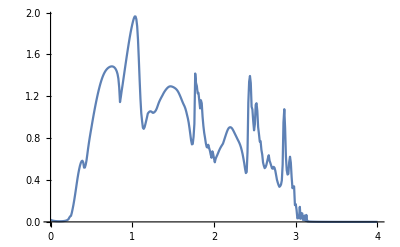

```mathematica
ListPlot[final10,Joined->True]
```

```mathematica
Export["/home/shardulmukim/Desktop/7AGNR_TRA/transmission/7imp/epis710.csv",final10]
```

/home/shardulmukim/Desktop/7AGNR_TRA/transmission/7imp/epis710.csv

```mathematica
{{2,m2[[51,2]]},{3,m3[[51,2]]},{4,m4[[51,2]]},{5,m5[[51,2]]},{6,m6[[51,2]]},{7,m7[[51,2]]},{8,m8[[51,2]]},{9,n1[[51,2]]},{10,n2[[51,2]]},{11,n3[[51,2]]},{12,n4[[51,2]]},{13,n5[[51,2]]},{14,n6[[51,2]]},{15,n7[[51,2]]},{16,n8[[51,2]]},{17,o1[[51,2]]},{18,o2[[51,2]]},{19,o3[[51,2]]},{20,o4[[51,2]]},{21,o5[[51,2]]},{22,o6[[51,2]]},{23,o7[[51,2]]},{24,o8[[51,2]]},{25,p1[[51,2]]},{26,p2[[51,2]]},{27,p3[[51,2]]},{28,p4[[51,2]]},{29,p5[[51,2]]},{30,p6[[51,2]]},{31,p7[[51,2]]},{32,p8[[51,2]]},{33,q1[[51,2]]},{34,q2[[51,2]]},{35,q3[[51,2]]},{36,q4[[51,2]]},{37,q5[[51,2]]},{38,q6[[51,2]]},{39,q7[[51,2]]},{40,q8[[51,2]]},{41,r1[[51,2]]},{42,r2[[51,2]]},{43,r3[[51,2]]},{44,r4[[51,2]]},{45,r5[[51,2]]},{46,r6[[51,2]]},{47,r7[[51,2]]},{48,r8[[51,2]]}}
```

{{2,0.961541},{3,1.26798},{4,0.939629},{5,0.691154},{6,0.85195},{7,0.879391},{8,0.841486},{9,0.908389},{10,0.865436},{11,1.20461},{12,1.01707},{13,1.27007},{14,0.780868},{15,0.797623},{16,0.910666},{17,1.08083},{18,1.14152},{19,1.07194},{20,0.767852},{21,0.00534301},{22,0.74958},{23,0.898927},{24,0.762206},{25,0.431488},{26,1.23217},{27,0.624555},{28,0.970635},{29,0.68436},{30,0.847655},{31,0.940179},{32,0.0476452},{33,0.671383},{34,0.89608},{35,0.922759},{36,0.860025},{37,1.07648},{38,0.694316},{39,1.18086},{40,0.778179},{41,0.971838},{42,0.929063},{43,0.947618},{44,0.336477},{45,0.813796},{46,0.838062},{47,0.781775},{48,0.320615}}

```mathematica
{{1,Module[{B1=Transpose[{m1[[1;;400]][[;;,1]],(m1[[1;;400,2]]- final[[1;;400,;;]][[;;,2]])^2}]},Integrate[Interpolation[B1][ω],{ω,0.0,0.84}]/84]},{2,Module[{B1=Transpose[{m1[[1;;400]][[;;,1]],(m1[[1;;400,2]]- m2[[1;;400,;;]][[;;,2]])^2}]},Integrate[Interpolation[B1][ω],{ω,0.0,0.84}]/84]},{3,Module[{B1=Transpose[{m1[[1;;400]][[;;,1]],(m1[[1;;400,2]]- m3[[1;;400,;;]][[;;,2]])^2}]},Integrate[Interpolation[B1][ω],{ω,0.0,0.84}]/84]},{4,Module[{B1=Transpose[{m1[[1;;400]][[;;,1]],(m1[[1;;400,2]]- m4[[1;;400,;;]][[;;,2]])^2}]},Integrate[Interpolation[B1][ω],{ω,0.0,0.84}]/84]},{5,Module[{B1=Transpose[{m1[[1;;400]][[;;,1]],(m1[[1;;400,2]]- m5[[1;;400,;;]][[;;,2]])^2}]},Integrate[Interpolation[B1][ω],{ω,0.0,0.84}]/84]},{6,Module[{B1=Transpose[{m1[[1;;400]][[;;,1]],(m1[[1;;400,2]]- m7[[1;;400,;;]][[;;,2]])^2}]},Integrate[Interpolation[B1][ω],{ω,0.0,0.84}]/84]},{7,Module[{B1=Transpose[{m1[[1;;400]][[;;,1]],(m1[[1;;400,2]]- m6[[1;;400,;;]][[;;,2]])^2}]},Integrate[Interpolation[B1][ω],{ω,0.0,0.84}]/84]},{8,Module[{B1=Transpose[{m1[[1;;400]][[;;,1]],(m1[[1;;400,2]]- n1[[1;;400,;;]][[;;,2]])^2}]},Integrate[Interpolation[B1][ω],{ω,0.0,0.84}]/84]},{9.,Module[{B1=Transpose[{m1[[1;;400]][[;;,1]],(m1[[1;;400,2]]- n2[[1;;400,;;]][[;;,2]])^2}]},Integrate[Interpolation[B1][ω],{ω,0.0,0.84}]/84]},{10,Module[{B1=Transpose[{m1[[1;;400]][[;;,1]],(m1[[1;;400,2]]- n3[[1;;400,;;]][[;;,2]])^2}]},Integrate[Interpolation[B1][ω],{ω,0.0,0.84}]/84]},{11,Module[{B1=Transpose[{m1[[1;;400]][[;;,1]],(m1[[1;;400,2]]- n4[[1;;400,;;]][[;;,2]])^2}]},Integrate[Interpolation[B1][ω],{ω,0.0,0.84}]/84]},{12,Module[{B1=Transpose[{m1[[1;;400]][[;;,1]],(m1[[1;;400,2]]- n5[[1;;400,;;]][[;;,2]])^2}]},Integrate[Interpolation[B1][ω],{ω,0.0,0.84}]/84]},{13,Module[{B1=Transpose[{m1[[1;;400]][[;;,1]],(m1[[1;;400,2]]- n6[[1;;400,;;]][[;;,2]])^2}]},Integrate[Interpolation[B1][ω],{ω,0.0,0.84}]/84]},{14,Module[{B1=Transpose[{m1[[1;;400]][[;;,1]],(m1[[1;;400,2]]- n7[[1;;400,;;]][[;;,2]])^2}]},Integrate[Interpolation[B1][ω],{ω,0.0,0.84}]/84]},{15,Module[{B1=Transpose[{m1[[1;;400]][[;;,1]],(m1[[1;;400,2]]- o1[[1;;400,;;]][[;;,2]])^2}]},Integrate[Interpolation[B1][ω],{ω,0.0,0.84}]/84]},{16,Module[{B1=Transpose[{m1[[1;;400]][[;;,1]],(m1[[1;;400,2]]- o2[[1;;400,;;]][[;;,2]])^2}]},Integrate[Interpolation[B1][ω],{ω,0.0,0.84}]/84]},{17,Module[{B1=Transpose[{m1[[1;;400]][[;;,1]],(m1[[1;;400,2]]- o3[[1;;400,;;]][[;;,2]])^2}]},Integrate[Interpolation[B1][ω],{ω,0.0,0.84}]/84]},{18,Module[{B1=Transpose[{m1[[1;;400]][[;;,1]],(m1[[1;;400,2]]- o4[[1;;400,;;]][[;;,2]])^2}]},Integrate[Interpolation[B1][ω],{ω,0.0,0.84}]/84]},{19,Module[{B1=Transpose[{m1[[1;;400]][[;;,1]],(m1[[1;;400,2]]- o5[[1;;400,;;]][[;;,2]])^2}]},Integrate[Interpolation[B1][ω],{ω,0.0,0.84}]/84]},{20,Module[{B1=Transpose[{m1[[1;;400]][[;;,1]],(m1[[1;;400,2]]- o6[[1;;400,;;]][[;;,2]])^2}]},Integrate[Interpolation[B1][ω],{ω,0.0,0.84}]/84]},{21,Module[{B1=Transpose[{m1[[1;;400]][[;;,1]],(m1[[1;;400,2]]- o7[[1;;400,;;]][[;;,2]])^2}]},Integrate[Interpolation[B1][ω],{ω,0.0,0.84}]/84]},{22,Module[{B1=Transpose[{m1[[1;;400]][[;;,1]],(m1[[1;;400,2]]- p1[[1;;400,;;]][[;;,2]])^2}]},Integrate[Interpolation[B1][ω],{ω,0.0,0.84}]/84]},{23,Module[{B1=Transpose[{m1[[1;;400]][[;;,1]],(m1[[1;;400,2]]- p2[[1;;400,;;]][[;;,2]])^2}]},Integrate[Interpolation[B1][ω],{ω,0.0,0.84}]/84]},{24,Module[{B1=Transpose[{m1[[1;;400]][[;;,1]],(m1[[1;;400,2]]- p3[[1;;400,;;]][[;;,2]])^2}]},Integrate[Interpolation[B1][ω],{ω,0.0,0.84}]/84]},{25,Module[{B1=Transpose[{m1[[1;;400]][[;;,1]],(m1[[1;;400,2]]- p4[[1;;400,;;]][[;;,2]])^2}]},Integrate[Interpolation[B1][ω],{ω,0.0,0.84}]/84]},{26,Module[{B1=Transpose[{m1[[1;;400]][[;;,1]],(m1[[1;;400,2]]- p5[[1;;400,;;]][[;;,2]])^2}]},Integrate[Interpolation[B1][ω],{ω,0.0,0.84}]/84]},{27,Module[{B1=Transpose[{m1[[1;;400]][[;;,1]],(m1[[1;;400,2]]- p6[[1;;400,;;]][[;;,2]])^2}]},Integrate[Interpolation[B1][ω],{ω,0.0,0.84}]/84]},{28,Module[{B1=Transpose[{m1[[1;;400]][[;;,1]],(m1[[1;;400,2]]- p7[[1;;400,;;]][[;;,2]])^2}]},Integrate[Interpolation[B1][ω],{ω,0.0,0.84}]/84]},{29,Module[{B1=Transpose[{m1[[1;;400]][[;;,1]],(m1[[1;;400,2]]- q7[[1;;400,;;]][[;;,2]])^2}]},Integrate[Interpolation[B1][ω],{ω,0.0,0.84}]/84]},{30,Module[{B1=Transpose[{m1[[1;;400]][[;;,1]],(m1[[1;;400,2]]- q6[[1;;400,;;]][[;;,2]])^2}]},Integrate[Interpolation[B1][ω],{ω,0.0,0.84}]/84]},{31,Module[{B1=Transpose[{m1[[1;;400]][[;;,1]],(m1[[1;;400,2]]- q5[[1;;400,;;]][[;;,2]])^2}]},Integrate[Interpolation[B1][ω],{ω,0.0,0.84}]/84]},{32,Module[{B1=Transpose[{m1[[1;;400]][[;;,1]],(m1[[1;;400,2]]- q4[[1;;400,;;]][[;;,2]])^2}]},Integrate[Interpolation[B1][ω],{ω,0.0,0.84}]/84]},{33,Module[{B1=Transpose[{m1[[1;;400]][[;;,1]],(m1[[1;;400,2]]- q3[[1;;400,;;]][[;;,2]])^2}]},Integrate[Interpolation[B1][ω],{ω,0.0,0.84}]/84]},{34,Module[{B1=Transpose[{m1[[1;;400]][[;;,1]],(m1[[1;;400,2]]- q2[[1;;400,;;]][[;;,2]])^2}]},Integrate[Interpolation[B1][ω],{ω,0.0,0.84}]/84]},{35,Module[{B1=Transpose[{m1[[1;;400]][[;;,1]],(m1[[1;;400,2]]- q1[[1;;400,;;]][[;;,2]])^2}]},Integrate[Interpolation[B1][ω],{ω,0.0,0.84}]/84]},{36,Module[{B1=Transpose[{m1[[1;;400]][[;;,1]],(m1[[1;;400,2]]- r1[[1;;400,;;]][[;;,2]])^2}]},Integrate[Interpolation[B1][ω],{ω,0.0,0.84}]/84]},{37,Module[{B1=Transpose[{m1[[1;;400]][[;;,1]],(m1[[1;;400,2]]- r2[[1;;400,;;]][[;;,2]])^2}]},Integrate[Interpolation[B1][ω],{ω,0.0,0.84}]/84]},{38,Module[{B1=Transpose[{m1[[1;;400]][[;;,1]],(m1[[1;;400,2]]- r3[[1;;400,;;]][[;;,2]])^2}]},Integrate[Interpolation[B1][ω],{ω,0.0,0.84}]/84]},{39,Module[{B1=Transpose[{m1[[1;;400]][[;;,1]],(m1[[1;;400,2]]- r4[[1;;400,;;]][[;;,2]])^2}]},Integrate[Interpolation[B1][ω],{ω,0.0,0.84}]/84]},{40,Module[{B1=Transpose[{m1[[1;;400]][[;;,1]],(m1[[1;;400,2]]- r5[[1;;400,;;]][[;;,2]])^2}]},Integrate[Interpolation[B1][ω],{ω,0.0,0.84}]/84]},{41,Module[{B1=Transpose[{m1[[1;;400]][[;;,1]],(m1[[1;;400,2]]- r6[[1;;400,;;]][[;;,2]])^2}]},Integrate[Interpolation[B1][ω],{ω,0.0,0.84}]/84]},{42,Module[{B1=Transpose[{m1[[1;;400]][[;;,1]],(m1[[1;;400,2]]- r7[[1;;400,;;]][[;;,2]])^2}]},Integrate[Interpolation[B1][ω],{ω,0.0,0.84}]/84]},{43,Module[{B1=Transpose[{m1[[1;;400]][[;;,1]],(m1[[1;;400,2]]- r8[[1;;400,;;]][[;;,2]])^2}]},Integrate[Interpolation[B1][ω],{ω,0.0,0.84}]/84]},{44,Module[{B1=Transpose[{m1[[1;;400]][[;;,1]],(m1[[1;;400,2]]- m8[[1;;400,;;]][[;;,2]])^2}]},Integrate[Interpolation[B1][ω],{ω,0.0,0.84}]/84]},{45,Module[{B1=Transpose[{m1[[1;;400]][[;;,1]],(m1[[1;;400,2]]- n8[[1;;400,;;]][[;;,2]])^2}]},Integrate[Interpolation[B1][ω],{ω,0.0,0.84}]/84]},{46,Module[{B1=Transpose[{m1[[1;;400]][[;;,1]],(m1[[1;;400,2]]- o8[[1;;400,;;]][[;;,2]])^2}]},Integrate[Interpolation[B1][ω],{ω,0.0,0.84}]/84]},{47,Module[{B1=Transpose[{m1[[1;;400]][[;;,1]],(m1[[1;;400,2]]- p8[[1;;400,;;]][[;;,2]])^2}]},Integrate[Interpolation[B1][ω],{ω,0.0,0.84}]/84]},{48,Module[{B1=Transpose[{m1[[1;;400]][[;;,1]],(m1[[1;;400,2]]- q8[[1;;400,;;]][[;;,2]])^2}]},Integrate[Interpolation[B1][ω],{ω,0.0,0.84}]/84]}}
```

{{1,0.00357064},{2,0.00344128},{3,0.00404635},{4,0.00435128},{5,0.00402836},{6,0.00281602},{7,0.00359212},{8,0.00381868},{9.,0.00197539},{10,0.00396552},{11,0.00294238},{12,0.00390257},{13,0.00199834},{14,0.00348098},{15,0.00296477},{16,0.00352576},{17,0.00346873},{18,0.00307982},{19,0.00521647},{20,0.00276461},{21,0.00266068},{22,0.00374408},{23,0.00524316},{24,0.00830283},{25,0.00369291},{26,0.00270976},{27,0.00233135},{28,0.00537029},{29,0.00390872},{30,0.00409475},{31,0.00319007},{32,0.00398055},{33,0.00434509},{34,0.00452453},{35,0.00376734},{36,0.00518554},{37,0.00483042},{38,0.00207605},{39,0.00221051},{40,0.00282051},{41,0.00264785},{42,0.00766258},{43,0.00263894},{44,0.00562069},{45,0.00454486},{46,0.00517611},{47,0.007999},{48,0.0021864}}

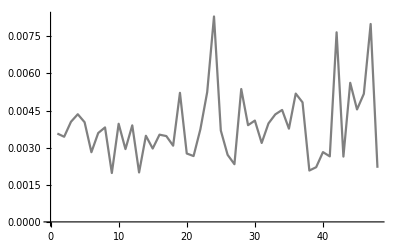

```mathematica
ListPlot[%331,Joined->True,PlotStyle->Gray]
```

```mathematica
{{1,Module[{B1=Transpose[{m1[[1;;400]][[;;,1]],(m1[[1;;400,2]]- final[[1;;400,;;]][[;;,2]])^2}]},Integrate[Interpolation[B1][ω],{ω,0.85,1.76}]/91]},{2,Module[{B1=Transpose[{m1[[1;;400]][[;;,1]],(m1[[1;;400,2]]- m2[[1;;400,;;]][[;;,2]])^2}]},Integrate[Interpolation[B1][ω],{ω,0.85,1.76}]/91]},{3,Module[{B1=Transpose[{m1[[1;;400]][[;;,1]],(m1[[1;;400,2]]- m3[[1;;400,;;]][[;;,2]])^2}]},Integrate[Interpolation[B1][ω],{ω,0.85,1.76}]/91]},{4,Module[{B1=Transpose[{m1[[1;;400]][[;;,1]],(m1[[1;;400,2]]- m4[[1;;400,;;]][[;;,2]])^2}]},Integrate[Interpolation[B1][ω],{ω,0.85,1.76}]/91]},{5,Module[{B1=Transpose[{m1[[1;;400]][[;;,1]],(m1[[1;;400,2]]- m5[[1;;400,;;]][[;;,2]])^2}]},Integrate[Interpolation[B1][ω],{ω,0.85,1.76}]/91]},{6,Module[{B1=Transpose[{m1[[1;;400]][[;;,1]],(m1[[1;;400,2]]- m7[[1;;400,;;]][[;;,2]])^2}]},Integrate[Interpolation[B1][ω],{ω,0.85,1.76}]/91]},{7,Module[{B1=Transpose[{m1[[1;;400]][[;;,1]],(m1[[1;;400,2]]- m6[[1;;400,;;]][[;;,2]])^2}]},Integrate[Interpolation[B1][ω],{ω,0.85,1.76}]/91]},{8,Module[{B1=Transpose[{m1[[1;;400]][[;;,1]],(m1[[1;;400,2]]- n1[[1;;400,;;]][[;;,2]])^2}]},Integrate[Interpolation[B1][ω],{ω,0.85,1.76}]/91]},{9.,Module[{B1=Transpose[{m1[[1;;400]][[;;,1]],(m1[[1;;400,2]]- n2[[1;;400,;;]][[;;,2]])^2}]},Integrate[Interpolation[B1][ω],{ω,0.85,1.76}]/91]},{10,Module[{B1=Transpose[{m1[[1;;400]][[;;,1]],(m1[[1;;400,2]]- n3[[1;;400,;;]][[;;,2]])^2}]},Integrate[Interpolation[B1][ω],{ω,0.85,1.76}]/91]},{11,Module[{B1=Transpose[{m1[[1;;400]][[;;,1]],(m1[[1;;400,2]]- n4[[1;;400,;;]][[;;,2]])^2}]},Integrate[Interpolation[B1][ω],{ω,0.85,1.76}]/91]},{12,Module[{B1=Transpose[{m1[[1;;400]][[;;,1]],(m1[[1;;400,2]]- n5[[1;;400,;;]][[;;,2]])^2}]},Integrate[Interpolation[B1][ω],{ω,0.85,1.76}]/91]},{13,Module[{B1=Transpose[{m1[[1;;400]][[;;,1]],(m1[[1;;400,2]]- n6[[1;;400,;;]][[;;,2]])^2}]},Integrate[Interpolation[B1][ω],{ω,0.85,1.76}]/91]},{14,Module[{B1=Transpose[{m1[[1;;400]][[;;,1]],(m1[[1;;400,2]]- n7[[1;;400,;;]][[;;,2]])^2}]},Integrate[Interpolation[B1][ω],{ω,0.85,1.76}]/91]},{15,Module[{B1=Transpose[{m1[[1;;400]][[;;,1]],(m1[[1;;400,2]]- o1[[1;;400,;;]][[;;,2]])^2}]},Integrate[Interpolation[B1][ω],{ω,0.85,1.76}]/91]},{16,Module[{B1=Transpose[{m1[[1;;400]][[;;,1]],(m1[[1;;400,2]]- o2[[1;;400,;;]][[;;,2]])^2}]},Integrate[Interpolation[B1][ω],{ω,0.85,1.76}]/91]},{17,Module[{B1=Transpose[{m1[[1;;400]][[;;,1]],(m1[[1;;400,2]]- o3[[1;;400,;;]][[;;,2]])^2}]},Integrate[Interpolation[B1][ω],{ω,0.85,1.76}]/91]},{18,Module[{B1=Transpose[{m1[[1;;400]][[;;,1]],(m1[[1;;400,2]]- o4[[1;;400,;;]][[;;,2]])^2}]},Integrate[Interpolation[B1][ω],{ω,0.85,1.76}]/91]},{19,Module[{B1=Transpose[{m1[[1;;400]][[;;,1]],(m1[[1;;400,2]]- o5[[1;;400,;;]][[;;,2]])^2}]},Integrate[Interpolation[B1][ω],{ω,0.85,1.76}]/91]},{20,Module[{B1=Transpose[{m1[[1;;400]][[;;,1]],(m1[[1;;400,2]]- o6[[1;;400,;;]][[;;,2]])^2}]},Integrate[Interpolation[B1][ω],{ω,0.85,1.76}]/91]},{21,Module[{B1=Transpose[{m1[[1;;400]][[;;,1]],(m1[[1;;400,2]]- o7[[1;;400,;;]][[;;,2]])^2}]},Integrate[Interpolation[B1][ω],{ω,0.85,1.76}]/91]},{22,Module[{B1=Transpose[{m1[[1;;400]][[;;,1]],(m1[[1;;400,2]]- p1[[1;;400,;;]][[;;,2]])^2}]},Integrate[Interpolation[B1][ω],{ω,0.85,1.76}]/91]},{23,Module[{B1=Transpose[{m1[[1;;400]][[;;,1]],(m1[[1;;400,2]]- p2[[1;;400,;;]][[;;,2]])^2}]},Integrate[Interpolation[B1][ω],{ω,0.85,1.76}]/91]},{24,Module[{B1=Transpose[{m1[[1;;400]][[;;,1]],(m1[[1;;400,2]]- p3[[1;;400,;;]][[;;,2]])^2}]},Integrate[Interpolation[B1][ω],{ω,0.85,1.76}]/91]},{25,Module[{B1=Transpose[{m1[[1;;400]][[;;,1]],(m1[[1;;400,2]]- p4[[1;;400,;;]][[;;,2]])^2}]},Integrate[Interpolation[B1][ω],{ω,0.85,1.76}]/91]},{26,Module[{B1=Transpose[{m1[[1;;400]][[;;,1]],(m1[[1;;400,2]]- p5[[1;;400,;;]][[;;,2]])^2}]},Integrate[Interpolation[B1][ω],{ω,0.85,1.76}]/91]},{27,Module[{B1=Transpose[{m1[[1;;400]][[;;,1]],(m1[[1;;400,2]]- p6[[1;;400,;;]][[;;,2]])^2}]},Integrate[Interpolation[B1][ω],{ω,0.85,1.76}]/91]},{28,Module[{B1=Transpose[{m1[[1;;400]][[;;,1]],(m1[[1;;400,2]]- p7[[1;;400,;;]][[;;,2]])^2}]},Integrate[Interpolation[B1][ω],{ω,0.85,1.76}]/91]},{29,Module[{B1=Transpose[{m1[[1;;400]][[;;,1]],(m1[[1;;400,2]]- q7[[1;;400,;;]][[;;,2]])^2}]},Integrate[Interpolation[B1][ω],{ω,0.85,1.76}]/91]},{30,Module[{B1=Transpose[{m1[[1;;400]][[;;,1]],(m1[[1;;400,2]]- q6[[1;;400,;;]][[;;,2]])^2}]},Integrate[Interpolation[B1][ω],{ω,0.85,1.76}]/91]},{31,Module[{B1=Transpose[{m1[[1;;400]][[;;,1]],(m1[[1;;400,2]]- q5[[1;;400,;;]][[;;,2]])^2}]},Integrate[Interpolation[B1][ω],{ω,0.85,1.76}]/91]},{32,Module[{B1=Transpose[{m1[[1;;400]][[;;,1]],(m1[[1;;400,2]]- q4[[1;;400,;;]][[;;,2]])^2}]},Integrate[Interpolation[B1][ω],{ω,0.85,1.76}]/91]},{33,Module[{B1=Transpose[{m1[[1;;400]][[;;,1]],(m1[[1;;400,2]]- q3[[1;;400,;;]][[;;,2]])^2}]},Integrate[Interpolation[B1][ω],{ω,0.85,1.76}]/91]},{34,Module[{B1=Transpose[{m1[[1;;400]][[;;,1]],(m1[[1;;400,2]]- q2[[1;;400,;;]][[;;,2]])^2}]},Integrate[Interpolation[B1][ω],{ω,0.85,1.76}]/91]},{35,Module[{B1=Transpose[{m1[[1;;400]][[;;,1]],(m1[[1;;400,2]]- q1[[1;;400,;;]][[;;,2]])^2}]},Integrate[Interpolation[B1][ω],{ω,0.85,1.76}]/91]},{36,Module[{B1=Transpose[{m1[[1;;400]][[;;,1]],(m1[[1;;400,2]]- r1[[1;;400,;;]][[;;,2]])^2}]},Integrate[Interpolation[B1][ω],{ω,0.85,1.76}]/91]},{37,Module[{B1=Transpose[{m1[[1;;400]][[;;,1]],(m1[[1;;400,2]]- r2[[1;;400,;;]][[;;,2]])^2}]},Integrate[Interpolation[B1][ω],{ω,0.85,1.76}]/91]},{38,Module[{B1=Transpose[{m1[[1;;400]][[;;,1]],(m1[[1;;400,2]]- r3[[1;;400,;;]][[;;,2]])^2}]},Integrate[Interpolation[B1][ω],{ω,0.85,1.76}]/91]},{39,Module[{B1=Transpose[{m1[[1;;400]][[;;,1]],(m1[[1;;400,2]]- r4[[1;;400,;;]][[;;,2]])^2}]},Integrate[Interpolation[B1][ω],{ω,0.85,1.76}]/91]},{40,Module[{B1=Transpose[{m1[[1;;400]][[;;,1]],(m1[[1;;400,2]]- r5[[1;;400,;;]][[;;,2]])^2}]},Integrate[Interpolation[B1][ω],{ω,0.85,1.76}]/91]},{41,Module[{B1=Transpose[{m1[[1;;400]][[;;,1]],(m1[[1;;400,2]]- r6[[1;;400,;;]][[;;,2]])^2}]},Integrate[Interpolation[B1][ω],{ω,0.85,1.76}]/91]},{42,Module[{B1=Transpose[{m1[[1;;400]][[;;,1]],(m1[[1;;400,2]]- r7[[1;;400,;;]][[;;,2]])^2}]},Integrate[Interpolation[B1][ω],{ω,0.85,1.76}]/91]},{43,Module[{B1=Transpose[{m1[[1;;400]][[;;,1]],(m1[[1;;400,2]]- r8[[1;;400,;;]][[;;,2]])^2}]},Integrate[Interpolation[B1][ω],{ω,0.85,1.76}]/91]},{44,Module[{B1=Transpose[{m1[[1;;400]][[;;,1]],(m1[[1;;400,2]]- m8[[1;;400,;;]][[;;,2]])^2}]},Integrate[Interpolation[B1][ω],{ω,0.85,1.76}]/91]},{45,Module[{B1=Transpose[{m1[[1;;400]][[;;,1]],(m1[[1;;400,2]]- n8[[1;;400,;;]][[;;,2]])^2}]},Integrate[Interpolation[B1][ω],{ω,0.85,1.76}]/91]},{46,Module[{B1=Transpose[{m1[[1;;400]][[;;,1]],(m1[[1;;400,2]]- o8[[1;;400,;;]][[;;,2]])^2}]},Integrate[Interpolation[B1][ω],{ω,0.85,1.76}]/91]},{47,Module[{B1=Transpose[{m1[[1;;400]][[;;,1]],(m1[[1;;400,2]]- p8[[1;;400,;;]][[;;,2]])^2}]},Integrate[Interpolation[B1][ω],{ω,0.85,1.76}]/91]},{48,Module[{B1=Transpose[{m1[[1;;400]][[;;,1]],(m1[[1;;400,2]]- q8[[1;;400,;;]][[;;,2]])^2}]},Integrate[Interpolation[B1][ω],{ω,0.85,1.76}]/91]}}
```

{{1,0.0206374},{2,0.0126742},{3,0.0186505},{4,0.0235588},{5,0.0246486},{6,0.0227693},{7,0.0288591},{8,0.0206507},{9.,0.032794},{10,0.0255777},{11,0.0269629},{12,0.0174792},{13,0.0177645},{14,0.0136701},{15,0.021093},{16,0.023206},{17,0.021768},{18,0.0261519},{19,0.0228903},{20,0.0204417},{21,0.0243733},{22,0.0290237},{23,0.018044},{24,0.0202251},{25,0.0187856},{26,0.0266014},{27,0.0200262},{28,0.0217921},{29,0.025719},{30,0.0284792},{31,0.0182351},{32,0.023613},{33,0.0232016},{34,0.026129},{35,0.0187081},{36,0.0268412},{37,0.0234343},{38,0.0262806},{39,0.0248249},{40,0.021087},{41,0.0182516},{42,0.0215373},{43,0.0176553},{44,0.0194236},{45,0.0138543},{46,0.0176365},{47,0.0152486},{48,0.0206169}}

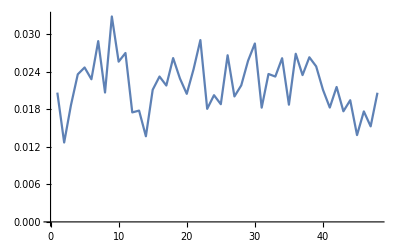

```mathematica
ListPlot[%334,Joined->True]
```

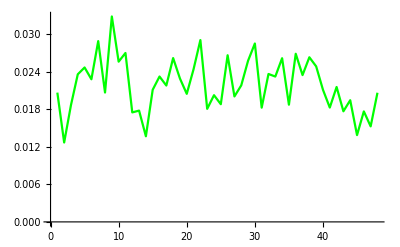

```mathematica
ListPlot[%328,Joined->True,PlotStyle->Green]
```

```mathematica
{{1,Module[{B1=Transpose[{m1[[1;;400]][[;;,1]],(m1[[1;;400,2]]- final[[1;;400,;;]][[;;,2]])^2}]},Integrate[Interpolation[B1][ω],{ω,1.8,4}]/220]},{2,Module[{B1=Transpose[{m1[[1;;400]][[;;,1]],(m1[[1;;400,2]]- m2[[1;;400,;;]][[;;,2]])^2}]},Integrate[Interpolation[B1][ω],{ω,1.8,4}]/220]},{3,Module[{B1=Transpose[{m1[[1;;400]][[;;,1]],(m1[[1;;400,2]]- m3[[1;;400,;;]][[;;,2]])^2}]},Integrate[Interpolation[B1][ω],{ω,1.8,4}]/220]},{4,Module[{B1=Transpose[{m1[[1;;400]][[;;,1]],(m1[[1;;400,2]]- m4[[1;;400,;;]][[;;,2]])^2}]},Integrate[Interpolation[B1][ω],{ω,1.8,4}]/220]},{5,Module[{B1=Transpose[{m1[[1;;400]][[;;,1]],(m1[[1;;400,2]]- m5[[1;;400,;;]][[;;,2]])^2}]},Integrate[Interpolation[B1][ω],{ω,1.8,4}]/220]},{6,Module[{B1=Transpose[{m1[[1;;400]][[;;,1]],(m1[[1;;400,2]]- m7[[1;;400,;;]][[;;,2]])^2}]},Integrate[Interpolation[B1][ω],{ω,1.8,4}]/220]},{7,Module[{B1=Transpose[{m1[[1;;400]][[;;,1]],(m1[[1;;400,2]]- m6[[1;;400,;;]][[;;,2]])^2}]},Integrate[Interpolation[B1][ω],{ω,1.8,4}]/220]},{8,Module[{B1=Transpose[{m1[[1;;400]][[;;,1]],(m1[[1;;400,2]]- n1[[1;;400,;;]][[;;,2]])^2}]},Integrate[Interpolation[B1][ω],{ω,1.8,4}]/220]},{9.,Module[{B1=Transpose[{m1[[1;;400]][[;;,1]],(m1[[1;;400,2]]- n2[[1;;400,;;]][[;;,2]])^2}]},Integrate[Interpolation[B1][ω],{ω,1.8,4}]/220]},{10,Module[{B1=Transpose[{m1[[1;;400]][[;;,1]],(m1[[1;;400,2]]- n3[[1;;400,;;]][[;;,2]])^2}]},Integrate[Interpolation[B1][ω],{ω,1.8,4}]/220]},{11,Module[{B1=Transpose[{m1[[1;;400]][[;;,1]],(m1[[1;;400,2]]- n4[[1;;400,;;]][[;;,2]])^2}]},Integrate[Interpolation[B1][ω],{ω,1.8,4}]/220]},{12,Module[{B1=Transpose[{m1[[1;;400]][[;;,1]],(m1[[1;;400,2]]- n5[[1;;400,;;]][[;;,2]])^2}]},Integrate[Interpolation[B1][ω],{ω,1.8,4}]/220]},{13,Module[{B1=Transpose[{m1[[1;;400]][[;;,1]],(m1[[1;;400,2]]- n6[[1;;400,;;]][[;;,2]])^2}]},Integrate[Interpolation[B1][ω],{ω,1.8,4}]/220]},{14,Module[{B1=Transpose[{m1[[1;;400]][[;;,1]],(m1[[1;;400,2]]- n7[[1;;400,;;]][[;;,2]])^2}]},Integrate[Interpolation[B1][ω],{ω,1.8,4}]/220]},{15,Module[{B1=Transpose[{m1[[1;;400]][[;;,1]],(m1[[1;;400,2]]- o1[[1;;400,;;]][[;;,2]])^2}]},Integrate[Interpolation[B1][ω],{ω,1.8,4}]/220]},{16,Module[{B1=Transpose[{m1[[1;;400]][[;;,1]],(m1[[1;;400,2]]- o2[[1;;400,;;]][[;;,2]])^2}]},Integrate[Interpolation[B1][ω],{ω,1.8,4}]/220]},{17,Module[{B1=Transpose[{m1[[1;;400]][[;;,1]],(m1[[1;;400,2]]- o3[[1;;400,;;]][[;;,2]])^2}]},Integrate[Interpolation[B1][ω],{ω,1.8,4}]/220]},{18,Module[{B1=Transpose[{m1[[1;;400]][[;;,1]],(m1[[1;;400,2]]- o4[[1;;400,;;]][[;;,2]])^2}]},Integrate[Interpolation[B1][ω],{ω,1.8,4}]/220]},{19,Module[{B1=Transpose[{m1[[1;;400]][[;;,1]],(m1[[1;;400,2]]- o5[[1;;400,;;]][[;;,2]])^2}]},Integrate[Interpolation[B1][ω],{ω,1.8,4}]/220]},{20,Module[{B1=Transpose[{m1[[1;;400]][[;;,1]],(m1[[1;;400,2]]- o6[[1;;400,;;]][[;;,2]])^2}]},Integrate[Interpolation[B1][ω],{ω,1.8,4}]/220]},{21,Module[{B1=Transpose[{m1[[1;;400]][[;;,1]],(m1[[1;;400,2]]- o7[[1;;400,;;]][[;;,2]])^2}]},Integrate[Interpolation[B1][ω],{ω,1.8,4}]/220]},{22,Module[{B1=Transpose[{m1[[1;;400]][[;;,1]],(m1[[1;;400,2]]- p1[[1;;400,;;]][[;;,2]])^2}]},Integrate[Interpolation[B1][ω],{ω,1.8,4}]/220]},{23,Module[{B1=Transpose[{m1[[1;;400]][[;;,1]],(m1[[1;;400,2]]- p2[[1;;400,;;]][[;;,2]])^2}]},Integrate[Interpolation[B1][ω],{ω,1.8,4}]/220]},{24,Module[{B1=Transpose[{m1[[1;;400]][[;;,1]],(m1[[1;;400,2]]- p3[[1;;400,;;]][[;;,2]])^2}]},Integrate[Interpolation[B1][ω],{ω,1.8,4}]/220]},{25,Module[{B1=Transpose[{m1[[1;;400]][[;;,1]],(m1[[1;;400,2]]- p4[[1;;400,;;]][[;;,2]])^2}]},Integrate[Interpolation[B1][ω],{ω,1.8,4}]/220]},{26,Module[{B1=Transpose[{m1[[1;;400]][[;;,1]],(m1[[1;;400,2]]- p5[[1;;400,;;]][[;;,2]])^2}]},Integrate[Interpolation[B1][ω],{ω,1.8,4}]/220]},{27,Module[{B1=Transpose[{m1[[1;;400]][[;;,1]],(m1[[1;;400,2]]- p6[[1;;400,;;]][[;;,2]])^2}]},Integrate[Interpolation[B1][ω],{ω,1.8,4}]/220]},{28,Module[{B1=Transpose[{m1[[1;;400]][[;;,1]],(m1[[1;;400,2]]- p7[[1;;400,;;]][[;;,2]])^2}]},Integrate[Interpolation[B1][ω],{ω,1.8,4}]/220]},{29,Module[{B1=Transpose[{m1[[1;;400]][[;;,1]],(m1[[1;;400,2]]- q7[[1;;400,;;]][[;;,2]])^2}]},Integrate[Interpolation[B1][ω],{ω,1.8,4}]/220]},{30,Module[{B1=Transpose[{m1[[1;;400]][[;;,1]],(m1[[1;;400,2]]- q6[[1;;400,;;]][[;;,2]])^2}]},Integrate[Interpolation[B1][ω],{ω,1.8,4}]/220]},{31,Module[{B1=Transpose[{m1[[1;;400]][[;;,1]],(m1[[1;;400,2]]- q5[[1;;400,;;]][[;;,2]])^2}]},Integrate[Interpolation[B1][ω],{ω,1.8,4}]/220]},{32,Module[{B1=Transpose[{m1[[1;;400]][[;;,1]],(m1[[1;;400,2]]- q4[[1;;400,;;]][[;;,2]])^2}]},Integrate[Interpolation[B1][ω],{ω,1.8,4}]/220]},{33,Module[{B1=Transpose[{m1[[1;;400]][[;;,1]],(m1[[1;;400,2]]- q3[[1;;400,;;]][[;;,2]])^2}]},Integrate[Interpolation[B1][ω],{ω,1.8,4}]/220]},{34,Module[{B1=Transpose[{m1[[1;;400]][[;;,1]],(m1[[1;;400,2]]- q2[[1;;400,;;]][[;;,2]])^2}]},Integrate[Interpolation[B1][ω],{ω,1.8,4}]/220]},{35,Module[{B1=Transpose[{m1[[1;;400]][[;;,1]],(m1[[1;;400,2]]- q1[[1;;400,;;]][[;;,2]])^2}]},Integrate[Interpolation[B1][ω],{ω,1.8,4}]/220]},{36,Module[{B1=Transpose[{m1[[1;;400]][[;;,1]],(m1[[1;;400,2]]- r1[[1;;400,;;]][[;;,2]])^2}]},Integrate[Interpolation[B1][ω],{ω,1.8,4}]/220]},{37,Module[{B1=Transpose[{m1[[1;;400]][[;;,1]],(m1[[1;;400,2]]- r2[[1;;400,;;]][[;;,2]])^2}]},Integrate[Interpolation[B1][ω],{ω,1.8,4}]/220]},{38,Module[{B1=Transpose[{m1[[1;;400]][[;;,1]],(m1[[1;;400,2]]- r3[[1;;400,;;]][[;;,2]])^2}]},Integrate[Interpolation[B1][ω],{ω,1.8,4}]/220]},{39,Module[{B1=Transpose[{m1[[1;;400]][[;;,1]],(m1[[1;;400,2]]- r4[[1;;400,;;]][[;;,2]])^2}]},Integrate[Interpolation[B1][ω],{ω,1.8,4}]/220]},{40,Module[{B1=Transpose[{m1[[1;;400]][[;;,1]],(m1[[1;;400,2]]- r5[[1;;400,;;]][[;;,2]])^2}]},Integrate[Interpolation[B1][ω],{ω,1.8,4}]/220]},{41,Module[{B1=Transpose[{m1[[1;;400]][[;;,1]],(m1[[1;;400,2]]- r6[[1;;400,;;]][[;;,2]])^2}]},Integrate[Interpolation[B1][ω],{ω,1.8,4}]/220]},{42,Module[{B1=Transpose[{m1[[1;;400]][[;;,1]],(m1[[1;;400,2]]- r7[[1;;400,;;]][[;;,2]])^2}]},Integrate[Interpolation[B1][ω],{ω,1.8,4}]/220]},{43,Module[{B1=Transpose[{m1[[1;;400]][[;;,1]],(m1[[1;;400,2]]- r8[[1;;400,;;]][[;;,2]])^2}]},Integrate[Interpolation[B1][ω],{ω,1.8,4}]/220]},{44,Module[{B1=Transpose[{m1[[1;;400]][[;;,1]],(m1[[1;;400,2]]- m8[[1;;400,;;]][[;;,2]])^2}]},Integrate[Interpolation[B1][ω],{ω,1.8,4}]/220]},{45,Module[{B1=Transpose[{m1[[1;;400]][[;;,1]],(m1[[1;;400,2]]- n8[[1;;400,;;]][[;;,2]])^2}]},Integrate[Interpolation[B1][ω],{ω,1.8,4}]/220]},{46,Module[{B1=Transpose[{m1[[1;;400]][[;;,1]],(m1[[1;;400,2]]- o8[[1;;400,;;]][[;;,2]])^2}]},Integrate[Interpolation[B1][ω],{ω,1.8,4}]/220]},{47,Module[{B1=Transpose[{m1[[1;;400]][[;;,1]],(m1[[1;;400,2]]- p8[[1;;400,;;]][[;;,2]])^2}]},Integrate[Interpolation[B1][ω],{ω,1.8,4}]/220]},{48,Module[{B1=Transpose[{m1[[1;;400]][[;;,1]],(m1[[1;;400,2]]- q8[[1;;400,;;]][[;;,2]])^2}]},Integrate[Interpolation[B1][ω],{ω,1.8,4}]/220]}}
```

InterpolatingFunction::dmvali: The integration endpoint 4 in dimension 1 lies outside the range of data in the interpolating function. Extrapolation will be used.

General::stop: Further output of InterpolatingFunction::dmvali will be suppressed during this calculation.

{{1,0.00277521},{2,0.00634228},{3,0.00508547},{4,0.00443295},{5,0.0054485},{6,0.00408327},{7,0.00566438},{8,0.00310688},{9.,0.00416274},{10,0.00605265},{11,0.00434036},{12,0.00284706},{13,0.00381557},{14,0.00313305},{15,0.00562669},{16,0.0031085},{17,0.00409457},{18,0.00450012},{19,0.00342357},{20,0.00323305},{21,0.00341218},{22,0.00383393},{23,0.0027093},{24,0.0030803},{25,0.00358474},{26,0.00519058},{27,0.00467343},{28,0.00401891},{29,0.00283471},{30,0.00439048},{31,0.00255899},{32,0.00382227},{33,0.00413432},{34,0.00396837},{35,0.00227926},{36,0.00508994},{37,0.00658186},{38,0.0037438},{39,0.00520881},{40,0.00239624},{41,0.00441413},{42,0.00701287},{43,0.00444979},{44,0.00437462},{45,0.00378766},{46,0.0060387},{47,0.00293647},{48,0.00340986}}

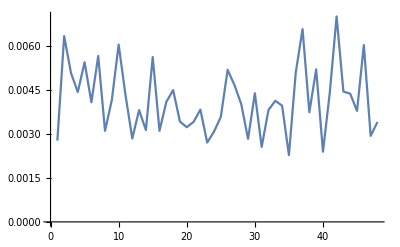

```mathematica
ListPlot[%336,Joined->True]
```

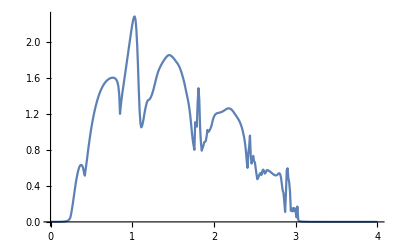

```mathematica
ListLinePlot[final]
```

```mathematica
{{1,Module[{B1=Transpose[{m1[[1;;400]][[;;,1]],(final[[1;;400,2]]- final[[1;;400,;;]][[;;,2]])^2}]},Integrate[Interpolation[B1][ω],{ω,0.85,1.76}]/91]},{2,Module[{B1=Transpose[{m1[[1;;400]][[;;,1]],(final[[1;;400,2]]- m2[[1;;400,;;]][[;;,2]])^2}]},Integrate[Interpolation[B1][ω],{ω,0.85,1.76}]/91]},{3,Module[{B1=Transpose[{m1[[1;;400]][[;;,1]],(final[[1;;400,2]]- m3[[1;;400,;;]][[;;,2]])^2}]},Integrate[Interpolation[B1][ω],{ω,0.85,1.76}]/91]},{4,Module[{B1=Transpose[{m1[[1;;400]][[;;,1]],(final[[1;;400,2]]- m4[[1;;400,;;]][[;;,2]])^2}]},Integrate[Interpolation[B1][ω],{ω,0.85,1.76}]/91]},{5,Module[{B1=Transpose[{m1[[1;;400]][[;;,1]],(final[[1;;400,2]]- m5[[1;;400,;;]][[;;,2]])^2}]},Integrate[Interpolation[B1][ω],{ω,0.85,1.76}]/91]},{6,Module[{B1=Transpose[{m1[[1;;400]][[;;,1]],(final[[1;;400,2]]- m7[[1;;400,;;]][[;;,2]])^2}]},Integrate[Interpolation[B1][ω],{ω,0.85,1.76}]/91]},{7,Module[{B1=Transpose[{m1[[1;;400]][[;;,1]],(final[[1;;400,2]]- m6[[1;;400,;;]][[;;,2]])^2}]},Integrate[Interpolation[B1][ω],{ω,0.85,1.76}]/91]},{8,Module[{B1=Transpose[{m1[[1;;400]][[;;,1]],(final[[1;;400,2]]- n1[[1;;400,;;]][[;;,2]])^2}]},Integrate[Interpolation[B1][ω],{ω,0.85,1.76}]/91]},{9.,Module[{B1=Transpose[{m1[[1;;400]][[;;,1]],(final[[1;;400,2]]- n2[[1;;400,;;]][[;;,2]])^2}]},Integrate[Interpolation[B1][ω],{ω,0.85,1.76}]/91]},{10,Module[{B1=Transpose[{m1[[1;;400]][[;;,1]],(final[[1;;400,2]]- n3[[1;;400,;;]][[;;,2]])^2}]},Integrate[Interpolation[B1][ω],{ω,0.85,1.76}]/91]},{11,Module[{B1=Transpose[{m1[[1;;400]][[;;,1]],(final[[1;;400,2]]- n4[[1;;400,;;]][[;;,2]])^2}]},Integrate[Interpolation[B1][ω],{ω,0.85,1.76}]/91]},{12,Module[{B1=Transpose[{m1[[1;;400]][[;;,1]],(final[[1;;400,2]]- n5[[1;;400,;;]][[;;,2]])^2}]},Integrate[Interpolation[B1][ω],{ω,0.85,1.76}]/91]},{13,Module[{B1=Transpose[{m1[[1;;400]][[;;,1]],(final[[1;;400,2]]- n6[[1;;400,;;]][[;;,2]])^2}]},Integrate[Interpolation[B1][ω],{ω,0.85,1.76}]/91]},{14,Module[{B1=Transpose[{m1[[1;;400]][[;;,1]],(final[[1;;400,2]]- n7[[1;;400,;;]][[;;,2]])^2}]},Integrate[Interpolation[B1][ω],{ω,0.85,1.76}]/91]},{15,Module[{B1=Transpose[{m1[[1;;400]][[;;,1]],(final[[1;;400,2]]- o1[[1;;400,;;]][[;;,2]])^2}]},Integrate[Interpolation[B1][ω],{ω,0.85,1.76}]/91]},{16,Module[{B1=Transpose[{m1[[1;;400]][[;;,1]],(final[[1;;400,2]]- o2[[1;;400,;;]][[;;,2]])^2}]},Integrate[Interpolation[B1][ω],{ω,0.85,1.76}]/91]},{17,Module[{B1=Transpose[{m1[[1;;400]][[;;,1]],(final[[1;;400,2]]- o3[[1;;400,;;]][[;;,2]])^2}]},Integrate[Interpolation[B1][ω],{ω,0.85,1.76}]/91]},{18,Module[{B1=Transpose[{m1[[1;;400]][[;;,1]],(final[[1;;400,2]]- o4[[1;;400,;;]][[;;,2]])^2}]},Integrate[Interpolation[B1][ω],{ω,0.85,1.76}]/91]},{19,Module[{B1=Transpose[{m1[[1;;400]][[;;,1]],(final[[1;;400,2]]- o5[[1;;400,;;]][[;;,2]])^2}]},Integrate[Interpolation[B1][ω],{ω,0.85,1.76}]/91]},{20,Module[{B1=Transpose[{m1[[1;;400]][[;;,1]],(final[[1;;400,2]]- o6[[1;;400,;;]][[;;,2]])^2}]},Integrate[Interpolation[B1][ω],{ω,0.85,1.76}]/91]},{21,Module[{B1=Transpose[{m1[[1;;400]][[;;,1]],(final[[1;;400,2]]- o7[[1;;400,;;]][[;;,2]])^2}]},Integrate[Interpolation[B1][ω],{ω,0.85,1.76}]/91]},{22,Module[{B1=Transpose[{m1[[1;;400]][[;;,1]],(final[[1;;400,2]]- p1[[1;;400,;;]][[;;,2]])^2}]},Integrate[Interpolation[B1][ω],{ω,0.85,1.76}]/91]},{23,Module[{B1=Transpose[{m1[[1;;400]][[;;,1]],(final[[1;;400,2]]- p2[[1;;400,;;]][[;;,2]])^2}]},Integrate[Interpolation[B1][ω],{ω,0.85,1.76}]/91]},{24,Module[{B1=Transpose[{m1[[1;;400]][[;;,1]],(final[[1;;400,2]]- p3[[1;;400,;;]][[;;,2]])^2}]},Integrate[Interpolation[B1][ω],{ω,0.85,1.76}]/91]},{25,Module[{B1=Transpose[{m1[[1;;400]][[;;,1]],(final[[1;;400,2]]- p4[[1;;400,;;]][[;;,2]])^2}]},Integrate[Interpolation[B1][ω],{ω,0.85,1.76}]/91]},{26,Module[{B1=Transpose[{m1[[1;;400]][[;;,1]],(final[[1;;400,2]]- p5[[1;;400,;;]][[;;,2]])^2}]},Integrate[Interpolation[B1][ω],{ω,0.85,1.76}]/91]},{27,Module[{B1=Transpose[{m1[[1;;400]][[;;,1]],(final[[1;;400,2]]- p6[[1;;400,;;]][[;;,2]])^2}]},Integrate[Interpolation[B1][ω],{ω,0.85,1.76}]/91]},{28,Module[{B1=Transpose[{m1[[1;;400]][[;;,1]],(final[[1;;400,2]]- p7[[1;;400,;;]][[;;,2]])^2}]},Integrate[Interpolation[B1][ω],{ω,0.85,1.76}]/91]},{29,Module[{B1=Transpose[{m1[[1;;400]][[;;,1]],(final[[1;;400,2]]- q7[[1;;400,;;]][[;;,2]])^2}]},Integrate[Interpolation[B1][ω],{ω,0.85,1.76}]/91]},{30,Module[{B1=Transpose[{m1[[1;;400]][[;;,1]],(final[[1;;400,2]]- q6[[1;;400,;;]][[;;,2]])^2}]},Integrate[Interpolation[B1][ω],{ω,0.85,1.76}]/91]},{31,Module[{B1=Transpose[{m1[[1;;400]][[;;,1]],(final[[1;;400,2]]- q5[[1;;400,;;]][[;;,2]])^2}]},Integrate[Interpolation[B1][ω],{ω,0.85,1.76}]/91]},{32,Module[{B1=Transpose[{m1[[1;;400]][[;;,1]],(final[[1;;400,2]]- q4[[1;;400,;;]][[;;,2]])^2}]},Integrate[Interpolation[B1][ω],{ω,0.85,1.76}]/91]},{33,Module[{B1=Transpose[{m1[[1;;400]][[;;,1]],(final[[1;;400,2]]- q3[[1;;400,;;]][[;;,2]])^2}]},Integrate[Interpolation[B1][ω],{ω,0.85,1.76}]/91]},{34,Module[{B1=Transpose[{m1[[1;;400]][[;;,1]],(final[[1;;400,2]]- q2[[1;;400,;;]][[;;,2]])^2}]},Integrate[Interpolation[B1][ω],{ω,0.85,1.76}]/91]},{35,Module[{B1=Transpose[{m1[[1;;400]][[;;,1]],(final[[1;;400,2]]- q1[[1;;400,;;]][[;;,2]])^2}]},Integrate[Interpolation[B1][ω],{ω,0.85,1.76}]/91]},{36,Module[{B1=Transpose[{m1[[1;;400]][[;;,1]],(final[[1;;400,2]]- r1[[1;;400,;;]][[;;,2]])^2}]},Integrate[Interpolation[B1][ω],{ω,0.85,1.76}]/91]},{37,Module[{B1=Transpose[{m1[[1;;400]][[;;,1]],(final[[1;;400,2]]- r2[[1;;400,;;]][[;;,2]])^2}]},Integrate[Interpolation[B1][ω],{ω,0.85,1.76}]/91]},{38,Module[{B1=Transpose[{m1[[1;;400]][[;;,1]],(final[[1;;400,2]]- r3[[1;;400,;;]][[;;,2]])^2}]},Integrate[Interpolation[B1][ω],{ω,0.85,1.76}]/91]},{39,Module[{B1=Transpose[{m1[[1;;400]][[;;,1]],(final[[1;;400,2]]- r4[[1;;400,;;]][[;;,2]])^2}]},Integrate[Interpolation[B1][ω],{ω,0.85,1.76}]/91]},{40,Module[{B1=Transpose[{m1[[1;;400]][[;;,1]],(final[[1;;400,2]]- r5[[1;;400,;;]][[;;,2]])^2}]},Integrate[Interpolation[B1][ω],{ω,0.85,1.76}]/91]},{41,Module[{B1=Transpose[{m1[[1;;400]][[;;,1]],(final[[1;;400,2]]- r6[[1;;400,;;]][[;;,2]])^2}]},Integrate[Interpolation[B1][ω],{ω,0.85,1.76}]/91]},{42,Module[{B1=Transpose[{m1[[1;;400]][[;;,1]],(final[[1;;400,2]]- r7[[1;;400,;;]][[;;,2]])^2}]},Integrate[Interpolation[B1][ω],{ω,0.85,1.76}]/91]},{43,Module[{B1=Transpose[{m1[[1;;400]][[;;,1]],(final[[1;;400,2]]- r8[[1;;400,;;]][[;;,2]])^2}]},Integrate[Interpolation[B1][ω],{ω,0.85,1.76}]/91]},{44,Module[{B1=Transpose[{m1[[1;;400]][[;;,1]],(final[[1;;400,2]]- m8[[1;;400,;;]][[;;,2]])^2}]},Integrate[Interpolation[B1][ω],{ω,0.85,1.76}]/91]},{45,Module[{B1=Transpose[{m1[[1;;400]][[;;,1]],(final[[1;;400,2]]- n8[[1;;400,;;]][[;;,2]])^2}]},Integrate[Interpolation[B1][ω],{ω,0.85,1.76}]/91]},{46,Module[{B1=Transpose[{m1[[1;;400]][[;;,1]],(final[[1;;400,2]]- o8[[1;;400,;;]][[;;,2]])^2}]},Integrate[Interpolation[B1][ω],{ω,0.85,1.76}]/91]},{47,Module[{B1=Transpose[{m1[[1;;400]][[;;,1]],(final[[1;;400,2]]- p8[[1;;400,;;]][[;;,2]])^2}]},Integrate[Interpolation[B1][ω],{ω,0.85,1.76}]/91]},{48,Module[{B1=Transpose[{m1[[1;;400]][[;;,1]],(final[[1;;400,2]]- q8[[1;;400,;;]][[;;,2]])^2}]},Integrate[Interpolation[B1][ω],{ω,0.85,1.76}]/91]}}
```

{{1,0.},{2,0.00137458},{3,0.00280664},{4,0.00031019},{5,0.00144201},{6,0.00216869},{7,0.00182359},{8,0.000262513},{9.,0.00314889},{10,0.001467},{11,0.00126106},{12,0.00135951},{13,0.000322893},{14,0.00177753},{15,0.000419488},{16,0.00112322},{17,0.00148674},{18,0.00131948},{19,0.000537709},{20,0.000657378},{21,0.00151337},{22,0.00289701},{23,0.00115089},{24,0.000935191},{25,0.000324563},{26,0.000978549},{27,0.00124357},{28,0.000399991},{29,0.000829086},{30,0.00194957},{31,0.000718119},{32,0.00095845},{33,0.000710194},{34,0.00151737},{35,0.00125653},{36,0.00190475},{37,0.00225125},{38,0.000868075},{39,0.00172322},{40,0.00186855},{41,0.000839306},{42,0.00181663},{43,0.00160757},{44,0.00052242},{45,0.0014986},{46,0.00113106},{47,0.001118},{48,0.00108195}}

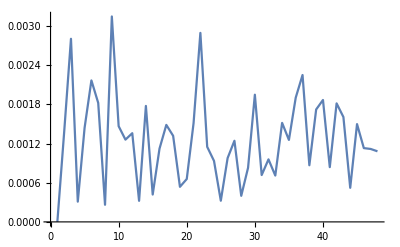

```mathematica
ListPlot[%343,Joined->True]
```

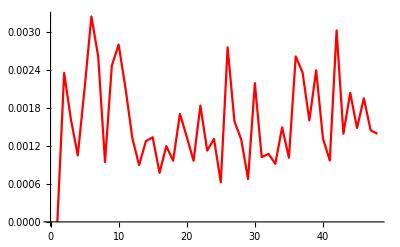

```mathematica
ListPlot[%340,Joined->True,PlotStyle->Red]
```

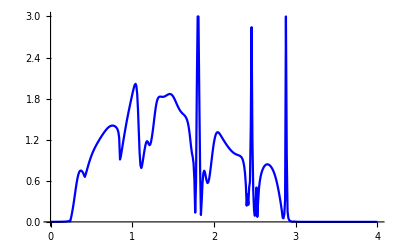

```mathematica
ListLinePlot[m4,PlotStyle->Blue]
```

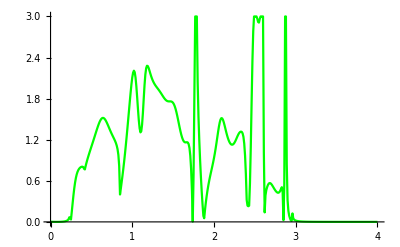

-Graphics-

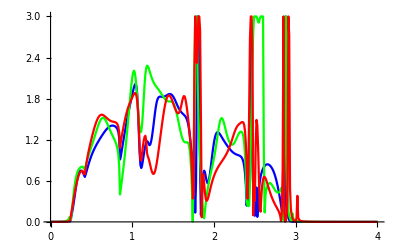

```mathematica
Show[%345,%349,%347]
```

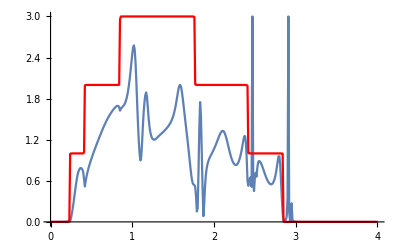

```mathematica
Show[ListLinePlot[q4],ListLinePlot[m1,PlotStyle->Red],PlotRange->All]
```

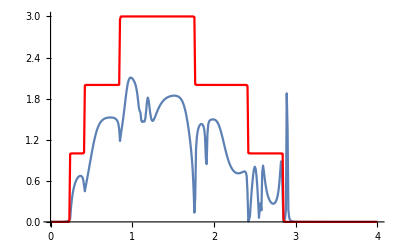

```mathematica
Show[ListLinePlot[p4],ListLinePlot[m1,PlotStyle->Red],PlotRange->All]
```

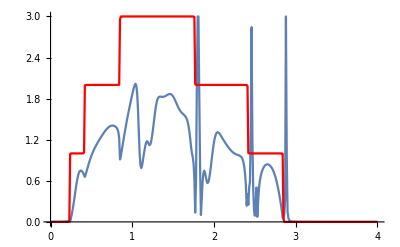

```mathematica
Show[ListLinePlot[m4],ListLinePlot[m1,PlotStyle->Red],PlotRange->All]
```

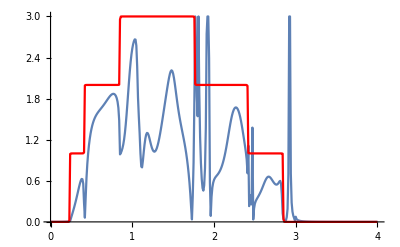

```mathematica
Show[ListLinePlot[n4],ListLinePlot[m1,PlotStyle->Red],PlotRange->All]
```

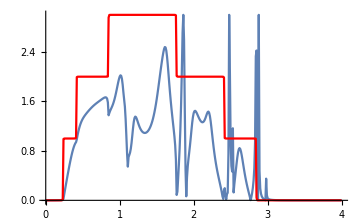

```mathematica
Show[ListLinePlot[r4],ListLinePlot[m1,PlotStyle->Red],PlotRange->All]
```

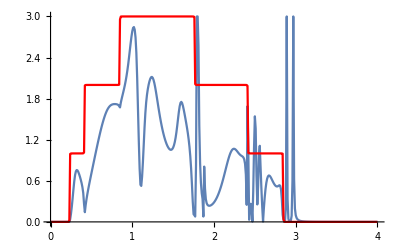

```mathematica
Show[ListLinePlot[r2],ListLinePlot[m1,PlotStyle->Red],PlotRange->All]
```

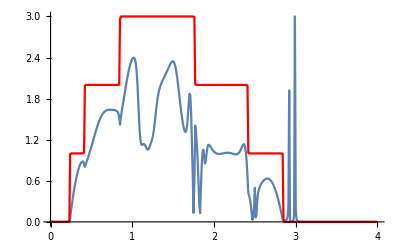

```mathematica
Show[ListLinePlot[r6],ListLinePlot[m1,PlotStyle->Red],PlotRange->All]
```

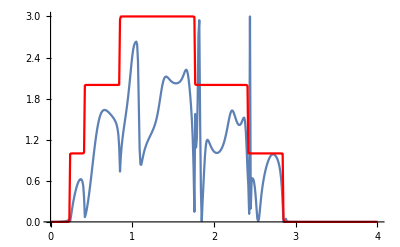

```mathematica
Show[ListLinePlot[p2],ListLinePlot[m1,PlotStyle->Red],PlotRange->All]
```

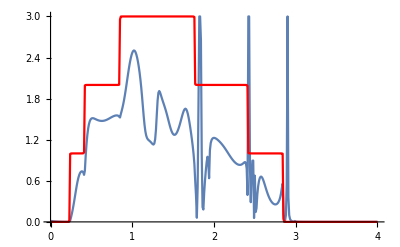

```mathematica
Show[ListLinePlot[p6],ListLinePlot[m1,PlotStyle->Red],PlotRange->All]
```

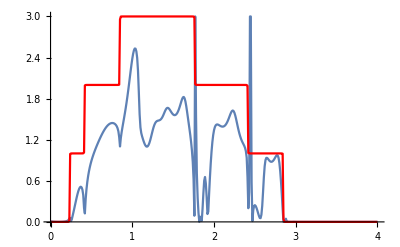

```mathematica
Show[ListLinePlot[p7],ListLinePlot[m1,PlotStyle->Red],PlotRange->All]
```